
-Graphics-
Previous notebook		Content		Next notebook

## Chapter. Vectors and bivectors(2024-06-12)

## Initialization section

To verify computations presented below you need 1) load package  2) evaluate definitions/shortcuts  specific to this section  2) define specific coordinate system/space. You can specify different coordinate system before any computation as many times as you wish. On the contrary, package load and evaluation of definitions cells should be evaluated only once in the very beginning.

### Load GA.nb notebook

WAIT until evaluation of cell is finished to be sure that no errors were produced.

```mathematica
NotebookEvaluate[FileNameJoin[{ParentDirectory[NotebookDirectory[EvaluationNotebook[]]],"GA.nb"}]]
```

### Definitions and shortcuts

Realization of  determinant formula given in A. Macdonald,  ”Linear and Geometric Algebra” p.157, which utilizes inner product (note reciprocal basis vectors)

a⋀b...⋀z=det(a\[InnerProduct]𝕖^1 | a\[InnerProduct]𝕖^2 | ... | a\[InnerProduct]𝕖^n
b\[InnerProduct]𝕖^1 | b\[InnerProduct]𝕖^2 | ... | b\[InnerProduct]𝕖^n
... | ... | ... | ...
z\[InnerProduct]𝕖^1 | z\[InnerProduct]𝕖^2 | ... | z\[InnerProduct]𝕖^n) I

```mathematica
outerProductViaDeterminant[vecOutProd_OuterProduct]:=Module[{theAlgebra=First[Cases[First[vecOutProd],_Cl,Infinity]],theBase,theVectors,thePseudoscalar,vecOutProdList=List@@(vecOutProd)},theBase=gaDefineOrthonormalBasis[theAlgebra];theVectors=(gaIndexUp[DeleteCases[gaGetMV[theBase,{1}],0]])/.{-1->1};
thePseudoscalar=Last[theBase];Det[Outer[gaPE[InnerProduct[##]]&,vecOutProdList,theVectors]]*thePseudoscalar]/;Union[gaGradeList/@(List@@vecOutProd)]==={{1}}&&Length[vecOutProd]===(Plus@@First[Cases[vecOutProd,Cl[p_,q_,___],Infinity]])
```

Some shortcuts for vectors and bivectors, which will be used for compact formula testing. Note, testAlgebra keyword

```mathematica
(* vectors *)
a1:=gaGeneralMultivector[a,testAlgebra,{1}];
b1:=gaGeneralMultivector[b,testAlgebra,{1}];
c1:=gaGeneralMultivector[c,testAlgebra,{1}];
d1:=gaGeneralMultivector[d,testAlgebra,{1}];
f1:=gaGeneralMultivector[f,testAlgebra,{1}];
(*bivectors*)
𝒜1:=gaGeneralMultivector[𝒜,testAlgebra,{2}];
ℬ1:=gaGeneralMultivector[ℬ,testAlgebra,{2}];
𝒞1:=gaGeneralMultivector[𝒞,testAlgebra,{2}];
(*general multivectors*)
A1:=gaGeneralMultivector[A,testAlgebra];
B1:=gaGeneralMultivector[B,testAlgebra];
F1:=gaGeneralMultivector[F,testAlgebra];
```

### Repair TEX import and protect generated inline cells (delete once editing of the notebook is finished )

```mathematica
System`Convert`TeXImportDump`TeXImport[args__]/;!TrueQ[pleaseFixAlignment]=.
```

```mathematica
fixEquationAlignment={"Columns"->{Right,{Left}},"Rows"->{{Baseline}}};
DownValues[System`Convert`TeXImportDump`TeXImport]=Join[{HoldPattern[System`Convert`TeXImportDump`TeXImport[args__]/;!TrueQ[pleaseFixAlignment]]:>Block[{pleaseFixAlignment=True},System`Convert`TeXImportDump`TeXImport[args]/.
Cell[TextData[{" ",Cell[b_,___],___}],___]:>b/.
g_GridBox:>Join[g,GridBox[GridBoxAlignment->fixEquationAlignment,GridBoxSpacings->{"Columns"->{Offset[0.27999
999999999997],{Offset[0.]},Offset[0.27999999999999997]},"Rows"->{Offset[0.2],{Offset[0.4]},Offset[0.2]}}]]]},DownValues[System`Convert`TeXImportDump`TeXImport]];
```

If one needs to add additional TEX command definitions add them to “Mathematica/13.2.0/SystemFiles/IncludeFiles/TEXImport/latex.tnb” file!

Here is how one can insert link to pdf file in text cell: first prepare a button, then copy/paste it into text cell

```mathematica
url=FileNameJoin[{NotebookDirectory[EvaluationNotebook[]],"BibliographySources","Staples_2011_0c960527d4b2564cbe000000.pdf"}];
Button[Style["mathematica.pdf","Subsection"],SystemOpen[url],Appearance->"Frameless"]
```

```mathematica
Button[Style["Staples2011.pdf","Author",FontColor->Blue],SystemOpen[FileNameJoin[{NotebookDirectory[EvaluationNotebook[]],"BibliographySources","Staples_2011_0c960527d4b2564cbe000000.pdf"}]],Appearance->"Frameless"]
```

Staples2011.pdf

Normal text cell with button, which opens pdf  copied inside "Staples2011.pdf"

Seems that in inline cell  Editable option doesn’t work in versions below 14!.

```mathematica
CreatePalette[Button["Toggle inline cells editable option to false",Module[{inlineCells},inlineCells=Cells/@Cells@InputNotebook[]//Flatten;
If[CurrentValue[#,Editable]===True,SetOptions[#,Editable->False],SetOptions[#,Editable->True]]&/@inlineCells]]]
```

```mathematica
CreatePalette[Button["Replace specific cell background by text color ",Module[{cellsWithBackround},cellsWithBackround=Select[(Cells[InputNotebook[],CellStyle->"Text"]//Flatten),(CurrentValue[#,Background]===RGBColor[0.94, 0.91, 0.88])&];
SetOptions[#,FontWeight->"Bold",
 FontColor->RGBColor[0.6, 0.4, 0.2],Background->None]&/@cellsWithBackround]]]
```

An alternative solution gives curves, not boxes (not acceptable in this case)

```mathematica
ResourceFunction["MaTeXInstall"][]
```

```mathematica
(*\lcow to unset the damage done below*)InputAssistant`TeXStringToBoxes//Unprotect;
InputAssistant`TeXStringToBoxes[s_String]/;TrueQ@useMaTeXQ=.;
InputAssistant`TeXStringToBoxes//Protect;

(*use MaTeX to format inline TeX*)
Needs@"MaTeX`";
useMaTeXMag=1;
useMaTeXBaselineShift=0;
InputAssistant`TeXStringToBoxes//Unprotect;
InputAssistant`TeXStringToBoxes[s_String]/;TrueQ@useMaTeXQ:=AdjustmentBox[ToBoxes@MaTeX[s,Magnification->useMaTeXMag],BoxBaselineShift->useMaTeXBaselineShift];
InputAssistant`TeXStringToBoxes//Protect;

useMaTeXQ=True;
```

## Properties of vectors

Section.Item	Hierarchy of inner, outer and geometric products. The inner (aka dot) product has precedence over outer (aka wedge) product. Both the inner and the outer products have precedence over the
geometric product (GP):



The geometric and outer products are associative,




The inner product is not associative. For example , since the dot product of scalar and  bivector is always zero. However,   except the cases when the vector  is perpendicular to plane .

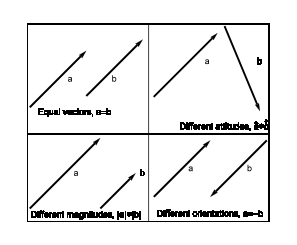

Geometric interpretation of vectors  and : the equivalence under displacement,distinct attitudes,different magnitudes and opposite orientations

Computational verification

Make sure you evaluated “Definitions” subsection before. We have to choose some algebra and define its orthonormal basis. You can change algebra and redefine basis before any computations.

```mathematica
testAlgebra=Cl[4,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

{1,1430,2430,3430,4430,5430,6430,7430,12430,13430,14430,15430,16430,17430,23430,24430,25430,26430,27430,34430,35430,36430,37430,45430,46430,47430,56430,57430,67430,123430,124430,125430,126430,127430,134430,135430,136430,137430,145430,146430,147430,156430,157430,167430,234430,235430,236430,237430,245430,246430,247430,256430,257430,267430,345430,346430,347430,356430,357430,367430,456430,457430,467430,567430,1234430,1235430,1236430,1237430,1245430,1246430,1247430,1256430,1257430,1267430,1345430,1346430,1347430,1356430,1357430,1367430,1456430,1457430,1467430,1567430,2345430,2346430,2347430,2356430,2357430,2367430,2456430,2457430,2467430,2567430,3456430,3457430,3467430,3567430,4567430,12345430,12346430,12347430,12356430,12357430,12367430,12456430,12457430,12467430,12567430,13456430,13457430,13467430,13567430,14567430,23456430,23457430,23467430,23567430,24567430,34567430,123456430,123457430,123467430,123567430,124567430,134567430,234567430,1234567430}

Since all listed properties already were checked, we only remind that inner products (Hestenes inner product \[InnerProduct], left contract \[LeftContract] and right contract \[RightContract]) have highest priority, then comes outer product \[OuterProduct] and last is geometric product \[GeometricProduct]

```mathematica
lhs[testAlgebra]=a1\[InnerProduct]b1\[GeometricProduct]c1
```

(a[1] 1430+a[2] 2430+a[3] 3430+a[4] 4430+a[5] 5430+a[6] 6430+a[7] 7430)\[InnerProduct](b[1] 1430+b[2] 2430+b[3] 3430+b[4] 4430+b[5] 5430+b[6] 6430+b[7] 7430)\[GeometricProduct](c[1] 1430+c[2] 2430+c[3] 3430+c[4] 4430+c[5] 5430+c[6] 6430+c[7] 7430)

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct]b1)\[GeometricProduct]c1
```

(a[1] 1430+a[2] 2430+a[3] 3430+a[4] 4430+a[5] 5430+a[6] 6430+a[7] 7430)\[InnerProduct](b[1] 1430+b[2] 2430+b[3] 3430+b[4] 4430+b[5] 5430+b[6] 6430+b[7] 7430)\[GeometricProduct](c[1] 1430+c[2] 2430+c[3] 3430+c[4] 4430+c[5] 5430+c[6] 6430+c[7] 7430)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

```mathematica
lhs[testAlgebra]=a1\[InnerProduct]b1\[OuterProduct]c1
```

(a[1] 1430+a[2] 2430+a[3] 3430+a[4] 4430+a[5] 5430+a[6] 6430+a[7] 7430)\[InnerProduct](b[1] 1430+b[2] 2430+b[3] 3430+b[4] 4430+b[5] 5430+b[6] 6430+b[7] 7430)\[OuterProduct](c[1] 1430+c[2] 2430+c[3] 3430+c[4] 4430+c[5] 5430+c[6] 6430+c[7] 7430)

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct]b1)\[OuterProduct]c1
```

(a[1] 1430+a[2] 2430+a[3] 3430+a[4] 4430+a[5] 5430+a[6] 6430+a[7] 7430)\[InnerProduct](b[1] 1430+b[2] 2430+b[3] 3430+b[4] 4430+b[5] 5430+b[6] 6430+b[7] 7430)\[OuterProduct](c[1] 1430+c[2] 2430+c[3] 3430+c[4] 4430+c[5] 5430+c[6] 6430+c[7] 7430)

```mathematica
rhs1[testAlgebra]=a1\[InnerProduct](b1\[OuterProduct]c1)
```

(a[1] 1430+a[2] 2430+a[3] 3430+a[4] 4430+a[5] 5430+a[6] 6430+a[7] 7430)\[InnerProduct]((b[1] 1430+b[2] 2430+b[3] 3430+b[4] 4430+b[5] 5430+b[6] 6430+b[7] 7430)\[OuterProduct](c[1] 1430+c[2] 2430+c[3] 3430+c[4] 4430+c[5] 5430+c[6] 6430+c[7] 7430))

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

```mathematica
Collect[lhs[testAlgebra]-rhs1[testAlgebra]//gaPE//Expand,_𝕖]
```

(a[1] b[1] c[1]+a[2] b[1] c[2]+a[3] b[1] c[3]+a[4] b[1] c[4]-a[5] b[1] c[5]-a[6] b[1] c[6]-a[7] b[1] c[7]) 1430+(a[1] b[2] c[1]+a[2] b[2] c[2]+a[3] b[2] c[3]+a[4] b[2] c[4]-a[5] b[2] c[5]-a[6] b[2] c[6]-a[7] b[2] c[7]) 2430+(a[1] b[3] c[1]+a[2] b[3] c[2]+a[3] b[3] c[3]+a[4] b[3] c[4]-a[5] b[3] c[5]-a[6] b[3] c[6]-a[7] b[3] c[7]) 3430+(a[1] b[4] c[1]+a[2] b[4] c[2]+a[3] b[4] c[3]+a[4] b[4] c[4]-a[5] b[4] c[5]-a[6] b[4] c[6]-a[7] b[4] c[7]) 4430+(a[1] b[5] c[1]+a[2] b[5] c[2]+a[3] b[5] c[3]+a[4] b[5] c[4]-a[5] b[5] c[5]-a[6] b[5] c[6]-a[7] b[5] c[7]) 5430+(a[1] b[6] c[1]+a[2] b[6] c[2]+a[3] b[6] c[3]+a[4] b[6] c[4]-a[5] b[6] c[5]-a[6] b[6] c[6]-a[7] b[6] c[7]) 6430+(a[1] b[7] c[1]+a[2] b[7] c[2]+a[3] b[7] c[3]+a[4] b[7] c[4]-a[5] b[7] c[5]-a[6] b[7] c[6]-a[7] b[7] c[7]) 7430

```mathematica
ClearAll[{lhs,rhs,rhs1}];
```

Section.Item	Properties of a general vector a. In real algebra  , , the coefficients  of the vector are real numbers, 

ℝ.

 If algebra is complex then ℂ. Properties of vector in real GA [2  savybe neteisinga, visada , bet kokiai signaturai: pataisyti TEX faile !]

inner product in arbitrary signature space,

outer product

square of vector (scalar)

isotropic (aka null) vector

zero vector

magnitude (length) of vector

reversion of a vector

grade inversion of a vector

Clifford conjugation of a vector

unit vector

signature of a vector

vector as a product of length  and direction

inverse  vector

In complex GAs, the complex conjugation (denoted by asterisk) of one of coefficients  must be included: , where .

Computational verification

Define algebra and orthonormal basis

```mathematica
testAlgebra=Cl[4,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

{1,1430,2430,3430,4430,5430,6430,7430,12430,13430,14430,15430,16430,17430,23430,24430,25430,26430,27430,34430,35430,36430,37430,45430,46430,47430,56430,57430,67430,123430,124430,125430,126430,127430,134430,135430,136430,137430,145430,146430,147430,156430,157430,167430,234430,235430,236430,237430,245430,246430,247430,256430,257430,267430,345430,346430,347430,356430,357430,367430,456430,457430,467430,567430,1234430,1235430,1236430,1237430,1245430,1246430,1247430,1256430,1257430,1267430,1345430,1346430,1347430,1356430,1357430,1367430,1456430,1457430,1467430,1567430,2345430,2346430,2347430,2356430,2357430,2367430,2456430,2457430,2467430,2567430,3456430,3457430,3467430,3567430,4567430,12345430,12346430,12347430,12356430,12357430,12367430,12456430,12457430,12467430,12567430,13456430,13457430,13467430,13567430,14567430,23456430,23457430,23467430,23567430,24567430,34567430,123456430,123457430,123467430,123567430,124567430,134567430,234567430,1234567430}

For arbitrary signature algebra,

```mathematica
a1\[InnerProduct]a1-a1\[GeometricProduct]a1//gaPE
```

0

Outer product for same vector is zero,

```mathematica
a1\[OuterProduct]a1//gaPE
```

0

Vector square  is always a scalar ,

```mathematica
a1\[GeometricProduct]a1//gaPE
```

a[1]^2+a[2]^2+a[3]^2+a[4]^2-a[5]^2-a[6]^2-a[7]^2

Example of isotropic (null) vector  ,

```mathematica
𝕖[1]+𝕖[7]
gaPE[%\[GeometricProduct]%]
```

1430+7430

0

Examples of norms applied to vector (which yields a scalar)

```mathematica
gaNormReverseAbs[a1]
```

√Abs[a[1]^2+a[2]^2+a[3]^2+a[4]^2-a[5]^2-a[6]^2-a[7]^2]

```mathematica
gaNormCliffordConjugateAbs[a1]
```

√Abs[-a[1]^2-a[2]^2-a[3]^2-a[4]^2+a[5]^2+a[6]^2+a[7]^2]

```mathematica
gaNormOfCoefficients[a1]
```

√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2+a[6]^2+a[7]^2)

```mathematica
gaNormDeterminant[a1,Quiet->True]//Simplify
```

√Abs[a[1]^2+a[2]^2+a[3]^2+a[4]^2-a[5]^2-a[6]^2-a[7]^2]

Reverse of vector is the same vector

```mathematica
gaReverse[a1]-a1
```

0

Grade inverse and Clifford conjugate  of vector change sign of the vector

```mathematica
a1
gaGradeInverse[a1]
gaCliffordConjugate[a1]
```

a[1] 1430+a[2] 2430+a[3] 3430+a[4] 4430+a[5] 5430+a[6] 6430+a[7] 7430

-a[1] 1430-a[2] 2430-a[3] 3430-a[4] 4430-a[5] 5430-a[6] 6430-a[7] 7430

-a[1] 1430-a[2] 2430-a[3] 3430-a[4] 4430-a[5] 5430-a[6] 6430-a[7] 7430

Unit vector

```mathematica
a1Num=gaRandomMultivector[testAlgebra,{1}]
a1Unit=gaNormalize[a1Num]
a1UnitByFormula=a1Num/gaNormReverseAbs[a1Num]
```

2 1430+2 2430+7 3430+5 4430+7 5430+2 6430+8 7430

(2 1430+2 2430+7 3430+5 4430+7 5430+2 6430+8 7430)/(√35)

(2 1430+2 2430+7 3430+5 4430+7 5430+2 6430+8 7430)/(√35)

Signature of  vector  can be positive or negative (depends on randomly generated vector: try many times)

```mathematica
a1Unit\[GeometricProduct]a1Unit//gaPE
```

-1

Inverse of vector

```mathematica
a1NumInv=a1Num\[GeometricProduct](1/gaPE[a1Num\[GeometricProduct]a1Num])
```

1/35 (-2 1430-2 2430-7 3430-5 4430-7 5430-2 6430-8 7430)

```mathematica
a1NumInv\[GeometricProduct]a1Num//gaPE
```

1

In complex Clifford algebra you can generate random MV by using proper CoefficientFunction option

```mathematica
gaRandomMultivector[testAlgebra,CoefficientFunction->(Complex[RandomInteger[{-5,5}],RandomInteger[{-5,5}]]&)]
```

(2-5 ⅈ)+4 1430+5 2430-3 3430+(1+ⅈ) 4430+(5+5 ⅈ) 5430+(2-ⅈ) 6430+7430+(4+5 ⅈ) 12430-(1+2 ⅈ) 13430+(4-2 ⅈ) 14430+(1-2 ⅈ) 15430-2 16430+5 17430+4 23430+(1-5 ⅈ) 24430-5 ⅈ 25430+(4+2 ⅈ) 26430-(2-3 ⅈ) 27430+(4-4 ⅈ) 34430-2 35430+(5+2 ⅈ) 36430-ⅈ 37430+(4-5 ⅈ) 45430-(5+4 ⅈ) 46430+3 47430+(5+2 ⅈ) 56430+(3-3 ⅈ) 57430-(4+ⅈ) 67430+(5-3 ⅈ) 123430+(2+5 ⅈ) 124430-2 ⅈ 125430+(2-4 ⅈ) 126430-(5+3 ⅈ) 127430-(3+5 ⅈ) 134430-(2+4 ⅈ) 135430-3 ⅈ 136430+(3-4 ⅈ) 137430-(2-ⅈ) 145430-(1+3 ⅈ) 146430+(1-ⅈ) 147430-(4-ⅈ) 156430-(4-ⅈ) 157430+(3+4 ⅈ) 167430+2 234430-(3-2 ⅈ) 235430-(3+ⅈ) 236430+ⅈ 237430+(5-5 ⅈ) 245430+(5+3 ⅈ) 246430-(1+5 ⅈ) 247430-(2+4 ⅈ) 256430+(4-ⅈ) 257430-(1-4 ⅈ) 267430+3 345430-(2+3 ⅈ) 346430+(2-ⅈ) 347430+(2+3 ⅈ) 356430-2 ⅈ 357430-(4-4 ⅈ) 367430+(2+2 ⅈ) 456430-(4-3 ⅈ) 457430+(2+ⅈ) 467430+(5+2 ⅈ) 567430-2 1234430-(2+5 ⅈ) 1235430-5 ⅈ 1236430+(2+2 ⅈ) 1237430-(4-4 ⅈ) 1245430-(1-4 ⅈ) 1246430-(4+2 ⅈ) 1247430-(5+4 ⅈ) 1256430+(2-ⅈ) 1257430-(5+ⅈ) 1267430+(5+4 ⅈ) 1345430-3 ⅈ 1346430+(5+2 ⅈ) 1347430+(1+4 ⅈ) 1356430-(2-4 ⅈ) 1357430+(2-2 ⅈ) 1367430-4 ⅈ 1456430-(5-2 ⅈ) 1457430+(4+2 ⅈ) 1467430-(4-5 ⅈ) 1567430-(2+2 ⅈ) 2345430+(2+3 ⅈ) 2346430-(3+ⅈ) 2347430+(4+4 ⅈ) 2356430-(3+5 ⅈ) 2357430+2 ⅈ 2367430+(2+ⅈ) 2456430-(2+ⅈ) 2457430+(1-3 ⅈ) 2467430-(4-ⅈ) 2567430-(5+2 ⅈ) 3456430+(2+2 ⅈ) 3457430-ⅈ 3467430+(1-5 ⅈ) 3567430+(4-3 ⅈ) 4567430-(1-4 ⅈ) 12345430-(4-2 ⅈ) 12346430-(4+5 ⅈ) 12347430-(2+2 ⅈ) 12356430-(2+3 ⅈ) 12357430-(2+3 ⅈ) 12367430+(1+4 ⅈ) 12456430+(3-ⅈ) 12457430+(5+5 ⅈ) 12467430+(4+2 ⅈ) 12567430+3 ⅈ 13456430-(3-5 ⅈ) 13457430+(4-5 ⅈ) 13467430-(3+3 ⅈ) 13567430-(2-ⅈ) 14567430+(1-4 ⅈ) 23456430+3 23457430+(4+2 ⅈ) 23467430+(2+3 ⅈ) 23567430-(1+3 ⅈ) 24567430-(5-ⅈ) 34567430-(3+2 ⅈ) 123456430+(1-2 ⅈ) 123457430+(3-5 ⅈ) 123467430-(1+4 ⅈ) 123567430-(1+ⅈ) 124567430-(4+5 ⅈ) 134567430-(5-5 ⅈ) 234567430+1234567430

```mathematica
ClearAll[{a1Num,a1Unit,a1NumInv}];
```

Section.Item	The magnitude of a vector. The magnitude (GA literature lacks consensus here: various definitions of norm are given in unit \ref{norm}). The magnitude usually is associated with the hypervolume of a blade (length of vector, area of bivector etc.), while the norm is a used in a more general sense. It is related with the “normalization” of a GA object, e.g., of a spinor or isotropic vector the magnitude of
which is zero. In the Handbook the symbol  denotes the  magnitude. The absolute value is denoted by . function, while the symbol  is reserved for more general norm of the vector , where ℝ, is denoted |a|. It is a positive definite scalar,, and is directly related with a square of vector , where  is called the signature of vector .  if ; and . The magnitude of zero vector, , is zero . However, when  but , then a is said to be isotropic vector (aka null vector).  Isotropic vector has zero magnitude , therefore, cannot be normalized. However, the “size” of two  isotropic vectors pointing to the same direction may be compared by norm .  Magnitude of a vector in special cases:

general vector,

sum of vectors

vector in Euclidean  algebra

vector in anti-Euclidean  algebra

spacetime  vector ,    algebra

To avoid confusion here  explicitly denotes an absolute value function. The notation will be used when the meaning of  will not be clear from the context.

Computational verification

Many of formulas were already checked.  Repeat checking using different algebra

```mathematica
testAlgebra=Cl[3,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[320,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  320

{1,1320,2320,3320,4320,5320,12320,13320,14320,15320,23320,24320,25320,34320,35320,45320,123320,124320,125320,134320,135320,145320,234320,235320,245320,345320,1234320,1235320,1245320,1345320,2345320,12345320}

Collinear isotropic vectors,  ,  can be compared using gaNormOfCoefficients[ ] norm, since other norms gives zero

```mathematica
isoV1=𝕖[1]-𝕖[4]
gaNormOfCoefficients[isoV1]
isoV2=2𝕖[1]-2𝕖[4]
gaNormOfCoefficients[isoV2]
gaNormReverseAbs[isoV1]
```

1320-4320

√2

2 1320-2 4320

2 √2

0

Vector norm in arbitrary signature

```mathematica
gaNormReverseAbs[a1]
```

√Abs[a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2]

Norm of vector sum

```mathematica
lhs[testAlgebra]=gaNormReverseAbs[a1+b1]
```

√Abs[a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2+2 a[1] b[1]+b[1]^2+2 a[2] b[2]+b[2]^2+2 a[3] b[3]+b[3]^2-2 a[4] b[4]-b[4]^2-2 a[5] b[5]-b[5]^2]

```mathematica
rhs[testAlgebra]=Sqrt[Abs[a1\[GeometricProduct]a1+b1\[GeometricProduct]b1+2 a1\[InnerProduct]b1]]
```

√Abs[(a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320)\[GeometricProduct](a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320)+(b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320)\[GeometricProduct](b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320)+2 ((a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320)\[InnerProduct](b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320))]

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Simplify
```

0

Norm in Euclidean algebra (note absence of abs function)

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
lhs[testAlgebra]=Simplify[gaNormReverseAbs[a1],Assumptions->Element[{a[1],a[2],a[3]},Reals]]
```

√(a[1]^2+a[2]^2+a[3]^2)

```mathematica
rhs[testAlgebra]=Sqrt[gaReverse[a1]\[GeometricProduct]a1]
```

√((a[1] 1300+a[2] 2300+a[3] 3300)\[GeometricProduct](a[1] 1300+a[2] 2300+a[3] 3300))

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE
```

0

Norm in anti-Euclidean algebra (note absence of abs function)

```mathematica
testAlgebra=Cl[0,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[030,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  030

{1,1030,2030,3030,12030,13030,23030,123030}

```mathematica
gaNormReverseAbs[a1]
lhs[testAlgebra]=Simplify[gaNormReverseAbs[a1],Assumptions->Element[{a[1],a[2],a[3]},Reals]]
```

√Abs[-a[1]^2-a[2]^2-a[3]^2]

√(a[1]^2+a[2]^2+a[3]^2)

```mathematica
rhs[testAlgebra]=Sqrt[-gaReverse[a1]\[GeometricProduct]a1]
```

√((-a[1] 1030-a[2] 2030-a[3] 3030)\[GeometricProduct](a[1] 1030+a[2] 2030+a[3] 3030))

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE
```

0

Norm of space time  vectors

```mathematica
testAlgebra=Cl[3,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310}

```mathematica
a1/.{a[1]->x,a[2]->y,a[3]->z,a[4]->t}
gaNormReverseAbs[%]
```

x 1310+y 2310+z 3310+t 4310

√Abs[-t^2+x^2+y^2+z^2]

```mathematica
ClearAll[{isoV1,isoV2,lhs,rhs}];
```

Section.Item	 Inverse vector, multiplication by scalar

inverse of non-null vector

inverse  is collinear to

inner product by scalar

outer and geometric product by

Section.Item	 Vector and scalar selectors.   are the vector.  is a scalar.  is a multivector

the result is the vector

the result is the vector

the result is the scalar

the result is the scalar

## Products of vectors

In GA there are three kinds of main products: geometric, outer and inner (a few variations).

Section.Item	  Geometric meaning of GP. [Sis skyrius labai blogas, daug taisymu, daug neaiskumu. NEBAIGTAS tikrinimas]The geometric product (GP) of two vectors  and , the squares of which satisfy  ⋚  may be interpreted as a rotor multiplied by dilation factor 

.

  [Klaida! bivektoriaus norma nera vektoriu normu sandauga!, ir vienetinis bivektorius,pataisyti TEX faile] is the unit bivector plane where the rotation occurs and   is the angle between vectors measured counterclockwise from  to .  The angle φ in this case can be computed from vector’s inner product .  If  and  are unit vectors then the GP represents a pure (without scaling) rotor  with  [cia  vel neteisingas visas sakinys. Ismesti is TEX  ir is cia Is kur tokios formules?].   If    can’t be applied.    [Neteisinga formule vel], (this happens when the squares of  and  have opposite signs [Neteisinga, visai nesunku rasti tokius koeficientus kus a^2<0,b^2<0, bet (a\[OuterProduct]b)^2>0 cl(2,1) algebroj! Toks paprastas skyrelis o tiek klaidu!]) the rotation is called the boost. The  rotation formula then includes the  hyperbolic functions,

.    [Sita formule neteisinga! Is kur ji paimta?, Cia joks sukimas. Visiskas jovalas ] 

We stress that due to condition  , when    these simple formulas are only valid when bivector in the exponent is a blade (can be expressed as outer product of two vectors as notation  explicitly indicate ).

Computational verification

First, test with algebra with . For large algebras optional random test can be found in the end of this cell group.

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[210,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  210

{1,1210,2210,3210,12210,13210,23210,123210}

If after evaluating a1 below you don’t see it is a vector, then you forgot to evaluate the “Definitions” subsection in the beginning of the notebook.

```mathematica
a1
```

a[1] 1210+a[2] 2210+a[3] 3210

Check of

```mathematica
coefficientRulesNegative={a[1]->1,a[2]->-1,a[3]->0,b[1]->-2,b[2]->-1,b[3]->-1};
negativeSquaredBivector=((a1\[OuterProduct]b1)\[GeometricProduct](1/(gaNormReverseAbs[a1\[OuterProduct]b1])))/.coefficientRulesNegative
```

((1210-2210)\[OuterProduct](-2 1210-2210-3210))/(√7)

```mathematica
negativeSquaredBivector=((a1\[OuterProduct]b1)\[GeometricProduct](1/(gaNormReverseAbs[a1\[OuterProduct]b1])))/.coefficientRulesNegative
```

((1210-2210)\[OuterProduct](-2 1210-2210-3210))/(√7)

```mathematica
negativeSquaredBivector\[GeometricProduct]negativeSquaredBivector//gaPE
```

-1

So, for bivector with negative square we have to check that

```mathematica
lhs[testAlgebra]=((a1\[GeometricProduct]b1)/.coefficientRulesNegative)//gaPE
```

-1-3 12210-13210+23210

An angle between vectors can be computed from their inner product

```mathematica
cosPhi=gaPE[(a1\[InnerProduct]b1)/(gaNormReverseAbs[a1]*gaNormReverseAbs[b1])/.coefficientRulesNegative]
φ=ArcCos[cosPhi];
```

-1/(2 √2)

```mathematica
rhs[testAlgebra]=gaNormReverseAbs[a1]*gaNormReverseAbs[b1]*(Cos[φ]+negativeSquaredBivector*Sin[φ])/.coefficientRulesNegative
```

2 √2 (-1/(2 √2)+((1210-2210)\[OuterProduct](-2 1210-2210-3210))/(2 √2))

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

How to compute functions of MV we will explain in detail in the last section of this notebook

```mathematica
rhs1[testAlgebra]=(gaNormReverseAbs[a1]*gaNormReverseAbs[b1]/.coefficientRulesNegative)*gaExpOfMV[negativeSquaredBivector\[GeometricProduct]φ]
```

√2 ((1-123210)\[GeometricProduct](-1/(2 √2)+(-3 12210-13210+23210)/(2 √2))+(1+123210)\[GeometricProduct](-1/(2 √2)+(-3 12210-13210+23210)/(2 √2)))

```mathematica
lhs[testAlgebra]-rhs1[testAlgebra]//gaPE//Expand
```

0

```mathematica
rhs2[testAlgebra]=(gaNormReverseAbs[a1]*gaNormReverseAbs[b1]/.coefficientRulesNegative)*gaFunctionOfMV[Exp,negativeSquaredBivector\[GeometricProduct]φ,Quiet->True]
```

2 √2 (1/2 ⅇ^(-ⅈ ArcCos[-1/(2 √2)])+1/2 ⅇ^(ⅈ ArcCos[-1/(2 √2)])-(3 ⅈ ⅇ^(-ⅈ ArcCos[-1/(2 √2)]) 12210)/(2 √7)+(3 ⅈ ⅇ^(ⅈ ArcCos[-1/(2 √2)]) 12210)/(2 √7)-(ⅈ ⅇ^(-ⅈ ArcCos[-1/(2 √2)]) 13210)/(2 √7)+(ⅈ ⅇ^(ⅈ ArcCos[-1/(2 √2)]) 13210)/(2 √7)+(ⅈ ⅇ^(-ⅈ ArcCos[-1/(2 √2)]) 23210)/(2 √7)-(ⅈ ⅇ^(ⅈ ArcCos[-1/(2 √2)]) 23210)/(2 √7))

```mathematica
lhs[testAlgebra]-rhs2[testAlgebra]//gaPE
%//FullSimplify
```

-1-3 12210-13210+23210-2 √2 (1/2 ⅇ^(-ⅈ ArcCos[-1/(2 √2)])+1/2 ⅇ^(ⅈ ArcCos[-1/(2 √2)])-(3 ⅈ ⅇ^(-ⅈ ArcCos[-1/(2 √2)]) 12210)/(2 √7)+(3 ⅈ ⅇ^(ⅈ ArcCos[-1/(2 √2)]) 12210)/(2 √7)-(ⅈ ⅇ^(-ⅈ ArcCos[-1/(2 √2)]) 13210)/(2 √7)+(ⅈ ⅇ^(ⅈ ArcCos[-1/(2 √2)]) 13210)/(2 √7)+(ⅈ ⅇ^(-ⅈ ArcCos[-1/(2 √2)]) 23210)/(2 √7)-(ⅈ ⅇ^(ⅈ ArcCos[-1/(2 √2)]) 23210)/(2 √7))

0

Optional test. Let’s check formula for blade of larger algebra, since the statement  is quite general. Looks Ok

```mathematica
testAlgebra=Cl[3,4];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[340,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  340

{1,1340,2340,3340,4340,5340,6340,7340,12340,13340,14340,15340,16340,17340,23340,24340,25340,26340,27340,34340,35340,36340,37340,45340,46340,47340,56340,57340,67340,123340,124340,125340,126340,127340,134340,135340,136340,137340,145340,146340,147340,156340,157340,167340,234340,235340,236340,237340,245340,246340,247340,256340,257340,267340,345340,346340,347340,356340,357340,367340,456340,457340,467340,567340,1234340,1235340,1236340,1237340,1245340,1246340,1247340,1256340,1257340,1267340,1345340,1346340,1347340,1356340,1357340,1367340,1456340,1457340,1467340,1567340,2345340,2346340,2347340,2356340,2357340,2367340,2456340,2457340,2467340,2567340,3456340,3457340,3467340,3567340,4567340,12345340,12346340,12347340,12356340,12357340,12367340,12456340,12457340,12467340,12567340,13456340,13457340,13467340,13567340,14567340,23456340,23457340,23467340,23567340,24567340,34567340,123456340,123457340,123467340,123567340,124567340,134567340,234567340,1234567340}

If after evaluating a1 below you don’t see it is a vector, then you forgot to evaluate the “Definitions” subsection in the beginning of the notebook.

```mathematica
a1
```

a[1] 1340+a[2] 2340+a[3] 3340+a[4] 4340+a[5] 5340+a[6] 6340+a[7] 7340

Create a function that calls itself until blade with negative signature will be generated

```mathematica
generateRandomCoefficientSet[theAlg_,coeffRange_List]:=Thread[Join[gaComponentCoefficientList[gaGeneralMultivector[a,theAlg,{1}],gaOrthonormalBasis[theAlg,"InvDeg[Lex]",{1}]],gaComponentCoefficientList[gaGeneralMultivector[b,theAlg,{1}],gaOrthonormalBasis[theAlg,"InvDeg[Lex]",{1}]]]->RandomInteger[coeffRange,2*gaDimensionOfVectorSpace[theAlg]]]
```

```mathematica
generateNegativeBlade[theAlg_,coeffRange_List]:=Module[{tempCoeff=generateRandomCoefficientSet[theAlg,coeffRange]},
While[(gaPE[(a1\[OuterProduct]b1)\[GeometricProduct](a1\[OuterProduct]b1)]/.tempCoeff)>=0,tempCoeff=generateRandomCoefficientSet[theAlg,coeffRange]];
tempCoeff
]
```

```mathematica
coefficientRulesNegative=generateNegativeBlade[testAlgebra,{-20,20}]
negativeSquaredBivector=((a1\[OuterProduct]b1)\[GeometricProduct](1/(gaNormReverseAbs[a1\[OuterProduct]b1])))/.coefficientRulesNegative
```

{a[1]→-11,a[2]→-2,a[3]→-3,a[4]→-18,a[5]→-7,a[6]→-2,a[7]→19,b[1]→3,b[2]→-5,b[3]→-12,b[4]→-10,b[5]→7,b[6]→8,b[7]→-11}

((-11 1340-2 2340-3 3340-18 4340-7 5340-2 6340+19 7340)\[OuterProduct](3 1340-5 2340-12 3340-10 4340+7 5340+8 6340-11 7340))/(5 √3311)

Check of

```mathematica
negativeSquaredBivector\[GeometricProduct]negativeSquaredBivector//gaPE
```

-1

So, for bivector with negative square we have to check that

```mathematica
lhs[testAlgebra]=((a1\[GeometricProduct]b1)/.coefficientRulesNegative)//gaPE
```

107+61 12340+141 13340+164 14340-56 15340-82 16340+64 17340+9 23340-70 24340-49 25340-26 26340+117 27340-186 34340-105 35340-48 36340+261 37340-196 45340-164 46340+388 47340-42 56340-56 57340-130 67340

An angle between vectors can be computed from their inner product

```mathematica
cosPhi=gaPE[(a1\[InnerProduct]b1)/(gaNormReverseAbs[a1]*gaNormReverseAbs[b1])/.coefficientRulesNegative]
φ=ArcCos[cosPhi];
```

107/(4 √5889)

```mathematica
rhs[testAlgebra]=gaNormReverseAbs[a1]*gaNormReverseAbs[b1]*(Cos[φ]+negativeSquaredBivector*Sin[φ])/.coefficientRulesNegative
```

4 √5889 (107/(4 √5889)+((-11 1340-2 2340-3 3340-18 4340-7 5340-2 6340+19 7340)\[OuterProduct](3 1340-5 2340-12 3340-10 4340+7 5340+8 6340-11 7340))/(4 √5889))

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

How to compute functions of MV we will explain in detail in the last section of this notebook

```mathematica
rhs2[testAlgebra]=(gaNormReverseAbs[a1]*gaNormReverseAbs[b1]/.coefficientRulesNegative)*gaFunctionOfMV[Exp,negativeSquaredBivector\[GeometricProduct]φ,Quiet->True]
```

4 √5889 (1/2 ⅇ^(-ⅈ ArcCos[107/(4 √5889)])+1/2 ⅇ^(ⅈ ArcCos[107/(4 √5889)])+(61 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 12340)/(10 √3311)-(61 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 12340)/(10 √3311)+(141 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 13340)/(10 √3311)-(141 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 13340)/(10 √3311)+(82 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 14340)/(5 √3311)-(82 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 14340)/(5 √3311)-4/5 ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 15340+4/5 ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 15340-(41 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 16340)/(5 √3311)+(41 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 16340)/(5 √3311)+(32 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 17340)/(5 √3311)-(32 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 17340)/(5 √3311)+(9 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 23340)/(10 √3311)-(9 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 23340)/(10 √3311)-ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 24340+ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 24340-7/10 ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 25340+7/10 ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 25340-(13 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 26340)/(5 √3311)+(13 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 26340)/(5 √3311)+(117 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 27340)/(10 √3311)-(117 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 27340)/(10 √3311)-(93 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 34340)/(5 √3311)+(93 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 34340)/(5 √3311)-3/2 ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 35340+3/2 ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 35340-(24 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 36340)/(5 √3311)+(24 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 36340)/(5 √3311)+(261 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 37340)/(10 √3311)-(261 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 37340)/(10 √3311)-14/5 ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 45340+14/5 ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 45340-(82 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 46340)/(5 √3311)+(82 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 46340)/(5 √3311)+(194 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 47340)/(5 √3311)-(194 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 47340)/(5 √3311)-3/5 ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 56340+3/5 ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 56340-4/5 ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 57340+4/5 ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 57340-(13 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 67340)/(√3311)+(13 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 67340)/(√3311))

```mathematica
lhs[testAlgebra]-rhs2[testAlgebra]//gaPE
%//FullSimplify
```

107+61 12340+141 13340+164 14340-56 15340-82 16340+64 17340+9 23340-70 24340-49 25340-26 26340+117 27340-186 34340-105 35340-48 36340+261 37340-196 45340-164 46340+388 47340-42 56340-56 57340-130 67340-4 √5889 (1/2 ⅇ^(-ⅈ ArcCos[107/(4 √5889)])+1/2 ⅇ^(ⅈ ArcCos[107/(4 √5889)])+(61 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 12340)/(10 √3311)-(61 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 12340)/(10 √3311)+(141 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 13340)/(10 √3311)-(141 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 13340)/(10 √3311)+(82 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 14340)/(5 √3311)-(82 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 14340)/(5 √3311)-4/5 ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 15340+4/5 ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 15340-(41 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 16340)/(5 √3311)+(41 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 16340)/(5 √3311)+(32 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 17340)/(5 √3311)-(32 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 17340)/(5 √3311)+(9 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 23340)/(10 √3311)-(9 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 23340)/(10 √3311)-ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 24340+ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 24340-7/10 ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 25340+7/10 ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 25340-(13 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 26340)/(5 √3311)+(13 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 26340)/(5 √3311)+(117 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 27340)/(10 √3311)-(117 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 27340)/(10 √3311)-(93 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 34340)/(5 √3311)+(93 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 34340)/(5 √3311)-3/2 ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 35340+3/2 ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 35340-(24 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 36340)/(5 √3311)+(24 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 36340)/(5 √3311)+(261 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 37340)/(10 √3311)-(261 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 37340)/(10 √3311)-14/5 ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 45340+14/5 ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 45340-(82 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 46340)/(5 √3311)+(82 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 46340)/(5 √3311)+(194 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 47340)/(5 √3311)-(194 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 47340)/(5 √3311)-3/5 ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 56340+3/5 ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 56340-4/5 ⅈ √(7/473) ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 57340+4/5 ⅈ √(7/473) ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 57340-(13 ⅈ ⅇ^(-ⅈ ArcCos[107/(4 √5889)]) 67340)/(√3311)+(13 ⅈ ⅇ^(ⅈ ArcCos[107/(4 √5889)]) 67340)/(√3311))

0

```mathematica
ClearAll[{φ,cosPhi,lhs,rhs,coefficientRulesNegative,negativeSquaredBivector}];
```

Section.Item	 GA product of two vectors.     and  are vectors.   is the unit bivector with   . [taisyta , buvo nelygu. taip pat prideti abs ir apribojimas algebrom prieslaskutinei. Pataisyt TEX]

Computational verification

Will test only identities which were not checked in previous notebooks and cells.

```mathematica
testAlgebra=Cl[4,5];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[450,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  450

{1,1450,2450,3450,4450,5450,6450,7450,8450,9450,12450,13450,14450,15450,16450,17450,18450,19450,23450,24450,25450,26450,27450,28450,29450,34450,35450,36450,37450,38450,39450,45450,46450,47450,48450,49450,56450,57450,58450,59450,67450,68450,69450,78450,79450,89450,123450,124450,125450,126450,127450,128450,129450,134450,135450,136450,137450,138450,139450,145450,146450,147450,148450,149450,156450,157450,158450,159450,167450,168450,169450,178450,179450,189450,234450,235450,236450,237450,238450,239450,245450,246450,247450,248450,249450,256450,257450,258450,259450,267450,268450,269450,278450,279450,289450,345450,346450,347450,348450,349450,356450,357450,358450,359450,367450,368450,369450,378450,379450,389450,456450,457450,458450,459450,467450,468450,469450,478450,479450,489450,567450,568450,569450,578450,579450,589450,678450,679450,689450,789450,1234450,1235450,1236450,1237450,1238450,1239450,1245450,1246450,1247450,1248450,1249450,1256450,1257450,1258450,1259450,1267450,1268450,1269450,1278450,1279450,1289450,1345450,1346450,1347450,1348450,1349450,1356450,1357450,1358450,1359450,1367450,1368450,1369450,1378450,1379450,1389450,1456450,1457450,1458450,1459450,1467450,1468450,1469450,1478450,1479450,1489450,1567450,1568450,1569450,1578450,1579450,1589450,1678450,1679450,1689450,1789450,2345450,2346450,2347450,2348450,2349450,2356450,2357450,2358450,2359450,2367450,2368450,2369450,2378450,2379450,2389450,2456450,2457450,2458450,2459450,2467450,2468450,2469450,2478450,2479450,2489450,2567450,2568450,2569450,2578450,2579450,2589450,2678450,2679450,2689450,2789450,3456450,3457450,3458450,3459450,3467450,3468450,3469450,3478450,3479450,3489450,3567450,3568450,3569450,3578450,3579450,3589450,3678450,3679450,3689450,3789450,4567450,4568450,4569450,4578450,4579450,4589450,4678450,4679450,4689450,4789450,5678450,5679450,5689450,5789450,6789450,12345450,12346450,12347450,12348450,12349450,12356450,12357450,12358450,12359450,12367450,12368450,12369450,12378450,12379450,12389450,12456450,12457450,12458450,12459450,12467450,12468450,12469450,12478450,12479450,12489450,12567450,12568450,12569450,12578450,12579450,12589450,12678450,12679450,12689450,12789450,13456450,13457450,13458450,13459450,13467450,13468450,13469450,13478450,13479450,13489450,13567450,13568450,13569450,13578450,13579450,13589450,13678450,13679450,13689450,13789450,14567450,14568450,14569450,14578450,14579450,14589450,14678450,14679450,14689450,14789450,15678450,15679450,15689450,15789450,16789450,23456450,23457450,23458450,23459450,23467450,23468450,23469450,23478450,23479450,23489450,23567450,23568450,23569450,23578450,23579450,23589450,23678450,23679450,23689450,23789450,24567450,24568450,24569450,24578450,24579450,24589450,24678450,24679450,24689450,24789450,25678450,25679450,25689450,25789450,26789450,34567450,34568450,34569450,34578450,34579450,34589450,34678450,34679450,34689450,34789450,35678450,35679450,35689450,35789450,36789450,45678450,45679450,45689450,45789450,46789450,56789450,123456450,123457450,123458450,123459450,123467450,123468450,123469450,123478450,123479450,123489450,123567450,123568450,123569450,123578450,123579450,123589450,123678450,123679450,123689450,123789450,124567450,124568450,124569450,124578450,124579450,124589450,124678450,124679450,124689450,124789450,125678450,125679450,125689450,125789450,126789450,134567450,134568450,134569450,134578450,134579450,134589450,134678450,134679450,134689450,134789450,135678450,135679450,135689450,135789450,136789450,145678450,145679450,145689450,145789450,146789450,156789450,234567450,234568450,234569450,234578450,234579450,234589450,234678450,234679450,234689450,234789450,235678450,235679450,235689450,235789450,236789450,245678450,245679450,245689450,245789450,246789450,256789450,345678450,345679450,345689450,345789450,346789450,356789450,456789450,1234567450,1234568450,1234569450,1234578450,1234579450,1234589450,1234678450,1234679450,1234689450,1234789450,1235678450,1235679450,1235689450,1235789450,1236789450,1245678450,1245679450,1245689450,1245789450,1246789450,1256789450,1345678450,1345679450,1345689450,1345789450,1346789450,1356789450,1456789450,2345678450,2345679450,2345689450,2345789450,2346789450,2356789450,2456789450,3456789450,12345678450,12345679450,12345689450,12345789450,12346789450,12356789450,12456789450,13456789450,23456789450,123456789450}

If after evaluating a1 below you don’t see it is a vector, then you forgot to evaluate the “Definitions” subsection in the beginning of the notebook.

```mathematica
a1
```

a[1] 1450+a[2] 2450+a[3] 3450+a[4] 4450+a[5] 5450+a[6] 6450+a[7] 7450+a[8] 8450+a[9] 9450

and

```mathematica
a1\[GeometricProduct]b1 -a1\[InnerProduct]b1 -a1\[OuterProduct]b1//gaPE//Expand
```

0

```mathematica
b1\[GeometricProduct]a1 -a1\[InnerProduct]b1 +a1\[OuterProduct]b1//gaPE//Expand
```

0

Test if magnitude of product is a product of magnitudes (abs)

```mathematica
generateRandomCoefficientSet[theAlg_,coeffRange_List]:=Thread[Join[gaComponentCoefficientList[gaGeneralMultivector[a,theAlg,{1}],gaOrthonormalBasis[theAlg,"InvDeg[Lex]",{1}]],gaComponentCoefficientList[gaGeneralMultivector[b,theAlg,{1}],gaOrthonormalBasis[theAlg,"InvDeg[Lex]",{1}]]]->RandomInteger[coeffRange,2*gaDimensionOfVectorSpace[theAlg]]]
```

```mathematica
coefficientRules=generateRandomCoefficientSet[testAlgebra,{-20,20}]
magnitudeOfProduct=gaNormReverseAbs[(a1\[GeometricProduct]b1)/.coefficientRules]
productOfMagnitudes=gaNormReverseAbs[a1/.coefficientRules]*gaNormReverseAbs[b1/.coefficientRules]
magnitudeOfProductCliff=gaNormCliffordConjugateAbs[(a1\[GeometricProduct]b1)/.coefficientRules]
productOfMagnitudesCliff=gaNormCliffordConjugateAbs[a1/.coefficientRules]*gaNormCliffordConjugateAbs[b1/.coefficientRules]
```

{a[1]→-17,a[2]→-9,a[3]→-2,a[4]→3,a[5]→13,a[6]→1,a[7]→1,a[8]→6,a[9]→17,b[1]→3,b[2]→15,b[3]→-3,b[4]→4,b[5]→-9,b[6]→-18,b[7]→-15,b[8]→15,b[9]→12}

2 √20905

2 √20905

2 √20905

«1 more identical outputs»

Check of

```mathematica
gaGetMV[a1\[GeometricProduct]b1,{0}]-a1\[InnerProduct]b1//gaPE
```

0

Check of  is valid only for  and  algebras:

```mathematica
coefficientRules=generateRandomCoefficientSet[testAlgebra,{-20,20}]
```

{a[1]→5,a[2]→4,a[3]→-20,a[4]→-3,a[5]→1,a[6]→-14,a[7]→19,a[8]→-11,a[9]→-5,b[1]→-16,b[2]→-12,b[3]→-7,b[4]→0,b[5]→2,b[6]→-9,b[7]→-5,b[8]→-4,b[9]→-6}

```mathematica
lhs[testAlgebra]=gaNormReverseAbs[(a1\[GeometricProduct]b1)/.coefficientRules]
```

√72898

The answer below in general should differ from above (though for some generated input they can coincide, of course)

```mathematica
rhs[testAlgebra]=Sqrt[Abs[a1\[InnerProduct]b1/.coefficientRules//gaPE]^2+gaNormReverseAbs[a1\[OuterProduct]b1/.coefficientRules//gaPE]^2]
```

2 √22737

To have the true magnitude one calculates in the following way

```mathematica
rhs2[testAlgebra]=Sqrt[Abs[(gaNorm2ReverseSigned[a1\[InnerProduct]b1/.coefficientRules]//gaPE)+(gaNorm2ReverseSigned[a1\[OuterProduct]b1/.coefficientRules]//gaPE)//Expand]]
```

√72898

```mathematica
ClearAll[{coefficientRules,generateRandomCoefficientSet,magnitudeOfProduct,productOfMagnitudes,magnitudeOfProductCliff,productOfMagnitudesCliff,lhs,rhs,rhs2}];
```

Section.Item	Combinations of two and three vectors.

Computational verification

Test algebra is defined for each test separately

a\[GeometricProduct]b+b\[GeometricProduct]a=2a\[InnerProduct]b

Test algebra is assumed

```mathematica
testAlgebra=Cl[5,2];
```

Left hand side (LHS)

```mathematica
lhs[testAlgebra]=(a1\[GeometricProduct]b1+b1\[GeometricProduct]a1)//gaPE
```

Basis vectors are stored in   gaOrthonormalBasis[520,InvDeg[Lex]]

2 a[1] b[1]+2 a[2] b[2]+2 a[3] b[3]+2 a[4] b[4]+2 a[5] b[5]-2 a[6] b[6]-2 a[7] b[7]+(a[2] b[1]-a[1] b[2]) 12520+(-a[2] b[1]+a[1] b[2]) 12520+(a[3] b[1]-a[1] b[3]) 13520+(-a[3] b[1]+a[1] b[3]) 13520+(a[4] b[1]-a[1] b[4]) 14520+(-a[4] b[1]+a[1] b[4]) 14520+(a[5] b[1]-a[1] b[5]) 15520+(-a[5] b[1]+a[1] b[5]) 15520+(a[6] b[1]-a[1] b[6]) 16520+(-a[6] b[1]+a[1] b[6]) 16520+(a[7] b[1]-a[1] b[7]) 17520+(-a[7] b[1]+a[1] b[7]) 17520+(a[3] b[2]-a[2] b[3]) 23520+(-a[3] b[2]+a[2] b[3]) 23520+(a[4] b[2]-a[2] b[4]) 24520+(-a[4] b[2]+a[2] b[4]) 24520+(a[5] b[2]-a[2] b[5]) 25520+(-a[5] b[2]+a[2] b[5]) 25520+(a[6] b[2]-a[2] b[6]) 26520+(-a[6] b[2]+a[2] b[6]) 26520+(a[7] b[2]-a[2] b[7]) 27520+(-a[7] b[2]+a[2] b[7]) 27520+(a[4] b[3]-a[3] b[4]) 34520+(-a[4] b[3]+a[3] b[4]) 34520+(a[5] b[3]-a[3] b[5]) 35520+(-a[5] b[3]+a[3] b[5]) 35520+(a[6] b[3]-a[3] b[6]) 36520+(-a[6] b[3]+a[3] b[6]) 36520+(a[7] b[3]-a[3] b[7]) 37520+(-a[7] b[3]+a[3] b[7]) 37520+(a[5] b[4]-a[4] b[5]) 45520+(-a[5] b[4]+a[4] b[5]) 45520+(a[6] b[4]-a[4] b[6]) 46520+(-a[6] b[4]+a[4] b[6]) 46520+(a[7] b[4]-a[4] b[7]) 47520+(-a[7] b[4]+a[4] b[7]) 47520+(a[6] b[5]-a[5] b[6]) 56520+(-a[6] b[5]+a[5] b[6]) 56520+(a[7] b[5]-a[5] b[7]) 57520+(-a[7] b[5]+a[5] b[7]) 57520+(a[7] b[6]-a[6] b[7]) 67520+(-a[7] b[6]+a[6] b[7]) 67520

RHS

```mathematica
rhs[testAlgebra]=2a1\[InnerProduct]b1//gaPE
```

2 (a[1] b[1]+a[2] b[2]+a[3] b[3]+a[4] b[4]+a[5] b[5]-a[6] b[6]-a[7] b[7])

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

a\[GeometricProduct]b-b\[GeometricProduct]a=2a\[OuterProduct]b

Test algebra is assumed

```mathematica
testAlgebra=Cl[5,2];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[GeometricProduct]b1-b1\[GeometricProduct]a1)//gaPE
```

-((a[2] b[1]-a[1] b[2]) 12520)+(-a[2] b[1]+a[1] b[2]) 12520-(a[3] b[1]-a[1] b[3]) 13520+(-a[3] b[1]+a[1] b[3]) 13520-(a[4] b[1]-a[1] b[4]) 14520+(-a[4] b[1]+a[1] b[4]) 14520-(a[5] b[1]-a[1] b[5]) 15520+(-a[5] b[1]+a[1] b[5]) 15520-(a[6] b[1]-a[1] b[6]) 16520+(-a[6] b[1]+a[1] b[6]) 16520-(a[7] b[1]-a[1] b[7]) 17520+(-a[7] b[1]+a[1] b[7]) 17520-(a[3] b[2]-a[2] b[3]) 23520+(-a[3] b[2]+a[2] b[3]) 23520-(a[4] b[2]-a[2] b[4]) 24520+(-a[4] b[2]+a[2] b[4]) 24520-(a[5] b[2]-a[2] b[5]) 25520+(-a[5] b[2]+a[2] b[5]) 25520-(a[6] b[2]-a[2] b[6]) 26520+(-a[6] b[2]+a[2] b[6]) 26520-(a[7] b[2]-a[2] b[7]) 27520+(-a[7] b[2]+a[2] b[7]) 27520-(a[4] b[3]-a[3] b[4]) 34520+(-a[4] b[3]+a[3] b[4]) 34520-(a[5] b[3]-a[3] b[5]) 35520+(-a[5] b[3]+a[3] b[5]) 35520-(a[6] b[3]-a[3] b[6]) 36520+(-a[6] b[3]+a[3] b[6]) 36520-(a[7] b[3]-a[3] b[7]) 37520+(-a[7] b[3]+a[3] b[7]) 37520-(a[5] b[4]-a[4] b[5]) 45520+(-a[5] b[4]+a[4] b[5]) 45520-(a[6] b[4]-a[4] b[6]) 46520+(-a[6] b[4]+a[4] b[6]) 46520-(a[7] b[4]-a[4] b[7]) 47520+(-a[7] b[4]+a[4] b[7]) 47520-(a[6] b[5]-a[5] b[6]) 56520+(-a[6] b[5]+a[5] b[6]) 56520-(a[7] b[5]-a[5] b[7]) 57520+(-a[7] b[5]+a[5] b[7]) 57520-(a[7] b[6]-a[6] b[7]) 67520+(-a[7] b[6]+a[6] b[7]) 67520

RHS

```mathematica
rhs[testAlgebra]=2a1\[OuterProduct]b1//gaPE
```

2 ((-a[2] b[1]+a[1] b[2]) 12520+(-a[3] b[1]+a[1] b[3]) 13520+(-a[4] b[1]+a[1] b[4]) 14520+(-a[5] b[1]+a[1] b[5]) 15520+(-a[6] b[1]+a[1] b[6]) 16520+(-a[7] b[1]+a[1] b[7]) 17520+(-a[3] b[2]+a[2] b[3]) 23520+(-a[4] b[2]+a[2] b[4]) 24520+(-a[5] b[2]+a[2] b[5]) 25520+(-a[6] b[2]+a[2] b[6]) 26520+(-a[7] b[2]+a[2] b[7]) 27520+(-a[4] b[3]+a[3] b[4]) 34520+(-a[5] b[3]+a[3] b[5]) 35520+(-a[6] b[3]+a[3] b[6]) 36520+(-a[7] b[3]+a[3] b[7]) 37520+(-a[5] b[4]+a[4] b[5]) 45520+(-a[6] b[4]+a[4] b[6]) 46520+(-a[7] b[4]+a[4] b[7]) 47520+(-a[6] b[5]+a[5] b[6]) 56520+(-a[7] b[5]+a[5] b[7]) 57520+(-a[7] b[6]+a[6] b[7]) 67520)

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

(a \[GeometricProduct] b)^2 - (b \[GeometricProduct] a)^2=4(a\[InnerProduct]b)(a\[OuterProduct]b)

```mathematica
testAlgebra=Cl[5,2];
```

Note, Since the Power[ ] operator is absent  in the geometric product, instead one can use copy/paste or Table[ ] command, or simply % command to construct the powers.
LHS

```mathematica
lhs[testAlgebra]=((a1\[GeometricProduct]b1)\[GeometricProduct](a1\[GeometricProduct]b1)-(b1\[GeometricProduct]a1)\[GeometricProduct](b1\[GeometricProduct]a1))//gaPE;
```

or

```mathematica
a1\[GeometricProduct]b1
b1\[GeometricProduct]a1
GP[%%,%%]-GP[%,%]
(%-lhs[testAlgebra])//gaPE
```

(a[1] 1520+a[2] 2520+a[3] 3520+a[4] 4520+a[5] 5520+a[6] 6520+a[7] 7520)\[GeometricProduct](b[1] 1520+b[2] 2520+b[3] 3520+b[4] 4520+b[5] 5520+b[6] 6520+b[7] 7520)

(b[1] 1520+b[2] 2520+b[3] 3520+b[4] 4520+b[5] 5520+b[6] 6520+b[7] 7520)\[GeometricProduct](a[1] 1520+a[2] 2520+a[3] 3520+a[4] 4520+a[5] 5520+a[6] 6520+a[7] 7520)

(a[1] 1520+a[2] 2520+a[3] 3520+a[4] 4520+a[5] 5520+a[6] 6520+a[7] 7520)\[GeometricProduct](b[1] 1520+b[2] 2520+b[3] 3520+b[4] 4520+b[5] 5520+b[6] 6520+b[7] 7520)\[GeometricProduct](a[1] 1520+a[2] 2520+a[3] 3520+a[4] 4520+a[5] 5520+a[6] 6520+a[7] 7520)\[GeometricProduct](b[1] 1520+b[2] 2520+b[3] 3520+b[4] 4520+b[5] 5520+b[6] 6520+b[7] 7520)-(b[1] 1520+b[2] 2520+b[3] 3520+b[4] 4520+b[5] 5520+b[6] 6520+b[7] 7520)\[GeometricProduct](a[1] 1520+a[2] 2520+a[3] 3520+a[4] 4520+a[5] 5520+a[6] 6520+a[7] 7520)\[GeometricProduct](b[1] 1520+b[2] 2520+b[3] 3520+b[4] 4520+b[5] 5520+b[6] 6520+b[7] 7520)\[GeometricProduct](a[1] 1520+a[2] 2520+a[3] 3520+a[4] 4520+a[5] 5520+a[6] 6520+a[7] 7520)

0

RHS

```mathematica
rhs[testAlgebra]=gaPE[4((a1\[InnerProduct]b1) a1\[OuterProduct]b1),Method->"RealTimePairProduct"]
```

4 (a[1] b[1]+a[2] b[2]+a[3] b[3]+a[4] b[4]+a[5] b[5]-a[6] b[6]-a[7] b[7]) ((-a[2] b[1]+a[1] b[2]) 12520+(-a[3] b[1]+a[1] b[3]) 13520+(-a[4] b[1]+a[1] b[4]) 14520+(-a[5] b[1]+a[1] b[5]) 15520+(-a[6] b[1]+a[1] b[6]) 16520+(-a[7] b[1]+a[1] b[7]) 17520+(-a[3] b[2]+a[2] b[3]) 23520+(-a[4] b[2]+a[2] b[4]) 24520+(-a[5] b[2]+a[2] b[5]) 25520+(-a[6] b[2]+a[2] b[6]) 26520+(-a[7] b[2]+a[2] b[7]) 27520+(-a[4] b[3]+a[3] b[4]) 34520+(-a[5] b[3]+a[3] b[5]) 35520+(-a[6] b[3]+a[3] b[6]) 36520+(-a[7] b[3]+a[3] b[7]) 37520+(-a[5] b[4]+a[4] b[5]) 45520+(-a[6] b[4]+a[4] b[6]) 46520+(-a[7] b[4]+a[4] b[7]) 47520+(-a[6] b[5]+a[5] b[6]) 56520+(-a[7] b[5]+a[5] b[7]) 57520+(-a[7] b[6]+a[6] b[7]) 67520)

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

(a \[GeometricProduct] b)^2 +(b \[GeometricProduct] a)^2=2(a\[InnerProduct]b)^2+2(a\[OuterProduct]b)^2=4(a\[InnerProduct]b)^2-2 a^2 b^2

Test algebra is assumed

```mathematica
testAlgebra=Cl[4,3];
```

LHS

```mathematica
lhs[testAlgebra]=((a1\[GeometricProduct]b1)\[GeometricProduct](a1\[GeometricProduct]b1)+(b1\[GeometricProduct]a1)\[GeometricProduct](b1\[GeometricProduct]a1))//gaPE
```

Basis vectors are stored in   gaOrthonormalBasis[430,InvDeg[Lex]]

2 a[1]^2 b[1]^2-2 a[2]^2 b[1]^2-2 a[3]^2 b[1]^2-2 a[4]^2 b[1]^2+2 a[5]^2 b[1]^2+2 a[6]^2 b[1]^2+2 a[7]^2 b[1]^2+8 a[1] a[2] b[1] b[2]-2 a[1]^2 b[2]^2+2 a[2]^2 b[2]^2-2 a[3]^2 b[2]^2-2 a[4]^2 b[2]^2+2 a[5]^2 b[2]^2+2 a[6]^2 b[2]^2+2 a[7]^2 b[2]^2+8 a[1] a[3] b[1] b[3]+8 a[2] a[3] b[2] b[3]-2 a[1]^2 b[3]^2-2 a[2]^2 b[3]^2+2 a[3]^2 b[3]^2-2 a[4]^2 b[3]^2+2 a[5]^2 b[3]^2+2 a[6]^2 b[3]^2+2 a[7]^2 b[3]^2+8 a[1] a[4] b[1] b[4]+8 a[2] a[4] b[2] b[4]+8 a[3] a[4] b[3] b[4]-2 a[1]^2 b[4]^2-2 a[2]^2 b[4]^2-2 a[3]^2 b[4]^2+2 a[4]^2 b[4]^2+2 a[5]^2 b[4]^2+2 a[6]^2 b[4]^2+2 a[7]^2 b[4]^2-8 a[1] a[5] b[1] b[5]-8 a[2] a[5] b[2] b[5]-8 a[3] a[5] b[3] b[5]-8 a[4] a[5] b[4] b[5]+2 a[1]^2 b[5]^2+2 a[2]^2 b[5]^2+2 a[3]^2 b[5]^2+2 a[4]^2 b[5]^2+2 a[5]^2 b[5]^2-2 a[6]^2 b[5]^2-2 a[7]^2 b[5]^2-8 a[1] a[6] b[1] b[6]-8 a[2] a[6] b[2] b[6]-8 a[3] a[6] b[3] b[6]-8 a[4] a[6] b[4] b[6]+8 a[5] a[6] b[5] b[6]+2 a[1]^2 b[6]^2+2 a[2]^2 b[6]^2+2 a[3]^2 b[6]^2+2 a[4]^2 b[6]^2-2 a[5]^2 b[6]^2+2 a[6]^2 b[6]^2-2 a[7]^2 b[6]^2-8 a[1] a[7] b[1] b[7]-8 a[2] a[7] b[2] b[7]-8 a[3] a[7] b[3] b[7]-8 a[4] a[7] b[4] b[7]+8 a[5] a[7] b[5] b[7]+8 a[6] a[7] b[6] b[7]+2 a[1]^2 b[7]^2+2 a[2]^2 b[7]^2+2 a[3]^2 b[7]^2+2 a[4]^2 b[7]^2-2 a[5]^2 b[7]^2-2 a[6]^2 b[7]^2+2 a[7]^2 b[7]^2+(-2 a[1] a[2] b[1]^2+2 a[1]^2 b[1] b[2]-2 a[2]^2 b[1] b[2]+2 a[1] a[2] b[2]^2-2 a[2] a[3] b[1] b[3]+2 a[1] a[3] b[2] b[3]-2 a[2] a[4] b[1] b[4]+2 a[1] a[4] b[2] b[4]+2 a[2] a[5] b[1] b[5]-2 a[1] a[5] b[2] b[5]+2 a[2] a[6] b[1] b[6]-2 a[1] a[6] b[2] b[6]+2 a[2] a[7] b[1] b[7]-2 a[1] a[7] b[2] b[7]) 12430+(2 a[1] a[2] b[1]^2-2 a[1]^2 b[1] b[2]+2 a[2]^2 b[1] b[2]-2 a[1] a[2] b[2]^2+2 a[2] a[3] b[1] b[3]-2 a[1] a[3] b[2] b[3]+2 a[2] a[4] b[1] b[4]-2 a[1] a[4] b[2] b[4]-2 a[2] a[5] b[1] b[5]+2 a[1] a[5] b[2] b[5]-2 a[2] a[6] b[1] b[6]+2 a[1] a[6] b[2] b[6]-2 a[2] a[7] b[1] b[7]+2 a[1] a[7] b[2] b[7]) 12430+(-2 a[1] a[3] b[1]^2-2 a[2] a[3] b[1] b[2]+2 a[1]^2 b[1] b[3]-2 a[3]^2 b[1] b[3]+2 a[1] a[2] b[2] b[3]+2 a[1] a[3] b[3]^2-2 a[3] a[4] b[1] b[4]+2 a[1] a[4] b[3] b[4]+2 a[3] a[5] b[1] b[5]-2 a[1] a[5] b[3] b[5]+2 a[3] a[6] b[1] b[6]-2 a[1] a[6] b[3] b[6]+2 a[3] a[7] b[1] b[7]-2 a[1] a[7] b[3] b[7]) 13430+(2 a[1] a[3] b[1]^2+2 a[2] a[3] b[1] b[2]-2 a[1]^2 b[1] b[3]+2 a[3]^2 b[1] b[3]-2 a[1] a[2] b[2] b[3]-2 a[1] a[3] b[3]^2+2 a[3] a[4] b[1] b[4]-2 a[1] a[4] b[3] b[4]-2 a[3] a[5] b[1] b[5]+2 a[1] a[5] b[3] b[5]-2 a[3] a[6] b[1] b[6]+2 a[1] a[6] b[3] b[6]-2 a[3] a[7] b[1] b[7]+2 a[1] a[7] b[3] b[7]) 13430+(-2 a[1] a[4] b[1]^2-2 a[2] a[4] b[1] b[2]-2 a[3] a[4] b[1] b[3]+2 a[1]^2 b[1] b[4]-2 a[4]^2 b[1] b[4]+2 a[1] a[2] b[2] b[4]+2 a[1] a[3] b[3] b[4]+2 a[1] a[4] b[4]^2+2 a[4] a[5] b[1] b[5]-2 a[1] a[5] b[4] b[5]+2 a[4] a[6] b[1] b[6]-2 a[1] a[6] b[4] b[6]+2 a[4] a[7] b[1] b[7]-2 a[1] a[7] b[4] b[7]) 14430+(2 a[1] a[4] b[1]^2+2 a[2] a[4] b[1] b[2]+2 a[3] a[4] b[1] b[3]-2 a[1]^2 b[1] b[4]+2 a[4]^2 b[1] b[4]-2 a[1] a[2] b[2] b[4]-2 a[1] a[3] b[3] b[4]-2 a[1] a[4] b[4]^2-2 a[4] a[5] b[1] b[5]+2 a[1] a[5] b[4] b[5]-2 a[4] a[6] b[1] b[6]+2 a[1] a[6] b[4] b[6]-2 a[4] a[7] b[1] b[7]+2 a[1] a[7] b[4] b[7]) 14430+(-2 a[1] a[5] b[1]^2-2 a[2] a[5] b[1] b[2]-2 a[3] a[5] b[1] b[3]-2 a[4] a[5] b[1] b[4]+2 a[1]^2 b[1] b[5]+2 a[5]^2 b[1] b[5]+2 a[1] a[2] b[2] b[5]+2 a[1] a[3] b[3] b[5]+2 a[1] a[4] b[4] b[5]-2 a[1] a[5] b[5]^2+2 a[5] a[6] b[1] b[6]-2 a[1] a[6] b[5] b[6]+2 a[5] a[7] b[1] b[7]-2 a[1] a[7] b[5] b[7]) 15430+(2 a[1] a[5] b[1]^2+2 a[2] a[5] b[1] b[2]+2 a[3] a[5] b[1] b[3]+2 a[4] a[5] b[1] b[4]-2 a[1]^2 b[1] b[5]-2 a[5]^2 b[1] b[5]-2 a[1] a[2] b[2] b[5]-2 a[1] a[3] b[3] b[5]-2 a[1] a[4] b[4] b[5]+2 a[1] a[5] b[5]^2-2 a[5] a[6] b[1] b[6]+2 a[1] a[6] b[5] b[6]-2 a[5] a[7] b[1] b[7]+2 a[1] a[7] b[5] b[7]) 15430+(-2 a[1] a[6] b[1]^2-2 a[2] a[6] b[1] b[2]-2 a[3] a[6] b[1] b[3]-2 a[4] a[6] b[1] b[4]+2 a[5] a[6] b[1] b[5]+2 a[1]^2 b[1] b[6]+2 a[6]^2 b[1] b[6]+2 a[1] a[2] b[2] b[6]+2 a[1] a[3] b[3] b[6]+2 a[1] a[4] b[4] b[6]-2 a[1] a[5] b[5] b[6]-2 a[1] a[6] b[6]^2+2 a[6] a[7] b[1] b[7]-2 a[1] a[7] b[6] b[7]) 16430+(2 a[1] a[6] b[1]^2+2 a[2] a[6] b[1] b[2]+2 a[3] a[6] b[1] b[3]+2 a[4] a[6] b[1] b[4]-2 a[5] a[6] b[1] b[5]-2 a[1]^2 b[1] b[6]-2 a[6]^2 b[1] b[6]-2 a[1] a[2] b[2] b[6]-2 a[1] a[3] b[3] b[6]-2 a[1] a[4] b[4] b[6]+2 a[1] a[5] b[5] b[6]+2 a[1] a[6] b[6]^2-2 a[6] a[7] b[1] b[7]+2 a[1] a[7] b[6] b[7]) 16430+(-2 a[1] a[7] b[1]^2-2 a[2] a[7] b[1] b[2]-2 a[3] a[7] b[1] b[3]-2 a[4] a[7] b[1] b[4]+2 a[5] a[7] b[1] b[5]+2 a[6] a[7] b[1] b[6]+2 a[1]^2 b[1] b[7]+2 a[7]^2 b[1] b[7]+2 a[1] a[2] b[2] b[7]+2 a[1] a[3] b[3] b[7]+2 a[1] a[4] b[4] b[7]-2 a[1] a[5] b[5] b[7]-2 a[1] a[6] b[6] b[7]-2 a[1] a[7] b[7]^2) 17430+(2 a[1] a[7] b[1]^2+2 a[2] a[7] b[1] b[2]+2 a[3] a[7] b[1] b[3]+2 a[4] a[7] b[1] b[4]-2 a[5] a[7] b[1] b[5]-2 a[6] a[7] b[1] b[6]-2 a[1]^2 b[1] b[7]-2 a[7]^2 b[1] b[7]-2 a[1] a[2] b[2] b[7]-2 a[1] a[3] b[3] b[7]-2 a[1] a[4] b[4] b[7]+2 a[1] a[5] b[5] b[7]+2 a[1] a[6] b[6] b[7]+2 a[1] a[7] b[7]^2) 17430+(-2 a[1] a[3] b[1] b[2]-2 a[2] a[3] b[2]^2+2 a[1] a[2] b[1] b[3]+2 a[2]^2 b[2] b[3]-2 a[3]^2 b[2] b[3]+2 a[2] a[3] b[3]^2-2 a[3] a[4] b[2] b[4]+2 a[2] a[4] b[3] b[4]+2 a[3] a[5] b[2] b[5]-2 a[2] a[5] b[3] b[5]+2 a[3] a[6] b[2] b[6]-2 a[2] a[6] b[3] b[6]+2 a[3] a[7] b[2] b[7]-2 a[2] a[7] b[3] b[7]) 23430+(2 a[1] a[3] b[1] b[2]+2 a[2] a[3] b[2]^2-2 a[1] a[2] b[1] b[3]-2 a[2]^2 b[2] b[3]+2 a[3]^2 b[2] b[3]-2 a[2] a[3] b[3]^2+2 a[3] a[4] b[2] b[4]-2 a[2] a[4] b[3] b[4]-2 a[3] a[5] b[2] b[5]+2 a[2] a[5] b[3] b[5]-2 a[3] a[6] b[2] b[6]+2 a[2] a[6] b[3] b[6]-2 a[3] a[7] b[2] b[7]+2 a[2] a[7] b[3] b[7]) 23430+(-2 a[1] a[4] b[1] b[2]-2 a[2] a[4] b[2]^2-2 a[3] a[4] b[2] b[3]+2 a[1] a[2] b[1] b[4]+2 a[2]^2 b[2] b[4]-2 a[4]^2 b[2] b[4]+2 a[2] a[3] b[3] b[4]+2 a[2] a[4] b[4]^2+2 a[4] a[5] b[2] b[5]-2 a[2] a[5] b[4] b[5]+2 a[4] a[6] b[2] b[6]-2 a[2] a[6] b[4] b[6]+2 a[4] a[7] b[2] b[7]-2 a[2] a[7] b[4] b[7]) 24430+(2 a[1] a[4] b[1] b[2]+2 a[2] a[4] b[2]^2+2 a[3] a[4] b[2] b[3]-2 a[1] a[2] b[1] b[4]-2 a[2]^2 b[2] b[4]+2 a[4]^2 b[2] b[4]-2 a[2] a[3] b[3] b[4]-2 a[2] a[4] b[4]^2-2 a[4] a[5] b[2] b[5]+2 a[2] a[5] b[4] b[5]-2 a[4] a[6] b[2] b[6]+2 a[2] a[6] b[4] b[6]-2 a[4] a[7] b[2] b[7]+2 a[2] a[7] b[4] b[7]) 24430+(-2 a[1] a[5] b[1] b[2]-2 a[2] a[5] b[2]^2-2 a[3] a[5] b[2] b[3]-2 a[4] a[5] b[2] b[4]+2 a[1] a[2] b[1] b[5]+2 a[2]^2 b[2] b[5]+2 a[5]^2 b[2] b[5]+2 a[2] a[3] b[3] b[5]+2 a[2] a[4] b[4] b[5]-2 a[2] a[5] b[5]^2+2 a[5] a[6] b[2] b[6]-2 a[2] a[6] b[5] b[6]+2 a[5] a[7] b[2] b[7]-2 a[2] a[7] b[5] b[7]) 25430+(2 a[1] a[5] b[1] b[2]+2 a[2] a[5] b[2]^2+2 a[3] a[5] b[2] b[3]+2 a[4] a[5] b[2] b[4]-2 a[1] a[2] b[1] b[5]-2 a[2]^2 b[2] b[5]-2 a[5]^2 b[2] b[5]-2 a[2] a[3] b[3] b[5]-2 a[2] a[4] b[4] b[5]+2 a[2] a[5] b[5]^2-2 a[5] a[6] b[2] b[6]+2 a[2] a[6] b[5] b[6]-2 a[5] a[7] b[2] b[7]+2 a[2] a[7] b[5] b[7]) 25430+(-2 a[1] a[6] b[1] b[2]-2 a[2] a[6] b[2]^2-2 a[3] a[6] b[2] b[3]-2 a[4] a[6] b[2] b[4]+2 a[5] a[6] b[2] b[5]+2 a[1] a[2] b[1] b[6]+2 a[2]^2 b[2] b[6]+2 a[6]^2 b[2] b[6]+2 a[2] a[3] b[3] b[6]+2 a[2] a[4] b[4] b[6]-2 a[2] a[5] b[5] b[6]-2 a[2] a[6] b[6]^2+2 a[6] a[7] b[2] b[7]-2 a[2] a[7] b[6] b[7]) 26430+(2 a[1] a[6] b[1] b[2]+2 a[2] a[6] b[2]^2+2 a[3] a[6] b[2] b[3]+2 a[4] a[6] b[2] b[4]-2 a[5] a[6] b[2] b[5]-2 a[1] a[2] b[1] b[6]-2 a[2]^2 b[2] b[6]-2 a[6]^2 b[2] b[6]-2 a[2] a[3] b[3] b[6]-2 a[2] a[4] b[4] b[6]+2 a[2] a[5] b[5] b[6]+2 a[2] a[6] b[6]^2-2 a[6] a[7] b[2] b[7]+2 a[2] a[7] b[6] b[7]) 26430+(-2 a[1] a[7] b[1] b[2]-2 a[2] a[7] b[2]^2-2 a[3] a[7] b[2] b[3]-2 a[4] a[7] b[2] b[4]+2 a[5] a[7] b[2] b[5]+2 a[6] a[7] b[2] b[6]+2 a[1] a[2] b[1] b[7]+2 a[2]^2 b[2] b[7]+2 a[7]^2 b[2] b[7]+2 a[2] a[3] b[3] b[7]+2 a[2] a[4] b[4] b[7]-2 a[2] a[5] b[5] b[7]-2 a[2] a[6] b[6] b[7]-2 a[2] a[7] b[7]^2) 27430+(2 a[1] a[7] b[1] b[2]+2 a[2] a[7] b[2]^2+2 a[3] a[7] b[2] b[3]+2 a[4] a[7] b[2] b[4]-2 a[5] a[7] b[2] b[5]-2 a[6] a[7] b[2] b[6]-2 a[1] a[2] b[1] b[7]-2 a[2]^2 b[2] b[7]-2 a[7]^2 b[2] b[7]-2 a[2] a[3] b[3] b[7]-2 a[2] a[4] b[4] b[7]+2 a[2] a[5] b[5] b[7]+2 a[2] a[6] b[6] b[7]+2 a[2] a[7] b[7]^2) 27430+(-2 a[1] a[4] b[1] b[3]-2 a[2] a[4] b[2] b[3]-2 a[3] a[4] b[3]^2+2 a[1] a[3] b[1] b[4]+2 a[2] a[3] b[2] b[4]+2 a[3]^2 b[3] b[4]-2 a[4]^2 b[3] b[4]+2 a[3] a[4] b[4]^2+2 a[4] a[5] b[3] b[5]-2 a[3] a[5] b[4] b[5]+2 a[4] a[6] b[3] b[6]-2 a[3] a[6] b[4] b[6]+2 a[4] a[7] b[3] b[7]-2 a[3] a[7] b[4] b[7]) 34430+(2 a[1] a[4] b[1] b[3]+2 a[2] a[4] b[2] b[3]+2 a[3] a[4] b[3]^2-2 a[1] a[3] b[1] b[4]-2 a[2] a[3] b[2] b[4]-2 a[3]^2 b[3] b[4]+2 a[4]^2 b[3] b[4]-2 a[3] a[4] b[4]^2-2 a[4] a[5] b[3] b[5]+2 a[3] a[5] b[4] b[5]-2 a[4] a[6] b[3] b[6]+2 a[3] a[6] b[4] b[6]-2 a[4] a[7] b[3] b[7]+2 a[3] a[7] b[4] b[7]) 34430+(-2 a[1] a[5] b[1] b[3]-2 a[2] a[5] b[2] b[3]-2 a[3] a[5] b[3]^2-2 a[4] a[5] b[3] b[4]+2 a[1] a[3] b[1] b[5]+2 a[2] a[3] b[2] b[5]+2 a[3]^2 b[3] b[5]+2 a[5]^2 b[3] b[5]+2 a[3] a[4] b[4] b[5]-2 a[3] a[5] b[5]^2+2 a[5] a[6] b[3] b[6]-2 a[3] a[6] b[5] b[6]+2 a[5] a[7] b[3] b[7]-2 a[3] a[7] b[5] b[7]) 35430+(2 a[1] a[5] b[1] b[3]+2 a[2] a[5] b[2] b[3]+2 a[3] a[5] b[3]^2+2 a[4] a[5] b[3] b[4]-2 a[1] a[3] b[1] b[5]-2 a[2] a[3] b[2] b[5]-2 a[3]^2 b[3] b[5]-2 a[5]^2 b[3] b[5]-2 a[3] a[4] b[4] b[5]+2 a[3] a[5] b[5]^2-2 a[5] a[6] b[3] b[6]+2 a[3] a[6] b[5] b[6]-2 a[5] a[7] b[3] b[7]+2 a[3] a[7] b[5] b[7]) 35430+(-2 a[1] a[6] b[1] b[3]-2 a[2] a[6] b[2] b[3]-2 a[3] a[6] b[3]^2-2 a[4] a[6] b[3] b[4]+2 a[5] a[6] b[3] b[5]+2 a[1] a[3] b[1] b[6]+2 a[2] a[3] b[2] b[6]+2 a[3]^2 b[3] b[6]+2 a[6]^2 b[3] b[6]+2 a[3] a[4] b[4] b[6]-2 a[3] a[5] b[5] b[6]-2 a[3] a[6] b[6]^2+2 a[6] a[7] b[3] b[7]-2 a[3] a[7] b[6] b[7]) 36430+(2 a[1] a[6] b[1] b[3]+2 a[2] a[6] b[2] b[3]+2 a[3] a[6] b[3]^2+2 a[4] a[6] b[3] b[4]-2 a[5] a[6] b[3] b[5]-2 a[1] a[3] b[1] b[6]-2 a[2] a[3] b[2] b[6]-2 a[3]^2 b[3] b[6]-2 a[6]^2 b[3] b[6]-2 a[3] a[4] b[4] b[6]+2 a[3] a[5] b[5] b[6]+2 a[3] a[6] b[6]^2-2 a[6] a[7] b[3] b[7]+2 a[3] a[7] b[6] b[7]) 36430+(-2 a[1] a[7] b[1] b[3]-2 a[2] a[7] b[2] b[3]-2 a[3] a[7] b[3]^2-2 a[4] a[7] b[3] b[4]+2 a[5] a[7] b[3] b[5]+2 a[6] a[7] b[3] b[6]+2 a[1] a[3] b[1] b[7]+2 a[2] a[3] b[2] b[7]+2 a[3]^2 b[3] b[7]+2 a[7]^2 b[3] b[7]+2 a[3] a[4] b[4] b[7]-2 a[3] a[5] b[5] b[7]-2 a[3] a[6] b[6] b[7]-2 a[3] a[7] b[7]^2) 37430+(2 a[1] a[7] b[1] b[3]+2 a[2] a[7] b[2] b[3]+2 a[3] a[7] b[3]^2+2 a[4] a[7] b[3] b[4]-2 a[5] a[7] b[3] b[5]-2 a[6] a[7] b[3] b[6]-2 a[1] a[3] b[1] b[7]-2 a[2] a[3] b[2] b[7]-2 a[3]^2 b[3] b[7]-2 a[7]^2 b[3] b[7]-2 a[3] a[4] b[4] b[7]+2 a[3] a[5] b[5] b[7]+2 a[3] a[6] b[6] b[7]+2 a[3] a[7] b[7]^2) 37430+(-2 a[1] a[5] b[1] b[4]-2 a[2] a[5] b[2] b[4]-2 a[3] a[5] b[3] b[4]-2 a[4] a[5] b[4]^2+2 a[1] a[4] b[1] b[5]+2 a[2] a[4] b[2] b[5]+2 a[3] a[4] b[3] b[5]+2 a[4]^2 b[4] b[5]+2 a[5]^2 b[4] b[5]-2 a[4] a[5] b[5]^2+2 a[5] a[6] b[4] b[6]-2 a[4] a[6] b[5] b[6]+2 a[5] a[7] b[4] b[7]-2 a[4] a[7] b[5] b[7]) 45430+(2 a[1] a[5] b[1] b[4]+2 a[2] a[5] b[2] b[4]+2 a[3] a[5] b[3] b[4]+2 a[4] a[5] b[4]^2-2 a[1] a[4] b[1] b[5]-2 a[2] a[4] b[2] b[5]-2 a[3] a[4] b[3] b[5]-2 a[4]^2 b[4] b[5]-2 a[5]^2 b[4] b[5]+2 a[4] a[5] b[5]^2-2 a[5] a[6] b[4] b[6]+2 a[4] a[6] b[5] b[6]-2 a[5] a[7] b[4] b[7]+2 a[4] a[7] b[5] b[7]) 45430+(-2 a[1] a[6] b[1] b[4]-2 a[2] a[6] b[2] b[4]-2 a[3] a[6] b[3] b[4]-2 a[4] a[6] b[4]^2+2 a[5] a[6] b[4] b[5]+2 a[1] a[4] b[1] b[6]+2 a[2] a[4] b[2] b[6]+2 a[3] a[4] b[3] b[6]+2 a[4]^2 b[4] b[6]+2 a[6]^2 b[4] b[6]-2 a[4] a[5] b[5] b[6]-2 a[4] a[6] b[6]^2+2 a[6] a[7] b[4] b[7]-2 a[4] a[7] b[6] b[7]) 46430+(2 a[1] a[6] b[1] b[4]+2 a[2] a[6] b[2] b[4]+2 a[3] a[6] b[3] b[4]+2 a[4] a[6] b[4]^2-2 a[5] a[6] b[4] b[5]-2 a[1] a[4] b[1] b[6]-2 a[2] a[4] b[2] b[6]-2 a[3] a[4] b[3] b[6]-2 a[4]^2 b[4] b[6]-2 a[6]^2 b[4] b[6]+2 a[4] a[5] b[5] b[6]+2 a[4] a[6] b[6]^2-2 a[6] a[7] b[4] b[7]+2 a[4] a[7] b[6] b[7]) 46430+(-2 a[1] a[7] b[1] b[4]-2 a[2] a[7] b[2] b[4]-2 a[3] a[7] b[3] b[4]-2 a[4] a[7] b[4]^2+2 a[5] a[7] b[4] b[5]+2 a[6] a[7] b[4] b[6]+2 a[1] a[4] b[1] b[7]+2 a[2] a[4] b[2] b[7]+2 a[3] a[4] b[3] b[7]+2 a[4]^2 b[4] b[7]+2 a[7]^2 b[4] b[7]-2 a[4] a[5] b[5] b[7]-2 a[4] a[6] b[6] b[7]-2 a[4] a[7] b[7]^2) 47430+(2 a[1] a[7] b[1] b[4]+2 a[2] a[7] b[2] b[4]+2 a[3] a[7] b[3] b[4]+2 a[4] a[7] b[4]^2-2 a[5] a[7] b[4] b[5]-2 a[6] a[7] b[4] b[6]-2 a[1] a[4] b[1] b[7]-2 a[2] a[4] b[2] b[7]-2 a[3] a[4] b[3] b[7]-2 a[4]^2 b[4] b[7]-2 a[7]^2 b[4] b[7]+2 a[4] a[5] b[5] b[7]+2 a[4] a[6] b[6] b[7]+2 a[4] a[7] b[7]^2) 47430+(-2 a[1] a[6] b[1] b[5]-2 a[2] a[6] b[2] b[5]-2 a[3] a[6] b[3] b[5]-2 a[4] a[6] b[4] b[5]+2 a[5] a[6] b[5]^2+2 a[1] a[5] b[1] b[6]+2 a[2] a[5] b[2] b[6]+2 a[3] a[5] b[3] b[6]+2 a[4] a[5] b[4] b[6]-2 a[5]^2 b[5] b[6]+2 a[6]^2 b[5] b[6]-2 a[5] a[6] b[6]^2+2 a[6] a[7] b[5] b[7]-2 a[5] a[7] b[6] b[7]) 56430+(2 a[1] a[6] b[1] b[5]+2 a[2] a[6] b[2] b[5]+2 a[3] a[6] b[3] b[5]+2 a[4] a[6] b[4] b[5]-2 a[5] a[6] b[5]^2-2 a[1] a[5] b[1] b[6]-2 a[2] a[5] b[2] b[6]-2 a[3] a[5] b[3] b[6]-2 a[4] a[5] b[4] b[6]+2 a[5]^2 b[5] b[6]-2 a[6]^2 b[5] b[6]+2 a[5] a[6] b[6]^2-2 a[6] a[7] b[5] b[7]+2 a[5] a[7] b[6] b[7]) 56430+(-2 a[1] a[7] b[1] b[5]-2 a[2] a[7] b[2] b[5]-2 a[3] a[7] b[3] b[5]-2 a[4] a[7] b[4] b[5]+2 a[5] a[7] b[5]^2+2 a[6] a[7] b[5] b[6]+2 a[1] a[5] b[1] b[7]+2 a[2] a[5] b[2] b[7]+2 a[3] a[5] b[3] b[7]+2 a[4] a[5] b[4] b[7]-2 a[5]^2 b[5] b[7]+2 a[7]^2 b[5] b[7]-2 a[5] a[6] b[6] b[7]-2 a[5] a[7] b[7]^2) 57430+(2 a[1] a[7] b[1] b[5]+2 a[2] a[7] b[2] b[5]+2 a[3] a[7] b[3] b[5]+2 a[4] a[7] b[4] b[5]-2 a[5] a[7] b[5]^2-2 a[6] a[7] b[5] b[6]-2 a[1] a[5] b[1] b[7]-2 a[2] a[5] b[2] b[7]-2 a[3] a[5] b[3] b[7]-2 a[4] a[5] b[4] b[7]+2 a[5]^2 b[5] b[7]-2 a[7]^2 b[5] b[7]+2 a[5] a[6] b[6] b[7]+2 a[5] a[7] b[7]^2) 57430+(-2 a[1] a[7] b[1] b[6]-2 a[2] a[7] b[2] b[6]-2 a[3] a[7] b[3] b[6]-2 a[4] a[7] b[4] b[6]+2 a[5] a[7] b[5] b[6]+2 a[6] a[7] b[6]^2+2 a[1] a[6] b[1] b[7]+2 a[2] a[6] b[2] b[7]+2 a[3] a[6] b[3] b[7]+2 a[4] a[6] b[4] b[7]-2 a[5] a[6] b[5] b[7]-2 a[6]^2 b[6] b[7]+2 a[7]^2 b[6] b[7]-2 a[6] a[7] b[7]^2) 67430+(2 a[1] a[7] b[1] b[6]+2 a[2] a[7] b[2] b[6]+2 a[3] a[7] b[3] b[6]+2 a[4] a[7] b[4] b[6]-2 a[5] a[7] b[5] b[6]-2 a[6] a[7] b[6]^2-2 a[1] a[6] b[1] b[7]-2 a[2] a[6] b[2] b[7]-2 a[3] a[6] b[3] b[7]-2 a[4] a[6] b[4] b[7]+2 a[5] a[6] b[5] b[7]+2 a[6]^2 b[6] b[7]-2 a[7]^2 b[6] b[7]+2 a[6] a[7] b[7]^2) 67430

RHS 1

```mathematica
rhs[testAlgebra]=(2a1\[InnerProduct]b1\[GeometricProduct]a1\[InnerProduct]b1+2a1\[OuterProduct]b1\[GeometricProduct]a1\[OuterProduct]b1)//gaPE
```

2 (a[1] b[1]+a[2] b[2]+a[3] b[3]+a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7])^2+2 (-a[2]^2 b[1]^2-a[3]^2 b[1]^2-a[4]^2 b[1]^2+a[5]^2 b[1]^2+a[6]^2 b[1]^2+a[7]^2 b[1]^2+2 a[1] a[2] b[1] b[2]-a[1]^2 b[2]^2-a[3]^2 b[2]^2-a[4]^2 b[2]^2+a[5]^2 b[2]^2+a[6]^2 b[2]^2+a[7]^2 b[2]^2+2 a[1] a[3] b[1] b[3]+2 a[2] a[3] b[2] b[3]-a[1]^2 b[3]^2-a[2]^2 b[3]^2-a[4]^2 b[3]^2+a[5]^2 b[3]^2+a[6]^2 b[3]^2+a[7]^2 b[3]^2+2 a[1] a[4] b[1] b[4]+2 a[2] a[4] b[2] b[4]+2 a[3] a[4] b[3] b[4]-a[1]^2 b[4]^2-a[2]^2 b[4]^2-a[3]^2 b[4]^2+a[5]^2 b[4]^2+a[6]^2 b[4]^2+a[7]^2 b[4]^2-2 a[1] a[5] b[1] b[5]-2 a[2] a[5] b[2] b[5]-2 a[3] a[5] b[3] b[5]-2 a[4] a[5] b[4] b[5]+a[1]^2 b[5]^2+a[2]^2 b[5]^2+a[3]^2 b[5]^2+a[4]^2 b[5]^2-a[6]^2 b[5]^2-a[7]^2 b[5]^2-2 a[1] a[6] b[1] b[6]-2 a[2] a[6] b[2] b[6]-2 a[3] a[6] b[3] b[6]-2 a[4] a[6] b[4] b[6]+2 a[5] a[6] b[5] b[6]+a[1]^2 b[6]^2+a[2]^2 b[6]^2+a[3]^2 b[6]^2+a[4]^2 b[6]^2-a[5]^2 b[6]^2-a[7]^2 b[6]^2-2 a[1] a[7] b[1] b[7]-2 a[2] a[7] b[2] b[7]-2 a[3] a[7] b[3] b[7]-2 a[4] a[7] b[4] b[7]+2 a[5] a[7] b[5] b[7]+2 a[6] a[7] b[6] b[7]+a[1]^2 b[7]^2+a[2]^2 b[7]^2+a[3]^2 b[7]^2+a[4]^2 b[7]^2-a[5]^2 b[7]^2-a[6]^2 b[7]^2)

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

RHS 2

```mathematica
rhs2[testAlgebra]=4a1\[InnerProduct]b1\[GeometricProduct]a1\[InnerProduct]b1-2(a1\[GeometricProduct]a1)\[GeometricProduct](b1\[GeometricProduct]b1)//gaPE
```

4 (a[1] b[1]+a[2] b[2]+a[3] b[3]+a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7])^2-2 (a[1]^2+a[2]^2+a[3]^2+a[4]^2-a[5]^2-a[6]^2-a[7]^2) (b[1]^2+b[2]^2+b[3]^2+b[4]^2-b[5]^2-b[6]^2-b[7]^2)

```mathematica
Expand[lhs[testAlgebra]-rhs2[testAlgebra]]
```

0

a\[GeometricProduct](a \[OuterProduct] b) =(b\[OuterProduct]a)\[GeometricProduct]a

Test algebra is assumed

```mathematica
testAlgebra = Cl[2, 2];
```

LHS

```mathematica
lhs[testAlgebra]=a1\[GeometricProduct]a1\[OuterProduct]b1//gaPE
```

Basis vectors are stored in   gaOrthonormalBasis[220,InvDeg[Lex]]

(a[2]^2 b[1]-a[3]^2 b[1]-a[4]^2 b[1]-a[1] a[2] b[2]+a[1] a[3] b[3]+a[1] a[4] b[4]) 1220+(-a[1] a[2] b[1]+a[1]^2 b[2]-a[3]^2 b[2]-a[4]^2 b[2]+a[2] a[3] b[3]+a[2] a[4] b[4]) 2220+(-a[1] a[3] b[1]-a[2] a[3] b[2]+a[1]^2 b[3]+a[2]^2 b[3]-a[4]^2 b[3]+a[3] a[4] b[4]) 3220+(-a[1] a[4] b[1]-a[2] a[4] b[2]+a[3] a[4] b[3]+a[1]^2 b[4]+a[2]^2 b[4]-a[3]^2 b[4]) 4220

RHS

```mathematica
rhs[testAlgebra]=((b1\[OuterProduct]a1)\[GeometricProduct]a1)//gaPE
```

(a[2]^2 b[1]-a[3]^2 b[1]-a[4]^2 b[1]-a[1] a[2] b[2]+a[1] a[3] b[3]+a[1] a[4] b[4]) 1220+(-a[1] a[2] b[1]+a[1]^2 b[2]-a[3]^2 b[2]-a[4]^2 b[2]+a[2] a[3] b[3]+a[2] a[4] b[4]) 2220+(-a[1] a[3] b[1]-a[2] a[3] b[2]+a[1]^2 b[3]+a[2]^2 b[3]-a[4]^2 b[3]+a[3] a[4] b[4]) 3220+(-a[1] a[4] b[1]-a[2] a[4] b[2]+a[3] a[4] b[3]+a[1]^2 b[4]+a[2]^2 b[4]-a[3]^2 b[4]) 4220

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

a\[GeometricProduct]b\[GeometricProduct]a=<a\[GeometricProduct]b\[GeometricProduct]a>_1=(a\[InnerProduct]b) a+(a\[OuterProduct]b)\[InnerProduct]a

Test algebra is assumed

```mathematica
testAlgebra=Cl[6,2];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]a1)//gaPE
```

Basis vectors are stored in   gaOrthonormalBasis[620,InvDeg[Lex]]

(a[1]^2 b[1]-a[2]^2 b[1]-a[3]^2 b[1]-a[4]^2 b[1]-a[5]^2 b[1]-a[6]^2 b[1]+a[7]^2 b[1]+a[8]^2 b[1]+2 a[1] a[2] b[2]+2 a[1] a[3] b[3]+2 a[1] a[4] b[4]+2 a[1] a[5] b[5]+2 a[1] a[6] b[6]-2 a[1] a[7] b[7]-2 a[1] a[8] b[8]) 1620+(2 a[1] a[2] b[1]-a[1]^2 b[2]+a[2]^2 b[2]-a[3]^2 b[2]-a[4]^2 b[2]-a[5]^2 b[2]-a[6]^2 b[2]+a[7]^2 b[2]+a[8]^2 b[2]+2 a[2] a[3] b[3]+2 a[2] a[4] b[4]+2 a[2] a[5] b[5]+2 a[2] a[6] b[6]-2 a[2] a[7] b[7]-2 a[2] a[8] b[8]) 2620+(2 a[1] a[3] b[1]+2 a[2] a[3] b[2]-a[1]^2 b[3]-a[2]^2 b[3]+a[3]^2 b[3]-a[4]^2 b[3]-a[5]^2 b[3]-a[6]^2 b[3]+a[7]^2 b[3]+a[8]^2 b[3]+2 a[3] a[4] b[4]+2 a[3] a[5] b[5]+2 a[3] a[6] b[6]-2 a[3] a[7] b[7]-2 a[3] a[8] b[8]) 3620+(2 a[1] a[4] b[1]+2 a[2] a[4] b[2]+2 a[3] a[4] b[3]-a[1]^2 b[4]-a[2]^2 b[4]-a[3]^2 b[4]+a[4]^2 b[4]-a[5]^2 b[4]-a[6]^2 b[4]+a[7]^2 b[4]+a[8]^2 b[4]+2 a[4] a[5] b[5]+2 a[4] a[6] b[6]-2 a[4] a[7] b[7]-2 a[4] a[8] b[8]) 4620+(2 a[1] a[5] b[1]+2 a[2] a[5] b[2]+2 a[3] a[5] b[3]+2 a[4] a[5] b[4]-a[1]^2 b[5]-a[2]^2 b[5]-a[3]^2 b[5]-a[4]^2 b[5]+a[5]^2 b[5]-a[6]^2 b[5]+a[7]^2 b[5]+a[8]^2 b[5]+2 a[5] a[6] b[6]-2 a[5] a[7] b[7]-2 a[5] a[8] b[8]) 5620+(2 a[1] a[6] b[1]+2 a[2] a[6] b[2]+2 a[3] a[6] b[3]+2 a[4] a[6] b[4]+2 a[5] a[6] b[5]-a[1]^2 b[6]-a[2]^2 b[6]-a[3]^2 b[6]-a[4]^2 b[6]-a[5]^2 b[6]+a[6]^2 b[6]+a[7]^2 b[6]+a[8]^2 b[6]-2 a[6] a[7] b[7]-2 a[6] a[8] b[8]) 6620+(2 a[1] a[7] b[1]+2 a[2] a[7] b[2]+2 a[3] a[7] b[3]+2 a[4] a[7] b[4]+2 a[5] a[7] b[5]+2 a[6] a[7] b[6]-a[1]^2 b[7]-a[2]^2 b[7]-a[3]^2 b[7]-a[4]^2 b[7]-a[5]^2 b[7]-a[6]^2 b[7]-a[7]^2 b[7]+a[8]^2 b[7]-2 a[7] a[8] b[8]) 7620+(2 a[1] a[8] b[1]+2 a[2] a[8] b[2]+2 a[3] a[8] b[3]+2 a[4] a[8] b[4]+2 a[5] a[8] b[5]+2 a[6] a[8] b[6]-2 a[7] a[8] b[7]-a[1]^2 b[8]-a[2]^2 b[8]-a[3]^2 b[8]-a[4]^2 b[8]-a[5]^2 b[8]-a[6]^2 b[8]+a[7]^2 b[8]-a[8]^2 b[8]) 8620

RHS1

```mathematica
rhs1[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]a1)//gaPE,{1}]
```

(a[1]^2 b[1]-a[2]^2 b[1]-a[3]^2 b[1]-a[4]^2 b[1]-a[5]^2 b[1]-a[6]^2 b[1]+a[7]^2 b[1]+a[8]^2 b[1]+2 a[1] a[2] b[2]+2 a[1] a[3] b[3]+2 a[1] a[4] b[4]+2 a[1] a[5] b[5]+2 a[1] a[6] b[6]-2 a[1] a[7] b[7]-2 a[1] a[8] b[8]) 1620+(2 a[1] a[2] b[1]-a[1]^2 b[2]+a[2]^2 b[2]-a[3]^2 b[2]-a[4]^2 b[2]-a[5]^2 b[2]-a[6]^2 b[2]+a[7]^2 b[2]+a[8]^2 b[2]+2 a[2] a[3] b[3]+2 a[2] a[4] b[4]+2 a[2] a[5] b[5]+2 a[2] a[6] b[6]-2 a[2] a[7] b[7]-2 a[2] a[8] b[8]) 2620+(2 a[1] a[3] b[1]+2 a[2] a[3] b[2]-a[1]^2 b[3]-a[2]^2 b[3]+a[3]^2 b[3]-a[4]^2 b[3]-a[5]^2 b[3]-a[6]^2 b[3]+a[7]^2 b[3]+a[8]^2 b[3]+2 a[3] a[4] b[4]+2 a[3] a[5] b[5]+2 a[3] a[6] b[6]-2 a[3] a[7] b[7]-2 a[3] a[8] b[8]) 3620+(2 a[1] a[4] b[1]+2 a[2] a[4] b[2]+2 a[3] a[4] b[3]-a[1]^2 b[4]-a[2]^2 b[4]-a[3]^2 b[4]+a[4]^2 b[4]-a[5]^2 b[4]-a[6]^2 b[4]+a[7]^2 b[4]+a[8]^2 b[4]+2 a[4] a[5] b[5]+2 a[4] a[6] b[6]-2 a[4] a[7] b[7]-2 a[4] a[8] b[8]) 4620+(2 a[1] a[5] b[1]+2 a[2] a[5] b[2]+2 a[3] a[5] b[3]+2 a[4] a[5] b[4]-a[1]^2 b[5]-a[2]^2 b[5]-a[3]^2 b[5]-a[4]^2 b[5]+a[5]^2 b[5]-a[6]^2 b[5]+a[7]^2 b[5]+a[8]^2 b[5]+2 a[5] a[6] b[6]-2 a[5] a[7] b[7]-2 a[5] a[8] b[8]) 5620+(2 a[1] a[6] b[1]+2 a[2] a[6] b[2]+2 a[3] a[6] b[3]+2 a[4] a[6] b[4]+2 a[5] a[6] b[5]-a[1]^2 b[6]-a[2]^2 b[6]-a[3]^2 b[6]-a[4]^2 b[6]-a[5]^2 b[6]+a[6]^2 b[6]+a[7]^2 b[6]+a[8]^2 b[6]-2 a[6] a[7] b[7]-2 a[6] a[8] b[8]) 6620+(2 a[1] a[7] b[1]+2 a[2] a[7] b[2]+2 a[3] a[7] b[3]+2 a[4] a[7] b[4]+2 a[5] a[7] b[5]+2 a[6] a[7] b[6]-a[1]^2 b[7]-a[2]^2 b[7]-a[3]^2 b[7]-a[4]^2 b[7]-a[5]^2 b[7]-a[6]^2 b[7]-a[7]^2 b[7]+a[8]^2 b[7]-2 a[7] a[8] b[8]) 7620+(2 a[1] a[8] b[1]+2 a[2] a[8] b[2]+2 a[3] a[8] b[3]+2 a[4] a[8] b[4]+2 a[5] a[8] b[5]+2 a[6] a[8] b[6]-2 a[7] a[8] b[7]-a[1]^2 b[8]-a[2]^2 b[8]-a[3]^2 b[8]-a[4]^2 b[8]-a[5]^2 b[8]-a[6]^2 b[8]+a[7]^2 b[8]-a[8]^2 b[8]) 8620

```mathematica
Expand[lhs[testAlgebra]-rhs1[testAlgebra]]
```

0

RHS2

```mathematica
rhs2[testAlgebra]=(a1\[InnerProduct]b1\[GeometricProduct]a1+(a1\[OuterProduct]b1)\[InnerProduct]a1)//gaPE
```

(-a[2]^2 b[1]-a[3]^2 b[1]-a[4]^2 b[1]-a[5]^2 b[1]-a[6]^2 b[1]+a[7]^2 b[1]+a[8]^2 b[1]+a[1] a[2] b[2]+a[1] a[3] b[3]+a[1] a[4] b[4]+a[1] a[5] b[5]+a[1] a[6] b[6]-a[1] a[7] b[7]-a[1] a[8] b[8]) 1620+(a[1] a[2] b[1]-a[1]^2 b[2]-a[3]^2 b[2]-a[4]^2 b[2]-a[5]^2 b[2]-a[6]^2 b[2]+a[7]^2 b[2]+a[8]^2 b[2]+a[2] a[3] b[3]+a[2] a[4] b[4]+a[2] a[5] b[5]+a[2] a[6] b[6]-a[2] a[7] b[7]-a[2] a[8] b[8]) 2620+(a[1] a[3] b[1]+a[2] a[3] b[2]-a[1]^2 b[3]-a[2]^2 b[3]-a[4]^2 b[3]-a[5]^2 b[3]-a[6]^2 b[3]+a[7]^2 b[3]+a[8]^2 b[3]+a[3] a[4] b[4]+a[3] a[5] b[5]+a[3] a[6] b[6]-a[3] a[7] b[7]-a[3] a[8] b[8]) 3620+(a[1] a[4] b[1]+a[2] a[4] b[2]+a[3] a[4] b[3]-a[1]^2 b[4]-a[2]^2 b[4]-a[3]^2 b[4]-a[5]^2 b[4]-a[6]^2 b[4]+a[7]^2 b[4]+a[8]^2 b[4]+a[4] a[5] b[5]+a[4] a[6] b[6]-a[4] a[7] b[7]-a[4] a[8] b[8]) 4620+(a[1] a[5] b[1]+a[2] a[5] b[2]+a[3] a[5] b[3]+a[4] a[5] b[4]-a[1]^2 b[5]-a[2]^2 b[5]-a[3]^2 b[5]-a[4]^2 b[5]-a[6]^2 b[5]+a[7]^2 b[5]+a[8]^2 b[5]+a[5] a[6] b[6]-a[5] a[7] b[7]-a[5] a[8] b[8]) 5620+(a[1] a[6] b[1]+a[2] a[6] b[2]+a[3] a[6] b[3]+a[4] a[6] b[4]+a[5] a[6] b[5]-a[1]^2 b[6]-a[2]^2 b[6]-a[3]^2 b[6]-a[4]^2 b[6]-a[5]^2 b[6]+a[7]^2 b[6]+a[8]^2 b[6]-a[6] a[7] b[7]-a[6] a[8] b[8]) 6620+(a[1] a[7] b[1]+a[2] a[7] b[2]+a[3] a[7] b[3]+a[4] a[7] b[4]+a[5] a[7] b[5]+a[6] a[7] b[6]-a[1]^2 b[7]-a[2]^2 b[7]-a[3]^2 b[7]-a[4]^2 b[7]-a[5]^2 b[7]-a[6]^2 b[7]+a[8]^2 b[7]-a[7] a[8] b[8]) 7620+(a[1] a[8] b[1]+a[2] a[8] b[2]+a[3] a[8] b[3]+a[4] a[8] b[4]+a[5] a[8] b[5]+a[6] a[8] b[6]-a[7] a[8] b[7]-a[1]^2 b[8]-a[2]^2 b[8]-a[3]^2 b[8]-a[4]^2 b[8]-a[5]^2 b[8]-a[6]^2 b[8]+a[7]^2 b[8]) 8620+(a[1] b[1]+a[2] b[2]+a[3] b[3]+a[4] b[4]+a[5] b[5]+a[6] b[6]-a[7] b[7]-a[8] b[8]) (a[1] 1620+a[2] 2620+a[3] 3620+a[4] 4620+a[5] 5620+a[6] 6620+a[7] 7620+a[8] 8620)

```mathematica
Expand[lhs[testAlgebra]-rhs2[testAlgebra]]
```

0

(a \[GeometricProduct] b\[GeometricProduct]a)^2 =a^4 b^2 (with some timing tests)

Test algebra is assumed

```mathematica
testAlgebra=Cl[1,7];
gaDefineOrthonormalBasis[testAlgebra];
```

Basis vectors are stored in   gaOrthonormalBasis[170,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  170

LHS

When a number of factors is expanded expansion time can vary depending on how we group expansion coefficients. By default coefficients are expanded  (see leaf count)

```mathematica
(lhs[testAlgebra]=gaProductExpand[((a1\[GeometricProduct]b1\[GeometricProduct]a1)\[GeometricProduct](a1\[GeometricProduct]b1\[GeometricProduct]a1))])//LeafCount//AbsoluteTiming
```

{0.261013,3769}

If we do not expand result after taking each geometric product, then results can differ as LeafCount indicates. Calculation also takes much longer

```mathematica
(lhs1[testAlgebra]=gaPE[(a1\[GeometricProduct]b1\[GeometricProduct]a1)\[GeometricProduct](a1\[GeometricProduct]b1\[GeometricProduct]a1),CoefficientFunction->Identity])//LeafCount//AbsoluteTiming
```

{6.22011,2158360}

```mathematica
(lhs4[testAlgebra]=gaPlainRepresentation[gaPE[gaAssociationRepresentation[(a1\[GeometricProduct]b1\[GeometricProduct]a1)\[GeometricProduct](a1\[GeometricProduct]b1\[GeometricProduct]a1)],CoefficientFunction->Identity]])//LeafCount//AbsoluteTiming
```

{0.973818,2158360}

For other expressions performance can be opposite in the sense that expansion can give larger results and take more time with CoefficientFunction→Expand than with CoefficientFunction→Identity.

On the other hand we can first precompute general geometric product of multivectors (that takes time, but only needs to do once per Mathematica kernel session for each product type for each algebra in use). For example for geometric product we can force pre-computation simply expanding any product with the method Method→”PrecomputedPairProduct”.

```mathematica
gaPE[d1\[GeometricProduct]f1,Method->"PrecomputedPairProduct"];//AbsoluteTiming
```

{12.2952,Null}

Then all other geometric multiplications are faster (this is especially visible for more general multivectors with a lot of components)

```mathematica
(lhs2[testAlgebra]=gaPE[(a1\[GeometricProduct]b1\[GeometricProduct]a1)\[GeometricProduct](a1\[GeometricProduct]b1\[GeometricProduct]a1),CoefficientFunction->Identity,Method->"PrecomputedPairProduct"])//LeafCount//AbsoluteTiming
```

{9.41789,2158360}

We can also use different internal representation of multivector, named “AccociationRepresentation” (it uses Mathematica Associations). Note that, using  “AccociationRepresentation” we get the same result (see LeafCount) as with Method→”RealTimePairProduct” using CoefficientFunction→Identity (that is about 15x faster, even with bidirectional conversion procedure).

```mathematica
(lhs3[testAlgebra]=gaPlainRepresentation[gaPE[gaAssociationRepresentation[(a1\[GeometricProduct]b1\[GeometricProduct]a1)\[GeometricProduct](a1\[GeometricProduct]b1\[GeometricProduct]a1)]]])//LeafCount//AbsoluteTiming
```

{0.046646,3769}

RHS

```mathematica
rhs[testAlgebra]=(a1\[GeometricProduct]a1\[GeometricProduct]a1\[GeometricProduct]a1)\[GeometricProduct](b1\[GeometricProduct]b1)//gaPE
```

(a[1]^2-a[2]^2-a[3]^2-a[4]^2-a[5]^2-a[6]^2-a[7]^2-a[8]^2)^2 (b[1]^2-b[2]^2-b[3]^2-b[4]^2-b[5]^2-b[6]^2-b[7]^2-b[8]^2)

All results, after expansion coincides. Conclusion. All these methods  were implemented in hope to expand products of MV as fast as possible and in general your should not change the default method. If expansion takes long we recommend first to convert initial expression into internal Mathematica Association format, then expand and convert result back to plain form (since gaAssociationRepresentation[ ] is not convenient for manual input of basis elements and because many package functions can’t handle that internal representation).

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

```mathematica
Expand[lhs1[testAlgebra]-rhs[testAlgebra]]
```

0

```mathematica
Expand[lhs2[testAlgebra]-rhs[testAlgebra]]
```

0

```mathematica
Expand[lhs3[testAlgebra]-rhs[testAlgebra]]
```

0

```mathematica
Expand[lhs4[testAlgebra]-rhs[testAlgebra]]
```

0

```mathematica
ClearAll[{lhs,rhs}];
```

Section.Item	Inner product of two vectors.  and , where  and  are scalars [ismeciau tensor notation, jis nelogiskas].

Section.Item	Outer product of two vectors.

Computational verification

Test algebra is defined for each test separately

Test algebra is

```mathematica
testAlgebra=Cl[5,2];
```

Left hand side (LHS)

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1)//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12520+(-a[3] b[1]+a[1] b[3]) 13520+(-a[4] b[1]+a[1] b[4]) 14520+(-a[5] b[1]+a[1] b[5]) 15520+(-a[6] b[1]+a[1] b[6]) 16520+(-a[7] b[1]+a[1] b[7]) 17520+(-a[3] b[2]+a[2] b[3]) 23520+(-a[4] b[2]+a[2] b[4]) 24520+(-a[5] b[2]+a[2] b[5]) 25520+(-a[6] b[2]+a[2] b[6]) 26520+(-a[7] b[2]+a[2] b[7]) 27520+(-a[4] b[3]+a[3] b[4]) 34520+(-a[5] b[3]+a[3] b[5]) 35520+(-a[6] b[3]+a[3] b[6]) 36520+(-a[7] b[3]+a[3] b[7]) 37520+(-a[5] b[4]+a[4] b[5]) 45520+(-a[6] b[4]+a[4] b[6]) 46520+(-a[7] b[4]+a[4] b[7]) 47520+(-a[6] b[5]+a[5] b[6]) 56520+(-a[7] b[5]+a[5] b[7]) 57520+(-a[7] b[6]+a[6] b[7]) 67520

RHS

```mathematica
rhs[testAlgebra]=gaGetMV[a1\[GeometricProduct]b1,{2}]//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12520+(-a[3] b[1]+a[1] b[3]) 13520+(-a[4] b[1]+a[1] b[4]) 14520+(-a[5] b[1]+a[1] b[5]) 15520+(-a[6] b[1]+a[1] b[6]) 16520+(-a[7] b[1]+a[1] b[7]) 17520+(-a[3] b[2]+a[2] b[3]) 23520+(-a[4] b[2]+a[2] b[4]) 24520+(-a[5] b[2]+a[2] b[5]) 25520+(-a[6] b[2]+a[2] b[6]) 26520+(-a[7] b[2]+a[2] b[7]) 27520+(-a[4] b[3]+a[3] b[4]) 34520+(-a[5] b[3]+a[3] b[5]) 35520+(-a[6] b[3]+a[3] b[6]) 36520+(-a[7] b[3]+a[3] b[7]) 37520+(-a[5] b[4]+a[4] b[5]) 45520+(-a[6] b[4]+a[4] b[6]) 46520+(-a[7] b[4]+a[4] b[7]) 47520+(-a[6] b[5]+a[5] b[6]) 56520+(-a[7] b[5]+a[5] b[7]) 57520+(-a[7] b[6]+a[6] b[7]) 67520

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

Test algebra is

```mathematica
testAlgebra=Cl[5,2];
```

LHS

```mathematica
lhs[testAlgebra]=a1\[OuterProduct]b1//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12520+(-a[3] b[1]+a[1] b[3]) 13520+(-a[4] b[1]+a[1] b[4]) 14520+(-a[5] b[1]+a[1] b[5]) 15520+(-a[6] b[1]+a[1] b[6]) 16520+(-a[7] b[1]+a[1] b[7]) 17520+(-a[3] b[2]+a[2] b[3]) 23520+(-a[4] b[2]+a[2] b[4]) 24520+(-a[5] b[2]+a[2] b[5]) 25520+(-a[6] b[2]+a[2] b[6]) 26520+(-a[7] b[2]+a[2] b[7]) 27520+(-a[4] b[3]+a[3] b[4]) 34520+(-a[5] b[3]+a[3] b[5]) 35520+(-a[6] b[3]+a[3] b[6]) 36520+(-a[7] b[3]+a[3] b[7]) 37520+(-a[5] b[4]+a[4] b[5]) 45520+(-a[6] b[4]+a[4] b[6]) 46520+(-a[7] b[4]+a[4] b[7]) 47520+(-a[6] b[5]+a[5] b[6]) 56520+(-a[7] b[5]+a[5] b[7]) 57520+(-a[7] b[6]+a[6] b[7]) 67520

RHS

```mathematica
rhs[testAlgebra]=(1/2)(a1\[GeometricProduct]b1-b1\[GeometricProduct]a1)//gaPE
```

1/2 (-((a[2] b[1]-a[1] b[2]) 12520)+(-a[2] b[1]+a[1] b[2]) 12520-(a[3] b[1]-a[1] b[3]) 13520+(-a[3] b[1]+a[1] b[3]) 13520-(a[4] b[1]-a[1] b[4]) 14520+(-a[4] b[1]+a[1] b[4]) 14520-(a[5] b[1]-a[1] b[5]) 15520+(-a[5] b[1]+a[1] b[5]) 15520-(a[6] b[1]-a[1] b[6]) 16520+(-a[6] b[1]+a[1] b[6]) 16520-(a[7] b[1]-a[1] b[7]) 17520+(-a[7] b[1]+a[1] b[7]) 17520-(a[3] b[2]-a[2] b[3]) 23520+(-a[3] b[2]+a[2] b[3]) 23520-(a[4] b[2]-a[2] b[4]) 24520+(-a[4] b[2]+a[2] b[4]) 24520-(a[5] b[2]-a[2] b[5]) 25520+(-a[5] b[2]+a[2] b[5]) 25520-(a[6] b[2]-a[2] b[6]) 26520+(-a[6] b[2]+a[2] b[6]) 26520-(a[7] b[2]-a[2] b[7]) 27520+(-a[7] b[2]+a[2] b[7]) 27520-(a[4] b[3]-a[3] b[4]) 34520+(-a[4] b[3]+a[3] b[4]) 34520-(a[5] b[3]-a[3] b[5]) 35520+(-a[5] b[3]+a[3] b[5]) 35520-(a[6] b[3]-a[3] b[6]) 36520+(-a[6] b[3]+a[3] b[6]) 36520-(a[7] b[3]-a[3] b[7]) 37520+(-a[7] b[3]+a[3] b[7]) 37520-(a[5] b[4]-a[4] b[5]) 45520+(-a[5] b[4]+a[4] b[5]) 45520-(a[6] b[4]-a[4] b[6]) 46520+(-a[6] b[4]+a[4] b[6]) 46520-(a[7] b[4]-a[4] b[7]) 47520+(-a[7] b[4]+a[4] b[7]) 47520-(a[6] b[5]-a[5] b[6]) 56520+(-a[6] b[5]+a[5] b[6]) 56520-(a[7] b[5]-a[5] b[7]) 57520+(-a[7] b[5]+a[5] b[7]) 57520-(a[7] b[6]-a[6] b[7]) 67520+(-a[7] b[6]+a[6] b[7]) 67520)

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

a\[OuterProduct]b=Det[{{a},{b}}] 𝕖[1]\[OuterProduct]𝕖[2]

Cl[0,2]

Test algebra is assumed

```mathematica
testAlgebra=Cl[0,2];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1)//gaPE
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Predefined color list of length 16 was exhausted. Start picking colors randomly.

Basis vectors are stored in   gaOrthonormalBasis[020,InvDeg[Lex]]

(-a[2] b[1]+a[1] b[2]) 12020

RHS

```mathematica
gaRunningAlgebra
```

450

We need to execute gaDefineInput[ ], because cell below explicitly uses 𝕖[i] for base vector input. The  gaVectorSpaceDimension[ ] returns number of vectors.

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  020

```mathematica
rhs[testAlgebra]=Sum[Det[{Table[a[k],{k,{i,j}}],Table[b[k],{k,{i,j}}]}]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12020

An alternative input optimized for , it was replaced by more universal code above

```mathematica
rhs[testAlgebra]=(Det[{Table[a[i],{i,1,2}],Table[b[i],{i,1,2}]}]\[GeometricProduct]𝕖[1]\[OuterProduct]𝕖[2])//gaPE
```

-a[2] b[1] 12020+a[1] b[2] 12020

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

Even more way out is to program determinant formula given in A. Macdonald,  ”Linear and Geometric Algebra” p.157, which utilizes inner product (note reciprocal base vectors, without them the formula is not valid for general Cl[p,q] algebras.

a⋀b...⋀z=det(a\[InnerProduct]𝕖^1 | a\[InnerProduct]𝕖^2 | ... | a\[InnerProduct]𝕖^n
b\[InnerProduct]𝕖^1 | b\[InnerProduct]𝕖^2 | ... | b\[InnerProduct]𝕖^n
... | ... | ... | ...
z\[InnerProduct]𝕖^1 | z\[InnerProduct]𝕖^2 | ... | z\[InnerProduct]𝕖^n) I

The direct realization of right hand side is given in the beginning of notebook (see Definitions subsection, which was evaluated right after loading package).

```mathematica
rhs1[testAlgebra]=outerProductViaDeterminant[a1\[OuterProduct]b1]
```

Running algebra is: gaRunningAlgebra=  020

(-a[2] b[1]+a[1] b[2]) 12020

```mathematica
lhs[testAlgebra]-rhs1[testAlgebra]//gaPE//Expand
```

0

Cl[1,1]

```mathematica
testAlgebra=Cl[1,1];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1)//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12110

RHS

```mathematica
gaRunningAlgebra
```

020

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  110

```mathematica
rhs[testAlgebra]=Sum[Det[{Table[a[k],{k,{i,j}}],Table[b[k],{k,{i,j}}]}]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12110

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//Expand
```

0

```mathematica
rhs1[testAlgebra]=outerProductViaDeterminant[a1\[OuterProduct]b1]
```

Running algebra is: gaRunningAlgebra=  110

(-a[2] b[1]+a[1] b[2]) 12110

```mathematica
lhs[testAlgebra]-rhs1[testAlgebra]//gaPE//Expand
```

0

Cl[2,0]

```mathematica
testAlgebra=Cl[2,0];
```

LHS

```mathematica
lhs[testAlgebra]=a1\[OuterProduct]b1//gaPE
```

Basis vectors are stored in   gaOrthonormalBasis[200,InvDeg[Lex]]

(-a[2] b[1]+a[1] b[2]) 12200

RHS

```mathematica
gaRunningAlgebra
```

110

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  200

```mathematica
rhs[testAlgebra]=Sum[Det[{Table[a[k],{k,{i,j}}],Table[b[k],{k,{i,j}}]}]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12200

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

```mathematica
rhs1[testAlgebra]=outerProductViaDeterminant[a1\[OuterProduct]b1]
```

Running algebra is: gaRunningAlgebra=  200

(-a[2] b[1]+a[1] b[2]) 12200

```mathematica
lhs[testAlgebra]-rhs1[testAlgebra]//gaPE//Expand
```

0

Cl[0,3]

```mathematica
testAlgebra=Cl[0,3];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1)//gaPE
```

Basis vectors are stored in   gaOrthonormalBasis[030,InvDeg[Lex]]

(-a[2] b[1]+a[1] b[2]) 12030+(-a[3] b[1]+a[1] b[3]) 13030+(-a[3] b[2]+a[2] b[3]) 23030

RHS

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  030

```mathematica
rhs[testAlgebra]=Sum[Det[{Table[a[k],{k,{i,j}}],Table[b[k],{k,{i,j}}]}]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12030+(-a[3] b[1]+a[1] b[3]) 13030+(-a[3] b[2]+a[2] b[3]) 23030

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

Cl[1,2]

```mathematica
testAlgebra=Cl[1,2];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1)//gaPE
```

Basis vectors are stored in   gaOrthonormalBasis[120,InvDeg[Lex]]

(-a[2] b[1]+a[1] b[2]) 12120+(-a[3] b[1]+a[1] b[3]) 13120+(-a[3] b[2]+a[2] b[3]) 23120

RHS

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  120

```mathematica
rhs[testAlgebra]=Sum[Det[{Table[a[k],{k,{i,j}}],Table[b[k],{k,{i,j}}]}]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12120+(-a[3] b[1]+a[1] b[3]) 13120+(-a[3] b[2]+a[2] b[3]) 23120

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

Cl[2,1]

```mathematica
testAlgebra=Cl[2,1];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1)//gaPE
```

Basis vectors are stored in   gaOrthonormalBasis[210,InvDeg[Lex]]

(-a[2] b[1]+a[1] b[2]) 12210+(-a[3] b[1]+a[1] b[3]) 13210+(-a[3] b[2]+a[2] b[3]) 23210

RHS

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  210

```mathematica
rhs[testAlgebra]=Sum[Det[{Table[a[k],{k,{i,j}}],Table[b[k],{k,{i,j}}]}]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12210+(-a[3] b[1]+a[1] b[3]) 13210+(-a[3] b[2]+a[2] b[3]) 23210

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

Cl[3,0]

```mathematica
testAlgebra=Cl[3,0];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1)//gaPE
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

(-a[2] b[1]+a[1] b[2]) 12300+(-a[3] b[1]+a[1] b[3]) 13300+(-a[3] b[2]+a[2] b[3]) 23300

RHS

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  300

```mathematica
rhs[testAlgebra]=Sum[Det[{Table[a[k],{k,{i,j}}],Table[b[k],{k,{i,j}}]}]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12300+(-a[3] b[1]+a[1] b[3]) 13300+(-a[3] b[2]+a[2] b[3]) 23300

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

Cl[4,2]

```mathematica
testAlgebra=Cl[4,2];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1)//gaPE
```

Basis vectors are stored in   gaOrthonormalBasis[420,InvDeg[Lex]]

(-a[2] b[1]+a[1] b[2]) 12420+(-a[3] b[1]+a[1] b[3]) 13420+(-a[4] b[1]+a[1] b[4]) 14420+(-a[5] b[1]+a[1] b[5]) 15420+(-a[6] b[1]+a[1] b[6]) 16420+(-a[3] b[2]+a[2] b[3]) 23420+(-a[4] b[2]+a[2] b[4]) 24420+(-a[5] b[2]+a[2] b[5]) 25420+(-a[6] b[2]+a[2] b[6]) 26420+(-a[4] b[3]+a[3] b[4]) 34420+(-a[5] b[3]+a[3] b[5]) 35420+(-a[6] b[3]+a[3] b[6]) 36420+(-a[5] b[4]+a[4] b[5]) 45420+(-a[6] b[4]+a[4] b[6]) 46420+(-a[6] b[5]+a[5] b[6]) 56420

RHS

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  420

```mathematica
rhs[testAlgebra]=Sum[Det[{Table[a[k],{k,{i,j}}],Table[b[k],{k,{i,j}}]}]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12420+(-a[3] b[1]+a[1] b[3]) 13420+(-a[4] b[1]+a[1] b[4]) 14420+(-a[5] b[1]+a[1] b[5]) 15420+(-a[6] b[1]+a[1] b[6]) 16420+(-a[3] b[2]+a[2] b[3]) 23420+(-a[4] b[2]+a[2] b[4]) 24420+(-a[5] b[2]+a[2] b[5]) 25420+(-a[6] b[2]+a[2] b[6]) 26420+(-a[4] b[3]+a[3] b[4]) 34420+(-a[5] b[3]+a[3] b[5]) 35420+(-a[6] b[3]+a[3] b[6]) 36420+(-a[5] b[4]+a[4] b[5]) 45420+(-a[6] b[4]+a[4] b[6]) 46420+(-a[6] b[5]+a[5] b[6]) 56420

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

Cl[4,3]

```mathematica
testAlgebra=Cl[4,3];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1)//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12430+(-a[3] b[1]+a[1] b[3]) 13430+(-a[4] b[1]+a[1] b[4]) 14430+(-a[5] b[1]+a[1] b[5]) 15430+(-a[6] b[1]+a[1] b[6]) 16430+(-a[7] b[1]+a[1] b[7]) 17430+(-a[3] b[2]+a[2] b[3]) 23430+(-a[4] b[2]+a[2] b[4]) 24430+(-a[5] b[2]+a[2] b[5]) 25430+(-a[6] b[2]+a[2] b[6]) 26430+(-a[7] b[2]+a[2] b[7]) 27430+(-a[4] b[3]+a[3] b[4]) 34430+(-a[5] b[3]+a[3] b[5]) 35430+(-a[6] b[3]+a[3] b[6]) 36430+(-a[7] b[3]+a[3] b[7]) 37430+(-a[5] b[4]+a[4] b[5]) 45430+(-a[6] b[4]+a[4] b[6]) 46430+(-a[7] b[4]+a[4] b[7]) 47430+(-a[6] b[5]+a[5] b[6]) 56430+(-a[7] b[5]+a[5] b[7]) 57430+(-a[7] b[6]+a[6] b[7]) 67430

RHS

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  430

```mathematica
rhs[testAlgebra]=Sum[Det[{Table[a[k],{k,{i,j}}],Table[b[k],{k,{i,j}}]}]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE
```

(-a[2] b[1]+a[1] b[2]) 12430+(-a[3] b[1]+a[1] b[3]) 13430+(-a[4] b[1]+a[1] b[4]) 14430+(-a[5] b[1]+a[1] b[5]) 15430+(-a[6] b[1]+a[1] b[6]) 16430+(-a[7] b[1]+a[1] b[7]) 17430+(-a[3] b[2]+a[2] b[3]) 23430+(-a[4] b[2]+a[2] b[4]) 24430+(-a[5] b[2]+a[2] b[5]) 25430+(-a[6] b[2]+a[2] b[6]) 26430+(-a[7] b[2]+a[2] b[7]) 27430+(-a[4] b[3]+a[3] b[4]) 34430+(-a[5] b[3]+a[3] b[5]) 35430+(-a[6] b[3]+a[3] b[6]) 36430+(-a[7] b[3]+a[3] b[7]) 37430+(-a[5] b[4]+a[4] b[5]) 45430+(-a[6] b[4]+a[4] b[6]) 46430+(-a[7] b[4]+a[4] b[7]) 47430+(-a[6] b[5]+a[5] b[6]) 56430+(-a[7] b[5]+a[5] b[7]) 57430+(-a[7] b[6]+a[6] b[7]) 67430

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

, if

```mathematica
testAlgebra=Cl[5,3];
```

First, generate outer product of vectors with negative square

```mathematica
generateRandomCoefficientSet[theAlg_,coeffRange_List]:=Thread[Join[gaComponentCoefficientList[gaGeneralMultivector[a,theAlg,{1}],gaOrthonormalBasis[theAlg,"InvDeg[Lex]",{1}]],gaComponentCoefficientList[gaGeneralMultivector[b,theAlg,{1}],gaOrthonormalBasis[theAlg,"InvDeg[Lex]",{1}]]]->RandomInteger[coeffRange,2*gaDimensionOfVectorSpace[theAlg]]]
```

```mathematica
coefficientRules=generateRandomCoefficientSet[testAlgebra,{-20,20}]
squaredBivector=((a1\[OuterProduct]b1)\[GeometricProduct](1/(gaNormReverseAbs[a1\[OuterProduct]b1])))/.coefficientRules
```

{a[1]→-5,a[2]→-17,a[3]→-18,a[4]→-16,a[5]→-2,a[6]→20,a[7]→-3,a[8]→-1,b[1]→10,b[2]→-17,b[3]→7,b[4]→-10,b[5]→6,b[6]→-18,b[7]→-14,b[8]→17}

((-5 1530-17 2530-18 3530-16 4530-2 5530+20 6530-3 7530-8530)\[OuterProduct](10 1530-17 2530+7 3530-10 4530+6 5530-18 6530-14 7530+17 8530))/(2 √117474)

LHS

```mathematica
squaredBivector\[GeometricProduct]squaredBivector//gaPE
```

1

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1)/.coefficientRules//gaPE
```

255 12530+145 13530+210 14530-10 15530-110 16530+100 17530-75 18530-425 23530-102 24530-136 25530+646 26530+187 27530-306 28530+292 34530-94 35530+184 36530+273 37530-299 38530-116 45530+488 46530+194 47530-282 48530-84 56530+46 57530-28 58530-334 67530+322 68530-65 78530

RHS, we need a theta angle, which we obtain from area formula, see next relation:

```mathematica
theArea=gaNormReverseAbs[(a1\[OuterProduct]b1)/.coefficientRules]
```

2 √117474

```mathematica
sinTheta=gaPE[theArea/(gaNormReverseAbs[a1]*gaNormReverseAbs[b1])/.coefficientRules]
theTheta=ArcSin[sinTheta];
```

√(58737/14335)

```mathematica
rhs[testAlgebra]=gaNormReverseAbs[a1]*gaNormReverseAbs[b1]*Sin[theTheta]*squaredBivector/.coefficientRules//gaPE
```

255 12530+145 13530+210 14530-10 15530-110 16530+100 17530-75 18530-425 23530-102 24530-136 25530+646 26530+187 27530-306 28530+292 34530-94 35530+184 36530+273 37530-299 38530-116 45530+488 46530+194 47530-282 48530-84 56530+46 57530-28 58530-334 67530+322 68530-65 78530

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

```mathematica
ClearAll[{lhs,rhs,generateRandomCoefficientSet,theArea,sinTheta,theTheta,squaredBivector,coefficientRules}];
```

Section.Item	Powers of bivector.

Computational verification

Test algebra is defined for each test separately

(a \[OuterProduct] b)^3 =((a\[InnerProduct]b)^2-a^2 b^2)(a\[OuterProduct]b)

Test algebra is assumed

```mathematica
testAlgebra = Cl[2, 3];
```

LHS

Here we used table to generate (a\[OuterProduct]b)\[GeometricProduct](a\[OuterProduct]b)\[GeometricProduct](a\[OuterProduct]b)

```mathematica
(lhs[testAlgebra]=(GeometricProduct@@Table[a1\[OuterProduct]b1,{3}])//gaPE//Expand)//LeafCount
```

Basis vectors are stored in   gaOrthonormalBasis[230,InvDeg[Lex]]

13411

RHS

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct]b1\[GeometricProduct]a1\[InnerProduct]b1-a1\[GeometricProduct]a1\[GeometricProduct]b1\[GeometricProduct]b1)\[GeometricProduct](a1\[OuterProduct]b1)//gaPE;
```

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

(a \[OuterProduct] b)^4 =((a\[InnerProduct]b)^2-a^2 b^2)^2

Change of algebra below is intentional: we can test more cases and at the same time ensure that the results and names do not repeat itself.

```mathematica
testAlgebra=Cl[1,3];
```

LHS

```mathematica
lhs[testAlgebra]=GeometricProduct@@Table[a1\[OuterProduct]b1,{4}]//gaPE//Expand
```

Basis vectors are stored in   gaOrthonormalBasis[130,InvDeg[Lex]]

a[2]^4 b[1]^4+2 a[2]^2 a[3]^2 b[1]^4+a[3]^4 b[1]^4+2 a[2]^2 a[4]^2 b[1]^4+2 a[3]^2 a[4]^2 b[1]^4+a[4]^4 b[1]^4-4 a[1] a[2]^3 b[1]^3 b[2]-4 a[1] a[2] a[3]^2 b[1]^3 b[2]-4 a[1] a[2] a[4]^2 b[1]^3 b[2]+6 a[1]^2 a[2]^2 b[1]^2 b[2]^2+2 a[1]^2 a[3]^2 b[1]^2 b[2]^2-2 a[2]^2 a[3]^2 b[1]^2 b[2]^2-2 a[3]^4 b[1]^2 b[2]^2+2 a[1]^2 a[4]^2 b[1]^2 b[2]^2-2 a[2]^2 a[4]^2 b[1]^2 b[2]^2-4 a[3]^2 a[4]^2 b[1]^2 b[2]^2-2 a[4]^4 b[1]^2 b[2]^2-4 a[1]^3 a[2] b[1] b[2]^3+4 a[1] a[2] a[3]^2 b[1] b[2]^3+4 a[1] a[2] a[4]^2 b[1] b[2]^3+a[1]^4 b[2]^4-2 a[1]^2 a[3]^2 b[2]^4+a[3]^4 b[2]^4-2 a[1]^2 a[4]^2 b[2]^4+2 a[3]^2 a[4]^2 b[2]^4+a[4]^4 b[2]^4-4 a[1] a[2]^2 a[3] b[1]^3 b[3]-4 a[1] a[3]^3 b[1]^3 b[3]-4 a[1] a[3] a[4]^2 b[1]^3 b[3]+8 a[1]^2 a[2] a[3] b[1]^2 b[2] b[3]+4 a[2]^3 a[3] b[1]^2 b[2] b[3]+4 a[2] a[3]^3 b[1]^2 b[2] b[3]+4 a[2] a[3] a[4]^2 b[1]^2 b[2] b[3]-4 a[1]^3 a[3] b[1] b[2]^2 b[3]-8 a[1] a[2]^2 a[3] b[1] b[2]^2 b[3]+4 a[1] a[3]^3 b[1] b[2]^2 b[3]+4 a[1] a[3] a[4]^2 b[1] b[2]^2 b[3]+4 a[1]^2 a[2] a[3] b[2]^3 b[3]-4 a[2] a[3]^3 b[2]^3 b[3]-4 a[2] a[3] a[4]^2 b[2]^3 b[3]+2 a[1]^2 a[2]^2 b[1]^2 b[3]^2-2 a[2]^4 b[1]^2 b[3]^2+6 a[1]^2 a[3]^2 b[1]^2 b[3]^2-2 a[2]^2 a[3]^2 b[1]^2 b[3]^2+2 a[1]^2 a[4]^2 b[1]^2 b[3]^2-4 a[2]^2 a[4]^2 b[1]^2 b[3]^2-2 a[3]^2 a[4]^2 b[1]^2 b[3]^2-2 a[4]^4 b[1]^2 b[3]^2-4 a[1]^3 a[2] b[1] b[2] b[3]^2+4 a[1] a[2]^3 b[1] b[2] b[3]^2-8 a[1] a[2] a[3]^2 b[1] b[2] b[3]^2+4 a[1] a[2] a[4]^2 b[1] b[2] b[3]^2+2 a[1]^4 b[2]^2 b[3]^2-2 a[1]^2 a[2]^2 b[2]^2 b[3]^2-2 a[1]^2 a[3]^2 b[2]^2 b[3]^2+6 a[2]^2 a[3]^2 b[2]^2 b[3]^2-4 a[1]^2 a[4]^2 b[2]^2 b[3]^2+2 a[2]^2 a[4]^2 b[2]^2 b[3]^2+2 a[3]^2 a[4]^2 b[2]^2 b[3]^2+2 a[4]^4 b[2]^2 b[3]^2-4 a[1]^3 a[3] b[1] b[3]^3+4 a[1] a[2]^2 a[3] b[1] b[3]^3+4 a[1] a[3] a[4]^2 b[1] b[3]^3+4 a[1]^2 a[2] a[3] b[2] b[3]^3-4 a[2]^3 a[3] b[2] b[3]^3-4 a[2] a[3] a[4]^2 b[2] b[3]^3+a[1]^4 b[3]^4-2 a[1]^2 a[2]^2 b[3]^4+a[2]^4 b[3]^4-2 a[1]^2 a[4]^2 b[3]^4+2 a[2]^2 a[4]^2 b[3]^4+a[4]^4 b[3]^4-4 a[1] a[2]^2 a[4] b[1]^3 b[4]-4 a[1] a[3]^2 a[4] b[1]^3 b[4]-4 a[1] a[4]^3 b[1]^3 b[4]+8 a[1]^2 a[2] a[4] b[1]^2 b[2] b[4]+4 a[2]^3 a[4] b[1]^2 b[2] b[4]+4 a[2] a[3]^2 a[4] b[1]^2 b[2] b[4]+4 a[2] a[4]^3 b[1]^2 b[2] b[4]-4 a[1]^3 a[4] b[1] b[2]^2 b[4]-8 a[1] a[2]^2 a[4] b[1] b[2]^2 b[4]+4 a[1] a[3]^2 a[4] b[1] b[2]^2 b[4]+4 a[1] a[4]^3 b[1] b[2]^2 b[4]+4 a[1]^2 a[2] a[4] b[2]^3 b[4]-4 a[2] a[3]^2 a[4] b[2]^3 b[4]-4 a[2] a[4]^3 b[2]^3 b[4]+8 a[1]^2 a[3] a[4] b[1]^2 b[3] b[4]+4 a[2]^2 a[3] a[4] b[1]^2 b[3] b[4]+4 a[3]^3 a[4] b[1]^2 b[3] b[4]+4 a[3] a[4]^3 b[1]^2 b[3] b[4]-24 a[1] a[2] a[3] a[4] b[1] b[2] b[3] b[4]+4 a[1]^2 a[3] a[4] b[2]^2 b[3] b[4]+8 a[2]^2 a[3] a[4] b[2]^2 b[3] b[4]-4 a[3]^3 a[4] b[2]^2 b[3] b[4]-4 a[3] a[4]^3 b[2]^2 b[3] b[4]-4 a[1]^3 a[4] b[1] b[3]^2 b[4]+4 a[1] a[2]^2 a[4] b[1] b[3]^2 b[4]-8 a[1] a[3]^2 a[4] b[1] b[3]^2 b[4]+4 a[1] a[4]^3 b[1] b[3]^2 b[4]+4 a[1]^2 a[2] a[4] b[2] b[3]^2 b[4]-4 a[2]^3 a[4] b[2] b[3]^2 b[4]+8 a[2] a[3]^2 a[4] b[2] b[3]^2 b[4]-4 a[2] a[4]^3 b[2] b[3]^2 b[4]+4 a[1]^2 a[3] a[4] b[3]^3 b[4]-4 a[2]^2 a[3] a[4] b[3]^3 b[4]-4 a[3] a[4]^3 b[3]^3 b[4]+2 a[1]^2 a[2]^2 b[1]^2 b[4]^2-2 a[2]^4 b[1]^2 b[4]^2+2 a[1]^2 a[3]^2 b[1]^2 b[4]^2-4 a[2]^2 a[3]^2 b[1]^2 b[4]^2-2 a[3]^4 b[1]^2 b[4]^2+6 a[1]^2 a[4]^2 b[1]^2 b[4]^2-2 a[2]^2 a[4]^2 b[1]^2 b[4]^2-2 a[3]^2 a[4]^2 b[1]^2 b[4]^2-4 a[1]^3 a[2] b[1] b[2] b[4]^2+4 a[1] a[2]^3 b[1] b[2] b[4]^2+4 a[1] a[2] a[3]^2 b[1] b[2] b[4]^2-8 a[1] a[2] a[4]^2 b[1] b[2] b[4]^2+2 a[1]^4 b[2]^2 b[4]^2-2 a[1]^2 a[2]^2 b[2]^2 b[4]^2-4 a[1]^2 a[3]^2 b[2]^2 b[4]^2+2 a[2]^2 a[3]^2 b[2]^2 b[4]^2+2 a[3]^4 b[2]^2 b[4]^2-2 a[1]^2 a[4]^2 b[2]^2 b[4]^2+6 a[2]^2 a[4]^2 b[2]^2 b[4]^2+2 a[3]^2 a[4]^2 b[2]^2 b[4]^2-4 a[1]^3 a[3] b[1] b[3] b[4]^2+4 a[1] a[2]^2 a[3] b[1] b[3] b[4]^2+4 a[1] a[3]^3 b[1] b[3] b[4]^2-8 a[1] a[3] a[4]^2 b[1] b[3] b[4]^2+4 a[1]^2 a[2] a[3] b[2] b[3] b[4]^2-4 a[2]^3 a[3] b[2] b[3] b[4]^2-4 a[2] a[3]^3 b[2] b[3] b[4]^2+8 a[2] a[3] a[4]^2 b[2] b[3] b[4]^2+2 a[1]^4 b[3]^2 b[4]^2-4 a[1]^2 a[2]^2 b[3]^2 b[4]^2+2 a[2]^4 b[3]^2 b[4]^2-2 a[1]^2 a[3]^2 b[3]^2 b[4]^2+2 a[2]^2 a[3]^2 b[3]^2 b[4]^2-2 a[1]^2 a[4]^2 b[3]^2 b[4]^2+2 a[2]^2 a[4]^2 b[3]^2 b[4]^2+6 a[3]^2 a[4]^2 b[3]^2 b[4]^2-4 a[1]^3 a[4] b[1] b[4]^3+4 a[1] a[2]^2 a[4] b[1] b[4]^3+4 a[1] a[3]^2 a[4] b[1] b[4]^3+4 a[1]^2 a[2] a[4] b[2] b[4]^3-4 a[2]^3 a[4] b[2] b[4]^3-4 a[2] a[3]^2 a[4] b[2] b[4]^3+4 a[1]^2 a[3] a[4] b[3] b[4]^3-4 a[2]^2 a[3] a[4] b[3] b[4]^3-4 a[3]^3 a[4] b[3] b[4]^3+a[1]^4 b[4]^4-2 a[1]^2 a[2]^2 b[4]^4+a[2]^4 b[4]^4-2 a[1]^2 a[3]^2 b[4]^4+2 a[2]^2 a[3]^2 b[4]^4+a[3]^4 b[4]^4

RHS

```mathematica
rhs[testAlgebra]=gaPE[((a1\[InnerProduct]b1\[GeometricProduct]a1\[InnerProduct]b1-a1\[GeometricProduct]a1\[GeometricProduct]b1\[GeometricProduct]b1)\[GeometricProduct](a1\[InnerProduct]b1\[GeometricProduct]a1\[InnerProduct]b1-a1\[GeometricProduct]a1\[GeometricProduct]b1\[GeometricProduct]b1))];
```

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

```mathematica
ClearAll[{lhs,rhs}];
```

Section.Item	Relation to vector cross product. Relation to vector cross product Symbols  and  denote the cross and the scalar product in the standard 3D vectorial calculus. Below the star  is the Hodge dual
and  denotes the pseudoscalar of .



The cross product is not associative whereas the wedge product is.

Computational verification

Test algebra is defined for each test separately. Vector product defined in  algebra here.

```mathematica
testAlgebra = Cl[3, 0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
({a1Components,b1Components,c1Components,d1Components}=gaComponentCoefficientList[#,gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]&/@{a1,b1,c1,d1})//Column
```

{a[1],a[2],a[3]}
{b[1],b[2],b[3]}
{c[1],c[2],c[3]}
{d[1],d[2],d[3]}

LHS

```mathematica
lhs[testAlgebra]=Cross[a1Components,b1Components]
```

{-a[3] b[2]+a[2] b[3],a[3] b[1]-a[1] b[3],-a[2] b[1]+a[1] b[2]}

RHS

```mathematica
rhs[testAlgebra]=gaHodgeDual[a1\[OuterProduct]b1,Method->"MVInverseI"]//gaPE
```

-((a[3] b[2]-a[2] b[3]) 1300)-(-a[3] b[1]+a[1] b[3]) 2300-(a[2] b[1]-a[1] b[2]) 3300

```mathematica
Expand[lhs[testAlgebra]-gaComponentCoefficientList[rhs[testAlgebra]//gaPE,gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]]
```

{0,0,0}

LHS

```mathematica
lhs[testAlgebra]=Norm[Cross[a1Components,b1Components]]^2
```

Abs[-a[2] b[1]+a[1] b[2]]^2+Abs[a[3] b[1]-a[1] b[3]]^2+Abs[-a[3] b[2]+a[2] b[3]]^2

RHS

```mathematica
rhs[testAlgebra]=gaNormReverseAbs[a1]^2*gaNormReverseAbs[b1]^2-(a1\[InnerProduct]b1)^2//gaPE
```

Abs[a[1]^2+a[2]^2+a[3]^2] Abs[b[1]^2+b[2]^2+b[3]^2]-(a[1] b[1]+a[2] b[2]+a[3] b[3])^2

```mathematica
FullSimplify[lhs[testAlgebra]-rhs[testAlgebra],Element[{a[1],a[2],a[3],b[1],b[2],b[3]},Reals]]
```

0

LHS

```mathematica
lhs[testAlgebra]=Cross[a1Components,Cross[b1Components,c1Components]]
```

{-a[2] b[2] c[1]-a[3] b[3] c[1]+a[2] b[1] c[2]+a[3] b[1] c[3],a[1] b[2] c[1]-a[1] b[1] c[2]-a[3] b[3] c[2]+a[3] b[2] c[3],a[1] b[3] c[1]+a[2] b[3] c[2]-a[1] b[1] c[3]-a[2] b[2] c[3]}

RHS

```mathematica
rhs[testAlgebra]=gaPE[-a1\[InnerProduct]b1\[GeometricProduct]c1+a1\[InnerProduct]c1\[GeometricProduct]b1]
```

(a[1] c[1]+a[2] c[2]+a[3] c[3]) (b[1] 1300+b[2] 2300+b[3] 3300)+(-a[1] b[1]-a[2] b[2]-a[3] b[3]) (c[1] 1300+c[2] 2300+c[3] 3300)

```mathematica
Expand[lhs[testAlgebra]-gaComponentCoefficientList[rhs[testAlgebra]//gaPE,gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]]
```

{0,0,0}

, here  denotes both traditional (in LHS, Dot[]) inner product and GA inner product (in RHS, gaInnerProduct[ ])

LHS

```mathematica
lhs[testAlgebra]=Cross[a1Components,b1Components].Cross[c1Components,d1Components]
```

(-a[2] b[1]+a[1] b[2]) (-c[2] d[1]+c[1] d[2])+(a[3] b[1]-a[1] b[3]) (c[3] d[1]-c[1] d[3])+(-a[3] b[2]+a[2] b[3]) (-c[3] d[2]+c[2] d[3])

RHS

```mathematica
rhs[testAlgebra]=gaPE[a1\[InnerProduct]c1\[GeometricProduct]b1 \[InnerProduct]d1-a1\[InnerProduct]d1\[GeometricProduct]b1\[InnerProduct]c1]
```

-((b[1] c[1]+b[2] c[2]+b[3] c[3]) (a[1] d[1]+a[2] d[2]+a[3] d[3]))+(a[1] c[1]+a[2] c[2]+a[3] c[3]) (b[1] d[1]+b[2] d[2]+b[3] d[3])

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

LHS

```mathematica
lhs[testAlgebra]=Cross[Cross[a1Components,b1Components],Cross[c1Components,d1Components]]
```

{-a[3] b[1] c[2] d[1]+a[1] b[3] c[2] d[1]+a[2] b[1] c[3] d[1]-a[1] b[2] c[3] d[1]+a[3] b[1] c[1] d[2]-a[1] b[3] c[1] d[2]-a[2] b[1] c[1] d[3]+a[1] b[2] c[1] d[3],-a[3] b[2] c[2] d[1]+a[2] b[3] c[2] d[1]+a[3] b[2] c[1] d[2]-a[2] b[3] c[1] d[2]+a[2] b[1] c[3] d[2]-a[1] b[2] c[3] d[2]-a[2] b[1] c[2] d[3]+a[1] b[2] c[2] d[3],-a[3] b[2] c[3] d[1]+a[2] b[3] c[3] d[1]+a[3] b[1] c[3] d[2]-a[1] b[3] c[3] d[2]+a[3] b[2] c[1] d[3]-a[2] b[3] c[1] d[3]-a[3] b[1] c[2] d[3]+a[1] b[3] c[2] d[3]}

RHS

```mathematica
rhs[testAlgebra]=gaPE[-(a1\[OuterProduct]c1\[OuterProduct]d1\[GeometricProduct]b1 -b1\[OuterProduct]c1\[OuterProduct]d1\[GeometricProduct]a1)\[GeometricProduct]gaI[testAlgebra]]//Expand
```

-a[3] b[1] c[2] d[1] 1300+a[1] b[3] c[2] d[1] 1300+a[2] b[1] c[3] d[1] 1300-a[1] b[2] c[3] d[1] 1300+a[3] b[1] c[1] d[2] 1300-a[1] b[3] c[1] d[2] 1300-a[2] b[1] c[1] d[3] 1300+a[1] b[2] c[1] d[3] 1300-a[3] b[2] c[2] d[1] 2300+a[2] b[3] c[2] d[1] 2300+a[3] b[2] c[1] d[2] 2300-a[2] b[3] c[1] d[2] 2300+a[2] b[1] c[3] d[2] 2300-a[1] b[2] c[3] d[2] 2300-a[2] b[1] c[2] d[3] 2300+a[1] b[2] c[2] d[3] 2300-a[3] b[2] c[3] d[1] 3300+a[2] b[3] c[3] d[1] 3300+a[3] b[1] c[3] d[2] 3300-a[1] b[3] c[3] d[2] 3300+a[3] b[2] c[1] d[3] 3300-a[2] b[3] c[1] d[3] 3300-a[3] b[1] c[2] d[3] 3300+a[1] b[3] c[2] d[3] 3300

```mathematica
Expand[lhs[testAlgebra]-gaComponentCoefficientList[rhs[testAlgebra]//gaPE,gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]]
```

{0,0,0}

, here  denotes traditional inner product in LHS, Dot[]

Test algebra is assumed

LHS

```mathematica
lhs[testAlgebra]=Dot[a1Components,Cross[b1Components,c1Components]]
```

a[3] (-b[2] c[1]+b[1] c[2])+a[2] (b[3] c[1]-b[1] c[3])+a[1] (-b[3] c[2]+b[2] c[3])

RHS

The pseudoscalar can be extracted as grade-3 element  from the list of orthonormal base, i.e, as

```mathematica
gaI[testAlgebra]
```

123300

To take grades from basis we have to specify the basis ordering.

```mathematica
gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{3}]
```

{123300}

```mathematica
rhs1[testAlgebra]=a1\[OuterProduct]b1\[OuterProduct]c1\[GeometricProduct]gaInverse[gaI[testAlgebra]]//gaPE
```

-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]

```mathematica
Expand[lhs[testAlgebra]-rhs1[testAlgebra]]
```

0

```mathematica
rhs2[testAlgebra]=-a1\[OuterProduct]b1\[OuterProduct]c1\[GeometricProduct]gaI[testAlgebra]//gaPE
```

-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]

```mathematica
Expand[lhs[testAlgebra]-rhs2[testAlgebra]]
```

0

(a \[OuterProduct] b\[OuterProduct]c) =I(a\[InnerProduct](b× c)), the same formula as above, multiplied by I

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123300

RHS, this time check by converting traditional output into GA form

```mathematica
rhs[testAlgebra]=(gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{3}][[1]]\[GeometricProduct]a1\[InnerProduct](Dot[Cross[Coefficient[b1,gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]],Coefficient[c1,gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]],gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]))//gaPE
```

(a[3] (-b[2] c[1]+b[1] c[2])+a[2] (b[3] c[1]-b[1] c[3])+a[1] (-b[3] c[2]+b[2] c[3])) 123300

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

```mathematica
ClearAll[{lhs,rhs,rhs1,rhs2}];
```

Square of bivector.	The cases, when the square of bivector  is positive, negative, or zero are considered. For Euclidean  and anti-Euclidean  algebras we have . Since  one has . For mixed signature algebras the sign of  may be either positive or negative. The   positive sign is obtained when signs of  and  are opposite. For a simple algebra  having mixed signature  the basis vectors satisfy . If vectors are expanded in components,  and , then , which is always positive.

Computational verification

Take   algebra

```mathematica
testAlgebra=Cl[1,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[110,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  110

{1,1110,2110,12110}

```mathematica
a1
```

a[1] 1110+a[2] 2110

Square is positive

```mathematica
(a1\[OuterProduct]b1)\[GeometricProduct](a1\[OuterProduct]b1)//gaPE
```

(-a[2] b[1]+a[1] b[2])^2

```mathematica
ClearAll[{testAlgebra}];
```

Section.Item	Geometric products of three vectors.

Computational verification

Test all items. The algebra is

```mathematica
testAlgebra=Cl[3,1];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[310,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  310

{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310}

<a \[GeometricProduct]b\[GeometricProduct]c>_0 =<c\[GeometricProduct]a\[GeometricProduct]b>_0=<b\[GeometricProduct]c\[GeometricProduct]a>_0

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[a1\[GeometricProduct]b1\[GeometricProduct]c1//gaPE,{0}]
```

0

RHS

```mathematica
rhs1[testAlgebra]=gaGetMV[(c1\[GeometricProduct]a1\[GeometricProduct]b1)//gaPE,{0}]
```

0

```mathematica
rhs2[testAlgebra]=gaGetMV[(b1\[GeometricProduct]c1\[GeometricProduct]a1)//gaPE,{0}]
```

0

<a \[GeometricProduct]b\[GeometricProduct]c>_1 =<c\[GeometricProduct]b\[GeometricProduct]a>_1≠<b\[GeometricProduct]c\[GeometricProduct]a>_1

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[a1\[GeometricProduct]b1\[GeometricProduct]c1//gaPE,{1}]
```

(a[1] b[1] c[1]+a[2] b[2] c[1]+a[3] b[3] c[1]-a[4] b[4] c[1]-a[2] b[1] c[2]+a[1] b[2] c[2]-a[3] b[1] c[3]+a[1] b[3] c[3]+a[4] b[1] c[4]-a[1] b[4] c[4]) 1310+(a[2] b[1] c[1]-a[1] b[2] c[1]+a[1] b[1] c[2]+a[2] b[2] c[2]+a[3] b[3] c[2]-a[4] b[4] c[2]-a[3] b[2] c[3]+a[2] b[3] c[3]+a[4] b[2] c[4]-a[2] b[4] c[4]) 2310+(a[3] b[1] c[1]-a[1] b[3] c[1]+a[3] b[2] c[2]-a[2] b[3] c[2]+a[1] b[1] c[3]+a[2] b[2] c[3]+a[3] b[3] c[3]-a[4] b[4] c[3]+a[4] b[3] c[4]-a[3] b[4] c[4]) 3310+(a[4] b[1] c[1]-a[1] b[4] c[1]+a[4] b[2] c[2]-a[2] b[4] c[2]+a[4] b[3] c[3]-a[3] b[4] c[3]+a[1] b[1] c[4]+a[2] b[2] c[4]+a[3] b[3] c[4]-a[4] b[4] c[4]) 4310

RHS

```mathematica
rhs[testAlgebra]=gaGetMV[(c1\[GeometricProduct]b1\[GeometricProduct]a1)//gaPE,{1}];
```

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

<a \[GeometricProduct]b\[GeometricProduct]c>_1 =a\[GeometricProduct](b\[InnerProduct]c)+a\[InnerProduct](b\[OuterProduct]c)

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1)//gaPE,{1}]
```

(a[1] b[1] c[1]+a[2] b[2] c[1]+a[3] b[3] c[1]-a[4] b[4] c[1]-a[2] b[1] c[2]+a[1] b[2] c[2]-a[3] b[1] c[3]+a[1] b[3] c[3]+a[4] b[1] c[4]-a[1] b[4] c[4]) 1310+(a[2] b[1] c[1]-a[1] b[2] c[1]+a[1] b[1] c[2]+a[2] b[2] c[2]+a[3] b[3] c[2]-a[4] b[4] c[2]-a[3] b[2] c[3]+a[2] b[3] c[3]+a[4] b[2] c[4]-a[2] b[4] c[4]) 2310+(a[3] b[1] c[1]-a[1] b[3] c[1]+a[3] b[2] c[2]-a[2] b[3] c[2]+a[1] b[1] c[3]+a[2] b[2] c[3]+a[3] b[3] c[3]-a[4] b[4] c[3]+a[4] b[3] c[4]-a[3] b[4] c[4]) 3310+(a[4] b[1] c[1]-a[1] b[4] c[1]+a[4] b[2] c[2]-a[2] b[4] c[2]+a[4] b[3] c[3]-a[3] b[4] c[3]+a[1] b[1] c[4]+a[2] b[2] c[4]+a[3] b[3] c[4]-a[4] b[4] c[4]) 4310

RHS

```mathematica
rhs[testAlgebra]=(a1\[GeometricProduct]b1\[InnerProduct]c1+a1\[InnerProduct](b1\[OuterProduct]c1))//gaPE
```

(a[2] b[2] c[1]+a[3] b[3] c[1]-a[4] b[4] c[1]-a[2] b[1] c[2]-a[3] b[1] c[3]+a[4] b[1] c[4]) 1310+(-a[1] b[2] c[1]+a[1] b[1] c[2]+a[3] b[3] c[2]-a[4] b[4] c[2]-a[3] b[2] c[3]+a[4] b[2] c[4]) 2310+(-a[1] b[3] c[1]-a[2] b[3] c[2]+a[1] b[1] c[3]+a[2] b[2] c[3]-a[4] b[4] c[3]+a[4] b[3] c[4]) 3310+(-a[1] b[4] c[1]-a[2] b[4] c[2]-a[3] b[4] c[3]+a[1] b[1] c[4]+a[2] b[2] c[4]+a[3] b[3] c[4]) 4310+(b[1] c[1]+b[2] c[2]+b[3] c[3]-b[4] c[4]) (a[1] 1310+a[2] 2310+a[3] 3310+a[4] 4310)

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

<<a \[GeometricProduct]b\[GeometricProduct]c>_1 =(1/4)(3a\[GeometricProduct]b\[GeometricProduct]c+a\[GeometricProduct]c\[GeometricProduct]b-b\[GeometricProduct]c\[GeometricProduct]a+c\[GeometricProduct]b\[GeometricProduct]a)

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1)//gaPE,{1}]
```

(a[1] b[1] c[1]+a[2] b[2] c[1]+a[3] b[3] c[1]-a[4] b[4] c[1]-a[2] b[1] c[2]+a[1] b[2] c[2]-a[3] b[1] c[3]+a[1] b[3] c[3]+a[4] b[1] c[4]-a[1] b[4] c[4]) 1310+(a[2] b[1] c[1]-a[1] b[2] c[1]+a[1] b[1] c[2]+a[2] b[2] c[2]+a[3] b[3] c[2]-a[4] b[4] c[2]-a[3] b[2] c[3]+a[2] b[3] c[3]+a[4] b[2] c[4]-a[2] b[4] c[4]) 2310+(a[3] b[1] c[1]-a[1] b[3] c[1]+a[3] b[2] c[2]-a[2] b[3] c[2]+a[1] b[1] c[3]+a[2] b[2] c[3]+a[3] b[3] c[3]-a[4] b[4] c[3]+a[4] b[3] c[4]-a[3] b[4] c[4]) 3310+(a[4] b[1] c[1]-a[1] b[4] c[1]+a[4] b[2] c[2]-a[2] b[4] c[2]+a[4] b[3] c[3]-a[3] b[4] c[3]+a[1] b[1] c[4]+a[2] b[2] c[4]+a[3] b[3] c[4]-a[4] b[4] c[4]) 4310

RHS

```mathematica
rhs[testAlgebra]=(1/4)(3a1\[GeometricProduct]b1\[GeometricProduct]c1+a1\[GeometricProduct]c1\[GeometricProduct]b1-b1\[GeometricProduct]c1\[GeometricProduct]a1+c1\[GeometricProduct]b1\[GeometricProduct]a1)//gaPE//Expand
```

a[1] b[1] c[1] 1310+a[2] b[2] c[1] 1310+a[3] b[3] c[1] 1310-a[4] b[4] c[1] 1310-a[2] b[1] c[2] 1310+a[1] b[2] c[2] 1310-a[3] b[1] c[3] 1310+a[1] b[3] c[3] 1310+a[4] b[1] c[4] 1310-a[1] b[4] c[4] 1310+a[2] b[1] c[1] 2310-a[1] b[2] c[1] 2310+a[1] b[1] c[2] 2310+a[2] b[2] c[2] 2310+a[3] b[3] c[2] 2310-a[4] b[4] c[2] 2310-a[3] b[2] c[3] 2310+a[2] b[3] c[3] 2310+a[4] b[2] c[4] 2310-a[2] b[4] c[4] 2310+a[3] b[1] c[1] 3310-a[1] b[3] c[1] 3310+a[3] b[2] c[2] 3310-a[2] b[3] c[2] 3310+a[1] b[1] c[3] 3310+a[2] b[2] c[3] 3310+a[3] b[3] c[3] 3310-a[4] b[4] c[3] 3310+a[4] b[3] c[4] 3310-a[3] b[4] c[4] 3310+a[4] b[1] c[1] 4310-a[1] b[4] c[1] 4310+a[4] b[2] c[2] 4310-a[2] b[4] c[2] 4310+a[4] b[3] c[3] 4310-a[3] b[4] c[3] 4310+a[1] b[1] c[4] 4310+a[2] b[2] c[4] 4310+a[3] b[3] c[4] 4310-a[4] b[4] c[4] 4310

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

<a \[GeometricProduct]b\[GeometricProduct]c>_2 =0

Test algebra is assumed

```mathematica
testAlgebra=Cl[3,5];
```

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1)//gaPE,{2}]
```

Basis vectors are stored in   gaOrthonormalBasis[350,InvDeg[Lex]]

0

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1)//gaPE,{2}]
```

0

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1)//gaPE,{3}]
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123310+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124310+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134310+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234310

RHS

```mathematica
rhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123310+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124310+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134310+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234310

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

<a \[GeometricProduct]b\[GeometricProduct]c>_3 =<b \[GeometricProduct]c\[GeometricProduct]a>_3=<c \[GeometricProduct]a\[GeometricProduct]b>_3

Test algebra is assumed

```mathematica
testAlgebra=Cl[3,6];
```

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1)//gaPE,{3}]
```

Basis vectors are stored in   gaOrthonormalBasis[360,InvDeg[Lex]]

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123360+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124360+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125360+(-a[6] b[2] c[1]+a[2] b[6] c[1]+a[6] b[1] c[2]-a[1] b[6] c[2]-a[2] b[1] c[6]+a[1] b[2] c[6]) 126360+(-a[7] b[2] c[1]+a[2] b[7] c[1]+a[7] b[1] c[2]-a[1] b[7] c[2]-a[2] b[1] c[7]+a[1] b[2] c[7]) 127360+(-a[8] b[2] c[1]+a[2] b[8] c[1]+a[8] b[1] c[2]-a[1] b[8] c[2]-a[2] b[1] c[8]+a[1] b[2] c[8]) 128360+(-a[9] b[2] c[1]+a[2] b[9] c[1]+a[9] b[1] c[2]-a[1] b[9] c[2]-a[2] b[1] c[9]+a[1] b[2] c[9]) 129360+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134360+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135360+(-a[6] b[3] c[1]+a[3] b[6] c[1]+a[6] b[1] c[3]-a[1] b[6] c[3]-a[3] b[1] c[6]+a[1] b[3] c[6]) 136360+(-a[7] b[3] c[1]+a[3] b[7] c[1]+a[7] b[1] c[3]-a[1] b[7] c[3]-a[3] b[1] c[7]+a[1] b[3] c[7]) 137360+(-a[8] b[3] c[1]+a[3] b[8] c[1]+a[8] b[1] c[3]-a[1] b[8] c[3]-a[3] b[1] c[8]+a[1] b[3] c[8]) 138360+(-a[9] b[3] c[1]+a[3] b[9] c[1]+a[9] b[1] c[3]-a[1] b[9] c[3]-a[3] b[1] c[9]+a[1] b[3] c[9]) 139360+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145360+(-a[6] b[4] c[1]+a[4] b[6] c[1]+a[6] b[1] c[4]-a[1] b[6] c[4]-a[4] b[1] c[6]+a[1] b[4] c[6]) 146360+(-a[7] b[4] c[1]+a[4] b[7] c[1]+a[7] b[1] c[4]-a[1] b[7] c[4]-a[4] b[1] c[7]+a[1] b[4] c[7]) 147360+(-a[8] b[4] c[1]+a[4] b[8] c[1]+a[8] b[1] c[4]-a[1] b[8] c[4]-a[4] b[1] c[8]+a[1] b[4] c[8]) 148360+(-a[9] b[4] c[1]+a[4] b[9] c[1]+a[9] b[1] c[4]-a[1] b[9] c[4]-a[4] b[1] c[9]+a[1] b[4] c[9]) 149360+(-a[6] b[5] c[1]+a[5] b[6] c[1]+a[6] b[1] c[5]-a[1] b[6] c[5]-a[5] b[1] c[6]+a[1] b[5] c[6]) 156360+(-a[7] b[5] c[1]+a[5] b[7] c[1]+a[7] b[1] c[5]-a[1] b[7] c[5]-a[5] b[1] c[7]+a[1] b[5] c[7]) 157360+(-a[8] b[5] c[1]+a[5] b[8] c[1]+a[8] b[1] c[5]-a[1] b[8] c[5]-a[5] b[1] c[8]+a[1] b[5] c[8]) 158360+(-a[9] b[5] c[1]+a[5] b[9] c[1]+a[9] b[1] c[5]-a[1] b[9] c[5]-a[5] b[1] c[9]+a[1] b[5] c[9]) 159360+(-a[7] b[6] c[1]+a[6] b[7] c[1]+a[7] b[1] c[6]-a[1] b[7] c[6]-a[6] b[1] c[7]+a[1] b[6] c[7]) 167360+(-a[8] b[6] c[1]+a[6] b[8] c[1]+a[8] b[1] c[6]-a[1] b[8] c[6]-a[6] b[1] c[8]+a[1] b[6] c[8]) 168360+(-a[9] b[6] c[1]+a[6] b[9] c[1]+a[9] b[1] c[6]-a[1] b[9] c[6]-a[6] b[1] c[9]+a[1] b[6] c[9]) 169360+(-a[8] b[7] c[1]+a[7] b[8] c[1]+a[8] b[1] c[7]-a[1] b[8] c[7]-a[7] b[1] c[8]+a[1] b[7] c[8]) 178360+(-a[9] b[7] c[1]+a[7] b[9] c[1]+a[9] b[1] c[7]-a[1] b[9] c[7]-a[7] b[1] c[9]+a[1] b[7] c[9]) 179360+(-a[9] b[8] c[1]+a[8] b[9] c[1]+a[9] b[1] c[8]-a[1] b[9] c[8]-a[8] b[1] c[9]+a[1] b[8] c[9]) 189360+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234360+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235360+(-a[6] b[3] c[2]+a[3] b[6] c[2]+a[6] b[2] c[3]-a[2] b[6] c[3]-a[3] b[2] c[6]+a[2] b[3] c[6]) 236360+(-a[7] b[3] c[2]+a[3] b[7] c[2]+a[7] b[2] c[3]-a[2] b[7] c[3]-a[3] b[2] c[7]+a[2] b[3] c[7]) 237360+(-a[8] b[3] c[2]+a[3] b[8] c[2]+a[8] b[2] c[3]-a[2] b[8] c[3]-a[3] b[2] c[8]+a[2] b[3] c[8]) 238360+(-a[9] b[3] c[2]+a[3] b[9] c[2]+a[9] b[2] c[3]-a[2] b[9] c[3]-a[3] b[2] c[9]+a[2] b[3] c[9]) 239360+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245360+(-a[6] b[4] c[2]+a[4] b[6] c[2]+a[6] b[2] c[4]-a[2] b[6] c[4]-a[4] b[2] c[6]+a[2] b[4] c[6]) 246360+(-a[7] b[4] c[2]+a[4] b[7] c[2]+a[7] b[2] c[4]-a[2] b[7] c[4]-a[4] b[2] c[7]+a[2] b[4] c[7]) 247360+(-a[8] b[4] c[2]+a[4] b[8] c[2]+a[8] b[2] c[4]-a[2] b[8] c[4]-a[4] b[2] c[8]+a[2] b[4] c[8]) 248360+(-a[9] b[4] c[2]+a[4] b[9] c[2]+a[9] b[2] c[4]-a[2] b[9] c[4]-a[4] b[2] c[9]+a[2] b[4] c[9]) 249360+(-a[6] b[5] c[2]+a[5] b[6] c[2]+a[6] b[2] c[5]-a[2] b[6] c[5]-a[5] b[2] c[6]+a[2] b[5] c[6]) 256360+(-a[7] b[5] c[2]+a[5] b[7] c[2]+a[7] b[2] c[5]-a[2] b[7] c[5]-a[5] b[2] c[7]+a[2] b[5] c[7]) 257360+(-a[8] b[5] c[2]+a[5] b[8] c[2]+a[8] b[2] c[5]-a[2] b[8] c[5]-a[5] b[2] c[8]+a[2] b[5] c[8]) 258360+(-a[9] b[5] c[2]+a[5] b[9] c[2]+a[9] b[2] c[5]-a[2] b[9] c[5]-a[5] b[2] c[9]+a[2] b[5] c[9]) 259360+(-a[7] b[6] c[2]+a[6] b[7] c[2]+a[7] b[2] c[6]-a[2] b[7] c[6]-a[6] b[2] c[7]+a[2] b[6] c[7]) 267360+(-a[8] b[6] c[2]+a[6] b[8] c[2]+a[8] b[2] c[6]-a[2] b[8] c[6]-a[6] b[2] c[8]+a[2] b[6] c[8]) 268360+(-a[9] b[6] c[2]+a[6] b[9] c[2]+a[9] b[2] c[6]-a[2] b[9] c[6]-a[6] b[2] c[9]+a[2] b[6] c[9]) 269360+(-a[8] b[7] c[2]+a[7] b[8] c[2]+a[8] b[2] c[7]-a[2] b[8] c[7]-a[7] b[2] c[8]+a[2] b[7] c[8]) 278360+(-a[9] b[7] c[2]+a[7] b[9] c[2]+a[9] b[2] c[7]-a[2] b[9] c[7]-a[7] b[2] c[9]+a[2] b[7] c[9]) 279360+(-a[9] b[8] c[2]+a[8] b[9] c[2]+a[9] b[2] c[8]-a[2] b[9] c[8]-a[8] b[2] c[9]+a[2] b[8] c[9]) 289360+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345360+(-a[6] b[4] c[3]+a[4] b[6] c[3]+a[6] b[3] c[4]-a[3] b[6] c[4]-a[4] b[3] c[6]+a[3] b[4] c[6]) 346360+(-a[7] b[4] c[3]+a[4] b[7] c[3]+a[7] b[3] c[4]-a[3] b[7] c[4]-a[4] b[3] c[7]+a[3] b[4] c[7]) 347360+(-a[8] b[4] c[3]+a[4] b[8] c[3]+a[8] b[3] c[4]-a[3] b[8] c[4]-a[4] b[3] c[8]+a[3] b[4] c[8]) 348360+(-a[9] b[4] c[3]+a[4] b[9] c[3]+a[9] b[3] c[4]-a[3] b[9] c[4]-a[4] b[3] c[9]+a[3] b[4] c[9]) 349360+(-a[6] b[5] c[3]+a[5] b[6] c[3]+a[6] b[3] c[5]-a[3] b[6] c[5]-a[5] b[3] c[6]+a[3] b[5] c[6]) 356360+(-a[7] b[5] c[3]+a[5] b[7] c[3]+a[7] b[3] c[5]-a[3] b[7] c[5]-a[5] b[3] c[7]+a[3] b[5] c[7]) 357360+(-a[8] b[5] c[3]+a[5] b[8] c[3]+a[8] b[3] c[5]-a[3] b[8] c[5]-a[5] b[3] c[8]+a[3] b[5] c[8]) 358360+(-a[9] b[5] c[3]+a[5] b[9] c[3]+a[9] b[3] c[5]-a[3] b[9] c[5]-a[5] b[3] c[9]+a[3] b[5] c[9]) 359360+(-a[7] b[6] c[3]+a[6] b[7] c[3]+a[7] b[3] c[6]-a[3] b[7] c[6]-a[6] b[3] c[7]+a[3] b[6] c[7]) 367360+(-a[8] b[6] c[3]+a[6] b[8] c[3]+a[8] b[3] c[6]-a[3] b[8] c[6]-a[6] b[3] c[8]+a[3] b[6] c[8]) 368360+(-a[9] b[6] c[3]+a[6] b[9] c[3]+a[9] b[3] c[6]-a[3] b[9] c[6]-a[6] b[3] c[9]+a[3] b[6] c[9]) 369360+(-a[8] b[7] c[3]+a[7] b[8] c[3]+a[8] b[3] c[7]-a[3] b[8] c[7]-a[7] b[3] c[8]+a[3] b[7] c[8]) 378360+(-a[9] b[7] c[3]+a[7] b[9] c[3]+a[9] b[3] c[7]-a[3] b[9] c[7]-a[7] b[3] c[9]+a[3] b[7] c[9]) 379360+(-a[9] b[8] c[3]+a[8] b[9] c[3]+a[9] b[3] c[8]-a[3] b[9] c[8]-a[8] b[3] c[9]+a[3] b[8] c[9]) 389360+(-a[6] b[5] c[4]+a[5] b[6] c[4]+a[6] b[4] c[5]-a[4] b[6] c[5]-a[5] b[4] c[6]+a[4] b[5] c[6]) 456360+(-a[7] b[5] c[4]+a[5] b[7] c[4]+a[7] b[4] c[5]-a[4] b[7] c[5]-a[5] b[4] c[7]+a[4] b[5] c[7]) 457360+(-a[8] b[5] c[4]+a[5] b[8] c[4]+a[8] b[4] c[5]-a[4] b[8] c[5]-a[5] b[4] c[8]+a[4] b[5] c[8]) 458360+(-a[9] b[5] c[4]+a[5] b[9] c[4]+a[9] b[4] c[5]-a[4] b[9] c[5]-a[5] b[4] c[9]+a[4] b[5] c[9]) 459360+(-a[7] b[6] c[4]+a[6] b[7] c[4]+a[7] b[4] c[6]-a[4] b[7] c[6]-a[6] b[4] c[7]+a[4] b[6] c[7]) 467360+(-a[8] b[6] c[4]+a[6] b[8] c[4]+a[8] b[4] c[6]-a[4] b[8] c[6]-a[6] b[4] c[8]+a[4] b[6] c[8]) 468360+(-a[9] b[6] c[4]+a[6] b[9] c[4]+a[9] b[4] c[6]-a[4] b[9] c[6]-a[6] b[4] c[9]+a[4] b[6] c[9]) 469360+(-a[8] b[7] c[4]+a[7] b[8] c[4]+a[8] b[4] c[7]-a[4] b[8] c[7]-a[7] b[4] c[8]+a[4] b[7] c[8]) 478360+(-a[9] b[7] c[4]+a[7] b[9] c[4]+a[9] b[4] c[7]-a[4] b[9] c[7]-a[7] b[4] c[9]+a[4] b[7] c[9]) 479360+(-a[9] b[8] c[4]+a[8] b[9] c[4]+a[9] b[4] c[8]-a[4] b[9] c[8]-a[8] b[4] c[9]+a[4] b[8] c[9]) 489360+(-a[7] b[6] c[5]+a[6] b[7] c[5]+a[7] b[5] c[6]-a[5] b[7] c[6]-a[6] b[5] c[7]+a[5] b[6] c[7]) 567360+(-a[8] b[6] c[5]+a[6] b[8] c[5]+a[8] b[5] c[6]-a[5] b[8] c[6]-a[6] b[5] c[8]+a[5] b[6] c[8]) 568360+(-a[9] b[6] c[5]+a[6] b[9] c[5]+a[9] b[5] c[6]-a[5] b[9] c[6]-a[6] b[5] c[9]+a[5] b[6] c[9]) 569360+(-a[8] b[7] c[5]+a[7] b[8] c[5]+a[8] b[5] c[7]-a[5] b[8] c[7]-a[7] b[5] c[8]+a[5] b[7] c[8]) 578360+(-a[9] b[7] c[5]+a[7] b[9] c[5]+a[9] b[5] c[7]-a[5] b[9] c[7]-a[7] b[5] c[9]+a[5] b[7] c[9]) 579360+(-a[9] b[8] c[5]+a[8] b[9] c[5]+a[9] b[5] c[8]-a[5] b[9] c[8]-a[8] b[5] c[9]+a[5] b[8] c[9]) 589360+(-a[8] b[7] c[6]+a[7] b[8] c[6]+a[8] b[6] c[7]-a[6] b[8] c[7]-a[7] b[6] c[8]+a[6] b[7] c[8]) 678360+(-a[9] b[7] c[6]+a[7] b[9] c[6]+a[9] b[6] c[7]-a[6] b[9] c[7]-a[7] b[6] c[9]+a[6] b[7] c[9]) 679360+(-a[9] b[8] c[6]+a[8] b[9] c[6]+a[9] b[6] c[8]-a[6] b[9] c[8]-a[8] b[6] c[9]+a[6] b[8] c[9]) 689360+(-a[9] b[8] c[7]+a[8] b[9] c[7]+a[9] b[7] c[8]-a[7] b[9] c[8]-a[8] b[7] c[9]+a[7] b[8] c[9]) 789360

RHS1

```mathematica
rhs1[testAlgebra]=gaGetMV[(b1\[GeometricProduct]c1\[GeometricProduct]a1)//gaPE,{3}]
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123360+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124360+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125360+(-a[6] b[2] c[1]+a[2] b[6] c[1]+a[6] b[1] c[2]-a[1] b[6] c[2]-a[2] b[1] c[6]+a[1] b[2] c[6]) 126360+(-a[7] b[2] c[1]+a[2] b[7] c[1]+a[7] b[1] c[2]-a[1] b[7] c[2]-a[2] b[1] c[7]+a[1] b[2] c[7]) 127360+(-a[8] b[2] c[1]+a[2] b[8] c[1]+a[8] b[1] c[2]-a[1] b[8] c[2]-a[2] b[1] c[8]+a[1] b[2] c[8]) 128360+(-a[9] b[2] c[1]+a[2] b[9] c[1]+a[9] b[1] c[2]-a[1] b[9] c[2]-a[2] b[1] c[9]+a[1] b[2] c[9]) 129360+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134360+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135360+(-a[6] b[3] c[1]+a[3] b[6] c[1]+a[6] b[1] c[3]-a[1] b[6] c[3]-a[3] b[1] c[6]+a[1] b[3] c[6]) 136360+(-a[7] b[3] c[1]+a[3] b[7] c[1]+a[7] b[1] c[3]-a[1] b[7] c[3]-a[3] b[1] c[7]+a[1] b[3] c[7]) 137360+(-a[8] b[3] c[1]+a[3] b[8] c[1]+a[8] b[1] c[3]-a[1] b[8] c[3]-a[3] b[1] c[8]+a[1] b[3] c[8]) 138360+(-a[9] b[3] c[1]+a[3] b[9] c[1]+a[9] b[1] c[3]-a[1] b[9] c[3]-a[3] b[1] c[9]+a[1] b[3] c[9]) 139360+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145360+(-a[6] b[4] c[1]+a[4] b[6] c[1]+a[6] b[1] c[4]-a[1] b[6] c[4]-a[4] b[1] c[6]+a[1] b[4] c[6]) 146360+(-a[7] b[4] c[1]+a[4] b[7] c[1]+a[7] b[1] c[4]-a[1] b[7] c[4]-a[4] b[1] c[7]+a[1] b[4] c[7]) 147360+(-a[8] b[4] c[1]+a[4] b[8] c[1]+a[8] b[1] c[4]-a[1] b[8] c[4]-a[4] b[1] c[8]+a[1] b[4] c[8]) 148360+(-a[9] b[4] c[1]+a[4] b[9] c[1]+a[9] b[1] c[4]-a[1] b[9] c[4]-a[4] b[1] c[9]+a[1] b[4] c[9]) 149360+(-a[6] b[5] c[1]+a[5] b[6] c[1]+a[6] b[1] c[5]-a[1] b[6] c[5]-a[5] b[1] c[6]+a[1] b[5] c[6]) 156360+(-a[7] b[5] c[1]+a[5] b[7] c[1]+a[7] b[1] c[5]-a[1] b[7] c[5]-a[5] b[1] c[7]+a[1] b[5] c[7]) 157360+(-a[8] b[5] c[1]+a[5] b[8] c[1]+a[8] b[1] c[5]-a[1] b[8] c[5]-a[5] b[1] c[8]+a[1] b[5] c[8]) 158360+(-a[9] b[5] c[1]+a[5] b[9] c[1]+a[9] b[1] c[5]-a[1] b[9] c[5]-a[5] b[1] c[9]+a[1] b[5] c[9]) 159360+(-a[7] b[6] c[1]+a[6] b[7] c[1]+a[7] b[1] c[6]-a[1] b[7] c[6]-a[6] b[1] c[7]+a[1] b[6] c[7]) 167360+(-a[8] b[6] c[1]+a[6] b[8] c[1]+a[8] b[1] c[6]-a[1] b[8] c[6]-a[6] b[1] c[8]+a[1] b[6] c[8]) 168360+(-a[9] b[6] c[1]+a[6] b[9] c[1]+a[9] b[1] c[6]-a[1] b[9] c[6]-a[6] b[1] c[9]+a[1] b[6] c[9]) 169360+(-a[8] b[7] c[1]+a[7] b[8] c[1]+a[8] b[1] c[7]-a[1] b[8] c[7]-a[7] b[1] c[8]+a[1] b[7] c[8]) 178360+(-a[9] b[7] c[1]+a[7] b[9] c[1]+a[9] b[1] c[7]-a[1] b[9] c[7]-a[7] b[1] c[9]+a[1] b[7] c[9]) 179360+(-a[9] b[8] c[1]+a[8] b[9] c[1]+a[9] b[1] c[8]-a[1] b[9] c[8]-a[8] b[1] c[9]+a[1] b[8] c[9]) 189360+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234360+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235360+(-a[6] b[3] c[2]+a[3] b[6] c[2]+a[6] b[2] c[3]-a[2] b[6] c[3]-a[3] b[2] c[6]+a[2] b[3] c[6]) 236360+(-a[7] b[3] c[2]+a[3] b[7] c[2]+a[7] b[2] c[3]-a[2] b[7] c[3]-a[3] b[2] c[7]+a[2] b[3] c[7]) 237360+(-a[8] b[3] c[2]+a[3] b[8] c[2]+a[8] b[2] c[3]-a[2] b[8] c[3]-a[3] b[2] c[8]+a[2] b[3] c[8]) 238360+(-a[9] b[3] c[2]+a[3] b[9] c[2]+a[9] b[2] c[3]-a[2] b[9] c[3]-a[3] b[2] c[9]+a[2] b[3] c[9]) 239360+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245360+(-a[6] b[4] c[2]+a[4] b[6] c[2]+a[6] b[2] c[4]-a[2] b[6] c[4]-a[4] b[2] c[6]+a[2] b[4] c[6]) 246360+(-a[7] b[4] c[2]+a[4] b[7] c[2]+a[7] b[2] c[4]-a[2] b[7] c[4]-a[4] b[2] c[7]+a[2] b[4] c[7]) 247360+(-a[8] b[4] c[2]+a[4] b[8] c[2]+a[8] b[2] c[4]-a[2] b[8] c[4]-a[4] b[2] c[8]+a[2] b[4] c[8]) 248360+(-a[9] b[4] c[2]+a[4] b[9] c[2]+a[9] b[2] c[4]-a[2] b[9] c[4]-a[4] b[2] c[9]+a[2] b[4] c[9]) 249360+(-a[6] b[5] c[2]+a[5] b[6] c[2]+a[6] b[2] c[5]-a[2] b[6] c[5]-a[5] b[2] c[6]+a[2] b[5] c[6]) 256360+(-a[7] b[5] c[2]+a[5] b[7] c[2]+a[7] b[2] c[5]-a[2] b[7] c[5]-a[5] b[2] c[7]+a[2] b[5] c[7]) 257360+(-a[8] b[5] c[2]+a[5] b[8] c[2]+a[8] b[2] c[5]-a[2] b[8] c[5]-a[5] b[2] c[8]+a[2] b[5] c[8]) 258360+(-a[9] b[5] c[2]+a[5] b[9] c[2]+a[9] b[2] c[5]-a[2] b[9] c[5]-a[5] b[2] c[9]+a[2] b[5] c[9]) 259360+(-a[7] b[6] c[2]+a[6] b[7] c[2]+a[7] b[2] c[6]-a[2] b[7] c[6]-a[6] b[2] c[7]+a[2] b[6] c[7]) 267360+(-a[8] b[6] c[2]+a[6] b[8] c[2]+a[8] b[2] c[6]-a[2] b[8] c[6]-a[6] b[2] c[8]+a[2] b[6] c[8]) 268360+(-a[9] b[6] c[2]+a[6] b[9] c[2]+a[9] b[2] c[6]-a[2] b[9] c[6]-a[6] b[2] c[9]+a[2] b[6] c[9]) 269360+(-a[8] b[7] c[2]+a[7] b[8] c[2]+a[8] b[2] c[7]-a[2] b[8] c[7]-a[7] b[2] c[8]+a[2] b[7] c[8]) 278360+(-a[9] b[7] c[2]+a[7] b[9] c[2]+a[9] b[2] c[7]-a[2] b[9] c[7]-a[7] b[2] c[9]+a[2] b[7] c[9]) 279360+(-a[9] b[8] c[2]+a[8] b[9] c[2]+a[9] b[2] c[8]-a[2] b[9] c[8]-a[8] b[2] c[9]+a[2] b[8] c[9]) 289360+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345360+(-a[6] b[4] c[3]+a[4] b[6] c[3]+a[6] b[3] c[4]-a[3] b[6] c[4]-a[4] b[3] c[6]+a[3] b[4] c[6]) 346360+(-a[7] b[4] c[3]+a[4] b[7] c[3]+a[7] b[3] c[4]-a[3] b[7] c[4]-a[4] b[3] c[7]+a[3] b[4] c[7]) 347360+(-a[8] b[4] c[3]+a[4] b[8] c[3]+a[8] b[3] c[4]-a[3] b[8] c[4]-a[4] b[3] c[8]+a[3] b[4] c[8]) 348360+(-a[9] b[4] c[3]+a[4] b[9] c[3]+a[9] b[3] c[4]-a[3] b[9] c[4]-a[4] b[3] c[9]+a[3] b[4] c[9]) 349360+(-a[6] b[5] c[3]+a[5] b[6] c[3]+a[6] b[3] c[5]-a[3] b[6] c[5]-a[5] b[3] c[6]+a[3] b[5] c[6]) 356360+(-a[7] b[5] c[3]+a[5] b[7] c[3]+a[7] b[3] c[5]-a[3] b[7] c[5]-a[5] b[3] c[7]+a[3] b[5] c[7]) 357360+(-a[8] b[5] c[3]+a[5] b[8] c[3]+a[8] b[3] c[5]-a[3] b[8] c[5]-a[5] b[3] c[8]+a[3] b[5] c[8]) 358360+(-a[9] b[5] c[3]+a[5] b[9] c[3]+a[9] b[3] c[5]-a[3] b[9] c[5]-a[5] b[3] c[9]+a[3] b[5] c[9]) 359360+(-a[7] b[6] c[3]+a[6] b[7] c[3]+a[7] b[3] c[6]-a[3] b[7] c[6]-a[6] b[3] c[7]+a[3] b[6] c[7]) 367360+(-a[8] b[6] c[3]+a[6] b[8] c[3]+a[8] b[3] c[6]-a[3] b[8] c[6]-a[6] b[3] c[8]+a[3] b[6] c[8]) 368360+(-a[9] b[6] c[3]+a[6] b[9] c[3]+a[9] b[3] c[6]-a[3] b[9] c[6]-a[6] b[3] c[9]+a[3] b[6] c[9]) 369360+(-a[8] b[7] c[3]+a[7] b[8] c[3]+a[8] b[3] c[7]-a[3] b[8] c[7]-a[7] b[3] c[8]+a[3] b[7] c[8]) 378360+(-a[9] b[7] c[3]+a[7] b[9] c[3]+a[9] b[3] c[7]-a[3] b[9] c[7]-a[7] b[3] c[9]+a[3] b[7] c[9]) 379360+(-a[9] b[8] c[3]+a[8] b[9] c[3]+a[9] b[3] c[8]-a[3] b[9] c[8]-a[8] b[3] c[9]+a[3] b[8] c[9]) 389360+(-a[6] b[5] c[4]+a[5] b[6] c[4]+a[6] b[4] c[5]-a[4] b[6] c[5]-a[5] b[4] c[6]+a[4] b[5] c[6]) 456360+(-a[7] b[5] c[4]+a[5] b[7] c[4]+a[7] b[4] c[5]-a[4] b[7] c[5]-a[5] b[4] c[7]+a[4] b[5] c[7]) 457360+(-a[8] b[5] c[4]+a[5] b[8] c[4]+a[8] b[4] c[5]-a[4] b[8] c[5]-a[5] b[4] c[8]+a[4] b[5] c[8]) 458360+(-a[9] b[5] c[4]+a[5] b[9] c[4]+a[9] b[4] c[5]-a[4] b[9] c[5]-a[5] b[4] c[9]+a[4] b[5] c[9]) 459360+(-a[7] b[6] c[4]+a[6] b[7] c[4]+a[7] b[4] c[6]-a[4] b[7] c[6]-a[6] b[4] c[7]+a[4] b[6] c[7]) 467360+(-a[8] b[6] c[4]+a[6] b[8] c[4]+a[8] b[4] c[6]-a[4] b[8] c[6]-a[6] b[4] c[8]+a[4] b[6] c[8]) 468360+(-a[9] b[6] c[4]+a[6] b[9] c[4]+a[9] b[4] c[6]-a[4] b[9] c[6]-a[6] b[4] c[9]+a[4] b[6] c[9]) 469360+(-a[8] b[7] c[4]+a[7] b[8] c[4]+a[8] b[4] c[7]-a[4] b[8] c[7]-a[7] b[4] c[8]+a[4] b[7] c[8]) 478360+(-a[9] b[7] c[4]+a[7] b[9] c[4]+a[9] b[4] c[7]-a[4] b[9] c[7]-a[7] b[4] c[9]+a[4] b[7] c[9]) 479360+(-a[9] b[8] c[4]+a[8] b[9] c[4]+a[9] b[4] c[8]-a[4] b[9] c[8]-a[8] b[4] c[9]+a[4] b[8] c[9]) 489360+(-a[7] b[6] c[5]+a[6] b[7] c[5]+a[7] b[5] c[6]-a[5] b[7] c[6]-a[6] b[5] c[7]+a[5] b[6] c[7]) 567360+(-a[8] b[6] c[5]+a[6] b[8] c[5]+a[8] b[5] c[6]-a[5] b[8] c[6]-a[6] b[5] c[8]+a[5] b[6] c[8]) 568360+(-a[9] b[6] c[5]+a[6] b[9] c[5]+a[9] b[5] c[6]-a[5] b[9] c[6]-a[6] b[5] c[9]+a[5] b[6] c[9]) 569360+(-a[8] b[7] c[5]+a[7] b[8] c[5]+a[8] b[5] c[7]-a[5] b[8] c[7]-a[7] b[5] c[8]+a[5] b[7] c[8]) 578360+(-a[9] b[7] c[5]+a[7] b[9] c[5]+a[9] b[5] c[7]-a[5] b[9] c[7]-a[7] b[5] c[9]+a[5] b[7] c[9]) 579360+(-a[9] b[8] c[5]+a[8] b[9] c[5]+a[9] b[5] c[8]-a[5] b[9] c[8]-a[8] b[5] c[9]+a[5] b[8] c[9]) 589360+(-a[8] b[7] c[6]+a[7] b[8] c[6]+a[8] b[6] c[7]-a[6] b[8] c[7]-a[7] b[6] c[8]+a[6] b[7] c[8]) 678360+(-a[9] b[7] c[6]+a[7] b[9] c[6]+a[9] b[6] c[7]-a[6] b[9] c[7]-a[7] b[6] c[9]+a[6] b[7] c[9]) 679360+(-a[9] b[8] c[6]+a[8] b[9] c[6]+a[9] b[6] c[8]-a[6] b[9] c[8]-a[8] b[6] c[9]+a[6] b[8] c[9]) 689360+(-a[9] b[8] c[7]+a[8] b[9] c[7]+a[9] b[7] c[8]-a[7] b[9] c[8]-a[8] b[7] c[9]+a[7] b[8] c[9]) 789360

```mathematica
Expand[lhs[testAlgebra]-rhs1[testAlgebra]]
```

0

```mathematica
rhs2[testAlgebra]=gaGetMV[(c1\[GeometricProduct]a1\[GeometricProduct]b1)//gaPE,{3}];
```

```mathematica
Expand[lhs[testAlgebra]-rhs2[testAlgebra]]
```

0

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[a1\[GeometricProduct]b1\[GeometricProduct]c1,{3}]//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123310+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124310+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134310+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234310

RHS

```mathematica
rhs1[testAlgebra]=gaGetMV[b1\[GeometricProduct]c1\[GeometricProduct]a1,{3}]//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123310+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124310+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134310+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234310

```mathematica
Expand[lhs[testAlgebra]-rhs1[testAlgebra]]
```

0

```mathematica
rhs2[testAlgebra]=gaGetMV[c1\[GeometricProduct]a1\[GeometricProduct]b1,{3}]//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123310+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124310+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134310+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234310

```mathematica
Expand[lhs[testAlgebra]-rhs2[testAlgebra]]
```

0

```mathematica
ClearAll[{lhs,rhs,rhs1,rhs2}];
```

Section.Item	Outer products of three vectors. 



The last formula expresses the triple product as matrix determinant. The coefficients  are Cartesian projections of   onto orthogonal basis vectors   .

Computational verification

Test using the algebra

```mathematica
testAlgebra=Cl[3,3];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[330,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  330

{1,1330,2330,3330,4330,5330,6330,12330,13330,14330,15330,16330,23330,24330,25330,26330,34330,35330,36330,45330,46330,56330,123330,124330,125330,126330,134330,135330,136330,145330,146330,156330,234330,235330,236330,245330,246330,256330,345330,346330,356330,456330,1234330,1235330,1236330,1245330,1246330,1256330,1345330,1346330,1356330,1456330,2345330,2346330,2356330,2456330,3456330,12345330,12346330,12356330,12456330,13456330,23456330,123456330}

(a \[OuterProduct] b\[OuterProduct]c) =<abc>_3

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123330+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124330+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125330+(-a[6] b[2] c[1]+a[2] b[6] c[1]+a[6] b[1] c[2]-a[1] b[6] c[2]-a[2] b[1] c[6]+a[1] b[2] c[6]) 126330+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134330+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135330+(-a[6] b[3] c[1]+a[3] b[6] c[1]+a[6] b[1] c[3]-a[1] b[6] c[3]-a[3] b[1] c[6]+a[1] b[3] c[6]) 136330+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145330+(-a[6] b[4] c[1]+a[4] b[6] c[1]+a[6] b[1] c[4]-a[1] b[6] c[4]-a[4] b[1] c[6]+a[1] b[4] c[6]) 146330+(-a[6] b[5] c[1]+a[5] b[6] c[1]+a[6] b[1] c[5]-a[1] b[6] c[5]-a[5] b[1] c[6]+a[1] b[5] c[6]) 156330+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234330+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235330+(-a[6] b[3] c[2]+a[3] b[6] c[2]+a[6] b[2] c[3]-a[2] b[6] c[3]-a[3] b[2] c[6]+a[2] b[3] c[6]) 236330+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245330+(-a[6] b[4] c[2]+a[4] b[6] c[2]+a[6] b[2] c[4]-a[2] b[6] c[4]-a[4] b[2] c[6]+a[2] b[4] c[6]) 246330+(-a[6] b[5] c[2]+a[5] b[6] c[2]+a[6] b[2] c[5]-a[2] b[6] c[5]-a[5] b[2] c[6]+a[2] b[5] c[6]) 256330+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345330+(-a[6] b[4] c[3]+a[4] b[6] c[3]+a[6] b[3] c[4]-a[3] b[6] c[4]-a[4] b[3] c[6]+a[3] b[4] c[6]) 346330+(-a[6] b[5] c[3]+a[5] b[6] c[3]+a[6] b[3] c[5]-a[3] b[6] c[5]-a[5] b[3] c[6]+a[3] b[5] c[6]) 356330+(-a[6] b[5] c[4]+a[5] b[6] c[4]+a[6] b[4] c[5]-a[4] b[6] c[5]-a[5] b[4] c[6]+a[4] b[5] c[6]) 456330

RHS

```mathematica
rhs[testAlgebra]=gaGetMV[a1\[GeometricProduct]b1\[GeometricProduct]c1//gaPE,{3}]
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123330+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124330+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125330+(-a[6] b[2] c[1]+a[2] b[6] c[1]+a[6] b[1] c[2]-a[1] b[6] c[2]-a[2] b[1] c[6]+a[1] b[2] c[6]) 126330+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134330+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135330+(-a[6] b[3] c[1]+a[3] b[6] c[1]+a[6] b[1] c[3]-a[1] b[6] c[3]-a[3] b[1] c[6]+a[1] b[3] c[6]) 136330+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145330+(-a[6] b[4] c[1]+a[4] b[6] c[1]+a[6] b[1] c[4]-a[1] b[6] c[4]-a[4] b[1] c[6]+a[1] b[4] c[6]) 146330+(-a[6] b[5] c[1]+a[5] b[6] c[1]+a[6] b[1] c[5]-a[1] b[6] c[5]-a[5] b[1] c[6]+a[1] b[5] c[6]) 156330+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234330+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235330+(-a[6] b[3] c[2]+a[3] b[6] c[2]+a[6] b[2] c[3]-a[2] b[6] c[3]-a[3] b[2] c[6]+a[2] b[3] c[6]) 236330+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245330+(-a[6] b[4] c[2]+a[4] b[6] c[2]+a[6] b[2] c[4]-a[2] b[6] c[4]-a[4] b[2] c[6]+a[2] b[4] c[6]) 246330+(-a[6] b[5] c[2]+a[5] b[6] c[2]+a[6] b[2] c[5]-a[2] b[6] c[5]-a[5] b[2] c[6]+a[2] b[5] c[6]) 256330+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345330+(-a[6] b[4] c[3]+a[4] b[6] c[3]+a[6] b[3] c[4]-a[3] b[6] c[4]-a[4] b[3] c[6]+a[3] b[4] c[6]) 346330+(-a[6] b[5] c[3]+a[5] b[6] c[3]+a[6] b[3] c[5]-a[3] b[6] c[5]-a[5] b[3] c[6]+a[3] b[5] c[6]) 356330+(-a[6] b[5] c[4]+a[5] b[6] c[4]+a[6] b[4] c[5]-a[4] b[6] c[5]-a[5] b[4] c[6]+a[4] b[5] c[6]) 456330

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

(a \[OuterProduct] b\[OuterProduct]c) =(abc+bca+cab-acb-cba-bac)/3!

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123330+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124330+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125330+(-a[6] b[2] c[1]+a[2] b[6] c[1]+a[6] b[1] c[2]-a[1] b[6] c[2]-a[2] b[1] c[6]+a[1] b[2] c[6]) 126330+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134330+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135330+(-a[6] b[3] c[1]+a[3] b[6] c[1]+a[6] b[1] c[3]-a[1] b[6] c[3]-a[3] b[1] c[6]+a[1] b[3] c[6]) 136330+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145330+(-a[6] b[4] c[1]+a[4] b[6] c[1]+a[6] b[1] c[4]-a[1] b[6] c[4]-a[4] b[1] c[6]+a[1] b[4] c[6]) 146330+(-a[6] b[5] c[1]+a[5] b[6] c[1]+a[6] b[1] c[5]-a[1] b[6] c[5]-a[5] b[1] c[6]+a[1] b[5] c[6]) 156330+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234330+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235330+(-a[6] b[3] c[2]+a[3] b[6] c[2]+a[6] b[2] c[3]-a[2] b[6] c[3]-a[3] b[2] c[6]+a[2] b[3] c[6]) 236330+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245330+(-a[6] b[4] c[2]+a[4] b[6] c[2]+a[6] b[2] c[4]-a[2] b[6] c[4]-a[4] b[2] c[6]+a[2] b[4] c[6]) 246330+(-a[6] b[5] c[2]+a[5] b[6] c[2]+a[6] b[2] c[5]-a[2] b[6] c[5]-a[5] b[2] c[6]+a[2] b[5] c[6]) 256330+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345330+(-a[6] b[4] c[3]+a[4] b[6] c[3]+a[6] b[3] c[4]-a[3] b[6] c[4]-a[4] b[3] c[6]+a[3] b[4] c[6]) 346330+(-a[6] b[5] c[3]+a[5] b[6] c[3]+a[6] b[3] c[5]-a[3] b[6] c[5]-a[5] b[3] c[6]+a[3] b[5] c[6]) 356330+(-a[6] b[5] c[4]+a[5] b[6] c[4]+a[6] b[4] c[5]-a[4] b[6] c[5]-a[5] b[4] c[6]+a[4] b[5] c[6]) 456330

RHS

```mathematica
rhs[testAlgebra]=((a1\[GeometricProduct]b1\[GeometricProduct]c1+b1\[GeometricProduct]c1\[GeometricProduct]a1+c1\[GeometricProduct]a1\[GeometricProduct]b1-a1\[GeometricProduct]c1\[GeometricProduct]b1-c1\[GeometricProduct]b1\[GeometricProduct]a1-b1\[GeometricProduct]a1\[GeometricProduct]c1)/3!)//gaPE
```

1/6 (-3 (a[3] b[2] c[1]-a[2] b[3] c[1]-a[3] b[1] c[2]+a[1] b[3] c[2]+a[2] b[1] c[3]-a[1] b[2] c[3]) 123330+3 (-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123330-3 (a[4] b[2] c[1]-a[2] b[4] c[1]-a[4] b[1] c[2]+a[1] b[4] c[2]+a[2] b[1] c[4]-a[1] b[2] c[4]) 124330+3 (-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124330-3 (a[5] b[2] c[1]-a[2] b[5] c[1]-a[5] b[1] c[2]+a[1] b[5] c[2]+a[2] b[1] c[5]-a[1] b[2] c[5]) 125330+3 (-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125330-3 (a[6] b[2] c[1]-a[2] b[6] c[1]-a[6] b[1] c[2]+a[1] b[6] c[2]+a[2] b[1] c[6]-a[1] b[2] c[6]) 126330+3 (-a[6] b[2] c[1]+a[2] b[6] c[1]+a[6] b[1] c[2]-a[1] b[6] c[2]-a[2] b[1] c[6]+a[1] b[2] c[6]) 126330-3 (a[4] b[3] c[1]-a[3] b[4] c[1]-a[4] b[1] c[3]+a[1] b[4] c[3]+a[3] b[1] c[4]-a[1] b[3] c[4]) 134330+3 (-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134330-3 (a[5] b[3] c[1]-a[3] b[5] c[1]-a[5] b[1] c[3]+a[1] b[5] c[3]+a[3] b[1] c[5]-a[1] b[3] c[5]) 135330+3 (-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135330-3 (a[6] b[3] c[1]-a[3] b[6] c[1]-a[6] b[1] c[3]+a[1] b[6] c[3]+a[3] b[1] c[6]-a[1] b[3] c[6]) 136330+3 (-a[6] b[3] c[1]+a[3] b[6] c[1]+a[6] b[1] c[3]-a[1] b[6] c[3]-a[3] b[1] c[6]+a[1] b[3] c[6]) 136330-3 (a[5] b[4] c[1]-a[4] b[5] c[1]-a[5] b[1] c[4]+a[1] b[5] c[4]+a[4] b[1] c[5]-a[1] b[4] c[5]) 145330+3 (-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145330-3 (a[6] b[4] c[1]-a[4] b[6] c[1]-a[6] b[1] c[4]+a[1] b[6] c[4]+a[4] b[1] c[6]-a[1] b[4] c[6]) 146330+3 (-a[6] b[4] c[1]+a[4] b[6] c[1]+a[6] b[1] c[4]-a[1] b[6] c[4]-a[4] b[1] c[6]+a[1] b[4] c[6]) 146330-3 (a[6] b[5] c[1]-a[5] b[6] c[1]-a[6] b[1] c[5]+a[1] b[6] c[5]+a[5] b[1] c[6]-a[1] b[5] c[6]) 156330+3 (-a[6] b[5] c[1]+a[5] b[6] c[1]+a[6] b[1] c[5]-a[1] b[6] c[5]-a[5] b[1] c[6]+a[1] b[5] c[6]) 156330-3 (a[4] b[3] c[2]-a[3] b[4] c[2]-a[4] b[2] c[3]+a[2] b[4] c[3]+a[3] b[2] c[4]-a[2] b[3] c[4]) 234330+3 (-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234330-3 (a[5] b[3] c[2]-a[3] b[5] c[2]-a[5] b[2] c[3]+a[2] b[5] c[3]+a[3] b[2] c[5]-a[2] b[3] c[5]) 235330+3 (-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235330-3 (a[6] b[3] c[2]-a[3] b[6] c[2]-a[6] b[2] c[3]+a[2] b[6] c[3]+a[3] b[2] c[6]-a[2] b[3] c[6]) 236330+3 (-a[6] b[3] c[2]+a[3] b[6] c[2]+a[6] b[2] c[3]-a[2] b[6] c[3]-a[3] b[2] c[6]+a[2] b[3] c[6]) 236330-3 (a[5] b[4] c[2]-a[4] b[5] c[2]-a[5] b[2] c[4]+a[2] b[5] c[4]+a[4] b[2] c[5]-a[2] b[4] c[5]) 245330+3 (-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245330-3 (a[6] b[4] c[2]-a[4] b[6] c[2]-a[6] b[2] c[4]+a[2] b[6] c[4]+a[4] b[2] c[6]-a[2] b[4] c[6]) 246330+3 (-a[6] b[4] c[2]+a[4] b[6] c[2]+a[6] b[2] c[4]-a[2] b[6] c[4]-a[4] b[2] c[6]+a[2] b[4] c[6]) 246330-3 (a[6] b[5] c[2]-a[5] b[6] c[2]-a[6] b[2] c[5]+a[2] b[6] c[5]+a[5] b[2] c[6]-a[2] b[5] c[6]) 256330+3 (-a[6] b[5] c[2]+a[5] b[6] c[2]+a[6] b[2] c[5]-a[2] b[6] c[5]-a[5] b[2] c[6]+a[2] b[5] c[6]) 256330-3 (a[5] b[4] c[3]-a[4] b[5] c[3]-a[5] b[3] c[4]+a[3] b[5] c[4]+a[4] b[3] c[5]-a[3] b[4] c[5]) 345330+3 (-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345330-3 (a[6] b[4] c[3]-a[4] b[6] c[3]-a[6] b[3] c[4]+a[3] b[6] c[4]+a[4] b[3] c[6]-a[3] b[4] c[6]) 346330+3 (-a[6] b[4] c[3]+a[4] b[6] c[3]+a[6] b[3] c[4]-a[3] b[6] c[4]-a[4] b[3] c[6]+a[3] b[4] c[6]) 346330-3 (a[6] b[5] c[3]-a[5] b[6] c[3]-a[6] b[3] c[5]+a[3] b[6] c[5]+a[5] b[3] c[6]-a[3] b[5] c[6]) 356330+3 (-a[6] b[5] c[3]+a[5] b[6] c[3]+a[6] b[3] c[5]-a[3] b[6] c[5]-a[5] b[3] c[6]+a[3] b[5] c[6]) 356330-3 (a[6] b[5] c[4]-a[5] b[6] c[4]-a[6] b[4] c[5]+a[4] b[6] c[5]+a[5] b[4] c[6]-a[4] b[5] c[6]) 456330+3 (-a[6] b[5] c[4]+a[5] b[6] c[4]+a[6] b[4] c[5]-a[4] b[6] c[5]-a[5] b[4] c[6]+a[4] b[5] c[6]) 456330)

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

(a \[OuterProduct] b\[OuterProduct]c) =(abc-cba)/2

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123330+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124330+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125330+(-a[6] b[2] c[1]+a[2] b[6] c[1]+a[6] b[1] c[2]-a[1] b[6] c[2]-a[2] b[1] c[6]+a[1] b[2] c[6]) 126330+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134330+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135330+(-a[6] b[3] c[1]+a[3] b[6] c[1]+a[6] b[1] c[3]-a[1] b[6] c[3]-a[3] b[1] c[6]+a[1] b[3] c[6]) 136330+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145330+(-a[6] b[4] c[1]+a[4] b[6] c[1]+a[6] b[1] c[4]-a[1] b[6] c[4]-a[4] b[1] c[6]+a[1] b[4] c[6]) 146330+(-a[6] b[5] c[1]+a[5] b[6] c[1]+a[6] b[1] c[5]-a[1] b[6] c[5]-a[5] b[1] c[6]+a[1] b[5] c[6]) 156330+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234330+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235330+(-a[6] b[3] c[2]+a[3] b[6] c[2]+a[6] b[2] c[3]-a[2] b[6] c[3]-a[3] b[2] c[6]+a[2] b[3] c[6]) 236330+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245330+(-a[6] b[4] c[2]+a[4] b[6] c[2]+a[6] b[2] c[4]-a[2] b[6] c[4]-a[4] b[2] c[6]+a[2] b[4] c[6]) 246330+(-a[6] b[5] c[2]+a[5] b[6] c[2]+a[6] b[2] c[5]-a[2] b[6] c[5]-a[5] b[2] c[6]+a[2] b[5] c[6]) 256330+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345330+(-a[6] b[4] c[3]+a[4] b[6] c[3]+a[6] b[3] c[4]-a[3] b[6] c[4]-a[4] b[3] c[6]+a[3] b[4] c[6]) 346330+(-a[6] b[5] c[3]+a[5] b[6] c[3]+a[6] b[3] c[5]-a[3] b[6] c[5]-a[5] b[3] c[6]+a[3] b[5] c[6]) 356330+(-a[6] b[5] c[4]+a[5] b[6] c[4]+a[6] b[4] c[5]-a[4] b[6] c[5]-a[5] b[4] c[6]+a[4] b[5] c[6]) 456330

RHS

```mathematica
rhs[testAlgebra]=((a1\[GeometricProduct]b1\[GeometricProduct]c1-c1\[GeometricProduct]b1\[GeometricProduct]a1)/2)//gaPE
```

1/2 (-((a[3] b[2] c[1]-a[2] b[3] c[1]-a[3] b[1] c[2]+a[1] b[3] c[2]+a[2] b[1] c[3]-a[1] b[2] c[3]) 123330)+(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123330-(a[4] b[2] c[1]-a[2] b[4] c[1]-a[4] b[1] c[2]+a[1] b[4] c[2]+a[2] b[1] c[4]-a[1] b[2] c[4]) 124330+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124330-(a[5] b[2] c[1]-a[2] b[5] c[1]-a[5] b[1] c[2]+a[1] b[5] c[2]+a[2] b[1] c[5]-a[1] b[2] c[5]) 125330+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125330-(a[6] b[2] c[1]-a[2] b[6] c[1]-a[6] b[1] c[2]+a[1] b[6] c[2]+a[2] b[1] c[6]-a[1] b[2] c[6]) 126330+(-a[6] b[2] c[1]+a[2] b[6] c[1]+a[6] b[1] c[2]-a[1] b[6] c[2]-a[2] b[1] c[6]+a[1] b[2] c[6]) 126330-(a[4] b[3] c[1]-a[3] b[4] c[1]-a[4] b[1] c[3]+a[1] b[4] c[3]+a[3] b[1] c[4]-a[1] b[3] c[4]) 134330+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134330-(a[5] b[3] c[1]-a[3] b[5] c[1]-a[5] b[1] c[3]+a[1] b[5] c[3]+a[3] b[1] c[5]-a[1] b[3] c[5]) 135330+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135330-(a[6] b[3] c[1]-a[3] b[6] c[1]-a[6] b[1] c[3]+a[1] b[6] c[3]+a[3] b[1] c[6]-a[1] b[3] c[6]) 136330+(-a[6] b[3] c[1]+a[3] b[6] c[1]+a[6] b[1] c[3]-a[1] b[6] c[3]-a[3] b[1] c[6]+a[1] b[3] c[6]) 136330-(a[5] b[4] c[1]-a[4] b[5] c[1]-a[5] b[1] c[4]+a[1] b[5] c[4]+a[4] b[1] c[5]-a[1] b[4] c[5]) 145330+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145330-(a[6] b[4] c[1]-a[4] b[6] c[1]-a[6] b[1] c[4]+a[1] b[6] c[4]+a[4] b[1] c[6]-a[1] b[4] c[6]) 146330+(-a[6] b[4] c[1]+a[4] b[6] c[1]+a[6] b[1] c[4]-a[1] b[6] c[4]-a[4] b[1] c[6]+a[1] b[4] c[6]) 146330-(a[6] b[5] c[1]-a[5] b[6] c[1]-a[6] b[1] c[5]+a[1] b[6] c[5]+a[5] b[1] c[6]-a[1] b[5] c[6]) 156330+(-a[6] b[5] c[1]+a[5] b[6] c[1]+a[6] b[1] c[5]-a[1] b[6] c[5]-a[5] b[1] c[6]+a[1] b[5] c[6]) 156330-(a[4] b[3] c[2]-a[3] b[4] c[2]-a[4] b[2] c[3]+a[2] b[4] c[3]+a[3] b[2] c[4]-a[2] b[3] c[4]) 234330+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234330-(a[5] b[3] c[2]-a[3] b[5] c[2]-a[5] b[2] c[3]+a[2] b[5] c[3]+a[3] b[2] c[5]-a[2] b[3] c[5]) 235330+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235330-(a[6] b[3] c[2]-a[3] b[6] c[2]-a[6] b[2] c[3]+a[2] b[6] c[3]+a[3] b[2] c[6]-a[2] b[3] c[6]) 236330+(-a[6] b[3] c[2]+a[3] b[6] c[2]+a[6] b[2] c[3]-a[2] b[6] c[3]-a[3] b[2] c[6]+a[2] b[3] c[6]) 236330-(a[5] b[4] c[2]-a[4] b[5] c[2]-a[5] b[2] c[4]+a[2] b[5] c[4]+a[4] b[2] c[5]-a[2] b[4] c[5]) 245330+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245330-(a[6] b[4] c[2]-a[4] b[6] c[2]-a[6] b[2] c[4]+a[2] b[6] c[4]+a[4] b[2] c[6]-a[2] b[4] c[6]) 246330+(-a[6] b[4] c[2]+a[4] b[6] c[2]+a[6] b[2] c[4]-a[2] b[6] c[4]-a[4] b[2] c[6]+a[2] b[4] c[6]) 246330-(a[6] b[5] c[2]-a[5] b[6] c[2]-a[6] b[2] c[5]+a[2] b[6] c[5]+a[5] b[2] c[6]-a[2] b[5] c[6]) 256330+(-a[6] b[5] c[2]+a[5] b[6] c[2]+a[6] b[2] c[5]-a[2] b[6] c[5]-a[5] b[2] c[6]+a[2] b[5] c[6]) 256330-(a[5] b[4] c[3]-a[4] b[5] c[3]-a[5] b[3] c[4]+a[3] b[5] c[4]+a[4] b[3] c[5]-a[3] b[4] c[5]) 345330+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345330-(a[6] b[4] c[3]-a[4] b[6] c[3]-a[6] b[3] c[4]+a[3] b[6] c[4]+a[4] b[3] c[6]-a[3] b[4] c[6]) 346330+(-a[6] b[4] c[3]+a[4] b[6] c[3]+a[6] b[3] c[4]-a[3] b[6] c[4]-a[4] b[3] c[6]+a[3] b[4] c[6]) 346330-(a[6] b[5] c[3]-a[5] b[6] c[3]-a[6] b[3] c[5]+a[3] b[6] c[5]+a[5] b[3] c[6]-a[3] b[5] c[6]) 356330+(-a[6] b[5] c[3]+a[5] b[6] c[3]+a[6] b[3] c[5]-a[3] b[6] c[5]-a[5] b[3] c[6]+a[3] b[5] c[6]) 356330-(a[6] b[5] c[4]-a[5] b[6] c[4]-a[6] b[4] c[5]+a[4] b[6] c[5]+a[5] b[4] c[6]-a[4] b[5] c[6]) 456330+(-a[6] b[5] c[4]+a[5] b[6] c[4]+a[6] b[4] c[5]-a[4] b[6] c[5]-a[5] b[4] c[6]+a[4] b[5] c[6]) 456330)

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

(a \[OuterProduct] b\[OuterProduct]c) =-(c \[OuterProduct] b\[OuterProduct]a)

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123330+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124330+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125330+(-a[6] b[2] c[1]+a[2] b[6] c[1]+a[6] b[1] c[2]-a[1] b[6] c[2]-a[2] b[1] c[6]+a[1] b[2] c[6]) 126330+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134330+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135330+(-a[6] b[3] c[1]+a[3] b[6] c[1]+a[6] b[1] c[3]-a[1] b[6] c[3]-a[3] b[1] c[6]+a[1] b[3] c[6]) 136330+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145330+(-a[6] b[4] c[1]+a[4] b[6] c[1]+a[6] b[1] c[4]-a[1] b[6] c[4]-a[4] b[1] c[6]+a[1] b[4] c[6]) 146330+(-a[6] b[5] c[1]+a[5] b[6] c[1]+a[6] b[1] c[5]-a[1] b[6] c[5]-a[5] b[1] c[6]+a[1] b[5] c[6]) 156330+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234330+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235330+(-a[6] b[3] c[2]+a[3] b[6] c[2]+a[6] b[2] c[3]-a[2] b[6] c[3]-a[3] b[2] c[6]+a[2] b[3] c[6]) 236330+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245330+(-a[6] b[4] c[2]+a[4] b[6] c[2]+a[6] b[2] c[4]-a[2] b[6] c[4]-a[4] b[2] c[6]+a[2] b[4] c[6]) 246330+(-a[6] b[5] c[2]+a[5] b[6] c[2]+a[6] b[2] c[5]-a[2] b[6] c[5]-a[5] b[2] c[6]+a[2] b[5] c[6]) 256330+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345330+(-a[6] b[4] c[3]+a[4] b[6] c[3]+a[6] b[3] c[4]-a[3] b[6] c[4]-a[4] b[3] c[6]+a[3] b[4] c[6]) 346330+(-a[6] b[5] c[3]+a[5] b[6] c[3]+a[6] b[3] c[5]-a[3] b[6] c[5]-a[5] b[3] c[6]+a[3] b[5] c[6]) 356330+(-a[6] b[5] c[4]+a[5] b[6] c[4]+a[6] b[4] c[5]-a[4] b[6] c[5]-a[5] b[4] c[6]+a[4] b[5] c[6]) 456330

RHS

```mathematica
rhs[testAlgebra]=-(c1\[OuterProduct]b1\[OuterProduct]a1)//gaPE
```

-((a[3] b[2] c[1]-a[2] b[3] c[1]-a[3] b[1] c[2]+a[1] b[3] c[2]+a[2] b[1] c[3]-a[1] b[2] c[3]) 123330)-(a[4] b[2] c[1]-a[2] b[4] c[1]-a[4] b[1] c[2]+a[1] b[4] c[2]+a[2] b[1] c[4]-a[1] b[2] c[4]) 124330-(a[5] b[2] c[1]-a[2] b[5] c[1]-a[5] b[1] c[2]+a[1] b[5] c[2]+a[2] b[1] c[5]-a[1] b[2] c[5]) 125330-(a[6] b[2] c[1]-a[2] b[6] c[1]-a[6] b[1] c[2]+a[1] b[6] c[2]+a[2] b[1] c[6]-a[1] b[2] c[6]) 126330-(a[4] b[3] c[1]-a[3] b[4] c[1]-a[4] b[1] c[3]+a[1] b[4] c[3]+a[3] b[1] c[4]-a[1] b[3] c[4]) 134330-(a[5] b[3] c[1]-a[3] b[5] c[1]-a[5] b[1] c[3]+a[1] b[5] c[3]+a[3] b[1] c[5]-a[1] b[3] c[5]) 135330-(a[6] b[3] c[1]-a[3] b[6] c[1]-a[6] b[1] c[3]+a[1] b[6] c[3]+a[3] b[1] c[6]-a[1] b[3] c[6]) 136330-(a[5] b[4] c[1]-a[4] b[5] c[1]-a[5] b[1] c[4]+a[1] b[5] c[4]+a[4] b[1] c[5]-a[1] b[4] c[5]) 145330-(a[6] b[4] c[1]-a[4] b[6] c[1]-a[6] b[1] c[4]+a[1] b[6] c[4]+a[4] b[1] c[6]-a[1] b[4] c[6]) 146330-(a[6] b[5] c[1]-a[5] b[6] c[1]-a[6] b[1] c[5]+a[1] b[6] c[5]+a[5] b[1] c[6]-a[1] b[5] c[6]) 156330-(a[4] b[3] c[2]-a[3] b[4] c[2]-a[4] b[2] c[3]+a[2] b[4] c[3]+a[3] b[2] c[4]-a[2] b[3] c[4]) 234330-(a[5] b[3] c[2]-a[3] b[5] c[2]-a[5] b[2] c[3]+a[2] b[5] c[3]+a[3] b[2] c[5]-a[2] b[3] c[5]) 235330-(a[6] b[3] c[2]-a[3] b[6] c[2]-a[6] b[2] c[3]+a[2] b[6] c[3]+a[3] b[2] c[6]-a[2] b[3] c[6]) 236330-(a[5] b[4] c[2]-a[4] b[5] c[2]-a[5] b[2] c[4]+a[2] b[5] c[4]+a[4] b[2] c[5]-a[2] b[4] c[5]) 245330-(a[6] b[4] c[2]-a[4] b[6] c[2]-a[6] b[2] c[4]+a[2] b[6] c[4]+a[4] b[2] c[6]-a[2] b[4] c[6]) 246330-(a[6] b[5] c[2]-a[5] b[6] c[2]-a[6] b[2] c[5]+a[2] b[6] c[5]+a[5] b[2] c[6]-a[2] b[5] c[6]) 256330-(a[5] b[4] c[3]-a[4] b[5] c[3]-a[5] b[3] c[4]+a[3] b[5] c[4]+a[4] b[3] c[5]-a[3] b[4] c[5]) 345330-(a[6] b[4] c[3]-a[4] b[6] c[3]-a[6] b[3] c[4]+a[3] b[6] c[4]+a[4] b[3] c[6]-a[3] b[4] c[6]) 346330-(a[6] b[5] c[3]-a[5] b[6] c[3]-a[6] b[3] c[5]+a[3] b[6] c[5]+a[5] b[3] c[6]-a[3] b[5] c[6]) 356330-(a[6] b[5] c[4]-a[5] b[6] c[4]-a[6] b[4] c[5]+a[4] b[6] c[5]+a[5] b[4] c[6]-a[4] b[5] c[6]) 456330

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

a\[OuterProduct]b\[OuterProduct]c=Det[{{a},{b},{c}}] 𝕖[1]\[OuterProduct]𝕖[2]\[OuterProduct]𝕖[3]

Tests for  different algebras

Cl[2,1]

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  210

{1,1210,2210,3210,12210,13210,23210,123210}

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123210

RHS

```mathematica
Transpose[{Table[a[k],{k,{i,j,m}}],Table[b[k],{k,{i,j,m}}],Table[c[k],{k,{i,j,m}}]}]//MatrixForm
```

(a[i] | b[i] | c[i]
a[j] | b[j] | c[j]
a[m] | b[m] | c[m])

```mathematica
rhs[testAlgebra]=Sum[Det[Transpose[{Table[a[k],{k,{i,j,m}}],Table[b[k],{k,{i,j,m}}],Table[c[k],{k,{i,j,m}}]}]]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j]\[OuterProduct]𝕖[m],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]},{m,j,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123210

An alternative simple input for this algebra (inactivated)

```mathematica
rhs[testAlgebra]=(Det[{Table[a[i],{i,1,3}],Table[b[i],{i,1,3}],Table[c[i],{i,1,3}]}]\[GeometricProduct]𝕖[1]\[OuterProduct]𝕖[2]\[OuterProduct]𝕖[3])//gaPE
```

-a[3] b[2] c[1] 123210+a[2] b[3] c[1] 123210+a[3] b[1] c[2] 123210-a[1] b[3] c[2] 123210-a[2] b[1] c[3] 123210+a[1] b[2] c[3] 123210

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

Cl[2,5]

```mathematica
testAlgebra=Cl[2,5];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[250,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  250

{1,1250,2250,3250,4250,5250,6250,7250,12250,13250,14250,15250,16250,17250,23250,24250,25250,26250,27250,34250,35250,36250,37250,45250,46250,47250,56250,57250,67250,123250,124250,125250,126250,127250,134250,135250,136250,137250,145250,146250,147250,156250,157250,167250,234250,235250,236250,237250,245250,246250,247250,256250,257250,267250,345250,346250,347250,356250,357250,367250,456250,457250,467250,567250,1234250,1235250,1236250,1237250,1245250,1246250,1247250,1256250,1257250,1267250,1345250,1346250,1347250,1356250,1357250,1367250,1456250,1457250,1467250,1567250,2345250,2346250,2347250,2356250,2357250,2367250,2456250,2457250,2467250,2567250,3456250,3457250,3467250,3567250,4567250,12345250,12346250,12347250,12356250,12357250,12367250,12456250,12457250,12467250,12567250,13456250,13457250,13467250,13567250,14567250,23456250,23457250,23467250,23567250,24567250,34567250,123456250,123457250,123467250,123567250,124567250,134567250,234567250,1234567250}

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123250+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124250+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125250+(-a[6] b[2] c[1]+a[2] b[6] c[1]+a[6] b[1] c[2]-a[1] b[6] c[2]-a[2] b[1] c[6]+a[1] b[2] c[6]) 126250+(-a[7] b[2] c[1]+a[2] b[7] c[1]+a[7] b[1] c[2]-a[1] b[7] c[2]-a[2] b[1] c[7]+a[1] b[2] c[7]) 127250+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134250+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135250+(-a[6] b[3] c[1]+a[3] b[6] c[1]+a[6] b[1] c[3]-a[1] b[6] c[3]-a[3] b[1] c[6]+a[1] b[3] c[6]) 136250+(-a[7] b[3] c[1]+a[3] b[7] c[1]+a[7] b[1] c[3]-a[1] b[7] c[3]-a[3] b[1] c[7]+a[1] b[3] c[7]) 137250+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145250+(-a[6] b[4] c[1]+a[4] b[6] c[1]+a[6] b[1] c[4]-a[1] b[6] c[4]-a[4] b[1] c[6]+a[1] b[4] c[6]) 146250+(-a[7] b[4] c[1]+a[4] b[7] c[1]+a[7] b[1] c[4]-a[1] b[7] c[4]-a[4] b[1] c[7]+a[1] b[4] c[7]) 147250+(-a[6] b[5] c[1]+a[5] b[6] c[1]+a[6] b[1] c[5]-a[1] b[6] c[5]-a[5] b[1] c[6]+a[1] b[5] c[6]) 156250+(-a[7] b[5] c[1]+a[5] b[7] c[1]+a[7] b[1] c[5]-a[1] b[7] c[5]-a[5] b[1] c[7]+a[1] b[5] c[7]) 157250+(-a[7] b[6] c[1]+a[6] b[7] c[1]+a[7] b[1] c[6]-a[1] b[7] c[6]-a[6] b[1] c[7]+a[1] b[6] c[7]) 167250+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234250+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235250+(-a[6] b[3] c[2]+a[3] b[6] c[2]+a[6] b[2] c[3]-a[2] b[6] c[3]-a[3] b[2] c[6]+a[2] b[3] c[6]) 236250+(-a[7] b[3] c[2]+a[3] b[7] c[2]+a[7] b[2] c[3]-a[2] b[7] c[3]-a[3] b[2] c[7]+a[2] b[3] c[7]) 237250+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245250+(-a[6] b[4] c[2]+a[4] b[6] c[2]+a[6] b[2] c[4]-a[2] b[6] c[4]-a[4] b[2] c[6]+a[2] b[4] c[6]) 246250+(-a[7] b[4] c[2]+a[4] b[7] c[2]+a[7] b[2] c[4]-a[2] b[7] c[4]-a[4] b[2] c[7]+a[2] b[4] c[7]) 247250+(-a[6] b[5] c[2]+a[5] b[6] c[2]+a[6] b[2] c[5]-a[2] b[6] c[5]-a[5] b[2] c[6]+a[2] b[5] c[6]) 256250+(-a[7] b[5] c[2]+a[5] b[7] c[2]+a[7] b[2] c[5]-a[2] b[7] c[5]-a[5] b[2] c[7]+a[2] b[5] c[7]) 257250+(-a[7] b[6] c[2]+a[6] b[7] c[2]+a[7] b[2] c[6]-a[2] b[7] c[6]-a[6] b[2] c[7]+a[2] b[6] c[7]) 267250+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345250+(-a[6] b[4] c[3]+a[4] b[6] c[3]+a[6] b[3] c[4]-a[3] b[6] c[4]-a[4] b[3] c[6]+a[3] b[4] c[6]) 346250+(-a[7] b[4] c[3]+a[4] b[7] c[3]+a[7] b[3] c[4]-a[3] b[7] c[4]-a[4] b[3] c[7]+a[3] b[4] c[7]) 347250+(-a[6] b[5] c[3]+a[5] b[6] c[3]+a[6] b[3] c[5]-a[3] b[6] c[5]-a[5] b[3] c[6]+a[3] b[5] c[6]) 356250+(-a[7] b[5] c[3]+a[5] b[7] c[3]+a[7] b[3] c[5]-a[3] b[7] c[5]-a[5] b[3] c[7]+a[3] b[5] c[7]) 357250+(-a[7] b[6] c[3]+a[6] b[7] c[3]+a[7] b[3] c[6]-a[3] b[7] c[6]-a[6] b[3] c[7]+a[3] b[6] c[7]) 367250+(-a[6] b[5] c[4]+a[5] b[6] c[4]+a[6] b[4] c[5]-a[4] b[6] c[5]-a[5] b[4] c[6]+a[4] b[5] c[6]) 456250+(-a[7] b[5] c[4]+a[5] b[7] c[4]+a[7] b[4] c[5]-a[4] b[7] c[5]-a[5] b[4] c[7]+a[4] b[5] c[7]) 457250+(-a[7] b[6] c[4]+a[6] b[7] c[4]+a[7] b[4] c[6]-a[4] b[7] c[6]-a[6] b[4] c[7]+a[4] b[6] c[7]) 467250+(-a[7] b[6] c[5]+a[6] b[7] c[5]+a[7] b[5] c[6]-a[5] b[7] c[6]-a[6] b[5] c[7]+a[5] b[6] c[7]) 567250

RHS

```mathematica
gaRunningAlgebra
```

250

```mathematica
rhs[testAlgebra]=Sum[Det[Transpose[{Table[a[k],{k,{i,j,m}}],Table[b[k],{k,{i,j,m}}],Table[c[k],{k,{i,j,m}}]}]]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j]\[OuterProduct]𝕖[m],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]},{m,j,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123250+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124250+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125250+(-a[6] b[2] c[1]+a[2] b[6] c[1]+a[6] b[1] c[2]-a[1] b[6] c[2]-a[2] b[1] c[6]+a[1] b[2] c[6]) 126250+(-a[7] b[2] c[1]+a[2] b[7] c[1]+a[7] b[1] c[2]-a[1] b[7] c[2]-a[2] b[1] c[7]+a[1] b[2] c[7]) 127250+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134250+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135250+(-a[6] b[3] c[1]+a[3] b[6] c[1]+a[6] b[1] c[3]-a[1] b[6] c[3]-a[3] b[1] c[6]+a[1] b[3] c[6]) 136250+(-a[7] b[3] c[1]+a[3] b[7] c[1]+a[7] b[1] c[3]-a[1] b[7] c[3]-a[3] b[1] c[7]+a[1] b[3] c[7]) 137250+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145250+(-a[6] b[4] c[1]+a[4] b[6] c[1]+a[6] b[1] c[4]-a[1] b[6] c[4]-a[4] b[1] c[6]+a[1] b[4] c[6]) 146250+(-a[7] b[4] c[1]+a[4] b[7] c[1]+a[7] b[1] c[4]-a[1] b[7] c[4]-a[4] b[1] c[7]+a[1] b[4] c[7]) 147250+(-a[6] b[5] c[1]+a[5] b[6] c[1]+a[6] b[1] c[5]-a[1] b[6] c[5]-a[5] b[1] c[6]+a[1] b[5] c[6]) 156250+(-a[7] b[5] c[1]+a[5] b[7] c[1]+a[7] b[1] c[5]-a[1] b[7] c[5]-a[5] b[1] c[7]+a[1] b[5] c[7]) 157250+(-a[7] b[6] c[1]+a[6] b[7] c[1]+a[7] b[1] c[6]-a[1] b[7] c[6]-a[6] b[1] c[7]+a[1] b[6] c[7]) 167250+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234250+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235250+(-a[6] b[3] c[2]+a[3] b[6] c[2]+a[6] b[2] c[3]-a[2] b[6] c[3]-a[3] b[2] c[6]+a[2] b[3] c[6]) 236250+(-a[7] b[3] c[2]+a[3] b[7] c[2]+a[7] b[2] c[3]-a[2] b[7] c[3]-a[3] b[2] c[7]+a[2] b[3] c[7]) 237250+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245250+(-a[6] b[4] c[2]+a[4] b[6] c[2]+a[6] b[2] c[4]-a[2] b[6] c[4]-a[4] b[2] c[6]+a[2] b[4] c[6]) 246250+(-a[7] b[4] c[2]+a[4] b[7] c[2]+a[7] b[2] c[4]-a[2] b[7] c[4]-a[4] b[2] c[7]+a[2] b[4] c[7]) 247250+(-a[6] b[5] c[2]+a[5] b[6] c[2]+a[6] b[2] c[5]-a[2] b[6] c[5]-a[5] b[2] c[6]+a[2] b[5] c[6]) 256250+(-a[7] b[5] c[2]+a[5] b[7] c[2]+a[7] b[2] c[5]-a[2] b[7] c[5]-a[5] b[2] c[7]+a[2] b[5] c[7]) 257250+(-a[7] b[6] c[2]+a[6] b[7] c[2]+a[7] b[2] c[6]-a[2] b[7] c[6]-a[6] b[2] c[7]+a[2] b[6] c[7]) 267250+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345250+(-a[6] b[4] c[3]+a[4] b[6] c[3]+a[6] b[3] c[4]-a[3] b[6] c[4]-a[4] b[3] c[6]+a[3] b[4] c[6]) 346250+(-a[7] b[4] c[3]+a[4] b[7] c[3]+a[7] b[3] c[4]-a[3] b[7] c[4]-a[4] b[3] c[7]+a[3] b[4] c[7]) 347250+(-a[6] b[5] c[3]+a[5] b[6] c[3]+a[6] b[3] c[5]-a[3] b[6] c[5]-a[5] b[3] c[6]+a[3] b[5] c[6]) 356250+(-a[7] b[5] c[3]+a[5] b[7] c[3]+a[7] b[3] c[5]-a[3] b[7] c[5]-a[5] b[3] c[7]+a[3] b[5] c[7]) 357250+(-a[7] b[6] c[3]+a[6] b[7] c[3]+a[7] b[3] c[6]-a[3] b[7] c[6]-a[6] b[3] c[7]+a[3] b[6] c[7]) 367250+(-a[6] b[5] c[4]+a[5] b[6] c[4]+a[6] b[4] c[5]-a[4] b[6] c[5]-a[5] b[4] c[6]+a[4] b[5] c[6]) 456250+(-a[7] b[5] c[4]+a[5] b[7] c[4]+a[7] b[4] c[5]-a[4] b[7] c[5]-a[5] b[4] c[7]+a[4] b[5] c[7]) 457250+(-a[7] b[6] c[4]+a[6] b[7] c[4]+a[7] b[4] c[6]-a[4] b[7] c[6]-a[6] b[4] c[7]+a[4] b[6] c[7]) 467250+(-a[7] b[6] c[5]+a[6] b[7] c[5]+a[7] b[5] c[6]-a[5] b[7] c[6]-a[6] b[5] c[7]+a[5] b[6] c[7]) 567250

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

Cl[3,5]

Test algebra is assumed

```mathematica
testAlgebra=Cl[3,5];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

LHS

```mathematica
(lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE)//LeafCount
```

3249

RHS

```mathematica
(rhs[testAlgebra]=Sum[Det[Transpose[{Table[a[k],{k,{i,j,m}}],Table[b[k],{k,{i,j,m}}],Table[c[k],{k,{i,j,m}}]}]]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j]\[OuterProduct]𝕖[m],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]},{m,j,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE)//LeafCount
```

3249

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

```mathematica
ClearAll[{lhs,rhs}];
```

Section.Item	Geometric and outer products of three vectors.

Computational verification

Test using the algebra

```mathematica
testAlgebra=Cl[3,2];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[320,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  320

{1,1320,2320,3320,4320,5320,12320,13320,14320,15320,23320,24320,25320,34320,35320,45320,123320,124320,125320,134320,135320,145320,234320,235320,245320,345320,1234320,1235320,1245320,1345320,2345320,12345320}

(a \[GeometricProduct] b\[GeometricProduct]c) =(b\[InnerProduct]c)\[GeometricProduct]a-(a\[InnerProduct]c)\[GeometricProduct]b+(a\[InnerProduct]b)\[GeometricProduct]c+a\[OuterProduct]b\[OuterProduct]c

LHS

```mathematica
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]c1)//gaPE
```

(a[1] b[1] c[1]+a[2] b[2] c[1]+a[3] b[3] c[1]-a[4] b[4] c[1]-a[5] b[5] c[1]-a[2] b[1] c[2]+a[1] b[2] c[2]-a[3] b[1] c[3]+a[1] b[3] c[3]+a[4] b[1] c[4]-a[1] b[4] c[4]+a[5] b[1] c[5]-a[1] b[5] c[5]) 1320+(a[2] b[1] c[1]-a[1] b[2] c[1]+a[1] b[1] c[2]+a[2] b[2] c[2]+a[3] b[3] c[2]-a[4] b[4] c[2]-a[5] b[5] c[2]-a[3] b[2] c[3]+a[2] b[3] c[3]+a[4] b[2] c[4]-a[2] b[4] c[4]+a[5] b[2] c[5]-a[2] b[5] c[5]) 2320+(a[3] b[1] c[1]-a[1] b[3] c[1]+a[3] b[2] c[2]-a[2] b[3] c[2]+a[1] b[1] c[3]+a[2] b[2] c[3]+a[3] b[3] c[3]-a[4] b[4] c[3]-a[5] b[5] c[3]+a[4] b[3] c[4]-a[3] b[4] c[4]+a[5] b[3] c[5]-a[3] b[5] c[5]) 3320+(a[4] b[1] c[1]-a[1] b[4] c[1]+a[4] b[2] c[2]-a[2] b[4] c[2]+a[4] b[3] c[3]-a[3] b[4] c[3]+a[1] b[1] c[4]+a[2] b[2] c[4]+a[3] b[3] c[4]-a[4] b[4] c[4]-a[5] b[5] c[4]+a[5] b[4] c[5]-a[4] b[5] c[5]) 4320+(a[5] b[1] c[1]-a[1] b[5] c[1]+a[5] b[2] c[2]-a[2] b[5] c[2]+a[5] b[3] c[3]-a[3] b[5] c[3]-a[5] b[4] c[4]+a[4] b[5] c[4]+a[1] b[1] c[5]+a[2] b[2] c[5]+a[3] b[3] c[5]-a[4] b[4] c[5]-a[5] b[5] c[5]) 5320+(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123320+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124320+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125320+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134320+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135320+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145320+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234320+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235320+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245320+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345320

RHS

```mathematica
rhs[testAlgebra]=((b1\[InnerProduct]c1)\[GeometricProduct]a1-(a1\[InnerProduct]c1)\[GeometricProduct]b1+(a1\[InnerProduct]b1)\[GeometricProduct]c1+a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE
```

(b[1] c[1]+b[2] c[2]+b[3] c[3]-b[4] c[4]-b[5] c[5]) (a[1] 1320+a[2] 2320+a[3] 3320+a[4] 4320+a[5] 5320)-(a[1] c[1]+a[2] c[2]+a[3] c[3]-a[4] c[4]-a[5] c[5]) (b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320)+(a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]) (c[1] 1320+c[2] 2320+c[3] 3320+c[4] 4320+c[5] 5320)+(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123320+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124320+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125320+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134320+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135320+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145320+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234320+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235320+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245320+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345320

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

(a \[GeometricProduct] (b\[OuterProduct]c)) =a\[InnerProduct](b\[OuterProduct]c)+a\[OuterProduct]b\[OuterProduct]c

LHS

```mathematica
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[OuterProduct]c1)//gaPE
```

(a[2] b[2] c[1]+a[3] b[3] c[1]-a[4] b[4] c[1]-a[5] b[5] c[1]-a[2] b[1] c[2]-a[3] b[1] c[3]+a[4] b[1] c[4]+a[5] b[1] c[5]) 1320+(-a[1] b[2] c[1]+a[1] b[1] c[2]+a[3] b[3] c[2]-a[4] b[4] c[2]-a[5] b[5] c[2]-a[3] b[2] c[3]+a[4] b[2] c[4]+a[5] b[2] c[5]) 2320+(-a[1] b[3] c[1]-a[2] b[3] c[2]+a[1] b[1] c[3]+a[2] b[2] c[3]-a[4] b[4] c[3]-a[5] b[5] c[3]+a[4] b[3] c[4]+a[5] b[3] c[5]) 3320+(-a[1] b[4] c[1]-a[2] b[4] c[2]-a[3] b[4] c[3]+a[1] b[1] c[4]+a[2] b[2] c[4]+a[3] b[3] c[4]-a[5] b[5] c[4]+a[5] b[4] c[5]) 4320+(-a[1] b[5] c[1]-a[2] b[5] c[2]-a[3] b[5] c[3]+a[4] b[5] c[4]+a[1] b[1] c[5]+a[2] b[2] c[5]+a[3] b[3] c[5]-a[4] b[4] c[5]) 5320+(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123320+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124320+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125320+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134320+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135320+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145320+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234320+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235320+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245320+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345320

RHS

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct](b1\[OuterProduct]c1)+a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE
```

(a[2] b[2] c[1]+a[3] b[3] c[1]-a[4] b[4] c[1]-a[5] b[5] c[1]-a[2] b[1] c[2]-a[3] b[1] c[3]+a[4] b[1] c[4]+a[5] b[1] c[5]) 1320+(-a[1] b[2] c[1]+a[1] b[1] c[2]+a[3] b[3] c[2]-a[4] b[4] c[2]-a[5] b[5] c[2]-a[3] b[2] c[3]+a[4] b[2] c[4]+a[5] b[2] c[5]) 2320+(-a[1] b[3] c[1]-a[2] b[3] c[2]+a[1] b[1] c[3]+a[2] b[2] c[3]-a[4] b[4] c[3]-a[5] b[5] c[3]+a[4] b[3] c[4]+a[5] b[3] c[5]) 3320+(-a[1] b[4] c[1]-a[2] b[4] c[2]-a[3] b[4] c[3]+a[1] b[1] c[4]+a[2] b[2] c[4]+a[3] b[3] c[4]-a[5] b[5] c[4]+a[5] b[4] c[5]) 4320+(-a[1] b[5] c[1]-a[2] b[5] c[2]-a[3] b[5] c[3]+a[4] b[5] c[4]+a[1] b[1] c[5]+a[2] b[2] c[5]+a[3] b[3] c[5]-a[4] b[4] c[5]) 5320+(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123320+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124320+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125320+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134320+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135320+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145320+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234320+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235320+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245320+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345320

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

(a \[GeometricProduct] (b\[OuterProduct]c)) =(a\[InnerProduct]b)\[GeometricProduct]c- (a\[InnerProduct]c)\[GeometricProduct]b+a\[OuterProduct]b\[OuterProduct]c

LHS

```mathematica
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[OuterProduct]c1)//gaPE
```

(a[2] b[2] c[1]+a[3] b[3] c[1]-a[4] b[4] c[1]-a[5] b[5] c[1]-a[2] b[1] c[2]-a[3] b[1] c[3]+a[4] b[1] c[4]+a[5] b[1] c[5]) 1320+(-a[1] b[2] c[1]+a[1] b[1] c[2]+a[3] b[3] c[2]-a[4] b[4] c[2]-a[5] b[5] c[2]-a[3] b[2] c[3]+a[4] b[2] c[4]+a[5] b[2] c[5]) 2320+(-a[1] b[3] c[1]-a[2] b[3] c[2]+a[1] b[1] c[3]+a[2] b[2] c[3]-a[4] b[4] c[3]-a[5] b[5] c[3]+a[4] b[3] c[4]+a[5] b[3] c[5]) 3320+(-a[1] b[4] c[1]-a[2] b[4] c[2]-a[3] b[4] c[3]+a[1] b[1] c[4]+a[2] b[2] c[4]+a[3] b[3] c[4]-a[5] b[5] c[4]+a[5] b[4] c[5]) 4320+(-a[1] b[5] c[1]-a[2] b[5] c[2]-a[3] b[5] c[3]+a[4] b[5] c[4]+a[1] b[1] c[5]+a[2] b[2] c[5]+a[3] b[3] c[5]-a[4] b[4] c[5]) 5320+(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123320+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124320+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125320+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134320+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135320+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145320+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234320+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235320+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245320+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345320

RHS

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct]b1\[GeometricProduct]c1- a1\[InnerProduct]c1\[GeometricProduct]b1+a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE
```

-((a[1] c[1]+a[2] c[2]+a[3] c[3]-a[4] c[4]-a[5] c[5]) (b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320))+(a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]) (c[1] 1320+c[2] 2320+c[3] 3320+c[4] 4320+c[5] 5320)+(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123320+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124320+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125320+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134320+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135320+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145320+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234320+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235320+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245320+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345320

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

((b\[OuterProduct]c)\[GeometricProduct]a) =(a\[InnerProduct]c)\[GeometricProduct]b- (a\[InnerProduct]b)\[GeometricProduct]c+a\[OuterProduct]b\[OuterProduct]c

LHS

```mathematica
lhs[testAlgebra]=(b1\[OuterProduct]c1\[GeometricProduct]a1)//gaPE
```

(-a[2] b[2] c[1]-a[3] b[3] c[1]+a[4] b[4] c[1]+a[5] b[5] c[1]+a[2] b[1] c[2]+a[3] b[1] c[3]-a[4] b[1] c[4]-a[5] b[1] c[5]) 1320+(a[1] b[2] c[1]-a[1] b[1] c[2]-a[3] b[3] c[2]+a[4] b[4] c[2]+a[5] b[5] c[2]+a[3] b[2] c[3]-a[4] b[2] c[4]-a[5] b[2] c[5]) 2320+(a[1] b[3] c[1]+a[2] b[3] c[2]-a[1] b[1] c[3]-a[2] b[2] c[3]+a[4] b[4] c[3]+a[5] b[5] c[3]-a[4] b[3] c[4]-a[5] b[3] c[5]) 3320+(a[1] b[4] c[1]+a[2] b[4] c[2]+a[3] b[4] c[3]-a[1] b[1] c[4]-a[2] b[2] c[4]-a[3] b[3] c[4]+a[5] b[5] c[4]-a[5] b[4] c[5]) 4320+(a[1] b[5] c[1]+a[2] b[5] c[2]+a[3] b[5] c[3]-a[4] b[5] c[4]-a[1] b[1] c[5]-a[2] b[2] c[5]-a[3] b[3] c[5]+a[4] b[4] c[5]) 5320+(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123320+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124320+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125320+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134320+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135320+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145320+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234320+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235320+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245320+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345320

RHS

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct]c1\[GeometricProduct]b1- a1\[InnerProduct]b1\[GeometricProduct]c1+a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE
```

(a[1] c[1]+a[2] c[2]+a[3] c[3]-a[4] c[4]-a[5] c[5]) (b[1] 1320+b[2] 2320+b[3] 3320+b[4] 4320+b[5] 5320)-(a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]) (c[1] 1320+c[2] 2320+c[3] 3320+c[4] 4320+c[5] 5320)+(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123320+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124320+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125320+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134320+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135320+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145320+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234320+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235320+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245320+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345320

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

<a\[GeometricProduct](b\[OuterProduct]c)>_1 =a\[InnerProduct](b\[OuterProduct]c)

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[OuterProduct]c1)//gaPE,{1}]
```

(a[2] b[2] c[1]+a[3] b[3] c[1]-a[4] b[4] c[1]-a[5] b[5] c[1]-a[2] b[1] c[2]-a[3] b[1] c[3]+a[4] b[1] c[4]+a[5] b[1] c[5]) 1320+(-a[1] b[2] c[1]+a[1] b[1] c[2]+a[3] b[3] c[2]-a[4] b[4] c[2]-a[5] b[5] c[2]-a[3] b[2] c[3]+a[4] b[2] c[4]+a[5] b[2] c[5]) 2320+(-a[1] b[3] c[1]-a[2] b[3] c[2]+a[1] b[1] c[3]+a[2] b[2] c[3]-a[4] b[4] c[3]-a[5] b[5] c[3]+a[4] b[3] c[4]+a[5] b[3] c[5]) 3320+(-a[1] b[4] c[1]-a[2] b[4] c[2]-a[3] b[4] c[3]+a[1] b[1] c[4]+a[2] b[2] c[4]+a[3] b[3] c[4]-a[5] b[5] c[4]+a[5] b[4] c[5]) 4320+(-a[1] b[5] c[1]-a[2] b[5] c[2]-a[3] b[5] c[3]+a[4] b[5] c[4]+a[1] b[1] c[5]+a[2] b[2] c[5]+a[3] b[3] c[5]-a[4] b[4] c[5]) 5320

RHS

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct](b1\[OuterProduct]c1))//gaPE
```

(a[2] b[2] c[1]+a[3] b[3] c[1]-a[4] b[4] c[1]-a[5] b[5] c[1]-a[2] b[1] c[2]-a[3] b[1] c[3]+a[4] b[1] c[4]+a[5] b[1] c[5]) 1320+(-a[1] b[2] c[1]+a[1] b[1] c[2]+a[3] b[3] c[2]-a[4] b[4] c[2]-a[5] b[5] c[2]-a[3] b[2] c[3]+a[4] b[2] c[4]+a[5] b[2] c[5]) 2320+(-a[1] b[3] c[1]-a[2] b[3] c[2]+a[1] b[1] c[3]+a[2] b[2] c[3]-a[4] b[4] c[3]-a[5] b[5] c[3]+a[4] b[3] c[4]+a[5] b[3] c[5]) 3320+(-a[1] b[4] c[1]-a[2] b[4] c[2]-a[3] b[4] c[3]+a[1] b[1] c[4]+a[2] b[2] c[4]+a[3] b[3] c[4]-a[5] b[5] c[4]+a[5] b[4] c[5]) 4320+(-a[1] b[5] c[1]-a[2] b[5] c[2]-a[3] b[5] c[3]+a[4] b[5] c[4]+a[1] b[1] c[5]+a[2] b[2] c[5]+a[3] b[3] c[5]-a[4] b[4] c[5]) 5320

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

<a\[GeometricProduct](b\[OuterProduct]c)>_3 =a\[OuterProduct]b\[OuterProduct]c

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[OuterProduct]c1)//gaPE,{3}]
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123320+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124320+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125320+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134320+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135320+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145320+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234320+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235320+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245320+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345320

RHS

```mathematica
rhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1)//gaPE
```

(-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]) 123320+(-a[4] b[2] c[1]+a[2] b[4] c[1]+a[4] b[1] c[2]-a[1] b[4] c[2]-a[2] b[1] c[4]+a[1] b[2] c[4]) 124320+(-a[5] b[2] c[1]+a[2] b[5] c[1]+a[5] b[1] c[2]-a[1] b[5] c[2]-a[2] b[1] c[5]+a[1] b[2] c[5]) 125320+(-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]) 134320+(-a[5] b[3] c[1]+a[3] b[5] c[1]+a[5] b[1] c[3]-a[1] b[5] c[3]-a[3] b[1] c[5]+a[1] b[3] c[5]) 135320+(-a[5] b[4] c[1]+a[4] b[5] c[1]+a[5] b[1] c[4]-a[1] b[5] c[4]-a[4] b[1] c[5]+a[1] b[4] c[5]) 145320+(-a[4] b[3] c[2]+a[3] b[4] c[2]+a[4] b[2] c[3]-a[2] b[4] c[3]-a[3] b[2] c[4]+a[2] b[3] c[4]) 234320+(-a[5] b[3] c[2]+a[3] b[5] c[2]+a[5] b[2] c[3]-a[2] b[5] c[3]-a[3] b[2] c[5]+a[2] b[3] c[5]) 235320+(-a[5] b[4] c[2]+a[4] b[5] c[2]+a[5] b[2] c[4]-a[2] b[5] c[4]-a[4] b[2] c[5]+a[2] b[4] c[5]) 245320+(-a[5] b[4] c[3]+a[4] b[5] c[3]+a[5] b[3] c[4]-a[3] b[5] c[4]-a[4] b[3] c[5]+a[3] b[4] c[5]) 345320

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

```mathematica
ClearAll[{lhs,rhs}];
```

Section.Item	Mixed products of three vectors. The first two expressions define two vectors that lie in  plane  and simultaneously  are orthogonal to

Computational verification

Test using the algebra

```mathematica
testAlgebra=Cl[3,5];
gaDefineOrthonormalBasis[testAlgebra]
```

Basis vectors are stored in   gaOrthonormalBasis[350,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  350

{1,1350,2350,3350,4350,5350,6350,7350,8350,12350,13350,14350,15350,16350,17350,18350,23350,24350,25350,26350,27350,28350,34350,35350,36350,37350,38350,45350,46350,47350,48350,56350,57350,58350,67350,68350,78350,123350,124350,125350,126350,127350,128350,134350,135350,136350,137350,138350,145350,146350,147350,148350,156350,157350,158350,167350,168350,178350,234350,235350,236350,237350,238350,245350,246350,247350,248350,256350,257350,258350,267350,268350,278350,345350,346350,347350,348350,356350,357350,358350,367350,368350,378350,456350,457350,458350,467350,468350,478350,567350,568350,578350,678350,1234350,1235350,1236350,1237350,1238350,1245350,1246350,1247350,1248350,1256350,1257350,1258350,1267350,1268350,1278350,1345350,1346350,1347350,1348350,1356350,1357350,1358350,1367350,1368350,1378350,1456350,1457350,1458350,1467350,1468350,1478350,1567350,1568350,1578350,1678350,2345350,2346350,2347350,2348350,2356350,2357350,2358350,2367350,2368350,2378350,2456350,2457350,2458350,2467350,2468350,2478350,2567350,2568350,2578350,2678350,3456350,3457350,3458350,3467350,3468350,3478350,3567350,3568350,3578350,3678350,4567350,4568350,4578350,4678350,5678350,12345350,12346350,12347350,12348350,12356350,12357350,12358350,12367350,12368350,12378350,12456350,12457350,12458350,12467350,12468350,12478350,12567350,12568350,12578350,12678350,13456350,13457350,13458350,13467350,13468350,13478350,13567350,13568350,13578350,13678350,14567350,14568350,14578350,14678350,15678350,23456350,23457350,23458350,23467350,23468350,23478350,23567350,23568350,23578350,23678350,24567350,24568350,24578350,24678350,25678350,34567350,34568350,34578350,34678350,35678350,45678350,123456350,123457350,123458350,123467350,123468350,123478350,123567350,123568350,123578350,123678350,124567350,124568350,124578350,124678350,125678350,134567350,134568350,134578350,134678350,135678350,145678350,234567350,234568350,234578350,234678350,235678350,245678350,345678350,1234567350,1234568350,1234578350,1234678350,1235678350,1245678350,1345678350,2345678350,12345678350}

LHS

```mathematica
(lhs[testAlgebra]=a1\[InnerProduct](b1\[OuterProduct]c1)//gaPE)//LeafCount
```

929

```mathematica
gaGetMV[a1\[InnerProduct](b1\[OuterProduct]c1)//gaPE,{1}]===lhs[testAlgebra]
```

True

RHS

```mathematica
(rhs[testAlgebra]=((a1\[InnerProduct]b1)\[GeometricProduct]c1-(a1\[InnerProduct]c1)\[GeometricProduct]b1)//gaPE)//LeafCount
```

290

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

(b \[OuterProduct] c)\[InnerProduct]a) =-a\[InnerProduct](b\[OuterProduct]c)=(a\[InnerProduct] c)\[GeometricProduct]b-(a\[InnerProduct] b)\[GeometricProduct]c

LHS1

```mathematica
lhs[testAlgebra]=(b1\[OuterProduct]c1)\[InnerProduct]a1//gaPE
```

(-a[2] b[2] c[1]-a[3] b[3] c[1]+a[4] b[4] c[1]+a[5] b[5] c[1]+a[6] b[6] c[1]+a[7] b[7] c[1]+a[8] b[8] c[1]+a[2] b[1] c[2]+a[3] b[1] c[3]-a[4] b[1] c[4]-a[5] b[1] c[5]-a[6] b[1] c[6]-a[7] b[1] c[7]-a[8] b[1] c[8]) 1350+(a[1] b[2] c[1]-a[1] b[1] c[2]-a[3] b[3] c[2]+a[4] b[4] c[2]+a[5] b[5] c[2]+a[6] b[6] c[2]+a[7] b[7] c[2]+a[8] b[8] c[2]+a[3] b[2] c[3]-a[4] b[2] c[4]-a[5] b[2] c[5]-a[6] b[2] c[6]-a[7] b[2] c[7]-a[8] b[2] c[8]) 2350+(a[1] b[3] c[1]+a[2] b[3] c[2]-a[1] b[1] c[3]-a[2] b[2] c[3]+a[4] b[4] c[3]+a[5] b[5] c[3]+a[6] b[6] c[3]+a[7] b[7] c[3]+a[8] b[8] c[3]-a[4] b[3] c[4]-a[5] b[3] c[5]-a[6] b[3] c[6]-a[7] b[3] c[7]-a[8] b[3] c[8]) 3350+(a[1] b[4] c[1]+a[2] b[4] c[2]+a[3] b[4] c[3]-a[1] b[1] c[4]-a[2] b[2] c[4]-a[3] b[3] c[4]+a[5] b[5] c[4]+a[6] b[6] c[4]+a[7] b[7] c[4]+a[8] b[8] c[4]-a[5] b[4] c[5]-a[6] b[4] c[6]-a[7] b[4] c[7]-a[8] b[4] c[8]) 4350+(a[1] b[5] c[1]+a[2] b[5] c[2]+a[3] b[5] c[3]-a[4] b[5] c[4]-a[1] b[1] c[5]-a[2] b[2] c[5]-a[3] b[3] c[5]+a[4] b[4] c[5]+a[6] b[6] c[5]+a[7] b[7] c[5]+a[8] b[8] c[5]-a[6] b[5] c[6]-a[7] b[5] c[7]-a[8] b[5] c[8]) 5350+(a[1] b[6] c[1]+a[2] b[6] c[2]+a[3] b[6] c[3]-a[4] b[6] c[4]-a[5] b[6] c[5]-a[1] b[1] c[6]-a[2] b[2] c[6]-a[3] b[3] c[6]+a[4] b[4] c[6]+a[5] b[5] c[6]+a[7] b[7] c[6]+a[8] b[8] c[6]-a[7] b[6] c[7]-a[8] b[6] c[8]) 6350+(a[1] b[7] c[1]+a[2] b[7] c[2]+a[3] b[7] c[3]-a[4] b[7] c[4]-a[5] b[7] c[5]-a[6] b[7] c[6]-a[1] b[1] c[7]-a[2] b[2] c[7]-a[3] b[3] c[7]+a[4] b[4] c[7]+a[5] b[5] c[7]+a[6] b[6] c[7]+a[8] b[8] c[7]-a[8] b[7] c[8]) 7350+(a[1] b[8] c[1]+a[2] b[8] c[2]+a[3] b[8] c[3]-a[4] b[8] c[4]-a[5] b[8] c[5]-a[6] b[8] c[6]-a[7] b[8] c[7]-a[1] b[1] c[8]-a[2] b[2] c[8]-a[3] b[3] c[8]+a[4] b[4] c[8]+a[5] b[5] c[8]+a[6] b[6] c[8]+a[7] b[7] c[8]) 8350

RHS

```mathematica
rhs1[testAlgebra]=-a1\[InnerProduct](b1\[OuterProduct]c1)//gaPE
```

(-a[2] b[2] c[1]-a[3] b[3] c[1]+a[4] b[4] c[1]+a[5] b[5] c[1]+a[6] b[6] c[1]+a[7] b[7] c[1]+a[8] b[8] c[1]+a[2] b[1] c[2]+a[3] b[1] c[3]-a[4] b[1] c[4]-a[5] b[1] c[5]-a[6] b[1] c[6]-a[7] b[1] c[7]-a[8] b[1] c[8]) 1350+(a[1] b[2] c[1]-a[1] b[1] c[2]-a[3] b[3] c[2]+a[4] b[4] c[2]+a[5] b[5] c[2]+a[6] b[6] c[2]+a[7] b[7] c[2]+a[8] b[8] c[2]+a[3] b[2] c[3]-a[4] b[2] c[4]-a[5] b[2] c[5]-a[6] b[2] c[6]-a[7] b[2] c[7]-a[8] b[2] c[8]) 2350+(a[1] b[3] c[1]+a[2] b[3] c[2]-a[1] b[1] c[3]-a[2] b[2] c[3]+a[4] b[4] c[3]+a[5] b[5] c[3]+a[6] b[6] c[3]+a[7] b[7] c[3]+a[8] b[8] c[3]-a[4] b[3] c[4]-a[5] b[3] c[5]-a[6] b[3] c[6]-a[7] b[3] c[7]-a[8] b[3] c[8]) 3350+(a[1] b[4] c[1]+a[2] b[4] c[2]+a[3] b[4] c[3]-a[1] b[1] c[4]-a[2] b[2] c[4]-a[3] b[3] c[4]+a[5] b[5] c[4]+a[6] b[6] c[4]+a[7] b[7] c[4]+a[8] b[8] c[4]-a[5] b[4] c[5]-a[6] b[4] c[6]-a[7] b[4] c[7]-a[8] b[4] c[8]) 4350+(a[1] b[5] c[1]+a[2] b[5] c[2]+a[3] b[5] c[3]-a[4] b[5] c[4]-a[1] b[1] c[5]-a[2] b[2] c[5]-a[3] b[3] c[5]+a[4] b[4] c[5]+a[6] b[6] c[5]+a[7] b[7] c[5]+a[8] b[8] c[5]-a[6] b[5] c[6]-a[7] b[5] c[7]-a[8] b[5] c[8]) 5350+(a[1] b[6] c[1]+a[2] b[6] c[2]+a[3] b[6] c[3]-a[4] b[6] c[4]-a[5] b[6] c[5]-a[1] b[1] c[6]-a[2] b[2] c[6]-a[3] b[3] c[6]+a[4] b[4] c[6]+a[5] b[5] c[6]+a[7] b[7] c[6]+a[8] b[8] c[6]-a[7] b[6] c[7]-a[8] b[6] c[8]) 6350+(a[1] b[7] c[1]+a[2] b[7] c[2]+a[3] b[7] c[3]-a[4] b[7] c[4]-a[5] b[7] c[5]-a[6] b[7] c[6]-a[1] b[1] c[7]-a[2] b[2] c[7]-a[3] b[3] c[7]+a[4] b[4] c[7]+a[5] b[5] c[7]+a[6] b[6] c[7]+a[8] b[8] c[7]-a[8] b[7] c[8]) 7350+(a[1] b[8] c[1]+a[2] b[8] c[2]+a[3] b[8] c[3]-a[4] b[8] c[4]-a[5] b[8] c[5]-a[6] b[8] c[6]-a[7] b[8] c[7]-a[1] b[1] c[8]-a[2] b[2] c[8]-a[3] b[3] c[8]+a[4] b[4] c[8]+a[5] b[5] c[8]+a[6] b[6] c[8]+a[7] b[7] c[8]) 8350

```mathematica
rhs2[testAlgebra]=((a1\[InnerProduct]c1)\[GeometricProduct]b1-(a1\[InnerProduct]b1)\[GeometricProduct]c1)//gaPE
```

(a[1] c[1]+a[2] c[2]+a[3] c[3]-a[4] c[4]-a[5] c[5]-a[6] c[6]-a[7] c[7]-a[8] c[8]) (b[1] 1350+b[2] 2350+b[3] 3350+b[4] 4350+b[5] 5350+b[6] 6350+b[7] 7350+b[8] 8350)-(a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]-a[8] b[8]) (c[1] 1350+c[2] 2350+c[3] 3350+c[4] 4350+c[5] 5350+c[6] 6350+c[7] 7350+c[8] 8350)

```mathematica
Expand[{lhs[testAlgebra]-rhs1[testAlgebra],lhs[testAlgebra]-rhs2[testAlgebra]}]
```

{0,0}

(a \[GeometricProduct] (b\[InnerProduct]c))-b\[GeometricProduct](a\[InnerProduct]c) =a\[InnerProduct](b\[OuterProduct]c)-b\[InnerProduct](a\[OuterProduct]c)

LHS

```mathematica
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[InnerProduct]c1-b1\[GeometricProduct]a1\[InnerProduct]c1)//gaPE
```

(b[1] c[1]+b[2] c[2]+b[3] c[3]-b[4] c[4]-b[5] c[5]-b[6] c[6]-b[7] c[7]-b[8] c[8]) (a[1] 1350+a[2] 2350+a[3] 3350+a[4] 4350+a[5] 5350+a[6] 6350+a[7] 7350+a[8] 8350)-(a[1] c[1]+a[2] c[2]+a[3] c[3]-a[4] c[4]-a[5] c[5]-a[6] c[6]-a[7] c[7]-a[8] c[8]) (b[1] 1350+b[2] 2350+b[3] 3350+b[4] 4350+b[5] 5350+b[6] 6350+b[7] 7350+b[8] 8350)

RHS

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct](b1\[OuterProduct]c1)-b1\[InnerProduct](a1\[OuterProduct]c1))//gaPE
```

(a[2] b[2] c[1]+a[3] b[3] c[1]-a[4] b[4] c[1]-a[5] b[5] c[1]-a[6] b[6] c[1]-a[7] b[7] c[1]-a[8] b[8] c[1]-a[2] b[1] c[2]-a[3] b[1] c[3]+a[4] b[1] c[4]+a[5] b[1] c[5]+a[6] b[1] c[6]+a[7] b[1] c[7]+a[8] b[1] c[8]) 1350-(a[2] b[2] c[1]+a[3] b[3] c[1]-a[4] b[4] c[1]-a[5] b[5] c[1]-a[6] b[6] c[1]-a[7] b[7] c[1]-a[8] b[8] c[1]-a[1] b[2] c[2]-a[1] b[3] c[3]+a[1] b[4] c[4]+a[1] b[5] c[5]+a[1] b[6] c[6]+a[1] b[7] c[7]+a[1] b[8] c[8]) 1350+(-a[1] b[2] c[1]+a[1] b[1] c[2]+a[3] b[3] c[2]-a[4] b[4] c[2]-a[5] b[5] c[2]-a[6] b[6] c[2]-a[7] b[7] c[2]-a[8] b[8] c[2]-a[3] b[2] c[3]+a[4] b[2] c[4]+a[5] b[2] c[5]+a[6] b[2] c[6]+a[7] b[2] c[7]+a[8] b[2] c[8]) 2350-(-a[2] b[1] c[1]+a[1] b[1] c[2]+a[3] b[3] c[2]-a[4] b[4] c[2]-a[5] b[5] c[2]-a[6] b[6] c[2]-a[7] b[7] c[2]-a[8] b[8] c[2]-a[2] b[3] c[3]+a[2] b[4] c[4]+a[2] b[5] c[5]+a[2] b[6] c[6]+a[2] b[7] c[7]+a[2] b[8] c[8]) 2350+(-a[1] b[3] c[1]-a[2] b[3] c[2]+a[1] b[1] c[3]+a[2] b[2] c[3]-a[4] b[4] c[3]-a[5] b[5] c[3]-a[6] b[6] c[3]-a[7] b[7] c[3]-a[8] b[8] c[3]+a[4] b[3] c[4]+a[5] b[3] c[5]+a[6] b[3] c[6]+a[7] b[3] c[7]+a[8] b[3] c[8]) 3350-(-a[3] b[1] c[1]-a[3] b[2] c[2]+a[1] b[1] c[3]+a[2] b[2] c[3]-a[4] b[4] c[3]-a[5] b[5] c[3]-a[6] b[6] c[3]-a[7] b[7] c[3]-a[8] b[8] c[3]+a[3] b[4] c[4]+a[3] b[5] c[5]+a[3] b[6] c[6]+a[3] b[7] c[7]+a[3] b[8] c[8]) 3350+(-a[1] b[4] c[1]-a[2] b[4] c[2]-a[3] b[4] c[3]+a[1] b[1] c[4]+a[2] b[2] c[4]+a[3] b[3] c[4]-a[5] b[5] c[4]-a[6] b[6] c[4]-a[7] b[7] c[4]-a[8] b[8] c[4]+a[5] b[4] c[5]+a[6] b[4] c[6]+a[7] b[4] c[7]+a[8] b[4] c[8]) 4350-(-a[4] b[1] c[1]-a[4] b[2] c[2]-a[4] b[3] c[3]+a[1] b[1] c[4]+a[2] b[2] c[4]+a[3] b[3] c[4]-a[5] b[5] c[4]-a[6] b[6] c[4]-a[7] b[7] c[4]-a[8] b[8] c[4]+a[4] b[5] c[5]+a[4] b[6] c[6]+a[4] b[7] c[7]+a[4] b[8] c[8]) 4350+(-a[1] b[5] c[1]-a[2] b[5] c[2]-a[3] b[5] c[3]+a[4] b[5] c[4]+a[1] b[1] c[5]+a[2] b[2] c[5]+a[3] b[3] c[5]-a[4] b[4] c[5]-a[6] b[6] c[5]-a[7] b[7] c[5]-a[8] b[8] c[5]+a[6] b[5] c[6]+a[7] b[5] c[7]+a[8] b[5] c[8]) 5350-(-a[5] b[1] c[1]-a[5] b[2] c[2]-a[5] b[3] c[3]+a[5] b[4] c[4]+a[1] b[1] c[5]+a[2] b[2] c[5]+a[3] b[3] c[5]-a[4] b[4] c[5]-a[6] b[6] c[5]-a[7] b[7] c[5]-a[8] b[8] c[5]+a[5] b[6] c[6]+a[5] b[7] c[7]+a[5] b[8] c[8]) 5350+(-a[1] b[6] c[1]-a[2] b[6] c[2]-a[3] b[6] c[3]+a[4] b[6] c[4]+a[5] b[6] c[5]+a[1] b[1] c[6]+a[2] b[2] c[6]+a[3] b[3] c[6]-a[4] b[4] c[6]-a[5] b[5] c[6]-a[7] b[7] c[6]-a[8] b[8] c[6]+a[7] b[6] c[7]+a[8] b[6] c[8]) 6350-(-a[6] b[1] c[1]-a[6] b[2] c[2]-a[6] b[3] c[3]+a[6] b[4] c[4]+a[6] b[5] c[5]+a[1] b[1] c[6]+a[2] b[2] c[6]+a[3] b[3] c[6]-a[4] b[4] c[6]-a[5] b[5] c[6]-a[7] b[7] c[6]-a[8] b[8] c[6]+a[6] b[7] c[7]+a[6] b[8] c[8]) 6350+(-a[1] b[7] c[1]-a[2] b[7] c[2]-a[3] b[7] c[3]+a[4] b[7] c[4]+a[5] b[7] c[5]+a[6] b[7] c[6]+a[1] b[1] c[7]+a[2] b[2] c[7]+a[3] b[3] c[7]-a[4] b[4] c[7]-a[5] b[5] c[7]-a[6] b[6] c[7]-a[8] b[8] c[7]+a[8] b[7] c[8]) 7350-(-a[7] b[1] c[1]-a[7] b[2] c[2]-a[7] b[3] c[3]+a[7] b[4] c[4]+a[7] b[5] c[5]+a[7] b[6] c[6]+a[1] b[1] c[7]+a[2] b[2] c[7]+a[3] b[3] c[7]-a[4] b[4] c[7]-a[5] b[5] c[7]-a[6] b[6] c[7]-a[8] b[8] c[7]+a[7] b[8] c[8]) 7350-(-a[8] b[1] c[1]-a[8] b[2] c[2]-a[8] b[3] c[3]+a[8] b[4] c[4]+a[8] b[5] c[5]+a[8] b[6] c[6]+a[8] b[7] c[7]+a[1] b[1] c[8]+a[2] b[2] c[8]+a[3] b[3] c[8]-a[4] b[4] c[8]-a[5] b[5] c[8]-a[6] b[6] c[8]-a[7] b[7] c[8]) 8350+(-a[1] b[8] c[1]-a[2] b[8] c[2]-a[3] b[8] c[3]+a[4] b[8] c[4]+a[5] b[8] c[5]+a[6] b[8] c[6]+a[7] b[8] c[7]+a[1] b[1] c[8]+a[2] b[2] c[8]+a[3] b[3] c[8]-a[4] b[4] c[8]-a[5] b[5] c[8]-a[6] b[6] c[8]-a[7] b[7] c[8]) 8350

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

(a \[InnerProduct] (b\[GeometricProduct]c)) =a \[InnerProduct] (b\[OuterProduct]c)=a \[InnerProduct] b\[GeometricProduct]c-a \[InnerProduct] c\[GeometricProduct]b

LHS

```mathematica
(lhs[testAlgebra]=a1\[InnerProduct](b1\[GeometricProduct]c1)//gaPE)//LeafCount
```

929

RHS

```mathematica
(rhs1[testAlgebra]=a1\[InnerProduct](b1\[OuterProduct]c1)//gaPE)//LeafCount
```

929

```mathematica
(rhs2[testAlgebra]=a1\[InnerProduct]b1\[GeometricProduct]c1-a1\[InnerProduct]c1\[GeometricProduct]b1//gaPE)//LeafCount
```

290

```mathematica
Expand[{lhs[testAlgebra]-rhs1[testAlgebra],lhs[testAlgebra]-rhs2[testAlgebra]}]
```

{0,0}

(a\[OuterProduct] b)\[InnerProduct]c) =(c\[InnerProduct] b)\[GeometricProduct]a-(a\[InnerProduct] c)\[GeometricProduct]b

LHS1

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1)\[InnerProduct]c1//gaPE
```

(-a[2] b[1] c[2]+a[1] b[2] c[2]-a[3] b[1] c[3]+a[1] b[3] c[3]+a[4] b[1] c[4]-a[1] b[4] c[4]+a[5] b[1] c[5]-a[1] b[5] c[5]+a[6] b[1] c[6]-a[1] b[6] c[6]+a[7] b[1] c[7]-a[1] b[7] c[7]+a[8] b[1] c[8]-a[1] b[8] c[8]) 1350+(a[2] b[1] c[1]-a[1] b[2] c[1]-a[3] b[2] c[3]+a[2] b[3] c[3]+a[4] b[2] c[4]-a[2] b[4] c[4]+a[5] b[2] c[5]-a[2] b[5] c[5]+a[6] b[2] c[6]-a[2] b[6] c[6]+a[7] b[2] c[7]-a[2] b[7] c[7]+a[8] b[2] c[8]-a[2] b[8] c[8]) 2350+(a[3] b[1] c[1]-a[1] b[3] c[1]+a[3] b[2] c[2]-a[2] b[3] c[2]+a[4] b[3] c[4]-a[3] b[4] c[4]+a[5] b[3] c[5]-a[3] b[5] c[5]+a[6] b[3] c[6]-a[3] b[6] c[6]+a[7] b[3] c[7]-a[3] b[7] c[7]+a[8] b[3] c[8]-a[3] b[8] c[8]) 3350+(a[4] b[1] c[1]-a[1] b[4] c[1]+a[4] b[2] c[2]-a[2] b[4] c[2]+a[4] b[3] c[3]-a[3] b[4] c[3]+a[5] b[4] c[5]-a[4] b[5] c[5]+a[6] b[4] c[6]-a[4] b[6] c[6]+a[7] b[4] c[7]-a[4] b[7] c[7]+a[8] b[4] c[8]-a[4] b[8] c[8]) 4350+(a[5] b[1] c[1]-a[1] b[5] c[1]+a[5] b[2] c[2]-a[2] b[5] c[2]+a[5] b[3] c[3]-a[3] b[5] c[3]-a[5] b[4] c[4]+a[4] b[5] c[4]+a[6] b[5] c[6]-a[5] b[6] c[6]+a[7] b[5] c[7]-a[5] b[7] c[7]+a[8] b[5] c[8]-a[5] b[8] c[8]) 5350+(a[6] b[1] c[1]-a[1] b[6] c[1]+a[6] b[2] c[2]-a[2] b[6] c[2]+a[6] b[3] c[3]-a[3] b[6] c[3]-a[6] b[4] c[4]+a[4] b[6] c[4]-a[6] b[5] c[5]+a[5] b[6] c[5]+a[7] b[6] c[7]-a[6] b[7] c[7]+a[8] b[6] c[8]-a[6] b[8] c[8]) 6350+(a[7] b[1] c[1]-a[1] b[7] c[1]+a[7] b[2] c[2]-a[2] b[7] c[2]+a[7] b[3] c[3]-a[3] b[7] c[3]-a[7] b[4] c[4]+a[4] b[7] c[4]-a[7] b[5] c[5]+a[5] b[7] c[5]-a[7] b[6] c[6]+a[6] b[7] c[6]+a[8] b[7] c[8]-a[7] b[8] c[8]) 7350+(a[8] b[1] c[1]-a[1] b[8] c[1]+a[8] b[2] c[2]-a[2] b[8] c[2]+a[8] b[3] c[3]-a[3] b[8] c[3]-a[8] b[4] c[4]+a[4] b[8] c[4]-a[8] b[5] c[5]+a[5] b[8] c[5]-a[8] b[6] c[6]+a[6] b[8] c[6]-a[8] b[7] c[7]+a[7] b[8] c[7]) 8350

RHS

```mathematica
rhs[testAlgebra]=((c1\[InnerProduct]b1)\[GeometricProduct]a1-(a1\[InnerProduct]c1)\[GeometricProduct]b1)//gaPE;
```

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

((a\[InnerProduct]b)\[OuterProduct]c)=((a\[InnerProduct]b)\[GeometricProduct]c)

LHS

```mathematica
lhs[testAlgebra]=(a1\[InnerProduct]b1)\[OuterProduct]c1//gaPE
```

(a[1] b[1]+a[2] b[2]+a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]-a[8] b[8]) (c[1] 1350+c[2] 2350+c[3] 3350+c[4] 4350+c[5] 5350+c[6] 6350+c[7] 7350+c[8] 8350)

RHS

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct]b1)\[GeometricProduct]c1//gaPE;
```

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

((a\[InnerProduct]b)\[InnerProduct]c)=0

LHS

```mathematica
lhs[testAlgebra]=(a1\[InnerProduct]b1)\[InnerProduct]c1//gaPE
```

0

```mathematica
ClearAll[{lhs,rhs,rhs1,rhs2}];
```

Three vector formula. The identity  is very important in applications. It can be derived in the following way:

Section.Item	Three vector sum and difference.

Computational verification

Test using the algebra

```mathematica
testAlgebra=Cl[4,5];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

a\[GeometricProduct] b\[GeometricProduct]c +c\[GeometricProduct]b\[GeometricProduct]a=2<abc>_1

LHS

```mathematica
(lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]c1+c1\[GeometricProduct]b1\[GeometricProduct]a1)//gaPE)//Length
```

177

RHS

```mathematica
rhs[testAlgebra]=2gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1)//gaPE,{1}];
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

a\[GeometricProduct] b\[GeometricProduct]c -c\[GeometricProduct]b\[GeometricProduct]a=2<abc>_3

LHS

```mathematica
(lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]c1-c1\[GeometricProduct]b1\[GeometricProduct]a1)//gaPE)//Length
```

168

RHS

```mathematica
rhs[testAlgebra]=2gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1)//gaPE,{3}];
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

a\[GeometricProduct] b\[GeometricProduct]c +c\[GeometricProduct]a\[GeometricProduct]b=(a\[GeometricProduct]b)\[OuterProduct]c+c\[OuterProduct](a\[GeometricProduct]b)=2a\[OuterProduct]b\[OuterProduct]c+2 (a\[InnerProduct]b)c

LHS

```mathematica
(lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]c1+c1\[GeometricProduct]a1\[GeometricProduct]b1)//gaPE)//LeafCount
```

8539

RHS1

```mathematica
rhs1[testAlgebra]=((a1\[GeometricProduct]b1)\[OuterProduct]c1+c1\[OuterProduct](a1\[GeometricProduct]b1))//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs1[testAlgebra])//Expand
```

0

RHS2

```mathematica
(rhs2[testAlgebra]=(2a1\[OuterProduct]b1\[OuterProduct]c1+2 (a1\[InnerProduct]b1)\[GeometricProduct]c1)//gaPE)//LeafCount
```

5038

```mathematica
(lhs[testAlgebra]-rhs2[testAlgebra])//Expand
```

0

a\[GeometricProduct] b\[GeometricProduct]c -c\[GeometricProduct]a\[GeometricProduct]b=(a\[GeometricProduct]b)\[InnerProduct]c-c\[InnerProduct](a\[GeometricProduct]b)=2(a\[OuterProduct]b)\[InnerProduct]c

LHS

```mathematica
(lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]c1-c1\[GeometricProduct]a1\[GeometricProduct]b1)//gaPE)//LeafCount
```

3592

RHS1

```mathematica
rhs1[testAlgebra]=((a1\[GeometricProduct]b1)\[InnerProduct]c1-c1\[InnerProduct](a1\[GeometricProduct]b1))//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs1[testAlgebra])//Expand
```

0

RHS2

```mathematica
rhs2[testAlgebra]=((2a1\[OuterProduct]b1)\[InnerProduct]c1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs2[testAlgebra])//Expand
```

0

```mathematica
ClearAll[{lhs,rhs,rhs1,rhs2}];
```

Section.Item	Jacobi identity.

Computational verification

Test using the algebra

```mathematica
testAlgebra=Cl[5,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

(a\[InnerProduct](b\[OuterProduct]c)+b\[InnerProduct](c\[OuterProduct]a)+c\[InnerProduct](a\[OuterProduct]b)) =0

LHS

```mathematica
lhs[testAlgebra]=(a1\[InnerProduct](b1\[OuterProduct]c1)+b1\[InnerProduct](c1\[OuterProduct]a1)+c1\[InnerProduct](a1\[OuterProduct]b1))//gaPE//Expand
```

0

```mathematica
ClearAll[{lhs}];
```

Section.Item	Cross  and scalar  product of vectors expressed through wedge product. [zenklo klaida paskutnej, pataisyt TEX faila]

Computational verification

Vector product defined in  algebra.

```mathematica
testAlgebra = Cl[3, 0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
({a1Components,b1Components,c1Components,d1Components}=gaComponentCoefficientList[#,gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]&/@{a1,b1,c1,d1})
```

{{a[1],a[2],a[3]},{b[1],b[2],b[3]},{c[1],c[2],c[3]},{d[1],d[2],d[3]}}

LHS

```mathematica
lhs[testAlgebra]=Cross[a1Components,b1Components]
```

{-a[3] b[2]+a[2] b[3],a[3] b[1]-a[1] b[3],-a[2] b[1]+a[1] b[2]}

RHS, since pseudoscalar commutes with elements in , it can be moved to other side

```mathematica
rhs[testAlgebra]=-gaI[testAlgebra]\[GeometricProduct]a1\[OuterProduct]b1//gaPE
```

-((a[3] b[2]-a[2] b[3]) 1300)-(-a[3] b[1]+a[1] b[3]) 2300-(a[2] b[1]-a[1] b[2]) 3300

```mathematica
Expand[lhs[testAlgebra]-gaComponentCoefficientList[rhs[testAlgebra]//gaPE,gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}]]]
```

{0,0,0}

LHS

```mathematica
lhs[testAlgebra]=a1Components.Cross[b1Components,c1Components]
```

a[3] (-b[2] c[1]+b[1] c[2])+a[2] (b[3] c[1]-b[1] c[3])+a[1] (-b[3] c[2]+b[2] c[3])

RHS, this time check by converting traditional output into GA form

```mathematica
rhs1[testAlgebra]=a1\[OuterProduct]b1\[OuterProduct]c1\[GeometricProduct]gaInverse[gaI[testAlgebra]]//gaPE
```

-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]

```mathematica
rhs2[testAlgebra]=-a1\[OuterProduct]b1\[OuterProduct]c1\[GeometricProduct]gaI[testAlgebra]//gaPE
```

-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3]

```mathematica
Expand[{lhs[testAlgebra]-rhs1[testAlgebra],lhs[testAlgebra]-rhs2[testAlgebra]}]
```

{0,0}

```mathematica
ClearAll[{lhs,rhs,rhs1,rhs2}];
```

Section.Item	Products of four vectors. [ ketvirta nuo virsaus neteisinga, jei  suprantu kaip komutatoriu, aiskintis]



The last formula expresses quadruple outer product through coefficient determinant. Coefficients  are Cartesian projections onto orthogonal basis vectors  and  .

Computational verification

Choose algebra

```mathematica
testAlgebra=Cl[5,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

a\[OuterProduct] b\[OuterProduct]c \[OuterProduct]d=<abcd>_4

LHS

```mathematica
(lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)//gaPE)//LeafCount
```

3631

RHS

```mathematica
rhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1),{4}];
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

a\[InnerProduct] (b\[OuterProduct]c\[OuterProduct]d) =a\[InnerProduct]b\[GeometricProduct]c\[OuterProduct]d-a\[InnerProduct]c\[GeometricProduct]b\[OuterProduct]d+a\[InnerProduct]d\[GeometricProduct]b\[OuterProduct]c

LHS

```mathematica
(lhs[testAlgebra]=(a1\[InnerProduct](b1\[OuterProduct]c1\[OuterProduct]d1))//gaPE)//LeafCount
```

3601

RHS

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct]b1\[GeometricProduct]c1\[OuterProduct]d1-a1\[InnerProduct]c1\[GeometricProduct]b1\[OuterProduct]d1+a1\[InnerProduct]d1\[GeometricProduct]b1\[OuterProduct]c1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

(a\[OuterProduct]b)\[InnerProduct](c\[OuterProduct]d) =a\[InnerProduct]d\[GeometricProduct]b\[InnerProduct]c-a\[InnerProduct]c\[GeometricProduct]b\[InnerProduct]d

LHS

```mathematica
lhs[testAlgebra]=((a1\[OuterProduct]b1)\[InnerProduct](c1\[OuterProduct]d1))//gaPE
```

-a[2] b[1] c[2] d[1]+a[1] b[2] c[2] d[1]-a[3] b[1] c[3] d[1]+a[1] b[3] c[3] d[1]-a[4] b[1] c[4] d[1]+a[1] b[4] c[4] d[1]-a[5] b[1] c[5] d[1]+a[1] b[5] c[5] d[1]+a[6] b[1] c[6] d[1]-a[1] b[6] c[6] d[1]+a[2] b[1] c[1] d[2]-a[1] b[2] c[1] d[2]-a[3] b[2] c[3] d[2]+a[2] b[3] c[3] d[2]-a[4] b[2] c[4] d[2]+a[2] b[4] c[4] d[2]-a[5] b[2] c[5] d[2]+a[2] b[5] c[5] d[2]+a[6] b[2] c[6] d[2]-a[2] b[6] c[6] d[2]+a[3] b[1] c[1] d[3]-a[1] b[3] c[1] d[3]+a[3] b[2] c[2] d[3]-a[2] b[3] c[2] d[3]-a[4] b[3] c[4] d[3]+a[3] b[4] c[4] d[3]-a[5] b[3] c[5] d[3]+a[3] b[5] c[5] d[3]+a[6] b[3] c[6] d[3]-a[3] b[6] c[6] d[3]+a[4] b[1] c[1] d[4]-a[1] b[4] c[1] d[4]+a[4] b[2] c[2] d[4]-a[2] b[4] c[2] d[4]+a[4] b[3] c[3] d[4]-a[3] b[4] c[3] d[4]-a[5] b[4] c[5] d[4]+a[4] b[5] c[5] d[4]+a[6] b[4] c[6] d[4]-a[4] b[6] c[6] d[4]+a[5] b[1] c[1] d[5]-a[1] b[5] c[1] d[5]+a[5] b[2] c[2] d[5]-a[2] b[5] c[2] d[5]+a[5] b[3] c[3] d[5]-a[3] b[5] c[3] d[5]+a[5] b[4] c[4] d[5]-a[4] b[5] c[4] d[5]+a[6] b[5] c[6] d[5]-a[5] b[6] c[6] d[5]-a[6] b[1] c[1] d[6]+a[1] b[6] c[1] d[6]-a[6] b[2] c[2] d[6]+a[2] b[6] c[2] d[6]-a[6] b[3] c[3] d[6]+a[3] b[6] c[3] d[6]-a[6] b[4] c[4] d[6]+a[4] b[6] c[4] d[6]-a[6] b[5] c[5] d[6]+a[5] b[6] c[5] d[6]

RHS

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct]d1\[GeometricProduct]b1\[InnerProduct]c1-a1\[InnerProduct]c1\[GeometricProduct]b1\[InnerProduct]d1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

(a\[OuterProduct]b)×(c\[OuterProduct]d) =  [neteisinga!]

LHS

```mathematica
lhs[testAlgebra]=Collect[gaCommutatorExpand[1/2][gaCommutator[a1\[OuterProduct]b1,c1\[OuterProduct]d1]]//gaPE//Expand,_𝕖]
```

(a[3] b[2] c[3] d[1]-a[2] b[3] c[3] d[1]+a[4] b[2] c[4] d[1]-a[2] b[4] c[4] d[1]+a[5] b[2] c[5] d[1]-a[2] b[5] c[5] d[1]-a[6] b[2] c[6] d[1]+a[2] b[6] c[6] d[1]-a[3] b[1] c[3] d[2]+a[1] b[3] c[3] d[2]-a[4] b[1] c[4] d[2]+a[1] b[4] c[4] d[2]-a[5] b[1] c[5] d[2]+a[1] b[5] c[5] d[2]+a[6] b[1] c[6] d[2]-a[1] b[6] c[6] d[2]-a[3] b[2] c[1] d[3]+a[2] b[3] c[1] d[3]+a[3] b[1] c[2] d[3]-a[1] b[3] c[2] d[3]-a[4] b[2] c[1] d[4]+a[2] b[4] c[1] d[4]+a[4] b[1] c[2] d[4]-a[1] b[4] c[2] d[4]-a[5] b[2] c[1] d[5]+a[2] b[5] c[1] d[5]+a[5] b[1] c[2] d[5]-a[1] b[5] c[2] d[5]+a[6] b[2] c[1] d[6]-a[2] b[6] c[1] d[6]-a[6] b[1] c[2] d[6]+a[1] b[6] c[2] d[6]) 12510+(-a[3] b[2] c[2] d[1]+a[2] b[3] c[2] d[1]+a[4] b[3] c[4] d[1]-a[3] b[4] c[4] d[1]+a[5] b[3] c[5] d[1]-a[3] b[5] c[5] d[1]-a[6] b[3] c[6] d[1]+a[3] b[6] c[6] d[1]+a[3] b[2] c[1] d[2]-a[2] b[3] c[1] d[2]+a[2] b[1] c[3] d[2]-a[1] b[2] c[3] d[2]-a[2] b[1] c[2] d[3]+a[1] b[2] c[2] d[3]-a[4] b[1] c[4] d[3]+a[1] b[4] c[4] d[3]-a[5] b[1] c[5] d[3]+a[1] b[5] c[5] d[3]+a[6] b[1] c[6] d[3]-a[1] b[6] c[6] d[3]-a[4] b[3] c[1] d[4]+a[3] b[4] c[1] d[4]+a[4] b[1] c[3] d[4]-a[1] b[4] c[3] d[4]-a[5] b[3] c[1] d[5]+a[3] b[5] c[1] d[5]+a[5] b[1] c[3] d[5]-a[1] b[5] c[3] d[5]+a[6] b[3] c[1] d[6]-a[3] b[6] c[1] d[6]-a[6] b[1] c[3] d[6]+a[1] b[6] c[3] d[6]) 13510+(-a[4] b[2] c[2] d[1]+a[2] b[4] c[2] d[1]-a[4] b[3] c[3] d[1]+a[3] b[4] c[3] d[1]+a[5] b[4] c[5] d[1]-a[4] b[5] c[5] d[1]-a[6] b[4] c[6] d[1]+a[4] b[6] c[6] d[1]+a[4] b[2] c[1] d[2]-a[2] b[4] c[1] d[2]+a[2] b[1] c[4] d[2]-a[1] b[2] c[4] d[2]+a[4] b[3] c[1] d[3]-a[3] b[4] c[1] d[3]+a[3] b[1] c[4] d[3]-a[1] b[3] c[4] d[3]-a[2] b[1] c[2] d[4]+a[1] b[2] c[2] d[4]-a[3] b[1] c[3] d[4]+a[1] b[3] c[3] d[4]-a[5] b[1] c[5] d[4]+a[1] b[5] c[5] d[4]+a[6] b[1] c[6] d[4]-a[1] b[6] c[6] d[4]-a[5] b[4] c[1] d[5]+a[4] b[5] c[1] d[5]+a[5] b[1] c[4] d[5]-a[1] b[5] c[4] d[5]+a[6] b[4] c[1] d[6]-a[4] b[6] c[1] d[6]-a[6] b[1] c[4] d[6]+a[1] b[6] c[4] d[6]) 14510+(-a[5] b[2] c[2] d[1]+a[2] b[5] c[2] d[1]-a[5] b[3] c[3] d[1]+a[3] b[5] c[3] d[1]-a[5] b[4] c[4] d[1]+a[4] b[5] c[4] d[1]-a[6] b[5] c[6] d[1]+a[5] b[6] c[6] d[1]+a[5] b[2] c[1] d[2]-a[2] b[5] c[1] d[2]+a[2] b[1] c[5] d[2]-a[1] b[2] c[5] d[2]+a[5] b[3] c[1] d[3]-a[3] b[5] c[1] d[3]+a[3] b[1] c[5] d[3]-a[1] b[3] c[5] d[3]+a[5] b[4] c[1] d[4]-a[4] b[5] c[1] d[4]+a[4] b[1] c[5] d[4]-a[1] b[4] c[5] d[4]-a[2] b[1] c[2] d[5]+a[1] b[2] c[2] d[5]-a[3] b[1] c[3] d[5]+a[1] b[3] c[3] d[5]-a[4] b[1] c[4] d[5]+a[1] b[4] c[4] d[5]+a[6] b[1] c[6] d[5]-a[1] b[6] c[6] d[5]+a[6] b[5] c[1] d[6]-a[5] b[6] c[1] d[6]-a[6] b[1] c[5] d[6]+a[1] b[6] c[5] d[6]) 15510+(-a[6] b[2] c[2] d[1]+a[2] b[6] c[2] d[1]-a[6] b[3] c[3] d[1]+a[3] b[6] c[3] d[1]-a[6] b[4] c[4] d[1]+a[4] b[6] c[4] d[1]-a[6] b[5] c[5] d[1]+a[5] b[6] c[5] d[1]+a[6] b[2] c[1] d[2]-a[2] b[6] c[1] d[2]+a[2] b[1] c[6] d[2]-a[1] b[2] c[6] d[2]+a[6] b[3] c[1] d[3]-a[3] b[6] c[1] d[3]+a[3] b[1] c[6] d[3]-a[1] b[3] c[6] d[3]+a[6] b[4] c[1] d[4]-a[4] b[6] c[1] d[4]+a[4] b[1] c[6] d[4]-a[1] b[4] c[6] d[4]+a[6] b[5] c[1] d[5]-a[5] b[6] c[1] d[5]+a[5] b[1] c[6] d[5]-a[1] b[5] c[6] d[5]-a[2] b[1] c[2] d[6]+a[1] b[2] c[2] d[6]-a[3] b[1] c[3] d[6]+a[1] b[3] c[3] d[6]-a[4] b[1] c[4] d[6]+a[1] b[4] c[4] d[6]-a[5] b[1] c[5] d[6]+a[1] b[5] c[5] d[6]) 16510+(a[3] b[1] c[2] d[1]-a[1] b[3] c[2] d[1]-a[2] b[1] c[3] d[1]+a[1] b[2] c[3] d[1]-a[3] b[1] c[1] d[2]+a[1] b[3] c[1] d[2]+a[4] b[3] c[4] d[2]-a[3] b[4] c[4] d[2]+a[5] b[3] c[5] d[2]-a[3] b[5] c[5] d[2]-a[6] b[3] c[6] d[2]+a[3] b[6] c[6] d[2]+a[2] b[1] c[1] d[3]-a[1] b[2] c[1] d[3]-a[4] b[2] c[4] d[3]+a[2] b[4] c[4] d[3]-a[5] b[2] c[5] d[3]+a[2] b[5] c[5] d[3]+a[6] b[2] c[6] d[3]-a[2] b[6] c[6] d[3]-a[4] b[3] c[2] d[4]+a[3] b[4] c[2] d[4]+a[4] b[2] c[3] d[4]-a[2] b[4] c[3] d[4]-a[5] b[3] c[2] d[5]+a[3] b[5] c[2] d[5]+a[5] b[2] c[3] d[5]-a[2] b[5] c[3] d[5]+a[6] b[3] c[2] d[6]-a[3] b[6] c[2] d[6]-a[6] b[2] c[3] d[6]+a[2] b[6] c[3] d[6]) 23510+(a[4] b[1] c[2] d[1]-a[1] b[4] c[2] d[1]-a[2] b[1] c[4] d[1]+a[1] b[2] c[4] d[1]-a[4] b[1] c[1] d[2]+a[1] b[4] c[1] d[2]-a[4] b[3] c[3] d[2]+a[3] b[4] c[3] d[2]+a[5] b[4] c[5] d[2]-a[4] b[5] c[5] d[2]-a[6] b[4] c[6] d[2]+a[4] b[6] c[6] d[2]+a[4] b[3] c[2] d[3]-a[3] b[4] c[2] d[3]+a[3] b[2] c[4] d[3]-a[2] b[3] c[4] d[3]+a[2] b[1] c[1] d[4]-a[1] b[2] c[1] d[4]-a[3] b[2] c[3] d[4]+a[2] b[3] c[3] d[4]-a[5] b[2] c[5] d[4]+a[2] b[5] c[5] d[4]+a[6] b[2] c[6] d[4]-a[2] b[6] c[6] d[4]-a[5] b[4] c[2] d[5]+a[4] b[5] c[2] d[5]+a[5] b[2] c[4] d[5]-a[2] b[5] c[4] d[5]+a[6] b[4] c[2] d[6]-a[4] b[6] c[2] d[6]-a[6] b[2] c[4] d[6]+a[2] b[6] c[4] d[6]) 24510+(a[5] b[1] c[2] d[1]-a[1] b[5] c[2] d[1]-a[2] b[1] c[5] d[1]+a[1] b[2] c[5] d[1]-a[5] b[1] c[1] d[2]+a[1] b[5] c[1] d[2]-a[5] b[3] c[3] d[2]+a[3] b[5] c[3] d[2]-a[5] b[4] c[4] d[2]+a[4] b[5] c[4] d[2]-a[6] b[5] c[6] d[2]+a[5] b[6] c[6] d[2]+a[5] b[3] c[2] d[3]-a[3] b[5] c[2] d[3]+a[3] b[2] c[5] d[3]-a[2] b[3] c[5] d[3]+a[5] b[4] c[2] d[4]-a[4] b[5] c[2] d[4]+a[4] b[2] c[5] d[4]-a[2] b[4] c[5] d[4]+a[2] b[1] c[1] d[5]-a[1] b[2] c[1] d[5]-a[3] b[2] c[3] d[5]+a[2] b[3] c[3] d[5]-a[4] b[2] c[4] d[5]+a[2] b[4] c[4] d[5]+a[6] b[2] c[6] d[5]-a[2] b[6] c[6] d[5]+a[6] b[5] c[2] d[6]-a[5] b[6] c[2] d[6]-a[6] b[2] c[5] d[6]+a[2] b[6] c[5] d[6]) 25510+(a[6] b[1] c[2] d[1]-a[1] b[6] c[2] d[1]-a[2] b[1] c[6] d[1]+a[1] b[2] c[6] d[1]-a[6] b[1] c[1] d[2]+a[1] b[6] c[1] d[2]-a[6] b[3] c[3] d[2]+a[3] b[6] c[3] d[2]-a[6] b[4] c[4] d[2]+a[4] b[6] c[4] d[2]-a[6] b[5] c[5] d[2]+a[5] b[6] c[5] d[2]+a[6] b[3] c[2] d[3]-a[3] b[6] c[2] d[3]+a[3] b[2] c[6] d[3]-a[2] b[3] c[6] d[3]+a[6] b[4] c[2] d[4]-a[4] b[6] c[2] d[4]+a[4] b[2] c[6] d[4]-a[2] b[4] c[6] d[4]+a[6] b[5] c[2] d[5]-a[5] b[6] c[2] d[5]+a[5] b[2] c[6] d[5]-a[2] b[5] c[6] d[5]+a[2] b[1] c[1] d[6]-a[1] b[2] c[1] d[6]-a[3] b[2] c[3] d[6]+a[2] b[3] c[3] d[6]-a[4] b[2] c[4] d[6]+a[2] b[4] c[4] d[6]-a[5] b[2] c[5] d[6]+a[2] b[5] c[5] d[6]) 26510+(a[4] b[1] c[3] d[1]-a[1] b[4] c[3] d[1]-a[3] b[1] c[4] d[1]+a[1] b[3] c[4] d[1]+a[4] b[2] c[3] d[2]-a[2] b[4] c[3] d[2]-a[3] b[2] c[4] d[2]+a[2] b[3] c[4] d[2]-a[4] b[1] c[1] d[3]+a[1] b[4] c[1] d[3]-a[4] b[2] c[2] d[3]+a[2] b[4] c[2] d[3]+a[5] b[4] c[5] d[3]-a[4] b[5] c[5] d[3]-a[6] b[4] c[6] d[3]+a[4] b[6] c[6] d[3]+a[3] b[1] c[1] d[4]-a[1] b[3] c[1] d[4]+a[3] b[2] c[2] d[4]-a[2] b[3] c[2] d[4]-a[5] b[3] c[5] d[4]+a[3] b[5] c[5] d[4]+a[6] b[3] c[6] d[4]-a[3] b[6] c[6] d[4]-a[5] b[4] c[3] d[5]+a[4] b[5] c[3] d[5]+a[5] b[3] c[4] d[5]-a[3] b[5] c[4] d[5]+a[6] b[4] c[3] d[6]-a[4] b[6] c[3] d[6]-a[6] b[3] c[4] d[6]+a[3] b[6] c[4] d[6]) 34510+(a[5] b[1] c[3] d[1]-a[1] b[5] c[3] d[1]-a[3] b[1] c[5] d[1]+a[1] b[3] c[5] d[1]+a[5] b[2] c[3] d[2]-a[2] b[5] c[3] d[2]-a[3] b[2] c[5] d[2]+a[2] b[3] c[5] d[2]-a[5] b[1] c[1] d[3]+a[1] b[5] c[1] d[3]-a[5] b[2] c[2] d[3]+a[2] b[5] c[2] d[3]-a[5] b[4] c[4] d[3]+a[4] b[5] c[4] d[3]-a[6] b[5] c[6] d[3]+a[5] b[6] c[6] d[3]+a[5] b[4] c[3] d[4]-a[4] b[5] c[3] d[4]+a[4] b[3] c[5] d[4]-a[3] b[4] c[5] d[4]+a[3] b[1] c[1] d[5]-a[1] b[3] c[1] d[5]+a[3] b[2] c[2] d[5]-a[2] b[3] c[2] d[5]-a[4] b[3] c[4] d[5]+a[3] b[4] c[4] d[5]+a[6] b[3] c[6] d[5]-a[3] b[6] c[6] d[5]+a[6] b[5] c[3] d[6]-a[5] b[6] c[3] d[6]-a[6] b[3] c[5] d[6]+a[3] b[6] c[5] d[6]) 35510+(a[6] b[1] c[3] d[1]-a[1] b[6] c[3] d[1]-a[3] b[1] c[6] d[1]+a[1] b[3] c[6] d[1]+a[6] b[2] c[3] d[2]-a[2] b[6] c[3] d[2]-a[3] b[2] c[6] d[2]+a[2] b[3] c[6] d[2]-a[6] b[1] c[1] d[3]+a[1] b[6] c[1] d[3]-a[6] b[2] c[2] d[3]+a[2] b[6] c[2] d[3]-a[6] b[4] c[4] d[3]+a[4] b[6] c[4] d[3]-a[6] b[5] c[5] d[3]+a[5] b[6] c[5] d[3]+a[6] b[4] c[3] d[4]-a[4] b[6] c[3] d[4]+a[4] b[3] c[6] d[4]-a[3] b[4] c[6] d[4]+a[6] b[5] c[3] d[5]-a[5] b[6] c[3] d[5]+a[5] b[3] c[6] d[5]-a[3] b[5] c[6] d[5]+a[3] b[1] c[1] d[6]-a[1] b[3] c[1] d[6]+a[3] b[2] c[2] d[6]-a[2] b[3] c[2] d[6]-a[4] b[3] c[4] d[6]+a[3] b[4] c[4] d[6]-a[5] b[3] c[5] d[6]+a[3] b[5] c[5] d[6]) 36510+(a[5] b[1] c[4] d[1]-a[1] b[5] c[4] d[1]-a[4] b[1] c[5] d[1]+a[1] b[4] c[5] d[1]+a[5] b[2] c[4] d[2]-a[2] b[5] c[4] d[2]-a[4] b[2] c[5] d[2]+a[2] b[4] c[5] d[2]+a[5] b[3] c[4] d[3]-a[3] b[5] c[4] d[3]-a[4] b[3] c[5] d[3]+a[3] b[4] c[5] d[3]-a[5] b[1] c[1] d[4]+a[1] b[5] c[1] d[4]-a[5] b[2] c[2] d[4]+a[2] b[5] c[2] d[4]-a[5] b[3] c[3] d[4]+a[3] b[5] c[3] d[4]-a[6] b[5] c[6] d[4]+a[5] b[6] c[6] d[4]+a[4] b[1] c[1] d[5]-a[1] b[4] c[1] d[5]+a[4] b[2] c[2] d[5]-a[2] b[4] c[2] d[5]+a[4] b[3] c[3] d[5]-a[3] b[4] c[3] d[5]+a[6] b[4] c[6] d[5]-a[4] b[6] c[6] d[5]+a[6] b[5] c[4] d[6]-a[5] b[6] c[4] d[6]-a[6] b[4] c[5] d[6]+a[4] b[6] c[5] d[6]) 45510+(a[6] b[1] c[4] d[1]-a[1] b[6] c[4] d[1]-a[4] b[1] c[6] d[1]+a[1] b[4] c[6] d[1]+a[6] b[2] c[4] d[2]-a[2] b[6] c[4] d[2]-a[4] b[2] c[6] d[2]+a[2] b[4] c[6] d[2]+a[6] b[3] c[4] d[3]-a[3] b[6] c[4] d[3]-a[4] b[3] c[6] d[3]+a[3] b[4] c[6] d[3]-a[6] b[1] c[1] d[4]+a[1] b[6] c[1] d[4]-a[6] b[2] c[2] d[4]+a[2] b[6] c[2] d[4]-a[6] b[3] c[3] d[4]+a[3] b[6] c[3] d[4]-a[6] b[5] c[5] d[4]+a[5] b[6] c[5] d[4]+a[6] b[5] c[4] d[5]-a[5] b[6] c[4] d[5]+a[5] b[4] c[6] d[5]-a[4] b[5] c[6] d[5]+a[4] b[1] c[1] d[6]-a[1] b[4] c[1] d[6]+a[4] b[2] c[2] d[6]-a[2] b[4] c[2] d[6]+a[4] b[3] c[3] d[6]-a[3] b[4] c[3] d[6]-a[5] b[4] c[5] d[6]+a[4] b[5] c[5] d[6]) 46510+(a[6] b[1] c[5] d[1]-a[1] b[6] c[5] d[1]-a[5] b[1] c[6] d[1]+a[1] b[5] c[6] d[1]+a[6] b[2] c[5] d[2]-a[2] b[6] c[5] d[2]-a[5] b[2] c[6] d[2]+a[2] b[5] c[6] d[2]+a[6] b[3] c[5] d[3]-a[3] b[6] c[5] d[3]-a[5] b[3] c[6] d[3]+a[3] b[5] c[6] d[3]+a[6] b[4] c[5] d[4]-a[4] b[6] c[5] d[4]-a[5] b[4] c[6] d[4]+a[4] b[5] c[6] d[4]-a[6] b[1] c[1] d[5]+a[1] b[6] c[1] d[5]-a[6] b[2] c[2] d[5]+a[2] b[6] c[2] d[5]-a[6] b[3] c[3] d[5]+a[3] b[6] c[3] d[5]-a[6] b[4] c[4] d[5]+a[4] b[6] c[4] d[5]+a[5] b[1] c[1] d[6]-a[1] b[5] c[1] d[6]+a[5] b[2] c[2] d[6]-a[2] b[5] c[2] d[6]+a[5] b[3] c[3] d[6]-a[3] b[5] c[3] d[6]+a[5] b[4] c[4] d[6]-a[4] b[5] c[4] d[6]) 56510

RHS

```mathematica
rhs[testAlgebra]=(b1\[InnerProduct]c1\[GeometricProduct]a1\[InnerProduct]d1-a1\[InnerProduct]c1\[GeometricProduct]b1\[InnerProduct]d1+a1\[InnerProduct]d1\[GeometricProduct]b1\[InnerProduct]c1-b1\[InnerProduct]d1\[GeometricProduct]a1\[InnerProduct]c1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

2 a[2] b[1] c[2] d[1]-2 a[1] b[2] c[2] d[1]+2 a[3] b[1] c[3] d[1]-2 a[1] b[3] c[3] d[1]+2 a[4] b[1] c[4] d[1]-2 a[1] b[4] c[4] d[1]+2 a[5] b[1] c[5] d[1]-2 a[1] b[5] c[5] d[1]-2 a[6] b[1] c[6] d[1]+2 a[1] b[6] c[6] d[1]-2 a[2] b[1] c[1] d[2]+2 a[1] b[2] c[1] d[2]+2 a[3] b[2] c[3] d[2]-2 a[2] b[3] c[3] d[2]+2 a[4] b[2] c[4] d[2]-2 a[2] b[4] c[4] d[2]+2 a[5] b[2] c[5] d[2]-2 a[2] b[5] c[5] d[2]-2 a[6] b[2] c[6] d[2]+2 a[2] b[6] c[6] d[2]-2 a[3] b[1] c[1] d[3]+2 a[1] b[3] c[1] d[3]-2 a[3] b[2] c[2] d[3]+2 a[2] b[3] c[2] d[3]+2 a[4] b[3] c[4] d[3]-2 a[3] b[4] c[4] d[3]+2 a[5] b[3] c[5] d[3]-2 a[3] b[5] c[5] d[3]-2 a[6] b[3] c[6] d[3]+2 a[3] b[6] c[6] d[3]-2 a[4] b[1] c[1] d[4]+2 a[1] b[4] c[1] d[4]-2 a[4] b[2] c[2] d[4]+2 a[2] b[4] c[2] d[4]-2 a[4] b[3] c[3] d[4]+2 a[3] b[4] c[3] d[4]+2 a[5] b[4] c[5] d[4]-2 a[4] b[5] c[5] d[4]-2 a[6] b[4] c[6] d[4]+2 a[4] b[6] c[6] d[4]-2 a[5] b[1] c[1] d[5]+2 a[1] b[5] c[1] d[5]-2 a[5] b[2] c[2] d[5]+2 a[2] b[5] c[2] d[5]-2 a[5] b[3] c[3] d[5]+2 a[3] b[5] c[3] d[5]-2 a[5] b[4] c[4] d[5]+2 a[4] b[5] c[4] d[5]-2 a[6] b[5] c[6] d[5]+2 a[5] b[6] c[6] d[5]+2 a[6] b[1] c[1] d[6]-2 a[1] b[6] c[1] d[6]+2 a[6] b[2] c[2] d[6]-2 a[2] b[6] c[2] d[6]+2 a[6] b[3] c[3] d[6]-2 a[3] b[6] c[3] d[6]+2 a[6] b[4] c[4] d[6]-2 a[4] b[6] c[4] d[6]+2 a[6] b[5] c[5] d[6]-2 a[5] b[6] c[5] d[6]+a[3] b[2] c[3] d[1] 12510-a[2] b[3] c[3] d[1] 12510+a[4] b[2] c[4] d[1] 12510-a[2] b[4] c[4] d[1] 12510+a[5] b[2] c[5] d[1] 12510-a[2] b[5] c[5] d[1] 12510-a[6] b[2] c[6] d[1] 12510+a[2] b[6] c[6] d[1] 12510-a[3] b[1] c[3] d[2] 12510+a[1] b[3] c[3] d[2] 12510-a[4] b[1] c[4] d[2] 12510+a[1] b[4] c[4] d[2] 12510-a[5] b[1] c[5] d[2] 12510+a[1] b[5] c[5] d[2] 12510+a[6] b[1] c[6] d[2] 12510-a[1] b[6] c[6] d[2] 12510-a[3] b[2] c[1] d[3] 12510+a[2] b[3] c[1] d[3] 12510+a[3] b[1] c[2] d[3] 12510-a[1] b[3] c[2] d[3] 12510-a[4] b[2] c[1] d[4] 12510+a[2] b[4] c[1] d[4] 12510+a[4] b[1] c[2] d[4] 12510-a[1] b[4] c[2] d[4] 12510-a[5] b[2] c[1] d[5] 12510+a[2] b[5] c[1] d[5] 12510+a[5] b[1] c[2] d[5] 12510-a[1] b[5] c[2] d[5] 12510+a[6] b[2] c[1] d[6] 12510-a[2] b[6] c[1] d[6] 12510-a[6] b[1] c[2] d[6] 12510+a[1] b[6] c[2] d[6] 12510-a[3] b[2] c[2] d[1] 13510+a[2] b[3] c[2] d[1] 13510+a[4] b[3] c[4] d[1] 13510-a[3] b[4] c[4] d[1] 13510+a[5] b[3] c[5] d[1] 13510-a[3] b[5] c[5] d[1] 13510-a[6] b[3] c[6] d[1] 13510+a[3] b[6] c[6] d[1] 13510+a[3] b[2] c[1] d[2] 13510-a[2] b[3] c[1] d[2] 13510+a[2] b[1] c[3] d[2] 13510-a[1] b[2] c[3] d[2] 13510-a[2] b[1] c[2] d[3] 13510+a[1] b[2] c[2] d[3] 13510-a[4] b[1] c[4] d[3] 13510+a[1] b[4] c[4] d[3] 13510-a[5] b[1] c[5] d[3] 13510+a[1] b[5] c[5] d[3] 13510+a[6] b[1] c[6] d[3] 13510-a[1] b[6] c[6] d[3] 13510-a[4] b[3] c[1] d[4] 13510+a[3] b[4] c[1] d[4] 13510+a[4] b[1] c[3] d[4] 13510-a[1] b[4] c[3] d[4] 13510-a[5] b[3] c[1] d[5] 13510+a[3] b[5] c[1] d[5] 13510+a[5] b[1] c[3] d[5] 13510-a[1] b[5] c[3] d[5] 13510+a[6] b[3] c[1] d[6] 13510-a[3] b[6] c[1] d[6] 13510-a[6] b[1] c[3] d[6] 13510+a[1] b[6] c[3] d[6] 13510-a[4] b[2] c[2] d[1] 14510+a[2] b[4] c[2] d[1] 14510-a[4] b[3] c[3] d[1] 14510+a[3] b[4] c[3] d[1] 14510+a[5] b[4] c[5] d[1] 14510-a[4] b[5] c[5] d[1] 14510-a[6] b[4] c[6] d[1] 14510+a[4] b[6] c[6] d[1] 14510+a[4] b[2] c[1] d[2] 14510-a[2] b[4] c[1] d[2] 14510+a[2] b[1] c[4] d[2] 14510-a[1] b[2] c[4] d[2] 14510+a[4] b[3] c[1] d[3] 14510-a[3] b[4] c[1] d[3] 14510+a[3] b[1] c[4] d[3] 14510-a[1] b[3] c[4] d[3] 14510-a[2] b[1] c[2] d[4] 14510+a[1] b[2] c[2] d[4] 14510-a[3] b[1] c[3] d[4] 14510+a[1] b[3] c[3] d[4] 14510-a[5] b[1] c[5] d[4] 14510+a[1] b[5] c[5] d[4] 14510+a[6] b[1] c[6] d[4] 14510-a[1] b[6] c[6] d[4] 14510-a[5] b[4] c[1] d[5] 14510+a[4] b[5] c[1] d[5] 14510+a[5] b[1] c[4] d[5] 14510-a[1] b[5] c[4] d[5] 14510+a[6] b[4] c[1] d[6] 14510-a[4] b[6] c[1] d[6] 14510-a[6] b[1] c[4] d[6] 14510+a[1] b[6] c[4] d[6] 14510-a[5] b[2] c[2] d[1] 15510+a[2] b[5] c[2] d[1] 15510-a[5] b[3] c[3] d[1] 15510+a[3] b[5] c[3] d[1] 15510-a[5] b[4] c[4] d[1] 15510+a[4] b[5] c[4] d[1] 15510-a[6] b[5] c[6] d[1] 15510+a[5] b[6] c[6] d[1] 15510+a[5] b[2] c[1] d[2] 15510-a[2] b[5] c[1] d[2] 15510+a[2] b[1] c[5] d[2] 15510-a[1] b[2] c[5] d[2] 15510+a[5] b[3] c[1] d[3] 15510-a[3] b[5] c[1] d[3] 15510+a[3] b[1] c[5] d[3] 15510-a[1] b[3] c[5] d[3] 15510+a[5] b[4] c[1] d[4] 15510-a[4] b[5] c[1] d[4] 15510+a[4] b[1] c[5] d[4] 15510-a[1] b[4] c[5] d[4] 15510-a[2] b[1] c[2] d[5] 15510+a[1] b[2] c[2] d[5] 15510-a[3] b[1] c[3] d[5] 15510+a[1] b[3] c[3] d[5] 15510-a[4] b[1] c[4] d[5] 15510+a[1] b[4] c[4] d[5] 15510+a[6] b[1] c[6] d[5] 15510-a[1] b[6] c[6] d[5] 15510+a[6] b[5] c[1] d[6] 15510-a[5] b[6] c[1] d[6] 15510-a[6] b[1] c[5] d[6] 15510+a[1] b[6] c[5] d[6] 15510-a[6] b[2] c[2] d[1] 16510+a[2] b[6] c[2] d[1] 16510-a[6] b[3] c[3] d[1] 16510+a[3] b[6] c[3] d[1] 16510-a[6] b[4] c[4] d[1] 16510+a[4] b[6] c[4] d[1] 16510-a[6] b[5] c[5] d[1] 16510+a[5] b[6] c[5] d[1] 16510+a[6] b[2] c[1] d[2] 16510-a[2] b[6] c[1] d[2] 16510+a[2] b[1] c[6] d[2] 16510-a[1] b[2] c[6] d[2] 16510+a[6] b[3] c[1] d[3] 16510-a[3] b[6] c[1] d[3] 16510+a[3] b[1] c[6] d[3] 16510-a[1] b[3] c[6] d[3] 16510+a[6] b[4] c[1] d[4] 16510-a[4] b[6] c[1] d[4] 16510+a[4] b[1] c[6] d[4] 16510-a[1] b[4] c[6] d[4] 16510+a[6] b[5] c[1] d[5] 16510-a[5] b[6] c[1] d[5] 16510+a[5] b[1] c[6] d[5] 16510-a[1] b[5] c[6] d[5] 16510-a[2] b[1] c[2] d[6] 16510+a[1] b[2] c[2] d[6] 16510-a[3] b[1] c[3] d[6] 16510+a[1] b[3] c[3] d[6] 16510-a[4] b[1] c[4] d[6] 16510+a[1] b[4] c[4] d[6] 16510-a[5] b[1] c[5] d[6] 16510+a[1] b[5] c[5] d[6] 16510+a[3] b[1] c[2] d[1] 23510-a[1] b[3] c[2] d[1] 23510-a[2] b[1] c[3] d[1] 23510+a[1] b[2] c[3] d[1] 23510-a[3] b[1] c[1] d[2] 23510+a[1] b[3] c[1] d[2] 23510+a[4] b[3] c[4] d[2] 23510-a[3] b[4] c[4] d[2] 23510+a[5] b[3] c[5] d[2] 23510-a[3] b[5] c[5] d[2] 23510-a[6] b[3] c[6] d[2] 23510+a[3] b[6] c[6] d[2] 23510+a[2] b[1] c[1] d[3] 23510-a[1] b[2] c[1] d[3] 23510-a[4] b[2] c[4] d[3] 23510+a[2] b[4] c[4] d[3] 23510-a[5] b[2] c[5] d[3] 23510+a[2] b[5] c[5] d[3] 23510+a[6] b[2] c[6] d[3] 23510-a[2] b[6] c[6] d[3] 23510-a[4] b[3] c[2] d[4] 23510+a[3] b[4] c[2] d[4] 23510+a[4] b[2] c[3] d[4] 23510-a[2] b[4] c[3] d[4] 23510-a[5] b[3] c[2] d[5] 23510+a[3] b[5] c[2] d[5] 23510+a[5] b[2] c[3] d[5] 23510-a[2] b[5] c[3] d[5] 23510+a[6] b[3] c[2] d[6] 23510-a[3] b[6] c[2] d[6] 23510-a[6] b[2] c[3] d[6] 23510+a[2] b[6] c[3] d[6] 23510+a[4] b[1] c[2] d[1] 24510-a[1] b[4] c[2] d[1] 24510-a[2] b[1] c[4] d[1] 24510+a[1] b[2] c[4] d[1] 24510-a[4] b[1] c[1] d[2] 24510+a[1] b[4] c[1] d[2] 24510-a[4] b[3] c[3] d[2] 24510+a[3] b[4] c[3] d[2] 24510+a[5] b[4] c[5] d[2] 24510-a[4] b[5] c[5] d[2] 24510-a[6] b[4] c[6] d[2] 24510+a[4] b[6] c[6] d[2] 24510+a[4] b[3] c[2] d[3] 24510-a[3] b[4] c[2] d[3] 24510+a[3] b[2] c[4] d[3] 24510-a[2] b[3] c[4] d[3] 24510+a[2] b[1] c[1] d[4] 24510-a[1] b[2] c[1] d[4] 24510-a[3] b[2] c[3] d[4] 24510+a[2] b[3] c[3] d[4] 24510-a[5] b[2] c[5] d[4] 24510+a[2] b[5] c[5] d[4] 24510+a[6] b[2] c[6] d[4] 24510-a[2] b[6] c[6] d[4] 24510-a[5] b[4] c[2] d[5] 24510+a[4] b[5] c[2] d[5] 24510+a[5] b[2] c[4] d[5] 24510-a[2] b[5] c[4] d[5] 24510+a[6] b[4] c[2] d[6] 24510-a[4] b[6] c[2] d[6] 24510-a[6] b[2] c[4] d[6] 24510+a[2] b[6] c[4] d[6] 24510+a[5] b[1] c[2] d[1] 25510-a[1] b[5] c[2] d[1] 25510-a[2] b[1] c[5] d[1] 25510+a[1] b[2] c[5] d[1] 25510-a[5] b[1] c[1] d[2] 25510+a[1] b[5] c[1] d[2] 25510-a[5] b[3] c[3] d[2] 25510+a[3] b[5] c[3] d[2] 25510-a[5] b[4] c[4] d[2] 25510+a[4] b[5] c[4] d[2] 25510-a[6] b[5] c[6] d[2] 25510+a[5] b[6] c[6] d[2] 25510+a[5] b[3] c[2] d[3] 25510-a[3] b[5] c[2] d[3] 25510+a[3] b[2] c[5] d[3] 25510-a[2] b[3] c[5] d[3] 25510+a[5] b[4] c[2] d[4] 25510-a[4] b[5] c[2] d[4] 25510+a[4] b[2] c[5] d[4] 25510-a[2] b[4] c[5] d[4] 25510+a[2] b[1] c[1] d[5] 25510-a[1] b[2] c[1] d[5] 25510-a[3] b[2] c[3] d[5] 25510+a[2] b[3] c[3] d[5] 25510-a[4] b[2] c[4] d[5] 25510+a[2] b[4] c[4] d[5] 25510+a[6] b[2] c[6] d[5] 25510-a[2] b[6] c[6] d[5] 25510+a[6] b[5] c[2] d[6] 25510-a[5] b[6] c[2] d[6] 25510-a[6] b[2] c[5] d[6] 25510+a[2] b[6] c[5] d[6] 25510+a[6] b[1] c[2] d[1] 26510-a[1] b[6] c[2] d[1] 26510-a[2] b[1] c[6] d[1] 26510+a[1] b[2] c[6] d[1] 26510-a[6] b[1] c[1] d[2] 26510+a[1] b[6] c[1] d[2] 26510-a[6] b[3] c[3] d[2] 26510+a[3] b[6] c[3] d[2] 26510-a[6] b[4] c[4] d[2] 26510+a[4] b[6] c[4] d[2] 26510-a[6] b[5] c[5] d[2] 26510+a[5] b[6] c[5] d[2] 26510+a[6] b[3] c[2] d[3] 26510-a[3] b[6] c[2] d[3] 26510+a[3] b[2] c[6] d[3] 26510-a[2] b[3] c[6] d[3] 26510+a[6] b[4] c[2] d[4] 26510-a[4] b[6] c[2] d[4] 26510+a[4] b[2] c[6] d[4] 26510-a[2] b[4] c[6] d[4] 26510+a[6] b[5] c[2] d[5] 26510-a[5] b[6] c[2] d[5] 26510+a[5] b[2] c[6] d[5] 26510-a[2] b[5] c[6] d[5] 26510+a[2] b[1] c[1] d[6] 26510-a[1] b[2] c[1] d[6] 26510-a[3] b[2] c[3] d[6] 26510+a[2] b[3] c[3] d[6] 26510-a[4] b[2] c[4] d[6] 26510+a[2] b[4] c[4] d[6] 26510-a[5] b[2] c[5] d[6] 26510+a[2] b[5] c[5] d[6] 26510+a[4] b[1] c[3] d[1] 34510-a[1] b[4] c[3] d[1] 34510-a[3] b[1] c[4] d[1] 34510+a[1] b[3] c[4] d[1] 34510+a[4] b[2] c[3] d[2] 34510-a[2] b[4] c[3] d[2] 34510-a[3] b[2] c[4] d[2] 34510+a[2] b[3] c[4] d[2] 34510-a[4] b[1] c[1] d[3] 34510+a[1] b[4] c[1] d[3] 34510-a[4] b[2] c[2] d[3] 34510+a[2] b[4] c[2] d[3] 34510+a[5] b[4] c[5] d[3] 34510-a[4] b[5] c[5] d[3] 34510-a[6] b[4] c[6] d[3] 34510+a[4] b[6] c[6] d[3] 34510+a[3] b[1] c[1] d[4] 34510-a[1] b[3] c[1] d[4] 34510+a[3] b[2] c[2] d[4] 34510-a[2] b[3] c[2] d[4] 34510-a[5] b[3] c[5] d[4] 34510+a[3] b[5] c[5] d[4] 34510+a[6] b[3] c[6] d[4] 34510-a[3] b[6] c[6] d[4] 34510-a[5] b[4] c[3] d[5] 34510+a[4] b[5] c[3] d[5] 34510+a[5] b[3] c[4] d[5] 34510-a[3] b[5] c[4] d[5] 34510+a[6] b[4] c[3] d[6] 34510-a[4] b[6] c[3] d[6] 34510-a[6] b[3] c[4] d[6] 34510+a[3] b[6] c[4] d[6] 34510+a[5] b[1] c[3] d[1] 35510-a[1] b[5] c[3] d[1] 35510-a[3] b[1] c[5] d[1] 35510+a[1] b[3] c[5] d[1] 35510+a[5] b[2] c[3] d[2] 35510-a[2] b[5] c[3] d[2] 35510-a[3] b[2] c[5] d[2] 35510+a[2] b[3] c[5] d[2] 35510-a[5] b[1] c[1] d[3] 35510+a[1] b[5] c[1] d[3] 35510-a[5] b[2] c[2] d[3] 35510+a[2] b[5] c[2] d[3] 35510-a[5] b[4] c[4] d[3] 35510+a[4] b[5] c[4] d[3] 35510-a[6] b[5] c[6] d[3] 35510+a[5] b[6] c[6] d[3] 35510+a[5] b[4] c[3] d[4] 35510-a[4] b[5] c[3] d[4] 35510+a[4] b[3] c[5] d[4] 35510-a[3] b[4] c[5] d[4] 35510+a[3] b[1] c[1] d[5] 35510-a[1] b[3] c[1] d[5] 35510+a[3] b[2] c[2] d[5] 35510-a[2] b[3] c[2] d[5] 35510-a[4] b[3] c[4] d[5] 35510+a[3] b[4] c[4] d[5] 35510+a[6] b[3] c[6] d[5] 35510-a[3] b[6] c[6] d[5] 35510+a[6] b[5] c[3] d[6] 35510-a[5] b[6] c[3] d[6] 35510-a[6] b[3] c[5] d[6] 35510+a[3] b[6] c[5] d[6] 35510+a[6] b[1] c[3] d[1] 36510-a[1] b[6] c[3] d[1] 36510-a[3] b[1] c[6] d[1] 36510+a[1] b[3] c[6] d[1] 36510+a[6] b[2] c[3] d[2] 36510-a[2] b[6] c[3] d[2] 36510-a[3] b[2] c[6] d[2] 36510+a[2] b[3] c[6] d[2] 36510-a[6] b[1] c[1] d[3] 36510+a[1] b[6] c[1] d[3] 36510-a[6] b[2] c[2] d[3] 36510+a[2] b[6] c[2] d[3] 36510-a[6] b[4] c[4] d[3] 36510+a[4] b[6] c[4] d[3] 36510-a[6] b[5] c[5] d[3] 36510+a[5] b[6] c[5] d[3] 36510+a[6] b[4] c[3] d[4] 36510-a[4] b[6] c[3] d[4] 36510+a[4] b[3] c[6] d[4] 36510-a[3] b[4] c[6] d[4] 36510+a[6] b[5] c[3] d[5] 36510-a[5] b[6] c[3] d[5] 36510+a[5] b[3] c[6] d[5] 36510-a[3] b[5] c[6] d[5] 36510+a[3] b[1] c[1] d[6] 36510-a[1] b[3] c[1] d[6] 36510+a[3] b[2] c[2] d[6] 36510-a[2] b[3] c[2] d[6] 36510-a[4] b[3] c[4] d[6] 36510+a[3] b[4] c[4] d[6] 36510-a[5] b[3] c[5] d[6] 36510+a[3] b[5] c[5] d[6] 36510+a[5] b[1] c[4] d[1] 45510-a[1] b[5] c[4] d[1] 45510-a[4] b[1] c[5] d[1] 45510+a[1] b[4] c[5] d[1] 45510+a[5] b[2] c[4] d[2] 45510-a[2] b[5] c[4] d[2] 45510-a[4] b[2] c[5] d[2] 45510+a[2] b[4] c[5] d[2] 45510+a[5] b[3] c[4] d[3] 45510-a[3] b[5] c[4] d[3] 45510-a[4] b[3] c[5] d[3] 45510+a[3] b[4] c[5] d[3] 45510-a[5] b[1] c[1] d[4] 45510+a[1] b[5] c[1] d[4] 45510-a[5] b[2] c[2] d[4] 45510+a[2] b[5] c[2] d[4] 45510-a[5] b[3] c[3] d[4] 45510+a[3] b[5] c[3] d[4] 45510-a[6] b[5] c[6] d[4] 45510+a[5] b[6] c[6] d[4] 45510+a[4] b[1] c[1] d[5] 45510-a[1] b[4] c[1] d[5] 45510+a[4] b[2] c[2] d[5] 45510-a[2] b[4] c[2] d[5] 45510+a[4] b[3] c[3] d[5] 45510-a[3] b[4] c[3] d[5] 45510+a[6] b[4] c[6] d[5] 45510-a[4] b[6] c[6] d[5] 45510+a[6] b[5] c[4] d[6] 45510-a[5] b[6] c[4] d[6] 45510-a[6] b[4] c[5] d[6] 45510+a[4] b[6] c[5] d[6] 45510+a[6] b[1] c[4] d[1] 46510-a[1] b[6] c[4] d[1] 46510-a[4] b[1] c[6] d[1] 46510+a[1] b[4] c[6] d[1] 46510+a[6] b[2] c[4] d[2] 46510-a[2] b[6] c[4] d[2] 46510-a[4] b[2] c[6] d[2] 46510+a[2] b[4] c[6] d[2] 46510+a[6] b[3] c[4] d[3] 46510-a[3] b[6] c[4] d[3] 46510-a[4] b[3] c[6] d[3] 46510+a[3] b[4] c[6] d[3] 46510-a[6] b[1] c[1] d[4] 46510+a[1] b[6] c[1] d[4] 46510-a[6] b[2] c[2] d[4] 46510+a[2] b[6] c[2] d[4] 46510-a[6] b[3] c[3] d[4] 46510+a[3] b[6] c[3] d[4] 46510-a[6] b[5] c[5] d[4] 46510+a[5] b[6] c[5] d[4] 46510+a[6] b[5] c[4] d[5] 46510-a[5] b[6] c[4] d[5] 46510+a[5] b[4] c[6] d[5] 46510-a[4] b[5] c[6] d[5] 46510+a[4] b[1] c[1] d[6] 46510-a[1] b[4] c[1] d[6] 46510+a[4] b[2] c[2] d[6] 46510-a[2] b[4] c[2] d[6] 46510+a[4] b[3] c[3] d[6] 46510-a[3] b[4] c[3] d[6] 46510-a[5] b[4] c[5] d[6] 46510+a[4] b[5] c[5] d[6] 46510+a[6] b[1] c[5] d[1] 56510-a[1] b[6] c[5] d[1] 56510-a[5] b[1] c[6] d[1] 56510+a[1] b[5] c[6] d[1] 56510+a[6] b[2] c[5] d[2] 56510-a[2] b[6] c[5] d[2] 56510-a[5] b[2] c[6] d[2] 56510+a[2] b[5] c[6] d[2] 56510+a[6] b[3] c[5] d[3] 56510-a[3] b[6] c[5] d[3] 56510-a[5] b[3] c[6] d[3] 56510+a[3] b[5] c[6] d[3] 56510+a[6] b[4] c[5] d[4] 56510-a[4] b[6] c[5] d[4] 56510-a[5] b[4] c[6] d[4] 56510+a[4] b[5] c[6] d[4] 56510-a[6] b[1] c[1] d[5] 56510+a[1] b[6] c[1] d[5] 56510-a[6] b[2] c[2] d[5] 56510+a[2] b[6] c[2] d[5] 56510-a[6] b[3] c[3] d[5] 56510+a[3] b[6] c[3] d[5] 56510-a[6] b[4] c[4] d[5] 56510+a[4] b[6] c[4] d[5] 56510+a[5] b[1] c[1] d[6] 56510-a[1] b[5] c[1] d[6] 56510+a[5] b[2] c[2] d[6] 56510-a[2] b[5] c[2] d[6] 56510+a[5] b[3] c[3] d[6] 56510-a[3] b[5] c[3] d[6] 56510+a[5] b[4] c[4] d[6] 56510-a[4] b[5] c[4] d[6] 56510

(<(a\[OuterProduct]b)\[GeometricProduct](c\[OuterProduct]d)))_0=(a\[OuterProduct]b)\[InnerProduct](c\[OuterProduct]d)

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[a1\[OuterProduct]b1\[GeometricProduct]c1\[OuterProduct]d1,{0}]
```

-a[2] b[1] c[2] d[1]+a[1] b[2] c[2] d[1]-a[3] b[1] c[3] d[1]+a[1] b[3] c[3] d[1]-a[4] b[1] c[4] d[1]+a[1] b[4] c[4] d[1]-a[5] b[1] c[5] d[1]+a[1] b[5] c[5] d[1]+a[6] b[1] c[6] d[1]-a[1] b[6] c[6] d[1]+a[2] b[1] c[1] d[2]-a[1] b[2] c[1] d[2]-a[3] b[2] c[3] d[2]+a[2] b[3] c[3] d[2]-a[4] b[2] c[4] d[2]+a[2] b[4] c[4] d[2]-a[5] b[2] c[5] d[2]+a[2] b[5] c[5] d[2]+a[6] b[2] c[6] d[2]-a[2] b[6] c[6] d[2]+a[3] b[1] c[1] d[3]-a[1] b[3] c[1] d[3]+a[3] b[2] c[2] d[3]-a[2] b[3] c[2] d[3]-a[4] b[3] c[4] d[3]+a[3] b[4] c[4] d[3]-a[5] b[3] c[5] d[3]+a[3] b[5] c[5] d[3]+a[6] b[3] c[6] d[3]-a[3] b[6] c[6] d[3]+a[4] b[1] c[1] d[4]-a[1] b[4] c[1] d[4]+a[4] b[2] c[2] d[4]-a[2] b[4] c[2] d[4]+a[4] b[3] c[3] d[4]-a[3] b[4] c[3] d[4]-a[5] b[4] c[5] d[4]+a[4] b[5] c[5] d[4]+a[6] b[4] c[6] d[4]-a[4] b[6] c[6] d[4]+a[5] b[1] c[1] d[5]-a[1] b[5] c[1] d[5]+a[5] b[2] c[2] d[5]-a[2] b[5] c[2] d[5]+a[5] b[3] c[3] d[5]-a[3] b[5] c[3] d[5]+a[5] b[4] c[4] d[5]-a[4] b[5] c[4] d[5]+a[6] b[5] c[6] d[5]-a[5] b[6] c[6] d[5]-a[6] b[1] c[1] d[6]+a[1] b[6] c[1] d[6]-a[6] b[2] c[2] d[6]+a[2] b[6] c[2] d[6]-a[6] b[3] c[3] d[6]+a[3] b[6] c[3] d[6]-a[6] b[4] c[4] d[6]+a[4] b[6] c[4] d[6]-a[6] b[5] c[5] d[6]+a[5] b[6] c[5] d[6]

RHS

```mathematica
rhs[testAlgebra]=(a1\[OuterProduct]b1)\[InnerProduct](c1\[OuterProduct]d1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

(<(a\[OuterProduct]b)\[GeometricProduct](c\[OuterProduct]d)))_4=a\[OuterProduct]b\[OuterProduct]c\[OuterProduct]d

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[a1\[OuterProduct]b1\[GeometricProduct]c1\[OuterProduct]d1,{4}]
```

(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234510+(a[5] b[3] c[2] d[1]-a[3] b[5] c[2] d[1]-a[5] b[2] c[3] d[1]+a[2] b[5] c[3] d[1]+a[3] b[2] c[5] d[1]-a[2] b[3] c[5] d[1]-a[5] b[3] c[1] d[2]+a[3] b[5] c[1] d[2]+a[5] b[1] c[3] d[2]-a[1] b[5] c[3] d[2]-a[3] b[1] c[5] d[2]+a[1] b[3] c[5] d[2]+a[5] b[2] c[1] d[3]-a[2] b[5] c[1] d[3]-a[5] b[1] c[2] d[3]+a[1] b[5] c[2] d[3]+a[2] b[1] c[5] d[3]-a[1] b[2] c[5] d[3]-a[3] b[2] c[1] d[5]+a[2] b[3] c[1] d[5]+a[3] b[1] c[2] d[5]-a[1] b[3] c[2] d[5]-a[2] b[1] c[3] d[5]+a[1] b[2] c[3] d[5]) 1235510+(a[6] b[3] c[2] d[1]-a[3] b[6] c[2] d[1]-a[6] b[2] c[3] d[1]+a[2] b[6] c[3] d[1]+a[3] b[2] c[6] d[1]-a[2] b[3] c[6] d[1]-a[6] b[3] c[1] d[2]+a[3] b[6] c[1] d[2]+a[6] b[1] c[3] d[2]-a[1] b[6] c[3] d[2]-a[3] b[1] c[6] d[2]+a[1] b[3] c[6] d[2]+a[6] b[2] c[1] d[3]-a[2] b[6] c[1] d[3]-a[6] b[1] c[2] d[3]+a[1] b[6] c[2] d[3]+a[2] b[1] c[6] d[3]-a[1] b[2] c[6] d[3]-a[3] b[2] c[1] d[6]+a[2] b[3] c[1] d[6]+a[3] b[1] c[2] d[6]-a[1] b[3] c[2] d[6]-a[2] b[1] c[3] d[6]+a[1] b[2] c[3] d[6]) 1236510+(a[5] b[4] c[2] d[1]-a[4] b[5] c[2] d[1]-a[5] b[2] c[4] d[1]+a[2] b[5] c[4] d[1]+a[4] b[2] c[5] d[1]-a[2] b[4] c[5] d[1]-a[5] b[4] c[1] d[2]+a[4] b[5] c[1] d[2]+a[5] b[1] c[4] d[2]-a[1] b[5] c[4] d[2]-a[4] b[1] c[5] d[2]+a[1] b[4] c[5] d[2]+a[5] b[2] c[1] d[4]-a[2] b[5] c[1] d[4]-a[5] b[1] c[2] d[4]+a[1] b[5] c[2] d[4]+a[2] b[1] c[5] d[4]-a[1] b[2] c[5] d[4]-a[4] b[2] c[1] d[5]+a[2] b[4] c[1] d[5]+a[4] b[1] c[2] d[5]-a[1] b[4] c[2] d[5]-a[2] b[1] c[4] d[5]+a[1] b[2] c[4] d[5]) 1245510+(a[6] b[4] c[2] d[1]-a[4] b[6] c[2] d[1]-a[6] b[2] c[4] d[1]+a[2] b[6] c[4] d[1]+a[4] b[2] c[6] d[1]-a[2] b[4] c[6] d[1]-a[6] b[4] c[1] d[2]+a[4] b[6] c[1] d[2]+a[6] b[1] c[4] d[2]-a[1] b[6] c[4] d[2]-a[4] b[1] c[6] d[2]+a[1] b[4] c[6] d[2]+a[6] b[2] c[1] d[4]-a[2] b[6] c[1] d[4]-a[6] b[1] c[2] d[4]+a[1] b[6] c[2] d[4]+a[2] b[1] c[6] d[4]-a[1] b[2] c[6] d[4]-a[4] b[2] c[1] d[6]+a[2] b[4] c[1] d[6]+a[4] b[1] c[2] d[6]-a[1] b[4] c[2] d[6]-a[2] b[1] c[4] d[6]+a[1] b[2] c[4] d[6]) 1246510+(a[6] b[5] c[2] d[1]-a[5] b[6] c[2] d[1]-a[6] b[2] c[5] d[1]+a[2] b[6] c[5] d[1]+a[5] b[2] c[6] d[1]-a[2] b[5] c[6] d[1]-a[6] b[5] c[1] d[2]+a[5] b[6] c[1] d[2]+a[6] b[1] c[5] d[2]-a[1] b[6] c[5] d[2]-a[5] b[1] c[6] d[2]+a[1] b[5] c[6] d[2]+a[6] b[2] c[1] d[5]-a[2] b[6] c[1] d[5]-a[6] b[1] c[2] d[5]+a[1] b[6] c[2] d[5]+a[2] b[1] c[6] d[5]-a[1] b[2] c[6] d[5]-a[5] b[2] c[1] d[6]+a[2] b[5] c[1] d[6]+a[5] b[1] c[2] d[6]-a[1] b[5] c[2] d[6]-a[2] b[1] c[5] d[6]+a[1] b[2] c[5] d[6]) 1256510+(a[5] b[4] c[3] d[1]-a[4] b[5] c[3] d[1]-a[5] b[3] c[4] d[1]+a[3] b[5] c[4] d[1]+a[4] b[3] c[5] d[1]-a[3] b[4] c[5] d[1]-a[5] b[4] c[1] d[3]+a[4] b[5] c[1] d[3]+a[5] b[1] c[4] d[3]-a[1] b[5] c[4] d[3]-a[4] b[1] c[5] d[3]+a[1] b[4] c[5] d[3]+a[5] b[3] c[1] d[4]-a[3] b[5] c[1] d[4]-a[5] b[1] c[3] d[4]+a[1] b[5] c[3] d[4]+a[3] b[1] c[5] d[4]-a[1] b[3] c[5] d[4]-a[4] b[3] c[1] d[5]+a[3] b[4] c[1] d[5]+a[4] b[1] c[3] d[5]-a[1] b[4] c[3] d[5]-a[3] b[1] c[4] d[5]+a[1] b[3] c[4] d[5]) 1345510+(a[6] b[4] c[3] d[1]-a[4] b[6] c[3] d[1]-a[6] b[3] c[4] d[1]+a[3] b[6] c[4] d[1]+a[4] b[3] c[6] d[1]-a[3] b[4] c[6] d[1]-a[6] b[4] c[1] d[3]+a[4] b[6] c[1] d[3]+a[6] b[1] c[4] d[3]-a[1] b[6] c[4] d[3]-a[4] b[1] c[6] d[3]+a[1] b[4] c[6] d[3]+a[6] b[3] c[1] d[4]-a[3] b[6] c[1] d[4]-a[6] b[1] c[3] d[4]+a[1] b[6] c[3] d[4]+a[3] b[1] c[6] d[4]-a[1] b[3] c[6] d[4]-a[4] b[3] c[1] d[6]+a[3] b[4] c[1] d[6]+a[4] b[1] c[3] d[6]-a[1] b[4] c[3] d[6]-a[3] b[1] c[4] d[6]+a[1] b[3] c[4] d[6]) 1346510+(a[6] b[5] c[3] d[1]-a[5] b[6] c[3] d[1]-a[6] b[3] c[5] d[1]+a[3] b[6] c[5] d[1]+a[5] b[3] c[6] d[1]-a[3] b[5] c[6] d[1]-a[6] b[5] c[1] d[3]+a[5] b[6] c[1] d[3]+a[6] b[1] c[5] d[3]-a[1] b[6] c[5] d[3]-a[5] b[1] c[6] d[3]+a[1] b[5] c[6] d[3]+a[6] b[3] c[1] d[5]-a[3] b[6] c[1] d[5]-a[6] b[1] c[3] d[5]+a[1] b[6] c[3] d[5]+a[3] b[1] c[6] d[5]-a[1] b[3] c[6] d[5]-a[5] b[3] c[1] d[6]+a[3] b[5] c[1] d[6]+a[5] b[1] c[3] d[6]-a[1] b[5] c[3] d[6]-a[3] b[1] c[5] d[6]+a[1] b[3] c[5] d[6]) 1356510+(a[6] b[5] c[4] d[1]-a[5] b[6] c[4] d[1]-a[6] b[4] c[5] d[1]+a[4] b[6] c[5] d[1]+a[5] b[4] c[6] d[1]-a[4] b[5] c[6] d[1]-a[6] b[5] c[1] d[4]+a[5] b[6] c[1] d[4]+a[6] b[1] c[5] d[4]-a[1] b[6] c[5] d[4]-a[5] b[1] c[6] d[4]+a[1] b[5] c[6] d[4]+a[6] b[4] c[1] d[5]-a[4] b[6] c[1] d[5]-a[6] b[1] c[4] d[5]+a[1] b[6] c[4] d[5]+a[4] b[1] c[6] d[5]-a[1] b[4] c[6] d[5]-a[5] b[4] c[1] d[6]+a[4] b[5] c[1] d[6]+a[5] b[1] c[4] d[6]-a[1] b[5] c[4] d[6]-a[4] b[1] c[5] d[6]+a[1] b[4] c[5] d[6]) 1456510+(a[5] b[4] c[3] d[2]-a[4] b[5] c[3] d[2]-a[5] b[3] c[4] d[2]+a[3] b[5] c[4] d[2]+a[4] b[3] c[5] d[2]-a[3] b[4] c[5] d[2]-a[5] b[4] c[2] d[3]+a[4] b[5] c[2] d[3]+a[5] b[2] c[4] d[3]-a[2] b[5] c[4] d[3]-a[4] b[2] c[5] d[3]+a[2] b[4] c[5] d[3]+a[5] b[3] c[2] d[4]-a[3] b[5] c[2] d[4]-a[5] b[2] c[3] d[4]+a[2] b[5] c[3] d[4]+a[3] b[2] c[5] d[4]-a[2] b[3] c[5] d[4]-a[4] b[3] c[2] d[5]+a[3] b[4] c[2] d[5]+a[4] b[2] c[3] d[5]-a[2] b[4] c[3] d[5]-a[3] b[2] c[4] d[5]+a[2] b[3] c[4] d[5]) 2345510+(a[6] b[4] c[3] d[2]-a[4] b[6] c[3] d[2]-a[6] b[3] c[4] d[2]+a[3] b[6] c[4] d[2]+a[4] b[3] c[6] d[2]-a[3] b[4] c[6] d[2]-a[6] b[4] c[2] d[3]+a[4] b[6] c[2] d[3]+a[6] b[2] c[4] d[3]-a[2] b[6] c[4] d[3]-a[4] b[2] c[6] d[3]+a[2] b[4] c[6] d[3]+a[6] b[3] c[2] d[4]-a[3] b[6] c[2] d[4]-a[6] b[2] c[3] d[4]+a[2] b[6] c[3] d[4]+a[3] b[2] c[6] d[4]-a[2] b[3] c[6] d[4]-a[4] b[3] c[2] d[6]+a[3] b[4] c[2] d[6]+a[4] b[2] c[3] d[6]-a[2] b[4] c[3] d[6]-a[3] b[2] c[4] d[6]+a[2] b[3] c[4] d[6]) 2346510+(a[6] b[5] c[3] d[2]-a[5] b[6] c[3] d[2]-a[6] b[3] c[5] d[2]+a[3] b[6] c[5] d[2]+a[5] b[3] c[6] d[2]-a[3] b[5] c[6] d[2]-a[6] b[5] c[2] d[3]+a[5] b[6] c[2] d[3]+a[6] b[2] c[5] d[3]-a[2] b[6] c[5] d[3]-a[5] b[2] c[6] d[3]+a[2] b[5] c[6] d[3]+a[6] b[3] c[2] d[5]-a[3] b[6] c[2] d[5]-a[6] b[2] c[3] d[5]+a[2] b[6] c[3] d[5]+a[3] b[2] c[6] d[5]-a[2] b[3] c[6] d[5]-a[5] b[3] c[2] d[6]+a[3] b[5] c[2] d[6]+a[5] b[2] c[3] d[6]-a[2] b[5] c[3] d[6]-a[3] b[2] c[5] d[6]+a[2] b[3] c[5] d[6]) 2356510+(a[6] b[5] c[4] d[2]-a[5] b[6] c[4] d[2]-a[6] b[4] c[5] d[2]+a[4] b[6] c[5] d[2]+a[5] b[4] c[6] d[2]-a[4] b[5] c[6] d[2]-a[6] b[5] c[2] d[4]+a[5] b[6] c[2] d[4]+a[6] b[2] c[5] d[4]-a[2] b[6] c[5] d[4]-a[5] b[2] c[6] d[4]+a[2] b[5] c[6] d[4]+a[6] b[4] c[2] d[5]-a[4] b[6] c[2] d[5]-a[6] b[2] c[4] d[5]+a[2] b[6] c[4] d[5]+a[4] b[2] c[6] d[5]-a[2] b[4] c[6] d[5]-a[5] b[4] c[2] d[6]+a[4] b[5] c[2] d[6]+a[5] b[2] c[4] d[6]-a[2] b[5] c[4] d[6]-a[4] b[2] c[5] d[6]+a[2] b[4] c[5] d[6]) 2456510+(a[6] b[5] c[4] d[3]-a[5] b[6] c[4] d[3]-a[6] b[4] c[5] d[3]+a[4] b[6] c[5] d[3]+a[5] b[4] c[6] d[3]-a[4] b[5] c[6] d[3]-a[6] b[5] c[3] d[4]+a[5] b[6] c[3] d[4]+a[6] b[3] c[5] d[4]-a[3] b[6] c[5] d[4]-a[5] b[3] c[6] d[4]+a[3] b[5] c[6] d[4]+a[6] b[4] c[3] d[5]-a[4] b[6] c[3] d[5]-a[6] b[3] c[4] d[5]+a[3] b[6] c[4] d[5]+a[4] b[3] c[6] d[5]-a[3] b[4] c[6] d[5]-a[5] b[4] c[3] d[6]+a[4] b[5] c[3] d[6]+a[5] b[3] c[4] d[6]-a[3] b[5] c[4] d[6]-a[4] b[3] c[5] d[6]+a[3] b[4] c[5] d[6]) 3456510

RHS

```mathematica
rhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

(<(a\[OuterProduct]b)\[GeometricProduct](c\[OuterProduct]d)))_2=-(a\[InnerProduct]c)\[GeometricProduct](b\[OuterProduct]d)+(a\[InnerProduct]d)\[GeometricProduct](b\[OuterProduct]c)+(b\[InnerProduct]c)\[GeometricProduct](a\[OuterProduct]d)-(b\[InnerProduct]d)\[GeometricProduct](a\[OuterProduct]c)

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[a1\[OuterProduct]b1\[GeometricProduct]c1\[OuterProduct]d1,{2}]
```

(a[3] b[2] c[3] d[1]-a[2] b[3] c[3] d[1]+a[4] b[2] c[4] d[1]-a[2] b[4] c[4] d[1]+a[5] b[2] c[5] d[1]-a[2] b[5] c[5] d[1]-a[6] b[2] c[6] d[1]+a[2] b[6] c[6] d[1]-a[3] b[1] c[3] d[2]+a[1] b[3] c[3] d[2]-a[4] b[1] c[4] d[2]+a[1] b[4] c[4] d[2]-a[5] b[1] c[5] d[2]+a[1] b[5] c[5] d[2]+a[6] b[1] c[6] d[2]-a[1] b[6] c[6] d[2]-a[3] b[2] c[1] d[3]+a[2] b[3] c[1] d[3]+a[3] b[1] c[2] d[3]-a[1] b[3] c[2] d[3]-a[4] b[2] c[1] d[4]+a[2] b[4] c[1] d[4]+a[4] b[1] c[2] d[4]-a[1] b[4] c[2] d[4]-a[5] b[2] c[1] d[5]+a[2] b[5] c[1] d[5]+a[5] b[1] c[2] d[5]-a[1] b[5] c[2] d[5]+a[6] b[2] c[1] d[6]-a[2] b[6] c[1] d[6]-a[6] b[1] c[2] d[6]+a[1] b[6] c[2] d[6]) 12510+(-a[3] b[2] c[2] d[1]+a[2] b[3] c[2] d[1]+a[4] b[3] c[4] d[1]-a[3] b[4] c[4] d[1]+a[5] b[3] c[5] d[1]-a[3] b[5] c[5] d[1]-a[6] b[3] c[6] d[1]+a[3] b[6] c[6] d[1]+a[3] b[2] c[1] d[2]-a[2] b[3] c[1] d[2]+a[2] b[1] c[3] d[2]-a[1] b[2] c[3] d[2]-a[2] b[1] c[2] d[3]+a[1] b[2] c[2] d[3]-a[4] b[1] c[4] d[3]+a[1] b[4] c[4] d[3]-a[5] b[1] c[5] d[3]+a[1] b[5] c[5] d[3]+a[6] b[1] c[6] d[3]-a[1] b[6] c[6] d[3]-a[4] b[3] c[1] d[4]+a[3] b[4] c[1] d[4]+a[4] b[1] c[3] d[4]-a[1] b[4] c[3] d[4]-a[5] b[3] c[1] d[5]+a[3] b[5] c[1] d[5]+a[5] b[1] c[3] d[5]-a[1] b[5] c[3] d[5]+a[6] b[3] c[1] d[6]-a[3] b[6] c[1] d[6]-a[6] b[1] c[3] d[6]+a[1] b[6] c[3] d[6]) 13510+(-a[4] b[2] c[2] d[1]+a[2] b[4] c[2] d[1]-a[4] b[3] c[3] d[1]+a[3] b[4] c[3] d[1]+a[5] b[4] c[5] d[1]-a[4] b[5] c[5] d[1]-a[6] b[4] c[6] d[1]+a[4] b[6] c[6] d[1]+a[4] b[2] c[1] d[2]-a[2] b[4] c[1] d[2]+a[2] b[1] c[4] d[2]-a[1] b[2] c[4] d[2]+a[4] b[3] c[1] d[3]-a[3] b[4] c[1] d[3]+a[3] b[1] c[4] d[3]-a[1] b[3] c[4] d[3]-a[2] b[1] c[2] d[4]+a[1] b[2] c[2] d[4]-a[3] b[1] c[3] d[4]+a[1] b[3] c[3] d[4]-a[5] b[1] c[5] d[4]+a[1] b[5] c[5] d[4]+a[6] b[1] c[6] d[4]-a[1] b[6] c[6] d[4]-a[5] b[4] c[1] d[5]+a[4] b[5] c[1] d[5]+a[5] b[1] c[4] d[5]-a[1] b[5] c[4] d[5]+a[6] b[4] c[1] d[6]-a[4] b[6] c[1] d[6]-a[6] b[1] c[4] d[6]+a[1] b[6] c[4] d[6]) 14510+(-a[5] b[2] c[2] d[1]+a[2] b[5] c[2] d[1]-a[5] b[3] c[3] d[1]+a[3] b[5] c[3] d[1]-a[5] b[4] c[4] d[1]+a[4] b[5] c[4] d[1]-a[6] b[5] c[6] d[1]+a[5] b[6] c[6] d[1]+a[5] b[2] c[1] d[2]-a[2] b[5] c[1] d[2]+a[2] b[1] c[5] d[2]-a[1] b[2] c[5] d[2]+a[5] b[3] c[1] d[3]-a[3] b[5] c[1] d[3]+a[3] b[1] c[5] d[3]-a[1] b[3] c[5] d[3]+a[5] b[4] c[1] d[4]-a[4] b[5] c[1] d[4]+a[4] b[1] c[5] d[4]-a[1] b[4] c[5] d[4]-a[2] b[1] c[2] d[5]+a[1] b[2] c[2] d[5]-a[3] b[1] c[3] d[5]+a[1] b[3] c[3] d[5]-a[4] b[1] c[4] d[5]+a[1] b[4] c[4] d[5]+a[6] b[1] c[6] d[5]-a[1] b[6] c[6] d[5]+a[6] b[5] c[1] d[6]-a[5] b[6] c[1] d[6]-a[6] b[1] c[5] d[6]+a[1] b[6] c[5] d[6]) 15510+(-a[6] b[2] c[2] d[1]+a[2] b[6] c[2] d[1]-a[6] b[3] c[3] d[1]+a[3] b[6] c[3] d[1]-a[6] b[4] c[4] d[1]+a[4] b[6] c[4] d[1]-a[6] b[5] c[5] d[1]+a[5] b[6] c[5] d[1]+a[6] b[2] c[1] d[2]-a[2] b[6] c[1] d[2]+a[2] b[1] c[6] d[2]-a[1] b[2] c[6] d[2]+a[6] b[3] c[1] d[3]-a[3] b[6] c[1] d[3]+a[3] b[1] c[6] d[3]-a[1] b[3] c[6] d[3]+a[6] b[4] c[1] d[4]-a[4] b[6] c[1] d[4]+a[4] b[1] c[6] d[4]-a[1] b[4] c[6] d[4]+a[6] b[5] c[1] d[5]-a[5] b[6] c[1] d[5]+a[5] b[1] c[6] d[5]-a[1] b[5] c[6] d[5]-a[2] b[1] c[2] d[6]+a[1] b[2] c[2] d[6]-a[3] b[1] c[3] d[6]+a[1] b[3] c[3] d[6]-a[4] b[1] c[4] d[6]+a[1] b[4] c[4] d[6]-a[5] b[1] c[5] d[6]+a[1] b[5] c[5] d[6]) 16510+(a[3] b[1] c[2] d[1]-a[1] b[3] c[2] d[1]-a[2] b[1] c[3] d[1]+a[1] b[2] c[3] d[1]-a[3] b[1] c[1] d[2]+a[1] b[3] c[1] d[2]+a[4] b[3] c[4] d[2]-a[3] b[4] c[4] d[2]+a[5] b[3] c[5] d[2]-a[3] b[5] c[5] d[2]-a[6] b[3] c[6] d[2]+a[3] b[6] c[6] d[2]+a[2] b[1] c[1] d[3]-a[1] b[2] c[1] d[3]-a[4] b[2] c[4] d[3]+a[2] b[4] c[4] d[3]-a[5] b[2] c[5] d[3]+a[2] b[5] c[5] d[3]+a[6] b[2] c[6] d[3]-a[2] b[6] c[6] d[3]-a[4] b[3] c[2] d[4]+a[3] b[4] c[2] d[4]+a[4] b[2] c[3] d[4]-a[2] b[4] c[3] d[4]-a[5] b[3] c[2] d[5]+a[3] b[5] c[2] d[5]+a[5] b[2] c[3] d[5]-a[2] b[5] c[3] d[5]+a[6] b[3] c[2] d[6]-a[3] b[6] c[2] d[6]-a[6] b[2] c[3] d[6]+a[2] b[6] c[3] d[6]) 23510+(a[4] b[1] c[2] d[1]-a[1] b[4] c[2] d[1]-a[2] b[1] c[4] d[1]+a[1] b[2] c[4] d[1]-a[4] b[1] c[1] d[2]+a[1] b[4] c[1] d[2]-a[4] b[3] c[3] d[2]+a[3] b[4] c[3] d[2]+a[5] b[4] c[5] d[2]-a[4] b[5] c[5] d[2]-a[6] b[4] c[6] d[2]+a[4] b[6] c[6] d[2]+a[4] b[3] c[2] d[3]-a[3] b[4] c[2] d[3]+a[3] b[2] c[4] d[3]-a[2] b[3] c[4] d[3]+a[2] b[1] c[1] d[4]-a[1] b[2] c[1] d[4]-a[3] b[2] c[3] d[4]+a[2] b[3] c[3] d[4]-a[5] b[2] c[5] d[4]+a[2] b[5] c[5] d[4]+a[6] b[2] c[6] d[4]-a[2] b[6] c[6] d[4]-a[5] b[4] c[2] d[5]+a[4] b[5] c[2] d[5]+a[5] b[2] c[4] d[5]-a[2] b[5] c[4] d[5]+a[6] b[4] c[2] d[6]-a[4] b[6] c[2] d[6]-a[6] b[2] c[4] d[6]+a[2] b[6] c[4] d[6]) 24510+(a[5] b[1] c[2] d[1]-a[1] b[5] c[2] d[1]-a[2] b[1] c[5] d[1]+a[1] b[2] c[5] d[1]-a[5] b[1] c[1] d[2]+a[1] b[5] c[1] d[2]-a[5] b[3] c[3] d[2]+a[3] b[5] c[3] d[2]-a[5] b[4] c[4] d[2]+a[4] b[5] c[4] d[2]-a[6] b[5] c[6] d[2]+a[5] b[6] c[6] d[2]+a[5] b[3] c[2] d[3]-a[3] b[5] c[2] d[3]+a[3] b[2] c[5] d[3]-a[2] b[3] c[5] d[3]+a[5] b[4] c[2] d[4]-a[4] b[5] c[2] d[4]+a[4] b[2] c[5] d[4]-a[2] b[4] c[5] d[4]+a[2] b[1] c[1] d[5]-a[1] b[2] c[1] d[5]-a[3] b[2] c[3] d[5]+a[2] b[3] c[3] d[5]-a[4] b[2] c[4] d[5]+a[2] b[4] c[4] d[5]+a[6] b[2] c[6] d[5]-a[2] b[6] c[6] d[5]+a[6] b[5] c[2] d[6]-a[5] b[6] c[2] d[6]-a[6] b[2] c[5] d[6]+a[2] b[6] c[5] d[6]) 25510+(a[6] b[1] c[2] d[1]-a[1] b[6] c[2] d[1]-a[2] b[1] c[6] d[1]+a[1] b[2] c[6] d[1]-a[6] b[1] c[1] d[2]+a[1] b[6] c[1] d[2]-a[6] b[3] c[3] d[2]+a[3] b[6] c[3] d[2]-a[6] b[4] c[4] d[2]+a[4] b[6] c[4] d[2]-a[6] b[5] c[5] d[2]+a[5] b[6] c[5] d[2]+a[6] b[3] c[2] d[3]-a[3] b[6] c[2] d[3]+a[3] b[2] c[6] d[3]-a[2] b[3] c[6] d[3]+a[6] b[4] c[2] d[4]-a[4] b[6] c[2] d[4]+a[4] b[2] c[6] d[4]-a[2] b[4] c[6] d[4]+a[6] b[5] c[2] d[5]-a[5] b[6] c[2] d[5]+a[5] b[2] c[6] d[5]-a[2] b[5] c[6] d[5]+a[2] b[1] c[1] d[6]-a[1] b[2] c[1] d[6]-a[3] b[2] c[3] d[6]+a[2] b[3] c[3] d[6]-a[4] b[2] c[4] d[6]+a[2] b[4] c[4] d[6]-a[5] b[2] c[5] d[6]+a[2] b[5] c[5] d[6]) 26510+(a[4] b[1] c[3] d[1]-a[1] b[4] c[3] d[1]-a[3] b[1] c[4] d[1]+a[1] b[3] c[4] d[1]+a[4] b[2] c[3] d[2]-a[2] b[4] c[3] d[2]-a[3] b[2] c[4] d[2]+a[2] b[3] c[4] d[2]-a[4] b[1] c[1] d[3]+a[1] b[4] c[1] d[3]-a[4] b[2] c[2] d[3]+a[2] b[4] c[2] d[3]+a[5] b[4] c[5] d[3]-a[4] b[5] c[5] d[3]-a[6] b[4] c[6] d[3]+a[4] b[6] c[6] d[3]+a[3] b[1] c[1] d[4]-a[1] b[3] c[1] d[4]+a[3] b[2] c[2] d[4]-a[2] b[3] c[2] d[4]-a[5] b[3] c[5] d[4]+a[3] b[5] c[5] d[4]+a[6] b[3] c[6] d[4]-a[3] b[6] c[6] d[4]-a[5] b[4] c[3] d[5]+a[4] b[5] c[3] d[5]+a[5] b[3] c[4] d[5]-a[3] b[5] c[4] d[5]+a[6] b[4] c[3] d[6]-a[4] b[6] c[3] d[6]-a[6] b[3] c[4] d[6]+a[3] b[6] c[4] d[6]) 34510+(a[5] b[1] c[3] d[1]-a[1] b[5] c[3] d[1]-a[3] b[1] c[5] d[1]+a[1] b[3] c[5] d[1]+a[5] b[2] c[3] d[2]-a[2] b[5] c[3] d[2]-a[3] b[2] c[5] d[2]+a[2] b[3] c[5] d[2]-a[5] b[1] c[1] d[3]+a[1] b[5] c[1] d[3]-a[5] b[2] c[2] d[3]+a[2] b[5] c[2] d[3]-a[5] b[4] c[4] d[3]+a[4] b[5] c[4] d[3]-a[6] b[5] c[6] d[3]+a[5] b[6] c[6] d[3]+a[5] b[4] c[3] d[4]-a[4] b[5] c[3] d[4]+a[4] b[3] c[5] d[4]-a[3] b[4] c[5] d[4]+a[3] b[1] c[1] d[5]-a[1] b[3] c[1] d[5]+a[3] b[2] c[2] d[5]-a[2] b[3] c[2] d[5]-a[4] b[3] c[4] d[5]+a[3] b[4] c[4] d[5]+a[6] b[3] c[6] d[5]-a[3] b[6] c[6] d[5]+a[6] b[5] c[3] d[6]-a[5] b[6] c[3] d[6]-a[6] b[3] c[5] d[6]+a[3] b[6] c[5] d[6]) 35510+(a[6] b[1] c[3] d[1]-a[1] b[6] c[3] d[1]-a[3] b[1] c[6] d[1]+a[1] b[3] c[6] d[1]+a[6] b[2] c[3] d[2]-a[2] b[6] c[3] d[2]-a[3] b[2] c[6] d[2]+a[2] b[3] c[6] d[2]-a[6] b[1] c[1] d[3]+a[1] b[6] c[1] d[3]-a[6] b[2] c[2] d[3]+a[2] b[6] c[2] d[3]-a[6] b[4] c[4] d[3]+a[4] b[6] c[4] d[3]-a[6] b[5] c[5] d[3]+a[5] b[6] c[5] d[3]+a[6] b[4] c[3] d[4]-a[4] b[6] c[3] d[4]+a[4] b[3] c[6] d[4]-a[3] b[4] c[6] d[4]+a[6] b[5] c[3] d[5]-a[5] b[6] c[3] d[5]+a[5] b[3] c[6] d[5]-a[3] b[5] c[6] d[5]+a[3] b[1] c[1] d[6]-a[1] b[3] c[1] d[6]+a[3] b[2] c[2] d[6]-a[2] b[3] c[2] d[6]-a[4] b[3] c[4] d[6]+a[3] b[4] c[4] d[6]-a[5] b[3] c[5] d[6]+a[3] b[5] c[5] d[6]) 36510+(a[5] b[1] c[4] d[1]-a[1] b[5] c[4] d[1]-a[4] b[1] c[5] d[1]+a[1] b[4] c[5] d[1]+a[5] b[2] c[4] d[2]-a[2] b[5] c[4] d[2]-a[4] b[2] c[5] d[2]+a[2] b[4] c[5] d[2]+a[5] b[3] c[4] d[3]-a[3] b[5] c[4] d[3]-a[4] b[3] c[5] d[3]+a[3] b[4] c[5] d[3]-a[5] b[1] c[1] d[4]+a[1] b[5] c[1] d[4]-a[5] b[2] c[2] d[4]+a[2] b[5] c[2] d[4]-a[5] b[3] c[3] d[4]+a[3] b[5] c[3] d[4]-a[6] b[5] c[6] d[4]+a[5] b[6] c[6] d[4]+a[4] b[1] c[1] d[5]-a[1] b[4] c[1] d[5]+a[4] b[2] c[2] d[5]-a[2] b[4] c[2] d[5]+a[4] b[3] c[3] d[5]-a[3] b[4] c[3] d[5]+a[6] b[4] c[6] d[5]-a[4] b[6] c[6] d[5]+a[6] b[5] c[4] d[6]-a[5] b[6] c[4] d[6]-a[6] b[4] c[5] d[6]+a[4] b[6] c[5] d[6]) 45510+(a[6] b[1] c[4] d[1]-a[1] b[6] c[4] d[1]-a[4] b[1] c[6] d[1]+a[1] b[4] c[6] d[1]+a[6] b[2] c[4] d[2]-a[2] b[6] c[4] d[2]-a[4] b[2] c[6] d[2]+a[2] b[4] c[6] d[2]+a[6] b[3] c[4] d[3]-a[3] b[6] c[4] d[3]-a[4] b[3] c[6] d[3]+a[3] b[4] c[6] d[3]-a[6] b[1] c[1] d[4]+a[1] b[6] c[1] d[4]-a[6] b[2] c[2] d[4]+a[2] b[6] c[2] d[4]-a[6] b[3] c[3] d[4]+a[3] b[6] c[3] d[4]-a[6] b[5] c[5] d[4]+a[5] b[6] c[5] d[4]+a[6] b[5] c[4] d[5]-a[5] b[6] c[4] d[5]+a[5] b[4] c[6] d[5]-a[4] b[5] c[6] d[5]+a[4] b[1] c[1] d[6]-a[1] b[4] c[1] d[6]+a[4] b[2] c[2] d[6]-a[2] b[4] c[2] d[6]+a[4] b[3] c[3] d[6]-a[3] b[4] c[3] d[6]-a[5] b[4] c[5] d[6]+a[4] b[5] c[5] d[6]) 46510+(a[6] b[1] c[5] d[1]-a[1] b[6] c[5] d[1]-a[5] b[1] c[6] d[1]+a[1] b[5] c[6] d[1]+a[6] b[2] c[5] d[2]-a[2] b[6] c[5] d[2]-a[5] b[2] c[6] d[2]+a[2] b[5] c[6] d[2]+a[6] b[3] c[5] d[3]-a[3] b[6] c[5] d[3]-a[5] b[3] c[6] d[3]+a[3] b[5] c[6] d[3]+a[6] b[4] c[5] d[4]-a[4] b[6] c[5] d[4]-a[5] b[4] c[6] d[4]+a[4] b[5] c[6] d[4]-a[6] b[1] c[1] d[5]+a[1] b[6] c[1] d[5]-a[6] b[2] c[2] d[5]+a[2] b[6] c[2] d[5]-a[6] b[3] c[3] d[5]+a[3] b[6] c[3] d[5]-a[6] b[4] c[4] d[5]+a[4] b[6] c[4] d[5]+a[5] b[1] c[1] d[6]-a[1] b[5] c[1] d[6]+a[5] b[2] c[2] d[6]-a[2] b[5] c[2] d[6]+a[5] b[3] c[3] d[6]-a[3] b[5] c[3] d[6]+a[5] b[4] c[4] d[6]-a[4] b[5] c[4] d[6]) 56510

RHS

```mathematica
rhs[testAlgebra]=(-a1\[InnerProduct]c1\[GeometricProduct]b1\[OuterProduct]d1+a1\[InnerProduct]d1\[GeometricProduct]b1\[OuterProduct]c1+b1\[InnerProduct]c1\[GeometricProduct]a1\[OuterProduct]d1-b1\[InnerProduct]d1\[GeometricProduct]a1\[OuterProduct]c1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

a\[OuterProduct]b\[OuterProduct]c\[OuterProduct]d=Det[{{a},{b},{c},{d}}] 𝕖[1]\[OuterProduct]𝕖[2]\[OuterProduct]𝕖[3]\[OuterProduct]𝕖[4],

Cl[4,0]

```mathematica
testAlgebra=Cl[4,0];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)//gaPE
```

Basis vectors are stored in   gaOrthonormalBasis[400,InvDeg[Lex]]

(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234400

RHS

```mathematica
gaRunningAlgebra
```

510

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  400

```mathematica
rhs[testAlgebra]=(Sum[Det[Transpose[{Table[a[k],{k,{i,j,m,n}}],Table[b[k],{k,{i,j,m,n}}],Table[c[k],{k,{i,j,m,n}}],Table[d[k],{k,{i,j,m,n}}]}]]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j]\[OuterProduct]𝕖[m]\[OuterProduct]𝕖[n],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]},{m,j,gaDimensionOfVectorSpace[testAlgebra]},{n,m,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE)
```

(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234400

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

Calculate the same result using determinant

```mathematica
rhs2[testAlgebra]=outerProductViaDeterminant[(a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)]
```

Running algebra is: gaRunningAlgebra=  400

(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234400

```mathematica
(lhs[testAlgebra]-rhs2[testAlgebra])//Expand
```

0

Cl[3,1]

```mathematica
testAlgebra=Cl[3,1];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)//gaPE
```

Basis vectors are stored in   gaOrthonormalBasis[310,InvDeg[Lex]]

(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234310

RHS

```mathematica
gaRunningAlgebra
```

400

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  310

```mathematica
rhs[testAlgebra]=(Sum[Det[Transpose[{Table[a[k],{k,{i,j,m,n}}],Table[b[k],{k,{i,j,m,n}}],Table[c[k],{k,{i,j,m,n}}],Table[d[k],{k,{i,j,m,n}}]}]]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j]\[OuterProduct]𝕖[m]\[OuterProduct]𝕖[n],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]},{m,j,gaDimensionOfVectorSpace[testAlgebra]},{n,m,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE)
```

(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234310

```mathematica
Expand[lhs[testAlgebra]-rhs[testAlgebra]]
```

0

Calculate the same result using determinant

```mathematica
rhs2[testAlgebra]=outerProductViaDeterminant[(a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)]
```

Running algebra is: gaRunningAlgebra=  310

(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234310

```mathematica
Expand[lhs[testAlgebra]-rhs2[testAlgebra]]
```

0

Cl[2,2]

```mathematica
testAlgebra=Cl[2,2];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)//gaPE
```

Basis vectors are stored in   gaOrthonormalBasis[220,InvDeg[Lex]]

(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234220

RHS

```mathematica
gaRunningAlgebra
```

310

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  220

```mathematica
rhs[testAlgebra]=(Sum[Det[Transpose[{Table[a[k],{k,{i,j,m,n}}],Table[b[k],{k,{i,j,m,n}}],Table[c[k],{k,{i,j,m,n}}],Table[d[k],{k,{i,j,m,n}}]}]]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j]\[OuterProduct]𝕖[m]\[OuterProduct]𝕖[n],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]},{m,j,gaDimensionOfVectorSpace[testAlgebra]},{n,m,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE)
```

(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234220

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

Calculate the same result using determinant

```mathematica
rhs2[testAlgebra]=outerProductViaDeterminant[(a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)]
```

Running algebra is: gaRunningAlgebra=  220

(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234220

```mathematica
lhs[testAlgebra]-rhs2[testAlgebra]//Expand
```

0

Cl[2,6]

```mathematica
testAlgebra=Cl[2,6];
```

LHS

```mathematica
(lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)//gaPE)//LeafCount
```

Basis vectors are stored in   gaOrthonormalBasis[260,InvDeg[Lex]]

16941

RHS

```mathematica
gaRunningAlgebra
```

220

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  260

```mathematica
rhs[testAlgebra]=(Sum[Det[Transpose[{Table[a[k],{k,{i,j,m,n}}],Table[b[k],{k,{i,j,m,n}}],Table[c[k],{k,{i,j,m,n}}],Table[d[k],{k,{i,j,m,n}}]}]]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j]\[OuterProduct]𝕖[m]\[OuterProduct]𝕖[n],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]},{m,j,gaDimensionOfVectorSpace[testAlgebra]},{n,m,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE);
```

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

Cl[2,7]

Test algebra is assumed

```mathematica
testAlgebra=Cl[2,7];
```

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)//gaPE;
```

Basis vectors are stored in   gaOrthonormalBasis[270,InvDeg[Lex]]

RHS

```mathematica
gaRunningAlgebra
```

260

```mathematica
gaDefineInput[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  270

```mathematica
rhs[testAlgebra]=(Sum[Det[Transpose[{Table[a[k],{k,{i,j,m,n}}],Table[b[k],{k,{i,j,m,n}}],Table[c[k],{k,{i,j,m,n}}],Table[d[k],{k,{i,j,m,n}}]}]]\[GeometricProduct]𝕖[i]\[OuterProduct]𝕖[j]\[OuterProduct]𝕖[m]\[OuterProduct]𝕖[n],{i,1,gaDimensionOfVectorSpace[testAlgebra]},{j,i,gaDimensionOfVectorSpace[testAlgebra]},{m,j,gaDimensionOfVectorSpace[testAlgebra]},{n,m,gaDimensionOfVectorSpace[testAlgebra]}]//gaPE);
```

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

```mathematica
ClearAll[{lhs,rhs,rhs2}];
```

Section.Item	Products of four vectors.

Computational verification

Choose algebra

```mathematica
testAlgebra=Cl[5,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

(a\[OuterProduct]b)\[GeometricProduct](c\[InnerProduct]d)- (a\[OuterProduct]c)\[GeometricProduct](b\[InnerProduct]d)+(b\[OuterProduct]c)\[GeometricProduct](a\[InnerProduct]d)=a\[InnerProduct](b\[OuterProduct]c\[OuterProduct]d)-b\[InnerProduct](a\[OuterProduct]c\[OuterProduct]d)+c\[InnerProduct](a\[OuterProduct]b\[OuterProduct]d)

LHS

```mathematica
lhs[testAlgebra]=((a1\[OuterProduct]b1)\[GeometricProduct]c1\[InnerProduct]d1-(a1\[OuterProduct]c1)\[GeometricProduct]b1\[InnerProduct]d1+(b1\[OuterProduct]c1)\[GeometricProduct]a1\[InnerProduct]d1)//gaPE
```

(c[1] d[1]+c[2] d[2]+c[3] d[3]+c[4] d[4]+c[5] d[5]) ((-a[2] b[1]+a[1] b[2]) 12500+(-a[3] b[1]+a[1] b[3]) 13500+(-a[4] b[1]+a[1] b[4]) 14500+(-a[5] b[1]+a[1] b[5]) 15500+(-a[3] b[2]+a[2] b[3]) 23500+(-a[4] b[2]+a[2] b[4]) 24500+(-a[5] b[2]+a[2] b[5]) 25500+(-a[4] b[3]+a[3] b[4]) 34500+(-a[5] b[3]+a[3] b[5]) 35500+(-a[5] b[4]+a[4] b[5]) 45500)-(b[1] d[1]+b[2] d[2]+b[3] d[3]+b[4] d[4]+b[5] d[5]) ((-a[2] c[1]+a[1] c[2]) 12500+(-a[3] c[1]+a[1] c[3]) 13500+(-a[4] c[1]+a[1] c[4]) 14500+(-a[5] c[1]+a[1] c[5]) 15500+(-a[3] c[2]+a[2] c[3]) 23500+(-a[4] c[2]+a[2] c[4]) 24500+(-a[5] c[2]+a[2] c[5]) 25500+(-a[4] c[3]+a[3] c[4]) 34500+(-a[5] c[3]+a[3] c[5]) 35500+(-a[5] c[4]+a[4] c[5]) 45500)+(a[1] d[1]+a[2] d[2]+a[3] d[3]+a[4] d[4]+a[5] d[5]) ((-b[2] c[1]+b[1] c[2]) 12500+(-b[3] c[1]+b[1] c[3]) 13500+(-b[4] c[1]+b[1] c[4]) 14500+(-b[5] c[1]+b[1] c[5]) 15500+(-b[3] c[2]+b[2] c[3]) 23500+(-b[4] c[2]+b[2] c[4]) 24500+(-b[5] c[2]+b[2] c[5]) 25500+(-b[4] c[3]+b[3] c[4]) 34500+(-b[5] c[3]+b[3] c[5]) 35500+(-b[5] c[4]+b[4] c[5]) 45500)

RHS

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct](b1\[OuterProduct]c1\[OuterProduct]d1)-b1\[InnerProduct](a1\[OuterProduct]c1\[OuterProduct]d1)+c1\[InnerProduct](a1\[OuterProduct]b1\[OuterProduct]d1))//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

(a\[OuterProduct]b)\[InnerProduct](c\[OuterProduct]d)-(a\[OuterProduct]c)\[InnerProduct](b\[OuterProduct]d)+(b\[OuterProduct]c)\[InnerProduct](a\[OuterProduct]d)=0

LHS

```mathematica
lhs[testAlgebra]=((a1\[OuterProduct]b1)\[InnerProduct](c1\[OuterProduct]d1)-(a1\[OuterProduct]c1)\[InnerProduct](b1\[OuterProduct]d1)+(b1\[OuterProduct]c1)\[InnerProduct](a1\[OuterProduct]d1))//gaPE//Expand
```

0

(a\[OuterProduct]b\[OuterProduct]c)\[GeometricProduct]d= (a\[OuterProduct]b)\[GeometricProduct](c\[InnerProduct]d)-(a\[OuterProduct]c)\[GeometricProduct](b\[InnerProduct]d)+(b\[OuterProduct]c)\[GeometricProduct](a\[InnerProduct]d)+a\[OuterProduct]b\[OuterProduct]c\[OuterProduct]d

LHS

```mathematica
lhs[testAlgebra]=((a1\[OuterProduct]b1\[OuterProduct]c1)\[GeometricProduct]d1)//gaPE
```

(-a[3] b[2] c[1] d[3]+a[2] b[3] c[1] d[3]+a[3] b[1] c[2] d[3]-a[1] b[3] c[2] d[3]-a[2] b[1] c[3] d[3]+a[1] b[2] c[3] d[3]-a[4] b[2] c[1] d[4]+a[2] b[4] c[1] d[4]+a[4] b[1] c[2] d[4]-a[1] b[4] c[2] d[4]-a[2] b[1] c[4] d[4]+a[1] b[2] c[4] d[4]-a[5] b[2] c[1] d[5]+a[2] b[5] c[1] d[5]+a[5] b[1] c[2] d[5]-a[1] b[5] c[2] d[5]-a[2] b[1] c[5] d[5]+a[1] b[2] c[5] d[5]) 12500+(a[3] b[2] c[1] d[2]-a[2] b[3] c[1] d[2]-a[3] b[1] c[2] d[2]+a[1] b[3] c[2] d[2]+a[2] b[1] c[3] d[2]-a[1] b[2] c[3] d[2]-a[4] b[3] c[1] d[4]+a[3] b[4] c[1] d[4]+a[4] b[1] c[3] d[4]-a[1] b[4] c[3] d[4]-a[3] b[1] c[4] d[4]+a[1] b[3] c[4] d[4]-a[5] b[3] c[1] d[5]+a[3] b[5] c[1] d[5]+a[5] b[1] c[3] d[5]-a[1] b[5] c[3] d[5]-a[3] b[1] c[5] d[5]+a[1] b[3] c[5] d[5]) 13500+(a[4] b[2] c[1] d[2]-a[2] b[4] c[1] d[2]-a[4] b[1] c[2] d[2]+a[1] b[4] c[2] d[2]+a[2] b[1] c[4] d[2]-a[1] b[2] c[4] d[2]+a[4] b[3] c[1] d[3]-a[3] b[4] c[1] d[3]-a[4] b[1] c[3] d[3]+a[1] b[4] c[3] d[3]+a[3] b[1] c[4] d[3]-a[1] b[3] c[4] d[3]-a[5] b[4] c[1] d[5]+a[4] b[5] c[1] d[5]+a[5] b[1] c[4] d[5]-a[1] b[5] c[4] d[5]-a[4] b[1] c[5] d[5]+a[1] b[4] c[5] d[5]) 14500+(a[5] b[2] c[1] d[2]-a[2] b[5] c[1] d[2]-a[5] b[1] c[2] d[2]+a[1] b[5] c[2] d[2]+a[2] b[1] c[5] d[2]-a[1] b[2] c[5] d[2]+a[5] b[3] c[1] d[3]-a[3] b[5] c[1] d[3]-a[5] b[1] c[3] d[3]+a[1] b[5] c[3] d[3]+a[3] b[1] c[5] d[3]-a[1] b[3] c[5] d[3]+a[5] b[4] c[1] d[4]-a[4] b[5] c[1] d[4]-a[5] b[1] c[4] d[4]+a[1] b[5] c[4] d[4]+a[4] b[1] c[5] d[4]-a[1] b[4] c[5] d[4]) 15500+(-a[3] b[2] c[1] d[1]+a[2] b[3] c[1] d[1]+a[3] b[1] c[2] d[1]-a[1] b[3] c[2] d[1]-a[2] b[1] c[3] d[1]+a[1] b[2] c[3] d[1]-a[4] b[3] c[2] d[4]+a[3] b[4] c[2] d[4]+a[4] b[2] c[3] d[4]-a[2] b[4] c[3] d[4]-a[3] b[2] c[4] d[4]+a[2] b[3] c[4] d[4]-a[5] b[3] c[2] d[5]+a[3] b[5] c[2] d[5]+a[5] b[2] c[3] d[5]-a[2] b[5] c[3] d[5]-a[3] b[2] c[5] d[5]+a[2] b[3] c[5] d[5]) 23500+(-a[4] b[2] c[1] d[1]+a[2] b[4] c[1] d[1]+a[4] b[1] c[2] d[1]-a[1] b[4] c[2] d[1]-a[2] b[1] c[4] d[1]+a[1] b[2] c[4] d[1]+a[4] b[3] c[2] d[3]-a[3] b[4] c[2] d[3]-a[4] b[2] c[3] d[3]+a[2] b[4] c[3] d[3]+a[3] b[2] c[4] d[3]-a[2] b[3] c[4] d[3]-a[5] b[4] c[2] d[5]+a[4] b[5] c[2] d[5]+a[5] b[2] c[4] d[5]-a[2] b[5] c[4] d[5]-a[4] b[2] c[5] d[5]+a[2] b[4] c[5] d[5]) 24500+(-a[5] b[2] c[1] d[1]+a[2] b[5] c[1] d[1]+a[5] b[1] c[2] d[1]-a[1] b[5] c[2] d[1]-a[2] b[1] c[5] d[1]+a[1] b[2] c[5] d[1]+a[5] b[3] c[2] d[3]-a[3] b[5] c[2] d[3]-a[5] b[2] c[3] d[3]+a[2] b[5] c[3] d[3]+a[3] b[2] c[5] d[3]-a[2] b[3] c[5] d[3]+a[5] b[4] c[2] d[4]-a[4] b[5] c[2] d[4]-a[5] b[2] c[4] d[4]+a[2] b[5] c[4] d[4]+a[4] b[2] c[5] d[4]-a[2] b[4] c[5] d[4]) 25500+(-a[4] b[3] c[1] d[1]+a[3] b[4] c[1] d[1]+a[4] b[1] c[3] d[1]-a[1] b[4] c[3] d[1]-a[3] b[1] c[4] d[1]+a[1] b[3] c[4] d[1]-a[4] b[3] c[2] d[2]+a[3] b[4] c[2] d[2]+a[4] b[2] c[3] d[2]-a[2] b[4] c[3] d[2]-a[3] b[2] c[4] d[2]+a[2] b[3] c[4] d[2]-a[5] b[4] c[3] d[5]+a[4] b[5] c[3] d[5]+a[5] b[3] c[4] d[5]-a[3] b[5] c[4] d[5]-a[4] b[3] c[5] d[5]+a[3] b[4] c[5] d[5]) 34500+(-a[5] b[3] c[1] d[1]+a[3] b[5] c[1] d[1]+a[5] b[1] c[3] d[1]-a[1] b[5] c[3] d[1]-a[3] b[1] c[5] d[1]+a[1] b[3] c[5] d[1]-a[5] b[3] c[2] d[2]+a[3] b[5] c[2] d[2]+a[5] b[2] c[3] d[2]-a[2] b[5] c[3] d[2]-a[3] b[2] c[5] d[2]+a[2] b[3] c[5] d[2]+a[5] b[4] c[3] d[4]-a[4] b[5] c[3] d[4]-a[5] b[3] c[4] d[4]+a[3] b[5] c[4] d[4]+a[4] b[3] c[5] d[4]-a[3] b[4] c[5] d[4]) 35500+(-a[5] b[4] c[1] d[1]+a[4] b[5] c[1] d[1]+a[5] b[1] c[4] d[1]-a[1] b[5] c[4] d[1]-a[4] b[1] c[5] d[1]+a[1] b[4] c[5] d[1]-a[5] b[4] c[2] d[2]+a[4] b[5] c[2] d[2]+a[5] b[2] c[4] d[2]-a[2] b[5] c[4] d[2]-a[4] b[2] c[5] d[2]+a[2] b[4] c[5] d[2]-a[5] b[4] c[3] d[3]+a[4] b[5] c[3] d[3]+a[5] b[3] c[4] d[3]-a[3] b[5] c[4] d[3]-a[4] b[3] c[5] d[3]+a[3] b[4] c[5] d[3]) 45500+(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234500+(a[5] b[3] c[2] d[1]-a[3] b[5] c[2] d[1]-a[5] b[2] c[3] d[1]+a[2] b[5] c[3] d[1]+a[3] b[2] c[5] d[1]-a[2] b[3] c[5] d[1]-a[5] b[3] c[1] d[2]+a[3] b[5] c[1] d[2]+a[5] b[1] c[3] d[2]-a[1] b[5] c[3] d[2]-a[3] b[1] c[5] d[2]+a[1] b[3] c[5] d[2]+a[5] b[2] c[1] d[3]-a[2] b[5] c[1] d[3]-a[5] b[1] c[2] d[3]+a[1] b[5] c[2] d[3]+a[2] b[1] c[5] d[3]-a[1] b[2] c[5] d[3]-a[3] b[2] c[1] d[5]+a[2] b[3] c[1] d[5]+a[3] b[1] c[2] d[5]-a[1] b[3] c[2] d[5]-a[2] b[1] c[3] d[5]+a[1] b[2] c[3] d[5]) 1235500+(a[5] b[4] c[2] d[1]-a[4] b[5] c[2] d[1]-a[5] b[2] c[4] d[1]+a[2] b[5] c[4] d[1]+a[4] b[2] c[5] d[1]-a[2] b[4] c[5] d[1]-a[5] b[4] c[1] d[2]+a[4] b[5] c[1] d[2]+a[5] b[1] c[4] d[2]-a[1] b[5] c[4] d[2]-a[4] b[1] c[5] d[2]+a[1] b[4] c[5] d[2]+a[5] b[2] c[1] d[4]-a[2] b[5] c[1] d[4]-a[5] b[1] c[2] d[4]+a[1] b[5] c[2] d[4]+a[2] b[1] c[5] d[4]-a[1] b[2] c[5] d[4]-a[4] b[2] c[1] d[5]+a[2] b[4] c[1] d[5]+a[4] b[1] c[2] d[5]-a[1] b[4] c[2] d[5]-a[2] b[1] c[4] d[5]+a[1] b[2] c[4] d[5]) 1245500+(a[5] b[4] c[3] d[1]-a[4] b[5] c[3] d[1]-a[5] b[3] c[4] d[1]+a[3] b[5] c[4] d[1]+a[4] b[3] c[5] d[1]-a[3] b[4] c[5] d[1]-a[5] b[4] c[1] d[3]+a[4] b[5] c[1] d[3]+a[5] b[1] c[4] d[3]-a[1] b[5] c[4] d[3]-a[4] b[1] c[5] d[3]+a[1] b[4] c[5] d[3]+a[5] b[3] c[1] d[4]-a[3] b[5] c[1] d[4]-a[5] b[1] c[3] d[4]+a[1] b[5] c[3] d[4]+a[3] b[1] c[5] d[4]-a[1] b[3] c[5] d[4]-a[4] b[3] c[1] d[5]+a[3] b[4] c[1] d[5]+a[4] b[1] c[3] d[5]-a[1] b[4] c[3] d[5]-a[3] b[1] c[4] d[5]+a[1] b[3] c[4] d[5]) 1345500+(a[5] b[4] c[3] d[2]-a[4] b[5] c[3] d[2]-a[5] b[3] c[4] d[2]+a[3] b[5] c[4] d[2]+a[4] b[3] c[5] d[2]-a[3] b[4] c[5] d[2]-a[5] b[4] c[2] d[3]+a[4] b[5] c[2] d[3]+a[5] b[2] c[4] d[3]-a[2] b[5] c[4] d[3]-a[4] b[2] c[5] d[3]+a[2] b[4] c[5] d[3]+a[5] b[3] c[2] d[4]-a[3] b[5] c[2] d[4]-a[5] b[2] c[3] d[4]+a[2] b[5] c[3] d[4]+a[3] b[2] c[5] d[4]-a[2] b[3] c[5] d[4]-a[4] b[3] c[2] d[5]+a[3] b[4] c[2] d[5]+a[4] b[2] c[3] d[5]-a[2] b[4] c[3] d[5]-a[3] b[2] c[4] d[5]+a[2] b[3] c[4] d[5]) 2345500

RHS

```mathematica
rhs[testAlgebra]=((a1\[OuterProduct]b1)\[GeometricProduct]c1\[InnerProduct]d1-(a1\[OuterProduct]c1)\[GeometricProduct]b1\[InnerProduct]d1+(b1\[OuterProduct]c1)\[GeometricProduct]a1\[InnerProduct]d1+a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

```mathematica
ClearAll[{lhs,rhs}];
```

Section.Item	GA products of four vectors.

Computational verification

Choose algebra

```mathematica
testAlgebra=Cl[5,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

(a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]a)=<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]a>_0+<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]a>_2

LHS

```mathematica
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]a1)//gaPE
```

a[1]^2 b[1] c[1]+a[2]^2 b[1] c[1]+a[3]^2 b[1] c[1]+a[4]^2 b[1] c[1]+a[5]^2 b[1] c[1]+a[1]^2 b[2] c[2]+a[2]^2 b[2] c[2]+a[3]^2 b[2] c[2]+a[4]^2 b[2] c[2]+a[5]^2 b[2] c[2]+a[1]^2 b[3] c[3]+a[2]^2 b[3] c[3]+a[3]^2 b[3] c[3]+a[4]^2 b[3] c[3]+a[5]^2 b[3] c[3]+a[1]^2 b[4] c[4]+a[2]^2 b[4] c[4]+a[3]^2 b[4] c[4]+a[4]^2 b[4] c[4]+a[5]^2 b[4] c[4]+a[1]^2 b[5] c[5]+a[2]^2 b[5] c[5]+a[3]^2 b[5] c[5]+a[4]^2 b[5] c[5]+a[5]^2 b[5] c[5]+(a[1]^2 b[2] c[1]+a[2]^2 b[2] c[1]-a[3]^2 b[2] c[1]-a[4]^2 b[2] c[1]-a[5]^2 b[2] c[1]+2 a[2] a[3] b[3] c[1]+2 a[2] a[4] b[4] c[1]+2 a[2] a[5] b[5] c[1]-a[1]^2 b[1] c[2]-a[2]^2 b[1] c[2]+a[3]^2 b[1] c[2]+a[4]^2 b[1] c[2]+a[5]^2 b[1] c[2]-2 a[1] a[3] b[3] c[2]-2 a[1] a[4] b[4] c[2]-2 a[1] a[5] b[5] c[2]-2 a[2] a[3] b[1] c[3]+2 a[1] a[3] b[2] c[3]-2 a[2] a[4] b[1] c[4]+2 a[1] a[4] b[2] c[4]-2 a[2] a[5] b[1] c[5]+2 a[1] a[5] b[2] c[5]) 12500+(2 a[2] a[3] b[2] c[1]+a[1]^2 b[3] c[1]-a[2]^2 b[3] c[1]+a[3]^2 b[3] c[1]-a[4]^2 b[3] c[1]-a[5]^2 b[3] c[1]+2 a[3] a[4] b[4] c[1]+2 a[3] a[5] b[5] c[1]-2 a[2] a[3] b[1] c[2]+2 a[1] a[2] b[3] c[2]-a[1]^2 b[1] c[3]+a[2]^2 b[1] c[3]-a[3]^2 b[1] c[3]+a[4]^2 b[1] c[3]+a[5]^2 b[1] c[3]-2 a[1] a[2] b[2] c[3]-2 a[1] a[4] b[4] c[3]-2 a[1] a[5] b[5] c[3]-2 a[3] a[4] b[1] c[4]+2 a[1] a[4] b[3] c[4]-2 a[3] a[5] b[1] c[5]+2 a[1] a[5] b[3] c[5]) 13500+(2 a[2] a[4] b[2] c[1]+2 a[3] a[4] b[3] c[1]+a[1]^2 b[4] c[1]-a[2]^2 b[4] c[1]-a[3]^2 b[4] c[1]+a[4]^2 b[4] c[1]-a[5]^2 b[4] c[1]+2 a[4] a[5] b[5] c[1]-2 a[2] a[4] b[1] c[2]+2 a[1] a[2] b[4] c[2]-2 a[3] a[4] b[1] c[3]+2 a[1] a[3] b[4] c[3]-a[1]^2 b[1] c[4]+a[2]^2 b[1] c[4]+a[3]^2 b[1] c[4]-a[4]^2 b[1] c[4]+a[5]^2 b[1] c[4]-2 a[1] a[2] b[2] c[4]-2 a[1] a[3] b[3] c[4]-2 a[1] a[5] b[5] c[4]-2 a[4] a[5] b[1] c[5]+2 a[1] a[5] b[4] c[5]) 14500+(2 a[2] a[5] b[2] c[1]+2 a[3] a[5] b[3] c[1]+2 a[4] a[5] b[4] c[1]+a[1]^2 b[5] c[1]-a[2]^2 b[5] c[1]-a[3]^2 b[5] c[1]-a[4]^2 b[5] c[1]+a[5]^2 b[5] c[1]-2 a[2] a[5] b[1] c[2]+2 a[1] a[2] b[5] c[2]-2 a[3] a[5] b[1] c[3]+2 a[1] a[3] b[5] c[3]-2 a[4] a[5] b[1] c[4]+2 a[1] a[4] b[5] c[4]-a[1]^2 b[1] c[5]+a[2]^2 b[1] c[5]+a[3]^2 b[1] c[5]+a[4]^2 b[1] c[5]-a[5]^2 b[1] c[5]-2 a[1] a[2] b[2] c[5]-2 a[1] a[3] b[3] c[5]-2 a[1] a[4] b[4] c[5]) 15500+(-2 a[1] a[3] b[2] c[1]+2 a[1] a[2] b[3] c[1]+2 a[1] a[3] b[1] c[2]-a[1]^2 b[3] c[2]+a[2]^2 b[3] c[2]+a[3]^2 b[3] c[2]-a[4]^2 b[3] c[2]-a[5]^2 b[3] c[2]+2 a[3] a[4] b[4] c[2]+2 a[3] a[5] b[5] c[2]-2 a[1] a[2] b[1] c[3]+a[1]^2 b[2] c[3]-a[2]^2 b[2] c[3]-a[3]^2 b[2] c[3]+a[4]^2 b[2] c[3]+a[5]^2 b[2] c[3]-2 a[2] a[4] b[4] c[3]-2 a[2] a[5] b[5] c[3]-2 a[3] a[4] b[2] c[4]+2 a[2] a[4] b[3] c[4]-2 a[3] a[5] b[2] c[5]+2 a[2] a[5] b[3] c[5]) 23500+(-2 a[1] a[4] b[2] c[1]+2 a[1] a[2] b[4] c[1]+2 a[1] a[4] b[1] c[2]+2 a[3] a[4] b[3] c[2]-a[1]^2 b[4] c[2]+a[2]^2 b[4] c[2]-a[3]^2 b[4] c[2]+a[4]^2 b[4] c[2]-a[5]^2 b[4] c[2]+2 a[4] a[5] b[5] c[2]-2 a[3] a[4] b[2] c[3]+2 a[2] a[3] b[4] c[3]-2 a[1] a[2] b[1] c[4]+a[1]^2 b[2] c[4]-a[2]^2 b[2] c[4]+a[3]^2 b[2] c[4]-a[4]^2 b[2] c[4]+a[5]^2 b[2] c[4]-2 a[2] a[3] b[3] c[4]-2 a[2] a[5] b[5] c[4]-2 a[4] a[5] b[2] c[5]+2 a[2] a[5] b[4] c[5]) 24500+(-2 a[1] a[5] b[2] c[1]+2 a[1] a[2] b[5] c[1]+2 a[1] a[5] b[1] c[2]+2 a[3] a[5] b[3] c[2]+2 a[4] a[5] b[4] c[2]-a[1]^2 b[5] c[2]+a[2]^2 b[5] c[2]-a[3]^2 b[5] c[2]-a[4]^2 b[5] c[2]+a[5]^2 b[5] c[2]-2 a[3] a[5] b[2] c[3]+2 a[2] a[3] b[5] c[3]-2 a[4] a[5] b[2] c[4]+2 a[2] a[4] b[5] c[4]-2 a[1] a[2] b[1] c[5]+a[1]^2 b[2] c[5]-a[2]^2 b[2] c[5]+a[3]^2 b[2] c[5]+a[4]^2 b[2] c[5]-a[5]^2 b[2] c[5]-2 a[2] a[3] b[3] c[5]-2 a[2] a[4] b[4] c[5]) 25500+(-2 a[1] a[4] b[3] c[1]+2 a[1] a[3] b[4] c[1]-2 a[2] a[4] b[3] c[2]+2 a[2] a[3] b[4] c[2]+2 a[1] a[4] b[1] c[3]+2 a[2] a[4] b[2] c[3]-a[1]^2 b[4] c[3]-a[2]^2 b[4] c[3]+a[3]^2 b[4] c[3]+a[4]^2 b[4] c[3]-a[5]^2 b[4] c[3]+2 a[4] a[5] b[5] c[3]-2 a[1] a[3] b[1] c[4]-2 a[2] a[3] b[2] c[4]+a[1]^2 b[3] c[4]+a[2]^2 b[3] c[4]-a[3]^2 b[3] c[4]-a[4]^2 b[3] c[4]+a[5]^2 b[3] c[4]-2 a[3] a[5] b[5] c[4]-2 a[4] a[5] b[3] c[5]+2 a[3] a[5] b[4] c[5]) 34500+(-2 a[1] a[5] b[3] c[1]+2 a[1] a[3] b[5] c[1]-2 a[2] a[5] b[3] c[2]+2 a[2] a[3] b[5] c[2]+2 a[1] a[5] b[1] c[3]+2 a[2] a[5] b[2] c[3]+2 a[4] a[5] b[4] c[3]-a[1]^2 b[5] c[3]-a[2]^2 b[5] c[3]+a[3]^2 b[5] c[3]-a[4]^2 b[5] c[3]+a[5]^2 b[5] c[3]-2 a[4] a[5] b[3] c[4]+2 a[3] a[4] b[5] c[4]-2 a[1] a[3] b[1] c[5]-2 a[2] a[3] b[2] c[5]+a[1]^2 b[3] c[5]+a[2]^2 b[3] c[5]-a[3]^2 b[3] c[5]+a[4]^2 b[3] c[5]-a[5]^2 b[3] c[5]-2 a[3] a[4] b[4] c[5]) 35500+(-2 a[1] a[5] b[4] c[1]+2 a[1] a[4] b[5] c[1]-2 a[2] a[5] b[4] c[2]+2 a[2] a[4] b[5] c[2]-2 a[3] a[5] b[4] c[3]+2 a[3] a[4] b[5] c[3]+2 a[1] a[5] b[1] c[4]+2 a[2] a[5] b[2] c[4]+2 a[3] a[5] b[3] c[4]-a[1]^2 b[5] c[4]-a[2]^2 b[5] c[4]-a[3]^2 b[5] c[4]+a[4]^2 b[5] c[4]+a[5]^2 b[5] c[4]-2 a[1] a[4] b[1] c[5]-2 a[2] a[4] b[2] c[5]-2 a[3] a[4] b[3] c[5]+a[1]^2 b[4] c[5]+a[2]^2 b[4] c[5]+a[3]^2 b[4] c[5]-a[4]^2 b[4] c[5]-a[5]^2 b[4] c[5]) 45500

RHS

```mathematica
rhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]a1),{0,2}]//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

(a\[GeometricProduct]b\[GeometricProduct]a\[GeometricProduct]c)=<a\[GeometricProduct]b\[GeometricProduct]a\[GeometricProduct]c>_0+<a\[GeometricProduct]b\[GeometricProduct]a\[GeometricProduct]c>_2

LHS

```mathematica
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]a1\[GeometricProduct]c1)//gaPE
```

a[1]^2 b[1] c[1]-a[2]^2 b[1] c[1]-a[3]^2 b[1] c[1]-a[4]^2 b[1] c[1]-a[5]^2 b[1] c[1]+2 a[1] a[2] b[2] c[1]+2 a[1] a[3] b[3] c[1]+2 a[1] a[4] b[4] c[1]+2 a[1] a[5] b[5] c[1]+2 a[1] a[2] b[1] c[2]-a[1]^2 b[2] c[2]+a[2]^2 b[2] c[2]-a[3]^2 b[2] c[2]-a[4]^2 b[2] c[2]-a[5]^2 b[2] c[2]+2 a[2] a[3] b[3] c[2]+2 a[2] a[4] b[4] c[2]+2 a[2] a[5] b[5] c[2]+2 a[1] a[3] b[1] c[3]+2 a[2] a[3] b[2] c[3]-a[1]^2 b[3] c[3]-a[2]^2 b[3] c[3]+a[3]^2 b[3] c[3]-a[4]^2 b[3] c[3]-a[5]^2 b[3] c[3]+2 a[3] a[4] b[4] c[3]+2 a[3] a[5] b[5] c[3]+2 a[1] a[4] b[1] c[4]+2 a[2] a[4] b[2] c[4]+2 a[3] a[4] b[3] c[4]-a[1]^2 b[4] c[4]-a[2]^2 b[4] c[4]-a[3]^2 b[4] c[4]+a[4]^2 b[4] c[4]-a[5]^2 b[4] c[4]+2 a[4] a[5] b[5] c[4]+2 a[1] a[5] b[1] c[5]+2 a[2] a[5] b[2] c[5]+2 a[3] a[5] b[3] c[5]+2 a[4] a[5] b[4] c[5]-a[1]^2 b[5] c[5]-a[2]^2 b[5] c[5]-a[3]^2 b[5] c[5]-a[4]^2 b[5] c[5]+a[5]^2 b[5] c[5]+(-2 a[1] a[2] b[1] c[1]+a[1]^2 b[2] c[1]-a[2]^2 b[2] c[1]+a[3]^2 b[2] c[1]+a[4]^2 b[2] c[1]+a[5]^2 b[2] c[1]-2 a[2] a[3] b[3] c[1]-2 a[2] a[4] b[4] c[1]-2 a[2] a[5] b[5] c[1]+a[1]^2 b[1] c[2]-a[2]^2 b[1] c[2]-a[3]^2 b[1] c[2]-a[4]^2 b[1] c[2]-a[5]^2 b[1] c[2]+2 a[1] a[2] b[2] c[2]+2 a[1] a[3] b[3] c[2]+2 a[1] a[4] b[4] c[2]+2 a[1] a[5] b[5] c[2]) 12500+(-2 a[1] a[3] b[1] c[1]-2 a[2] a[3] b[2] c[1]+a[1]^2 b[3] c[1]+a[2]^2 b[3] c[1]-a[3]^2 b[3] c[1]+a[4]^2 b[3] c[1]+a[5]^2 b[3] c[1]-2 a[3] a[4] b[4] c[1]-2 a[3] a[5] b[5] c[1]+a[1]^2 b[1] c[3]-a[2]^2 b[1] c[3]-a[3]^2 b[1] c[3]-a[4]^2 b[1] c[3]-a[5]^2 b[1] c[3]+2 a[1] a[2] b[2] c[3]+2 a[1] a[3] b[3] c[3]+2 a[1] a[4] b[4] c[3]+2 a[1] a[5] b[5] c[3]) 13500+(-2 a[1] a[4] b[1] c[1]-2 a[2] a[4] b[2] c[1]-2 a[3] a[4] b[3] c[1]+a[1]^2 b[4] c[1]+a[2]^2 b[4] c[1]+a[3]^2 b[4] c[1]-a[4]^2 b[4] c[1]+a[5]^2 b[4] c[1]-2 a[4] a[5] b[5] c[1]+a[1]^2 b[1] c[4]-a[2]^2 b[1] c[4]-a[3]^2 b[1] c[4]-a[4]^2 b[1] c[4]-a[5]^2 b[1] c[4]+2 a[1] a[2] b[2] c[4]+2 a[1] a[3] b[3] c[4]+2 a[1] a[4] b[4] c[4]+2 a[1] a[5] b[5] c[4]) 14500+(-2 a[1] a[5] b[1] c[1]-2 a[2] a[5] b[2] c[1]-2 a[3] a[5] b[3] c[1]-2 a[4] a[5] b[4] c[1]+a[1]^2 b[5] c[1]+a[2]^2 b[5] c[1]+a[3]^2 b[5] c[1]+a[4]^2 b[5] c[1]-a[5]^2 b[5] c[1]+a[1]^2 b[1] c[5]-a[2]^2 b[1] c[5]-a[3]^2 b[1] c[5]-a[4]^2 b[1] c[5]-a[5]^2 b[1] c[5]+2 a[1] a[2] b[2] c[5]+2 a[1] a[3] b[3] c[5]+2 a[1] a[4] b[4] c[5]+2 a[1] a[5] b[5] c[5]) 15500+(-2 a[1] a[3] b[1] c[2]-2 a[2] a[3] b[2] c[2]+a[1]^2 b[3] c[2]+a[2]^2 b[3] c[2]-a[3]^2 b[3] c[2]+a[4]^2 b[3] c[2]+a[5]^2 b[3] c[2]-2 a[3] a[4] b[4] c[2]-2 a[3] a[5] b[5] c[2]+2 a[1] a[2] b[1] c[3]-a[1]^2 b[2] c[3]+a[2]^2 b[2] c[3]-a[3]^2 b[2] c[3]-a[4]^2 b[2] c[3]-a[5]^2 b[2] c[3]+2 a[2] a[3] b[3] c[3]+2 a[2] a[4] b[4] c[3]+2 a[2] a[5] b[5] c[3]) 23500+(-2 a[1] a[4] b[1] c[2]-2 a[2] a[4] b[2] c[2]-2 a[3] a[4] b[3] c[2]+a[1]^2 b[4] c[2]+a[2]^2 b[4] c[2]+a[3]^2 b[4] c[2]-a[4]^2 b[4] c[2]+a[5]^2 b[4] c[2]-2 a[4] a[5] b[5] c[2]+2 a[1] a[2] b[1] c[4]-a[1]^2 b[2] c[4]+a[2]^2 b[2] c[4]-a[3]^2 b[2] c[4]-a[4]^2 b[2] c[4]-a[5]^2 b[2] c[4]+2 a[2] a[3] b[3] c[4]+2 a[2] a[4] b[4] c[4]+2 a[2] a[5] b[5] c[4]) 24500+(-2 a[1] a[5] b[1] c[2]-2 a[2] a[5] b[2] c[2]-2 a[3] a[5] b[3] c[2]-2 a[4] a[5] b[4] c[2]+a[1]^2 b[5] c[2]+a[2]^2 b[5] c[2]+a[3]^2 b[5] c[2]+a[4]^2 b[5] c[2]-a[5]^2 b[5] c[2]+2 a[1] a[2] b[1] c[5]-a[1]^2 b[2] c[5]+a[2]^2 b[2] c[5]-a[3]^2 b[2] c[5]-a[4]^2 b[2] c[5]-a[5]^2 b[2] c[5]+2 a[2] a[3] b[3] c[5]+2 a[2] a[4] b[4] c[5]+2 a[2] a[5] b[5] c[5]) 25500+(-2 a[1] a[4] b[1] c[3]-2 a[2] a[4] b[2] c[3]-2 a[3] a[4] b[3] c[3]+a[1]^2 b[4] c[3]+a[2]^2 b[4] c[3]+a[3]^2 b[4] c[3]-a[4]^2 b[4] c[3]+a[5]^2 b[4] c[3]-2 a[4] a[5] b[5] c[3]+2 a[1] a[3] b[1] c[4]+2 a[2] a[3] b[2] c[4]-a[1]^2 b[3] c[4]-a[2]^2 b[3] c[4]+a[3]^2 b[3] c[4]-a[4]^2 b[3] c[4]-a[5]^2 b[3] c[4]+2 a[3] a[4] b[4] c[4]+2 a[3] a[5] b[5] c[4]) 34500+(-2 a[1] a[5] b[1] c[3]-2 a[2] a[5] b[2] c[3]-2 a[3] a[5] b[3] c[3]-2 a[4] a[5] b[4] c[3]+a[1]^2 b[5] c[3]+a[2]^2 b[5] c[3]+a[3]^2 b[5] c[3]+a[4]^2 b[5] c[3]-a[5]^2 b[5] c[3]+2 a[1] a[3] b[1] c[5]+2 a[2] a[3] b[2] c[5]-a[1]^2 b[3] c[5]-a[2]^2 b[3] c[5]+a[3]^2 b[3] c[5]-a[4]^2 b[3] c[5]-a[5]^2 b[3] c[5]+2 a[3] a[4] b[4] c[5]+2 a[3] a[5] b[5] c[5]) 35500+(-2 a[1] a[5] b[1] c[4]-2 a[2] a[5] b[2] c[4]-2 a[3] a[5] b[3] c[4]-2 a[4] a[5] b[4] c[4]+a[1]^2 b[5] c[4]+a[2]^2 b[5] c[4]+a[3]^2 b[5] c[4]+a[4]^2 b[5] c[4]-a[5]^2 b[5] c[4]+2 a[1] a[4] b[1] c[5]+2 a[2] a[4] b[2] c[5]+2 a[3] a[4] b[3] c[5]-a[1]^2 b[4] c[5]-a[2]^2 b[4] c[5]-a[3]^2 b[4] c[5]+a[4]^2 b[4] c[5]-a[5]^2 b[4] c[5]+2 a[4] a[5] b[5] c[5]) 45500

RHS

```mathematica
rhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]a1\[GeometricProduct]c1),{0,2}];
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

```mathematica
ClearAll[{lhs,rhs}];
```

Section.Item	Products of four vectors in 3D.

Computational verification

We will check formulas  for all n=3 algebras simultaneously

(a\[OuterProduct]b\[OuterProduct]c\[OuterProduct]d)=0

```mathematica
Table[testAlgebra=Cl[i,3-i];testAlgebraBase=gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)//gaPE;
(lhs[testAlgebra])//gaPE
,{i,0,3}]
```

{0,0,0,0}

(a \[GeometricProduct] b \[GeometricProduct] c \[GeometricProduct] d) = <a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_0+<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_2

```mathematica
Table[testAlgebra=Cl[i,3-i];testAlgebraBase=gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1)//gaPE;
rhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1),{0,2}]//gaPE;
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
,{i,0,3}]
```

{0,0,0,0}

```mathematica
lhs[Cl[1,2]]
rhs[Cl[1,2]];
%%-%//Expand
```

a[1] b[1] c[1] d[1]-a[2] b[2] c[1] d[1]-a[3] b[3] c[1] d[1]+a[2] b[1] c[2] d[1]-a[1] b[2] c[2] d[1]+a[3] b[1] c[3] d[1]-a[1] b[3] c[3] d[1]-a[2] b[1] c[1] d[2]+a[1] b[2] c[1] d[2]-a[1] b[1] c[2] d[2]+a[2] b[2] c[2] d[2]+a[3] b[3] c[2] d[2]-a[3] b[2] c[3] d[2]+a[2] b[3] c[3] d[2]-a[3] b[1] c[1] d[3]+a[1] b[3] c[1] d[3]+a[3] b[2] c[2] d[3]-a[2] b[3] c[2] d[3]-a[1] b[1] c[3] d[3]+a[2] b[2] c[3] d[3]+a[3] b[3] c[3] d[3]+(-a[2] b[1] c[1] d[1]+a[1] b[2] c[1] d[1]-a[1] b[1] c[2] d[1]+a[2] b[2] c[2] d[1]+a[3] b[3] c[2] d[1]-a[3] b[2] c[3] d[1]+a[2] b[3] c[3] d[1]+a[1] b[1] c[1] d[2]-a[2] b[2] c[1] d[2]-a[3] b[3] c[1] d[2]+a[2] b[1] c[2] d[2]-a[1] b[2] c[2] d[2]+a[3] b[1] c[3] d[2]-a[1] b[3] c[3] d[2]+a[3] b[2] c[1] d[3]-a[2] b[3] c[1] d[3]-a[3] b[1] c[2] d[3]+a[1] b[3] c[2] d[3]+a[2] b[1] c[3] d[3]-a[1] b[2] c[3] d[3]) 12120+(-a[3] b[1] c[1] d[1]+a[1] b[3] c[1] d[1]+a[3] b[2] c[2] d[1]-a[2] b[3] c[2] d[1]-a[1] b[1] c[3] d[1]+a[2] b[2] c[3] d[1]+a[3] b[3] c[3] d[1]-a[3] b[2] c[1] d[2]+a[2] b[3] c[1] d[2]+a[3] b[1] c[2] d[2]-a[1] b[3] c[2] d[2]-a[2] b[1] c[3] d[2]+a[1] b[2] c[3] d[2]+a[1] b[1] c[1] d[3]-a[2] b[2] c[1] d[3]-a[3] b[3] c[1] d[3]+a[2] b[1] c[2] d[3]-a[1] b[2] c[2] d[3]+a[3] b[1] c[3] d[3]-a[1] b[3] c[3] d[3]) 13120+(-a[3] b[2] c[1] d[1]+a[2] b[3] c[1] d[1]+a[3] b[1] c[2] d[1]-a[1] b[3] c[2] d[1]-a[2] b[1] c[3] d[1]+a[1] b[2] c[3] d[1]-a[3] b[1] c[1] d[2]+a[1] b[3] c[1] d[2]+a[3] b[2] c[2] d[2]-a[2] b[3] c[2] d[2]-a[1] b[1] c[3] d[2]+a[2] b[2] c[3] d[2]+a[3] b[3] c[3] d[2]+a[2] b[1] c[1] d[3]-a[1] b[2] c[1] d[3]+a[1] b[1] c[2] d[3]-a[2] b[2] c[2] d[3]-a[3] b[3] c[2] d[3]+a[3] b[2] c[3] d[3]-a[2] b[3] c[3] d[3]) 23120

0

(a \[GeometricProduct] b \[GeometricProduct] c \[GeometricProduct] d) +(d \[GeometricProduct] c \[GeometricProduct] b \[GeometricProduct] a) = 2<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_0

```mathematica
Table[testAlgebra=Cl[i,3-i];testAlgebraBase=gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1+d1\[GeometricProduct]c1\[GeometricProduct]b1\[GeometricProduct]a1)//gaPE;
rhs[testAlgebra]=2*gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1),{0}]//gaPE;
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
,{i,0,3}]
```

{0,0,0,0}

```mathematica
lhs[Cl[2,1]]
rhs[Cl[2,1]];
%%-%//Expand
```

2 a[1] b[1] c[1] d[1]+2 a[2] b[2] c[1] d[1]-2 a[3] b[3] c[1] d[1]-2 a[2] b[1] c[2] d[1]+2 a[1] b[2] c[2] d[1]+2 a[3] b[1] c[3] d[1]-2 a[1] b[3] c[3] d[1]+2 a[2] b[1] c[1] d[2]-2 a[1] b[2] c[1] d[2]+2 a[1] b[1] c[2] d[2]+2 a[2] b[2] c[2] d[2]-2 a[3] b[3] c[2] d[2]+2 a[3] b[2] c[3] d[2]-2 a[2] b[3] c[3] d[2]-2 a[3] b[1] c[1] d[3]+2 a[1] b[3] c[1] d[3]-2 a[3] b[2] c[2] d[3]+2 a[2] b[3] c[2] d[3]-2 a[1] b[1] c[3] d[3]-2 a[2] b[2] c[3] d[3]+2 a[3] b[3] c[3] d[3]+(-a[2] b[1] c[1] d[1]+a[1] b[2] c[1] d[1]-a[1] b[1] c[2] d[1]-a[2] b[2] c[2] d[1]+a[3] b[3] c[2] d[1]-a[3] b[2] c[3] d[1]+a[2] b[3] c[3] d[1]+a[1] b[1] c[1] d[2]+a[2] b[2] c[1] d[2]-a[3] b[3] c[1] d[2]-a[2] b[1] c[2] d[2]+a[1] b[2] c[2] d[2]+a[3] b[1] c[3] d[2]-a[1] b[3] c[3] d[2]+a[3] b[2] c[1] d[3]-a[2] b[3] c[1] d[3]-a[3] b[1] c[2] d[3]+a[1] b[3] c[2] d[3]+a[2] b[1] c[3] d[3]-a[1] b[2] c[3] d[3]) 12210+(a[2] b[1] c[1] d[1]-a[1] b[2] c[1] d[1]+a[1] b[1] c[2] d[1]+a[2] b[2] c[2] d[1]-a[3] b[3] c[2] d[1]+a[3] b[2] c[3] d[1]-a[2] b[3] c[3] d[1]-a[1] b[1] c[1] d[2]-a[2] b[2] c[1] d[2]+a[3] b[3] c[1] d[2]+a[2] b[1] c[2] d[2]-a[1] b[2] c[2] d[2]-a[3] b[1] c[3] d[2]+a[1] b[3] c[3] d[2]-a[3] b[2] c[1] d[3]+a[2] b[3] c[1] d[3]+a[3] b[1] c[2] d[3]-a[1] b[3] c[2] d[3]-a[2] b[1] c[3] d[3]+a[1] b[2] c[3] d[3]) 12210+(-a[3] b[1] c[1] d[1]+a[1] b[3] c[1] d[1]-a[3] b[2] c[2] d[1]+a[2] b[3] c[2] d[1]-a[1] b[1] c[3] d[1]-a[2] b[2] c[3] d[1]+a[3] b[3] c[3] d[1]+a[3] b[2] c[1] d[2]-a[2] b[3] c[1] d[2]-a[3] b[1] c[2] d[2]+a[1] b[3] c[2] d[2]+a[2] b[1] c[3] d[2]-a[1] b[2] c[3] d[2]+a[1] b[1] c[1] d[3]+a[2] b[2] c[1] d[3]-a[3] b[3] c[1] d[3]-a[2] b[1] c[2] d[3]+a[1] b[2] c[2] d[3]+a[3] b[1] c[3] d[3]-a[1] b[3] c[3] d[3]) 13210+(a[3] b[1] c[1] d[1]-a[1] b[3] c[1] d[1]+a[3] b[2] c[2] d[1]-a[2] b[3] c[2] d[1]+a[1] b[1] c[3] d[1]+a[2] b[2] c[3] d[1]-a[3] b[3] c[3] d[1]-a[3] b[2] c[1] d[2]+a[2] b[3] c[1] d[2]+a[3] b[1] c[2] d[2]-a[1] b[3] c[2] d[2]-a[2] b[1] c[3] d[2]+a[1] b[2] c[3] d[2]-a[1] b[1] c[1] d[3]-a[2] b[2] c[1] d[3]+a[3] b[3] c[1] d[3]+a[2] b[1] c[2] d[3]-a[1] b[2] c[2] d[3]-a[3] b[1] c[3] d[3]+a[1] b[3] c[3] d[3]) 13210+(-a[3] b[2] c[1] d[1]+a[2] b[3] c[1] d[1]+a[3] b[1] c[2] d[1]-a[1] b[3] c[2] d[1]-a[2] b[1] c[3] d[1]+a[1] b[2] c[3] d[1]-a[3] b[1] c[1] d[2]+a[1] b[3] c[1] d[2]-a[3] b[2] c[2] d[2]+a[2] b[3] c[2] d[2]-a[1] b[1] c[3] d[2]-a[2] b[2] c[3] d[2]+a[3] b[3] c[3] d[2]+a[2] b[1] c[1] d[3]-a[1] b[2] c[1] d[3]+a[1] b[1] c[2] d[3]+a[2] b[2] c[2] d[3]-a[3] b[3] c[2] d[3]+a[3] b[2] c[3] d[3]-a[2] b[3] c[3] d[3]) 23210+(a[3] b[2] c[1] d[1]-a[2] b[3] c[1] d[1]-a[3] b[1] c[2] d[1]+a[1] b[3] c[2] d[1]+a[2] b[1] c[3] d[1]-a[1] b[2] c[3] d[1]+a[3] b[1] c[1] d[2]-a[1] b[3] c[1] d[2]+a[3] b[2] c[2] d[2]-a[2] b[3] c[2] d[2]+a[1] b[1] c[3] d[2]+a[2] b[2] c[3] d[2]-a[3] b[3] c[3] d[2]-a[2] b[1] c[1] d[3]+a[1] b[2] c[1] d[3]-a[1] b[1] c[2] d[3]-a[2] b[2] c[2] d[3]+a[3] b[3] c[2] d[3]-a[3] b[2] c[3] d[3]+a[2] b[3] c[3] d[3]) 23210

0

(a \[GeometricProduct] b \[GeometricProduct] c \[GeometricProduct] d) -(d \[GeometricProduct] c \[GeometricProduct] b \[GeometricProduct] a) = 2<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_2

```mathematica
Table[testAlgebra=Cl[i,3-i];testAlgebraBase=gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1-d1\[GeometricProduct]c1\[GeometricProduct]b1\[GeometricProduct]a1)//gaPE;
rhs[testAlgebra]=2*gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1),{2}]//gaPE;
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
,{i,0,3}]
```

{0,0,0,0}

```mathematica
lhs[Cl[2,1]]
rhs[Cl[2,1]];
%%-%//Expand
```

(-a[2] b[1] c[1] d[1]+a[1] b[2] c[1] d[1]-a[1] b[1] c[2] d[1]-a[2] b[2] c[2] d[1]+a[3] b[3] c[2] d[1]-a[3] b[2] c[3] d[1]+a[2] b[3] c[3] d[1]+a[1] b[1] c[1] d[2]+a[2] b[2] c[1] d[2]-a[3] b[3] c[1] d[2]-a[2] b[1] c[2] d[2]+a[1] b[2] c[2] d[2]+a[3] b[1] c[3] d[2]-a[1] b[3] c[3] d[2]+a[3] b[2] c[1] d[3]-a[2] b[3] c[1] d[3]-a[3] b[1] c[2] d[3]+a[1] b[3] c[2] d[3]+a[2] b[1] c[3] d[3]-a[1] b[2] c[3] d[3]) 12210-(a[2] b[1] c[1] d[1]-a[1] b[2] c[1] d[1]+a[1] b[1] c[2] d[1]+a[2] b[2] c[2] d[1]-a[3] b[3] c[2] d[1]+a[3] b[2] c[3] d[1]-a[2] b[3] c[3] d[1]-a[1] b[1] c[1] d[2]-a[2] b[2] c[1] d[2]+a[3] b[3] c[1] d[2]+a[2] b[1] c[2] d[2]-a[1] b[2] c[2] d[2]-a[3] b[1] c[3] d[2]+a[1] b[3] c[3] d[2]-a[3] b[2] c[1] d[3]+a[2] b[3] c[1] d[3]+a[3] b[1] c[2] d[3]-a[1] b[3] c[2] d[3]-a[2] b[1] c[3] d[3]+a[1] b[2] c[3] d[3]) 12210+(-a[3] b[1] c[1] d[1]+a[1] b[3] c[1] d[1]-a[3] b[2] c[2] d[1]+a[2] b[3] c[2] d[1]-a[1] b[1] c[3] d[1]-a[2] b[2] c[3] d[1]+a[3] b[3] c[3] d[1]+a[3] b[2] c[1] d[2]-a[2] b[3] c[1] d[2]-a[3] b[1] c[2] d[2]+a[1] b[3] c[2] d[2]+a[2] b[1] c[3] d[2]-a[1] b[2] c[3] d[2]+a[1] b[1] c[1] d[3]+a[2] b[2] c[1] d[3]-a[3] b[3] c[1] d[3]-a[2] b[1] c[2] d[3]+a[1] b[2] c[2] d[3]+a[3] b[1] c[3] d[3]-a[1] b[3] c[3] d[3]) 13210-(a[3] b[1] c[1] d[1]-a[1] b[3] c[1] d[1]+a[3] b[2] c[2] d[1]-a[2] b[3] c[2] d[1]+a[1] b[1] c[3] d[1]+a[2] b[2] c[3] d[1]-a[3] b[3] c[3] d[1]-a[3] b[2] c[1] d[2]+a[2] b[3] c[1] d[2]+a[3] b[1] c[2] d[2]-a[1] b[3] c[2] d[2]-a[2] b[1] c[3] d[2]+a[1] b[2] c[3] d[2]-a[1] b[1] c[1] d[3]-a[2] b[2] c[1] d[3]+a[3] b[3] c[1] d[3]+a[2] b[1] c[2] d[3]-a[1] b[2] c[2] d[3]-a[3] b[1] c[3] d[3]+a[1] b[3] c[3] d[3]) 13210+(-a[3] b[2] c[1] d[1]+a[2] b[3] c[1] d[1]+a[3] b[1] c[2] d[1]-a[1] b[3] c[2] d[1]-a[2] b[1] c[3] d[1]+a[1] b[2] c[3] d[1]-a[3] b[1] c[1] d[2]+a[1] b[3] c[1] d[2]-a[3] b[2] c[2] d[2]+a[2] b[3] c[2] d[2]-a[1] b[1] c[3] d[2]-a[2] b[2] c[3] d[2]+a[3] b[3] c[3] d[2]+a[2] b[1] c[1] d[3]-a[1] b[2] c[1] d[3]+a[1] b[1] c[2] d[3]+a[2] b[2] c[2] d[3]-a[3] b[3] c[2] d[3]+a[3] b[2] c[3] d[3]-a[2] b[3] c[3] d[3]) 23210-(a[3] b[2] c[1] d[1]-a[2] b[3] c[1] d[1]-a[3] b[1] c[2] d[1]+a[1] b[3] c[2] d[1]+a[2] b[1] c[3] d[1]-a[1] b[2] c[3] d[1]+a[3] b[1] c[1] d[2]-a[1] b[3] c[1] d[2]+a[3] b[2] c[2] d[2]-a[2] b[3] c[2] d[2]+a[1] b[1] c[3] d[2]+a[2] b[2] c[3] d[2]-a[3] b[3] c[3] d[2]-a[2] b[1] c[1] d[3]+a[1] b[2] c[1] d[3]-a[1] b[1] c[2] d[3]-a[2] b[2] c[2] d[3]+a[3] b[3] c[2] d[3]-a[3] b[2] c[3] d[3]+a[2] b[3] c[3] d[3]) 23210

0

<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_0=<b\[GeometricProduct]c\[GeometricProduct]d\[GeometricProduct]a>_0=<c\[GeometricProduct]d\[GeometricProduct]a\[GeometricProduct]b>_0=<d\[GeometricProduct]a\[GeometricProduct]b\[GeometricProduct]c>_0

```mathematica
Table[testAlgebra=Cl[i,3-i];testAlgebraBase=gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
lhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1),{0}]//gaPE;
rhs1[testAlgebra]=gaGetMV[(b1\[GeometricProduct]c1\[GeometricProduct]d1\[GeometricProduct]a1),{0}]//gaPE;
rhs2[testAlgebra]=gaGetMV[(c1\[GeometricProduct]d1\[GeometricProduct]a1\[GeometricProduct]b1),{0}]//gaPE;
rhs3[testAlgebra]=gaGetMV[(d1\[GeometricProduct]a1\[GeometricProduct]b1\[GeometricProduct]c1),{0}]//gaPE;
{(lhs[testAlgebra]-rhs1[testAlgebra]),(lhs[testAlgebra]-rhs2[testAlgebra]),(lhs[testAlgebra]-rhs3[testAlgebra])}//Expand
,{i,0,3}]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
lhs[Cl[3,0]]
rhs1[Cl[3,0]];
%%-%//Expand
```

a[1] b[1] c[1] d[1]+a[2] b[2] c[1] d[1]+a[3] b[3] c[1] d[1]-a[2] b[1] c[2] d[1]+a[1] b[2] c[2] d[1]-a[3] b[1] c[3] d[1]+a[1] b[3] c[3] d[1]+a[2] b[1] c[1] d[2]-a[1] b[2] c[1] d[2]+a[1] b[1] c[2] d[2]+a[2] b[2] c[2] d[2]+a[3] b[3] c[2] d[2]-a[3] b[2] c[3] d[2]+a[2] b[3] c[3] d[2]+a[3] b[1] c[1] d[3]-a[1] b[3] c[1] d[3]+a[3] b[2] c[2] d[3]-a[2] b[3] c[2] d[3]+a[1] b[1] c[3] d[3]+a[2] b[2] c[3] d[3]+a[3] b[3] c[3] d[3]

0

```mathematica
lhs[Cl[2,1]]
rhs1[Cl[2,1]];
%%-%//Expand
```

a[1] b[1] c[1] d[1]+a[2] b[2] c[1] d[1]-a[3] b[3] c[1] d[1]-a[2] b[1] c[2] d[1]+a[1] b[2] c[2] d[1]+a[3] b[1] c[3] d[1]-a[1] b[3] c[3] d[1]+a[2] b[1] c[1] d[2]-a[1] b[2] c[1] d[2]+a[1] b[1] c[2] d[2]+a[2] b[2] c[2] d[2]-a[3] b[3] c[2] d[2]+a[3] b[2] c[3] d[2]-a[2] b[3] c[3] d[2]-a[3] b[1] c[1] d[3]+a[1] b[3] c[1] d[3]-a[3] b[2] c[2] d[3]+a[2] b[3] c[2] d[3]-a[1] b[1] c[3] d[3]-a[2] b[2] c[3] d[3]+a[3] b[3] c[3] d[3]

0

```mathematica
ClearAll[{testAlgebraBase,lhs,rhs,rhs1,rhs2,rhs3}];
```

Section.Item	Products of four vectors in 4D.

Computational verification

We will check formulas  for all n=4 algebras simultaneously

(a\[OuterProduct]b\[OuterProduct]c\[OuterProduct]d)=<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_4

The  expressions of this unit are calculated  for different algebras using Table[ ]  command

```mathematica
Table[testAlgebra=Cl[i,4-i];testAlgebraBase=gaDefineOrthonormalBasis[testAlgebra];
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)//gaPE;
rhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1),{4}]//gaPE;
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
,{i,0,4}]
```

Basis vectors are stored in   gaOrthonormalBasis[040,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  040

Basis vectors are stored in   gaOrthonormalBasis[130,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  130

Basis vectors are stored in   gaOrthonormalBasis[220,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  220

Basis vectors are stored in   gaOrthonormalBasis[310,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  310

Basis vectors are stored in   gaOrthonormalBasis[400,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  400

{0,0,0,0,0}

```mathematica
Table[testAlgebra=Cl[i,5-i];testAlgebraBase=gaDefineOrthonormalBasis[testAlgebra];
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1\[OuterProduct]d1)//gaPE;
rhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1),{4}]//gaPE;
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
,{i,0,4}]
```

Basis vectors are stored in   gaOrthonormalBasis[050,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  050

Basis vectors are stored in   gaOrthonormalBasis[140,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  140

Basis vectors are stored in   gaOrthonormalBasis[230,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  230

Basis vectors are stored in   gaOrthonormalBasis[320,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  320

Basis vectors are stored in   gaOrthonormalBasis[410,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  410

{0,0,0,0,0}

(a \[GeometricProduct] b \[GeometricProduct] c \[GeometricProduct] d) = <a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_0+<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_2+<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_4

```mathematica
Table[testAlgebra=Cl[i,4-i];testAlgebraBase=gaDefineOrthonormalBasis[testAlgebra];
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1)//gaPE;
rhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1),{0,2,4}]//gaPE;
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
,{i,0,4}]
```

Running algebra is: gaRunningAlgebra=  040

Running algebra is: gaRunningAlgebra=  130

Running algebra is: gaRunningAlgebra=  220

Running algebra is: gaRunningAlgebra=  310

Running algebra is: gaRunningAlgebra=  400

{0,0,0,0,0}

```mathematica
Table[testAlgebra=Cl[i,5-i];testAlgebraBase=gaDefineOrthonormalBasis[testAlgebra];
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1)//gaPE;
rhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1),{0,2,4}]//gaPE;
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
,{i,0,4}]
```

Running algebra is: gaRunningAlgebra=  050

Running algebra is: gaRunningAlgebra=  140

Running algebra is: gaRunningAlgebra=  230

Running algebra is: gaRunningAlgebra=  320

Running algebra is: gaRunningAlgebra=  410

{0,0,0,0,0}

```mathematica
lhs[Cl[1,3]];
rhs[Cl[1,3]];
%%-%//Expand
```

0

```mathematica
lhs[Cl[2,2]];
rhs[Cl[2,2]]
%%-%//Expand
```

a[1] b[1] c[1] d[1]+a[2] b[2] c[1] d[1]-a[3] b[3] c[1] d[1]-a[4] b[4] c[1] d[1]-a[2] b[1] c[2] d[1]+a[1] b[2] c[2] d[1]+a[3] b[1] c[3] d[1]-a[1] b[3] c[3] d[1]+a[4] b[1] c[4] d[1]-a[1] b[4] c[4] d[1]+a[2] b[1] c[1] d[2]-a[1] b[2] c[1] d[2]+a[1] b[1] c[2] d[2]+a[2] b[2] c[2] d[2]-a[3] b[3] c[2] d[2]-a[4] b[4] c[2] d[2]+a[3] b[2] c[3] d[2]-a[2] b[3] c[3] d[2]+a[4] b[2] c[4] d[2]-a[2] b[4] c[4] d[2]-a[3] b[1] c[1] d[3]+a[1] b[3] c[1] d[3]-a[3] b[2] c[2] d[3]+a[2] b[3] c[2] d[3]-a[1] b[1] c[3] d[3]-a[2] b[2] c[3] d[3]+a[3] b[3] c[3] d[3]+a[4] b[4] c[3] d[3]-a[4] b[3] c[4] d[3]+a[3] b[4] c[4] d[3]-a[4] b[1] c[1] d[4]+a[1] b[4] c[1] d[4]-a[4] b[2] c[2] d[4]+a[2] b[4] c[2] d[4]+a[4] b[3] c[3] d[4]-a[3] b[4] c[3] d[4]-a[1] b[1] c[4] d[4]-a[2] b[2] c[4] d[4]+a[3] b[3] c[4] d[4]+a[4] b[4] c[4] d[4]+(-a[2] b[1] c[1] d[1]+a[1] b[2] c[1] d[1]-a[1] b[1] c[2] d[1]-a[2] b[2] c[2] d[1]+a[3] b[3] c[2] d[1]+a[4] b[4] c[2] d[1]-a[3] b[2] c[3] d[1]+a[2] b[3] c[3] d[1]-a[4] b[2] c[4] d[1]+a[2] b[4] c[4] d[1]+a[1] b[1] c[1] d[2]+a[2] b[2] c[1] d[2]-a[3] b[3] c[1] d[2]-a[4] b[4] c[1] d[2]-a[2] b[1] c[2] d[2]+a[1] b[2] c[2] d[2]+a[3] b[1] c[3] d[2]-a[1] b[3] c[3] d[2]+a[4] b[1] c[4] d[2]-a[1] b[4] c[4] d[2]+a[3] b[2] c[1] d[3]-a[2] b[3] c[1] d[3]-a[3] b[1] c[2] d[3]+a[1] b[3] c[2] d[3]+a[2] b[1] c[3] d[3]-a[1] b[2] c[3] d[3]+a[4] b[2] c[1] d[4]-a[2] b[4] c[1] d[4]-a[4] b[1] c[2] d[4]+a[1] b[4] c[2] d[4]+a[2] b[1] c[4] d[4]-a[1] b[2] c[4] d[4]) 12220+(-a[3] b[1] c[1] d[1]+a[1] b[3] c[1] d[1]-a[3] b[2] c[2] d[1]+a[2] b[3] c[2] d[1]-a[1] b[1] c[3] d[1]-a[2] b[2] c[3] d[1]+a[3] b[3] c[3] d[1]+a[4] b[4] c[3] d[1]-a[4] b[3] c[4] d[1]+a[3] b[4] c[4] d[1]+a[3] b[2] c[1] d[2]-a[2] b[3] c[1] d[2]-a[3] b[1] c[2] d[2]+a[1] b[3] c[2] d[2]+a[2] b[1] c[3] d[2]-a[1] b[2] c[3] d[2]+a[1] b[1] c[1] d[3]+a[2] b[2] c[1] d[3]-a[3] b[3] c[1] d[3]-a[4] b[4] c[1] d[3]-a[2] b[1] c[2] d[3]+a[1] b[2] c[2] d[3]+a[3] b[1] c[3] d[3]-a[1] b[3] c[3] d[3]+a[4] b[1] c[4] d[3]-a[1] b[4] c[4] d[3]+a[4] b[3] c[1] d[4]-a[3] b[4] c[1] d[4]-a[4] b[1] c[3] d[4]+a[1] b[4] c[3] d[4]+a[3] b[1] c[4] d[4]-a[1] b[3] c[4] d[4]) 13220+(-a[4] b[1] c[1] d[1]+a[1] b[4] c[1] d[1]-a[4] b[2] c[2] d[1]+a[2] b[4] c[2] d[1]+a[4] b[3] c[3] d[1]-a[3] b[4] c[3] d[1]-a[1] b[1] c[4] d[1]-a[2] b[2] c[4] d[1]+a[3] b[3] c[4] d[1]+a[4] b[4] c[4] d[1]+a[4] b[2] c[1] d[2]-a[2] b[4] c[1] d[2]-a[4] b[1] c[2] d[2]+a[1] b[4] c[2] d[2]+a[2] b[1] c[4] d[2]-a[1] b[2] c[4] d[2]-a[4] b[3] c[1] d[3]+a[3] b[4] c[1] d[3]+a[4] b[1] c[3] d[3]-a[1] b[4] c[3] d[3]-a[3] b[1] c[4] d[3]+a[1] b[3] c[4] d[3]+a[1] b[1] c[1] d[4]+a[2] b[2] c[1] d[4]-a[3] b[3] c[1] d[4]-a[4] b[4] c[1] d[4]-a[2] b[1] c[2] d[4]+a[1] b[2] c[2] d[4]+a[3] b[1] c[3] d[4]-a[1] b[3] c[3] d[4]+a[4] b[1] c[4] d[4]-a[1] b[4] c[4] d[4]) 14220+(-a[3] b[2] c[1] d[1]+a[2] b[3] c[1] d[1]+a[3] b[1] c[2] d[1]-a[1] b[3] c[2] d[1]-a[2] b[1] c[3] d[1]+a[1] b[2] c[3] d[1]-a[3] b[1] c[1] d[2]+a[1] b[3] c[1] d[2]-a[3] b[2] c[2] d[2]+a[2] b[3] c[2] d[2]-a[1] b[1] c[3] d[2]-a[2] b[2] c[3] d[2]+a[3] b[3] c[3] d[2]+a[4] b[4] c[3] d[2]-a[4] b[3] c[4] d[2]+a[3] b[4] c[4] d[2]+a[2] b[1] c[1] d[3]-a[1] b[2] c[1] d[3]+a[1] b[1] c[2] d[3]+a[2] b[2] c[2] d[3]-a[3] b[3] c[2] d[3]-a[4] b[4] c[2] d[3]+a[3] b[2] c[3] d[3]-a[2] b[3] c[3] d[3]+a[4] b[2] c[4] d[3]-a[2] b[4] c[4] d[3]+a[4] b[3] c[2] d[4]-a[3] b[4] c[2] d[4]-a[4] b[2] c[3] d[4]+a[2] b[4] c[3] d[4]+a[3] b[2] c[4] d[4]-a[2] b[3] c[4] d[4]) 23220+(-a[4] b[2] c[1] d[1]+a[2] b[4] c[1] d[1]+a[4] b[1] c[2] d[1]-a[1] b[4] c[2] d[1]-a[2] b[1] c[4] d[1]+a[1] b[2] c[4] d[1]-a[4] b[1] c[1] d[2]+a[1] b[4] c[1] d[2]-a[4] b[2] c[2] d[2]+a[2] b[4] c[2] d[2]+a[4] b[3] c[3] d[2]-a[3] b[4] c[3] d[2]-a[1] b[1] c[4] d[2]-a[2] b[2] c[4] d[2]+a[3] b[3] c[4] d[2]+a[4] b[4] c[4] d[2]-a[4] b[3] c[2] d[3]+a[3] b[4] c[2] d[3]+a[4] b[2] c[3] d[3]-a[2] b[4] c[3] d[3]-a[3] b[2] c[4] d[3]+a[2] b[3] c[4] d[3]+a[2] b[1] c[1] d[4]-a[1] b[2] c[1] d[4]+a[1] b[1] c[2] d[4]+a[2] b[2] c[2] d[4]-a[3] b[3] c[2] d[4]-a[4] b[4] c[2] d[4]+a[3] b[2] c[3] d[4]-a[2] b[3] c[3] d[4]+a[4] b[2] c[4] d[4]-a[2] b[4] c[4] d[4]) 24220+(-a[4] b[3] c[1] d[1]+a[3] b[4] c[1] d[1]+a[4] b[1] c[3] d[1]-a[1] b[4] c[3] d[1]-a[3] b[1] c[4] d[1]+a[1] b[3] c[4] d[1]-a[4] b[3] c[2] d[2]+a[3] b[4] c[2] d[2]+a[4] b[2] c[3] d[2]-a[2] b[4] c[3] d[2]-a[3] b[2] c[4] d[2]+a[2] b[3] c[4] d[2]-a[4] b[1] c[1] d[3]+a[1] b[4] c[1] d[3]-a[4] b[2] c[2] d[3]+a[2] b[4] c[2] d[3]+a[4] b[3] c[3] d[3]-a[3] b[4] c[3] d[3]-a[1] b[1] c[4] d[3]-a[2] b[2] c[4] d[3]+a[3] b[3] c[4] d[3]+a[4] b[4] c[4] d[3]+a[3] b[1] c[1] d[4]-a[1] b[3] c[1] d[4]+a[3] b[2] c[2] d[4]-a[2] b[3] c[2] d[4]+a[1] b[1] c[3] d[4]+a[2] b[2] c[3] d[4]-a[3] b[3] c[3] d[4]-a[4] b[4] c[3] d[4]+a[4] b[3] c[4] d[4]-a[3] b[4] c[4] d[4]) 34220+(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234220

0

(a \[GeometricProduct] b \[GeometricProduct] c \[GeometricProduct] d) +(d \[GeometricProduct] c \[GeometricProduct] b \[GeometricProduct] a) = 2<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_0+2<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_4

```mathematica
Table[testAlgebra=Cl[i,4-i];testAlgebraBase=gaDefineOrthonormalBasis[testAlgebra];
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1+d1\[GeometricProduct]c1\[GeometricProduct]b1\[GeometricProduct]a1)//gaPE;
rhs[testAlgebra]=2*gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1),{0,4}]//gaPE;
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
,{i,0,4}]
```

Running algebra is: gaRunningAlgebra=  040

Running algebra is: gaRunningAlgebra=  130

Running algebra is: gaRunningAlgebra=  220

Running algebra is: gaRunningAlgebra=  310

Running algebra is: gaRunningAlgebra=  400

{0,0,0,0,0}

```mathematica
lhs[Cl[1,3]]
rhs[Cl[1,3]];
%%-%//Expand
```

2 a[1] b[1] c[1] d[1]-2 a[2] b[2] c[1] d[1]-2 a[3] b[3] c[1] d[1]-2 a[4] b[4] c[1] d[1]+2 a[2] b[1] c[2] d[1]-2 a[1] b[2] c[2] d[1]+2 a[3] b[1] c[3] d[1]-2 a[1] b[3] c[3] d[1]+2 a[4] b[1] c[4] d[1]-2 a[1] b[4] c[4] d[1]-2 a[2] b[1] c[1] d[2]+2 a[1] b[2] c[1] d[2]-2 a[1] b[1] c[2] d[2]+2 a[2] b[2] c[2] d[2]+2 a[3] b[3] c[2] d[2]+2 a[4] b[4] c[2] d[2]-2 a[3] b[2] c[3] d[2]+2 a[2] b[3] c[3] d[2]-2 a[4] b[2] c[4] d[2]+2 a[2] b[4] c[4] d[2]-2 a[3] b[1] c[1] d[3]+2 a[1] b[3] c[1] d[3]+2 a[3] b[2] c[2] d[3]-2 a[2] b[3] c[2] d[3]-2 a[1] b[1] c[3] d[3]+2 a[2] b[2] c[3] d[3]+2 a[3] b[3] c[3] d[3]+2 a[4] b[4] c[3] d[3]-2 a[4] b[3] c[4] d[3]+2 a[3] b[4] c[4] d[3]-2 a[4] b[1] c[1] d[4]+2 a[1] b[4] c[1] d[4]+2 a[4] b[2] c[2] d[4]-2 a[2] b[4] c[2] d[4]+2 a[4] b[3] c[3] d[4]-2 a[3] b[4] c[3] d[4]-2 a[1] b[1] c[4] d[4]+2 a[2] b[2] c[4] d[4]+2 a[3] b[3] c[4] d[4]+2 a[4] b[4] c[4] d[4]+(-a[2] b[1] c[1] d[1]+a[1] b[2] c[1] d[1]-a[1] b[1] c[2] d[1]+a[2] b[2] c[2] d[1]+a[3] b[3] c[2] d[1]+a[4] b[4] c[2] d[1]-a[3] b[2] c[3] d[1]+a[2] b[3] c[3] d[1]-a[4] b[2] c[4] d[1]+a[2] b[4] c[4] d[1]+a[1] b[1] c[1] d[2]-a[2] b[2] c[1] d[2]-a[3] b[3] c[1] d[2]-a[4] b[4] c[1] d[2]+a[2] b[1] c[2] d[2]-a[1] b[2] c[2] d[2]+a[3] b[1] c[3] d[2]-a[1] b[3] c[3] d[2]+a[4] b[1] c[4] d[2]-a[1] b[4] c[4] d[2]+a[3] b[2] c[1] d[3]-a[2] b[3] c[1] d[3]-a[3] b[1] c[2] d[3]+a[1] b[3] c[2] d[3]+a[2] b[1] c[3] d[3]-a[1] b[2] c[3] d[3]+a[4] b[2] c[1] d[4]-a[2] b[4] c[1] d[4]-a[4] b[1] c[2] d[4]+a[1] b[4] c[2] d[4]+a[2] b[1] c[4] d[4]-a[1] b[2] c[4] d[4]) 12130+(a[2] b[1] c[1] d[1]-a[1] b[2] c[1] d[1]+a[1] b[1] c[2] d[1]-a[2] b[2] c[2] d[1]-a[3] b[3] c[2] d[1]-a[4] b[4] c[2] d[1]+a[3] b[2] c[3] d[1]-a[2] b[3] c[3] d[1]+a[4] b[2] c[4] d[1]-a[2] b[4] c[4] d[1]-a[1] b[1] c[1] d[2]+a[2] b[2] c[1] d[2]+a[3] b[3] c[1] d[2]+a[4] b[4] c[1] d[2]-a[2] b[1] c[2] d[2]+a[1] b[2] c[2] d[2]-a[3] b[1] c[3] d[2]+a[1] b[3] c[3] d[2]-a[4] b[1] c[4] d[2]+a[1] b[4] c[4] d[2]-a[3] b[2] c[1] d[3]+a[2] b[3] c[1] d[3]+a[3] b[1] c[2] d[3]-a[1] b[3] c[2] d[3]-a[2] b[1] c[3] d[3]+a[1] b[2] c[3] d[3]-a[4] b[2] c[1] d[4]+a[2] b[4] c[1] d[4]+a[4] b[1] c[2] d[4]-a[1] b[4] c[2] d[4]-a[2] b[1] c[4] d[4]+a[1] b[2] c[4] d[4]) 12130+(-a[3] b[1] c[1] d[1]+a[1] b[3] c[1] d[1]+a[3] b[2] c[2] d[1]-a[2] b[3] c[2] d[1]-a[1] b[1] c[3] d[1]+a[2] b[2] c[3] d[1]+a[3] b[3] c[3] d[1]+a[4] b[4] c[3] d[1]-a[4] b[3] c[4] d[1]+a[3] b[4] c[4] d[1]-a[3] b[2] c[1] d[2]+a[2] b[3] c[1] d[2]+a[3] b[1] c[2] d[2]-a[1] b[3] c[2] d[2]-a[2] b[1] c[3] d[2]+a[1] b[2] c[3] d[2]+a[1] b[1] c[1] d[3]-a[2] b[2] c[1] d[3]-a[3] b[3] c[1] d[3]-a[4] b[4] c[1] d[3]+a[2] b[1] c[2] d[3]-a[1] b[2] c[2] d[3]+a[3] b[1] c[3] d[3]-a[1] b[3] c[3] d[3]+a[4] b[1] c[4] d[3]-a[1] b[4] c[4] d[3]+a[4] b[3] c[1] d[4]-a[3] b[4] c[1] d[4]-a[4] b[1] c[3] d[4]+a[1] b[4] c[3] d[4]+a[3] b[1] c[4] d[4]-a[1] b[3] c[4] d[4]) 13130+(a[3] b[1] c[1] d[1]-a[1] b[3] c[1] d[1]-a[3] b[2] c[2] d[1]+a[2] b[3] c[2] d[1]+a[1] b[1] c[3] d[1]-a[2] b[2] c[3] d[1]-a[3] b[3] c[3] d[1]-a[4] b[4] c[3] d[1]+a[4] b[3] c[4] d[1]-a[3] b[4] c[4] d[1]+a[3] b[2] c[1] d[2]-a[2] b[3] c[1] d[2]-a[3] b[1] c[2] d[2]+a[1] b[3] c[2] d[2]+a[2] b[1] c[3] d[2]-a[1] b[2] c[3] d[2]-a[1] b[1] c[1] d[3]+a[2] b[2] c[1] d[3]+a[3] b[3] c[1] d[3]+a[4] b[4] c[1] d[3]-a[2] b[1] c[2] d[3]+a[1] b[2] c[2] d[3]-a[3] b[1] c[3] d[3]+a[1] b[3] c[3] d[3]-a[4] b[1] c[4] d[3]+a[1] b[4] c[4] d[3]-a[4] b[3] c[1] d[4]+a[3] b[4] c[1] d[4]+a[4] b[1] c[3] d[4]-a[1] b[4] c[3] d[4]-a[3] b[1] c[4] d[4]+a[1] b[3] c[4] d[4]) 13130+(-a[4] b[1] c[1] d[1]+a[1] b[4] c[1] d[1]+a[4] b[2] c[2] d[1]-a[2] b[4] c[2] d[1]+a[4] b[3] c[3] d[1]-a[3] b[4] c[3] d[1]-a[1] b[1] c[4] d[1]+a[2] b[2] c[4] d[1]+a[3] b[3] c[4] d[1]+a[4] b[4] c[4] d[1]-a[4] b[2] c[1] d[2]+a[2] b[4] c[1] d[2]+a[4] b[1] c[2] d[2]-a[1] b[4] c[2] d[2]-a[2] b[1] c[4] d[2]+a[1] b[2] c[4] d[2]-a[4] b[3] c[1] d[3]+a[3] b[4] c[1] d[3]+a[4] b[1] c[3] d[3]-a[1] b[4] c[3] d[3]-a[3] b[1] c[4] d[3]+a[1] b[3] c[4] d[3]+a[1] b[1] c[1] d[4]-a[2] b[2] c[1] d[4]-a[3] b[3] c[1] d[4]-a[4] b[4] c[1] d[4]+a[2] b[1] c[2] d[4]-a[1] b[2] c[2] d[4]+a[3] b[1] c[3] d[4]-a[1] b[3] c[3] d[4]+a[4] b[1] c[4] d[4]-a[1] b[4] c[4] d[4]) 14130+(a[4] b[1] c[1] d[1]-a[1] b[4] c[1] d[1]-a[4] b[2] c[2] d[1]+a[2] b[4] c[2] d[1]-a[4] b[3] c[3] d[1]+a[3] b[4] c[3] d[1]+a[1] b[1] c[4] d[1]-a[2] b[2] c[4] d[1]-a[3] b[3] c[4] d[1]-a[4] b[4] c[4] d[1]+a[4] b[2] c[1] d[2]-a[2] b[4] c[1] d[2]-a[4] b[1] c[2] d[2]+a[1] b[4] c[2] d[2]+a[2] b[1] c[4] d[2]-a[1] b[2] c[4] d[2]+a[4] b[3] c[1] d[3]-a[3] b[4] c[1] d[3]-a[4] b[1] c[3] d[3]+a[1] b[4] c[3] d[3]+a[3] b[1] c[4] d[3]-a[1] b[3] c[4] d[3]-a[1] b[1] c[1] d[4]+a[2] b[2] c[1] d[4]+a[3] b[3] c[1] d[4]+a[4] b[4] c[1] d[4]-a[2] b[1] c[2] d[4]+a[1] b[2] c[2] d[4]-a[3] b[1] c[3] d[4]+a[1] b[3] c[3] d[4]-a[4] b[1] c[4] d[4]+a[1] b[4] c[4] d[4]) 14130+(-a[3] b[2] c[1] d[1]+a[2] b[3] c[1] d[1]+a[3] b[1] c[2] d[1]-a[1] b[3] c[2] d[1]-a[2] b[1] c[3] d[1]+a[1] b[2] c[3] d[1]-a[3] b[1] c[1] d[2]+a[1] b[3] c[1] d[2]+a[3] b[2] c[2] d[2]-a[2] b[3] c[2] d[2]-a[1] b[1] c[3] d[2]+a[2] b[2] c[3] d[2]+a[3] b[3] c[3] d[2]+a[4] b[4] c[3] d[2]-a[4] b[3] c[4] d[2]+a[3] b[4] c[4] d[2]+a[2] b[1] c[1] d[3]-a[1] b[2] c[1] d[3]+a[1] b[1] c[2] d[3]-a[2] b[2] c[2] d[3]-a[3] b[3] c[2] d[3]-a[4] b[4] c[2] d[3]+a[3] b[2] c[3] d[3]-a[2] b[3] c[3] d[3]+a[4] b[2] c[4] d[3]-a[2] b[4] c[4] d[3]+a[4] b[3] c[2] d[4]-a[3] b[4] c[2] d[4]-a[4] b[2] c[3] d[4]+a[2] b[4] c[3] d[4]+a[3] b[2] c[4] d[4]-a[2] b[3] c[4] d[4]) 23130+(a[3] b[2] c[1] d[1]-a[2] b[3] c[1] d[1]-a[3] b[1] c[2] d[1]+a[1] b[3] c[2] d[1]+a[2] b[1] c[3] d[1]-a[1] b[2] c[3] d[1]+a[3] b[1] c[1] d[2]-a[1] b[3] c[1] d[2]-a[3] b[2] c[2] d[2]+a[2] b[3] c[2] d[2]+a[1] b[1] c[3] d[2]-a[2] b[2] c[3] d[2]-a[3] b[3] c[3] d[2]-a[4] b[4] c[3] d[2]+a[4] b[3] c[4] d[2]-a[3] b[4] c[4] d[2]-a[2] b[1] c[1] d[3]+a[1] b[2] c[1] d[3]-a[1] b[1] c[2] d[3]+a[2] b[2] c[2] d[3]+a[3] b[3] c[2] d[3]+a[4] b[4] c[2] d[3]-a[3] b[2] c[3] d[3]+a[2] b[3] c[3] d[3]-a[4] b[2] c[4] d[3]+a[2] b[4] c[4] d[3]-a[4] b[3] c[2] d[4]+a[3] b[4] c[2] d[4]+a[4] b[2] c[3] d[4]-a[2] b[4] c[3] d[4]-a[3] b[2] c[4] d[4]+a[2] b[3] c[4] d[4]) 23130+(-a[4] b[2] c[1] d[1]+a[2] b[4] c[1] d[1]+a[4] b[1] c[2] d[1]-a[1] b[4] c[2] d[1]-a[2] b[1] c[4] d[1]+a[1] b[2] c[4] d[1]-a[4] b[1] c[1] d[2]+a[1] b[4] c[1] d[2]+a[4] b[2] c[2] d[2]-a[2] b[4] c[2] d[2]+a[4] b[3] c[3] d[2]-a[3] b[4] c[3] d[2]-a[1] b[1] c[4] d[2]+a[2] b[2] c[4] d[2]+a[3] b[3] c[4] d[2]+a[4] b[4] c[4] d[2]-a[4] b[3] c[2] d[3]+a[3] b[4] c[2] d[3]+a[4] b[2] c[3] d[3]-a[2] b[4] c[3] d[3]-a[3] b[2] c[4] d[3]+a[2] b[3] c[4] d[3]+a[2] b[1] c[1] d[4]-a[1] b[2] c[1] d[4]+a[1] b[1] c[2] d[4]-a[2] b[2] c[2] d[4]-a[3] b[3] c[2] d[4]-a[4] b[4] c[2] d[4]+a[3] b[2] c[3] d[4]-a[2] b[3] c[3] d[4]+a[4] b[2] c[4] d[4]-a[2] b[4] c[4] d[4]) 24130+(a[4] b[2] c[1] d[1]-a[2] b[4] c[1] d[1]-a[4] b[1] c[2] d[1]+a[1] b[4] c[2] d[1]+a[2] b[1] c[4] d[1]-a[1] b[2] c[4] d[1]+a[4] b[1] c[1] d[2]-a[1] b[4] c[1] d[2]-a[4] b[2] c[2] d[2]+a[2] b[4] c[2] d[2]-a[4] b[3] c[3] d[2]+a[3] b[4] c[3] d[2]+a[1] b[1] c[4] d[2]-a[2] b[2] c[4] d[2]-a[3] b[3] c[4] d[2]-a[4] b[4] c[4] d[2]+a[4] b[3] c[2] d[3]-a[3] b[4] c[2] d[3]-a[4] b[2] c[3] d[3]+a[2] b[4] c[3] d[3]+a[3] b[2] c[4] d[3]-a[2] b[3] c[4] d[3]-a[2] b[1] c[1] d[4]+a[1] b[2] c[1] d[4]-a[1] b[1] c[2] d[4]+a[2] b[2] c[2] d[4]+a[3] b[3] c[2] d[4]+a[4] b[4] c[2] d[4]-a[3] b[2] c[3] d[4]+a[2] b[3] c[3] d[4]-a[4] b[2] c[4] d[4]+a[2] b[4] c[4] d[4]) 24130+(-a[4] b[3] c[1] d[1]+a[3] b[4] c[1] d[1]+a[4] b[1] c[3] d[1]-a[1] b[4] c[3] d[1]-a[3] b[1] c[4] d[1]+a[1] b[3] c[4] d[1]+a[4] b[3] c[2] d[2]-a[3] b[4] c[2] d[2]-a[4] b[2] c[3] d[2]+a[2] b[4] c[3] d[2]+a[3] b[2] c[4] d[2]-a[2] b[3] c[4] d[2]-a[4] b[1] c[1] d[3]+a[1] b[4] c[1] d[3]+a[4] b[2] c[2] d[3]-a[2] b[4] c[2] d[3]+a[4] b[3] c[3] d[3]-a[3] b[4] c[3] d[3]-a[1] b[1] c[4] d[3]+a[2] b[2] c[4] d[3]+a[3] b[3] c[4] d[3]+a[4] b[4] c[4] d[3]+a[3] b[1] c[1] d[4]-a[1] b[3] c[1] d[4]-a[3] b[2] c[2] d[4]+a[2] b[3] c[2] d[4]+a[1] b[1] c[3] d[4]-a[2] b[2] c[3] d[4]-a[3] b[3] c[3] d[4]-a[4] b[4] c[3] d[4]+a[4] b[3] c[4] d[4]-a[3] b[4] c[4] d[4]) 34130+(a[4] b[3] c[1] d[1]-a[3] b[4] c[1] d[1]-a[4] b[1] c[3] d[1]+a[1] b[4] c[3] d[1]+a[3] b[1] c[4] d[1]-a[1] b[3] c[4] d[1]-a[4] b[3] c[2] d[2]+a[3] b[4] c[2] d[2]+a[4] b[2] c[3] d[2]-a[2] b[4] c[3] d[2]-a[3] b[2] c[4] d[2]+a[2] b[3] c[4] d[2]+a[4] b[1] c[1] d[3]-a[1] b[4] c[1] d[3]-a[4] b[2] c[2] d[3]+a[2] b[4] c[2] d[3]-a[4] b[3] c[3] d[3]+a[3] b[4] c[3] d[3]+a[1] b[1] c[4] d[3]-a[2] b[2] c[4] d[3]-a[3] b[3] c[4] d[3]-a[4] b[4] c[4] d[3]-a[3] b[1] c[1] d[4]+a[1] b[3] c[1] d[4]+a[3] b[2] c[2] d[4]-a[2] b[3] c[2] d[4]-a[1] b[1] c[3] d[4]+a[2] b[2] c[3] d[4]+a[3] b[3] c[3] d[4]+a[4] b[4] c[3] d[4]-a[4] b[3] c[4] d[4]+a[3] b[4] c[4] d[4]) 34130+2 (a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234130

0

(a \[GeometricProduct] b \[GeometricProduct] c \[GeometricProduct] d) -(d \[GeometricProduct] c \[GeometricProduct] b \[GeometricProduct] a) = 2<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_2

```mathematica
Table[testAlgebra=Cl[i,4-i];testAlgebraBase=gaDefineOrthonormalBasis[testAlgebra];
lhs[testAlgebra]=(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1-d1\[GeometricProduct]c1\[GeometricProduct]b1\[GeometricProduct]a1)//gaPE;
rhs[testAlgebra]=2*gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1),{2}]//gaPE;
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
,{i,0,4}]
```

Running algebra is: gaRunningAlgebra=  040

Running algebra is: gaRunningAlgebra=  130

Running algebra is: gaRunningAlgebra=  220

Running algebra is: gaRunningAlgebra=  310

Running algebra is: gaRunningAlgebra=  400

{0,0,0,0,0}

```mathematica
lhs[Cl[2,2]];
rhs[Cl[2,2]]
%%-%//Expand
```

2 ((-a[2] b[1] c[1] d[1]+a[1] b[2] c[1] d[1]-a[1] b[1] c[2] d[1]-a[2] b[2] c[2] d[1]+a[3] b[3] c[2] d[1]+a[4] b[4] c[2] d[1]-a[3] b[2] c[3] d[1]+a[2] b[3] c[3] d[1]-a[4] b[2] c[4] d[1]+a[2] b[4] c[4] d[1]+a[1] b[1] c[1] d[2]+a[2] b[2] c[1] d[2]-a[3] b[3] c[1] d[2]-a[4] b[4] c[1] d[2]-a[2] b[1] c[2] d[2]+a[1] b[2] c[2] d[2]+a[3] b[1] c[3] d[2]-a[1] b[3] c[3] d[2]+a[4] b[1] c[4] d[2]-a[1] b[4] c[4] d[2]+a[3] b[2] c[1] d[3]-a[2] b[3] c[1] d[3]-a[3] b[1] c[2] d[3]+a[1] b[3] c[2] d[3]+a[2] b[1] c[3] d[3]-a[1] b[2] c[3] d[3]+a[4] b[2] c[1] d[4]-a[2] b[4] c[1] d[4]-a[4] b[1] c[2] d[4]+a[1] b[4] c[2] d[4]+a[2] b[1] c[4] d[4]-a[1] b[2] c[4] d[4]) 12220+(-a[3] b[1] c[1] d[1]+a[1] b[3] c[1] d[1]-a[3] b[2] c[2] d[1]+a[2] b[3] c[2] d[1]-a[1] b[1] c[3] d[1]-a[2] b[2] c[3] d[1]+a[3] b[3] c[3] d[1]+a[4] b[4] c[3] d[1]-a[4] b[3] c[4] d[1]+a[3] b[4] c[4] d[1]+a[3] b[2] c[1] d[2]-a[2] b[3] c[1] d[2]-a[3] b[1] c[2] d[2]+a[1] b[3] c[2] d[2]+a[2] b[1] c[3] d[2]-a[1] b[2] c[3] d[2]+a[1] b[1] c[1] d[3]+a[2] b[2] c[1] d[3]-a[3] b[3] c[1] d[3]-a[4] b[4] c[1] d[3]-a[2] b[1] c[2] d[3]+a[1] b[2] c[2] d[3]+a[3] b[1] c[3] d[3]-a[1] b[3] c[3] d[3]+a[4] b[1] c[4] d[3]-a[1] b[4] c[4] d[3]+a[4] b[3] c[1] d[4]-a[3] b[4] c[1] d[4]-a[4] b[1] c[3] d[4]+a[1] b[4] c[3] d[4]+a[3] b[1] c[4] d[4]-a[1] b[3] c[4] d[4]) 13220+(-a[4] b[1] c[1] d[1]+a[1] b[4] c[1] d[1]-a[4] b[2] c[2] d[1]+a[2] b[4] c[2] d[1]+a[4] b[3] c[3] d[1]-a[3] b[4] c[3] d[1]-a[1] b[1] c[4] d[1]-a[2] b[2] c[4] d[1]+a[3] b[3] c[4] d[1]+a[4] b[4] c[4] d[1]+a[4] b[2] c[1] d[2]-a[2] b[4] c[1] d[2]-a[4] b[1] c[2] d[2]+a[1] b[4] c[2] d[2]+a[2] b[1] c[4] d[2]-a[1] b[2] c[4] d[2]-a[4] b[3] c[1] d[3]+a[3] b[4] c[1] d[3]+a[4] b[1] c[3] d[3]-a[1] b[4] c[3] d[3]-a[3] b[1] c[4] d[3]+a[1] b[3] c[4] d[3]+a[1] b[1] c[1] d[4]+a[2] b[2] c[1] d[4]-a[3] b[3] c[1] d[4]-a[4] b[4] c[1] d[4]-a[2] b[1] c[2] d[4]+a[1] b[2] c[2] d[4]+a[3] b[1] c[3] d[4]-a[1] b[3] c[3] d[4]+a[4] b[1] c[4] d[4]-a[1] b[4] c[4] d[4]) 14220+(-a[3] b[2] c[1] d[1]+a[2] b[3] c[1] d[1]+a[3] b[1] c[2] d[1]-a[1] b[3] c[2] d[1]-a[2] b[1] c[3] d[1]+a[1] b[2] c[3] d[1]-a[3] b[1] c[1] d[2]+a[1] b[3] c[1] d[2]-a[3] b[2] c[2] d[2]+a[2] b[3] c[2] d[2]-a[1] b[1] c[3] d[2]-a[2] b[2] c[3] d[2]+a[3] b[3] c[3] d[2]+a[4] b[4] c[3] d[2]-a[4] b[3] c[4] d[2]+a[3] b[4] c[4] d[2]+a[2] b[1] c[1] d[3]-a[1] b[2] c[1] d[3]+a[1] b[1] c[2] d[3]+a[2] b[2] c[2] d[3]-a[3] b[3] c[2] d[3]-a[4] b[4] c[2] d[3]+a[3] b[2] c[3] d[3]-a[2] b[3] c[3] d[3]+a[4] b[2] c[4] d[3]-a[2] b[4] c[4] d[3]+a[4] b[3] c[2] d[4]-a[3] b[4] c[2] d[4]-a[4] b[2] c[3] d[4]+a[2] b[4] c[3] d[4]+a[3] b[2] c[4] d[4]-a[2] b[3] c[4] d[4]) 23220+(-a[4] b[2] c[1] d[1]+a[2] b[4] c[1] d[1]+a[4] b[1] c[2] d[1]-a[1] b[4] c[2] d[1]-a[2] b[1] c[4] d[1]+a[1] b[2] c[4] d[1]-a[4] b[1] c[1] d[2]+a[1] b[4] c[1] d[2]-a[4] b[2] c[2] d[2]+a[2] b[4] c[2] d[2]+a[4] b[3] c[3] d[2]-a[3] b[4] c[3] d[2]-a[1] b[1] c[4] d[2]-a[2] b[2] c[4] d[2]+a[3] b[3] c[4] d[2]+a[4] b[4] c[4] d[2]-a[4] b[3] c[2] d[3]+a[3] b[4] c[2] d[3]+a[4] b[2] c[3] d[3]-a[2] b[4] c[3] d[3]-a[3] b[2] c[4] d[3]+a[2] b[3] c[4] d[3]+a[2] b[1] c[1] d[4]-a[1] b[2] c[1] d[4]+a[1] b[1] c[2] d[4]+a[2] b[2] c[2] d[4]-a[3] b[3] c[2] d[4]-a[4] b[4] c[2] d[4]+a[3] b[2] c[3] d[4]-a[2] b[3] c[3] d[4]+a[4] b[2] c[4] d[4]-a[2] b[4] c[4] d[4]) 24220+(-a[4] b[3] c[1] d[1]+a[3] b[4] c[1] d[1]+a[4] b[1] c[3] d[1]-a[1] b[4] c[3] d[1]-a[3] b[1] c[4] d[1]+a[1] b[3] c[4] d[1]-a[4] b[3] c[2] d[2]+a[3] b[4] c[2] d[2]+a[4] b[2] c[3] d[2]-a[2] b[4] c[3] d[2]-a[3] b[2] c[4] d[2]+a[2] b[3] c[4] d[2]-a[4] b[1] c[1] d[3]+a[1] b[4] c[1] d[3]-a[4] b[2] c[2] d[3]+a[2] b[4] c[2] d[3]+a[4] b[3] c[3] d[3]-a[3] b[4] c[3] d[3]-a[1] b[1] c[4] d[3]-a[2] b[2] c[4] d[3]+a[3] b[3] c[4] d[3]+a[4] b[4] c[4] d[3]+a[3] b[1] c[1] d[4]-a[1] b[3] c[1] d[4]+a[3] b[2] c[2] d[4]-a[2] b[3] c[2] d[4]+a[1] b[1] c[3] d[4]+a[2] b[2] c[3] d[4]-a[3] b[3] c[3] d[4]-a[4] b[4] c[3] d[4]+a[4] b[3] c[4] d[4]-a[3] b[4] c[4] d[4]) 34220)

0

<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_0=<b\[GeometricProduct]c\[GeometricProduct]d\[GeometricProduct]a>_0=<c\[GeometricProduct]d\[GeometricProduct]a\[GeometricProduct]b>_0=<d\[GeometricProduct]a\[GeometricProduct]b\[GeometricProduct]c>_0

```mathematica
Table[testAlgebra=Cl[i,4-i];testAlgebraBase=gaDefineOrthonormalBasis[testAlgebra];
lhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1),{0}]//gaPE;
rhs1[testAlgebra]=gaGetMV[(b1\[GeometricProduct]c1\[GeometricProduct]d1\[GeometricProduct]a1),{0}]//gaPE;
rhs2[testAlgebra]=gaGetMV[(c1\[GeometricProduct]d1\[GeometricProduct]a1\[GeometricProduct]b1),{0}]//gaPE;
rhs3[testAlgebra]=gaGetMV[(d1\[GeometricProduct]a1\[GeometricProduct]b1\[GeometricProduct]c1),{0}]//gaPE;
{(lhs[testAlgebra]-rhs1[testAlgebra]),(lhs[testAlgebra]-rhs2[testAlgebra]),(lhs[testAlgebra]-rhs3[testAlgebra])}//Expand
,{i,0,4}]
```

Running algebra is: gaRunningAlgebra=  040

Running algebra is: gaRunningAlgebra=  130

Running algebra is: gaRunningAlgebra=  220

Running algebra is: gaRunningAlgebra=  310

Running algebra is: gaRunningAlgebra=  400

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
lhs[Cl[0,4]];
rhs1[Cl[0,4]]
%%-%//Expand
```

a[1] b[1] c[1] d[1]+a[2] b[2] c[1] d[1]+a[3] b[3] c[1] d[1]+a[4] b[4] c[1] d[1]-a[2] b[1] c[2] d[1]+a[1] b[2] c[2] d[1]-a[3] b[1] c[3] d[1]+a[1] b[3] c[3] d[1]-a[4] b[1] c[4] d[1]+a[1] b[4] c[4] d[1]+a[2] b[1] c[1] d[2]-a[1] b[2] c[1] d[2]+a[1] b[1] c[2] d[2]+a[2] b[2] c[2] d[2]+a[3] b[3] c[2] d[2]+a[4] b[4] c[2] d[2]-a[3] b[2] c[3] d[2]+a[2] b[3] c[3] d[2]-a[4] b[2] c[4] d[2]+a[2] b[4] c[4] d[2]+a[3] b[1] c[1] d[3]-a[1] b[3] c[1] d[3]+a[3] b[2] c[2] d[3]-a[2] b[3] c[2] d[3]+a[1] b[1] c[3] d[3]+a[2] b[2] c[3] d[3]+a[3] b[3] c[3] d[3]+a[4] b[4] c[3] d[3]-a[4] b[3] c[4] d[3]+a[3] b[4] c[4] d[3]+a[4] b[1] c[1] d[4]-a[1] b[4] c[1] d[4]+a[4] b[2] c[2] d[4]-a[2] b[4] c[2] d[4]+a[4] b[3] c[3] d[4]-a[3] b[4] c[3] d[4]+a[1] b[1] c[4] d[4]+a[2] b[2] c[4] d[4]+a[3] b[3] c[4] d[4]+a[4] b[4] c[4] d[4]

0

<a\[GeometricProduct]b\[GeometricProduct]c\[GeometricProduct]d>_4=-<b\[GeometricProduct]c\[GeometricProduct]d\[GeometricProduct]a>_4=<c\[GeometricProduct]d\[GeometricProduct]a\[GeometricProduct]b>_4=-<d\[GeometricProduct]a\[GeometricProduct]b\[GeometricProduct]c>_4

```mathematica
Table[testAlgebra=Cl[i,4-i];testAlgebraBase=gaDefineOrthonormalBasis[testAlgebra];
lhs[testAlgebra]=gaGetMV[(a1\[GeometricProduct]b1\[GeometricProduct]c1\[GeometricProduct]d1),{4}]//gaPE;
rhs1[testAlgebra]=-gaGetMV[(b1\[GeometricProduct]c1\[GeometricProduct]d1\[GeometricProduct]a1),{4}]//gaPE;
rhs2[testAlgebra]=gaGetMV[(c1\[GeometricProduct]d1\[GeometricProduct]a1\[GeometricProduct]b1),{4}]//gaPE;
rhs3[testAlgebra]=-gaGetMV[(d1\[GeometricProduct]a1\[GeometricProduct]b1\[GeometricProduct]c1),{4}]//gaPE;
{(lhs[testAlgebra]-rhs1[testAlgebra]),(lhs[testAlgebra]-rhs2[testAlgebra]),(lhs[testAlgebra]-rhs3[testAlgebra])}//Expand
,{i,0,4}]
```

Running algebra is: gaRunningAlgebra=  040

Running algebra is: gaRunningAlgebra=  130

Running algebra is: gaRunningAlgebra=  220

Running algebra is: gaRunningAlgebra=  310

Running algebra is: gaRunningAlgebra=  400

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
lhs[Cl[0,4]]
```

(a[4] b[3] c[2] d[1]-a[3] b[4] c[2] d[1]-a[4] b[2] c[3] d[1]+a[2] b[4] c[3] d[1]+a[3] b[2] c[4] d[1]-a[2] b[3] c[4] d[1]-a[4] b[3] c[1] d[2]+a[3] b[4] c[1] d[2]+a[4] b[1] c[3] d[2]-a[1] b[4] c[3] d[2]-a[3] b[1] c[4] d[2]+a[1] b[3] c[4] d[2]+a[4] b[2] c[1] d[3]-a[2] b[4] c[1] d[3]-a[4] b[1] c[2] d[3]+a[1] b[4] c[2] d[3]+a[2] b[1] c[4] d[3]-a[1] b[2] c[4] d[3]-a[3] b[2] c[1] d[4]+a[2] b[3] c[1] d[4]+a[3] b[1] c[2] d[4]-a[1] b[3] c[2] d[4]-a[2] b[1] c[3] d[4]+a[1] b[2] c[3] d[4]) 1234040

```mathematica
lhs[Cl[2,2]];
rhs1[Cl[2,2]]
%%-%//Expand
```

-((-a[4] b[3] c[2] d[1]+a[3] b[4] c[2] d[1]+a[4] b[2] c[3] d[1]-a[2] b[4] c[3] d[1]-a[3] b[2] c[4] d[1]+a[2] b[3] c[4] d[1]+a[4] b[3] c[1] d[2]-a[3] b[4] c[1] d[2]-a[4] b[1] c[3] d[2]+a[1] b[4] c[3] d[2]+a[3] b[1] c[4] d[2]-a[1] b[3] c[4] d[2]-a[4] b[2] c[1] d[3]+a[2] b[4] c[1] d[3]+a[4] b[1] c[2] d[3]-a[1] b[4] c[2] d[3]-a[2] b[1] c[4] d[3]+a[1] b[2] c[4] d[3]+a[3] b[2] c[1] d[4]-a[2] b[3] c[1] d[4]-a[3] b[1] c[2] d[4]+a[1] b[3] c[2] d[4]+a[2] b[1] c[3] d[4]-a[1] b[2] c[3] d[4]) 1234220)

0

```mathematica
ClearAll[{testAlgebraBase,lhs,rhs,rhs1,rhs2,rhs3}];
```

Section.Item	Products of five vectors.

Computational verification

Choose algebra

```mathematica
testAlgebra=Cl[2,5];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

(a\[OuterProduct]b)\[InnerProduct](c\[OuterProduct]d\[OuterProduct]f)=(a\[OuterProduct]b)\[InnerProduct](c\[OuterProduct]d)\[GeometricProduct]f-(a\[OuterProduct]b)\[InnerProduct](c\[OuterProduct]f)\[GeometricProduct]d+(a\[OuterProduct]b)\[InnerProduct](d\[OuterProduct]f)\[GeometricProduct]c

LHS

```mathematica
(lhs[testAlgebra]=((a1\[OuterProduct]b1)\[InnerProduct](c1\[OuterProduct]d1\[OuterProduct]f1))//gaPE)//LeafCount
```

1701

RHS

```mathematica
rhs[testAlgebra]=((a1\[OuterProduct]b1)\[InnerProduct](c1\[OuterProduct]d1)\[GeometricProduct]f1-(a1\[OuterProduct]b1)\[InnerProduct](c1\[OuterProduct]f1)\[GeometricProduct]d1+(a1\[OuterProduct]b1)\[InnerProduct](d1\[OuterProduct]f1)\[GeometricProduct]c1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

```mathematica
ClearAll[{lhs,rhs}];
```

## Properties and products of bivectors

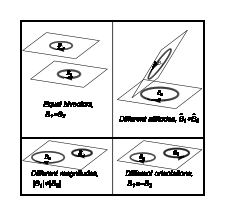
-Graphics- 
Geometric representation of main properties of bivectors  and :  displacebility, different attitudes, different magnitudes and opposite orientations.

Section.Item	Properties of general bivectors,  and

Computational verification

Define algebra and orthonormal basis. Since we were not satisfied with the automatically chosen color, we specified it manually. Bivectors will be denoted by script capital letters (can input as Escsc AEsc )

```mathematica
testAlgebra=Cl[4,3];
gaDefineNotation[testAlgebra,FontColor->RGBColor[1,1,0]];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

{1,1430,2430,3430,4430,5430,6430,7430,12430,13430,14430,15430,16430,17430,23430,24430,25430,26430,27430,34430,35430,36430,37430,45430,46430,47430,56430,57430,67430,123430,124430,125430,126430,127430,134430,135430,136430,137430,145430,146430,147430,156430,157430,167430,234430,235430,236430,237430,245430,246430,247430,256430,257430,267430,345430,346430,347430,356430,357430,367430,456430,457430,467430,567430,1234430,1235430,1236430,1237430,1245430,1246430,1247430,1256430,1257430,1267430,1345430,1346430,1347430,1356430,1357430,1367430,1456430,1457430,1467430,1567430,2345430,2346430,2347430,2356430,2357430,2367430,2456430,2457430,2467430,2567430,3456430,3457430,3467430,3567430,4567430,12345430,12346430,12347430,12356430,12357430,12367430,12456430,12457430,12467430,12567430,13456430,13457430,13467430,13567430,14567430,23456430,23457430,23467430,23567430,24567430,34567430,123456430,123457430,123467430,123567430,124567430,134567430,234567430,1234567430}

Generate arbitrary bivector of algebra,

```mathematica
gaGeneralMultivector[𝒜,testAlgebra,{2}]
```

𝒜[8] 12430+𝒜[9] 13430+𝒜[10] 14430+𝒜[11] 15430+𝒜[12] 16430+𝒜[13] 17430+𝒜[14] 23430+𝒜[15] 24430+𝒜[16] 25430+𝒜[17] 26430+𝒜[18] 27430+𝒜[19] 34430+𝒜[20] 35430+𝒜[21] 36430+𝒜[22] 37430+𝒜[23] 45430+𝒜[24] 46430+𝒜[25] 47430+𝒜[26] 56430+𝒜[27] 57430+𝒜[28] 67430

Square of bivector is a scalar iff    is the blade:

```mathematica
inputBlade=𝕖[1,2]+2𝕖[1,3]+𝕖[1,4]+𝕖[1,5]+𝕖[1,6]+𝕖[1,7]
```

12430+2 13430+14430+15430+16430+17430

```mathematica
gaBladeQ[inputBlade]
```

True

```mathematica
inputBlade\[GeometricProduct]inputBlade//gaPE
```

-3

```mathematica
inputNonBlade=𝕖[1,2]+2𝕖[1,3]+𝕖[1,4]+𝕖[1,5]+𝕖[1,6]+𝕖[1,7]+𝕖[3,4]
```

12430+2 13430+14430+15430+16430+17430+34430

```mathematica
gaBladeQ[inputNonBlade]
```

False

```mathematica
inputNonBlade\[GeometricProduct]inputNonBlade//gaPE
```

-4+2 1234430+2 1345430+2 1346430+2 1347430

Example of isotropic (null) bivector  ,

```mathematica
inputBlade=𝕖[1,2]+𝕖[1,3]+𝕖[1,4]+𝕖[1,5]+𝕖[1,6]+𝕖[1,7]
gaPE[%\[GeometricProduct]%]
```

12430+13430+14430+15430+16430+17430

0

Reverse of bivector changes its sign

```mathematica
𝒜1
gaReverse[𝒜1]
```

𝒜[8] 12430+𝒜[9] 13430+𝒜[10] 14430+𝒜[11] 15430+𝒜[12] 16430+𝒜[13] 17430+𝒜[14] 23430+𝒜[15] 24430+𝒜[16] 25430+𝒜[17] 26430+𝒜[18] 27430+𝒜[19] 34430+𝒜[20] 35430+𝒜[21] 36430+𝒜[22] 37430+𝒜[23] 45430+𝒜[24] 46430+𝒜[25] 47430+𝒜[26] 56430+𝒜[27] 57430+𝒜[28] 67430

-𝒜[8] 12430-𝒜[9] 13430-𝒜[10] 14430-𝒜[11] 15430-𝒜[12] 16430-𝒜[13] 17430-𝒜[14] 23430-𝒜[15] 24430-𝒜[16] 25430-𝒜[17] 26430-𝒜[18] 27430-𝒜[19] 34430-𝒜[20] 35430-𝒜[21] 36430-𝒜[22] 37430-𝒜[23] 45430-𝒜[24] 46430-𝒜[25] 47430-𝒜[26] 56430-𝒜[27] 57430-𝒜[28] 67430

Grade inverse  don’t change sign of the bivector, whereas Clifford conjugate change

```mathematica
𝒜1
gaGradeInverse[𝒜1]
gaCliffordConjugate[𝒜1]
```

𝒜[8] 12430+𝒜[9] 13430+𝒜[10] 14430+𝒜[11] 15430+𝒜[12] 16430+𝒜[13] 17430+𝒜[14] 23430+𝒜[15] 24430+𝒜[16] 25430+𝒜[17] 26430+𝒜[18] 27430+𝒜[19] 34430+𝒜[20] 35430+𝒜[21] 36430+𝒜[22] 37430+𝒜[23] 45430+𝒜[24] 46430+𝒜[25] 47430+𝒜[26] 56430+𝒜[27] 57430+𝒜[28] 67430

𝒜[8] 12430+𝒜[9] 13430+𝒜[10] 14430+𝒜[11] 15430+𝒜[12] 16430+𝒜[13] 17430+𝒜[14] 23430+𝒜[15] 24430+𝒜[16] 25430+𝒜[17] 26430+𝒜[18] 27430+𝒜[19] 34430+𝒜[20] 35430+𝒜[21] 36430+𝒜[22] 37430+𝒜[23] 45430+𝒜[24] 46430+𝒜[25] 47430+𝒜[26] 56430+𝒜[27] 57430+𝒜[28] 67430

-𝒜[8] 12430-𝒜[9] 13430-𝒜[10] 14430-𝒜[11] 15430-𝒜[12] 16430-𝒜[13] 17430-𝒜[14] 23430-𝒜[15] 24430-𝒜[16] 25430-𝒜[17] 26430-𝒜[18] 27430-𝒜[19] 34430-𝒜[20] 35430-𝒜[21] 36430-𝒜[22] 37430-𝒜[23] 45430-𝒜[24] 46430-𝒜[25] 47430-𝒜[26] 56430-𝒜[27] 57430-𝒜[28] 67430

Inverse of bivector in

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
𝒜1Num=gaRandomMultivector[testAlgebra,{2}]
```

-3 12300+4 13300-23300

```mathematica
𝒜1NumInv=gaReverse[𝒜1Num]\[GeometricProduct](1/gaPE[gaReverse[𝒜1Num]\[GeometricProduct]𝒜1Num])
```

1/26 (3 12300-4 13300+23300)

```mathematica
𝒜1Num\[GeometricProduct]𝒜1NumInv//gaPE
```

1

and  if  is the scalar

```mathematica
𝒜1\[InnerProduct]λ
```

0

```mathematica
𝒜1\[OuterProduct]λ
```

λ (𝒜[4] 12300+𝒜[5] 13300+𝒜[6] 23300)

If planes A and B are perpendicular

```mathematica
testAlgebra=Cl[4,3];
gaDefineNotation[testAlgebra,FontColor->RGBColor[1,1,0]];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

{1,1430,2430,3430,4430,5430,6430,7430,12430,13430,14430,15430,16430,17430,23430,24430,25430,26430,27430,34430,35430,36430,37430,45430,46430,47430,56430,57430,67430,123430,124430,125430,126430,127430,134430,135430,136430,137430,145430,146430,147430,156430,157430,167430,234430,235430,236430,237430,245430,246430,247430,256430,257430,267430,345430,346430,347430,356430,357430,367430,456430,457430,467430,567430,1234430,1235430,1236430,1237430,1245430,1246430,1247430,1256430,1257430,1267430,1345430,1346430,1347430,1356430,1357430,1367430,1456430,1457430,1467430,1567430,2345430,2346430,2347430,2356430,2357430,2367430,2456430,2457430,2467430,2567430,3456430,3457430,3467430,3567430,4567430,12345430,12346430,12347430,12356430,12357430,12367430,12456430,12457430,12467430,12567430,13456430,13457430,13467430,13567430,14567430,23456430,23457430,23467430,23567430,24567430,34567430,123456430,123457430,123467430,123567430,124567430,134567430,234567430,1234567430}

```mathematica
bladeA=𝕖[1,2]+𝕖[2,3]
bladeB=𝕖[3,4]+𝕖[3,5]
```

12430+23430

34430+35430

```mathematica
gaBladeQ/@{bladeA,bladeB}
```

{True,True}

```mathematica
bladeA\[InnerProduct]bladeB//gaPE
```

0

```mathematica
ClearAll[{inputBlade,inputNonBlade,𝒜1Num,𝒜1NumInv,bladeA,bladeB}];
```

Section.Item	Magnitude of simple bivector (2-blade) , [prideta pirmoje,]



Here  denotes an absolute value function.

Computational verification

Many of formulas were already checked.  Repeat checking using different algebra

```mathematica
testAlgebra=Cl[2,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[230,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  230

{1,1230,2230,3230,4230,5230,12230,13230,14230,15230,23230,24230,25230,34230,35230,45230,123230,124230,125230,134230,135230,145230,234230,235230,245230,345230,1234230,1235230,1245230,1345230,2345230,12345230}

Unit 2-blade,

```mathematica
𝒜1NumNegativeSq=2 𝕖[1,2]+𝕖[2,3]
```

2 12230+23230

```mathematica
𝒜1NumNegativeSqUnit=𝒜1NumNegativeSq\[GeometricProduct](1/gaPE[Sqrt[Abs[gaReverse[𝒜1NumNegativeSq]\[GeometricProduct]𝒜1NumNegativeSq]]])
𝒜1NumNegativeSqUnit=𝒜1NumNegativeSq/gaNormReverseAbs[𝒜1NumNegativeSq]
𝒜1NumNegativeSqUnit\[GeometricProduct]𝒜1NumNegativeSqUnit//gaPE
```

(2 12230+23230)/(√3)

(2 12230+23230)/(√3)

-1

```mathematica
𝒜1NumPositiveSq=𝕖[3,5]+3𝕖[2,3]
```

3 23230+35230

```mathematica
𝒜1NumPositiveSqUnit=𝒜1NumPositiveSq\[GeometricProduct](1/gaPE[Sqrt[Abs[gaReverse[𝒜1NumPositiveSq]\[GeometricProduct]𝒜1NumPositiveSq]]])
𝒜1NumPositiveSqUnit=𝒜1NumPositiveSq/gaNormReverseAbs[𝒜1NumPositiveSq]
𝒜1NumPositiveSqUnit\[GeometricProduct]𝒜1NumPositiveSqUnit//gaPE
```

(3 23230+35230)/(2 √2)

(3 23230+35230)/(2 √2)

1

Bivector norm in arbitrary signature (all norms except the determinant norm are not useful for non blades)

```mathematica
gaNormReverseAbs[𝒜1]
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

√Abs[𝒜[6]^2-𝒜[7]^2-𝒜[8]^2-𝒜[9]^2-𝒜[10]^2-𝒜[11]^2-𝒜[12]^2+𝒜[13]^2+𝒜[14]^2+𝒜[15]^2]

Examples of norms applied to bivector. For non blades the neither   or  produce a scalar, therefore we have to project a scalar part  as . Then a norm becomes useless for most of operations. The only useful norm for non bladed is a determinant norm

```mathematica
gaNormReverseAbs[𝒜1]
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

√Abs[𝒜[6]^2-𝒜[7]^2-𝒜[8]^2-𝒜[9]^2-𝒜[10]^2-𝒜[11]^2-𝒜[12]^2+𝒜[13]^2+𝒜[14]^2+𝒜[15]^2]

```mathematica
gaNormCliffordConjugateAbs[𝒜1]
```

gaNormCliffordConjugateAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and Clifford conjugate multivector.

√Abs[𝒜[6]^2-𝒜[7]^2-𝒜[8]^2-𝒜[9]^2-𝒜[10]^2-𝒜[11]^2-𝒜[12]^2+𝒜[13]^2+𝒜[14]^2+𝒜[15]^2]

```mathematica
gaNormOfCoefficients[𝒜1]
```

√(𝒜[6]^2+𝒜[7]^2+𝒜[8]^2+𝒜[9]^2+𝒜[10]^2+𝒜[11]^2+𝒜[12]^2+𝒜[13]^2+𝒜[14]^2+𝒜[15]^2)

```mathematica
gaNormDeterminant[𝒜1,Quiet->True]//Simplify
```

Abs[𝒜[6]^4+𝒜[7]^4+𝒜[8]^4+2 𝒜[8]^2 𝒜[9]^2+𝒜[9]^4-2 𝒜[8]^2 𝒜[10]^2-2 𝒜[9]^2 𝒜[10]^2+𝒜[10]^4+2 𝒜[8]^2 𝒜[11]^2-2 𝒜[9]^2 𝒜[11]^2+2 𝒜[10]^2 𝒜[11]^2+𝒜[11]^4+8 𝒜[8] 𝒜[9] 𝒜[11] 𝒜[12]-2 𝒜[8]^2 𝒜[12]^2+2 𝒜[9]^2 𝒜[12]^2+2 𝒜[10]^2 𝒜[12]^2+2 𝒜[11]^2 𝒜[12]^2+𝒜[12]^4-2 𝒜[8]^2 𝒜[13]^2+2 𝒜[9]^2 𝒜[13]^2-2 𝒜[10]^2 𝒜[13]^2-2 𝒜[11]^2 𝒜[13]^2+2 𝒜[12]^2 𝒜[13]^2+𝒜[13]^4-8 𝒜[8] 𝒜[9] 𝒜[13] 𝒜[14]-8 𝒜[11] 𝒜[12] 𝒜[13] 𝒜[14]+2 𝒜[8]^2 𝒜[14]^2-2 𝒜[9]^2 𝒜[14]^2-2 𝒜[10]^2 𝒜[14]^2+2 𝒜[11]^2 𝒜[14]^2-2 𝒜[12]^2 𝒜[14]^2+2 𝒜[13]^2 𝒜[14]^2+𝒜[14]^4+8 𝒜[10] 𝒜[12] 𝒜[13] 𝒜[15]-8 𝒜[10] 𝒜[11] 𝒜[14] 𝒜[15]-2 𝒜[8]^2 𝒜[15]^2-2 𝒜[9]^2 𝒜[15]^2+2 𝒜[10]^2 𝒜[15]^2-2 𝒜[11]^2 𝒜[15]^2-2 𝒜[12]^2 𝒜[15]^2+2 𝒜[13]^2 𝒜[15]^2+2 𝒜[14]^2 𝒜[15]^2+𝒜[15]^4+2 𝒜[7]^2 (𝒜[8]^2+𝒜[9]^2+𝒜[10]^2-𝒜[11]^2-𝒜[12]^2-𝒜[13]^2-𝒜[14]^2+𝒜[15]^2)-2 𝒜[6]^2 (𝒜[7]^2+𝒜[8]^2+𝒜[9]^2+𝒜[10]^2+𝒜[11]^2+𝒜[12]^2+𝒜[13]^2+𝒜[14]^2+𝒜[15]^2)+8 𝒜[6] (𝒜[7] (𝒜[11] 𝒜[13]+𝒜[12] 𝒜[14])-𝒜[9] (𝒜[10] 𝒜[14]+𝒜[11] 𝒜[15])+𝒜[8] (-𝒜[10] 𝒜[13]+𝒜[12] 𝒜[15]))+8 𝒜[7] (𝒜[9] (𝒜[10] 𝒜[12]+𝒜[13] 𝒜[15])+𝒜[8] (𝒜[10] 𝒜[11]-𝒜[14] 𝒜[15]))]^(1/4)

B̃ B  and B B experiments

Numerical values of coefficients at basis bivectors are

```mathematica
numericalCoeffsBiv={𝒜[6]->1,𝒜[7]->1,𝒜[8]->2,𝒜[9]->3,𝒜[10]->1,𝒜[11]->-8,𝒜[12]->4,𝒜[13]->1,𝒜[14]->1,𝒜[15]->2,ℬ[6]->1,ℬ[7]->1,ℬ[8]->2,ℬ[9]->3,ℬ[10]->1,ℬ[11]->-1,ℬ[12]->4,ℬ[13]->1,ℬ[14]->1,ℬ[15]->3};
```

Geometric product of two bivectors  in the assumed algebra

```mathematica
𝒜1\[GeometricProduct]𝒜1/.numericalCoeffsBiv//gaPE
```

88+22 1234230-60 1245230+6 1345230+28 2345230

Geometric product  of reverse bivector with itself

```mathematica
𝒜1
gaReverse[𝒜1]
%\[GeometricProduct]%%/.numericalCoeffsBiv//gaPE
```

𝒜[6] 12230+𝒜[7] 13230+𝒜[8] 14230+𝒜[9] 15230+𝒜[10] 23230+𝒜[11] 24230+𝒜[12] 25230+𝒜[13] 34230+𝒜[14] 35230+𝒜[15] 45230

-𝒜[6] 12230-𝒜[7] 13230-𝒜[8] 14230-𝒜[9] 15230-𝒜[10] 23230-𝒜[11] 24230-𝒜[12] 25230-𝒜[13] 34230-𝒜[14] 35230-𝒜[15] 45230

-88-22 1234230+60 1245230-6 1345230-28 2345230

Numerical values of coefficients at vectors of the assumed algebra

```mathematica
numericalCoeffsVec={a[1]->1,a[2]->1,a[3]->2,a[4]->3,a[5]->1,a[6]->-8,a[7]->4,b[1]->2,b[2]->5,b[3]->1,b[4]->1,b[5]->0,b[6]->3,b[7]->5};
```

Bivector part of geometric product of vectors, ⟨a1 (b1⟩)_2

```mathematica
newA=gaGetMV[a1\[GeometricProduct]b1/.numericalCoeffsVec//gaPE,{2}]
```

3 12230-3 13230-5 14230-2 15230-9 23230-14 24230-5 25230-34230-35230-45230

The square of the above bivector gives scalar

```mathematica
newA\[GeometricProduct]newA//gaPE
```

328

The reversion of one of bivectors changes overall sign

```mathematica
gaReverse[newA]\[GeometricProduct]newA//gaPE
```

-328

Test algebra and new values of the coefficients at elementary vectors and bivectors are assumed, and the calculations are repeated

```mathematica
testAlgebra=Cl[5,0];
```

```mathematica
numericalCoeffsBiv={𝒜[6]->1,𝒜[7]->1,𝒜[8]->2,𝒜[9]->3,𝒜[10]->-4,𝒜[11]->8,𝒜[12]->4,𝒜[13]->10,𝒜[14]->1,𝒜[15]->2,ℬ[6]->1,ℬ[7]->1,ℬ[8]->2,ℬ[9]->3,ℬ[10]->1,ℬ[11]->-1,ℬ[12]->4,ℬ[13]->1,ℬ[14]->1,ℬ[15]->3};
```

```mathematica
gaReverse[𝒜1]\[GeometricProduct]𝒜1/.numericalCoeffsBiv//gaPE
```

216+12 1234500+30 1235500-36 1245500-60 1345500-48 2345500

```mathematica
numericalCoeffsVec={a[1]->1,a[2]->1,a[3]->2,a[4]->3,a[5]->1,a[6]->-8,a[7]->4,b[1]->2,b[2]->5,b[3]->1,b[4]->1,b[5]->0,b[6]->3,b[7]->5};
```

```mathematica
newA=gaGetMV[a1\[GeometricProduct]b1/.numericalCoeffsVec//gaPE,{2}]
```

3 12500-3 13500-5 14500-2 15500-9 23500-14 24500-5 25500-34500-35500-45500

```mathematica
newA\[GeometricProduct]newA//gaPE
```

-352

```mathematica
gaReverse[newA]\[GeometricProduct]newA//gaPE
```

352

```mathematica
(a1\[GeometricProduct]b1)/.numericalCoeffsVec
(gaReverse[%]\[GeometricProduct]%)//gaPE
```

(1500+2500+2 3500+3 4500+5500)\[GeometricProduct](2 1500+5 2500+3500+4500)

496

Test algebra and new values of the coefficients at elementary vectors and bivectors are assumed, and calculations are repeated

```mathematica
testAlgebra=Cl[0,5];
```

```mathematica
numericalCoeffsBiv={𝒜[6]->1,𝒜[7]->-1,𝒜[8]->2,𝒜[9]->3,𝒜[10]->-4,𝒜[11]->8,𝒜[12]->4,𝒜[13]->10,𝒜[14]->1,𝒜[15]->2,ℬ[6]->1,ℬ[7]->1,ℬ[8]->2,ℬ[9]->3,ℬ[10]->1,ℬ[11]->-1,ℬ[12]->4,ℬ[13]->1,ℬ[14]->1,ℬ[15]->3};
```

```mathematica
gaReverse[𝒜1]\[GeometricProduct]𝒜1/.numericalCoeffsBiv//gaPE
```

216-20 1234050+14 1235050-36 1245050-52 1345050-48 2345050

```mathematica
numericalCoeffsVec={a[1]->1,a[2]->1,a[3]->2,a[4]->3,a[5]->1,a[6]->-8,a[7]->4,b[1]->2,b[2]->5,b[3]->1,b[4]->1,b[5]->0,b[6]->3,b[7]->5};
```

```mathematica
newA=gaGetMV[a1\[GeometricProduct]b1/.numericalCoeffsVec//gaPE,{2}]
```

3 12050-3 13050-5 14050-2 15050-9 23050-14 24050-5 25050-34050-35050-45050

```mathematica
newA\[GeometricProduct]newA//gaPE
```

-352

```mathematica
gaReverse[newA]\[GeometricProduct]newA//gaPE
```

352

```mathematica
(a1\[GeometricProduct]b1)/.numericalCoeffsVec
(gaReverse[%]\[GeometricProduct]%)//gaPE
```

(1050+2050+2 3050+3 4050+5050)\[GeometricProduct](2 1050+5 2050+3050+4050)

496

```mathematica
ClearAll[{𝒜1NumNegativeSq,𝒜1NumNegativeSqUnit,𝒜1NumPositiveSq,𝒜1NumPositiveSqUnit,numericalCoeffsBiv,numericalCoeffsVec,newA}];
```

Section.Item	Products of two bivectors,   and

Computational verification

The algebra is

```mathematica
testAlgebra=Cl[2,5];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[250,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  250

{1,1250,2250,3250,4250,5250,6250,7250,12250,13250,14250,15250,16250,17250,23250,24250,25250,26250,27250,34250,35250,36250,37250,45250,46250,47250,56250,57250,67250,123250,124250,125250,126250,127250,134250,135250,136250,137250,145250,146250,147250,156250,157250,167250,234250,235250,236250,237250,245250,246250,247250,256250,257250,267250,345250,346250,347250,356250,357250,367250,456250,457250,467250,567250,1234250,1235250,1236250,1237250,1245250,1246250,1247250,1256250,1257250,1267250,1345250,1346250,1347250,1356250,1357250,1367250,1456250,1457250,1467250,1567250,2345250,2346250,2347250,2356250,2357250,2367250,2456250,2457250,2467250,2567250,3456250,3457250,3467250,3567250,4567250,12345250,12346250,12347250,12356250,12357250,12367250,12456250,12457250,12467250,12567250,13456250,13457250,13467250,13567250,14567250,23456250,23457250,23467250,23567250,24567250,34567250,123456250,123457250,123467250,123567250,124567250,134567250,234567250,1234567250}

LHS

Geometric product of two bivectors  gives even grade elements

```mathematica
lhs[testAlgebra]=(𝒜1\[GeometricProduct]ℬ1)//gaPE
```

-𝒜[8] ℬ[8]+𝒜[9] ℬ[9]+𝒜[10] ℬ[10]+𝒜[11] ℬ[11]+𝒜[12] ℬ[12]+𝒜[13] ℬ[13]+𝒜[14] ℬ[14]+𝒜[15] ℬ[15]+𝒜[16] ℬ[16]+𝒜[17] ℬ[17]+𝒜[18] ℬ[18]-𝒜[19] ℬ[19]-𝒜[20] ℬ[20]-𝒜[21] ℬ[21]-𝒜[22] ℬ[22]-𝒜[23] ℬ[23]-𝒜[24] ℬ[24]-𝒜[25] ℬ[25]-𝒜[26] ℬ[26]-𝒜[27] ℬ[27]-𝒜[28] ℬ[28]+(-𝒜[14] ℬ[9]-𝒜[15] ℬ[10]-𝒜[16] ℬ[11]-𝒜[17] ℬ[12]-𝒜[18] ℬ[13]+𝒜[9] ℬ[14]+𝒜[10] ℬ[15]+𝒜[11] ℬ[16]+𝒜[12] ℬ[17]+𝒜[13] ℬ[18]) 12250+(-𝒜[14] ℬ[8]-𝒜[19] ℬ[10]-𝒜[20] ℬ[11]-𝒜[21] ℬ[12]-𝒜[22] ℬ[13]+𝒜[8] ℬ[14]+𝒜[10] ℬ[19]+𝒜[11] ℬ[20]+𝒜[12] ℬ[21]+𝒜[13] ℬ[22]) 13250+(-𝒜[15] ℬ[8]+𝒜[19] ℬ[9]-𝒜[23] ℬ[11]-𝒜[24] ℬ[12]-𝒜[25] ℬ[13]+𝒜[8] ℬ[15]-𝒜[9] ℬ[19]+𝒜[11] ℬ[23]+𝒜[12] ℬ[24]+𝒜[13] ℬ[25]) 14250+(-𝒜[16] ℬ[8]+𝒜[20] ℬ[9]+𝒜[23] ℬ[10]-𝒜[26] ℬ[12]-𝒜[27] ℬ[13]+𝒜[8] ℬ[16]-𝒜[9] ℬ[20]-𝒜[10] ℬ[23]+𝒜[12] ℬ[26]+𝒜[13] ℬ[27]) 15250+(-𝒜[17] ℬ[8]+𝒜[21] ℬ[9]+𝒜[24] ℬ[10]+𝒜[26] ℬ[11]-𝒜[28] ℬ[13]+𝒜[8] ℬ[17]-𝒜[9] ℬ[21]-𝒜[10] ℬ[24]-𝒜[11] ℬ[26]+𝒜[13] ℬ[28]) 16250+(-𝒜[18] ℬ[8]+𝒜[22] ℬ[9]+𝒜[25] ℬ[10]+𝒜[27] ℬ[11]+𝒜[28] ℬ[12]+𝒜[8] ℬ[18]-𝒜[9] ℬ[22]-𝒜[10] ℬ[25]-𝒜[11] ℬ[27]-𝒜[12] ℬ[28]) 17250+(𝒜[9] ℬ[8]-𝒜[8] ℬ[9]-𝒜[19] ℬ[15]-𝒜[20] ℬ[16]-𝒜[21] ℬ[17]-𝒜[22] ℬ[18]+𝒜[15] ℬ[19]+𝒜[16] ℬ[20]+𝒜[17] ℬ[21]+𝒜[18] ℬ[22]) 23250+(𝒜[10] ℬ[8]-𝒜[8] ℬ[10]+𝒜[19] ℬ[14]-𝒜[23] ℬ[16]-𝒜[24] ℬ[17]-𝒜[25] ℬ[18]-𝒜[14] ℬ[19]+𝒜[16] ℬ[23]+𝒜[17] ℬ[24]+𝒜[18] ℬ[25]) 24250+(𝒜[11] ℬ[8]-𝒜[8] ℬ[11]+𝒜[20] ℬ[14]+𝒜[23] ℬ[15]-𝒜[26] ℬ[17]-𝒜[27] ℬ[18]-𝒜[14] ℬ[20]-𝒜[15] ℬ[23]+𝒜[17] ℬ[26]+𝒜[18] ℬ[27]) 25250+(𝒜[12] ℬ[8]-𝒜[8] ℬ[12]+𝒜[21] ℬ[14]+𝒜[24] ℬ[15]+𝒜[26] ℬ[16]-𝒜[28] ℬ[18]-𝒜[14] ℬ[21]-𝒜[15] ℬ[24]-𝒜[16] ℬ[26]+𝒜[18] ℬ[28]) 26250+(𝒜[13] ℬ[8]-𝒜[8] ℬ[13]+𝒜[22] ℬ[14]+𝒜[25] ℬ[15]+𝒜[27] ℬ[16]+𝒜[28] ℬ[17]-𝒜[14] ℬ[22]-𝒜[15] ℬ[25]-𝒜[16] ℬ[27]-𝒜[17] ℬ[28]) 27250+(𝒜[10] ℬ[9]-𝒜[9] ℬ[10]+𝒜[15] ℬ[14]-𝒜[14] ℬ[15]-𝒜[23] ℬ[20]-𝒜[24] ℬ[21]-𝒜[25] ℬ[22]+𝒜[20] ℬ[23]+𝒜[21] ℬ[24]+𝒜[22] ℬ[25]) 34250+(𝒜[11] ℬ[9]-𝒜[9] ℬ[11]+𝒜[16] ℬ[14]-𝒜[14] ℬ[16]+𝒜[23] ℬ[19]-𝒜[26] ℬ[21]-𝒜[27] ℬ[22]-𝒜[19] ℬ[23]+𝒜[21] ℬ[26]+𝒜[22] ℬ[27]) 35250+(𝒜[12] ℬ[9]-𝒜[9] ℬ[12]+𝒜[17] ℬ[14]-𝒜[14] ℬ[17]+𝒜[24] ℬ[19]+𝒜[26] ℬ[20]-𝒜[28] ℬ[22]-𝒜[19] ℬ[24]-𝒜[20] ℬ[26]+𝒜[22] ℬ[28]) 36250+(𝒜[13] ℬ[9]-𝒜[9] ℬ[13]+𝒜[18] ℬ[14]-𝒜[14] ℬ[18]+𝒜[25] ℬ[19]+𝒜[27] ℬ[20]+𝒜[28] ℬ[21]-𝒜[19] ℬ[25]-𝒜[20] ℬ[27]-𝒜[21] ℬ[28]) 37250+(𝒜[11] ℬ[10]-𝒜[10] ℬ[11]+𝒜[16] ℬ[15]-𝒜[15] ℬ[16]-𝒜[20] ℬ[19]+𝒜[19] ℬ[20]-𝒜[26] ℬ[24]-𝒜[27] ℬ[25]+𝒜[24] ℬ[26]+𝒜[25] ℬ[27]) 45250+(𝒜[12] ℬ[10]-𝒜[10] ℬ[12]+𝒜[17] ℬ[15]-𝒜[15] ℬ[17]-𝒜[21] ℬ[19]+𝒜[19] ℬ[21]+𝒜[26] ℬ[23]-𝒜[28] ℬ[25]-𝒜[23] ℬ[26]+𝒜[25] ℬ[28]) 46250+(𝒜[13] ℬ[10]-𝒜[10] ℬ[13]+𝒜[18] ℬ[15]-𝒜[15] ℬ[18]-𝒜[22] ℬ[19]+𝒜[19] ℬ[22]+𝒜[27] ℬ[23]+𝒜[28] ℬ[24]-𝒜[23] ℬ[27]-𝒜[24] ℬ[28]) 47250+(𝒜[12] ℬ[11]-𝒜[11] ℬ[12]+𝒜[17] ℬ[16]-𝒜[16] ℬ[17]-𝒜[21] ℬ[20]+𝒜[20] ℬ[21]-𝒜[24] ℬ[23]+𝒜[23] ℬ[24]-𝒜[28] ℬ[27]+𝒜[27] ℬ[28]) 56250+(𝒜[13] ℬ[11]-𝒜[11] ℬ[13]+𝒜[18] ℬ[16]-𝒜[16] ℬ[18]-𝒜[22] ℬ[20]+𝒜[20] ℬ[22]-𝒜[25] ℬ[23]+𝒜[23] ℬ[25]+𝒜[28] ℬ[26]-𝒜[26] ℬ[28]) 57250+(𝒜[13] ℬ[12]-𝒜[12] ℬ[13]+𝒜[18] ℬ[17]-𝒜[17] ℬ[18]-𝒜[22] ℬ[21]+𝒜[21] ℬ[22]-𝒜[25] ℬ[24]+𝒜[24] ℬ[25]-𝒜[27] ℬ[26]+𝒜[26] ℬ[27]) 67250+(𝒜[19] ℬ[8]-𝒜[15] ℬ[9]+𝒜[14] ℬ[10]+𝒜[10] ℬ[14]-𝒜[9] ℬ[15]+𝒜[8] ℬ[19]) 1234250+(𝒜[20] ℬ[8]-𝒜[16] ℬ[9]+𝒜[14] ℬ[11]+𝒜[11] ℬ[14]-𝒜[9] ℬ[16]+𝒜[8] ℬ[20]) 1235250+(𝒜[21] ℬ[8]-𝒜[17] ℬ[9]+𝒜[14] ℬ[12]+𝒜[12] ℬ[14]-𝒜[9] ℬ[17]+𝒜[8] ℬ[21]) 1236250+(𝒜[22] ℬ[8]-𝒜[18] ℬ[9]+𝒜[14] ℬ[13]+𝒜[13] ℬ[14]-𝒜[9] ℬ[18]+𝒜[8] ℬ[22]) 1237250+(𝒜[23] ℬ[8]-𝒜[16] ℬ[10]+𝒜[15] ℬ[11]+𝒜[11] ℬ[15]-𝒜[10] ℬ[16]+𝒜[8] ℬ[23]) 1245250+(𝒜[24] ℬ[8]-𝒜[17] ℬ[10]+𝒜[15] ℬ[12]+𝒜[12] ℬ[15]-𝒜[10] ℬ[17]+𝒜[8] ℬ[24]) 1246250+(𝒜[25] ℬ[8]-𝒜[18] ℬ[10]+𝒜[15] ℬ[13]+𝒜[13] ℬ[15]-𝒜[10] ℬ[18]+𝒜[8] ℬ[25]) 1247250+(𝒜[26] ℬ[8]-𝒜[17] ℬ[11]+𝒜[16] ℬ[12]+𝒜[12] ℬ[16]-𝒜[11] ℬ[17]+𝒜[8] ℬ[26]) 1256250+(𝒜[27] ℬ[8]-𝒜[18] ℬ[11]+𝒜[16] ℬ[13]+𝒜[13] ℬ[16]-𝒜[11] ℬ[18]+𝒜[8] ℬ[27]) 1257250+(𝒜[28] ℬ[8]-𝒜[18] ℬ[12]+𝒜[17] ℬ[13]+𝒜[13] ℬ[17]-𝒜[12] ℬ[18]+𝒜[8] ℬ[28]) 1267250+(𝒜[23] ℬ[9]-𝒜[20] ℬ[10]+𝒜[19] ℬ[11]+𝒜[11] ℬ[19]-𝒜[10] ℬ[20]+𝒜[9] ℬ[23]) 1345250+(𝒜[24] ℬ[9]-𝒜[21] ℬ[10]+𝒜[19] ℬ[12]+𝒜[12] ℬ[19]-𝒜[10] ℬ[21]+𝒜[9] ℬ[24]) 1346250+(𝒜[25] ℬ[9]-𝒜[22] ℬ[10]+𝒜[19] ℬ[13]+𝒜[13] ℬ[19]-𝒜[10] ℬ[22]+𝒜[9] ℬ[25]) 1347250+(𝒜[26] ℬ[9]-𝒜[21] ℬ[11]+𝒜[20] ℬ[12]+𝒜[12] ℬ[20]-𝒜[11] ℬ[21]+𝒜[9] ℬ[26]) 1356250+(𝒜[27] ℬ[9]-𝒜[22] ℬ[11]+𝒜[20] ℬ[13]+𝒜[13] ℬ[20]-𝒜[11] ℬ[22]+𝒜[9] ℬ[27]) 1357250+(𝒜[28] ℬ[9]-𝒜[22] ℬ[12]+𝒜[21] ℬ[13]+𝒜[13] ℬ[21]-𝒜[12] ℬ[22]+𝒜[9] ℬ[28]) 1367250+(𝒜[26] ℬ[10]-𝒜[24] ℬ[11]+𝒜[23] ℬ[12]+𝒜[12] ℬ[23]-𝒜[11] ℬ[24]+𝒜[10] ℬ[26]) 1456250+(𝒜[27] ℬ[10]-𝒜[25] ℬ[11]+𝒜[23] ℬ[13]+𝒜[13] ℬ[23]-𝒜[11] ℬ[25]+𝒜[10] ℬ[27]) 1457250+(𝒜[28] ℬ[10]-𝒜[25] ℬ[12]+𝒜[24] ℬ[13]+𝒜[13] ℬ[24]-𝒜[12] ℬ[25]+𝒜[10] ℬ[28]) 1467250+(𝒜[28] ℬ[11]-𝒜[27] ℬ[12]+𝒜[26] ℬ[13]+𝒜[13] ℬ[26]-𝒜[12] ℬ[27]+𝒜[11] ℬ[28]) 1567250+(𝒜[23] ℬ[14]-𝒜[20] ℬ[15]+𝒜[19] ℬ[16]+𝒜[16] ℬ[19]-𝒜[15] ℬ[20]+𝒜[14] ℬ[23]) 2345250+(𝒜[24] ℬ[14]-𝒜[21] ℬ[15]+𝒜[19] ℬ[17]+𝒜[17] ℬ[19]-𝒜[15] ℬ[21]+𝒜[14] ℬ[24]) 2346250+(𝒜[25] ℬ[14]-𝒜[22] ℬ[15]+𝒜[19] ℬ[18]+𝒜[18] ℬ[19]-𝒜[15] ℬ[22]+𝒜[14] ℬ[25]) 2347250+(𝒜[26] ℬ[14]-𝒜[21] ℬ[16]+𝒜[20] ℬ[17]+𝒜[17] ℬ[20]-𝒜[16] ℬ[21]+𝒜[14] ℬ[26]) 2356250+(𝒜[27] ℬ[14]-𝒜[22] ℬ[16]+𝒜[20] ℬ[18]+𝒜[18] ℬ[20]-𝒜[16] ℬ[22]+𝒜[14] ℬ[27]) 2357250+(𝒜[28] ℬ[14]-𝒜[22] ℬ[17]+𝒜[21] ℬ[18]+𝒜[18] ℬ[21]-𝒜[17] ℬ[22]+𝒜[14] ℬ[28]) 2367250+(𝒜[26] ℬ[15]-𝒜[24] ℬ[16]+𝒜[23] ℬ[17]+𝒜[17] ℬ[23]-𝒜[16] ℬ[24]+𝒜[15] ℬ[26]) 2456250+(𝒜[27] ℬ[15]-𝒜[25] ℬ[16]+𝒜[23] ℬ[18]+𝒜[18] ℬ[23]-𝒜[16] ℬ[25]+𝒜[15] ℬ[27]) 2457250+(𝒜[28] ℬ[15]-𝒜[25] ℬ[17]+𝒜[24] ℬ[18]+𝒜[18] ℬ[24]-𝒜[17] ℬ[25]+𝒜[15] ℬ[28]) 2467250+(𝒜[28] ℬ[16]-𝒜[27] ℬ[17]+𝒜[26] ℬ[18]+𝒜[18] ℬ[26]-𝒜[17] ℬ[27]+𝒜[16] ℬ[28]) 2567250+(𝒜[26] ℬ[19]-𝒜[24] ℬ[20]+𝒜[23] ℬ[21]+𝒜[21] ℬ[23]-𝒜[20] ℬ[24]+𝒜[19] ℬ[26]) 3456250+(𝒜[27] ℬ[19]-𝒜[25] ℬ[20]+𝒜[23] ℬ[22]+𝒜[22] ℬ[23]-𝒜[20] ℬ[25]+𝒜[19] ℬ[27]) 3457250+(𝒜[28] ℬ[19]-𝒜[25] ℬ[21]+𝒜[24] ℬ[22]+𝒜[22] ℬ[24]-𝒜[21] ℬ[25]+𝒜[19] ℬ[28]) 3467250+(𝒜[28] ℬ[20]-𝒜[27] ℬ[21]+𝒜[26] ℬ[22]+𝒜[22] ℬ[26]-𝒜[21] ℬ[27]+𝒜[20] ℬ[28]) 3567250+(𝒜[28] ℬ[23]-𝒜[27] ℬ[24]+𝒜[26] ℬ[25]+𝒜[25] ℬ[26]-𝒜[24] ℬ[27]+𝒜[23] ℬ[28]) 4567250

RHS

```mathematica
rhs[testAlgebra]=𝒜1\[InnerProduct]ℬ1+gaGetMV[𝒜1\[GeometricProduct]ℬ1,{2}]+𝒜1\[OuterProduct]ℬ1;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//gaPE//Expand
```

0

(𝒜\[GeometricProduct]ℬ)=<𝒜\[GeometricProduct]ℬ>_0+<𝒜\[GeometricProduct]ℬ>_2+<𝒜\[GeometricProduct]ℬ>_4

LHS

Geometric product of two bivectors  gives even grade elements

```mathematica
lhs[testAlgebra]=(𝒜1\[GeometricProduct]ℬ1)//gaPE
```

-𝒜[8] ℬ[8]+𝒜[9] ℬ[9]+𝒜[10] ℬ[10]+𝒜[11] ℬ[11]+𝒜[12] ℬ[12]+𝒜[13] ℬ[13]+𝒜[14] ℬ[14]+𝒜[15] ℬ[15]+𝒜[16] ℬ[16]+𝒜[17] ℬ[17]+𝒜[18] ℬ[18]-𝒜[19] ℬ[19]-𝒜[20] ℬ[20]-𝒜[21] ℬ[21]-𝒜[22] ℬ[22]-𝒜[23] ℬ[23]-𝒜[24] ℬ[24]-𝒜[25] ℬ[25]-𝒜[26] ℬ[26]-𝒜[27] ℬ[27]-𝒜[28] ℬ[28]+(-𝒜[14] ℬ[9]-𝒜[15] ℬ[10]-𝒜[16] ℬ[11]-𝒜[17] ℬ[12]-𝒜[18] ℬ[13]+𝒜[9] ℬ[14]+𝒜[10] ℬ[15]+𝒜[11] ℬ[16]+𝒜[12] ℬ[17]+𝒜[13] ℬ[18]) 12250+(-𝒜[14] ℬ[8]-𝒜[19] ℬ[10]-𝒜[20] ℬ[11]-𝒜[21] ℬ[12]-𝒜[22] ℬ[13]+𝒜[8] ℬ[14]+𝒜[10] ℬ[19]+𝒜[11] ℬ[20]+𝒜[12] ℬ[21]+𝒜[13] ℬ[22]) 13250+(-𝒜[15] ℬ[8]+𝒜[19] ℬ[9]-𝒜[23] ℬ[11]-𝒜[24] ℬ[12]-𝒜[25] ℬ[13]+𝒜[8] ℬ[15]-𝒜[9] ℬ[19]+𝒜[11] ℬ[23]+𝒜[12] ℬ[24]+𝒜[13] ℬ[25]) 14250+(-𝒜[16] ℬ[8]+𝒜[20] ℬ[9]+𝒜[23] ℬ[10]-𝒜[26] ℬ[12]-𝒜[27] ℬ[13]+𝒜[8] ℬ[16]-𝒜[9] ℬ[20]-𝒜[10] ℬ[23]+𝒜[12] ℬ[26]+𝒜[13] ℬ[27]) 15250+(-𝒜[17] ℬ[8]+𝒜[21] ℬ[9]+𝒜[24] ℬ[10]+𝒜[26] ℬ[11]-𝒜[28] ℬ[13]+𝒜[8] ℬ[17]-𝒜[9] ℬ[21]-𝒜[10] ℬ[24]-𝒜[11] ℬ[26]+𝒜[13] ℬ[28]) 16250+(-𝒜[18] ℬ[8]+𝒜[22] ℬ[9]+𝒜[25] ℬ[10]+𝒜[27] ℬ[11]+𝒜[28] ℬ[12]+𝒜[8] ℬ[18]-𝒜[9] ℬ[22]-𝒜[10] ℬ[25]-𝒜[11] ℬ[27]-𝒜[12] ℬ[28]) 17250+(𝒜[9] ℬ[8]-𝒜[8] ℬ[9]-𝒜[19] ℬ[15]-𝒜[20] ℬ[16]-𝒜[21] ℬ[17]-𝒜[22] ℬ[18]+𝒜[15] ℬ[19]+𝒜[16] ℬ[20]+𝒜[17] ℬ[21]+𝒜[18] ℬ[22]) 23250+(𝒜[10] ℬ[8]-𝒜[8] ℬ[10]+𝒜[19] ℬ[14]-𝒜[23] ℬ[16]-𝒜[24] ℬ[17]-𝒜[25] ℬ[18]-𝒜[14] ℬ[19]+𝒜[16] ℬ[23]+𝒜[17] ℬ[24]+𝒜[18] ℬ[25]) 24250+(𝒜[11] ℬ[8]-𝒜[8] ℬ[11]+𝒜[20] ℬ[14]+𝒜[23] ℬ[15]-𝒜[26] ℬ[17]-𝒜[27] ℬ[18]-𝒜[14] ℬ[20]-𝒜[15] ℬ[23]+𝒜[17] ℬ[26]+𝒜[18] ℬ[27]) 25250+(𝒜[12] ℬ[8]-𝒜[8] ℬ[12]+𝒜[21] ℬ[14]+𝒜[24] ℬ[15]+𝒜[26] ℬ[16]-𝒜[28] ℬ[18]-𝒜[14] ℬ[21]-𝒜[15] ℬ[24]-𝒜[16] ℬ[26]+𝒜[18] ℬ[28]) 26250+(𝒜[13] ℬ[8]-𝒜[8] ℬ[13]+𝒜[22] ℬ[14]+𝒜[25] ℬ[15]+𝒜[27] ℬ[16]+𝒜[28] ℬ[17]-𝒜[14] ℬ[22]-𝒜[15] ℬ[25]-𝒜[16] ℬ[27]-𝒜[17] ℬ[28]) 27250+(𝒜[10] ℬ[9]-𝒜[9] ℬ[10]+𝒜[15] ℬ[14]-𝒜[14] ℬ[15]-𝒜[23] ℬ[20]-𝒜[24] ℬ[21]-𝒜[25] ℬ[22]+𝒜[20] ℬ[23]+𝒜[21] ℬ[24]+𝒜[22] ℬ[25]) 34250+(𝒜[11] ℬ[9]-𝒜[9] ℬ[11]+𝒜[16] ℬ[14]-𝒜[14] ℬ[16]+𝒜[23] ℬ[19]-𝒜[26] ℬ[21]-𝒜[27] ℬ[22]-𝒜[19] ℬ[23]+𝒜[21] ℬ[26]+𝒜[22] ℬ[27]) 35250+(𝒜[12] ℬ[9]-𝒜[9] ℬ[12]+𝒜[17] ℬ[14]-𝒜[14] ℬ[17]+𝒜[24] ℬ[19]+𝒜[26] ℬ[20]-𝒜[28] ℬ[22]-𝒜[19] ℬ[24]-𝒜[20] ℬ[26]+𝒜[22] ℬ[28]) 36250+(𝒜[13] ℬ[9]-𝒜[9] ℬ[13]+𝒜[18] ℬ[14]-𝒜[14] ℬ[18]+𝒜[25] ℬ[19]+𝒜[27] ℬ[20]+𝒜[28] ℬ[21]-𝒜[19] ℬ[25]-𝒜[20] ℬ[27]-𝒜[21] ℬ[28]) 37250+(𝒜[11] ℬ[10]-𝒜[10] ℬ[11]+𝒜[16] ℬ[15]-𝒜[15] ℬ[16]-𝒜[20] ℬ[19]+𝒜[19] ℬ[20]-𝒜[26] ℬ[24]-𝒜[27] ℬ[25]+𝒜[24] ℬ[26]+𝒜[25] ℬ[27]) 45250+(𝒜[12] ℬ[10]-𝒜[10] ℬ[12]+𝒜[17] ℬ[15]-𝒜[15] ℬ[17]-𝒜[21] ℬ[19]+𝒜[19] ℬ[21]+𝒜[26] ℬ[23]-𝒜[28] ℬ[25]-𝒜[23] ℬ[26]+𝒜[25] ℬ[28]) 46250+(𝒜[13] ℬ[10]-𝒜[10] ℬ[13]+𝒜[18] ℬ[15]-𝒜[15] ℬ[18]-𝒜[22] ℬ[19]+𝒜[19] ℬ[22]+𝒜[27] ℬ[23]+𝒜[28] ℬ[24]-𝒜[23] ℬ[27]-𝒜[24] ℬ[28]) 47250+(𝒜[12] ℬ[11]-𝒜[11] ℬ[12]+𝒜[17] ℬ[16]-𝒜[16] ℬ[17]-𝒜[21] ℬ[20]+𝒜[20] ℬ[21]-𝒜[24] ℬ[23]+𝒜[23] ℬ[24]-𝒜[28] ℬ[27]+𝒜[27] ℬ[28]) 56250+(𝒜[13] ℬ[11]-𝒜[11] ℬ[13]+𝒜[18] ℬ[16]-𝒜[16] ℬ[18]-𝒜[22] ℬ[20]+𝒜[20] ℬ[22]-𝒜[25] ℬ[23]+𝒜[23] ℬ[25]+𝒜[28] ℬ[26]-𝒜[26] ℬ[28]) 57250+(𝒜[13] ℬ[12]-𝒜[12] ℬ[13]+𝒜[18] ℬ[17]-𝒜[17] ℬ[18]-𝒜[22] ℬ[21]+𝒜[21] ℬ[22]-𝒜[25] ℬ[24]+𝒜[24] ℬ[25]-𝒜[27] ℬ[26]+𝒜[26] ℬ[27]) 67250+(𝒜[19] ℬ[8]-𝒜[15] ℬ[9]+𝒜[14] ℬ[10]+𝒜[10] ℬ[14]-𝒜[9] ℬ[15]+𝒜[8] ℬ[19]) 1234250+(𝒜[20] ℬ[8]-𝒜[16] ℬ[9]+𝒜[14] ℬ[11]+𝒜[11] ℬ[14]-𝒜[9] ℬ[16]+𝒜[8] ℬ[20]) 1235250+(𝒜[21] ℬ[8]-𝒜[17] ℬ[9]+𝒜[14] ℬ[12]+𝒜[12] ℬ[14]-𝒜[9] ℬ[17]+𝒜[8] ℬ[21]) 1236250+(𝒜[22] ℬ[8]-𝒜[18] ℬ[9]+𝒜[14] ℬ[13]+𝒜[13] ℬ[14]-𝒜[9] ℬ[18]+𝒜[8] ℬ[22]) 1237250+(𝒜[23] ℬ[8]-𝒜[16] ℬ[10]+𝒜[15] ℬ[11]+𝒜[11] ℬ[15]-𝒜[10] ℬ[16]+𝒜[8] ℬ[23]) 1245250+(𝒜[24] ℬ[8]-𝒜[17] ℬ[10]+𝒜[15] ℬ[12]+𝒜[12] ℬ[15]-𝒜[10] ℬ[17]+𝒜[8] ℬ[24]) 1246250+(𝒜[25] ℬ[8]-𝒜[18] ℬ[10]+𝒜[15] ℬ[13]+𝒜[13] ℬ[15]-𝒜[10] ℬ[18]+𝒜[8] ℬ[25]) 1247250+(𝒜[26] ℬ[8]-𝒜[17] ℬ[11]+𝒜[16] ℬ[12]+𝒜[12] ℬ[16]-𝒜[11] ℬ[17]+𝒜[8] ℬ[26]) 1256250+(𝒜[27] ℬ[8]-𝒜[18] ℬ[11]+𝒜[16] ℬ[13]+𝒜[13] ℬ[16]-𝒜[11] ℬ[18]+𝒜[8] ℬ[27]) 1257250+(𝒜[28] ℬ[8]-𝒜[18] ℬ[12]+𝒜[17] ℬ[13]+𝒜[13] ℬ[17]-𝒜[12] ℬ[18]+𝒜[8] ℬ[28]) 1267250+(𝒜[23] ℬ[9]-𝒜[20] ℬ[10]+𝒜[19] ℬ[11]+𝒜[11] ℬ[19]-𝒜[10] ℬ[20]+𝒜[9] ℬ[23]) 1345250+(𝒜[24] ℬ[9]-𝒜[21] ℬ[10]+𝒜[19] ℬ[12]+𝒜[12] ℬ[19]-𝒜[10] ℬ[21]+𝒜[9] ℬ[24]) 1346250+(𝒜[25] ℬ[9]-𝒜[22] ℬ[10]+𝒜[19] ℬ[13]+𝒜[13] ℬ[19]-𝒜[10] ℬ[22]+𝒜[9] ℬ[25]) 1347250+(𝒜[26] ℬ[9]-𝒜[21] ℬ[11]+𝒜[20] ℬ[12]+𝒜[12] ℬ[20]-𝒜[11] ℬ[21]+𝒜[9] ℬ[26]) 1356250+(𝒜[27] ℬ[9]-𝒜[22] ℬ[11]+𝒜[20] ℬ[13]+𝒜[13] ℬ[20]-𝒜[11] ℬ[22]+𝒜[9] ℬ[27]) 1357250+(𝒜[28] ℬ[9]-𝒜[22] ℬ[12]+𝒜[21] ℬ[13]+𝒜[13] ℬ[21]-𝒜[12] ℬ[22]+𝒜[9] ℬ[28]) 1367250+(𝒜[26] ℬ[10]-𝒜[24] ℬ[11]+𝒜[23] ℬ[12]+𝒜[12] ℬ[23]-𝒜[11] ℬ[24]+𝒜[10] ℬ[26]) 1456250+(𝒜[27] ℬ[10]-𝒜[25] ℬ[11]+𝒜[23] ℬ[13]+𝒜[13] ℬ[23]-𝒜[11] ℬ[25]+𝒜[10] ℬ[27]) 1457250+(𝒜[28] ℬ[10]-𝒜[25] ℬ[12]+𝒜[24] ℬ[13]+𝒜[13] ℬ[24]-𝒜[12] ℬ[25]+𝒜[10] ℬ[28]) 1467250+(𝒜[28] ℬ[11]-𝒜[27] ℬ[12]+𝒜[26] ℬ[13]+𝒜[13] ℬ[26]-𝒜[12] ℬ[27]+𝒜[11] ℬ[28]) 1567250+(𝒜[23] ℬ[14]-𝒜[20] ℬ[15]+𝒜[19] ℬ[16]+𝒜[16] ℬ[19]-𝒜[15] ℬ[20]+𝒜[14] ℬ[23]) 2345250+(𝒜[24] ℬ[14]-𝒜[21] ℬ[15]+𝒜[19] ℬ[17]+𝒜[17] ℬ[19]-𝒜[15] ℬ[21]+𝒜[14] ℬ[24]) 2346250+(𝒜[25] ℬ[14]-𝒜[22] ℬ[15]+𝒜[19] ℬ[18]+𝒜[18] ℬ[19]-𝒜[15] ℬ[22]+𝒜[14] ℬ[25]) 2347250+(𝒜[26] ℬ[14]-𝒜[21] ℬ[16]+𝒜[20] ℬ[17]+𝒜[17] ℬ[20]-𝒜[16] ℬ[21]+𝒜[14] ℬ[26]) 2356250+(𝒜[27] ℬ[14]-𝒜[22] ℬ[16]+𝒜[20] ℬ[18]+𝒜[18] ℬ[20]-𝒜[16] ℬ[22]+𝒜[14] ℬ[27]) 2357250+(𝒜[28] ℬ[14]-𝒜[22] ℬ[17]+𝒜[21] ℬ[18]+𝒜[18] ℬ[21]-𝒜[17] ℬ[22]+𝒜[14] ℬ[28]) 2367250+(𝒜[26] ℬ[15]-𝒜[24] ℬ[16]+𝒜[23] ℬ[17]+𝒜[17] ℬ[23]-𝒜[16] ℬ[24]+𝒜[15] ℬ[26]) 2456250+(𝒜[27] ℬ[15]-𝒜[25] ℬ[16]+𝒜[23] ℬ[18]+𝒜[18] ℬ[23]-𝒜[16] ℬ[25]+𝒜[15] ℬ[27]) 2457250+(𝒜[28] ℬ[15]-𝒜[25] ℬ[17]+𝒜[24] ℬ[18]+𝒜[18] ℬ[24]-𝒜[17] ℬ[25]+𝒜[15] ℬ[28]) 2467250+(𝒜[28] ℬ[16]-𝒜[27] ℬ[17]+𝒜[26] ℬ[18]+𝒜[18] ℬ[26]-𝒜[17] ℬ[27]+𝒜[16] ℬ[28]) 2567250+(𝒜[26] ℬ[19]-𝒜[24] ℬ[20]+𝒜[23] ℬ[21]+𝒜[21] ℬ[23]-𝒜[20] ℬ[24]+𝒜[19] ℬ[26]) 3456250+(𝒜[27] ℬ[19]-𝒜[25] ℬ[20]+𝒜[23] ℬ[22]+𝒜[22] ℬ[23]-𝒜[20] ℬ[25]+𝒜[19] ℬ[27]) 3457250+(𝒜[28] ℬ[19]-𝒜[25] ℬ[21]+𝒜[24] ℬ[22]+𝒜[22] ℬ[24]-𝒜[21] ℬ[25]+𝒜[19] ℬ[28]) 3467250+(𝒜[28] ℬ[20]-𝒜[27] ℬ[21]+𝒜[26] ℬ[22]+𝒜[22] ℬ[26]-𝒜[21] ℬ[27]+𝒜[20] ℬ[28]) 3567250+(𝒜[28] ℬ[23]-𝒜[27] ℬ[24]+𝒜[26] ℬ[25]+𝒜[25] ℬ[26]-𝒜[24] ℬ[27]+𝒜[23] ℬ[28]) 4567250

RHS

```mathematica
rhs[testAlgebra]=gaGetMV[(𝒜1\[GeometricProduct]ℬ1),{0,2,4}];
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

(𝒜\[InnerProduct]ℬ)=<𝒜\[GeometricProduct]ℬ>_0=

LHS
Inner product of two bivectors

```mathematica
lhs[testAlgebra]=(𝒜1\[InnerProduct]ℬ1)//gaPE
```

-𝒜[8] ℬ[8]+𝒜[9] ℬ[9]+𝒜[10] ℬ[10]+𝒜[11] ℬ[11]+𝒜[12] ℬ[12]+𝒜[13] ℬ[13]+𝒜[14] ℬ[14]+𝒜[15] ℬ[15]+𝒜[16] ℬ[16]+𝒜[17] ℬ[17]+𝒜[18] ℬ[18]-𝒜[19] ℬ[19]-𝒜[20] ℬ[20]-𝒜[21] ℬ[21]-𝒜[22] ℬ[22]-𝒜[23] ℬ[23]-𝒜[24] ℬ[24]-𝒜[25] ℬ[25]-𝒜[26] ℬ[26]-𝒜[27] ℬ[27]-𝒜[28] ℬ[28]

RHS
Scalar part of the geometric product of two bivectors

```mathematica
rhs[testAlgebra]=gaGetMV[(𝒜1\[GeometricProduct]ℬ1),{0}]
```

-𝒜[8] ℬ[8]+𝒜[9] ℬ[9]+𝒜[10] ℬ[10]+𝒜[11] ℬ[11]+𝒜[12] ℬ[12]+𝒜[13] ℬ[13]+𝒜[14] ℬ[14]+𝒜[15] ℬ[15]+𝒜[16] ℬ[16]+𝒜[17] ℬ[17]+𝒜[18] ℬ[18]-𝒜[19] ℬ[19]-𝒜[20] ℬ[20]-𝒜[21] ℬ[21]-𝒜[22] ℬ[22]-𝒜[23] ℬ[23]-𝒜[24] ℬ[24]-𝒜[25] ℬ[25]-𝒜[26] ℬ[26]-𝒜[27] ℬ[27]-𝒜[28] ℬ[28]

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

```mathematica
rhs1[testAlgebra]=gaGetMV[(𝒜1\[GeometricProduct]ℬ1+ℬ1\[GeometricProduct]𝒜1)/2,{0}]
```

-𝒜[8] ℬ[8]+𝒜[9] ℬ[9]+𝒜[10] ℬ[10]+𝒜[11] ℬ[11]+𝒜[12] ℬ[12]+𝒜[13] ℬ[13]+𝒜[14] ℬ[14]+𝒜[15] ℬ[15]+𝒜[16] ℬ[16]+𝒜[17] ℬ[17]+𝒜[18] ℬ[18]-𝒜[19] ℬ[19]-𝒜[20] ℬ[20]-𝒜[21] ℬ[21]-𝒜[22] ℬ[22]-𝒜[23] ℬ[23]-𝒜[24] ℬ[24]-𝒜[25] ℬ[25]-𝒜[26] ℬ[26]-𝒜[27] ℬ[27]-𝒜[28] ℬ[28]

```mathematica
(lhs[testAlgebra]-rhs1[testAlgebra])//Expand
```

0

The inner product commutates

```mathematica
((𝒜1\[InnerProduct]ℬ1)-(ℬ1\[InnerProduct]𝒜1))//gaPE
```

0

(𝒜\[OuterProduct]ℬ)=ℬ\[OuterProduct]𝒜=

LHS
Inner product of two bivectors

```mathematica
(lhs[testAlgebra]=(𝒜1\[OuterProduct]ℬ1)//gaPE)//Length
```

35

RHS
Scalar part of the geometric product of two bivectors

```mathematica
rhs[testAlgebra]=(ℬ1\[OuterProduct]𝒜1)
```

(ℬ[8] 12250+ℬ[9] 13250+ℬ[10] 14250+ℬ[11] 15250+ℬ[12] 16250+ℬ[13] 17250+ℬ[14] 23250+ℬ[15] 24250+ℬ[16] 25250+ℬ[17] 26250+ℬ[18] 27250+ℬ[19] 34250+ℬ[20] 35250+ℬ[21] 36250+ℬ[22] 37250+ℬ[23] 45250+ℬ[24] 46250+ℬ[25] 47250+ℬ[26] 56250+ℬ[27] 57250+ℬ[28] 67250)\[OuterProduct](𝒜[8] 12250+𝒜[9] 13250+𝒜[10] 14250+𝒜[11] 15250+𝒜[12] 16250+𝒜[13] 17250+𝒜[14] 23250+𝒜[15] 24250+𝒜[16] 25250+𝒜[17] 26250+𝒜[18] 27250+𝒜[19] 34250+𝒜[20] 35250+𝒜[21] 36250+𝒜[22] 37250+𝒜[23] 45250+𝒜[24] 46250+𝒜[25] 47250+𝒜[26] 56250+𝒜[27] 57250+𝒜[28] 67250)

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra]//gaPE)//Expand
```

0

```mathematica
(rhs1[testAlgebra]=gaGetMV[(𝒜1\[GeometricProduct]ℬ1+ℬ1\[GeometricProduct]𝒜1)/2,{4}])//Length
```

2

```mathematica
(lhs[testAlgebra]-rhs1[testAlgebra])//Expand
```

0

<𝒜\[GeometricProduct]ℬ>_2=(𝒜\[GeometricProduct]ℬ-ℬ\[GeometricProduct]𝒜)/2

LHS

```mathematica
lhs[testAlgebra]=gaGetMV[(𝒜1\[GeometricProduct]ℬ1),{2}]
```

(-𝒜[14] ℬ[9]-𝒜[15] ℬ[10]-𝒜[16] ℬ[11]-𝒜[17] ℬ[12]-𝒜[18] ℬ[13]+𝒜[9] ℬ[14]+𝒜[10] ℬ[15]+𝒜[11] ℬ[16]+𝒜[12] ℬ[17]+𝒜[13] ℬ[18]) 12250+(-𝒜[14] ℬ[8]-𝒜[19] ℬ[10]-𝒜[20] ℬ[11]-𝒜[21] ℬ[12]-𝒜[22] ℬ[13]+𝒜[8] ℬ[14]+𝒜[10] ℬ[19]+𝒜[11] ℬ[20]+𝒜[12] ℬ[21]+𝒜[13] ℬ[22]) 13250+(-𝒜[15] ℬ[8]+𝒜[19] ℬ[9]-𝒜[23] ℬ[11]-𝒜[24] ℬ[12]-𝒜[25] ℬ[13]+𝒜[8] ℬ[15]-𝒜[9] ℬ[19]+𝒜[11] ℬ[23]+𝒜[12] ℬ[24]+𝒜[13] ℬ[25]) 14250+(-𝒜[16] ℬ[8]+𝒜[20] ℬ[9]+𝒜[23] ℬ[10]-𝒜[26] ℬ[12]-𝒜[27] ℬ[13]+𝒜[8] ℬ[16]-𝒜[9] ℬ[20]-𝒜[10] ℬ[23]+𝒜[12] ℬ[26]+𝒜[13] ℬ[27]) 15250+(-𝒜[17] ℬ[8]+𝒜[21] ℬ[9]+𝒜[24] ℬ[10]+𝒜[26] ℬ[11]-𝒜[28] ℬ[13]+𝒜[8] ℬ[17]-𝒜[9] ℬ[21]-𝒜[10] ℬ[24]-𝒜[11] ℬ[26]+𝒜[13] ℬ[28]) 16250+(-𝒜[18] ℬ[8]+𝒜[22] ℬ[9]+𝒜[25] ℬ[10]+𝒜[27] ℬ[11]+𝒜[28] ℬ[12]+𝒜[8] ℬ[18]-𝒜[9] ℬ[22]-𝒜[10] ℬ[25]-𝒜[11] ℬ[27]-𝒜[12] ℬ[28]) 17250+(𝒜[9] ℬ[8]-𝒜[8] ℬ[9]-𝒜[19] ℬ[15]-𝒜[20] ℬ[16]-𝒜[21] ℬ[17]-𝒜[22] ℬ[18]+𝒜[15] ℬ[19]+𝒜[16] ℬ[20]+𝒜[17] ℬ[21]+𝒜[18] ℬ[22]) 23250+(𝒜[10] ℬ[8]-𝒜[8] ℬ[10]+𝒜[19] ℬ[14]-𝒜[23] ℬ[16]-𝒜[24] ℬ[17]-𝒜[25] ℬ[18]-𝒜[14] ℬ[19]+𝒜[16] ℬ[23]+𝒜[17] ℬ[24]+𝒜[18] ℬ[25]) 24250+(𝒜[11] ℬ[8]-𝒜[8] ℬ[11]+𝒜[20] ℬ[14]+𝒜[23] ℬ[15]-𝒜[26] ℬ[17]-𝒜[27] ℬ[18]-𝒜[14] ℬ[20]-𝒜[15] ℬ[23]+𝒜[17] ℬ[26]+𝒜[18] ℬ[27]) 25250+(𝒜[12] ℬ[8]-𝒜[8] ℬ[12]+𝒜[21] ℬ[14]+𝒜[24] ℬ[15]+𝒜[26] ℬ[16]-𝒜[28] ℬ[18]-𝒜[14] ℬ[21]-𝒜[15] ℬ[24]-𝒜[16] ℬ[26]+𝒜[18] ℬ[28]) 26250+(𝒜[13] ℬ[8]-𝒜[8] ℬ[13]+𝒜[22] ℬ[14]+𝒜[25] ℬ[15]+𝒜[27] ℬ[16]+𝒜[28] ℬ[17]-𝒜[14] ℬ[22]-𝒜[15] ℬ[25]-𝒜[16] ℬ[27]-𝒜[17] ℬ[28]) 27250+(𝒜[10] ℬ[9]-𝒜[9] ℬ[10]+𝒜[15] ℬ[14]-𝒜[14] ℬ[15]-𝒜[23] ℬ[20]-𝒜[24] ℬ[21]-𝒜[25] ℬ[22]+𝒜[20] ℬ[23]+𝒜[21] ℬ[24]+𝒜[22] ℬ[25]) 34250+(𝒜[11] ℬ[9]-𝒜[9] ℬ[11]+𝒜[16] ℬ[14]-𝒜[14] ℬ[16]+𝒜[23] ℬ[19]-𝒜[26] ℬ[21]-𝒜[27] ℬ[22]-𝒜[19] ℬ[23]+𝒜[21] ℬ[26]+𝒜[22] ℬ[27]) 35250+(𝒜[12] ℬ[9]-𝒜[9] ℬ[12]+𝒜[17] ℬ[14]-𝒜[14] ℬ[17]+𝒜[24] ℬ[19]+𝒜[26] ℬ[20]-𝒜[28] ℬ[22]-𝒜[19] ℬ[24]-𝒜[20] ℬ[26]+𝒜[22] ℬ[28]) 36250+(𝒜[13] ℬ[9]-𝒜[9] ℬ[13]+𝒜[18] ℬ[14]-𝒜[14] ℬ[18]+𝒜[25] ℬ[19]+𝒜[27] ℬ[20]+𝒜[28] ℬ[21]-𝒜[19] ℬ[25]-𝒜[20] ℬ[27]-𝒜[21] ℬ[28]) 37250+(𝒜[11] ℬ[10]-𝒜[10] ℬ[11]+𝒜[16] ℬ[15]-𝒜[15] ℬ[16]-𝒜[20] ℬ[19]+𝒜[19] ℬ[20]-𝒜[26] ℬ[24]-𝒜[27] ℬ[25]+𝒜[24] ℬ[26]+𝒜[25] ℬ[27]) 45250+(𝒜[12] ℬ[10]-𝒜[10] ℬ[12]+𝒜[17] ℬ[15]-𝒜[15] ℬ[17]-𝒜[21] ℬ[19]+𝒜[19] ℬ[21]+𝒜[26] ℬ[23]-𝒜[28] ℬ[25]-𝒜[23] ℬ[26]+𝒜[25] ℬ[28]) 46250+(𝒜[13] ℬ[10]-𝒜[10] ℬ[13]+𝒜[18] ℬ[15]-𝒜[15] ℬ[18]-𝒜[22] ℬ[19]+𝒜[19] ℬ[22]+𝒜[27] ℬ[23]+𝒜[28] ℬ[24]-𝒜[23] ℬ[27]-𝒜[24] ℬ[28]) 47250+(𝒜[12] ℬ[11]-𝒜[11] ℬ[12]+𝒜[17] ℬ[16]-𝒜[16] ℬ[17]-𝒜[21] ℬ[20]+𝒜[20] ℬ[21]-𝒜[24] ℬ[23]+𝒜[23] ℬ[24]-𝒜[28] ℬ[27]+𝒜[27] ℬ[28]) 56250+(𝒜[13] ℬ[11]-𝒜[11] ℬ[13]+𝒜[18] ℬ[16]-𝒜[16] ℬ[18]-𝒜[22] ℬ[20]+𝒜[20] ℬ[22]-𝒜[25] ℬ[23]+𝒜[23] ℬ[25]+𝒜[28] ℬ[26]-𝒜[26] ℬ[28]) 57250+(𝒜[13] ℬ[12]-𝒜[12] ℬ[13]+𝒜[18] ℬ[17]-𝒜[17] ℬ[18]-𝒜[22] ℬ[21]+𝒜[21] ℬ[22]-𝒜[25] ℬ[24]+𝒜[24] ℬ[25]-𝒜[27] ℬ[26]+𝒜[26] ℬ[27]) 67250

RHS

```mathematica
rhs[testAlgebra]=(𝒜1\[GeometricProduct]ℬ1-ℬ1\[GeometricProduct]𝒜1)/2//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

(𝒜\[OuterProduct]ℬ)=<𝒜\[GeometricProduct]ℬ>_4

Test algebra is assumed

```mathematica
testAlgebra=Cl[4,3];
```

LHS
Outer product of two bivectors

```mathematica
lhs[testAlgebra]=(𝒜1\[OuterProduct]ℬ1)//gaPE
```

(𝒜[19] ℬ[8]-𝒜[15] ℬ[9]+𝒜[14] ℬ[10]+𝒜[10] ℬ[14]-𝒜[9] ℬ[15]+𝒜[8] ℬ[19]) 1234250+(𝒜[20] ℬ[8]-𝒜[16] ℬ[9]+𝒜[14] ℬ[11]+𝒜[11] ℬ[14]-𝒜[9] ℬ[16]+𝒜[8] ℬ[20]) 1235250+(𝒜[21] ℬ[8]-𝒜[17] ℬ[9]+𝒜[14] ℬ[12]+𝒜[12] ℬ[14]-𝒜[9] ℬ[17]+𝒜[8] ℬ[21]) 1236250+(𝒜[22] ℬ[8]-𝒜[18] ℬ[9]+𝒜[14] ℬ[13]+𝒜[13] ℬ[14]-𝒜[9] ℬ[18]+𝒜[8] ℬ[22]) 1237250+(𝒜[23] ℬ[8]-𝒜[16] ℬ[10]+𝒜[15] ℬ[11]+𝒜[11] ℬ[15]-𝒜[10] ℬ[16]+𝒜[8] ℬ[23]) 1245250+(𝒜[24] ℬ[8]-𝒜[17] ℬ[10]+𝒜[15] ℬ[12]+𝒜[12] ℬ[15]-𝒜[10] ℬ[17]+𝒜[8] ℬ[24]) 1246250+(𝒜[25] ℬ[8]-𝒜[18] ℬ[10]+𝒜[15] ℬ[13]+𝒜[13] ℬ[15]-𝒜[10] ℬ[18]+𝒜[8] ℬ[25]) 1247250+(𝒜[26] ℬ[8]-𝒜[17] ℬ[11]+𝒜[16] ℬ[12]+𝒜[12] ℬ[16]-𝒜[11] ℬ[17]+𝒜[8] ℬ[26]) 1256250+(𝒜[27] ℬ[8]-𝒜[18] ℬ[11]+𝒜[16] ℬ[13]+𝒜[13] ℬ[16]-𝒜[11] ℬ[18]+𝒜[8] ℬ[27]) 1257250+(𝒜[28] ℬ[8]-𝒜[18] ℬ[12]+𝒜[17] ℬ[13]+𝒜[13] ℬ[17]-𝒜[12] ℬ[18]+𝒜[8] ℬ[28]) 1267250+(𝒜[23] ℬ[9]-𝒜[20] ℬ[10]+𝒜[19] ℬ[11]+𝒜[11] ℬ[19]-𝒜[10] ℬ[20]+𝒜[9] ℬ[23]) 1345250+(𝒜[24] ℬ[9]-𝒜[21] ℬ[10]+𝒜[19] ℬ[12]+𝒜[12] ℬ[19]-𝒜[10] ℬ[21]+𝒜[9] ℬ[24]) 1346250+(𝒜[25] ℬ[9]-𝒜[22] ℬ[10]+𝒜[19] ℬ[13]+𝒜[13] ℬ[19]-𝒜[10] ℬ[22]+𝒜[9] ℬ[25]) 1347250+(𝒜[26] ℬ[9]-𝒜[21] ℬ[11]+𝒜[20] ℬ[12]+𝒜[12] ℬ[20]-𝒜[11] ℬ[21]+𝒜[9] ℬ[26]) 1356250+(𝒜[27] ℬ[9]-𝒜[22] ℬ[11]+𝒜[20] ℬ[13]+𝒜[13] ℬ[20]-𝒜[11] ℬ[22]+𝒜[9] ℬ[27]) 1357250+(𝒜[28] ℬ[9]-𝒜[22] ℬ[12]+𝒜[21] ℬ[13]+𝒜[13] ℬ[21]-𝒜[12] ℬ[22]+𝒜[9] ℬ[28]) 1367250+(𝒜[26] ℬ[10]-𝒜[24] ℬ[11]+𝒜[23] ℬ[12]+𝒜[12] ℬ[23]-𝒜[11] ℬ[24]+𝒜[10] ℬ[26]) 1456250+(𝒜[27] ℬ[10]-𝒜[25] ℬ[11]+𝒜[23] ℬ[13]+𝒜[13] ℬ[23]-𝒜[11] ℬ[25]+𝒜[10] ℬ[27]) 1457250+(𝒜[28] ℬ[10]-𝒜[25] ℬ[12]+𝒜[24] ℬ[13]+𝒜[13] ℬ[24]-𝒜[12] ℬ[25]+𝒜[10] ℬ[28]) 1467250+(𝒜[28] ℬ[11]-𝒜[27] ℬ[12]+𝒜[26] ℬ[13]+𝒜[13] ℬ[26]-𝒜[12] ℬ[27]+𝒜[11] ℬ[28]) 1567250+(𝒜[23] ℬ[14]-𝒜[20] ℬ[15]+𝒜[19] ℬ[16]+𝒜[16] ℬ[19]-𝒜[15] ℬ[20]+𝒜[14] ℬ[23]) 2345250+(𝒜[24] ℬ[14]-𝒜[21] ℬ[15]+𝒜[19] ℬ[17]+𝒜[17] ℬ[19]-𝒜[15] ℬ[21]+𝒜[14] ℬ[24]) 2346250+(𝒜[25] ℬ[14]-𝒜[22] ℬ[15]+𝒜[19] ℬ[18]+𝒜[18] ℬ[19]-𝒜[15] ℬ[22]+𝒜[14] ℬ[25]) 2347250+(𝒜[26] ℬ[14]-𝒜[21] ℬ[16]+𝒜[20] ℬ[17]+𝒜[17] ℬ[20]-𝒜[16] ℬ[21]+𝒜[14] ℬ[26]) 2356250+(𝒜[27] ℬ[14]-𝒜[22] ℬ[16]+𝒜[20] ℬ[18]+𝒜[18] ℬ[20]-𝒜[16] ℬ[22]+𝒜[14] ℬ[27]) 2357250+(𝒜[28] ℬ[14]-𝒜[22] ℬ[17]+𝒜[21] ℬ[18]+𝒜[18] ℬ[21]-𝒜[17] ℬ[22]+𝒜[14] ℬ[28]) 2367250+(𝒜[26] ℬ[15]-𝒜[24] ℬ[16]+𝒜[23] ℬ[17]+𝒜[17] ℬ[23]-𝒜[16] ℬ[24]+𝒜[15] ℬ[26]) 2456250+(𝒜[27] ℬ[15]-𝒜[25] ℬ[16]+𝒜[23] ℬ[18]+𝒜[18] ℬ[23]-𝒜[16] ℬ[25]+𝒜[15] ℬ[27]) 2457250+(𝒜[28] ℬ[15]-𝒜[25] ℬ[17]+𝒜[24] ℬ[18]+𝒜[18] ℬ[24]-𝒜[17] ℬ[25]+𝒜[15] ℬ[28]) 2467250+(𝒜[28] ℬ[16]-𝒜[27] ℬ[17]+𝒜[26] ℬ[18]+𝒜[18] ℬ[26]-𝒜[17] ℬ[27]+𝒜[16] ℬ[28]) 2567250+(𝒜[26] ℬ[19]-𝒜[24] ℬ[20]+𝒜[23] ℬ[21]+𝒜[21] ℬ[23]-𝒜[20] ℬ[24]+𝒜[19] ℬ[26]) 3456250+(𝒜[27] ℬ[19]-𝒜[25] ℬ[20]+𝒜[23] ℬ[22]+𝒜[22] ℬ[23]-𝒜[20] ℬ[25]+𝒜[19] ℬ[27]) 3457250+(𝒜[28] ℬ[19]-𝒜[25] ℬ[21]+𝒜[24] ℬ[22]+𝒜[22] ℬ[24]-𝒜[21] ℬ[25]+𝒜[19] ℬ[28]) 3467250+(𝒜[28] ℬ[20]-𝒜[27] ℬ[21]+𝒜[26] ℬ[22]+𝒜[22] ℬ[26]-𝒜[21] ℬ[27]+𝒜[20] ℬ[28]) 3567250+(𝒜[28] ℬ[23]-𝒜[27] ℬ[24]+𝒜[26] ℬ[25]+𝒜[25] ℬ[26]-𝒜[24] ℬ[27]+𝒜[23] ℬ[28]) 4567250

RHS
Grade-4 part of the geometric product of bivectors gives the same result

```mathematica
rhs[testAlgebra]=gaGetMV[(𝒜1\[GeometricProduct]ℬ1),{4}];
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

The outer product of two bivectors commutes

```mathematica
((𝒜1 \[OuterProduct] ℬ1) - (ℬ1 \[OuterProduct] 𝒜1)) // gaPE
```

0

```mathematica
ClearAll[{lhs,rhs,rhs1}];
```

Section.Item	Bivector products and commutators. GA commutator of bivectors   and  is defined as      and should not be confused with  symbol  for  vector   product (in Mathematica notebook they are indistinguishable)



The last expression is the structural equation for the Lie algebra of orthogonal group. The next-to-last expression is the Jacobi identity.

Computational verification

The algebra is

```mathematica
testAlgebra=Cl[5,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False]
```

Basis vectors are stored in   gaOrthonormalBasis[520,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  520

{1,1520,2520,3520,4520,5520,6520,7520,12520,13520,14520,15520,16520,17520,23520,24520,25520,26520,27520,34520,35520,36520,37520,45520,46520,47520,56520,57520,67520,123520,124520,125520,126520,127520,134520,135520,136520,137520,145520,146520,147520,156520,157520,167520,234520,235520,236520,237520,245520,246520,247520,256520,257520,267520,345520,346520,347520,356520,357520,367520,456520,457520,467520,567520,1234520,1235520,1236520,1237520,1245520,1246520,1247520,1256520,1257520,1267520,1345520,1346520,1347520,1356520,1357520,1367520,1456520,1457520,1467520,1567520,2345520,2346520,2347520,2356520,2357520,2367520,2456520,2457520,2467520,2567520,3456520,3457520,3467520,3567520,4567520,12345520,12346520,12347520,12356520,12357520,12367520,12456520,12457520,12467520,12567520,13456520,13457520,13467520,13567520,14567520,23456520,23457520,23467520,23567520,24567520,34567520,123456520,123457520,123467520,123567520,124567520,134567520,234567520,1234567520}

𝒜×ℬ=<𝒜×ℬ>_2=(𝒜\[GeometricProduct]ℬ-ℬ\[GeometricProduct]𝒜)/2

Note that the cross  means the GA commutator:  𝒜×ℬ =1/2[𝒜,ℬ]

LHS. 
gaCommutator[ A,B] is a command  reserved for a general commutator [A,B] of two, in general,  non commuting quantities. A and B must  have the heads, either of orthonormal  basis symbol   𝕖[ ], or of a general multivector in the form MV. The head MV is not evaluated, except that it may become zero for some specific heads, in particular when it represents the basis symbol, For example,

```mathematica
{gaCommutator[α,β],gaCommutator[MV[α],MV[β]]}
```

{0,⟦MV[α],MV[β]⟧}

```mathematica
{α,β}
```

{α,β}

In the second case the head MV remains  reserved for a general multivector and is a noncommutative quantity. gaCommutator[ ] can be expanded with gaCommutatorExpand[1][expr], alias of which is gaCE[1][ ]. The coefficient 1 here means external scalar multiplier, in this case 1. For example,

```mathematica
{gaCE[ 1][gaCommutator[MV[α],MV[β]]],gaCE[ 1/2][gaCommutator[MV[α],MV[β]]]}
```

{MV[α]\[GeometricProduct]MV[β]-MV[β]\[GeometricProduct]MV[α],1/2 (MV[α]\[GeometricProduct]MV[β])-1/2 (MV[β]\[GeometricProduct]MV[α])}

In non expanded form the commutator of two bivectors is

```mathematica
gaCommutator[𝒜1,ℬ1]//gaPE
```

⟦13520,12520⟧ 𝒜[9] ℬ[8]+⟦14520,12520⟧ 𝒜[10] ℬ[8]+⟦15520,12520⟧ 𝒜[11] ℬ[8]+⟦16520,12520⟧ 𝒜[12] ℬ[8]+⟦17520,12520⟧ 𝒜[13] ℬ[8]+⟦23520,12520⟧ 𝒜[14] ℬ[8]+⟦24520,12520⟧ 𝒜[15] ℬ[8]+⟦25520,12520⟧ 𝒜[16] ℬ[8]+⟦26520,12520⟧ 𝒜[17] ℬ[8]+⟦27520,12520⟧ 𝒜[18] ℬ[8]+⟦34520,12520⟧ 𝒜[19] ℬ[8]+⟦35520,12520⟧ 𝒜[20] ℬ[8]+⟦36520,12520⟧ 𝒜[21] ℬ[8]+⟦37520,12520⟧ 𝒜[22] ℬ[8]+⟦45520,12520⟧ 𝒜[23] ℬ[8]+⟦46520,12520⟧ 𝒜[24] ℬ[8]+⟦47520,12520⟧ 𝒜[25] ℬ[8]+⟦56520,12520⟧ 𝒜[26] ℬ[8]+⟦57520,12520⟧ 𝒜[27] ℬ[8]+⟦67520,12520⟧ 𝒜[28] ℬ[8]+⟦12520,13520⟧ 𝒜[8] ℬ[9]+⟦14520,13520⟧ 𝒜[10] ℬ[9]+⟦15520,13520⟧ 𝒜[11] ℬ[9]+⟦16520,13520⟧ 𝒜[12] ℬ[9]+⟦17520,13520⟧ 𝒜[13] ℬ[9]+⟦23520,13520⟧ 𝒜[14] ℬ[9]+⟦24520,13520⟧ 𝒜[15] ℬ[9]+⟦25520,13520⟧ 𝒜[16] ℬ[9]+⟦26520,13520⟧ 𝒜[17] ℬ[9]+⟦27520,13520⟧ 𝒜[18] ℬ[9]+⟦34520,13520⟧ 𝒜[19] ℬ[9]+⟦35520,13520⟧ 𝒜[20] ℬ[9]+⟦36520,13520⟧ 𝒜[21] ℬ[9]+⟦37520,13520⟧ 𝒜[22] ℬ[9]+⟦45520,13520⟧ 𝒜[23] ℬ[9]+⟦46520,13520⟧ 𝒜[24] ℬ[9]+⟦47520,13520⟧ 𝒜[25] ℬ[9]+⟦56520,13520⟧ 𝒜[26] ℬ[9]+⟦57520,13520⟧ 𝒜[27] ℬ[9]+⟦67520,13520⟧ 𝒜[28] ℬ[9]+⟦12520,14520⟧ 𝒜[8] ℬ[10]+⟦13520,14520⟧ 𝒜[9] ℬ[10]+⟦15520,14520⟧ 𝒜[11] ℬ[10]+⟦16520,14520⟧ 𝒜[12] ℬ[10]+⟦17520,14520⟧ 𝒜[13] ℬ[10]+⟦23520,14520⟧ 𝒜[14] ℬ[10]+⟦24520,14520⟧ 𝒜[15] ℬ[10]+⟦25520,14520⟧ 𝒜[16] ℬ[10]+⟦26520,14520⟧ 𝒜[17] ℬ[10]+⟦27520,14520⟧ 𝒜[18] ℬ[10]+⟦34520,14520⟧ 𝒜[19] ℬ[10]+⟦35520,14520⟧ 𝒜[20] ℬ[10]+⟦36520,14520⟧ 𝒜[21] ℬ[10]+⟦37520,14520⟧ 𝒜[22] ℬ[10]+⟦45520,14520⟧ 𝒜[23] ℬ[10]+⟦46520,14520⟧ 𝒜[24] ℬ[10]+⟦47520,14520⟧ 𝒜[25] ℬ[10]+⟦56520,14520⟧ 𝒜[26] ℬ[10]+⟦57520,14520⟧ 𝒜[27] ℬ[10]+⟦67520,14520⟧ 𝒜[28] ℬ[10]+⟦12520,15520⟧ 𝒜[8] ℬ[11]+⟦13520,15520⟧ 𝒜[9] ℬ[11]+⟦14520,15520⟧ 𝒜[10] ℬ[11]+⟦16520,15520⟧ 𝒜[12] ℬ[11]+⟦17520,15520⟧ 𝒜[13] ℬ[11]+⟦23520,15520⟧ 𝒜[14] ℬ[11]+⟦24520,15520⟧ 𝒜[15] ℬ[11]+⟦25520,15520⟧ 𝒜[16] ℬ[11]+⟦26520,15520⟧ 𝒜[17] ℬ[11]+⟦27520,15520⟧ 𝒜[18] ℬ[11]+⟦34520,15520⟧ 𝒜[19] ℬ[11]+⟦35520,15520⟧ 𝒜[20] ℬ[11]+⟦36520,15520⟧ 𝒜[21] ℬ[11]+⟦37520,15520⟧ 𝒜[22] ℬ[11]+⟦45520,15520⟧ 𝒜[23] ℬ[11]+⟦46520,15520⟧ 𝒜[24] ℬ[11]+⟦47520,15520⟧ 𝒜[25] ℬ[11]+⟦56520,15520⟧ 𝒜[26] ℬ[11]+⟦57520,15520⟧ 𝒜[27] ℬ[11]+⟦67520,15520⟧ 𝒜[28] ℬ[11]+⟦12520,16520⟧ 𝒜[8] ℬ[12]+⟦13520,16520⟧ 𝒜[9] ℬ[12]+⟦14520,16520⟧ 𝒜[10] ℬ[12]+⟦15520,16520⟧ 𝒜[11] ℬ[12]+⟦17520,16520⟧ 𝒜[13] ℬ[12]+⟦23520,16520⟧ 𝒜[14] ℬ[12]+⟦24520,16520⟧ 𝒜[15] ℬ[12]+⟦25520,16520⟧ 𝒜[16] ℬ[12]+⟦26520,16520⟧ 𝒜[17] ℬ[12]+⟦27520,16520⟧ 𝒜[18] ℬ[12]+⟦34520,16520⟧ 𝒜[19] ℬ[12]+⟦35520,16520⟧ 𝒜[20] ℬ[12]+⟦36520,16520⟧ 𝒜[21] ℬ[12]+⟦37520,16520⟧ 𝒜[22] ℬ[12]+⟦45520,16520⟧ 𝒜[23] ℬ[12]+⟦46520,16520⟧ 𝒜[24] ℬ[12]+⟦47520,16520⟧ 𝒜[25] ℬ[12]+⟦56520,16520⟧ 𝒜[26] ℬ[12]+⟦57520,16520⟧ 𝒜[27] ℬ[12]+⟦67520,16520⟧ 𝒜[28] ℬ[12]+⟦12520,17520⟧ 𝒜[8] ℬ[13]+⟦13520,17520⟧ 𝒜[9] ℬ[13]+⟦14520,17520⟧ 𝒜[10] ℬ[13]+⟦15520,17520⟧ 𝒜[11] ℬ[13]+⟦16520,17520⟧ 𝒜[12] ℬ[13]+⟦23520,17520⟧ 𝒜[14] ℬ[13]+⟦24520,17520⟧ 𝒜[15] ℬ[13]+⟦25520,17520⟧ 𝒜[16] ℬ[13]+⟦26520,17520⟧ 𝒜[17] ℬ[13]+⟦27520,17520⟧ 𝒜[18] ℬ[13]+⟦34520,17520⟧ 𝒜[19] ℬ[13]+⟦35520,17520⟧ 𝒜[20] ℬ[13]+⟦36520,17520⟧ 𝒜[21] ℬ[13]+⟦37520,17520⟧ 𝒜[22] ℬ[13]+⟦45520,17520⟧ 𝒜[23] ℬ[13]+⟦46520,17520⟧ 𝒜[24] ℬ[13]+⟦47520,17520⟧ 𝒜[25] ℬ[13]+⟦56520,17520⟧ 𝒜[26] ℬ[13]+⟦57520,17520⟧ 𝒜[27] ℬ[13]+⟦67520,17520⟧ 𝒜[28] ℬ[13]+⟦12520,23520⟧ 𝒜[8] ℬ[14]+⟦13520,23520⟧ 𝒜[9] ℬ[14]+⟦14520,23520⟧ 𝒜[10] ℬ[14]+⟦15520,23520⟧ 𝒜[11] ℬ[14]+⟦16520,23520⟧ 𝒜[12] ℬ[14]+⟦17520,23520⟧ 𝒜[13] ℬ[14]+⟦24520,23520⟧ 𝒜[15] ℬ[14]+⟦25520,23520⟧ 𝒜[16] ℬ[14]+⟦26520,23520⟧ 𝒜[17] ℬ[14]+⟦27520,23520⟧ 𝒜[18] ℬ[14]+⟦34520,23520⟧ 𝒜[19] ℬ[14]+⟦35520,23520⟧ 𝒜[20] ℬ[14]+⟦36520,23520⟧ 𝒜[21] ℬ[14]+⟦37520,23520⟧ 𝒜[22] ℬ[14]+⟦45520,23520⟧ 𝒜[23] ℬ[14]+⟦46520,23520⟧ 𝒜[24] ℬ[14]+⟦47520,23520⟧ 𝒜[25] ℬ[14]+⟦56520,23520⟧ 𝒜[26] ℬ[14]+⟦57520,23520⟧ 𝒜[27] ℬ[14]+⟦67520,23520⟧ 𝒜[28] ℬ[14]+⟦12520,24520⟧ 𝒜[8] ℬ[15]+⟦13520,24520⟧ 𝒜[9] ℬ[15]+⟦14520,24520⟧ 𝒜[10] ℬ[15]+⟦15520,24520⟧ 𝒜[11] ℬ[15]+⟦16520,24520⟧ 𝒜[12] ℬ[15]+⟦17520,24520⟧ 𝒜[13] ℬ[15]+⟦23520,24520⟧ 𝒜[14] ℬ[15]+⟦25520,24520⟧ 𝒜[16] ℬ[15]+⟦26520,24520⟧ 𝒜[17] ℬ[15]+⟦27520,24520⟧ 𝒜[18] ℬ[15]+⟦34520,24520⟧ 𝒜[19] ℬ[15]+⟦35520,24520⟧ 𝒜[20] ℬ[15]+⟦36520,24520⟧ 𝒜[21] ℬ[15]+⟦37520,24520⟧ 𝒜[22] ℬ[15]+⟦45520,24520⟧ 𝒜[23] ℬ[15]+⟦46520,24520⟧ 𝒜[24] ℬ[15]+⟦47520,24520⟧ 𝒜[25] ℬ[15]+⟦56520,24520⟧ 𝒜[26] ℬ[15]+⟦57520,24520⟧ 𝒜[27] ℬ[15]+⟦67520,24520⟧ 𝒜[28] ℬ[15]+⟦12520,25520⟧ 𝒜[8] ℬ[16]+⟦13520,25520⟧ 𝒜[9] ℬ[16]+⟦14520,25520⟧ 𝒜[10] ℬ[16]+⟦15520,25520⟧ 𝒜[11] ℬ[16]+⟦16520,25520⟧ 𝒜[12] ℬ[16]+⟦17520,25520⟧ 𝒜[13] ℬ[16]+⟦23520,25520⟧ 𝒜[14] ℬ[16]+⟦24520,25520⟧ 𝒜[15] ℬ[16]+⟦26520,25520⟧ 𝒜[17] ℬ[16]+⟦27520,25520⟧ 𝒜[18] ℬ[16]+⟦34520,25520⟧ 𝒜[19] ℬ[16]+⟦35520,25520⟧ 𝒜[20] ℬ[16]+⟦36520,25520⟧ 𝒜[21] ℬ[16]+⟦37520,25520⟧ 𝒜[22] ℬ[16]+⟦45520,25520⟧ 𝒜[23] ℬ[16]+⟦46520,25520⟧ 𝒜[24] ℬ[16]+⟦47520,25520⟧ 𝒜[25] ℬ[16]+⟦56520,25520⟧ 𝒜[26] ℬ[16]+⟦57520,25520⟧ 𝒜[27] ℬ[16]+⟦67520,25520⟧ 𝒜[28] ℬ[16]+⟦12520,26520⟧ 𝒜[8] ℬ[17]+⟦13520,26520⟧ 𝒜[9] ℬ[17]+⟦14520,26520⟧ 𝒜[10] ℬ[17]+⟦15520,26520⟧ 𝒜[11] ℬ[17]+⟦16520,26520⟧ 𝒜[12] ℬ[17]+⟦17520,26520⟧ 𝒜[13] ℬ[17]+⟦23520,26520⟧ 𝒜[14] ℬ[17]+⟦24520,26520⟧ 𝒜[15] ℬ[17]+⟦25520,26520⟧ 𝒜[16] ℬ[17]+⟦27520,26520⟧ 𝒜[18] ℬ[17]+⟦34520,26520⟧ 𝒜[19] ℬ[17]+⟦35520,26520⟧ 𝒜[20] ℬ[17]+⟦36520,26520⟧ 𝒜[21] ℬ[17]+⟦37520,26520⟧ 𝒜[22] ℬ[17]+⟦45520,26520⟧ 𝒜[23] ℬ[17]+⟦46520,26520⟧ 𝒜[24] ℬ[17]+⟦47520,26520⟧ 𝒜[25] ℬ[17]+⟦56520,26520⟧ 𝒜[26] ℬ[17]+⟦57520,26520⟧ 𝒜[27] ℬ[17]+⟦67520,26520⟧ 𝒜[28] ℬ[17]+⟦12520,27520⟧ 𝒜[8] ℬ[18]+⟦13520,27520⟧ 𝒜[9] ℬ[18]+⟦14520,27520⟧ 𝒜[10] ℬ[18]+⟦15520,27520⟧ 𝒜[11] ℬ[18]+⟦16520,27520⟧ 𝒜[12] ℬ[18]+⟦17520,27520⟧ 𝒜[13] ℬ[18]+⟦23520,27520⟧ 𝒜[14] ℬ[18]+⟦24520,27520⟧ 𝒜[15] ℬ[18]+⟦25520,27520⟧ 𝒜[16] ℬ[18]+⟦26520,27520⟧ 𝒜[17] ℬ[18]+⟦34520,27520⟧ 𝒜[19] ℬ[18]+⟦35520,27520⟧ 𝒜[20] ℬ[18]+⟦36520,27520⟧ 𝒜[21] ℬ[18]+⟦37520,27520⟧ 𝒜[22] ℬ[18]+⟦45520,27520⟧ 𝒜[23] ℬ[18]+⟦46520,27520⟧ 𝒜[24] ℬ[18]+⟦47520,27520⟧ 𝒜[25] ℬ[18]+⟦56520,27520⟧ 𝒜[26] ℬ[18]+⟦57520,27520⟧ 𝒜[27] ℬ[18]+⟦67520,27520⟧ 𝒜[28] ℬ[18]+⟦12520,34520⟧ 𝒜[8] ℬ[19]+⟦13520,34520⟧ 𝒜[9] ℬ[19]+⟦14520,34520⟧ 𝒜[10] ℬ[19]+⟦15520,34520⟧ 𝒜[11] ℬ[19]+⟦16520,34520⟧ 𝒜[12] ℬ[19]+⟦17520,34520⟧ 𝒜[13] ℬ[19]+⟦23520,34520⟧ 𝒜[14] ℬ[19]+⟦24520,34520⟧ 𝒜[15] ℬ[19]+⟦25520,34520⟧ 𝒜[16] ℬ[19]+⟦26520,34520⟧ 𝒜[17] ℬ[19]+⟦27520,34520⟧ 𝒜[18] ℬ[19]+⟦35520,34520⟧ 𝒜[20] ℬ[19]+⟦36520,34520⟧ 𝒜[21] ℬ[19]+⟦37520,34520⟧ 𝒜[22] ℬ[19]+⟦45520,34520⟧ 𝒜[23] ℬ[19]+⟦46520,34520⟧ 𝒜[24] ℬ[19]+⟦47520,34520⟧ 𝒜[25] ℬ[19]+⟦56520,34520⟧ 𝒜[26] ℬ[19]+⟦57520,34520⟧ 𝒜[27] ℬ[19]+⟦67520,34520⟧ 𝒜[28] ℬ[19]+⟦12520,35520⟧ 𝒜[8] ℬ[20]+⟦13520,35520⟧ 𝒜[9] ℬ[20]+⟦14520,35520⟧ 𝒜[10] ℬ[20]+⟦15520,35520⟧ 𝒜[11] ℬ[20]+⟦16520,35520⟧ 𝒜[12] ℬ[20]+⟦17520,35520⟧ 𝒜[13] ℬ[20]+⟦23520,35520⟧ 𝒜[14] ℬ[20]+⟦24520,35520⟧ 𝒜[15] ℬ[20]+⟦25520,35520⟧ 𝒜[16] ℬ[20]+⟦26520,35520⟧ 𝒜[17] ℬ[20]+⟦27520,35520⟧ 𝒜[18] ℬ[20]+⟦34520,35520⟧ 𝒜[19] ℬ[20]+⟦36520,35520⟧ 𝒜[21] ℬ[20]+⟦37520,35520⟧ 𝒜[22] ℬ[20]+⟦45520,35520⟧ 𝒜[23] ℬ[20]+⟦46520,35520⟧ 𝒜[24] ℬ[20]+⟦47520,35520⟧ 𝒜[25] ℬ[20]+⟦56520,35520⟧ 𝒜[26] ℬ[20]+⟦57520,35520⟧ 𝒜[27] ℬ[20]+⟦67520,35520⟧ 𝒜[28] ℬ[20]+⟦12520,36520⟧ 𝒜[8] ℬ[21]+⟦13520,36520⟧ 𝒜[9] ℬ[21]+⟦14520,36520⟧ 𝒜[10] ℬ[21]+⟦15520,36520⟧ 𝒜[11] ℬ[21]+⟦16520,36520⟧ 𝒜[12] ℬ[21]+⟦17520,36520⟧ 𝒜[13] ℬ[21]+⟦23520,36520⟧ 𝒜[14] ℬ[21]+⟦24520,36520⟧ 𝒜[15] ℬ[21]+⟦25520,36520⟧ 𝒜[16] ℬ[21]+⟦26520,36520⟧ 𝒜[17] ℬ[21]+⟦27520,36520⟧ 𝒜[18] ℬ[21]+⟦34520,36520⟧ 𝒜[19] ℬ[21]+⟦35520,36520⟧ 𝒜[20] ℬ[21]+⟦37520,36520⟧ 𝒜[22] ℬ[21]+⟦45520,36520⟧ 𝒜[23] ℬ[21]+⟦46520,36520⟧ 𝒜[24] ℬ[21]+⟦47520,36520⟧ 𝒜[25] ℬ[21]+⟦56520,36520⟧ 𝒜[26] ℬ[21]+⟦57520,36520⟧ 𝒜[27] ℬ[21]+⟦67520,36520⟧ 𝒜[28] ℬ[21]+⟦12520,37520⟧ 𝒜[8] ℬ[22]+⟦13520,37520⟧ 𝒜[9] ℬ[22]+⟦14520,37520⟧ 𝒜[10] ℬ[22]+⟦15520,37520⟧ 𝒜[11] ℬ[22]+⟦16520,37520⟧ 𝒜[12] ℬ[22]+⟦17520,37520⟧ 𝒜[13] ℬ[22]+⟦23520,37520⟧ 𝒜[14] ℬ[22]+⟦24520,37520⟧ 𝒜[15] ℬ[22]+⟦25520,37520⟧ 𝒜[16] ℬ[22]+⟦26520,37520⟧ 𝒜[17] ℬ[22]+⟦27520,37520⟧ 𝒜[18] ℬ[22]+⟦34520,37520⟧ 𝒜[19] ℬ[22]+⟦35520,37520⟧ 𝒜[20] ℬ[22]+⟦36520,37520⟧ 𝒜[21] ℬ[22]+⟦45520,37520⟧ 𝒜[23] ℬ[22]+⟦46520,37520⟧ 𝒜[24] ℬ[22]+⟦47520,37520⟧ 𝒜[25] ℬ[22]+⟦56520,37520⟧ 𝒜[26] ℬ[22]+⟦57520,37520⟧ 𝒜[27] ℬ[22]+⟦67520,37520⟧ 𝒜[28] ℬ[22]+⟦12520,45520⟧ 𝒜[8] ℬ[23]+⟦13520,45520⟧ 𝒜[9] ℬ[23]+⟦14520,45520⟧ 𝒜[10] ℬ[23]+⟦15520,45520⟧ 𝒜[11] ℬ[23]+⟦16520,45520⟧ 𝒜[12] ℬ[23]+⟦17520,45520⟧ 𝒜[13] ℬ[23]+⟦23520,45520⟧ 𝒜[14] ℬ[23]+⟦24520,45520⟧ 𝒜[15] ℬ[23]+⟦25520,45520⟧ 𝒜[16] ℬ[23]+⟦26520,45520⟧ 𝒜[17] ℬ[23]+⟦27520,45520⟧ 𝒜[18] ℬ[23]+⟦34520,45520⟧ 𝒜[19] ℬ[23]+⟦35520,45520⟧ 𝒜[20] ℬ[23]+⟦36520,45520⟧ 𝒜[21] ℬ[23]+⟦37520,45520⟧ 𝒜[22] ℬ[23]+⟦46520,45520⟧ 𝒜[24] ℬ[23]+⟦47520,45520⟧ 𝒜[25] ℬ[23]+⟦56520,45520⟧ 𝒜[26] ℬ[23]+⟦57520,45520⟧ 𝒜[27] ℬ[23]+⟦67520,45520⟧ 𝒜[28] ℬ[23]+⟦12520,46520⟧ 𝒜[8] ℬ[24]+⟦13520,46520⟧ 𝒜[9] ℬ[24]+⟦14520,46520⟧ 𝒜[10] ℬ[24]+⟦15520,46520⟧ 𝒜[11] ℬ[24]+⟦16520,46520⟧ 𝒜[12] ℬ[24]+⟦17520,46520⟧ 𝒜[13] ℬ[24]+⟦23520,46520⟧ 𝒜[14] ℬ[24]+⟦24520,46520⟧ 𝒜[15] ℬ[24]+⟦25520,46520⟧ 𝒜[16] ℬ[24]+⟦26520,46520⟧ 𝒜[17] ℬ[24]+⟦27520,46520⟧ 𝒜[18] ℬ[24]+⟦34520,46520⟧ 𝒜[19] ℬ[24]+⟦35520,46520⟧ 𝒜[20] ℬ[24]+⟦36520,46520⟧ 𝒜[21] ℬ[24]+⟦37520,46520⟧ 𝒜[22] ℬ[24]+⟦45520,46520⟧ 𝒜[23] ℬ[24]+⟦47520,46520⟧ 𝒜[25] ℬ[24]+⟦56520,46520⟧ 𝒜[26] ℬ[24]+⟦57520,46520⟧ 𝒜[27] ℬ[24]+⟦67520,46520⟧ 𝒜[28] ℬ[24]+⟦12520,47520⟧ 𝒜[8] ℬ[25]+⟦13520,47520⟧ 𝒜[9] ℬ[25]+⟦14520,47520⟧ 𝒜[10] ℬ[25]+⟦15520,47520⟧ 𝒜[11] ℬ[25]+⟦16520,47520⟧ 𝒜[12] ℬ[25]+⟦17520,47520⟧ 𝒜[13] ℬ[25]+⟦23520,47520⟧ 𝒜[14] ℬ[25]+⟦24520,47520⟧ 𝒜[15] ℬ[25]+⟦25520,47520⟧ 𝒜[16] ℬ[25]+⟦26520,47520⟧ 𝒜[17] ℬ[25]+⟦27520,47520⟧ 𝒜[18] ℬ[25]+⟦34520,47520⟧ 𝒜[19] ℬ[25]+⟦35520,47520⟧ 𝒜[20] ℬ[25]+⟦36520,47520⟧ 𝒜[21] ℬ[25]+⟦37520,47520⟧ 𝒜[22] ℬ[25]+⟦45520,47520⟧ 𝒜[23] ℬ[25]+⟦46520,47520⟧ 𝒜[24] ℬ[25]+⟦56520,47520⟧ 𝒜[26] ℬ[25]+⟦57520,47520⟧ 𝒜[27] ℬ[25]+⟦67520,47520⟧ 𝒜[28] ℬ[25]+⟦12520,56520⟧ 𝒜[8] ℬ[26]+⟦13520,56520⟧ 𝒜[9] ℬ[26]+⟦14520,56520⟧ 𝒜[10] ℬ[26]+⟦15520,56520⟧ 𝒜[11] ℬ[26]+⟦16520,56520⟧ 𝒜[12] ℬ[26]+⟦17520,56520⟧ 𝒜[13] ℬ[26]+⟦23520,56520⟧ 𝒜[14] ℬ[26]+⟦24520,56520⟧ 𝒜[15] ℬ[26]+⟦25520,56520⟧ 𝒜[16] ℬ[26]+⟦26520,56520⟧ 𝒜[17] ℬ[26]+⟦27520,56520⟧ 𝒜[18] ℬ[26]+⟦34520,56520⟧ 𝒜[19] ℬ[26]+⟦35520,56520⟧ 𝒜[20] ℬ[26]+⟦36520,56520⟧ 𝒜[21] ℬ[26]+⟦37520,56520⟧ 𝒜[22] ℬ[26]+⟦45520,56520⟧ 𝒜[23] ℬ[26]+⟦46520,56520⟧ 𝒜[24] ℬ[26]+⟦47520,56520⟧ 𝒜[25] ℬ[26]+⟦57520,56520⟧ 𝒜[27] ℬ[26]+⟦67520,56520⟧ 𝒜[28] ℬ[26]+⟦12520,57520⟧ 𝒜[8] ℬ[27]+⟦13520,57520⟧ 𝒜[9] ℬ[27]+⟦14520,57520⟧ 𝒜[10] ℬ[27]+⟦15520,57520⟧ 𝒜[11] ℬ[27]+⟦16520,57520⟧ 𝒜[12] ℬ[27]+⟦17520,57520⟧ 𝒜[13] ℬ[27]+⟦23520,57520⟧ 𝒜[14] ℬ[27]+⟦24520,57520⟧ 𝒜[15] ℬ[27]+⟦25520,57520⟧ 𝒜[16] ℬ[27]+⟦26520,57520⟧ 𝒜[17] ℬ[27]+⟦27520,57520⟧ 𝒜[18] ℬ[27]+⟦34520,57520⟧ 𝒜[19] ℬ[27]+⟦35520,57520⟧ 𝒜[20] ℬ[27]+⟦36520,57520⟧ 𝒜[21] ℬ[27]+⟦37520,57520⟧ 𝒜[22] ℬ[27]+⟦45520,57520⟧ 𝒜[23] ℬ[27]+⟦46520,57520⟧ 𝒜[24] ℬ[27]+⟦47520,57520⟧ 𝒜[25] ℬ[27]+⟦56520,57520⟧ 𝒜[26] ℬ[27]+⟦67520,57520⟧ 𝒜[28] ℬ[27]+⟦12520,67520⟧ 𝒜[8] ℬ[28]+⟦13520,67520⟧ 𝒜[9] ℬ[28]+⟦14520,67520⟧ 𝒜[10] ℬ[28]+⟦15520,67520⟧ 𝒜[11] ℬ[28]+⟦16520,67520⟧ 𝒜[12] ℬ[28]+⟦17520,67520⟧ 𝒜[13] ℬ[28]+⟦23520,67520⟧ 𝒜[14] ℬ[28]+⟦24520,67520⟧ 𝒜[15] ℬ[28]+⟦25520,67520⟧ 𝒜[16] ℬ[28]+⟦26520,67520⟧ 𝒜[17] ℬ[28]+⟦27520,67520⟧ 𝒜[18] ℬ[28]+⟦34520,67520⟧ 𝒜[19] ℬ[28]+⟦35520,67520⟧ 𝒜[20] ℬ[28]+⟦36520,67520⟧ 𝒜[21] ℬ[28]+⟦37520,67520⟧ 𝒜[22] ℬ[28]+⟦45520,67520⟧ 𝒜[23] ℬ[28]+⟦46520,67520⟧ 𝒜[24] ℬ[28]+⟦47520,67520⟧ 𝒜[25] ℬ[28]+⟦56520,67520⟧ 𝒜[26] ℬ[28]+⟦57520,67520⟧ 𝒜[27] ℬ[28]

In the expanded form  it is (note that  the factor 1/2, which is characteristic of  geometric algebra commutators, was added,)

```mathematica
lhs[testAlgebra]=(gaCommutator[𝒜1,ℬ1]//gaCE[1/2][#]&)//gaPE
```

𝒜[14] ℬ[9] 12520+𝒜[15] ℬ[10] 12520+𝒜[16] ℬ[11] 12520-𝒜[17] ℬ[12] 12520-𝒜[18] ℬ[13] 12520-𝒜[9] ℬ[14] 12520-𝒜[10] ℬ[15] 12520-𝒜[11] ℬ[16] 12520+𝒜[12] ℬ[17] 12520+𝒜[13] ℬ[18] 12520-𝒜[14] ℬ[8] 13520+𝒜[19] ℬ[10] 13520+𝒜[20] ℬ[11] 13520-𝒜[21] ℬ[12] 13520-𝒜[22] ℬ[13] 13520+𝒜[8] ℬ[14] 13520-𝒜[10] ℬ[19] 13520-𝒜[11] ℬ[20] 13520+𝒜[12] ℬ[21] 13520+𝒜[13] ℬ[22] 13520-𝒜[15] ℬ[8] 14520-𝒜[19] ℬ[9] 14520+𝒜[23] ℬ[11] 14520-𝒜[24] ℬ[12] 14520-𝒜[25] ℬ[13] 14520+𝒜[8] ℬ[15] 14520+𝒜[9] ℬ[19] 14520-𝒜[11] ℬ[23] 14520+𝒜[12] ℬ[24] 14520+𝒜[13] ℬ[25] 14520-𝒜[16] ℬ[8] 15520-𝒜[20] ℬ[9] 15520-𝒜[23] ℬ[10] 15520-𝒜[26] ℬ[12] 15520-𝒜[27] ℬ[13] 15520+𝒜[8] ℬ[16] 15520+𝒜[9] ℬ[20] 15520+𝒜[10] ℬ[23] 15520+𝒜[12] ℬ[26] 15520+𝒜[13] ℬ[27] 15520-𝒜[17] ℬ[8] 16520-𝒜[21] ℬ[9] 16520-𝒜[24] ℬ[10] 16520-𝒜[26] ℬ[11] 16520-𝒜[28] ℬ[13] 16520+𝒜[8] ℬ[17] 16520+𝒜[9] ℬ[21] 16520+𝒜[10] ℬ[24] 16520+𝒜[11] ℬ[26] 16520+𝒜[13] ℬ[28] 16520-𝒜[18] ℬ[8] 17520-𝒜[22] ℬ[9] 17520-𝒜[25] ℬ[10] 17520-𝒜[27] ℬ[11] 17520+𝒜[28] ℬ[12] 17520+𝒜[8] ℬ[18] 17520+𝒜[9] ℬ[22] 17520+𝒜[10] ℬ[25] 17520+𝒜[11] ℬ[27] 17520-𝒜[12] ℬ[28] 17520+𝒜[9] ℬ[8] 23520-𝒜[8] ℬ[9] 23520+𝒜[19] ℬ[15] 23520+𝒜[20] ℬ[16] 23520-𝒜[21] ℬ[17] 23520-𝒜[22] ℬ[18] 23520-𝒜[15] ℬ[19] 23520-𝒜[16] ℬ[20] 23520+𝒜[17] ℬ[21] 23520+𝒜[18] ℬ[22] 23520+𝒜[10] ℬ[8] 24520-𝒜[8] ℬ[10] 24520-𝒜[19] ℬ[14] 24520+𝒜[23] ℬ[16] 24520-𝒜[24] ℬ[17] 24520-𝒜[25] ℬ[18] 24520+𝒜[14] ℬ[19] 24520-𝒜[16] ℬ[23] 24520+𝒜[17] ℬ[24] 24520+𝒜[18] ℬ[25] 24520+𝒜[11] ℬ[8] 25520-𝒜[8] ℬ[11] 25520-𝒜[20] ℬ[14] 25520-𝒜[23] ℬ[15] 25520-𝒜[26] ℬ[17] 25520-𝒜[27] ℬ[18] 25520+𝒜[14] ℬ[20] 25520+𝒜[15] ℬ[23] 25520+𝒜[17] ℬ[26] 25520+𝒜[18] ℬ[27] 25520+𝒜[12] ℬ[8] 26520-𝒜[8] ℬ[12] 26520-𝒜[21] ℬ[14] 26520-𝒜[24] ℬ[15] 26520-𝒜[26] ℬ[16] 26520-𝒜[28] ℬ[18] 26520+𝒜[14] ℬ[21] 26520+𝒜[15] ℬ[24] 26520+𝒜[16] ℬ[26] 26520+𝒜[18] ℬ[28] 26520+𝒜[13] ℬ[8] 27520-𝒜[8] ℬ[13] 27520-𝒜[22] ℬ[14] 27520-𝒜[25] ℬ[15] 27520-𝒜[27] ℬ[16] 27520+𝒜[28] ℬ[17] 27520+𝒜[14] ℬ[22] 27520+𝒜[15] ℬ[25] 27520+𝒜[16] ℬ[27] 27520-𝒜[17] ℬ[28] 27520+𝒜[10] ℬ[9] 34520-𝒜[9] ℬ[10] 34520+𝒜[15] ℬ[14] 34520-𝒜[14] ℬ[15] 34520+𝒜[23] ℬ[20] 34520-𝒜[24] ℬ[21] 34520-𝒜[25] ℬ[22] 34520-𝒜[20] ℬ[23] 34520+𝒜[21] ℬ[24] 34520+𝒜[22] ℬ[25] 34520+𝒜[11] ℬ[9] 35520-𝒜[9] ℬ[11] 35520+𝒜[16] ℬ[14] 35520-𝒜[14] ℬ[16] 35520-𝒜[23] ℬ[19] 35520-𝒜[26] ℬ[21] 35520-𝒜[27] ℬ[22] 35520+𝒜[19] ℬ[23] 35520+𝒜[21] ℬ[26] 35520+𝒜[22] ℬ[27] 35520+𝒜[12] ℬ[9] 36520-𝒜[9] ℬ[12] 36520+𝒜[17] ℬ[14] 36520-𝒜[14] ℬ[17] 36520-𝒜[24] ℬ[19] 36520-𝒜[26] ℬ[20] 36520-𝒜[28] ℬ[22] 36520+𝒜[19] ℬ[24] 36520+𝒜[20] ℬ[26] 36520+𝒜[22] ℬ[28] 36520+𝒜[13] ℬ[9] 37520-𝒜[9] ℬ[13] 37520+𝒜[18] ℬ[14] 37520-𝒜[14] ℬ[18] 37520-𝒜[25] ℬ[19] 37520-𝒜[27] ℬ[20] 37520+𝒜[28] ℬ[21] 37520+𝒜[19] ℬ[25] 37520+𝒜[20] ℬ[27] 37520-𝒜[21] ℬ[28] 37520+𝒜[11] ℬ[10] 45520-𝒜[10] ℬ[11] 45520+𝒜[16] ℬ[15] 45520-𝒜[15] ℬ[16] 45520+𝒜[20] ℬ[19] 45520-𝒜[19] ℬ[20] 45520-𝒜[26] ℬ[24] 45520-𝒜[27] ℬ[25] 45520+𝒜[24] ℬ[26] 45520+𝒜[25] ℬ[27] 45520+𝒜[12] ℬ[10] 46520-𝒜[10] ℬ[12] 46520+𝒜[17] ℬ[15] 46520-𝒜[15] ℬ[17] 46520+𝒜[21] ℬ[19] 46520-𝒜[19] ℬ[21] 46520-𝒜[26] ℬ[23] 46520-𝒜[28] ℬ[25] 46520+𝒜[23] ℬ[26] 46520+𝒜[25] ℬ[28] 46520+𝒜[13] ℬ[10] 47520-𝒜[10] ℬ[13] 47520+𝒜[18] ℬ[15] 47520-𝒜[15] ℬ[18] 47520+𝒜[22] ℬ[19] 47520-𝒜[19] ℬ[22] 47520-𝒜[27] ℬ[23] 47520+𝒜[28] ℬ[24] 47520+𝒜[23] ℬ[27] 47520-𝒜[24] ℬ[28] 47520+𝒜[12] ℬ[11] 56520-𝒜[11] ℬ[12] 56520+𝒜[17] ℬ[16] 56520-𝒜[16] ℬ[17] 56520+𝒜[21] ℬ[20] 56520-𝒜[20] ℬ[21] 56520+𝒜[24] ℬ[23] 56520-𝒜[23] ℬ[24] 56520-𝒜[28] ℬ[27] 56520+𝒜[27] ℬ[28] 56520+𝒜[13] ℬ[11] 57520-𝒜[11] ℬ[13] 57520+𝒜[18] ℬ[16] 57520-𝒜[16] ℬ[18] 57520+𝒜[22] ℬ[20] 57520-𝒜[20] ℬ[22] 57520+𝒜[25] ℬ[23] 57520-𝒜[23] ℬ[25] 57520+𝒜[28] ℬ[26] 57520-𝒜[26] ℬ[28] 57520+𝒜[13] ℬ[12] 67520-𝒜[12] ℬ[13] 67520+𝒜[18] ℬ[17] 67520-𝒜[17] ℬ[18] 67520+𝒜[22] ℬ[21] 67520-𝒜[21] ℬ[22] 67520+𝒜[25] ℬ[24] 67520-𝒜[24] ℬ[25] 67520+𝒜[27] ℬ[26] 67520-𝒜[26] ℬ[27] 67520

RHS
Similar calculations with the right hand side give the same expression

```mathematica
rhs1[testAlgebra]=(gaGetMV[𝒜1\[GeometricProduct]ℬ1,{2}])//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs1[testAlgebra])//Expand
```

0

(𝒜\[GeometricProduct]ℬ)=𝒜\[InnerProduct]ℬ+𝒜×ℬ+𝒜\[OuterProduct]ℬ

LHS

```mathematica
(lhs[testAlgebra]=(𝒜1\[GeometricProduct]ℬ1)//gaPE)//LeafCount
```

3134

RHS, see above item for explanation how to work with commutators

```mathematica
rhs[testAlgebra]=((𝒜1\[InnerProduct]ℬ1+gaCommutator[𝒜1,ℬ1]+𝒜1\[OuterProduct]ℬ1)//gaCE[ 1/2][#]&)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

(ℬ\[GeometricProduct]𝒜)=𝒜\[InnerProduct]ℬ-𝒜×ℬ+𝒜\[OuterProduct]ℬ

LHS

```mathematica
lhs[testAlgebra]=(ℬ1\[GeometricProduct]𝒜1)//gaPE;
```

RHS

```mathematica
rhs[testAlgebra]=((𝒜1\[InnerProduct]ℬ1-gaCommutator[𝒜1,ℬ1]+𝒜1\[OuterProduct]ℬ1)//gaCE[ 1/2][#]&)//gaPE
```

-𝒜[8] ℬ[8]-𝒜[9] ℬ[9]-𝒜[10] ℬ[10]-𝒜[11] ℬ[11]+𝒜[12] ℬ[12]+𝒜[13] ℬ[13]-𝒜[14] ℬ[14]-𝒜[15] ℬ[15]-𝒜[16] ℬ[16]+𝒜[17] ℬ[17]+𝒜[18] ℬ[18]-𝒜[19] ℬ[19]-𝒜[20] ℬ[20]+𝒜[21] ℬ[21]+𝒜[22] ℬ[22]-𝒜[23] ℬ[23]+𝒜[24] ℬ[24]+𝒜[25] ℬ[25]+𝒜[26] ℬ[26]+𝒜[27] ℬ[27]-𝒜[28] ℬ[28]-𝒜[14] ℬ[9] 12520-𝒜[15] ℬ[10] 12520-𝒜[16] ℬ[11] 12520+𝒜[17] ℬ[12] 12520+𝒜[18] ℬ[13] 12520+𝒜[9] ℬ[14] 12520+𝒜[10] ℬ[15] 12520+𝒜[11] ℬ[16] 12520-𝒜[12] ℬ[17] 12520-𝒜[13] ℬ[18] 12520+𝒜[14] ℬ[8] 13520-𝒜[19] ℬ[10] 13520-𝒜[20] ℬ[11] 13520+𝒜[21] ℬ[12] 13520+𝒜[22] ℬ[13] 13520-𝒜[8] ℬ[14] 13520+𝒜[10] ℬ[19] 13520+𝒜[11] ℬ[20] 13520-𝒜[12] ℬ[21] 13520-𝒜[13] ℬ[22] 13520+𝒜[15] ℬ[8] 14520+𝒜[19] ℬ[9] 14520-𝒜[23] ℬ[11] 14520+𝒜[24] ℬ[12] 14520+𝒜[25] ℬ[13] 14520-𝒜[8] ℬ[15] 14520-𝒜[9] ℬ[19] 14520+𝒜[11] ℬ[23] 14520-𝒜[12] ℬ[24] 14520-𝒜[13] ℬ[25] 14520+𝒜[16] ℬ[8] 15520+𝒜[20] ℬ[9] 15520+𝒜[23] ℬ[10] 15520+𝒜[26] ℬ[12] 15520+𝒜[27] ℬ[13] 15520-𝒜[8] ℬ[16] 15520-𝒜[9] ℬ[20] 15520-𝒜[10] ℬ[23] 15520-𝒜[12] ℬ[26] 15520-𝒜[13] ℬ[27] 15520+𝒜[17] ℬ[8] 16520+𝒜[21] ℬ[9] 16520+𝒜[24] ℬ[10] 16520+𝒜[26] ℬ[11] 16520+𝒜[28] ℬ[13] 16520-𝒜[8] ℬ[17] 16520-𝒜[9] ℬ[21] 16520-𝒜[10] ℬ[24] 16520-𝒜[11] ℬ[26] 16520-𝒜[13] ℬ[28] 16520+𝒜[18] ℬ[8] 17520+𝒜[22] ℬ[9] 17520+𝒜[25] ℬ[10] 17520+𝒜[27] ℬ[11] 17520-𝒜[28] ℬ[12] 17520-𝒜[8] ℬ[18] 17520-𝒜[9] ℬ[22] 17520-𝒜[10] ℬ[25] 17520-𝒜[11] ℬ[27] 17520+𝒜[12] ℬ[28] 17520-𝒜[9] ℬ[8] 23520+𝒜[8] ℬ[9] 23520-𝒜[19] ℬ[15] 23520-𝒜[20] ℬ[16] 23520+𝒜[21] ℬ[17] 23520+𝒜[22] ℬ[18] 23520+𝒜[15] ℬ[19] 23520+𝒜[16] ℬ[20] 23520-𝒜[17] ℬ[21] 23520-𝒜[18] ℬ[22] 23520-𝒜[10] ℬ[8] 24520+𝒜[8] ℬ[10] 24520+𝒜[19] ℬ[14] 24520-𝒜[23] ℬ[16] 24520+𝒜[24] ℬ[17] 24520+𝒜[25] ℬ[18] 24520-𝒜[14] ℬ[19] 24520+𝒜[16] ℬ[23] 24520-𝒜[17] ℬ[24] 24520-𝒜[18] ℬ[25] 24520-𝒜[11] ℬ[8] 25520+𝒜[8] ℬ[11] 25520+𝒜[20] ℬ[14] 25520+𝒜[23] ℬ[15] 25520+𝒜[26] ℬ[17] 25520+𝒜[27] ℬ[18] 25520-𝒜[14] ℬ[20] 25520-𝒜[15] ℬ[23] 25520-𝒜[17] ℬ[26] 25520-𝒜[18] ℬ[27] 25520-𝒜[12] ℬ[8] 26520+𝒜[8] ℬ[12] 26520+𝒜[21] ℬ[14] 26520+𝒜[24] ℬ[15] 26520+𝒜[26] ℬ[16] 26520+𝒜[28] ℬ[18] 26520-𝒜[14] ℬ[21] 26520-𝒜[15] ℬ[24] 26520-𝒜[16] ℬ[26] 26520-𝒜[18] ℬ[28] 26520-𝒜[13] ℬ[8] 27520+𝒜[8] ℬ[13] 27520+𝒜[22] ℬ[14] 27520+𝒜[25] ℬ[15] 27520+𝒜[27] ℬ[16] 27520-𝒜[28] ℬ[17] 27520-𝒜[14] ℬ[22] 27520-𝒜[15] ℬ[25] 27520-𝒜[16] ℬ[27] 27520+𝒜[17] ℬ[28] 27520-𝒜[10] ℬ[9] 34520+𝒜[9] ℬ[10] 34520-𝒜[15] ℬ[14] 34520+𝒜[14] ℬ[15] 34520-𝒜[23] ℬ[20] 34520+𝒜[24] ℬ[21] 34520+𝒜[25] ℬ[22] 34520+𝒜[20] ℬ[23] 34520-𝒜[21] ℬ[24] 34520-𝒜[22] ℬ[25] 34520-𝒜[11] ℬ[9] 35520+𝒜[9] ℬ[11] 35520-𝒜[16] ℬ[14] 35520+𝒜[14] ℬ[16] 35520+𝒜[23] ℬ[19] 35520+𝒜[26] ℬ[21] 35520+𝒜[27] ℬ[22] 35520-𝒜[19] ℬ[23] 35520-𝒜[21] ℬ[26] 35520-𝒜[22] ℬ[27] 35520-𝒜[12] ℬ[9] 36520+𝒜[9] ℬ[12] 36520-𝒜[17] ℬ[14] 36520+𝒜[14] ℬ[17] 36520+𝒜[24] ℬ[19] 36520+𝒜[26] ℬ[20] 36520+𝒜[28] ℬ[22] 36520-𝒜[19] ℬ[24] 36520-𝒜[20] ℬ[26] 36520-𝒜[22] ℬ[28] 36520-𝒜[13] ℬ[9] 37520+𝒜[9] ℬ[13] 37520-𝒜[18] ℬ[14] 37520+𝒜[14] ℬ[18] 37520+𝒜[25] ℬ[19] 37520+𝒜[27] ℬ[20] 37520-𝒜[28] ℬ[21] 37520-𝒜[19] ℬ[25] 37520-𝒜[20] ℬ[27] 37520+𝒜[21] ℬ[28] 37520-𝒜[11] ℬ[10] 45520+𝒜[10] ℬ[11] 45520-𝒜[16] ℬ[15] 45520+𝒜[15] ℬ[16] 45520-𝒜[20] ℬ[19] 45520+𝒜[19] ℬ[20] 45520+𝒜[26] ℬ[24] 45520+𝒜[27] ℬ[25] 45520-𝒜[24] ℬ[26] 45520-𝒜[25] ℬ[27] 45520-𝒜[12] ℬ[10] 46520+𝒜[10] ℬ[12] 46520-𝒜[17] ℬ[15] 46520+𝒜[15] ℬ[17] 46520-𝒜[21] ℬ[19] 46520+𝒜[19] ℬ[21] 46520+𝒜[26] ℬ[23] 46520+𝒜[28] ℬ[25] 46520-𝒜[23] ℬ[26] 46520-𝒜[25] ℬ[28] 46520-𝒜[13] ℬ[10] 47520+𝒜[10] ℬ[13] 47520-𝒜[18] ℬ[15] 47520+𝒜[15] ℬ[18] 47520-𝒜[22] ℬ[19] 47520+𝒜[19] ℬ[22] 47520+𝒜[27] ℬ[23] 47520-𝒜[28] ℬ[24] 47520-𝒜[23] ℬ[27] 47520+𝒜[24] ℬ[28] 47520-𝒜[12] ℬ[11] 56520+𝒜[11] ℬ[12] 56520-𝒜[17] ℬ[16] 56520+𝒜[16] ℬ[17] 56520-𝒜[21] ℬ[20] 56520+𝒜[20] ℬ[21] 56520-𝒜[24] ℬ[23] 56520+𝒜[23] ℬ[24] 56520+𝒜[28] ℬ[27] 56520-𝒜[27] ℬ[28] 56520-𝒜[13] ℬ[11] 57520+𝒜[11] ℬ[13] 57520-𝒜[18] ℬ[16] 57520+𝒜[16] ℬ[18] 57520-𝒜[22] ℬ[20] 57520+𝒜[20] ℬ[22] 57520-𝒜[25] ℬ[23] 57520+𝒜[23] ℬ[25] 57520-𝒜[28] ℬ[26] 57520+𝒜[26] ℬ[28] 57520-𝒜[13] ℬ[12] 67520+𝒜[12] ℬ[13] 67520-𝒜[18] ℬ[17] 67520+𝒜[17] ℬ[18] 67520-𝒜[22] ℬ[21] 67520+𝒜[21] ℬ[22] 67520-𝒜[25] ℬ[24] 67520+𝒜[24] ℬ[25] 67520-𝒜[27] ℬ[26] 67520+𝒜[26] ℬ[27] 67520+(𝒜[19] ℬ[8]-𝒜[15] ℬ[9]+𝒜[14] ℬ[10]+𝒜[10] ℬ[14]-𝒜[9] ℬ[15]+𝒜[8] ℬ[19]) 1234520+(𝒜[20] ℬ[8]-𝒜[16] ℬ[9]+𝒜[14] ℬ[11]+𝒜[11] ℬ[14]-𝒜[9] ℬ[16]+𝒜[8] ℬ[20]) 1235520+(𝒜[21] ℬ[8]-𝒜[17] ℬ[9]+𝒜[14] ℬ[12]+𝒜[12] ℬ[14]-𝒜[9] ℬ[17]+𝒜[8] ℬ[21]) 1236520+(𝒜[22] ℬ[8]-𝒜[18] ℬ[9]+𝒜[14] ℬ[13]+𝒜[13] ℬ[14]-𝒜[9] ℬ[18]+𝒜[8] ℬ[22]) 1237520+(𝒜[23] ℬ[8]-𝒜[16] ℬ[10]+𝒜[15] ℬ[11]+𝒜[11] ℬ[15]-𝒜[10] ℬ[16]+𝒜[8] ℬ[23]) 1245520+(𝒜[24] ℬ[8]-𝒜[17] ℬ[10]+𝒜[15] ℬ[12]+𝒜[12] ℬ[15]-𝒜[10] ℬ[17]+𝒜[8] ℬ[24]) 1246520+(𝒜[25] ℬ[8]-𝒜[18] ℬ[10]+𝒜[15] ℬ[13]+𝒜[13] ℬ[15]-𝒜[10] ℬ[18]+𝒜[8] ℬ[25]) 1247520+(𝒜[26] ℬ[8]-𝒜[17] ℬ[11]+𝒜[16] ℬ[12]+𝒜[12] ℬ[16]-𝒜[11] ℬ[17]+𝒜[8] ℬ[26]) 1256520+(𝒜[27] ℬ[8]-𝒜[18] ℬ[11]+𝒜[16] ℬ[13]+𝒜[13] ℬ[16]-𝒜[11] ℬ[18]+𝒜[8] ℬ[27]) 1257520+(𝒜[28] ℬ[8]-𝒜[18] ℬ[12]+𝒜[17] ℬ[13]+𝒜[13] ℬ[17]-𝒜[12] ℬ[18]+𝒜[8] ℬ[28]) 1267520+(𝒜[23] ℬ[9]-𝒜[20] ℬ[10]+𝒜[19] ℬ[11]+𝒜[11] ℬ[19]-𝒜[10] ℬ[20]+𝒜[9] ℬ[23]) 1345520+(𝒜[24] ℬ[9]-𝒜[21] ℬ[10]+𝒜[19] ℬ[12]+𝒜[12] ℬ[19]-𝒜[10] ℬ[21]+𝒜[9] ℬ[24]) 1346520+(𝒜[25] ℬ[9]-𝒜[22] ℬ[10]+𝒜[19] ℬ[13]+𝒜[13] ℬ[19]-𝒜[10] ℬ[22]+𝒜[9] ℬ[25]) 1347520+(𝒜[26] ℬ[9]-𝒜[21] ℬ[11]+𝒜[20] ℬ[12]+𝒜[12] ℬ[20]-𝒜[11] ℬ[21]+𝒜[9] ℬ[26]) 1356520+(𝒜[27] ℬ[9]-𝒜[22] ℬ[11]+𝒜[20] ℬ[13]+𝒜[13] ℬ[20]-𝒜[11] ℬ[22]+𝒜[9] ℬ[27]) 1357520+(𝒜[28] ℬ[9]-𝒜[22] ℬ[12]+𝒜[21] ℬ[13]+𝒜[13] ℬ[21]-𝒜[12] ℬ[22]+𝒜[9] ℬ[28]) 1367520+(𝒜[26] ℬ[10]-𝒜[24] ℬ[11]+𝒜[23] ℬ[12]+𝒜[12] ℬ[23]-𝒜[11] ℬ[24]+𝒜[10] ℬ[26]) 1456520+(𝒜[27] ℬ[10]-𝒜[25] ℬ[11]+𝒜[23] ℬ[13]+𝒜[13] ℬ[23]-𝒜[11] ℬ[25]+𝒜[10] ℬ[27]) 1457520+(𝒜[28] ℬ[10]-𝒜[25] ℬ[12]+𝒜[24] ℬ[13]+𝒜[13] ℬ[24]-𝒜[12] ℬ[25]+𝒜[10] ℬ[28]) 1467520+(𝒜[28] ℬ[11]-𝒜[27] ℬ[12]+𝒜[26] ℬ[13]+𝒜[13] ℬ[26]-𝒜[12] ℬ[27]+𝒜[11] ℬ[28]) 1567520+(𝒜[23] ℬ[14]-𝒜[20] ℬ[15]+𝒜[19] ℬ[16]+𝒜[16] ℬ[19]-𝒜[15] ℬ[20]+𝒜[14] ℬ[23]) 2345520+(𝒜[24] ℬ[14]-𝒜[21] ℬ[15]+𝒜[19] ℬ[17]+𝒜[17] ℬ[19]-𝒜[15] ℬ[21]+𝒜[14] ℬ[24]) 2346520+(𝒜[25] ℬ[14]-𝒜[22] ℬ[15]+𝒜[19] ℬ[18]+𝒜[18] ℬ[19]-𝒜[15] ℬ[22]+𝒜[14] ℬ[25]) 2347520+(𝒜[26] ℬ[14]-𝒜[21] ℬ[16]+𝒜[20] ℬ[17]+𝒜[17] ℬ[20]-𝒜[16] ℬ[21]+𝒜[14] ℬ[26]) 2356520+(𝒜[27] ℬ[14]-𝒜[22] ℬ[16]+𝒜[20] ℬ[18]+𝒜[18] ℬ[20]-𝒜[16] ℬ[22]+𝒜[14] ℬ[27]) 2357520+(𝒜[28] ℬ[14]-𝒜[22] ℬ[17]+𝒜[21] ℬ[18]+𝒜[18] ℬ[21]-𝒜[17] ℬ[22]+𝒜[14] ℬ[28]) 2367520+(𝒜[26] ℬ[15]-𝒜[24] ℬ[16]+𝒜[23] ℬ[17]+𝒜[17] ℬ[23]-𝒜[16] ℬ[24]+𝒜[15] ℬ[26]) 2456520+(𝒜[27] ℬ[15]-𝒜[25] ℬ[16]+𝒜[23] ℬ[18]+𝒜[18] ℬ[23]-𝒜[16] ℬ[25]+𝒜[15] ℬ[27]) 2457520+(𝒜[28] ℬ[15]-𝒜[25] ℬ[17]+𝒜[24] ℬ[18]+𝒜[18] ℬ[24]-𝒜[17] ℬ[25]+𝒜[15] ℬ[28]) 2467520+(𝒜[28] ℬ[16]-𝒜[27] ℬ[17]+𝒜[26] ℬ[18]+𝒜[18] ℬ[26]-𝒜[17] ℬ[27]+𝒜[16] ℬ[28]) 2567520+(𝒜[26] ℬ[19]-𝒜[24] ℬ[20]+𝒜[23] ℬ[21]+𝒜[21] ℬ[23]-𝒜[20] ℬ[24]+𝒜[19] ℬ[26]) 3456520+(𝒜[27] ℬ[19]-𝒜[25] ℬ[20]+𝒜[23] ℬ[22]+𝒜[22] ℬ[23]-𝒜[20] ℬ[25]+𝒜[19] ℬ[27]) 3457520+(𝒜[28] ℬ[19]-𝒜[25] ℬ[21]+𝒜[24] ℬ[22]+𝒜[22] ℬ[24]-𝒜[21] ℬ[25]+𝒜[19] ℬ[28]) 3467520+(𝒜[28] ℬ[20]-𝒜[27] ℬ[21]+𝒜[26] ℬ[22]+𝒜[22] ℬ[26]-𝒜[21] ℬ[27]+𝒜[20] ℬ[28]) 3567520+(𝒜[28] ℬ[23]-𝒜[27] ℬ[24]+𝒜[26] ℬ[25]+𝒜[25] ℬ[26]-𝒜[24] ℬ[27]+𝒜[23] ℬ[28]) 4567520

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

(𝒜×(ℬ\[GeometricProduct]𝒞))=(𝒜×ℬ)\[GeometricProduct]𝒞+ℬ\[GeometricProduct] (𝒜×𝒞)

LHS

```mathematica
(lhs[testAlgebra]=gaCE[ 1/2][gaCommutator[𝒜1,(ℬ1\[GeometricProduct]𝒞1)]]//gaPE)//LeafCount
```

133789

RHS

```mathematica
rhs[testAlgebra]=(gaCE[ 1/2][gaCommutator[𝒜1,ℬ1]\[GeometricProduct]𝒞1+ℬ1\[GeometricProduct]gaCommutator[𝒜1,𝒞1]])//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

𝒜×(ℬ×𝒞)+ℬ×(𝒞×𝒜)+𝒞× (𝒜×ℬ)=0

LHS

```mathematica
lhs[testAlgebra]=gaCE[ 1/2][gaCommutator[𝒜1,gaCommutator[ℬ1,𝒞1]]+gaCommutator[ℬ1,gaCommutator[𝒞1,𝒜1]]+gaCommutator[𝒞1,gaCommutator[𝒜1,ℬ1]]]//gaPE
```

0

(a\[OuterProduct]b)×(c\[OuterProduct]d)=(b\[InnerProduct]c)(a\[OuterProduct]d)-(b\[InnerProduct]d)(a\[OuterProduct]c)+(a\[InnerProduct]d)(b\[OuterProduct]c)-(a\[InnerProduct]c)(b\[OuterProduct]d)

LHS

```mathematica
(lhs[testAlgebra]=gaCE[ 1/2][gaCommutator[a1\[OuterProduct]b1,c1\[OuterProduct]d1]]//gaPE)//LeafCount
```

35067

```mathematica
rhs[testAlgebra]=(b1\[InnerProduct]c1\[GeometricProduct]a1\[OuterProduct]d1-b1\[InnerProduct]d1\[GeometricProduct]a1\[OuterProduct]c1+a1\[InnerProduct]d1\[GeometricProduct]b1\[OuterProduct]c1-a1\[InnerProduct]c1\[GeometricProduct]b1\[OuterProduct]d1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

```mathematica
ClearAll[{lhs,rhs,rhs1}];
```

## Vector-bivector products

Section.Item	Vector-bivector GP.

Computational verification

The algebra is

```mathematica
testAlgebra=Cl[3,7];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False];
```

Basis vectors are stored in   gaOrthonormalBasis[370,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  370

a\[GeometricProduct]ℬ=a\[InnerProduct]ℬ+a\[OuterProduct]ℬ

LHS

```mathematica
lhs[testAlgebra]=(a1\[GeometricProduct]ℬ1)//gaPE
```

(-a[2] ℬ[11]-a[3] ℬ[12]+a[4] ℬ[13]+a[5] ℬ[14]+a[6] ℬ[15]+a[7] ℬ[16]+a[8] ℬ[17]+a[9] ℬ[18]+a[10] ℬ[19]) 1370+(a[1] ℬ[11]-a[3] ℬ[20]+a[4] ℬ[21]+a[5] ℬ[22]+a[6] ℬ[23]+a[7] ℬ[24]+a[8] ℬ[25]+a[9] ℬ[26]+a[10] ℬ[27]) 2370+(a[1] ℬ[12]+a[2] ℬ[20]+a[4] ℬ[28]+a[5] ℬ[29]+a[6] ℬ[30]+a[7] ℬ[31]+a[8] ℬ[32]+a[9] ℬ[33]+a[10] ℬ[34]) 3370+(a[1] ℬ[13]+a[2] ℬ[21]+a[3] ℬ[28]+a[5] ℬ[35]+a[6] ℬ[36]+a[7] ℬ[37]+a[8] ℬ[38]+a[9] ℬ[39]+a[10] ℬ[40]) 4370+(a[1] ℬ[14]+a[2] ℬ[22]+a[3] ℬ[29]-a[4] ℬ[35]+a[6] ℬ[41]+a[7] ℬ[42]+a[8] ℬ[43]+a[9] ℬ[44]+a[10] ℬ[45]) 5370+(a[1] ℬ[15]+a[2] ℬ[23]+a[3] ℬ[30]-a[4] ℬ[36]-a[5] ℬ[41]+a[7] ℬ[46]+a[8] ℬ[47]+a[9] ℬ[48]+a[10] ℬ[49]) 6370+(a[1] ℬ[16]+a[2] ℬ[24]+a[3] ℬ[31]-a[4] ℬ[37]-a[5] ℬ[42]-a[6] ℬ[46]+a[8] ℬ[50]+a[9] ℬ[51]+a[10] ℬ[52]) 7370+(a[1] ℬ[17]+a[2] ℬ[25]+a[3] ℬ[32]-a[4] ℬ[38]-a[5] ℬ[43]-a[6] ℬ[47]-a[7] ℬ[50]+a[9] ℬ[53]+a[10] ℬ[54]) 8370+(a[1] ℬ[18]+a[2] ℬ[26]+a[3] ℬ[33]-a[4] ℬ[39]-a[5] ℬ[44]-a[6] ℬ[48]-a[7] ℬ[51]-a[8] ℬ[53]+a[10] ℬ[55]) 9370+(a[1] ℬ[19]+a[2] ℬ[27]+a[3] ℬ[34]-a[4] ℬ[40]-a[5] ℬ[45]-a[6] ℬ[49]-a[7] ℬ[52]-a[8] ℬ[54]-a[9] ℬ[55]) 10370+(a[3] ℬ[11]-a[2] ℬ[12]+a[1] ℬ[20]) 123370+(a[4] ℬ[11]-a[2] ℬ[13]+a[1] ℬ[21]) 124370+(a[5] ℬ[11]-a[2] ℬ[14]+a[1] ℬ[22]) 125370+(a[6] ℬ[11]-a[2] ℬ[15]+a[1] ℬ[23]) 126370+(a[7] ℬ[11]-a[2] ℬ[16]+a[1] ℬ[24]) 127370+(a[8] ℬ[11]-a[2] ℬ[17]+a[1] ℬ[25]) 128370+(a[9] ℬ[11]-a[2] ℬ[18]+a[1] ℬ[26]) 129370+(a[10] ℬ[11]-a[2] ℬ[19]+a[1] ℬ[27]) 1210370+(a[4] ℬ[12]-a[3] ℬ[13]+a[1] ℬ[28]) 134370+(a[5] ℬ[12]-a[3] ℬ[14]+a[1] ℬ[29]) 135370+(a[6] ℬ[12]-a[3] ℬ[15]+a[1] ℬ[30]) 136370+(a[7] ℬ[12]-a[3] ℬ[16]+a[1] ℬ[31]) 137370+(a[8] ℬ[12]-a[3] ℬ[17]+a[1] ℬ[32]) 138370+(a[9] ℬ[12]-a[3] ℬ[18]+a[1] ℬ[33]) 139370+(a[10] ℬ[12]-a[3] ℬ[19]+a[1] ℬ[34]) 1310370+(a[5] ℬ[13]-a[4] ℬ[14]+a[1] ℬ[35]) 145370+(a[6] ℬ[13]-a[4] ℬ[15]+a[1] ℬ[36]) 146370+(a[7] ℬ[13]-a[4] ℬ[16]+a[1] ℬ[37]) 147370+(a[8] ℬ[13]-a[4] ℬ[17]+a[1] ℬ[38]) 148370+(a[9] ℬ[13]-a[4] ℬ[18]+a[1] ℬ[39]) 149370+(a[10] ℬ[13]-a[4] ℬ[19]+a[1] ℬ[40]) 1410370+(a[6] ℬ[14]-a[5] ℬ[15]+a[1] ℬ[41]) 156370+(a[7] ℬ[14]-a[5] ℬ[16]+a[1] ℬ[42]) 157370+(a[8] ℬ[14]-a[5] ℬ[17]+a[1] ℬ[43]) 158370+(a[9] ℬ[14]-a[5] ℬ[18]+a[1] ℬ[44]) 159370+(a[10] ℬ[14]-a[5] ℬ[19]+a[1] ℬ[45]) 1510370+(a[7] ℬ[15]-a[6] ℬ[16]+a[1] ℬ[46]) 167370+(a[8] ℬ[15]-a[6] ℬ[17]+a[1] ℬ[47]) 168370+(a[9] ℬ[15]-a[6] ℬ[18]+a[1] ℬ[48]) 169370+(a[10] ℬ[15]-a[6] ℬ[19]+a[1] ℬ[49]) 1610370+(a[8] ℬ[16]-a[7] ℬ[17]+a[1] ℬ[50]) 178370+(a[9] ℬ[16]-a[7] ℬ[18]+a[1] ℬ[51]) 179370+(a[10] ℬ[16]-a[7] ℬ[19]+a[1] ℬ[52]) 1710370+(a[9] ℬ[17]-a[8] ℬ[18]+a[1] ℬ[53]) 189370+(a[10] ℬ[17]-a[8] ℬ[19]+a[1] ℬ[54]) 1810370+(a[10] ℬ[18]-a[9] ℬ[19]+a[1] ℬ[55]) 1910370+(a[4] ℬ[20]-a[3] ℬ[21]+a[2] ℬ[28]) 234370+(a[5] ℬ[20]-a[3] ℬ[22]+a[2] ℬ[29]) 235370+(a[6] ℬ[20]-a[3] ℬ[23]+a[2] ℬ[30]) 236370+(a[7] ℬ[20]-a[3] ℬ[24]+a[2] ℬ[31]) 237370+(a[8] ℬ[20]-a[3] ℬ[25]+a[2] ℬ[32]) 238370+(a[9] ℬ[20]-a[3] ℬ[26]+a[2] ℬ[33]) 239370+(a[10] ℬ[20]-a[3] ℬ[27]+a[2] ℬ[34]) 2310370+(a[5] ℬ[21]-a[4] ℬ[22]+a[2] ℬ[35]) 245370+(a[6] ℬ[21]-a[4] ℬ[23]+a[2] ℬ[36]) 246370+(a[7] ℬ[21]-a[4] ℬ[24]+a[2] ℬ[37]) 247370+(a[8] ℬ[21]-a[4] ℬ[25]+a[2] ℬ[38]) 248370+(a[9] ℬ[21]-a[4] ℬ[26]+a[2] ℬ[39]) 249370+(a[10] ℬ[21]-a[4] ℬ[27]+a[2] ℬ[40]) 2410370+(a[6] ℬ[22]-a[5] ℬ[23]+a[2] ℬ[41]) 256370+(a[7] ℬ[22]-a[5] ℬ[24]+a[2] ℬ[42]) 257370+(a[8] ℬ[22]-a[5] ℬ[25]+a[2] ℬ[43]) 258370+(a[9] ℬ[22]-a[5] ℬ[26]+a[2] ℬ[44]) 259370+(a[10] ℬ[22]-a[5] ℬ[27]+a[2] ℬ[45]) 2510370+(a[7] ℬ[23]-a[6] ℬ[24]+a[2] ℬ[46]) 267370+(a[8] ℬ[23]-a[6] ℬ[25]+a[2] ℬ[47]) 268370+(a[9] ℬ[23]-a[6] ℬ[26]+a[2] ℬ[48]) 269370+(a[10] ℬ[23]-a[6] ℬ[27]+a[2] ℬ[49]) 2610370+(a[8] ℬ[24]-a[7] ℬ[25]+a[2] ℬ[50]) 278370+(a[9] ℬ[24]-a[7] ℬ[26]+a[2] ℬ[51]) 279370+(a[10] ℬ[24]-a[7] ℬ[27]+a[2] ℬ[52]) 2710370+(a[9] ℬ[25]-a[8] ℬ[26]+a[2] ℬ[53]) 289370+(a[10] ℬ[25]-a[8] ℬ[27]+a[2] ℬ[54]) 2810370+(a[10] ℬ[26]-a[9] ℬ[27]+a[2] ℬ[55]) 2910370+(a[5] ℬ[28]-a[4] ℬ[29]+a[3] ℬ[35]) 345370+(a[6] ℬ[28]-a[4] ℬ[30]+a[3] ℬ[36]) 346370+(a[7] ℬ[28]-a[4] ℬ[31]+a[3] ℬ[37]) 347370+(a[8] ℬ[28]-a[4] ℬ[32]+a[3] ℬ[38]) 348370+(a[9] ℬ[28]-a[4] ℬ[33]+a[3] ℬ[39]) 349370+(a[10] ℬ[28]-a[4] ℬ[34]+a[3] ℬ[40]) 3410370+(a[6] ℬ[29]-a[5] ℬ[30]+a[3] ℬ[41]) 356370+(a[7] ℬ[29]-a[5] ℬ[31]+a[3] ℬ[42]) 357370+(a[8] ℬ[29]-a[5] ℬ[32]+a[3] ℬ[43]) 358370+(a[9] ℬ[29]-a[5] ℬ[33]+a[3] ℬ[44]) 359370+(a[10] ℬ[29]-a[5] ℬ[34]+a[3] ℬ[45]) 3510370+(a[7] ℬ[30]-a[6] ℬ[31]+a[3] ℬ[46]) 367370+(a[8] ℬ[30]-a[6] ℬ[32]+a[3] ℬ[47]) 368370+(a[9] ℬ[30]-a[6] ℬ[33]+a[3] ℬ[48]) 369370+(a[10] ℬ[30]-a[6] ℬ[34]+a[3] ℬ[49]) 3610370+(a[8] ℬ[31]-a[7] ℬ[32]+a[3] ℬ[50]) 378370+(a[9] ℬ[31]-a[7] ℬ[33]+a[3] ℬ[51]) 379370+(a[10] ℬ[31]-a[7] ℬ[34]+a[3] ℬ[52]) 3710370+(a[9] ℬ[32]-a[8] ℬ[33]+a[3] ℬ[53]) 389370+(a[10] ℬ[32]-a[8] ℬ[34]+a[3] ℬ[54]) 3810370+(a[10] ℬ[33]-a[9] ℬ[34]+a[3] ℬ[55]) 3910370+(a[6] ℬ[35]-a[5] ℬ[36]+a[4] ℬ[41]) 456370+(a[7] ℬ[35]-a[5] ℬ[37]+a[4] ℬ[42]) 457370+(a[8] ℬ[35]-a[5] ℬ[38]+a[4] ℬ[43]) 458370+(a[9] ℬ[35]-a[5] ℬ[39]+a[4] ℬ[44]) 459370+(a[10] ℬ[35]-a[5] ℬ[40]+a[4] ℬ[45]) 4510370+(a[7] ℬ[36]-a[6] ℬ[37]+a[4] ℬ[46]) 467370+(a[8] ℬ[36]-a[6] ℬ[38]+a[4] ℬ[47]) 468370+(a[9] ℬ[36]-a[6] ℬ[39]+a[4] ℬ[48]) 469370+(a[10] ℬ[36]-a[6] ℬ[40]+a[4] ℬ[49]) 4610370+(a[8] ℬ[37]-a[7] ℬ[38]+a[4] ℬ[50]) 478370+(a[9] ℬ[37]-a[7] ℬ[39]+a[4] ℬ[51]) 479370+(a[10] ℬ[37]-a[7] ℬ[40]+a[4] ℬ[52]) 4710370+(a[9] ℬ[38]-a[8] ℬ[39]+a[4] ℬ[53]) 489370+(a[10] ℬ[38]-a[8] ℬ[40]+a[4] ℬ[54]) 4810370+(a[10] ℬ[39]-a[9] ℬ[40]+a[4] ℬ[55]) 4910370+(a[7] ℬ[41]-a[6] ℬ[42]+a[5] ℬ[46]) 567370+(a[8] ℬ[41]-a[6] ℬ[43]+a[5] ℬ[47]) 568370+(a[9] ℬ[41]-a[6] ℬ[44]+a[5] ℬ[48]) 569370+(a[10] ℬ[41]-a[6] ℬ[45]+a[5] ℬ[49]) 5610370+(a[8] ℬ[42]-a[7] ℬ[43]+a[5] ℬ[50]) 578370+(a[9] ℬ[42]-a[7] ℬ[44]+a[5] ℬ[51]) 579370+(a[10] ℬ[42]-a[7] ℬ[45]+a[5] ℬ[52]) 5710370+(a[9] ℬ[43]-a[8] ℬ[44]+a[5] ℬ[53]) 589370+(a[10] ℬ[43]-a[8] ℬ[45]+a[5] ℬ[54]) 5810370+(a[10] ℬ[44]-a[9] ℬ[45]+a[5] ℬ[55]) 5910370+(a[8] ℬ[46]-a[7] ℬ[47]+a[6] ℬ[50]) 678370+(a[9] ℬ[46]-a[7] ℬ[48]+a[6] ℬ[51]) 679370+(a[10] ℬ[46]-a[7] ℬ[49]+a[6] ℬ[52]) 6710370+(a[9] ℬ[47]-a[8] ℬ[48]+a[6] ℬ[53]) 689370+(a[10] ℬ[47]-a[8] ℬ[49]+a[6] ℬ[54]) 6810370+(a[10] ℬ[48]-a[9] ℬ[49]+a[6] ℬ[55]) 6910370+(a[9] ℬ[50]-a[8] ℬ[51]+a[7] ℬ[53]) 789370+(a[10] ℬ[50]-a[8] ℬ[52]+a[7] ℬ[54]) 7810370+(a[10] ℬ[51]-a[9] ℬ[52]+a[7] ℬ[55]) 7910370+(a[10] ℬ[53]-a[9] ℬ[54]+a[8] ℬ[55]) 8910370

RHS

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct]ℬ1+a1\[OuterProduct]ℬ1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

ℬ\[GeometricProduct]a=a\[InnerProduct]ℬ+ℬ\[OuterProduct]a

LHS

```mathematica
lhs[testAlgebra]=(ℬ1\[GeometricProduct]a1)//gaPE
```

(a[2] ℬ[11]+a[3] ℬ[12]-a[4] ℬ[13]-a[5] ℬ[14]-a[6] ℬ[15]-a[7] ℬ[16]-a[8] ℬ[17]-a[9] ℬ[18]-a[10] ℬ[19]) 1370+(-a[1] ℬ[11]+a[3] ℬ[20]-a[4] ℬ[21]-a[5] ℬ[22]-a[6] ℬ[23]-a[7] ℬ[24]-a[8] ℬ[25]-a[9] ℬ[26]-a[10] ℬ[27]) 2370+(-a[1] ℬ[12]-a[2] ℬ[20]-a[4] ℬ[28]-a[5] ℬ[29]-a[6] ℬ[30]-a[7] ℬ[31]-a[8] ℬ[32]-a[9] ℬ[33]-a[10] ℬ[34]) 3370+(-a[1] ℬ[13]-a[2] ℬ[21]-a[3] ℬ[28]-a[5] ℬ[35]-a[6] ℬ[36]-a[7] ℬ[37]-a[8] ℬ[38]-a[9] ℬ[39]-a[10] ℬ[40]) 4370+(-a[1] ℬ[14]-a[2] ℬ[22]-a[3] ℬ[29]+a[4] ℬ[35]-a[6] ℬ[41]-a[7] ℬ[42]-a[8] ℬ[43]-a[9] ℬ[44]-a[10] ℬ[45]) 5370+(-a[1] ℬ[15]-a[2] ℬ[23]-a[3] ℬ[30]+a[4] ℬ[36]+a[5] ℬ[41]-a[7] ℬ[46]-a[8] ℬ[47]-a[9] ℬ[48]-a[10] ℬ[49]) 6370+(-a[1] ℬ[16]-a[2] ℬ[24]-a[3] ℬ[31]+a[4] ℬ[37]+a[5] ℬ[42]+a[6] ℬ[46]-a[8] ℬ[50]-a[9] ℬ[51]-a[10] ℬ[52]) 7370+(-a[1] ℬ[17]-a[2] ℬ[25]-a[3] ℬ[32]+a[4] ℬ[38]+a[5] ℬ[43]+a[6] ℬ[47]+a[7] ℬ[50]-a[9] ℬ[53]-a[10] ℬ[54]) 8370+(-a[1] ℬ[18]-a[2] ℬ[26]-a[3] ℬ[33]+a[4] ℬ[39]+a[5] ℬ[44]+a[6] ℬ[48]+a[7] ℬ[51]+a[8] ℬ[53]-a[10] ℬ[55]) 9370+(-a[1] ℬ[19]-a[2] ℬ[27]-a[3] ℬ[34]+a[4] ℬ[40]+a[5] ℬ[45]+a[6] ℬ[49]+a[7] ℬ[52]+a[8] ℬ[54]+a[9] ℬ[55]) 10370+(a[3] ℬ[11]-a[2] ℬ[12]+a[1] ℬ[20]) 123370+(a[4] ℬ[11]-a[2] ℬ[13]+a[1] ℬ[21]) 124370+(a[5] ℬ[11]-a[2] ℬ[14]+a[1] ℬ[22]) 125370+(a[6] ℬ[11]-a[2] ℬ[15]+a[1] ℬ[23]) 126370+(a[7] ℬ[11]-a[2] ℬ[16]+a[1] ℬ[24]) 127370+(a[8] ℬ[11]-a[2] ℬ[17]+a[1] ℬ[25]) 128370+(a[9] ℬ[11]-a[2] ℬ[18]+a[1] ℬ[26]) 129370+(a[10] ℬ[11]-a[2] ℬ[19]+a[1] ℬ[27]) 1210370+(a[4] ℬ[12]-a[3] ℬ[13]+a[1] ℬ[28]) 134370+(a[5] ℬ[12]-a[3] ℬ[14]+a[1] ℬ[29]) 135370+(a[6] ℬ[12]-a[3] ℬ[15]+a[1] ℬ[30]) 136370+(a[7] ℬ[12]-a[3] ℬ[16]+a[1] ℬ[31]) 137370+(a[8] ℬ[12]-a[3] ℬ[17]+a[1] ℬ[32]) 138370+(a[9] ℬ[12]-a[3] ℬ[18]+a[1] ℬ[33]) 139370+(a[10] ℬ[12]-a[3] ℬ[19]+a[1] ℬ[34]) 1310370+(a[5] ℬ[13]-a[4] ℬ[14]+a[1] ℬ[35]) 145370+(a[6] ℬ[13]-a[4] ℬ[15]+a[1] ℬ[36]) 146370+(a[7] ℬ[13]-a[4] ℬ[16]+a[1] ℬ[37]) 147370+(a[8] ℬ[13]-a[4] ℬ[17]+a[1] ℬ[38]) 148370+(a[9] ℬ[13]-a[4] ℬ[18]+a[1] ℬ[39]) 149370+(a[10] ℬ[13]-a[4] ℬ[19]+a[1] ℬ[40]) 1410370+(a[6] ℬ[14]-a[5] ℬ[15]+a[1] ℬ[41]) 156370+(a[7] ℬ[14]-a[5] ℬ[16]+a[1] ℬ[42]) 157370+(a[8] ℬ[14]-a[5] ℬ[17]+a[1] ℬ[43]) 158370+(a[9] ℬ[14]-a[5] ℬ[18]+a[1] ℬ[44]) 159370+(a[10] ℬ[14]-a[5] ℬ[19]+a[1] ℬ[45]) 1510370+(a[7] ℬ[15]-a[6] ℬ[16]+a[1] ℬ[46]) 167370+(a[8] ℬ[15]-a[6] ℬ[17]+a[1] ℬ[47]) 168370+(a[9] ℬ[15]-a[6] ℬ[18]+a[1] ℬ[48]) 169370+(a[10] ℬ[15]-a[6] ℬ[19]+a[1] ℬ[49]) 1610370+(a[8] ℬ[16]-a[7] ℬ[17]+a[1] ℬ[50]) 178370+(a[9] ℬ[16]-a[7] ℬ[18]+a[1] ℬ[51]) 179370+(a[10] ℬ[16]-a[7] ℬ[19]+a[1] ℬ[52]) 1710370+(a[9] ℬ[17]-a[8] ℬ[18]+a[1] ℬ[53]) 189370+(a[10] ℬ[17]-a[8] ℬ[19]+a[1] ℬ[54]) 1810370+(a[10] ℬ[18]-a[9] ℬ[19]+a[1] ℬ[55]) 1910370+(a[4] ℬ[20]-a[3] ℬ[21]+a[2] ℬ[28]) 234370+(a[5] ℬ[20]-a[3] ℬ[22]+a[2] ℬ[29]) 235370+(a[6] ℬ[20]-a[3] ℬ[23]+a[2] ℬ[30]) 236370+(a[7] ℬ[20]-a[3] ℬ[24]+a[2] ℬ[31]) 237370+(a[8] ℬ[20]-a[3] ℬ[25]+a[2] ℬ[32]) 238370+(a[9] ℬ[20]-a[3] ℬ[26]+a[2] ℬ[33]) 239370+(a[10] ℬ[20]-a[3] ℬ[27]+a[2] ℬ[34]) 2310370+(a[5] ℬ[21]-a[4] ℬ[22]+a[2] ℬ[35]) 245370+(a[6] ℬ[21]-a[4] ℬ[23]+a[2] ℬ[36]) 246370+(a[7] ℬ[21]-a[4] ℬ[24]+a[2] ℬ[37]) 247370+(a[8] ℬ[21]-a[4] ℬ[25]+a[2] ℬ[38]) 248370+(a[9] ℬ[21]-a[4] ℬ[26]+a[2] ℬ[39]) 249370+(a[10] ℬ[21]-a[4] ℬ[27]+a[2] ℬ[40]) 2410370+(a[6] ℬ[22]-a[5] ℬ[23]+a[2] ℬ[41]) 256370+(a[7] ℬ[22]-a[5] ℬ[24]+a[2] ℬ[42]) 257370+(a[8] ℬ[22]-a[5] ℬ[25]+a[2] ℬ[43]) 258370+(a[9] ℬ[22]-a[5] ℬ[26]+a[2] ℬ[44]) 259370+(a[10] ℬ[22]-a[5] ℬ[27]+a[2] ℬ[45]) 2510370+(a[7] ℬ[23]-a[6] ℬ[24]+a[2] ℬ[46]) 267370+(a[8] ℬ[23]-a[6] ℬ[25]+a[2] ℬ[47]) 268370+(a[9] ℬ[23]-a[6] ℬ[26]+a[2] ℬ[48]) 269370+(a[10] ℬ[23]-a[6] ℬ[27]+a[2] ℬ[49]) 2610370+(a[8] ℬ[24]-a[7] ℬ[25]+a[2] ℬ[50]) 278370+(a[9] ℬ[24]-a[7] ℬ[26]+a[2] ℬ[51]) 279370+(a[10] ℬ[24]-a[7] ℬ[27]+a[2] ℬ[52]) 2710370+(a[9] ℬ[25]-a[8] ℬ[26]+a[2] ℬ[53]) 289370+(a[10] ℬ[25]-a[8] ℬ[27]+a[2] ℬ[54]) 2810370+(a[10] ℬ[26]-a[9] ℬ[27]+a[2] ℬ[55]) 2910370+(a[5] ℬ[28]-a[4] ℬ[29]+a[3] ℬ[35]) 345370+(a[6] ℬ[28]-a[4] ℬ[30]+a[3] ℬ[36]) 346370+(a[7] ℬ[28]-a[4] ℬ[31]+a[3] ℬ[37]) 347370+(a[8] ℬ[28]-a[4] ℬ[32]+a[3] ℬ[38]) 348370+(a[9] ℬ[28]-a[4] ℬ[33]+a[3] ℬ[39]) 349370+(a[10] ℬ[28]-a[4] ℬ[34]+a[3] ℬ[40]) 3410370+(a[6] ℬ[29]-a[5] ℬ[30]+a[3] ℬ[41]) 356370+(a[7] ℬ[29]-a[5] ℬ[31]+a[3] ℬ[42]) 357370+(a[8] ℬ[29]-a[5] ℬ[32]+a[3] ℬ[43]) 358370+(a[9] ℬ[29]-a[5] ℬ[33]+a[3] ℬ[44]) 359370+(a[10] ℬ[29]-a[5] ℬ[34]+a[3] ℬ[45]) 3510370+(a[7] ℬ[30]-a[6] ℬ[31]+a[3] ℬ[46]) 367370+(a[8] ℬ[30]-a[6] ℬ[32]+a[3] ℬ[47]) 368370+(a[9] ℬ[30]-a[6] ℬ[33]+a[3] ℬ[48]) 369370+(a[10] ℬ[30]-a[6] ℬ[34]+a[3] ℬ[49]) 3610370+(a[8] ℬ[31]-a[7] ℬ[32]+a[3] ℬ[50]) 378370+(a[9] ℬ[31]-a[7] ℬ[33]+a[3] ℬ[51]) 379370+(a[10] ℬ[31]-a[7] ℬ[34]+a[3] ℬ[52]) 3710370+(a[9] ℬ[32]-a[8] ℬ[33]+a[3] ℬ[53]) 389370+(a[10] ℬ[32]-a[8] ℬ[34]+a[3] ℬ[54]) 3810370+(a[10] ℬ[33]-a[9] ℬ[34]+a[3] ℬ[55]) 3910370+(a[6] ℬ[35]-a[5] ℬ[36]+a[4] ℬ[41]) 456370+(a[7] ℬ[35]-a[5] ℬ[37]+a[4] ℬ[42]) 457370+(a[8] ℬ[35]-a[5] ℬ[38]+a[4] ℬ[43]) 458370+(a[9] ℬ[35]-a[5] ℬ[39]+a[4] ℬ[44]) 459370+(a[10] ℬ[35]-a[5] ℬ[40]+a[4] ℬ[45]) 4510370+(a[7] ℬ[36]-a[6] ℬ[37]+a[4] ℬ[46]) 467370+(a[8] ℬ[36]-a[6] ℬ[38]+a[4] ℬ[47]) 468370+(a[9] ℬ[36]-a[6] ℬ[39]+a[4] ℬ[48]) 469370+(a[10] ℬ[36]-a[6] ℬ[40]+a[4] ℬ[49]) 4610370+(a[8] ℬ[37]-a[7] ℬ[38]+a[4] ℬ[50]) 478370+(a[9] ℬ[37]-a[7] ℬ[39]+a[4] ℬ[51]) 479370+(a[10] ℬ[37]-a[7] ℬ[40]+a[4] ℬ[52]) 4710370+(a[9] ℬ[38]-a[8] ℬ[39]+a[4] ℬ[53]) 489370+(a[10] ℬ[38]-a[8] ℬ[40]+a[4] ℬ[54]) 4810370+(a[10] ℬ[39]-a[9] ℬ[40]+a[4] ℬ[55]) 4910370+(a[7] ℬ[41]-a[6] ℬ[42]+a[5] ℬ[46]) 567370+(a[8] ℬ[41]-a[6] ℬ[43]+a[5] ℬ[47]) 568370+(a[9] ℬ[41]-a[6] ℬ[44]+a[5] ℬ[48]) 569370+(a[10] ℬ[41]-a[6] ℬ[45]+a[5] ℬ[49]) 5610370+(a[8] ℬ[42]-a[7] ℬ[43]+a[5] ℬ[50]) 578370+(a[9] ℬ[42]-a[7] ℬ[44]+a[5] ℬ[51]) 579370+(a[10] ℬ[42]-a[7] ℬ[45]+a[5] ℬ[52]) 5710370+(a[9] ℬ[43]-a[8] ℬ[44]+a[5] ℬ[53]) 589370+(a[10] ℬ[43]-a[8] ℬ[45]+a[5] ℬ[54]) 5810370+(a[10] ℬ[44]-a[9] ℬ[45]+a[5] ℬ[55]) 5910370+(a[8] ℬ[46]-a[7] ℬ[47]+a[6] ℬ[50]) 678370+(a[9] ℬ[46]-a[7] ℬ[48]+a[6] ℬ[51]) 679370+(a[10] ℬ[46]-a[7] ℬ[49]+a[6] ℬ[52]) 6710370+(a[9] ℬ[47]-a[8] ℬ[48]+a[6] ℬ[53]) 689370+(a[10] ℬ[47]-a[8] ℬ[49]+a[6] ℬ[54]) 6810370+(a[10] ℬ[48]-a[9] ℬ[49]+a[6] ℬ[55]) 6910370+(a[9] ℬ[50]-a[8] ℬ[51]+a[7] ℬ[53]) 789370+(a[10] ℬ[50]-a[8] ℬ[52]+a[7] ℬ[54]) 7810370+(a[10] ℬ[51]-a[9] ℬ[52]+a[7] ℬ[55]) 7910370+(a[10] ℬ[53]-a[9] ℬ[54]+a[8] ℬ[55]) 8910370

RHS

```mathematica
rhs[testAlgebra]=(ℬ1\[InnerProduct]a1+ℬ1\[OuterProduct]a1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

```mathematica
ClearAll[{lhs,rhs}];
```

Section.Item	Vector-bivector inner products.

Computational verification

The algebra is

```mathematica
testAlgebra=Cl[1,7];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False];
```

Basis vectors are stored in   gaOrthonormalBasis[170,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  170

a\[InnerProduct]ℬ=(a\[GeometricProduct]ℬ-ℬ\[GeometricProduct]a)/2=<a\[GeometricProduct]ℬ>_1

LHS

```mathematica
lhs[testAlgebra]=(a1\[InnerProduct]ℬ1)//gaPE
```

(a[2] ℬ[9]+a[3] ℬ[10]+a[4] ℬ[11]+a[5] ℬ[12]+a[6] ℬ[13]+a[7] ℬ[14]+a[8] ℬ[15]) 1170+(a[1] ℬ[9]+a[3] ℬ[16]+a[4] ℬ[17]+a[5] ℬ[18]+a[6] ℬ[19]+a[7] ℬ[20]+a[8] ℬ[21]) 2170+(a[1] ℬ[10]-a[2] ℬ[16]+a[4] ℬ[22]+a[5] ℬ[23]+a[6] ℬ[24]+a[7] ℬ[25]+a[8] ℬ[26]) 3170+(a[1] ℬ[11]-a[2] ℬ[17]-a[3] ℬ[22]+a[5] ℬ[27]+a[6] ℬ[28]+a[7] ℬ[29]+a[8] ℬ[30]) 4170+(a[1] ℬ[12]-a[2] ℬ[18]-a[3] ℬ[23]-a[4] ℬ[27]+a[6] ℬ[31]+a[7] ℬ[32]+a[8] ℬ[33]) 5170+(a[1] ℬ[13]-a[2] ℬ[19]-a[3] ℬ[24]-a[4] ℬ[28]-a[5] ℬ[31]+a[7] ℬ[34]+a[8] ℬ[35]) 6170+(a[1] ℬ[14]-a[2] ℬ[20]-a[3] ℬ[25]-a[4] ℬ[29]-a[5] ℬ[32]-a[6] ℬ[34]+a[8] ℬ[36]) 7170+(a[1] ℬ[15]-a[2] ℬ[21]-a[3] ℬ[26]-a[4] ℬ[30]-a[5] ℬ[33]-a[6] ℬ[35]-a[7] ℬ[36]) 8170

RHS

```mathematica
rhs1[testAlgebra]=(a1\[GeometricProduct]ℬ1-ℬ1\[GeometricProduct]a1)/2//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs1[testAlgebra])//Expand
```

0

```mathematica
rhs2[testAlgebra]=gaGetMV[(a1\[GeometricProduct]ℬ1),{1}]//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs2[testAlgebra])//Expand
```

0

ℬ\[InnerProduct]a=(ℬ\[GeometricProduct]a-a\[GeometricProduct]ℬ)/2

LHS

```mathematica
lhs[testAlgebra]=(ℬ1\[InnerProduct]a1)//gaPE
```

(-a[2] ℬ[9]-a[3] ℬ[10]-a[4] ℬ[11]-a[5] ℬ[12]-a[6] ℬ[13]-a[7] ℬ[14]-a[8] ℬ[15]) 1170+(-a[1] ℬ[9]-a[3] ℬ[16]-a[4] ℬ[17]-a[5] ℬ[18]-a[6] ℬ[19]-a[7] ℬ[20]-a[8] ℬ[21]) 2170+(-a[1] ℬ[10]+a[2] ℬ[16]-a[4] ℬ[22]-a[5] ℬ[23]-a[6] ℬ[24]-a[7] ℬ[25]-a[8] ℬ[26]) 3170+(-a[1] ℬ[11]+a[2] ℬ[17]+a[3] ℬ[22]-a[5] ℬ[27]-a[6] ℬ[28]-a[7] ℬ[29]-a[8] ℬ[30]) 4170+(-a[1] ℬ[12]+a[2] ℬ[18]+a[3] ℬ[23]+a[4] ℬ[27]-a[6] ℬ[31]-a[7] ℬ[32]-a[8] ℬ[33]) 5170+(-a[1] ℬ[13]+a[2] ℬ[19]+a[3] ℬ[24]+a[4] ℬ[28]+a[5] ℬ[31]-a[7] ℬ[34]-a[8] ℬ[35]) 6170+(-a[1] ℬ[14]+a[2] ℬ[20]+a[3] ℬ[25]+a[4] ℬ[29]+a[5] ℬ[32]+a[6] ℬ[34]-a[8] ℬ[36]) 7170+(-a[1] ℬ[15]+a[2] ℬ[21]+a[3] ℬ[26]+a[4] ℬ[30]+a[5] ℬ[33]+a[6] ℬ[35]+a[7] ℬ[36]) 8170

RHS

```mathematica
rhs[testAlgebra]=(ℬ1\[GeometricProduct]a1-a1\[GeometricProduct]ℬ1)/2//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

LHS

```mathematica
lhs[testAlgebra]=(ℬ1\[InnerProduct]a1)//gaPE
```

(-a[2] ℬ[9]-a[3] ℬ[10]-a[4] ℬ[11]-a[5] ℬ[12]-a[6] ℬ[13]-a[7] ℬ[14]-a[8] ℬ[15]) 1170+(-a[1] ℬ[9]-a[3] ℬ[16]-a[4] ℬ[17]-a[5] ℬ[18]-a[6] ℬ[19]-a[7] ℬ[20]-a[8] ℬ[21]) 2170+(-a[1] ℬ[10]+a[2] ℬ[16]-a[4] ℬ[22]-a[5] ℬ[23]-a[6] ℬ[24]-a[7] ℬ[25]-a[8] ℬ[26]) 3170+(-a[1] ℬ[11]+a[2] ℬ[17]+a[3] ℬ[22]-a[5] ℬ[27]-a[6] ℬ[28]-a[7] ℬ[29]-a[8] ℬ[30]) 4170+(-a[1] ℬ[12]+a[2] ℬ[18]+a[3] ℬ[23]+a[4] ℬ[27]-a[6] ℬ[31]-a[7] ℬ[32]-a[8] ℬ[33]) 5170+(-a[1] ℬ[13]+a[2] ℬ[19]+a[3] ℬ[24]+a[4] ℬ[28]+a[5] ℬ[31]-a[7] ℬ[34]-a[8] ℬ[35]) 6170+(-a[1] ℬ[14]+a[2] ℬ[20]+a[3] ℬ[25]+a[4] ℬ[29]+a[5] ℬ[32]+a[6] ℬ[34]-a[8] ℬ[36]) 7170+(-a[1] ℬ[15]+a[2] ℬ[21]+a[3] ℬ[26]+a[4] ℬ[30]+a[5] ℬ[33]+a[6] ℬ[35]+a[7] ℬ[36]) 8170

RHS

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct]ℬ1)//gaPE
```

(a[2] ℬ[9]+a[3] ℬ[10]+a[4] ℬ[11]+a[5] ℬ[12]+a[6] ℬ[13]+a[7] ℬ[14]+a[8] ℬ[15]) 1170+(a[1] ℬ[9]+a[3] ℬ[16]+a[4] ℬ[17]+a[5] ℬ[18]+a[6] ℬ[19]+a[7] ℬ[20]+a[8] ℬ[21]) 2170+(a[1] ℬ[10]-a[2] ℬ[16]+a[4] ℬ[22]+a[5] ℬ[23]+a[6] ℬ[24]+a[7] ℬ[25]+a[8] ℬ[26]) 3170+(a[1] ℬ[11]-a[2] ℬ[17]-a[3] ℬ[22]+a[5] ℬ[27]+a[6] ℬ[28]+a[7] ℬ[29]+a[8] ℬ[30]) 4170+(a[1] ℬ[12]-a[2] ℬ[18]-a[3] ℬ[23]-a[4] ℬ[27]+a[6] ℬ[31]+a[7] ℬ[32]+a[8] ℬ[33]) 5170+(a[1] ℬ[13]-a[2] ℬ[19]-a[3] ℬ[24]-a[4] ℬ[28]-a[5] ℬ[31]+a[7] ℬ[34]+a[8] ℬ[35]) 6170+(a[1] ℬ[14]-a[2] ℬ[20]-a[3] ℬ[25]-a[4] ℬ[29]-a[5] ℬ[32]-a[6] ℬ[34]+a[8] ℬ[36]) 7170+(a[1] ℬ[15]-a[2] ℬ[21]-a[3] ℬ[26]-a[4] ℬ[30]-a[5] ℬ[33]-a[6] ℬ[35]-a[7] ℬ[36]) 8170

```mathematica
(lhs[testAlgebra]+rhs[testAlgebra])//Expand
```

0

a\[InnerProduct]ℬ\[GeometricProduct]ℐ=a\[OuterProduct](ℬ\[GeometricProduct]ℐ)

LHS

```mathematica
lhs[testAlgebra]=(a1\[InnerProduct]ℬ1\[GeometricProduct]gaI[testAlgebra])//gaPE
```

(a[1] ℬ[15]-a[2] ℬ[21]-a[3] ℬ[26]-a[4] ℬ[30]-a[5] ℬ[33]-a[6] ℬ[35]-a[7] ℬ[36]) 1234567170+(-a[1] ℬ[14]+a[2] ℬ[20]+a[3] ℬ[25]+a[4] ℬ[29]+a[5] ℬ[32]+a[6] ℬ[34]-a[8] ℬ[36]) 1234568170+(a[1] ℬ[13]-a[2] ℬ[19]-a[3] ℬ[24]-a[4] ℬ[28]-a[5] ℬ[31]+a[7] ℬ[34]+a[8] ℬ[35]) 1234578170+(-a[1] ℬ[12]+a[2] ℬ[18]+a[3] ℬ[23]+a[4] ℬ[27]-a[6] ℬ[31]-a[7] ℬ[32]-a[8] ℬ[33]) 1234678170+(a[1] ℬ[11]-a[2] ℬ[17]-a[3] ℬ[22]+a[5] ℬ[27]+a[6] ℬ[28]+a[7] ℬ[29]+a[8] ℬ[30]) 1235678170+(-a[1] ℬ[10]+a[2] ℬ[16]-a[4] ℬ[22]-a[5] ℬ[23]-a[6] ℬ[24]-a[7] ℬ[25]-a[8] ℬ[26]) 1245678170+(a[1] ℬ[9]+a[3] ℬ[16]+a[4] ℬ[17]+a[5] ℬ[18]+a[6] ℬ[19]+a[7] ℬ[20]+a[8] ℬ[21]) 1345678170+(a[2] ℬ[9]+a[3] ℬ[10]+a[4] ℬ[11]+a[5] ℬ[12]+a[6] ℬ[13]+a[7] ℬ[14]+a[8] ℬ[15]) 2345678170

RHS

```mathematica
rhs[testAlgebra]=a1\[OuterProduct](ℬ1\[GeometricProduct]gaI[testAlgebra])//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

a\[InnerProduct](ℬ\[GeometricProduct]ℐ)=(a\[OuterProduct]ℬ)\[GeometricProduct]ℐ)

LHS

```mathematica
lhs[testAlgebra]=a1\[InnerProduct](ℬ1\[GeometricProduct]gaI[testAlgebra])//gaPE
```

(-a[8] ℬ[34]+a[7] ℬ[35]-a[6] ℬ[36]) 12345170+(a[8] ℬ[32]-a[7] ℬ[33]+a[5] ℬ[36]) 12346170+(-a[8] ℬ[31]+a[6] ℬ[33]-a[5] ℬ[35]) 12347170+(a[7] ℬ[31]-a[6] ℬ[32]+a[5] ℬ[34]) 12348170+(-a[8] ℬ[29]+a[7] ℬ[30]-a[4] ℬ[36]) 12356170+(a[8] ℬ[28]-a[6] ℬ[30]+a[4] ℬ[35]) 12357170+(-a[7] ℬ[28]+a[6] ℬ[29]-a[4] ℬ[34]) 12358170+(-a[8] ℬ[27]+a[5] ℬ[30]-a[4] ℬ[33]) 12367170+(a[7] ℬ[27]-a[5] ℬ[29]+a[4] ℬ[32]) 12368170+(-a[6] ℬ[27]+a[5] ℬ[28]-a[4] ℬ[31]) 12378170+(a[8] ℬ[25]-a[7] ℬ[26]+a[3] ℬ[36]) 12456170+(-a[8] ℬ[24]+a[6] ℬ[26]-a[3] ℬ[35]) 12457170+(a[7] ℬ[24]-a[6] ℬ[25]+a[3] ℬ[34]) 12458170+(a[8] ℬ[23]-a[5] ℬ[26]+a[3] ℬ[33]) 12467170+(-a[7] ℬ[23]+a[5] ℬ[25]-a[3] ℬ[32]) 12468170+(a[6] ℬ[23]-a[5] ℬ[24]+a[3] ℬ[31]) 12478170+(-a[8] ℬ[22]+a[4] ℬ[26]-a[3] ℬ[30]) 12567170+(a[7] ℬ[22]-a[4] ℬ[25]+a[3] ℬ[29]) 12568170+(-a[6] ℬ[22]+a[4] ℬ[24]-a[3] ℬ[28]) 12578170+(a[5] ℬ[22]-a[4] ℬ[23]+a[3] ℬ[27]) 12678170+(-a[8] ℬ[20]+a[7] ℬ[21]-a[2] ℬ[36]) 13456170+(a[8] ℬ[19]-a[6] ℬ[21]+a[2] ℬ[35]) 13457170+(-a[7] ℬ[19]+a[6] ℬ[20]-a[2] ℬ[34]) 13458170+(-a[8] ℬ[18]+a[5] ℬ[21]-a[2] ℬ[33]) 13467170+(a[7] ℬ[18]-a[5] ℬ[20]+a[2] ℬ[32]) 13468170+(-a[6] ℬ[18]+a[5] ℬ[19]-a[2] ℬ[31]) 13478170+(a[8] ℬ[17]-a[4] ℬ[21]+a[2] ℬ[30]) 13567170+(-a[7] ℬ[17]+a[4] ℬ[20]-a[2] ℬ[29]) 13568170+(a[6] ℬ[17]-a[4] ℬ[19]+a[2] ℬ[28]) 13578170+(-a[5] ℬ[17]+a[4] ℬ[18]-a[2] ℬ[27]) 13678170+(-a[8] ℬ[16]+a[3] ℬ[21]-a[2] ℬ[26]) 14567170+(a[7] ℬ[16]-a[3] ℬ[20]+a[2] ℬ[25]) 14568170+(-a[6] ℬ[16]+a[3] ℬ[19]-a[2] ℬ[24]) 14578170+(a[5] ℬ[16]-a[3] ℬ[18]+a[2] ℬ[23]) 14678170+(-a[4] ℬ[16]+a[3] ℬ[17]-a[2] ℬ[22]) 15678170+(-a[8] ℬ[14]+a[7] ℬ[15]-a[1] ℬ[36]) 23456170+(a[8] ℬ[13]-a[6] ℬ[15]+a[1] ℬ[35]) 23457170+(-a[7] ℬ[13]+a[6] ℬ[14]-a[1] ℬ[34]) 23458170+(-a[8] ℬ[12]+a[5] ℬ[15]-a[1] ℬ[33]) 23467170+(a[7] ℬ[12]-a[5] ℬ[14]+a[1] ℬ[32]) 23468170+(-a[6] ℬ[12]+a[5] ℬ[13]-a[1] ℬ[31]) 23478170+(a[8] ℬ[11]-a[4] ℬ[15]+a[1] ℬ[30]) 23567170+(-a[7] ℬ[11]+a[4] ℬ[14]-a[1] ℬ[29]) 23568170+(a[6] ℬ[11]-a[4] ℬ[13]+a[1] ℬ[28]) 23578170+(-a[5] ℬ[11]+a[4] ℬ[12]-a[1] ℬ[27]) 23678170+(-a[8] ℬ[10]+a[3] ℬ[15]-a[1] ℬ[26]) 24567170+(a[7] ℬ[10]-a[3] ℬ[14]+a[1] ℬ[25]) 24568170+(-a[6] ℬ[10]+a[3] ℬ[13]-a[1] ℬ[24]) 24578170+(a[5] ℬ[10]-a[3] ℬ[12]+a[1] ℬ[23]) 24678170+(-a[4] ℬ[10]+a[3] ℬ[11]-a[1] ℬ[22]) 25678170+(a[8] ℬ[9]-a[2] ℬ[15]+a[1] ℬ[21]) 34567170+(-a[7] ℬ[9]+a[2] ℬ[14]-a[1] ℬ[20]) 34568170+(a[6] ℬ[9]-a[2] ℬ[13]+a[1] ℬ[19]) 34578170+(-a[5] ℬ[9]+a[2] ℬ[12]-a[1] ℬ[18]) 34678170+(a[4] ℬ[9]-a[2] ℬ[11]+a[1] ℬ[17]) 35678170+(-a[3] ℬ[9]+a[2] ℬ[10]-a[1] ℬ[16]) 45678170

RHS

```mathematica
rhs[testAlgebra]=(a1\[OuterProduct]ℬ1)\[GeometricProduct]gaI[testAlgebra]//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

```mathematica
ClearAll[{lhs,rhs,rhs1,rhs2}];
```

Section.Item	Vector-bivector outer products.

Computational verification

The algebra is

```mathematica
testAlgebra=Cl[7,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False];
```

Basis vectors are stored in   gaOrthonormalBasis[710,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  710

a\[OuterProduct]ℬ=(a\[GeometricProduct]ℬ+ℬ\[GeometricProduct]a)/2=<a\[GeometricProduct]ℬ>_3

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]ℬ1)//gaPE
```

(a[3] ℬ[9]-a[2] ℬ[10]+a[1] ℬ[16]) 123710+(a[4] ℬ[9]-a[2] ℬ[11]+a[1] ℬ[17]) 124710+(a[5] ℬ[9]-a[2] ℬ[12]+a[1] ℬ[18]) 125710+(a[6] ℬ[9]-a[2] ℬ[13]+a[1] ℬ[19]) 126710+(a[7] ℬ[9]-a[2] ℬ[14]+a[1] ℬ[20]) 127710+(a[8] ℬ[9]-a[2] ℬ[15]+a[1] ℬ[21]) 128710+(a[4] ℬ[10]-a[3] ℬ[11]+a[1] ℬ[22]) 134710+(a[5] ℬ[10]-a[3] ℬ[12]+a[1] ℬ[23]) 135710+(a[6] ℬ[10]-a[3] ℬ[13]+a[1] ℬ[24]) 136710+(a[7] ℬ[10]-a[3] ℬ[14]+a[1] ℬ[25]) 137710+(a[8] ℬ[10]-a[3] ℬ[15]+a[1] ℬ[26]) 138710+(a[5] ℬ[11]-a[4] ℬ[12]+a[1] ℬ[27]) 145710+(a[6] ℬ[11]-a[4] ℬ[13]+a[1] ℬ[28]) 146710+(a[7] ℬ[11]-a[4] ℬ[14]+a[1] ℬ[29]) 147710+(a[8] ℬ[11]-a[4] ℬ[15]+a[1] ℬ[30]) 148710+(a[6] ℬ[12]-a[5] ℬ[13]+a[1] ℬ[31]) 156710+(a[7] ℬ[12]-a[5] ℬ[14]+a[1] ℬ[32]) 157710+(a[8] ℬ[12]-a[5] ℬ[15]+a[1] ℬ[33]) 158710+(a[7] ℬ[13]-a[6] ℬ[14]+a[1] ℬ[34]) 167710+(a[8] ℬ[13]-a[6] ℬ[15]+a[1] ℬ[35]) 168710+(a[8] ℬ[14]-a[7] ℬ[15]+a[1] ℬ[36]) 178710+(a[4] ℬ[16]-a[3] ℬ[17]+a[2] ℬ[22]) 234710+(a[5] ℬ[16]-a[3] ℬ[18]+a[2] ℬ[23]) 235710+(a[6] ℬ[16]-a[3] ℬ[19]+a[2] ℬ[24]) 236710+(a[7] ℬ[16]-a[3] ℬ[20]+a[2] ℬ[25]) 237710+(a[8] ℬ[16]-a[3] ℬ[21]+a[2] ℬ[26]) 238710+(a[5] ℬ[17]-a[4] ℬ[18]+a[2] ℬ[27]) 245710+(a[6] ℬ[17]-a[4] ℬ[19]+a[2] ℬ[28]) 246710+(a[7] ℬ[17]-a[4] ℬ[20]+a[2] ℬ[29]) 247710+(a[8] ℬ[17]-a[4] ℬ[21]+a[2] ℬ[30]) 248710+(a[6] ℬ[18]-a[5] ℬ[19]+a[2] ℬ[31]) 256710+(a[7] ℬ[18]-a[5] ℬ[20]+a[2] ℬ[32]) 257710+(a[8] ℬ[18]-a[5] ℬ[21]+a[2] ℬ[33]) 258710+(a[7] ℬ[19]-a[6] ℬ[20]+a[2] ℬ[34]) 267710+(a[8] ℬ[19]-a[6] ℬ[21]+a[2] ℬ[35]) 268710+(a[8] ℬ[20]-a[7] ℬ[21]+a[2] ℬ[36]) 278710+(a[5] ℬ[22]-a[4] ℬ[23]+a[3] ℬ[27]) 345710+(a[6] ℬ[22]-a[4] ℬ[24]+a[3] ℬ[28]) 346710+(a[7] ℬ[22]-a[4] ℬ[25]+a[3] ℬ[29]) 347710+(a[8] ℬ[22]-a[4] ℬ[26]+a[3] ℬ[30]) 348710+(a[6] ℬ[23]-a[5] ℬ[24]+a[3] ℬ[31]) 356710+(a[7] ℬ[23]-a[5] ℬ[25]+a[3] ℬ[32]) 357710+(a[8] ℬ[23]-a[5] ℬ[26]+a[3] ℬ[33]) 358710+(a[7] ℬ[24]-a[6] ℬ[25]+a[3] ℬ[34]) 367710+(a[8] ℬ[24]-a[6] ℬ[26]+a[3] ℬ[35]) 368710+(a[8] ℬ[25]-a[7] ℬ[26]+a[3] ℬ[36]) 378710+(a[6] ℬ[27]-a[5] ℬ[28]+a[4] ℬ[31]) 456710+(a[7] ℬ[27]-a[5] ℬ[29]+a[4] ℬ[32]) 457710+(a[8] ℬ[27]-a[5] ℬ[30]+a[4] ℬ[33]) 458710+(a[7] ℬ[28]-a[6] ℬ[29]+a[4] ℬ[34]) 467710+(a[8] ℬ[28]-a[6] ℬ[30]+a[4] ℬ[35]) 468710+(a[8] ℬ[29]-a[7] ℬ[30]+a[4] ℬ[36]) 478710+(a[7] ℬ[31]-a[6] ℬ[32]+a[5] ℬ[34]) 567710+(a[8] ℬ[31]-a[6] ℬ[33]+a[5] ℬ[35]) 568710+(a[8] ℬ[32]-a[7] ℬ[33]+a[5] ℬ[36]) 578710+(a[8] ℬ[34]-a[7] ℬ[35]+a[6] ℬ[36]) 678710

RHS

```mathematica
rhs1[testAlgebra]=(a1\[GeometricProduct]ℬ1+ℬ1\[GeometricProduct]a1)/2//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs1[testAlgebra])//Expand
```

0

```mathematica
rhs2[testAlgebra]=gaGetMV[(a1\[GeometricProduct]ℬ1),{3}]//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs2[testAlgebra])//Expand
```

0

ℬ\[OuterProduct]a=(ℬ\[GeometricProduct]a+a\[GeometricProduct]ℬ)/2

LHS

```mathematica
lhs[testAlgebra]=(ℬ1\[OuterProduct]a1)//gaPE
```

(a[3] ℬ[9]-a[2] ℬ[10]+a[1] ℬ[16]) 123710+(a[4] ℬ[9]-a[2] ℬ[11]+a[1] ℬ[17]) 124710+(a[5] ℬ[9]-a[2] ℬ[12]+a[1] ℬ[18]) 125710+(a[6] ℬ[9]-a[2] ℬ[13]+a[1] ℬ[19]) 126710+(a[7] ℬ[9]-a[2] ℬ[14]+a[1] ℬ[20]) 127710+(a[8] ℬ[9]-a[2] ℬ[15]+a[1] ℬ[21]) 128710+(a[4] ℬ[10]-a[3] ℬ[11]+a[1] ℬ[22]) 134710+(a[5] ℬ[10]-a[3] ℬ[12]+a[1] ℬ[23]) 135710+(a[6] ℬ[10]-a[3] ℬ[13]+a[1] ℬ[24]) 136710+(a[7] ℬ[10]-a[3] ℬ[14]+a[1] ℬ[25]) 137710+(a[8] ℬ[10]-a[3] ℬ[15]+a[1] ℬ[26]) 138710+(a[5] ℬ[11]-a[4] ℬ[12]+a[1] ℬ[27]) 145710+(a[6] ℬ[11]-a[4] ℬ[13]+a[1] ℬ[28]) 146710+(a[7] ℬ[11]-a[4] ℬ[14]+a[1] ℬ[29]) 147710+(a[8] ℬ[11]-a[4] ℬ[15]+a[1] ℬ[30]) 148710+(a[6] ℬ[12]-a[5] ℬ[13]+a[1] ℬ[31]) 156710+(a[7] ℬ[12]-a[5] ℬ[14]+a[1] ℬ[32]) 157710+(a[8] ℬ[12]-a[5] ℬ[15]+a[1] ℬ[33]) 158710+(a[7] ℬ[13]-a[6] ℬ[14]+a[1] ℬ[34]) 167710+(a[8] ℬ[13]-a[6] ℬ[15]+a[1] ℬ[35]) 168710+(a[8] ℬ[14]-a[7] ℬ[15]+a[1] ℬ[36]) 178710+(a[4] ℬ[16]-a[3] ℬ[17]+a[2] ℬ[22]) 234710+(a[5] ℬ[16]-a[3] ℬ[18]+a[2] ℬ[23]) 235710+(a[6] ℬ[16]-a[3] ℬ[19]+a[2] ℬ[24]) 236710+(a[7] ℬ[16]-a[3] ℬ[20]+a[2] ℬ[25]) 237710+(a[8] ℬ[16]-a[3] ℬ[21]+a[2] ℬ[26]) 238710+(a[5] ℬ[17]-a[4] ℬ[18]+a[2] ℬ[27]) 245710+(a[6] ℬ[17]-a[4] ℬ[19]+a[2] ℬ[28]) 246710+(a[7] ℬ[17]-a[4] ℬ[20]+a[2] ℬ[29]) 247710+(a[8] ℬ[17]-a[4] ℬ[21]+a[2] ℬ[30]) 248710+(a[6] ℬ[18]-a[5] ℬ[19]+a[2] ℬ[31]) 256710+(a[7] ℬ[18]-a[5] ℬ[20]+a[2] ℬ[32]) 257710+(a[8] ℬ[18]-a[5] ℬ[21]+a[2] ℬ[33]) 258710+(a[7] ℬ[19]-a[6] ℬ[20]+a[2] ℬ[34]) 267710+(a[8] ℬ[19]-a[6] ℬ[21]+a[2] ℬ[35]) 268710+(a[8] ℬ[20]-a[7] ℬ[21]+a[2] ℬ[36]) 278710+(a[5] ℬ[22]-a[4] ℬ[23]+a[3] ℬ[27]) 345710+(a[6] ℬ[22]-a[4] ℬ[24]+a[3] ℬ[28]) 346710+(a[7] ℬ[22]-a[4] ℬ[25]+a[3] ℬ[29]) 347710+(a[8] ℬ[22]-a[4] ℬ[26]+a[3] ℬ[30]) 348710+(a[6] ℬ[23]-a[5] ℬ[24]+a[3] ℬ[31]) 356710+(a[7] ℬ[23]-a[5] ℬ[25]+a[3] ℬ[32]) 357710+(a[8] ℬ[23]-a[5] ℬ[26]+a[3] ℬ[33]) 358710+(a[7] ℬ[24]-a[6] ℬ[25]+a[3] ℬ[34]) 367710+(a[8] ℬ[24]-a[6] ℬ[26]+a[3] ℬ[35]) 368710+(a[8] ℬ[25]-a[7] ℬ[26]+a[3] ℬ[36]) 378710+(a[6] ℬ[27]-a[5] ℬ[28]+a[4] ℬ[31]) 456710+(a[7] ℬ[27]-a[5] ℬ[29]+a[4] ℬ[32]) 457710+(a[8] ℬ[27]-a[5] ℬ[30]+a[4] ℬ[33]) 458710+(a[7] ℬ[28]-a[6] ℬ[29]+a[4] ℬ[34]) 467710+(a[8] ℬ[28]-a[6] ℬ[30]+a[4] ℬ[35]) 468710+(a[8] ℬ[29]-a[7] ℬ[30]+a[4] ℬ[36]) 478710+(a[7] ℬ[31]-a[6] ℬ[32]+a[5] ℬ[34]) 567710+(a[8] ℬ[31]-a[6] ℬ[33]+a[5] ℬ[35]) 568710+(a[8] ℬ[32]-a[7] ℬ[33]+a[5] ℬ[36]) 578710+(a[8] ℬ[34]-a[7] ℬ[35]+a[6] ℬ[36]) 678710

RHS

```mathematica
rhs[testAlgebra]=(ℬ1\[GeometricProduct]a1+a1\[GeometricProduct]ℬ1)/2//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

ℬ\[OuterProduct]a=a\[OuterProduct]ℬ

LHS

```mathematica
lhs[testAlgebra]=(ℬ1\[OuterProduct]a1)//gaPE
```

(a[3] ℬ[9]-a[2] ℬ[10]+a[1] ℬ[16]) 123710+(a[4] ℬ[9]-a[2] ℬ[11]+a[1] ℬ[17]) 124710+(a[5] ℬ[9]-a[2] ℬ[12]+a[1] ℬ[18]) 125710+(a[6] ℬ[9]-a[2] ℬ[13]+a[1] ℬ[19]) 126710+(a[7] ℬ[9]-a[2] ℬ[14]+a[1] ℬ[20]) 127710+(a[8] ℬ[9]-a[2] ℬ[15]+a[1] ℬ[21]) 128710+(a[4] ℬ[10]-a[3] ℬ[11]+a[1] ℬ[22]) 134710+(a[5] ℬ[10]-a[3] ℬ[12]+a[1] ℬ[23]) 135710+(a[6] ℬ[10]-a[3] ℬ[13]+a[1] ℬ[24]) 136710+(a[7] ℬ[10]-a[3] ℬ[14]+a[1] ℬ[25]) 137710+(a[8] ℬ[10]-a[3] ℬ[15]+a[1] ℬ[26]) 138710+(a[5] ℬ[11]-a[4] ℬ[12]+a[1] ℬ[27]) 145710+(a[6] ℬ[11]-a[4] ℬ[13]+a[1] ℬ[28]) 146710+(a[7] ℬ[11]-a[4] ℬ[14]+a[1] ℬ[29]) 147710+(a[8] ℬ[11]-a[4] ℬ[15]+a[1] ℬ[30]) 148710+(a[6] ℬ[12]-a[5] ℬ[13]+a[1] ℬ[31]) 156710+(a[7] ℬ[12]-a[5] ℬ[14]+a[1] ℬ[32]) 157710+(a[8] ℬ[12]-a[5] ℬ[15]+a[1] ℬ[33]) 158710+(a[7] ℬ[13]-a[6] ℬ[14]+a[1] ℬ[34]) 167710+(a[8] ℬ[13]-a[6] ℬ[15]+a[1] ℬ[35]) 168710+(a[8] ℬ[14]-a[7] ℬ[15]+a[1] ℬ[36]) 178710+(a[4] ℬ[16]-a[3] ℬ[17]+a[2] ℬ[22]) 234710+(a[5] ℬ[16]-a[3] ℬ[18]+a[2] ℬ[23]) 235710+(a[6] ℬ[16]-a[3] ℬ[19]+a[2] ℬ[24]) 236710+(a[7] ℬ[16]-a[3] ℬ[20]+a[2] ℬ[25]) 237710+(a[8] ℬ[16]-a[3] ℬ[21]+a[2] ℬ[26]) 238710+(a[5] ℬ[17]-a[4] ℬ[18]+a[2] ℬ[27]) 245710+(a[6] ℬ[17]-a[4] ℬ[19]+a[2] ℬ[28]) 246710+(a[7] ℬ[17]-a[4] ℬ[20]+a[2] ℬ[29]) 247710+(a[8] ℬ[17]-a[4] ℬ[21]+a[2] ℬ[30]) 248710+(a[6] ℬ[18]-a[5] ℬ[19]+a[2] ℬ[31]) 256710+(a[7] ℬ[18]-a[5] ℬ[20]+a[2] ℬ[32]) 257710+(a[8] ℬ[18]-a[5] ℬ[21]+a[2] ℬ[33]) 258710+(a[7] ℬ[19]-a[6] ℬ[20]+a[2] ℬ[34]) 267710+(a[8] ℬ[19]-a[6] ℬ[21]+a[2] ℬ[35]) 268710+(a[8] ℬ[20]-a[7] ℬ[21]+a[2] ℬ[36]) 278710+(a[5] ℬ[22]-a[4] ℬ[23]+a[3] ℬ[27]) 345710+(a[6] ℬ[22]-a[4] ℬ[24]+a[3] ℬ[28]) 346710+(a[7] ℬ[22]-a[4] ℬ[25]+a[3] ℬ[29]) 347710+(a[8] ℬ[22]-a[4] ℬ[26]+a[3] ℬ[30]) 348710+(a[6] ℬ[23]-a[5] ℬ[24]+a[3] ℬ[31]) 356710+(a[7] ℬ[23]-a[5] ℬ[25]+a[3] ℬ[32]) 357710+(a[8] ℬ[23]-a[5] ℬ[26]+a[3] ℬ[33]) 358710+(a[7] ℬ[24]-a[6] ℬ[25]+a[3] ℬ[34]) 367710+(a[8] ℬ[24]-a[6] ℬ[26]+a[3] ℬ[35]) 368710+(a[8] ℬ[25]-a[7] ℬ[26]+a[3] ℬ[36]) 378710+(a[6] ℬ[27]-a[5] ℬ[28]+a[4] ℬ[31]) 456710+(a[7] ℬ[27]-a[5] ℬ[29]+a[4] ℬ[32]) 457710+(a[8] ℬ[27]-a[5] ℬ[30]+a[4] ℬ[33]) 458710+(a[7] ℬ[28]-a[6] ℬ[29]+a[4] ℬ[34]) 467710+(a[8] ℬ[28]-a[6] ℬ[30]+a[4] ℬ[35]) 468710+(a[8] ℬ[29]-a[7] ℬ[30]+a[4] ℬ[36]) 478710+(a[7] ℬ[31]-a[6] ℬ[32]+a[5] ℬ[34]) 567710+(a[8] ℬ[31]-a[6] ℬ[33]+a[5] ℬ[35]) 568710+(a[8] ℬ[32]-a[7] ℬ[33]+a[5] ℬ[36]) 578710+(a[8] ℬ[34]-a[7] ℬ[35]+a[6] ℬ[36]) 678710

RHS

```mathematica
rhs[testAlgebra]=(a1\[OuterProduct]ℬ1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

(a\[OuterProduct]ℬ)\[GeometricProduct]ℐ)=a\[InnerProduct](ℬ\[GeometricProduct]ℐ)

LHS

```mathematica
lhs[testAlgebra]=a1\[OuterProduct]ℬ1\[GeometricProduct]gaI[testAlgebra]//gaPE
```

(-a[8] ℬ[34]+a[7] ℬ[35]-a[6] ℬ[36]) 12345710+(a[8] ℬ[32]-a[7] ℬ[33]+a[5] ℬ[36]) 12346710+(-a[8] ℬ[31]+a[6] ℬ[33]-a[5] ℬ[35]) 12347710+(-a[7] ℬ[31]+a[6] ℬ[32]-a[5] ℬ[34]) 12348710+(-a[8] ℬ[29]+a[7] ℬ[30]-a[4] ℬ[36]) 12356710+(a[8] ℬ[28]-a[6] ℬ[30]+a[4] ℬ[35]) 12357710+(a[7] ℬ[28]-a[6] ℬ[29]+a[4] ℬ[34]) 12358710+(-a[8] ℬ[27]+a[5] ℬ[30]-a[4] ℬ[33]) 12367710+(-a[7] ℬ[27]+a[5] ℬ[29]-a[4] ℬ[32]) 12368710+(a[6] ℬ[27]-a[5] ℬ[28]+a[4] ℬ[31]) 12378710+(a[8] ℬ[25]-a[7] ℬ[26]+a[3] ℬ[36]) 12456710+(-a[8] ℬ[24]+a[6] ℬ[26]-a[3] ℬ[35]) 12457710+(-a[7] ℬ[24]+a[6] ℬ[25]-a[3] ℬ[34]) 12458710+(a[8] ℬ[23]-a[5] ℬ[26]+a[3] ℬ[33]) 12467710+(a[7] ℬ[23]-a[5] ℬ[25]+a[3] ℬ[32]) 12468710+(-a[6] ℬ[23]+a[5] ℬ[24]-a[3] ℬ[31]) 12478710+(-a[8] ℬ[22]+a[4] ℬ[26]-a[3] ℬ[30]) 12567710+(-a[7] ℬ[22]+a[4] ℬ[25]-a[3] ℬ[29]) 12568710+(a[6] ℬ[22]-a[4] ℬ[24]+a[3] ℬ[28]) 12578710+(-a[5] ℬ[22]+a[4] ℬ[23]-a[3] ℬ[27]) 12678710+(-a[8] ℬ[20]+a[7] ℬ[21]-a[2] ℬ[36]) 13456710+(a[8] ℬ[19]-a[6] ℬ[21]+a[2] ℬ[35]) 13457710+(a[7] ℬ[19]-a[6] ℬ[20]+a[2] ℬ[34]) 13458710+(-a[8] ℬ[18]+a[5] ℬ[21]-a[2] ℬ[33]) 13467710+(-a[7] ℬ[18]+a[5] ℬ[20]-a[2] ℬ[32]) 13468710+(a[6] ℬ[18]-a[5] ℬ[19]+a[2] ℬ[31]) 13478710+(a[8] ℬ[17]-a[4] ℬ[21]+a[2] ℬ[30]) 13567710+(a[7] ℬ[17]-a[4] ℬ[20]+a[2] ℬ[29]) 13568710+(-a[6] ℬ[17]+a[4] ℬ[19]-a[2] ℬ[28]) 13578710+(a[5] ℬ[17]-a[4] ℬ[18]+a[2] ℬ[27]) 13678710+(-a[8] ℬ[16]+a[3] ℬ[21]-a[2] ℬ[26]) 14567710+(-a[7] ℬ[16]+a[3] ℬ[20]-a[2] ℬ[25]) 14568710+(a[6] ℬ[16]-a[3] ℬ[19]+a[2] ℬ[24]) 14578710+(-a[5] ℬ[16]+a[3] ℬ[18]-a[2] ℬ[23]) 14678710+(a[4] ℬ[16]-a[3] ℬ[17]+a[2] ℬ[22]) 15678710+(a[8] ℬ[14]-a[7] ℬ[15]+a[1] ℬ[36]) 23456710+(-a[8] ℬ[13]+a[6] ℬ[15]-a[1] ℬ[35]) 23457710+(-a[7] ℬ[13]+a[6] ℬ[14]-a[1] ℬ[34]) 23458710+(a[8] ℬ[12]-a[5] ℬ[15]+a[1] ℬ[33]) 23467710+(a[7] ℬ[12]-a[5] ℬ[14]+a[1] ℬ[32]) 23468710+(-a[6] ℬ[12]+a[5] ℬ[13]-a[1] ℬ[31]) 23478710+(-a[8] ℬ[11]+a[4] ℬ[15]-a[1] ℬ[30]) 23567710+(-a[7] ℬ[11]+a[4] ℬ[14]-a[1] ℬ[29]) 23568710+(a[6] ℬ[11]-a[4] ℬ[13]+a[1] ℬ[28]) 23578710+(-a[5] ℬ[11]+a[4] ℬ[12]-a[1] ℬ[27]) 23678710+(a[8] ℬ[10]-a[3] ℬ[15]+a[1] ℬ[26]) 24567710+(a[7] ℬ[10]-a[3] ℬ[14]+a[1] ℬ[25]) 24568710+(-a[6] ℬ[10]+a[3] ℬ[13]-a[1] ℬ[24]) 24578710+(a[5] ℬ[10]-a[3] ℬ[12]+a[1] ℬ[23]) 24678710+(-a[4] ℬ[10]+a[3] ℬ[11]-a[1] ℬ[22]) 25678710+(-a[8] ℬ[9]+a[2] ℬ[15]-a[1] ℬ[21]) 34567710+(-a[7] ℬ[9]+a[2] ℬ[14]-a[1] ℬ[20]) 34568710+(a[6] ℬ[9]-a[2] ℬ[13]+a[1] ℬ[19]) 34578710+(-a[5] ℬ[9]+a[2] ℬ[12]-a[1] ℬ[18]) 34678710+(a[4] ℬ[9]-a[2] ℬ[11]+a[1] ℬ[17]) 35678710+(-a[3] ℬ[9]+a[2] ℬ[10]-a[1] ℬ[16]) 45678710

RHS

```mathematica
rhs[testAlgebra]=a1\[InnerProduct](ℬ1\[GeometricProduct]gaI[testAlgebra])//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

a\[OuterProduct](ℬ\[GeometricProduct]ℐ)=(a\[InnerProduct]ℬ)\[GeometricProduct]ℐ)

Test algebra is assumed and pseudoscalar is calculated

LHS

```mathematica
lhs[testAlgebra]=a1\[OuterProduct](ℬ1\[GeometricProduct]gaI[testAlgebra])//gaPE
```

(a[1] ℬ[15]+a[2] ℬ[21]+a[3] ℬ[26]+a[4] ℬ[30]+a[5] ℬ[33]+a[6] ℬ[35]+a[7] ℬ[36]) 1234567710+(a[1] ℬ[14]+a[2] ℬ[20]+a[3] ℬ[25]+a[4] ℬ[29]+a[5] ℬ[32]+a[6] ℬ[34]+a[8] ℬ[36]) 1234568710+(-a[1] ℬ[13]-a[2] ℬ[19]-a[3] ℬ[24]-a[4] ℬ[28]-a[5] ℬ[31]+a[7] ℬ[34]-a[8] ℬ[35]) 1234578710+(a[1] ℬ[12]+a[2] ℬ[18]+a[3] ℬ[23]+a[4] ℬ[27]-a[6] ℬ[31]-a[7] ℬ[32]+a[8] ℬ[33]) 1234678710+(-a[1] ℬ[11]-a[2] ℬ[17]-a[3] ℬ[22]+a[5] ℬ[27]+a[6] ℬ[28]+a[7] ℬ[29]-a[8] ℬ[30]) 1235678710+(a[1] ℬ[10]+a[2] ℬ[16]-a[4] ℬ[22]-a[5] ℬ[23]-a[6] ℬ[24]-a[7] ℬ[25]+a[8] ℬ[26]) 1245678710+(-a[1] ℬ[9]+a[3] ℬ[16]+a[4] ℬ[17]+a[5] ℬ[18]+a[6] ℬ[19]+a[7] ℬ[20]-a[8] ℬ[21]) 1345678710+(-a[2] ℬ[9]-a[3] ℬ[10]-a[4] ℬ[11]-a[5] ℬ[12]-a[6] ℬ[13]-a[7] ℬ[14]+a[8] ℬ[15]) 2345678710

RHS

```mathematica
rhs[testAlgebra]=(a1\[InnerProduct]ℬ1)\[GeometricProduct]gaI[testAlgebra]//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

```mathematica
ClearAll[{lhs,rhs,rhs1}];
```

Section.Item	Vector-bivector  double inner products.

Computational verification

The algebra is

```mathematica
testAlgebra=Cl[6,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False];
```

Basis vectors are stored in   gaOrthonormalBasis[620,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  620

a\[InnerProduct](b\[InnerProduct]ℬ)=-b\[InnerProduct](a\[InnerProduct]ℬ)

LHS

```mathematica
lhs[testAlgebra]=a1\[InnerProduct](b1\[InnerProduct]ℬ1)//gaPE
```

a[2] b[1] ℬ[9]-a[1] b[2] ℬ[9]+a[3] b[1] ℬ[10]-a[1] b[3] ℬ[10]+a[4] b[1] ℬ[11]-a[1] b[4] ℬ[11]+a[5] b[1] ℬ[12]-a[1] b[5] ℬ[12]+a[6] b[1] ℬ[13]-a[1] b[6] ℬ[13]-a[7] b[1] ℬ[14]+a[1] b[7] ℬ[14]-a[8] b[1] ℬ[15]+a[1] b[8] ℬ[15]+a[3] b[2] ℬ[16]-a[2] b[3] ℬ[16]+a[4] b[2] ℬ[17]-a[2] b[4] ℬ[17]+a[5] b[2] ℬ[18]-a[2] b[5] ℬ[18]+a[6] b[2] ℬ[19]-a[2] b[6] ℬ[19]-a[7] b[2] ℬ[20]+a[2] b[7] ℬ[20]-a[8] b[2] ℬ[21]+a[2] b[8] ℬ[21]+a[4] b[3] ℬ[22]-a[3] b[4] ℬ[22]+a[5] b[3] ℬ[23]-a[3] b[5] ℬ[23]+a[6] b[3] ℬ[24]-a[3] b[6] ℬ[24]-a[7] b[3] ℬ[25]+a[3] b[7] ℬ[25]-a[8] b[3] ℬ[26]+a[3] b[8] ℬ[26]+a[5] b[4] ℬ[27]-a[4] b[5] ℬ[27]+a[6] b[4] ℬ[28]-a[4] b[6] ℬ[28]-a[7] b[4] ℬ[29]+a[4] b[7] ℬ[29]-a[8] b[4] ℬ[30]+a[4] b[8] ℬ[30]+a[6] b[5] ℬ[31]-a[5] b[6] ℬ[31]-a[7] b[5] ℬ[32]+a[5] b[7] ℬ[32]-a[8] b[5] ℬ[33]+a[5] b[8] ℬ[33]-a[7] b[6] ℬ[34]+a[6] b[7] ℬ[34]-a[8] b[6] ℬ[35]+a[6] b[8] ℬ[35]+a[8] b[7] ℬ[36]-a[7] b[8] ℬ[36]

RHS

```mathematica
rhs[testAlgebra]=-b1\[InnerProduct](a1\[InnerProduct]ℬ1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

a\[InnerProduct](ℬ\[InnerProduct]b)=-a\[InnerProduct](b\[InnerProduct]ℬ)

LHS

```mathematica
lhs[testAlgebra]=a1\[InnerProduct](ℬ1\[InnerProduct]b1)//gaPE
```

-a[2] b[1] ℬ[9]+a[1] b[2] ℬ[9]-a[3] b[1] ℬ[10]+a[1] b[3] ℬ[10]-a[4] b[1] ℬ[11]+a[1] b[4] ℬ[11]-a[5] b[1] ℬ[12]+a[1] b[5] ℬ[12]-a[6] b[1] ℬ[13]+a[1] b[6] ℬ[13]+a[7] b[1] ℬ[14]-a[1] b[7] ℬ[14]+a[8] b[1] ℬ[15]-a[1] b[8] ℬ[15]-a[3] b[2] ℬ[16]+a[2] b[3] ℬ[16]-a[4] b[2] ℬ[17]+a[2] b[4] ℬ[17]-a[5] b[2] ℬ[18]+a[2] b[5] ℬ[18]-a[6] b[2] ℬ[19]+a[2] b[6] ℬ[19]+a[7] b[2] ℬ[20]-a[2] b[7] ℬ[20]+a[8] b[2] ℬ[21]-a[2] b[8] ℬ[21]-a[4] b[3] ℬ[22]+a[3] b[4] ℬ[22]-a[5] b[3] ℬ[23]+a[3] b[5] ℬ[23]-a[6] b[3] ℬ[24]+a[3] b[6] ℬ[24]+a[7] b[3] ℬ[25]-a[3] b[7] ℬ[25]+a[8] b[3] ℬ[26]-a[3] b[8] ℬ[26]-a[5] b[4] ℬ[27]+a[4] b[5] ℬ[27]-a[6] b[4] ℬ[28]+a[4] b[6] ℬ[28]+a[7] b[4] ℬ[29]-a[4] b[7] ℬ[29]+a[8] b[4] ℬ[30]-a[4] b[8] ℬ[30]-a[6] b[5] ℬ[31]+a[5] b[6] ℬ[31]+a[7] b[5] ℬ[32]-a[5] b[7] ℬ[32]+a[8] b[5] ℬ[33]-a[5] b[8] ℬ[33]+a[7] b[6] ℬ[34]-a[6] b[7] ℬ[34]+a[8] b[6] ℬ[35]-a[6] b[8] ℬ[35]-a[8] b[7] ℬ[36]+a[7] b[8] ℬ[36]

RHS

```mathematica
rhs[testAlgebra]=-a1\[InnerProduct](b1\[InnerProduct]ℬ1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

(ℬ\[InnerProduct]a)\[InnerProduct]b=ℬ\[InnerProduct](a\[OuterProduct]b)

LHS

```mathematica
lhs[testAlgebra]=(ℬ1\[InnerProduct]a1)\[InnerProduct]b1//gaPE
```

a[2] b[1] ℬ[9]-a[1] b[2] ℬ[9]+a[3] b[1] ℬ[10]-a[1] b[3] ℬ[10]+a[4] b[1] ℬ[11]-a[1] b[4] ℬ[11]+a[5] b[1] ℬ[12]-a[1] b[5] ℬ[12]+a[6] b[1] ℬ[13]-a[1] b[6] ℬ[13]-a[7] b[1] ℬ[14]+a[1] b[7] ℬ[14]-a[8] b[1] ℬ[15]+a[1] b[8] ℬ[15]+a[3] b[2] ℬ[16]-a[2] b[3] ℬ[16]+a[4] b[2] ℬ[17]-a[2] b[4] ℬ[17]+a[5] b[2] ℬ[18]-a[2] b[5] ℬ[18]+a[6] b[2] ℬ[19]-a[2] b[6] ℬ[19]-a[7] b[2] ℬ[20]+a[2] b[7] ℬ[20]-a[8] b[2] ℬ[21]+a[2] b[8] ℬ[21]+a[4] b[3] ℬ[22]-a[3] b[4] ℬ[22]+a[5] b[3] ℬ[23]-a[3] b[5] ℬ[23]+a[6] b[3] ℬ[24]-a[3] b[6] ℬ[24]-a[7] b[3] ℬ[25]+a[3] b[7] ℬ[25]-a[8] b[3] ℬ[26]+a[3] b[8] ℬ[26]+a[5] b[4] ℬ[27]-a[4] b[5] ℬ[27]+a[6] b[4] ℬ[28]-a[4] b[6] ℬ[28]-a[7] b[4] ℬ[29]+a[4] b[7] ℬ[29]-a[8] b[4] ℬ[30]+a[4] b[8] ℬ[30]+a[6] b[5] ℬ[31]-a[5] b[6] ℬ[31]-a[7] b[5] ℬ[32]+a[5] b[7] ℬ[32]-a[8] b[5] ℬ[33]+a[5] b[8] ℬ[33]-a[7] b[6] ℬ[34]+a[6] b[7] ℬ[34]-a[8] b[6] ℬ[35]+a[6] b[8] ℬ[35]+a[8] b[7] ℬ[36]-a[7] b[8] ℬ[36]

RHS

```mathematica
rhs[testAlgebra]=ℬ1\[InnerProduct](a1\[OuterProduct]b1)//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Expand
```

0

(a\[InnerProduct]b)\[InnerProduct]ℬ=0

LHS

```mathematica
lhs[testAlgebra]=(a1\[InnerProduct]b1)\[InnerProduct]ℬ1//gaPE
```

0

(a\[InnerProduct]b)\[GeometricProduct]ℬ=(a\[InnerProduct]b)\[OuterProduct]ℬ=a\[InnerProduct](b\[OuterProduct]ℬ)+b\[OuterProduct](a\[InnerProduct]ℬ)

LHS

```mathematica
lhs[testAlgebra]=(a1\[InnerProduct]b1)\[GeometricProduct]ℬ1//gaPE
```

(a[1] b[1]+a[2] b[2]+a[3] b[3]+a[4] b[4]+a[5] b[5]+a[6] b[6]-a[7] b[7]-a[8] b[8]) (ℬ[9] 12620+ℬ[10] 13620+ℬ[11] 14620+ℬ[12] 15620+ℬ[13] 16620+ℬ[14] 17620+ℬ[15] 18620+ℬ[16] 23620+ℬ[17] 24620+ℬ[18] 25620+ℬ[19] 26620+ℬ[20] 27620+ℬ[21] 28620+ℬ[22] 34620+ℬ[23] 35620+ℬ[24] 36620+ℬ[25] 37620+ℬ[26] 38620+ℬ[27] 45620+ℬ[28] 46620+ℬ[29] 47620+ℬ[30] 48620+ℬ[31] 56620+ℬ[32] 57620+ℬ[33] 58620+ℬ[34] 67620+ℬ[35] 68620+ℬ[36] 78620)

RHS

```mathematica
rhs1[testAlgebra]=(a1\[InnerProduct]b1)\[OuterProduct]ℬ1//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs1[testAlgebra])//Expand
```

0

```mathematica
rhs2[testAlgebra]=(a1\[InnerProduct](b1\[OuterProduct]ℬ1)+b1\[OuterProduct](a1\[InnerProduct]ℬ1))//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs2[testAlgebra])//Expand
```

0

```mathematica
ClearAll[{lhs,rhs,rhs1,rhs2}];
```

Section.Item	More complicated vector-bivector products.

Computational verification

The algebra is

```mathematica
testAlgebra=Cl[6,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False];
```

Basis vectors are stored in   gaOrthonormalBasis[630,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  630

a\[OuterProduct]ℬ\[OuterProduct]b=-b\[OuterProduct]ℬ\[OuterProduct]a

LHS

```mathematica
lhs[testAlgebra]=a1\[OuterProduct]ℬ1\[OuterProduct]b1
```

(a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[OuterProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)\[OuterProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)

RHS

```mathematica
rhs[testAlgebra]=-b1\[OuterProduct]ℬ1\[OuterProduct]a1
```

(-b[1] 1630-b[2] 2630-b[3] 3630-b[4] 4630-b[5] 5630-b[6] 6630-b[7] 7630-b[8] 8630-b[9] 9630)\[OuterProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)\[OuterProduct](a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//gaPE//Expand
```

0

(a\[OuterProduct]b)\[GeometricProduct]ℬ-ℬ\[GeometricProduct](a\[OuterProduct]b)=2a\[InnerProduct]ℬ\[OuterProduct]b+2a\[OuterProduct]b\[InnerProduct]ℬ

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1\[GeometricProduct]ℬ1-ℬ1\[GeometricProduct]a1\[OuterProduct]b1)
```

(a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[OuterProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)\[GeometricProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)-(ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)\[GeometricProduct](a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[OuterProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)

RHS

```mathematica
rhs[testAlgebra]=2(a1\[InnerProduct]ℬ1\[OuterProduct]b1+a1\[OuterProduct]b1\[InnerProduct]ℬ1)
```

2 ((a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[InnerProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)\[OuterProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)+(a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[OuterProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)\[InnerProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630))

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//gaPE//Expand
```

0

(a\[OuterProduct]b)\[InnerProduct]ℬ=ℬ\[InnerProduct](a\[OuterProduct]b)=(1/2)(a\[InnerProduct](b\[InnerProduct]ℬ)-b\[InnerProduct](a\[InnerProduct]ℬ))

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1)\[InnerProduct]ℬ1
```

((a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[OuterProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630))\[InnerProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)

RHS

```mathematica
rhs1[testAlgebra]=ℬ1\[InnerProduct](a1\[OuterProduct]b1)
```

(ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)\[InnerProduct]((a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[OuterProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630))

```mathematica
(lhs[testAlgebra]-rhs1[testAlgebra])//gaPE//Expand
```

0

```mathematica
rhs2[testAlgebra]=(1/2)(a1\[InnerProduct](b1\[InnerProduct]ℬ1)-b1\[InnerProduct](a1\[InnerProduct]ℬ1))//gaPE;
```

```mathematica
(lhs[testAlgebra]-rhs2[testAlgebra])//Expand
```

0

(a\[OuterProduct]b\[OuterProduct]c)\[InnerProduct]ℬ=ℬ\[InnerProduct](a\[OuterProduct]b)=a\[GeometricProduct](b\[OuterProduct]c)\[InnerProduct]ℬ+b\[GeometricProduct](c\[OuterProduct]a)\[InnerProduct]ℬ+c\[GeometricProduct](a\[OuterProduct]b)\[InnerProduct]ℬ

LHS

```mathematica
lhs[testAlgebra]=(a1\[OuterProduct]b1\[OuterProduct]c1)\[InnerProduct]ℬ1
```

((a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[OuterProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)\[OuterProduct](c[1] 1630+c[2] 2630+c[3] 3630+c[4] 4630+c[5] 5630+c[6] 6630+c[7] 7630+c[8] 8630+c[9] 9630))\[InnerProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)

RHS

```mathematica
rhs[testAlgebra]=(a1\[GeometricProduct](b1\[OuterProduct]c1)\[InnerProduct]ℬ1+b1\[GeometricProduct](c1\[OuterProduct]a1)\[InnerProduct]ℬ1+c1\[GeometricProduct](a1\[OuterProduct]b1)\[InnerProduct]ℬ1)
```

(a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[GeometricProduct]((b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)\[OuterProduct](c[1] 1630+c[2] 2630+c[3] 3630+c[4] 4630+c[5] 5630+c[6] 6630+c[7] 7630+c[8] 8630+c[9] 9630))\[InnerProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)+(b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)\[GeometricProduct]((c[1] 1630+c[2] 2630+c[3] 3630+c[4] 4630+c[5] 5630+c[6] 6630+c[7] 7630+c[8] 8630+c[9] 9630)\[OuterProduct](a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630))\[InnerProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)+(c[1] 1630+c[2] 2630+c[3] 3630+c[4] 4630+c[5] 5630+c[6] 6630+c[7] 7630+c[8] 8630+c[9] 9630)\[GeometricProduct]((a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[OuterProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630))\[InnerProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//gaPE//Expand
```

0

a\[GeometricProduct]ℬ\[GeometricProduct]b=(a\[InnerProduct]ℬ)\[InnerProduct]b+(a\[InnerProduct]ℬ)\[OuterProduct]b+(a\[OuterProduct]ℬ)\[InnerProduct]b+a\[OuterProduct]ℬ\[OuterProduct]b

LHS

```mathematica
lhs[testAlgebra]=(a1\[GeometricProduct]ℬ1\[GeometricProduct]b1)
```

(a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[GeometricProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)\[GeometricProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)

RHS

```mathematica
rhs[testAlgebra]=((a1\[InnerProduct]ℬ1)\[InnerProduct]b1+a1\[InnerProduct]ℬ1\[OuterProduct]b1+(a1\[OuterProduct]ℬ1)\[InnerProduct]b1+a1\[OuterProduct]ℬ1\[OuterProduct]b1)
```

(a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[InnerProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)\[InnerProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)+((a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[OuterProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630))\[InnerProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)+(a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[InnerProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)\[OuterProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)+(a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[OuterProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)\[OuterProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//gaPE//Expand
```

0

a\[GeometricProduct]ℬ\[GeometricProduct]b-b\[GeometricProduct]ℬ\[GeometricProduct]a=2((a\[InnerProduct]ℬ)\[InnerProduct]b+a\[OuterProduct]ℬ\[OuterProduct]b)

LHS

```mathematica
lhs[testAlgebra]=(a1\[GeometricProduct]ℬ1\[GeometricProduct]b1-b1\[GeometricProduct]ℬ1\[GeometricProduct]a1)
```

(a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[GeometricProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)\[GeometricProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)-(b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)\[GeometricProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)\[GeometricProduct](a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)

RHS

```mathematica
rhs[testAlgebra]=2((a1\[InnerProduct]ℬ1)\[InnerProduct]b1+a1\[OuterProduct]ℬ1\[OuterProduct]b1)
```

2 ((a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[InnerProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)\[InnerProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630)+(a[1] 1630+a[2] 2630+a[3] 3630+a[4] 4630+a[5] 5630+a[6] 6630+a[7] 7630+a[8] 8630+a[9] 9630)\[OuterProduct](ℬ[10] 12630+ℬ[11] 13630+ℬ[12] 14630+ℬ[13] 15630+ℬ[14] 16630+ℬ[15] 17630+ℬ[16] 18630+ℬ[17] 19630+ℬ[18] 23630+ℬ[19] 24630+ℬ[20] 25630+ℬ[21] 26630+ℬ[22] 27630+ℬ[23] 28630+ℬ[24] 29630+ℬ[25] 34630+ℬ[26] 35630+ℬ[27] 36630+ℬ[28] 37630+ℬ[29] 38630+ℬ[30] 39630+ℬ[31] 45630+ℬ[32] 46630+ℬ[33] 47630+ℬ[34] 48630+ℬ[35] 49630+ℬ[36] 56630+ℬ[37] 57630+ℬ[38] 58630+ℬ[39] 59630+ℬ[40] 67630+ℬ[41] 68630+ℬ[42] 69630+ℬ[43] 78630+ℬ[44] 79630+ℬ[45] 89630)\[OuterProduct](b[1] 1630+b[2] 2630+b[3] 3630+b[4] 4630+b[5] 5630+b[6] 6630+b[7] 7630+b[8] 8630+b[9] 9630))

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//gaPE//Expand
```

0

```mathematica
ClearAll[{lhs,rhs,rhs1,rhs2}];
```

## Elementary vector and bivector functions

In GA, the most important are exponential, trigonometric, hyperbolic and logarithmic functions. They are defined via  series. Of them, the MV exponential is of special importance in solving MV differential equations. More about GA functions see Chap.~\ref{ch:genmultivector}. Here and below  and  denotes a general MV.

Section.Item	Exponential, trigonometric, hyperbolic and logarithmic series. 


In  the expansion is around the point . The series is called the Mercator series.

Computational verification

First, lets introduce how to use gaSeries[ ] command. The idea was to follow Mathematica realization, when Series output SeriesData[ ] structure. gaSeries[ ] output gaSeriesData[].

gaSeries usage examples

```mathematica
testAlgebra=Cl[2,0];
gaDefineOrthonormalBasis[testAlgebra];
```

Basis vectors are stored in   gaOrthonormalBasis[200,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  200

Expand exponent  of  up to sixth power

```mathematica
gaGeometricProductSeries[Exp,{𝕖[1]+𝕖[2],{0,6}}]
```

gaSeriesData[0,{{{1},0},{{1200+2200},1},{{1},2},{{1/6 (2 1200+2 2200)},3},{{1/6},4},{{1/120 (4 1200+4 2200)},5},{{1/90},6}}]

Your can convert series into ordinary expression with Normal[ ].  Note: the linear term is put in the end when put into Normal form.

```mathematica
gaGeometricProductSeries[Exp,{𝕖[1]+𝕖[2],{0,6}}]//Normal
```

98/45+1200+2200+1/6 (2 1200+2 2200)+1/120 (4 1200+4 2200)

General symbolic expansion: use trick, that MV[ ] denotes general multivector (general multivector is noncommutative object)

```mathematica
gaGeometricProductSeries[Exp,{MV[a],{0,6}}]//Normal
```

1+1/2 (MV[a]\[GeometricProduct]MV[a])+1/6 (MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a])+1/24 (MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a])+1/120 (MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a])+1/720 (MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a])+MV[a]

Exponent squared. You can use any pure function (of single argument only)

```mathematica
gaGeometricProductSeries[Exp[#]^2&,{𝕖[1]+𝕖[2],{0,6}}]
```

gaSeriesData[0,{{{1},0},{{2 (1200+2200)},1},{{4},2},{{4/3 (2 1200+2 2200)},3},{{8/3},4},{{4/15 (4 1200+4 2200)},5},{{32/45},6}}]

```mathematica
gaGeometricProductSeries[Sin,{𝕖[1]+𝕖[2],{0,6}}]
```

gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (-2 1200-2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6}}]

For often used trigonometric functions there are shortcuts

```mathematica
{gaSinSeries[𝕖[1]+𝕖[2]],gaSinSeries[𝕖[1]+𝕖[2],{0,10}]}//Column
```

gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (-2 1200-2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6}}]
gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (-2 1200-2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6},{{(-8 1200-8 2200)/5040},7},{{0},8},{{(16 1200+16 2200)/362880},9},{{0},10}}]

```mathematica
{gaExpSeries[𝕖[1]+𝕖[2]],gaCosSeries[𝕖[1]+𝕖[2]],gaSinhSeries[𝕖[1]+𝕖[2]],gaCoshSeries[𝕖[1]+𝕖[2]]}//Column
```

gaSeriesData[0,{{{1},0},{{1200+2200},1},{{1},2},{{1/6 (2 1200+2 2200)},3},{{1/6},4},{{1/120 (4 1200+4 2200)},5},{{1/90},6}}]
gaSeriesData[0,{{{1},0},{{0},1},{{-1},2},{{0},3},{{1/6},4},{{0},5},{{-1/90},6}}]
gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (2 1200+2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6}}]
gaSeriesData[0,{{{1},0},{{0},1},{{1},2},{{0},3},{{1/6},4},{{0},5},{{1/90},6}}]

If you want series elements to be expanded it is much more effective to use option Expand, than expand later

```mathematica
gaGeometricProductSeries[Cos,{𝕖[1]+𝕖[2],{0,10}},Expand->True]//AbsoluteTiming
```

{0.004962,gaSeriesData[0,{{{1},0},{{0},1},{{-1},2},{{0},3},{{1/6},4},{{0},5},{{-1/90},6},{{0},7},{{1/2520},8},{{0},9},{{-1/113400},10}}]}

```mathematica
gaPE[gaGeometricProductSeries[Cos,{𝕖[1]+𝕖[2],{0,10}}]]//AbsoluteTiming
```

{0.008229,gaSeriesData[0,{{{1},0},{{0},1},{{-1},2},{{0},3},{{1/6},4},{{0},5},{{-1/90},6},{{0},7},{{1/2520},8},{{0},9},{{-1/113400},10}}]}

```mathematica
gaSinSeries[𝕖[1]+𝕖[2],Expand->True]//AbsoluteTiming
```

{0.004892,gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (-2 1200-2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6}}]}

```mathematica
gaPE[gaGeometricProductSeries[Sin,{𝕖[1]+𝕖[2],{0,6}}]]//AbsoluteTiming
```

{0.003292,gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (-2 1200-2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6}}]}

```mathematica
gaSinSeries[𝕖[1]+𝕖[2]]//Normal
```

1200+1/6 (-2 1200-2 2200)+2200+1/120 (4 1200+4 2200)

```mathematica
gaSinSeries[𝕖[1]+𝕖[2]]//Normal//gaPE
```

1200+1/6 (-2 1200-2 2200)+2200+1/120 (4 1200+4 2200)

Series data can be summed

```mathematica
testExp[testAlgebra]=gaExpSeries[𝕖[1]+𝕖[2],{0,5}]
```

gaSeriesData[0,{{{1},0},{{1200+2200},1},{{1},2},{{1/6 (2 1200+2 2200)},3},{{1/6},4},{{1/120 (4 1200+4 2200)},5}}]

```mathematica
testSin[testAlgebra]=gaSinSeries[𝕖[1]+𝕖[2],{0,6}]
```

gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (-2 1200-2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6}}]

Note, that series order corresponds to lowest expansion order of term summed

```mathematica
testExp[testAlgebra]+testSin[testAlgebra]
```

gaSeriesData[0,{{{1},0},{{2 1200+2 2200},1},{{1},2},{{1/6 (-2 1200-2 2200)+1/6 (2 1200+2 2200)},3},{{1/6},4},{{1/60 (4 1200+4 2200)},5}}]

We can expand the sum itself like

```mathematica
gaGeometricProductSeries[(Exp[#]+Sin[#])&,{𝕖[1]+𝕖[2],{0,5}}]
```

gaSeriesData[0,{{{1},0},{{2 (1200+2200)},1},{{1},2},{{0},3},{{1/6},4},{{1/60 (4 1200+4 2200)},5}}]

Series data can be multiplied

```mathematica
testExpSinMultiplication[testAlgebra]=testExp[testAlgebra]\[GeometricProduct]testSin[testAlgebra]
```

gaSeriesData[0,{{{0},0},{{1200+2200},1},{{(1200+2200)\[GeometricProduct](1200+2200)},2},{{1200+1/6 (-2 1200-2 2200)+2200},3},{{1/6 ((1200+2200)\[GeometricProduct](-2 1200-2 2200))+1/6 ((2 1200+2 2200)\[GeometricProduct](1200+2200))},4},{{1/6 (-2 1200-2 2200)+1/6 (1200+2200)+1/120 (4 1200+4 2200)},5}}]

```mathematica
testExpSin[testAlgebra]=gaGeometricProductSeries[(Exp[#]\[GeometricProduct]Sin[#])&,{𝕖[1]+𝕖[2],{0,5}}]
```

gaGeometricProductSeries::function: The expanded function ⅇ^#1\[GeometricProduct]Sin[#1]& contains noncommutative operations (GeometricProduct or other). Current implementation is not ready to handle such cases. Use only with single argument!!!

gaSeriesData[0,{{{0},0},{{1200+2200},1},{{2},2},{{1/3 (2 1200+2 2200)},3},{{0},4},{{1/30 (-4 1200-4 2200)},5}}]

Here we are warned, because multiplication of different non commuting arguments is not implemented. In this case, however we have only one argument and expansion is valid

```mathematica
(testExpSinMultiplication[testAlgebra]-testExpSin[testAlgebra])//Normal
```

-2+1/6 ((1200+2200)\[GeometricProduct](-2 1200-2 2200))+(1200+2200)\[GeometricProduct](1200+2200)+1/6 ((2 1200+2 2200)\[GeometricProduct](1200+2200))+1200+2/3 (-2 1200-2 2200)+2200+1/6 (1200+2200)+1/24 (4 1200+4 2200)

One can get series with expansion parameter with

```mathematica
gaParameterSeries[gaSinSeries[𝕖[1]+𝕖[2],{0,6},Expand->True],t]
```

1/6 t^3 (-2 1200-2 2200)+t (1200+2200)+1/120 t^5 (4 1200+4 2200)

Log series is a bit specific. When expanded around 1 we get

```mathematica
gaGeometricProductSeries[(Log[#])&,{MV[r],{1,10}}]//Normal
```

-7381/2520-45/2 (MV[r]\[GeometricProduct]MV[r])+40 (MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])-105/2 (MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])+252/5 (MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])-35 (MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])+120/7 (MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])-45/8 (MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])+10/9 (MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])-1/10 (MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])+10 MV[r]

Comparing this with

```mathematica
(Series[Log[x],{x,1,10}]//Normal)/.{(x-1)^n_.:>GeometricProduct@@Table[MV[r]-1,{n}],x->MV[r]}
```

-1-1/2 ((-1+MV[r])\[GeometricProduct](-1+MV[r]))+1/3 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))-1/4 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))+1/5 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))-1/6 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))+1/7 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))-1/8 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))+1/9 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))-1/10 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))+MV[r]

After expansion we see that expansions are the same (here we had to help gaPE with expanding,  because it intentionally didn’t expand usual expressions)

```mathematica
gaPE[%]-%%//Expand
```

0

Define  algebra, since we want series of trigonometric functions (they are defined only in some algebras)

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->False];
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

Expand with around concrete  𝕖[1]+𝕖[2] vector

```mathematica
lhs[testAlgebra]=gaGeometricProductSeries[Exp,{𝕖[1]+𝕖[2],{0,6}}]//Normal
```

98/45+1300+2300+1/6 (2 1300+2 2300)+1/120 (4 1300+4 2300)

Or around general MV. Notice, that linear term Mathematica puts in the end.

```mathematica
lhs[testAlgebra]=gaGeometricProductSeries[Exp,{MV[A],{0,6}}]//Normal
```

1+1/2 (MV[A]\[GeometricProduct]MV[A])+1/6 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+1/24 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+1/120 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+1/720 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+MV[A]

Check that in the denominator indeed we have a factorial of expansion degree.

```mathematica
6!
```

720

Expansion for  general MV. Notice, that linear term Mathematica puts in the end.

```mathematica
lhs[testAlgebra]=gaGeometricProductSeries[Sin,{MV[A],{0,7}}]//Normal
```

-1/6 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+1/120 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])-(MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])/5040+MV[A]

Check that in the denominator indeed we have a factorial of expansion degree.

```mathematica
7!
```

5040

Expansion for  general MV. Notice, that linear term Mathematica puts in the end.

```mathematica
lhs[testAlgebra]=gaGeometricProductSeries[Cos,{MV[A],{0,7}}]//Normal
```

1-1/2 (MV[A]\[GeometricProduct]MV[A])+1/24 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])-1/720 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])

Expansion for  general MV. Notice, that linear term Mathematica puts in the end.

```mathematica
lhs[testAlgebra]=gaGeometricProductSeries[Sinh,{MV[A],{0,7}}]//Normal
```

1/6 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+1/120 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+(MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])/5040+MV[A]

Expansion for  general MV. Notice, that linear term Mathematica puts in the end.

```mathematica
lhs[testAlgebra]=gaGeometricProductSeries[Cosh,{MV[A],{0,7}}]//Normal
```

1+1/2 (MV[A]\[GeometricProduct]MV[A])+1/24 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+1/720 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])

Expansion for  general MV. Notice, that linear term Mathematica puts in the end.

```mathematica
lhs[testAlgebra]=gaGeometricProductSeries[Cosh,{MV[A],{0,7}}]//Normal
```

1+1/2 (MV[A]\[GeometricProduct]MV[A])+1/24 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+1/720 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])

Geometric  Log. Note, that we expand around (1+A).

```mathematica
gaGeometricProductSeries[Log,{1+MV[A],{1,6}}]//Normal//Expand
```

-1/2 (MV[A]\[GeometricProduct]MV[A])+1/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])-1/4 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+1/5 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])-1/6 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+MV[A]

Or you can do the trick below

```mathematica
formalExpansion=(Series[Log[x],{x,1,6}]//Normal)/.{(x-1)^n_.:>GeometricProduct@@Table[𝕖[1]+𝕖[2]-1,{n}],x->𝕖[1]+𝕖[2]}
```

-1-1/2 ((-1+1300+2300)\[GeometricProduct](-1+1300+2300))+1/3 ((-1+1300+2300)\[GeometricProduct](-1+1300+2300)\[GeometricProduct](-1+1300+2300))-1/4 ((-1+1300+2300)\[GeometricProduct](-1+1300+2300)\[GeometricProduct](-1+1300+2300)\[GeometricProduct](-1+1300+2300))+1/5 ((-1+1300+2300)\[GeometricProduct](-1+1300+2300)\[GeometricProduct](-1+1300+2300)\[GeometricProduct](-1+1300+2300)\[GeometricProduct](-1+1300+2300))-1/6 ((-1+1300+2300)\[GeometricProduct](-1+1300+2300)\[GeometricProduct](-1+1300+2300)\[GeometricProduct](-1+1300+2300)\[GeometricProduct](-1+1300+2300)\[GeometricProduct](-1+1300+2300))+1300+2300

```mathematica
logExpansion=gaGeometricProductSeries[Log,{𝕖[1]+𝕖[2],{1,6}}]//Normal
```

-2027/60+6 (1300+2300)+20/3 (2 1300+2 2300)+6/5 (4 1300+4 2300)

```mathematica
(logExpansion-formalExpansion)//gaPE//Expand
```

0

```mathematica
ClearAll[{lhs,formalExpansion,logExpansion}];
```

Universal relations  between trigonometric, hyperbolic and exponential functions of MV argument in GA  that follow from series
expansion.

Computational verification

Here we want to use higher dimension algebra and to demonstrate how the above identities can be verified using series expansion. Therefore we will not pay attention to the fact that trigonometric functions then requires complex numbers, i.e. Clifford algebra would not be real anymore. Will show only few examples, since these identities are standard and should always be valid, because any MV commutes with itself (so validation by series should not differ from real variable case).

```mathematica
testAlgebra=Cl[3,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Basis vectors are stored in   gaOrthonormalBasis[330,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  330

```mathematica
{cos2Data=gaGeometricProductSeries[Cos[#]^2&,{MV[A],{0,6}},Expand->True],
sin2Data=gaGeometricProductSeries[Sin[#]^2&,{MV[A],{0,6}},Expand->True]}
```

{gaSeriesData[0,{{{1},0},{{0},1},{{-(MV[A]\[GeometricProduct]MV[A])},2},{{0},3},{{1/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},4},{{0},5},{{-2/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{MV[A]\[GeometricProduct]MV[A]},2},{{0},3},{{-1/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},4},{{0},5},{{2/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},6}}]}

LHS

```mathematica
cos2Data+sin2Data
%//Normal
```

gaSeriesData[0,{{{1},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]

1

```mathematica
{coshData=gaGeometricProductSeries[Cosh[2\[GeometricProduct]#]&,{MV[A],{0,6}},Expand->True],
cosh2Data=gaGeometricProductSeries[Cosh[#]^2&,{MV[A],{0,6}},Expand->True],
sinh2Data=gaGeometricProductSeries[Sinh[#]^2&,{MV[A],{0,6}},Expand->True]}
```

gaGeometricProductSeries::function: The expanded function Cosh[2\[GeometricProduct]#1]& contains noncommutative operations (GeometricProduct or other). Current implementation is not ready to handle such cases. Use only with single argument!!!

{gaSeriesData[0,{{{1},0},{{0},1},{{2 (MV[A]\[GeometricProduct]MV[A])},2},{{0},3},{{2/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},4},{{0},5},{{4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{MV[A]\[GeometricProduct]MV[A]},2},{{0},3},{{1/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},4},{{0},5},{{2/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{MV[A]\[GeometricProduct]MV[A]},2},{{0},3},{{1/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},4},{{0},5},{{2/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},6}}]}

Implementation detect that GeometricProduct is present in the function. Since we multiply the argument by scalar (factor 2), we can ignore it. If there were product of potentially non commuting quantities, then  series expansion could be invalid.

LHS

```mathematica
lhs[testAlgebra]=coshData
```

gaSeriesData[0,{{{1},0},{{0},1},{{2 (MV[A]\[GeometricProduct]MV[A])},2},{{0},3},{{2/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},4},{{0},5},{{4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},6}}]

RHS

```mathematica
rhs[testAlgebra]=cosh2Data+sinh2Data
```

gaSeriesData[0,{{{1},0},{{0},1},{{2 (MV[A]\[GeometricProduct]MV[A])},2},{{0},3},{{2/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},4},{{0},5},{{4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])},6}}]

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//Normal
```

0

```mathematica
ClearAll[{lhs,rhs,cos2Data,sin2Data,coshData,cosh2Data,sinh2Data}];
```

Exponential of bivector in . In coordinate form the bivector is . Its magnitude is . The expanded exponential in , i.e., . Also, from the last two expressions in the above Table,one finds,

Computational verification

Set algebra

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra];
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  300

And define set of MV for which we will test series expansions.  Let it be a general vector and general bivector.

```mathematica
𝒜1
```

𝒜[4] 12300+𝒜[5] 13300+𝒜[6] 23300

Magnitude is gaNormReverseAbs

```mathematica
𝒜1NormRS=gaNorm2ReverseSigned[𝒜1]//gaPE
```

𝒜[4]^2+𝒜[5]^2+𝒜[6]^2

LHS

```mathematica
lhs[testAlgebra]=Assuming[Negative[-𝒜[4]^2-𝒜[5]^2-𝒜[6]^2],gaSinhOfMV[𝒜1]//gaPE//Simplify]
```

(Sin[√(𝒜[4]^2+𝒜[5]^2+𝒜[6]^2)] (𝒜[4] 12300+𝒜[5] 13300+𝒜[6] 23300))/(√(𝒜[4]^2+𝒜[5]^2+𝒜[6]^2))

RHS

```mathematica
rhs1[testAlgebra]=Assuming[Negative[-𝒜[4]^2-𝒜[5]^2-𝒜[6]^2],(1/2)(gaExpOfMV[𝒜1]-gaExpOfMV[-𝒜1])//gaPE//Simplify]
```

(Sin[√(𝒜[4]^2+𝒜[5]^2+𝒜[6]^2)] (𝒜[4] 12300+𝒜[5] 13300+𝒜[6] 23300))/(√(𝒜[4]^2+𝒜[5]^2+𝒜[6]^2))

```mathematica
rhs2[testAlgebra]=(𝒜1/Sqrt[𝒜1NormRS])\[GeometricProduct]Sin[Sqrt[𝒜1NormRS]]//gaPE//Simplify
```

(Sin[√(𝒜[4]^2+𝒜[5]^2+𝒜[6]^2)] (𝒜[4] 12300+𝒜[5] 13300+𝒜[6] 23300))/(√(𝒜[4]^2+𝒜[5]^2+𝒜[6]^2))

```mathematica
{lhs[testAlgebra]-rhs1[testAlgebra],lhs[testAlgebra]-rhs2[testAlgebra]}//Simplify
```

{0,0}

LHS

```mathematica
lhs[testAlgebra]=Assuming[Negative[-𝒜[4]^2-𝒜[5]^2-𝒜[6]^2],gaCoshOfMV[𝒜1]//gaPE//Simplify]
```

Cos[√(𝒜[4]^2+𝒜[5]^2+𝒜[6]^2)]

RHS

```mathematica
rhs1[testAlgebra]=Assuming[Negative[-𝒜[4]^2-𝒜[5]^2-𝒜[6]^2],(1/2)(gaExpOfMV[𝒜1]+gaExpOfMV[-𝒜1])//gaPE//Simplify]
```

Cos[√(𝒜[4]^2+𝒜[5]^2+𝒜[6]^2)]

```mathematica
rhs2[testAlgebra]=Cos[Sqrt[𝒜1NormRS]]//gaPE//Simplify
```

Cos[√(𝒜[4]^2+𝒜[5]^2+𝒜[6]^2)]

```mathematica
{lhs[testAlgebra]-rhs1[testAlgebra],lhs[testAlgebra]-rhs2[testAlgebra]}//Simplify
```

{0,0}

```mathematica
ClearAll[{lhs,rhs1,rhs2,𝒜1NormRS}];
```

Section.Item	Exponential functions of general MV.  is the MV magnitude (aka norm, unit~\ref{norm}) and  [ne viskas parodyta, veliau]



How to understand and compute a norm  of MV, which is not a blade is explained below.

Computational verification

```mathematica
testAlgebra=Cl[3,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Basis vectors are stored in   gaOrthonormalBasis[330,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  330

(Exp[𝒜])=Cosh[|𝒜|]+𝒜̂ Sinh[|𝒜|] if 𝒜^2>0, for 𝒜^2 being scalar

Will use not series, but general formula for diagonalizable MV. A norm here is understood as a determinant norm (see below), i.e.  determinant of MV in some fractional power.

LHS

```mathematica
testMV[testAlgebra]=gaGeneralMultivector[a,testAlgebra]/.{a[1]->-1,a[63]->1,a[_]:>0}
```

-1330+123456330

```mathematica
gaBladeQ[testMV[testAlgebra]]
```

False

```mathematica
testMV[testAlgebra]\[GeometricProduct]testMV[testAlgebra]//gaPE
```

2

```mathematica
normalizedMV[]=gaNormalize[testMV[testAlgebra],Norm->"gaNormDeterminant"]
```

(-1330+123456330)/(√2)

```mathematica
normalizedMV[]\[GeometricProduct]normalizedMV[]//gaPE
```

1

```mathematica
gaNormDeterminant[testMV[testAlgebra]]//gaPE
```

√2

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Exp,testMV[testAlgebra]]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  -2+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-√2,1},{√2,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→-2,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-√2,{1/2-x/(2 √2)}},{√2,{1/2+x/(2 √2)}}}

Derivative table  {}

rpqList is   {{-√2,{1/2-x/(2 √2)}},{√2,{1/2+x/(2 √2)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

ⅇ^(-√2)/2+ⅇ^(√2)/2+(ⅇ^(-√2) 1330)/(2 √2)-(ⅇ^(√2) 1330)/(2 √2)-(ⅇ^(-√2) 123456330)/(2 √2)+(ⅇ^(√2) 123456330)/(2 √2)

RHS

```mathematica
rhs[testAlgebra]=Cosh[gaNormCliffordConjugateAbs[testMV[testAlgebra]]]+normalizedMV[]\[GeometricProduct]Sinh[gaNormCliffordConjugateAbs[testMV[testAlgebra]]]
```

Cosh[√2]+(Sinh[√2] (-1330+123456330))/(√2)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Simplify
```

0

(Exp[𝒜])=Cos[|𝒜|]+𝒜̂ Sin[|𝒜|] if 𝒜^2<0, for 𝒜^2 being scalar

Will use not series, but general formula for diagonalizable MV

```mathematica
testMV[testAlgebra]=gaGeneralMultivector[a,testAlgebra]/.{a[4]->-2,a[63]->1,a[_]:>0}
```

-2 4330+123456330

```mathematica
gaBladeQ[testMV[testAlgebra]]
```

False

```mathematica
testMV[testAlgebra]\[GeometricProduct]testMV[testAlgebra]//gaPE
```

-3

```mathematica
Options[gaNormalize]
```

{Norm→gaNormReverseAbs,Quiet→False,RemoveAbsForSymbolic→True}

```mathematica
normalizedMV[]=gaNormalize[testMV[testAlgebra],Norm->"gaNormDeterminant"]
```

(-2 4330+123456330)/(√3)

```mathematica
normalizedMV[]\[GeometricProduct]normalizedMV[]//gaPE
```

-1

```mathematica
gaNormCliffordConjugateAbs[testMV[testAlgebra]]//gaPE
```

√3

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Exp,testMV[testAlgebra]]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  3+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-ⅈ √3,1},{ⅈ √3,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→3,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-ⅈ √3,{1/2+(ⅈ x)/(2 √3)}},{ⅈ √3,{1/2-(ⅈ x)/(2 √3)}}}

Derivative table  {}

rpqList is   {{-ⅈ √3,{1/2+(ⅈ x)/(2 √3)}},{ⅈ √3,{1/2-(ⅈ x)/(2 √3)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

1/2 ⅇ^(-ⅈ √3)+ⅇ^(ⅈ √3)/2-(ⅈ ⅇ^(-ⅈ √3) 4330)/(√3)+(ⅈ ⅇ^(ⅈ √3) 4330)/(√3)+(ⅈ ⅇ^(-ⅈ √3) 123456330)/(2 √3)-(ⅈ ⅇ^(ⅈ √3) 123456330)/(2 √3)

RHS

```mathematica
rhs[testAlgebra]=Cos[gaNormCliffordConjugateAbs[testMV[testAlgebra]]]+normalizedMV[]\[GeometricProduct]Sin[gaNormCliffordConjugateAbs[testMV[testAlgebra]]]
```

Cos[√3]+(Sin[√3] (-2 4330+123456330))/(√3)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Simplify
```

0

(Exp[𝒜])=1+𝒜, if 𝒜^2=0

Will use not series, but general formula for diagonalizable MV

LHS

```mathematica
testMV[testAlgebra]=gaGeneralMultivector[a,testAlgebra]/.{a[6]->-1,a[63]->1,a[_]:>0}
```

-6330+123456330

```mathematica
gaBladeQ[testMV[testAlgebra]]
```

False

```mathematica
testMV[testAlgebra]\[GeometricProduct]testMV[testAlgebra]//gaPE
```

0

```mathematica
normalizedMV[]=gaNormalize[testMV[testAlgebra],Norm->"gaNormDeterminant"]
```

gaNormalize::zeroNorm: Warning. Multivector -6+1 has zero Norm. gaNormOfCoefficients[ ] will be used for normalization.

(-6330+123456330)/(√2)

```mathematica
normalizedMV[]\[GeometricProduct]normalizedMV[]//gaPE
```

0

```mathematica
gaNormCliffordConjugateAbs[testMV[testAlgebra]]//gaPE
```

0

LHS (this is nondiagonalizable MV, can’t compute at the moment)

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Exp,testMV[testAlgebra]]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Last nullspace vector is zero. Check answer by different method!!

MinimalPolynomial is  λ^2

Roots with multiplicities {root,multiplicity}.. :  {{0,2}}

Maximal root multiplicity is   2

Defective case?  True

Coefficients of minimal polynomial are:   {c[2]→0,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{0,{1,x}}}

Derivative table  {ⅇ^λ}

rpqList is   {{0,{1,x}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

1-6330+123456330

RHS

```mathematica
rhs[testAlgebra]=1+testMV[testAlgebra]
```

1-6330+123456330

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Simplify
```

0

```mathematica
{expAB=gaGeometricProductSeries[Exp[#]^2&,{MV[A]+MV[B],{0,6}},Expand->True],
expA=gaGeometricProductSeries[Exp[#]^2&,{MV[B],{0,6}},Expand->True],
expB=gaGeometricProductSeries[Exp[#]^2&,{MV[B],{0,6}},Expand->True]}
```

{gaSeriesData[0,{{{1},0},{{2 (MV[A]+MV[B])},1},{{2 (MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B])},2},{{4/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])},3},{{2/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])},4},{{4/15 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])},5},{{4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]+MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])},6}}],gaSeriesData[0,{{{1},0},{{2 MV[B]},1},{{2 (MV[B]\[GeometricProduct]MV[B])},2},{{4/3 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])},3},{{2/3 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])},4},{{4/15 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])},5},{{4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])},6}}],gaSeriesData[0,{{{1},0},{{2 MV[B]},1},{{2 (MV[B]\[GeometricProduct]MV[B])},2},{{4/3 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])},3},{{2/3 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])},4},{{4/15 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])},5},{{4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])},6}}]}

```mathematica
(lhs[testAlgebra]=expAB//Normal//gaPE//Expand)//Length
```

127

```mathematica
(rhs[testAlgebra]=gaPE[Normal[expA]\[GeometricProduct]Normal[expB]]//Expand)//Length
```

13

We see that for general MVs two series differ

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]
```

2 (MV[A]\[GeometricProduct]MV[A])+2 (MV[A]\[GeometricProduct]MV[B])+2 (MV[B]\[GeometricProduct]MV[A])-6 (MV[B]\[GeometricProduct]MV[B])+4/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/3 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/3 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/3 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/3 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/3 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])-28/3 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+2/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+2/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+2/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+2/3 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+2/3 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+2/3 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+2/3 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+2/3 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+2/3 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+2/3 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+2/3 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+2/3 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+2/3 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+2/3 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+2/3 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])-10 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/15 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/15 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/15 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/15 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/15 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/15 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/15 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/15 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/15 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/15 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/15 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/15 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/15 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/15 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/15 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/15 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/15 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/15 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/15 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/15 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/15 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/15 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/15 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/15 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/15 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/15 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/15 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/15 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/15 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/15 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/15 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])-124/15 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[A])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A]\[GeometricProduct]MV[B])+4/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[A])-28/5 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])-16/5 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])-68/45 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])-16/27 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])-128/675 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])-32/675 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B])-(16 (MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]\[GeometricProduct]MV[B]))/2025+2 MV[A]-2 MV[B]

LHS

```mathematica
𝒜1
```

𝒜[7] 12330+𝒜[8] 13330+𝒜[9] 14330+𝒜[10] 15330+𝒜[11] 16330+𝒜[12] 23330+𝒜[13] 24330+𝒜[14] 25330+𝒜[15] 26330+𝒜[16] 34330+𝒜[17] 35330+𝒜[18] 36330+𝒜[19] 45330+𝒜[20] 46330+𝒜[21] 56330

```mathematica
(lhs[testAlgebra]=gaGeometricProductSeries[Exp[#]^3&,{𝒜1,{0,4}}])//LeafCount
```

28813

RHS

```mathematica
(rhs[testAlgebra]=gaGeometricProductSeries[Exp[3*#]&,{𝒜1,{0,4}}])//LeafCount
```

28813

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//gaPE//Expand
```

gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4}}]

LHS

```mathematica
𝒜1
```

𝒜[7] 12330+𝒜[8] 13330+𝒜[9] 14330+𝒜[10] 15330+𝒜[11] 16330+𝒜[12] 23330+𝒜[13] 24330+𝒜[14] 25330+𝒜[15] 26330+𝒜[16] 34330+𝒜[17] 35330+𝒜[18] 36330+𝒜[19] 45330+𝒜[20] 46330+𝒜[21] 56330

```mathematica
(lhsInp[testAlgebra]=gaGeometricProductSeries[Exp[#]&,{𝒜1,{0,4}},Expand->True]\[GeometricProduct]gaGeometricProductSeries[Exp[-#]&,{𝒜1,{0,4}},Expand->True])//LeafCount
lhs[testAlgebra]=Normal[lhsInp[testAlgebra]]//gaPE//Expand
```

55981

1

RHS

```mathematica
rhs[testAlgebra]=1
```

1

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])
```

0

LHS

```mathematica
𝒜1
```

𝒜[7] 12330+𝒜[8] 13330+𝒜[9] 14330+𝒜[10] 15330+𝒜[11] 16330+𝒜[12] 23330+𝒜[13] 24330+𝒜[14] 25330+𝒜[15] 26330+𝒜[16] 34330+𝒜[17] 35330+𝒜[18] 36330+𝒜[19] 45330+𝒜[20] 46330+𝒜[21] 56330

```mathematica
(lhsInp[testAlgebra]=gaGeometricProductSeries[Exp[#]&,{𝒜1,{0,4}},Expand->True]\[GeometricProduct]gaGeometricProductSeries[Exp[#]&,{𝒜1,{0,4}},Expand->True])//LeafCount
lhs[testAlgebra]=Normal[lhsInp[testAlgebra]]//gaPE//Expand
```

48578

RHS

```mathematica
(rhs[testAlgebra]=Normal[gaGeometricProductSeries[Exp[2*#]&,{𝒜1,{0,4}},Expand->True]]//gaPE//Expand)//LeafCount
```

31412

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])
```

0

```mathematica
ClearAll[{lhsInp,lhs,rhs}];
```

Exponentials in 2D GAs. The concrete function, trigonometric or hyperbolic, depends on sign of  or ,  ℝ.

Computational verification

```mathematica
testAlgebra=Cl[2,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

LHS

```mathematica
testMV[testAlgebra]=θ\[GeometricProduct]𝕖[1]
```

θ 1200

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Exp,testMV[testAlgebra]]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  λ^2-θ^2

Roots with multiplicities {root,multiplicity}.. :  {{-θ,1},{θ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→-θ^2,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-θ,{1/2-x/(2 θ)}},{θ,{1/2+x/(2 θ)}}}

Derivative table  {}

rpqList is   {{-θ,{1/2-x/(2 θ)}},{θ,{1/2+x/(2 θ)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

ⅇ^-θ/2+ⅇ^θ/2-1/2 ⅇ^-θ 1200+1/2 ⅇ^θ 1200

RHS

```mathematica
rhs[testAlgebra]=Cosh[θ]+𝕖[1]\[GeometricProduct]Sinh[θ]
```

Cosh[θ]+Sinh[θ] 1200

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Simplify
```

0

```mathematica
testMV[testAlgebra]=θ\[GeometricProduct]𝕖[1,2]
```

θ 12200

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Exp,testMV[testAlgebra]]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  λ^2+θ^2

Roots with multiplicities {root,multiplicity}.. :  {{-ⅈ θ,1},{ⅈ θ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→θ^2,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-ⅈ θ,{1/2+(ⅈ x)/(2 θ)}},{ⅈ θ,{1/2-(ⅈ x)/(2 θ)}}}

Derivative table  {}

rpqList is   {{-ⅈ θ,{1/2+(ⅈ x)/(2 θ)}},{ⅈ θ,{1/2-(ⅈ x)/(2 θ)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

ⅇ^(-ⅈ θ)/2+ⅇ^(ⅈ θ)/2+1/2 ⅈ ⅇ^(-ⅈ θ) 12200-1/2 ⅈ ⅇ^(ⅈ θ) 12200

RHS

```mathematica
rhs[testAlgebra]=Cos[θ]+𝕖[1,2]\[GeometricProduct]Sin[θ]
```

Cos[θ]+Sin[θ] 12200

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Simplify
```

0

```mathematica
testAlgebra=Cl[0,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

LHS

```mathematica
testMV[testAlgebra]=θ\[GeometricProduct]𝕖[1]
```

θ 1020

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Exp,testMV[testAlgebra]]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  λ^2+θ^2

Roots with multiplicities {root,multiplicity}.. :  {{-ⅈ θ,1},{ⅈ θ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→θ^2,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-ⅈ θ,{1/2+(ⅈ x)/(2 θ)}},{ⅈ θ,{1/2-(ⅈ x)/(2 θ)}}}

Derivative table  {}

rpqList is   {{-ⅈ θ,{1/2+(ⅈ x)/(2 θ)}},{ⅈ θ,{1/2-(ⅈ x)/(2 θ)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

ⅇ^(-ⅈ θ)/2+ⅇ^(ⅈ θ)/2+1/2 ⅈ ⅇ^(-ⅈ θ) 1020-1/2 ⅈ ⅇ^(ⅈ θ) 1020

RHS

```mathematica
rhs[testAlgebra]=Cos[θ]+𝕖[1]\[GeometricProduct]Sin[θ]
```

Cos[θ]+Sin[θ] 1020

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Simplify
```

0

```mathematica
testMV[testAlgebra]=θ\[GeometricProduct]𝕖[1,2]
```

θ 12020

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Exp,testMV[testAlgebra]]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  λ^2+θ^2

Roots with multiplicities {root,multiplicity}.. :  {{-ⅈ θ,1},{ⅈ θ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→θ^2,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-ⅈ θ,{1/2+(ⅈ x)/(2 θ)}},{ⅈ θ,{1/2-(ⅈ x)/(2 θ)}}}

Derivative table  {}

rpqList is   {{-ⅈ θ,{1/2+(ⅈ x)/(2 θ)}},{ⅈ θ,{1/2-(ⅈ x)/(2 θ)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

ⅇ^(-ⅈ θ)/2+ⅇ^(ⅈ θ)/2+1/2 ⅈ ⅇ^(-ⅈ θ) 12020-1/2 ⅈ ⅇ^(ⅈ θ) 12020

RHS

```mathematica
rhs[testAlgebra]=Cos[θ]+𝕖[1,2]\[GeometricProduct]Sin[θ]
```

Cos[θ]+Sin[θ] 12020

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Simplify
```

0

```mathematica
testAlgebra=Cl[1,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

LHS

```mathematica
testMV[testAlgebra]=θ\[GeometricProduct]𝕖[1]
```

θ 1110

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Exp,testMV[testAlgebra]]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  λ^2-θ^2

Roots with multiplicities {root,multiplicity}.. :  {{-θ,1},{θ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→-θ^2,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-θ,{1/2-x/(2 θ)}},{θ,{1/2+x/(2 θ)}}}

Derivative table  {}

rpqList is   {{-θ,{1/2-x/(2 θ)}},{θ,{1/2+x/(2 θ)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

ⅇ^-θ/2+ⅇ^θ/2-1/2 ⅇ^-θ 1110+1/2 ⅇ^θ 1110

RHS

```mathematica
rhs[testAlgebra]=Cosh[θ]+𝕖[1]\[GeometricProduct]Sinh[θ]
```

Cosh[θ]+Sinh[θ] 1110

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Simplify
```

0

```mathematica
testMV[testAlgebra]=θ\[GeometricProduct]𝕖[1,2]
```

θ 12110

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Exp,testMV[testAlgebra]]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  λ^2-θ^2

Roots with multiplicities {root,multiplicity}.. :  {{-θ,1},{θ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→-θ^2,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-θ,{1/2-x/(2 θ)}},{θ,{1/2+x/(2 θ)}}}

Derivative table  {}

rpqList is   {{-θ,{1/2-x/(2 θ)}},{θ,{1/2+x/(2 θ)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

ⅇ^-θ/2+ⅇ^θ/2-1/2 ⅇ^-θ 12110+1/2 ⅇ^θ 12110

RHS

```mathematica
rhs[testAlgebra]=Cosh[θ]+𝕖[1,2]\[GeometricProduct]Sinh[θ]
```

Cosh[θ]+Sinh[θ] 12110

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Simplify
```

0

```mathematica
ClearAll[{lhs,rhs}];
```

Section.Item	Exponential function of sums of   vectors. |a| is a length of vector a.

Computational verification

The formulas are direct consequences of  , which already were checked (even for non blades).

Section.Item	Euler-de Moivre formulas with unit 2-blades.   is the unit bivector.

Computational verification

```mathematica
testAlgebra=Cl[3,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra=  330

```mathematica
𝒜1NumNegativeSq=2 𝕖[1,2]+𝕖[2,3]
```

2 12330+23330

```mathematica
𝒜1NumNegativeSqUnit=𝒜1NumNegativeSq\[GeometricProduct](1/gaPE[Sqrt[Abs[gaReverse[𝒜1NumNegativeSq]\[GeometricProduct]𝒜1NumNegativeSq]]])
𝒜1NumNegativeSqUnit=𝒜1NumNegativeSq/gaNormReverseAbs[𝒜1NumNegativeSq]
𝒜1NumNegativeSqUnit\[GeometricProduct]𝒜1NumNegativeSqUnit//gaPE
```

(2 12330+23330)/(√5)

(2 12330+23330)/(√5)

-1

LHS

```mathematica
nDeg=4;
lhs[testAlgebra]=gaFunctionOfMV[Exp,nDeg*φ*𝒜1NumNegativeSqUnit]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  λ^2+16 φ^2

Roots with multiplicities {root,multiplicity}.. :  {{-4 ⅈ φ,1},{4 ⅈ φ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→16 φ^2,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-4 ⅈ φ,{1/2+(ⅈ x)/(8 φ)}},{4 ⅈ φ,{1/2-(ⅈ x)/(8 φ)}}}

Derivative table  {}

rpqList is   {{-4 ⅈ φ,{1/2+(ⅈ x)/(8 φ)}},{4 ⅈ φ,{1/2-(ⅈ x)/(8 φ)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

1/2 ⅇ^(-4 ⅈ φ)+1/2 ⅇ^(4 ⅈ φ)+(ⅈ ⅇ^(-4 ⅈ φ) 12330)/(√5)-(ⅈ ⅇ^(4 ⅈ φ) 12330)/(√5)+(ⅈ ⅇ^(-4 ⅈ φ) 23330)/(2 √5)-(ⅈ ⅇ^(4 ⅈ φ) 23330)/(2 √5)

RHS

```mathematica
rhs1[testAlgebra]=Cos[nDeg*φ]+𝒜1NumNegativeSqUnit*Sin[nDeg*φ]
```

Cos[4 φ]+(Sin[4 φ] (2 12330+23330))/(√5)

```mathematica
rhs2[testAlgebra]=GeometricProduct@@Table[Cos[φ]+𝒜1NumNegativeSqUnit*Sin[φ],{nDeg}]
```

(Cos[φ]+(Sin[φ] (2 12330+23330))/(√5))\[GeometricProduct](Cos[φ]+(Sin[φ] (2 12330+23330))/(√5))\[GeometricProduct](Cos[φ]+(Sin[φ] (2 12330+23330))/(√5))\[GeometricProduct](Cos[φ]+(Sin[φ] (2 12330+23330))/(√5))

```mathematica
{lhs[testAlgebra]-rhs1[testAlgebra],lhs[testAlgebra]-rhs2[testAlgebra]}//gaPE//TrigToExp//Simplify
```

{0,0}

```mathematica
𝒜1NumPositiveSq=𝕖[2,3]+3𝕖[3,4]
```

23330+3 34330

```mathematica
𝒜1NumPositiveSqUnit=𝒜1NumPositiveSq\[GeometricProduct](1/gaPE[Sqrt[Abs[gaReverse[𝒜1NumPositiveSq]\[GeometricProduct]𝒜1NumPositiveSq]]])
𝒜1NumPositiveSqUnit=𝒜1NumPositiveSq/gaNormReverseAbs[𝒜1NumPositiveSq]
𝒜1NumPositiveSqUnit\[GeometricProduct]𝒜1NumPositiveSqUnit//gaPE
```

(23330+3 34330)/(2 √2)

(23330+3 34330)/(2 √2)

1

LHS

```mathematica
nDeg=4;
lhs[testAlgebra]=gaFunctionOfMV[Exp,nDeg*φ*𝒜1NumPositiveSqUnit]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  λ^2-16 φ^2

Roots with multiplicities {root,multiplicity}.. :  {{-4 φ,1},{4 φ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→-16 φ^2,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-4 φ,{1/2-x/(8 φ)}},{4 φ,{1/2+x/(8 φ)}}}

Derivative table  {}

rpqList is   {{-4 φ,{1/2-x/(8 φ)}},{4 φ,{1/2+x/(8 φ)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

ⅇ^(-4 φ)/2+ⅇ^(4 φ)/2-(ⅇ^(-4 φ) 23330)/(4 √2)+(ⅇ^(4 φ) 23330)/(4 √2)-(3 ⅇ^(-4 φ) 34330)/(4 √2)+(3 ⅇ^(4 φ) 34330)/(4 √2)

RHS

```mathematica
rhs1[testAlgebra]=Cosh[nDeg*φ]+𝒜1NumPositiveSqUnit*Sinh[nDeg*φ]
```

Cosh[4 φ]+(Sinh[4 φ] (23330+3 34330))/(2 √2)

```mathematica
rhs2[testAlgebra]=GeometricProduct@@Table[Cosh[φ]+𝒜1NumPositiveSqUnit*Sinh[φ],{nDeg}]
```

(Cosh[φ]+(Sinh[φ] (23330+3 34330))/(2 √2))\[GeometricProduct](Cosh[φ]+(Sinh[φ] (23330+3 34330))/(2 √2))\[GeometricProduct](Cosh[φ]+(Sinh[φ] (23330+3 34330))/(2 √2))\[GeometricProduct](Cosh[φ]+(Sinh[φ] (23330+3 34330))/(2 √2))

```mathematica
{lhs[testAlgebra]-rhs1[testAlgebra],lhs[testAlgebra]-rhs2[testAlgebra]}//gaPE//TrigToExp//Simplify
```

{0,0}

```mathematica
ClearAll[{lhs,rhs,nDeg,𝒜1NumNegativeSqUnit,𝒜1NumNegativeSq,𝒜1NumPositiveSq,𝒜1NumPositiveSqUnit}];
```

Section.Item	Relativistic rotor and boost.  For bivector blade  and scalar ,  is a real scalar

Computational verification

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Basis vectors are stored in   gaOrthonormalBasis[130,InvDeg[Lex]]

Running algebra is: gaRunningAlgebra=  130

```mathematica
𝒜1NumNegativeSq=𝕖[1,2]+2𝕖[2,3]
```

12130+2 23130

```mathematica
gaNormalize[𝒜1NumNegativeSq,Norm->"gaNormDeterminant"]
```

(12130+2 23130)/(√3)

```mathematica
𝒜1NumNegativeNormDet=gaNormDeterminant[𝒜1NumNegativeSq]
𝒜1NumNegativeSqUnit=𝒜1NumNegativeSq\[GeometricProduct](1/𝒜1NumNegativeNormDet)
𝒜1NumNegativeSqUnit\[GeometricProduct]𝒜1NumNegativeSqUnit//gaPE
```

√3

(12130+2 23130)/(√3)

-1

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Exp,λ*𝒜1NumNegativeSq]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  λ^2+3 λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-ⅈ √3 λ,1},{ⅈ √3 λ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→3 λ^2,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-ⅈ √3 λ,{1/2+(ⅈ x)/(2 √3 λ)}},{ⅈ √3 λ,{1/2-(ⅈ x)/(2 √3 λ)}}}

Derivative table  {}

rpqList is   {{-ⅈ √3 λ,{1/2+(ⅈ x)/(2 √3 λ)}},{ⅈ √3 λ,{1/2-(ⅈ x)/(2 √3 λ)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

1/2 ⅇ^(-ⅈ √3 λ)+1/2 ⅇ^(ⅈ √3 λ)+(ⅈ ⅇ^(-ⅈ √3 λ) 12130)/(2 √3)-(ⅈ ⅇ^(ⅈ √3 λ) 12130)/(2 √3)+(ⅈ ⅇ^(-ⅈ √3 λ) 23130)/(√3)-(ⅈ ⅇ^(ⅈ √3 λ) 23130)/(√3)

RHS

```mathematica
rhs[testAlgebra]=Cos[λ*𝒜1NumNegativeNormDet]+𝒜1NumNegativeSqUnit*Sin[λ*𝒜1NumNegativeNormDet]
```

Cos[√3 λ]+(Sin[√3 λ] (12130+2 23130))/(√3)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

```mathematica
𝒜1NumPositiveSq=2𝕖[1,2]+𝕖[2,3]
```

2 12130+23130

```mathematica
gaNormalize[𝒜1NumPositiveSq,Norm->"gaNormDeterminant"]
```

(2 12130+23130)/(√3)

```mathematica
𝒜1NumPositiveNormDet=gaNormDeterminant[𝒜1NumPositiveSq]
𝒜1NumPositiveSqUnit=𝒜1NumPositiveSq\[GeometricProduct](1/𝒜1NumPositiveNormDet)
𝒜1NumPositiveSqUnit\[GeometricProduct]𝒜1NumPositiveSqUnit//gaPE
```

√3

(2 12130+23130)/(√3)

1

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Exp,λ*𝒜1NumPositiveSq]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  λ^2-3 λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-√3 λ,1},{√3 λ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→-3 λ^2,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-√3 λ,{1/2-x/(2 √3 λ)}},{√3 λ,{1/2+x/(2 √3 λ)}}}

Derivative table  {}

rpqList is   {{-√3 λ,{1/2-x/(2 √3 λ)}},{√3 λ,{1/2+x/(2 √3 λ)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

1/2 ⅇ^(-√3 λ)+ⅇ^(√3 λ)/2-(ⅇ^(-√3 λ) 12130)/(√3)+(ⅇ^(√3 λ) 12130)/(√3)-(ⅇ^(-√3 λ) 23130)/(2 √3)+(ⅇ^(√3 λ) 23130)/(2 √3)

RHS

```mathematica
rhs[testAlgebra]=Cosh[λ*𝒜1NumPositiveNormDet]+𝒜1NumPositiveSqUnit*Sinh[λ*𝒜1NumPositiveNormDet]
```

Cosh[√3 λ]+(Sinh[√3 λ] (2 12130+23130))/(√3)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

```mathematica
ClearAll[{lhs,rhs,𝒜1NumNegativeSqUnit,𝒜1NumNegativeNormDet,𝒜1NumNegativeSq,𝒜1NumPositiveSq,𝒜1NumPositiveNormDet,𝒜1NumPositiveSqUnit}];
```

Section.Item	MV with property .  Such a MV can be represented as a product , where  is a unit MV (i.e. ) and  is the determinant of MV (unit~\ref{Det}). If  is a vector, bivector, k-blade or versor, then instead of the determinant a simpler formula without zero grade selector may be used, , since in this case the product  already yields a scalar.

The square of MV, in general, is a MV. However, there exist MVs the square of which gives the scalar,   . The MV norm  in this case is the determinant norm defined in unit~\ref{Detnorm}. It is defined as the absolute value of a determinant  of MV raised to the power , i.e., , where  denotes integer part of . The mentioned property  is useful in converting the MV-valued function of MV-argument to a simpler scalar function of scalar argument multiplied by . This property is used to express the relations between trigonometric and hyperbolic function are presented and transformed to simpler scalar functions the argument of which is the norm. [pavyzdys is zemiau perkeltas cia, nes labiau tinka]

MV  norm and property . Let’s apply  formulas  to numerical MV   in  algebra. The square in this case is . The determinant of matrix representation for this MV   is  (see unit~\ref{Det}) and .   Then, the norm is  and the normalized (unit) MV is  with . It should be noted that the conventional formula, namely , is useless as a norm for this MV.

Computational verification

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra=  210

Determinant norm yields a scalar for arbitrary MV in any algebra. Here we will check computations of the example

```mathematica
testMV[testAlgebra]=(1/2)((-Sqrt[15]+Sqrt[111])𝕖[1]-4*𝕖[2]-8*𝕖[3] +16* 𝕖[1,2]+8*𝕖[1,3]+Sqrt[6*(21+Sqrt[185])]*𝕖[2,3])
```

1/2 ((-√15+√111) 1210-4 2210-8 3210+16 12210+8 13210+√(6 (21+√185)) 23210)

```mathematica
detOfMV=gaDeterminantOfMV[testMV[testAlgebra]]//FullSimplify
kval=IntegerPart[((Plus@@testAlgebra)+1)/2]
{gaNormDeterminant[testMV[testAlgebra]],detOfMV^(1/2^kval)}//FullSimplify
```

9

2

{√3,√3}

We can normalize the MV using that norm

```mathematica
testMVNormalized=testMV[testAlgebra]/detOfMV^(1/2^kval)
```

((-√15+√111) 1210-4 2210-8 3210+16 12210+8 13210+√(6 (21+√185)) 23210)/(2 √3)

```mathematica
testMVNormalized\[GeometricProduct]testMVNormalized//gaPE//FullSimplify
```

1

```mathematica
gaNormalize[testMV[testAlgebra],Norm->"gaNormDeterminant"]//FullSimplify
```

((-√15+√111) 1210-4 2210-8 3210+16 12210+8 13210+√(6 (21+√185)) 23210)/(2 √3)

Traditional gaReverse[] norm don’t work here (either not scalars or not suitable for proper normalization)

```mathematica
gaGetMV[testMV[testAlgebra]\[GeometricProduct]gaReverse[testMV[testAlgebra]],{0}]//FullSimplify
```

36-3 √185

```mathematica
testMVNormalizedWithReverse=gaNormalize[testMV[testAlgebra],Norm->"gaNormReverseAbs"]//gaPE//FullSimplify
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

((-√15+√111) 1210-4 2210-8 3210+16 12210+8 13210+√(6 (21+√185)) 23210)/(2 √(3 (-12+√185)))

```mathematica
testMVNormalizedWithReverse\[GeometricProduct]testMVNormalizedWithReverse//gaPE//FullSimplify
```

1/(-12+√185)

```mathematica
gaGetMV[testMV[testAlgebra]\[GeometricProduct]gaCliffordConjugate[testMV[testAlgebra]],{0}]//gaPE//FullSimplify
```

-3

Norm using Clifford conjugation operation yields in this case the same answer as determinant norm. However for higher dimensional algebras it will also fail to provide a suitable normalization scalar .

```mathematica
gaNormalize[testMV[testAlgebra],Norm->"gaNormCliffordConjugateAbs"]//FullSimplify
```

gaNormCliffordConjugateAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and Clifford conjugate multivector.

((-√15+√111) 1210-4 2210-8 3210+16 12210+8 13210+√(6 (21+√185)) 23210)/(2 √3)

```mathematica
ClearAll[{testMV,detOfMV,kval,testMVNormalized,testMVNormalizedWithReverse}];
```

Section.Item	Relations between trigonometric and hyperbolic functions.     is a general MV, where  is the MV magnitude (aka norm) and . Norm is assumed to be determinant norm in general. 



If

Computational verification

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra=  130

```mathematica
𝒜1NumNegativeSq=2𝕖[1,2]+𝕖[1,3]+3𝕖[2,3]
```

2 12130+13130+3 23130

```mathematica
𝒜1NumNegativeSq\[GeometricProduct]𝒜1NumNegativeSq//gaPE
```

-4

```mathematica
gaNormalize[𝒜1NumNegativeSq,Norm->"gaNormDeterminant"]
```

1/2 (2 12130+13130+3 23130)

```mathematica
𝒜1NumNegativeNormDet=gaNormDeterminant[𝒜1NumNegativeSq]
𝒜1NumNegativeSqUnit=𝒜1NumNegativeSq\[GeometricProduct](1/𝒜1NumNegativeNormDet)
𝒜1NumNegativeSqUnit\[GeometricProduct]𝒜1NumNegativeSqUnit//gaPE
```

2

1/2 (2 12130+13130+3 23130)

-1

LHS

```mathematica
lhs1[testAlgebra]=gaFunctionOfMV[Cos,𝒜1NumNegativeSq]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  4+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-2 ⅈ,1},{2 ⅈ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→4,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-2 ⅈ,{1/2+(ⅈ x)/4}},{2 ⅈ,{1/2-(ⅈ x)/4}}}

Derivative table  {}

rpqList is   {{-2 ⅈ,{1/2+(ⅈ x)/4}},{2 ⅈ,{1/2-(ⅈ x)/4}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

Cosh[2]

```mathematica
lhs2[testAlgebra]=gaFunctionOfMV[(Cos[#]^2-Sin[#]^2)&,𝒜1NumNegativeSq]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  4+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-2 ⅈ,1},{2 ⅈ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→4,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-2 ⅈ,{1/2+(ⅈ x)/4}},{2 ⅈ,{1/2-(ⅈ x)/4}}}

Derivative table  {}

rpqList is   {{-2 ⅈ,{1/2+(ⅈ x)/4}},{2 ⅈ,{1/2-(ⅈ x)/4}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

Cosh[2]^2+Sinh[2]^2

```mathematica
lhs3[testAlgebra]=gaFunctionOfMV[(2Sin[#]\[GeometricProduct]Cos[#])&,𝒜1NumNegativeSq]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  4+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-2 ⅈ,1},{2 ⅈ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→4,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-2 ⅈ,{1/2+(ⅈ x)/4}},{2 ⅈ,{1/2-(ⅈ x)/4}}}

Derivative table  {}

rpqList is   {{-2 ⅈ,{1/2+(ⅈ x)/4}},{2 ⅈ,{1/2-(ⅈ x)/4}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

2 Cosh[2] Sinh[2] 12130+Cosh[2] Sinh[2] 13130+3 Cosh[2] Sinh[2] 23130

RHS

```mathematica
rhs1[testAlgebra]=Cosh[𝒜1NumNegativeNormDet]
rhs2[testAlgebra]=Cosh[2*𝒜1NumNegativeNormDet]
rhs3[testAlgebra]=𝒜1NumNegativeSqUnit\[GeometricProduct]Sinh[2*𝒜1NumNegativeNormDet]
```

Cosh[2]

Cosh[4]

1/2 Sinh[4] (2 12130+13130+3 23130)

```mathematica
{lhs1[testAlgebra]-rhs1[testAlgebra],lhs2[testAlgebra]-rhs2[testAlgebra],lhs3[testAlgebra]-rhs3[testAlgebra]}//gaPE//TrigToExp//Simplify
```

{0,0,0}

```mathematica
𝒜1NumPositiveSq=5𝕖[1,2]+𝕖[1,3]+3𝕖[2,3]
```

5 12130+13130+3 23130

```mathematica
𝒜1NumPositiveSq\[GeometricProduct]𝒜1NumPositiveSq//gaPE
```

17

```mathematica
gaNormalize[𝒜1NumPositiveSq,Norm->"gaNormDeterminant"]
```

(5 12130+13130+3 23130)/(√17)

```mathematica
𝒜1NumPositiveNormDet=gaNormDeterminant[𝒜1NumPositiveSq]
𝒜1NumPositiveSqUnit=𝒜1NumPositiveSq\[GeometricProduct](1/𝒜1NumPositiveNormDet)
𝒜1NumPositiveSqUnit\[GeometricProduct]𝒜1NumPositiveSqUnit//gaPE
```

√17

(5 12130+13130+3 23130)/(√17)

1

LHS

```mathematica
lhs1[testAlgebra]=gaFunctionOfMV[Cos,𝒜1NumPositiveSq]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  -17+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-√17,1},{√17,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→-17,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-√17,{1/2-x/(2 √17)}},{√17,{1/2+x/(2 √17)}}}

Derivative table  {}

rpqList is   {{-√17,{1/2-x/(2 √17)}},{√17,{1/2+x/(2 √17)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

Cos[√17]

```mathematica
lhs2[testAlgebra]=gaFunctionOfMV[(Cos[#]^2-Sin[#]^2)&,𝒜1NumPositiveSq]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  -17+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-√17,1},{√17,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→-17,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-√17,{1/2-x/(2 √17)}},{√17,{1/2+x/(2 √17)}}}

Derivative table  {}

rpqList is   {{-√17,{1/2-x/(2 √17)}},{√17,{1/2+x/(2 √17)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

Cos[√17]^2-Sin[√17]^2

```mathematica
lhs3[testAlgebra]=gaFunctionOfMV[(2Sin[#]\[GeometricProduct]Cos[#])&,𝒜1NumPositiveSq]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  -17+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-√17,1},{√17,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→-17,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-√17,{1/2-x/(2 √17)}},{√17,{1/2+x/(2 √17)}}}

Derivative table  {}

rpqList is   {{-√17,{1/2-x/(2 √17)}},{√17,{1/2+x/(2 √17)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

(10 Cos[√17] Sin[√17] 12130)/(√17)+(2 Cos[√17] Sin[√17] 13130)/(√17)+(6 Cos[√17] Sin[√17] 23130)/(√17)

RHS

```mathematica
rhs1[testAlgebra]=Cos[𝒜1NumPositiveNormDet]
rhs2[testAlgebra]=Cos[2*𝒜1NumPositiveNormDet]
rhs3[testAlgebra]=𝒜1NumPositiveSqUnit\[GeometricProduct]Sin[2*𝒜1NumPositiveNormDet]
```

Cos[√17]

Cos[2 √17]

(Sin[2 √17] (5 12130+13130+3 23130))/(√17)

```mathematica
{lhs1[testAlgebra]-rhs1[testAlgebra],lhs2[testAlgebra]-rhs2[testAlgebra],lhs3[testAlgebra]-rhs3[testAlgebra]}//gaPE//TrigToExp//Simplify
```

{0,0,0}

```mathematica
ClearAll[{lhs1,lhs2,lhs3,rhs1,rhs2,rhs3,𝒜1NumNegativeSqUnit,𝒜1NumNegativeNormDet,𝒜1NumNegativeSq,𝒜1NumPositiveSq,𝒜1NumPositiveNormDet,𝒜1NumPositiveSqUnit}];
```

Verify the equation . The property  is used.

Computational verification

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra=  130

```mathematica
𝒜1NumNegativeSq=2𝕖[1,2]+𝕖[1,3]+3𝕖[2,3]
```

2 12130+13130+3 23130

```mathematica
𝒜1NumNegativeSq\[GeometricProduct]𝒜1NumNegativeSq//gaPE
```

-4

```mathematica
gaNormalize[𝒜1NumNegativeSq,Norm->"gaNormDeterminant"]
```

1/2 (2 12130+13130+3 23130)

```mathematica
𝒜1NumNegativeNormDet=gaNormDeterminant[𝒜1NumNegativeSq]
𝒜1NumNegativeSqUnit=𝒜1NumNegativeSq\[GeometricProduct](1/𝒜1NumNegativeNormDet)
𝒜1NumNegativeSqUnit\[GeometricProduct]𝒜1NumNegativeSqUnit//gaPE
```

2

1/2 (2 12130+13130+3 23130)

-1

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Sinh,𝒜1NumNegativeSq]
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  4+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-2 ⅈ,1},{2 ⅈ,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→4,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-2 ⅈ,{1/2+(ⅈ x)/4}},{2 ⅈ,{1/2-(ⅈ x)/4}}}

Derivative table  {}

rpqList is   {{-2 ⅈ,{1/2+(ⅈ x)/4}},{2 ⅈ,{1/2-(ⅈ x)/4}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

Sin[2] 12130+1/2 Sin[2] 13130+3/2 Sin[2] 23130

RHS

```mathematica
rhs[testAlgebra]=𝒜1NumNegativeSqUnit\[GeometricProduct]Sin[𝒜1NumNegativeNormDet]
```

1/2 Sin[2] (2 12130+13130+3 23130)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

```mathematica
ClearAll[{lhs,rhs,𝒜1NumNegativeSqUnit,𝒜1NumNegativeNormDet,𝒜1NumNegativeSq}];
```

Section.Item	Trigonometric functions of scalar-plus-MV argument.  is the scalar.  is the MV.



 If  is the vector then the argument reduces to paravector.

Computational verification

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra=  130

```mathematica
𝒜1NumPositiveSq=5𝕖[1,2]+𝕖[1,3]+3𝕖[2,3]
𝒜1NumPositiveSq\[GeometricProduct]𝒜1NumPositiveSq//gaPE
𝒜1NumPositiveNormDet=gaNormDeterminant[𝒜1NumPositiveSq]
𝒜1NumPositiveSqUnit=𝒜1NumPositiveSq\[GeometricProduct](1/𝒜1NumPositiveNormDet)
𝒜1NumPositiveSqUnit\[GeometricProduct]𝒜1NumPositiveSqUnit//gaPE
```

5 12130+13130+3 23130

17

√17

(5 12130+13130+3 23130)/(√17)

1

```mathematica
𝒜1NumNegativeSq=2𝕖[1,2]+𝕖[1,3]+3𝕖[2,3]
𝒜1NumNegativeSq\[GeometricProduct]𝒜1NumNegativeSq//gaPE
𝒜1NumNegativeNormDet=gaNormDeterminant[𝒜1NumNegativeSq]
𝒜1NumNegativeSqUnit=𝒜1NumNegativeSq\[GeometricProduct](1/𝒜1NumNegativeNormDet)
𝒜1NumNegativeSqUnit\[GeometricProduct]𝒜1NumNegativeSqUnit//gaPE
```

2 12130+13130+3 23130

-4

2

1/2 (2 12130+13130+3 23130)

-1

```mathematica
𝒜1NumZeroSq=2𝕖[1,2]+2𝕖[2,3]
𝒜1NumZeroSq\[GeometricProduct]𝒜1NumZeroSq//gaPE
𝒜1NumZeroNormDet=gaNormDeterminant[𝒜1NumZeroSq]
```

2 12130+2 23130

0

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Sin,λ+𝒜1NumPositiveSq,Quiet->True]
```

-1/2 Sin[√17-λ]+1/2 Sin[√17+λ]+(5 Sin[√17-λ] 12130)/(2 √17)+(5 Sin[√17+λ] 12130)/(2 √17)+(Sin[√17-λ] 13130)/(2 √17)+(Sin[√17+λ] 13130)/(2 √17)+(3 Sin[√17-λ] 23130)/(2 √17)+(3 Sin[√17+λ] 23130)/(2 √17)

RHS

```mathematica
rhs[testAlgebra]=Sin[λ]*Cos[𝒜1NumPositiveNormDet]+𝒜1NumPositiveSqUnit*Cos[λ]*Sin[𝒜1NumPositiveNormDet]
```

Cos[√17] Sin[λ]+(Cos[λ] Sin[√17] (5 12130+13130+3 23130))/(√17)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Cos,λ+𝒜1NumPositiveSq,Quiet->True]
```

1/2 Cos[√17-λ]+1/2 Cos[√17+λ]-(5 Cos[√17-λ] 12130)/(2 √17)+(5 Cos[√17+λ] 12130)/(2 √17)-(Cos[√17-λ] 13130)/(2 √17)+(Cos[√17+λ] 13130)/(2 √17)-(3 Cos[√17-λ] 23130)/(2 √17)+(3 Cos[√17+λ] 23130)/(2 √17)

RHS

```mathematica
rhs[testAlgebra]=Cos[λ]*Cos[𝒜1NumPositiveNormDet]-𝒜1NumPositiveSqUnit*Sin[λ]*Sin[𝒜1NumPositiveNormDet]
```

Cos[√17] Cos[λ]-(Sin[√17] Sin[λ] (5 12130+13130+3 23130))/(√17)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Tan,λ+𝒜1NumPositiveSq,Quiet->True]
```

-1/2 Tan[√17-λ]+1/2 Tan[√17+λ]+(5 Tan[√17-λ] 12130)/(2 √17)+(5 Tan[√17+λ] 12130)/(2 √17)+(Tan[√17-λ] 13130)/(2 √17)+(Tan[√17+λ] 13130)/(2 √17)+(3 Tan[√17-λ] 23130)/(2 √17)+(3 Tan[√17+λ] 23130)/(2 √17)

RHS

```mathematica
rhs[testAlgebra]=(Sin[2*λ]+𝒜1NumPositiveSqUnit*Sin[2*𝒜1NumPositiveNormDet])/(Cos[2*λ]+Cos[2*𝒜1NumPositiveNormDet])
```

(Sin[2 λ]+(Sin[2 √17] (5 12130+13130+3 23130))/(√17))/(Cos[2 √17]+Cos[2 λ])

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Sin,λ+𝒜1NumNegativeSq,Quiet->True]
```

1/2 ⅈ Sinh[2-ⅈ λ]-1/2 ⅈ Sinh[2+ⅈ λ]+1/2 Sinh[2-ⅈ λ] 12130+1/2 Sinh[2+ⅈ λ] 12130+1/4 Sinh[2-ⅈ λ] 13130+1/4 Sinh[2+ⅈ λ] 13130+3/4 Sinh[2-ⅈ λ] 23130+3/4 Sinh[2+ⅈ λ] 23130

RHS

```mathematica
rhs[testAlgebra]=Sin[λ]*Cosh[𝒜1NumNegativeNormDet]+𝒜1NumNegativeSqUnit*Cos[λ]*Sinh[𝒜1NumNegativeNormDet]
```

Cosh[2] Sin[λ]+1/2 Cos[λ] Sinh[2] (2 12130+13130+3 23130)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Cos,λ+𝒜1NumNegativeSq,Quiet->True]
```

1/2 Cosh[2-ⅈ λ]+1/2 Cosh[2+ⅈ λ]-1/2 ⅈ Cosh[2-ⅈ λ] 12130+1/2 ⅈ Cosh[2+ⅈ λ] 12130-1/4 ⅈ Cosh[2-ⅈ λ] 13130+1/4 ⅈ Cosh[2+ⅈ λ] 13130-3/4 ⅈ Cosh[2-ⅈ λ] 23130+3/4 ⅈ Cosh[2+ⅈ λ] 23130

RHS

```mathematica
rhs[testAlgebra]=Cos[λ]*Cosh[𝒜1NumNegativeNormDet]-𝒜1NumNegativeSqUnit*Sin[λ]*Sinh[𝒜1NumNegativeNormDet]
```

Cos[λ] Cosh[2]-1/2 Sin[λ] Sinh[2] (2 12130+13130+3 23130)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Tan,λ+𝒜1NumNegativeSq,Quiet->True]
```

1/2 ⅈ Tanh[2-ⅈ λ]-1/2 ⅈ Tanh[2+ⅈ λ]+1/2 Tanh[2-ⅈ λ] 12130+1/2 Tanh[2+ⅈ λ] 12130+1/4 Tanh[2-ⅈ λ] 13130+1/4 Tanh[2+ⅈ λ] 13130+3/4 Tanh[2-ⅈ λ] 23130+3/4 Tanh[2+ⅈ λ] 23130

RHS

```mathematica
rhs[testAlgebra]=(Sin[2*λ]+𝒜1NumNegativeSqUnit*Sinh[2*𝒜1NumNegativeNormDet])/(Cos[2*λ]+Cosh[2*𝒜1NumNegativeNormDet])
```

(Sin[2 λ]+1/2 Sinh[4] (2 12130+13130+3 23130))/(Cos[2 λ]+Cosh[4])

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Sin,λ+𝒜1NumZeroSq,Quiet->True]
```

Sin[λ]+2 Cos[λ] 12130+2 Cos[λ] 23130

RHS

```mathematica
rhs[testAlgebra]=Sin[λ]+𝒜1NumZeroSq*Cos[λ]
```

Sin[λ]+Cos[λ] (2 12130+2 23130)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Cos,λ+𝒜1NumZeroSq,Quiet->True]
```

Cos[λ]-2 Sin[λ] 12130-2 Sin[λ] 23130

RHS

```mathematica
rhs[testAlgebra]=Cos[λ]-𝒜1NumZeroSq*Sin[λ]
```

Cos[λ]-Sin[λ] (2 12130+2 23130)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

```mathematica
ClearAll[{lhs,rhs,𝒜1NumNegativeSqUnit,𝒜1NumNegativeNormDet,𝒜1NumNegativeSq,𝒜1NumPositiveSq,𝒜1NumPositiveNormDet,𝒜1NumPositiveSqUnit,𝒜1NumZeroSq}];
```

Section.Item	Hyperbolic functions of scalar-plus-MV argument.  is the scalar.  is the MV.

Computational verification

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra=  130

```mathematica
𝒜1NumPositiveSq=5𝕖[1,2]+𝕖[1,3]+3𝕖[2,3]
𝒜1NumPositiveSq\[GeometricProduct]𝒜1NumPositiveSq//gaPE
𝒜1NumPositiveNormDet=gaNormDeterminant[𝒜1NumPositiveSq]
𝒜1NumPositiveSqUnit=𝒜1NumPositiveSq\[GeometricProduct](1/𝒜1NumPositiveNormDet)
𝒜1NumPositiveSqUnit\[GeometricProduct]𝒜1NumPositiveSqUnit//gaPE
```

5 12130+13130+3 23130

17

√17

(5 12130+13130+3 23130)/(√17)

1

```mathematica
𝒜1NumNegativeSq=2𝕖[1,2]+𝕖[1,3]+3𝕖[2,3]
𝒜1NumNegativeSq\[GeometricProduct]𝒜1NumNegativeSq//gaPE
𝒜1NumNegativeNormDet=gaNormDeterminant[𝒜1NumNegativeSq]
𝒜1NumNegativeSqUnit=𝒜1NumNegativeSq\[GeometricProduct](1/𝒜1NumNegativeNormDet)
𝒜1NumNegativeSqUnit\[GeometricProduct]𝒜1NumNegativeSqUnit//gaPE
```

2 12130+13130+3 23130

-4

2

1/2 (2 12130+13130+3 23130)

-1

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Sinh,λ+𝒜1NumPositiveSq,Quiet->True]
```

-1/2 Sinh[√17-λ]+1/2 Sinh[√17+λ]+(5 Sinh[√17-λ] 12130)/(2 √17)+(5 Sinh[√17+λ] 12130)/(2 √17)+(Sinh[√17-λ] 13130)/(2 √17)+(Sinh[√17+λ] 13130)/(2 √17)+(3 Sinh[√17-λ] 23130)/(2 √17)+(3 Sinh[√17+λ] 23130)/(2 √17)

RHS

```mathematica
rhs[testAlgebra]=Sinh[λ]*Cosh[𝒜1NumPositiveNormDet]+𝒜1NumPositiveSqUnit*Cosh[λ]*Sinh[𝒜1NumPositiveNormDet]
```

Cosh[√17] Sinh[λ]+(Cosh[λ] Sinh[√17] (5 12130+13130+3 23130))/(√17)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Cosh,λ+𝒜1NumPositiveSq,Quiet->True]
```

1/2 Cosh[√17-λ]+1/2 Cosh[√17+λ]-(5 Cosh[√17-λ] 12130)/(2 √17)+(5 Cosh[√17+λ] 12130)/(2 √17)-(Cosh[√17-λ] 13130)/(2 √17)+(Cosh[√17+λ] 13130)/(2 √17)-(3 Cosh[√17-λ] 23130)/(2 √17)+(3 Cosh[√17+λ] 23130)/(2 √17)

RHS

```mathematica
rhs[testAlgebra]=Cosh[λ]*Cosh[𝒜1NumPositiveNormDet]+𝒜1NumPositiveSqUnit*Sinh[λ]*Sinh[𝒜1NumPositiveNormDet]
```

Cosh[√17] Cosh[λ]+(Sinh[√17] Sinh[λ] (5 12130+13130+3 23130))/(√17)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Tanh,λ+𝒜1NumPositiveSq,Quiet->True]
```

-1/2 Tanh[√17-λ]+1/2 Tanh[√17+λ]+(5 Tanh[√17-λ] 12130)/(2 √17)+(5 Tanh[√17+λ] 12130)/(2 √17)+(Tanh[√17-λ] 13130)/(2 √17)+(Tanh[√17+λ] 13130)/(2 √17)+(3 Tanh[√17-λ] 23130)/(2 √17)+(3 Tanh[√17+λ] 23130)/(2 √17)

RHS

```mathematica
rhs[testAlgebra]=(Sinh[2*λ]+𝒜1NumPositiveSqUnit*Sinh[2*𝒜1NumPositiveNormDet])/(Cosh[2*λ]+Cosh[2*𝒜1NumPositiveNormDet])
```

(Sinh[2 λ]+(Sinh[2 √17] (5 12130+13130+3 23130))/(√17))/(Cosh[2 √17]+Cosh[2 λ])

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Sinh,λ+𝒜1NumNegativeSq,Quiet->True]
```

1/2 ⅈ Sin[2-ⅈ λ]-1/2 ⅈ Sin[2+ⅈ λ]+1/2 Sin[2-ⅈ λ] 12130+1/2 Sin[2+ⅈ λ] 12130+1/4 Sin[2-ⅈ λ] 13130+1/4 Sin[2+ⅈ λ] 13130+3/4 Sin[2-ⅈ λ] 23130+3/4 Sin[2+ⅈ λ] 23130

RHS

```mathematica
rhs[testAlgebra]=Sinh[λ]*Cos[𝒜1NumNegativeNormDet]+𝒜1NumNegativeSqUnit*Cosh[λ]*Sin[𝒜1NumNegativeNormDet]
```

Cos[2] Sinh[λ]+1/2 Cosh[λ] Sin[2] (2 12130+13130+3 23130)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Cosh,λ+𝒜1NumNegativeSq,Quiet->True]
```

1/2 Cos[2-ⅈ λ]+1/2 Cos[2+ⅈ λ]-1/2 ⅈ Cos[2-ⅈ λ] 12130+1/2 ⅈ Cos[2+ⅈ λ] 12130-1/4 ⅈ Cos[2-ⅈ λ] 13130+1/4 ⅈ Cos[2+ⅈ λ] 13130-3/4 ⅈ Cos[2-ⅈ λ] 23130+3/4 ⅈ Cos[2+ⅈ λ] 23130

RHS

```mathematica
rhs[testAlgebra]=Cosh[λ]*Cos[𝒜1NumNegativeNormDet]+𝒜1NumNegativeSqUnit*Sinh[λ]*Sin[𝒜1NumNegativeNormDet]
```

Cos[2] Cosh[λ]+1/2 Sin[2] Sinh[λ] (2 12130+13130+3 23130)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Tanh,λ+𝒜1NumNegativeSq,Quiet->True]
```

1/2 ⅈ Tan[2-ⅈ λ]-1/2 ⅈ Tan[2+ⅈ λ]+1/2 Tan[2-ⅈ λ] 12130+1/2 Tan[2+ⅈ λ] 12130+1/4 Tan[2-ⅈ λ] 13130+1/4 Tan[2+ⅈ λ] 13130+3/4 Tan[2-ⅈ λ] 23130+3/4 Tan[2+ⅈ λ] 23130

RHS

```mathematica
rhs[testAlgebra]=(Sinh[2*λ]+𝒜1NumNegativeSqUnit*Sin[2*𝒜1NumNegativeNormDet])/(Cosh[2*λ]+Cos[2*𝒜1NumNegativeNormDet])
```

(Sinh[2 λ]+1/2 Sin[4] (2 12130+13130+3 23130))/(Cos[4]+Cosh[2 λ])

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

```mathematica
ClearAll[{lhs,rhs,𝒜1NumNegativeSqUnit,𝒜1NumNegativeNormDet,𝒜1NumNegativeSq,𝒜1NumPositiveSq,𝒜1NumPositiveNormDet,𝒜1NumPositiveSqUnit}];
```

Section.Item	Trigonometric and hyperbolic functions for parallel vectors. If two vectors a and b are parallel, , then trigonometric and hyperbolic functions can be expressed by functions of single arguments.

Trigonometric relations for vectors. The formulae can be used to generate new relations. For example, adding the equations with plus-minus signs from the first line one gets :  . If $ this equation reduces to double-vector argument formula ,  which can be rewritten either as  if , or  if . Since the type of the function,  trigonometric or hyperbolic, is determined by sign of squared argument the same formulas remain true if the vectors are replaced by k-blades or even MVs the  square of which is a scalar.

Hyperbolic relations for vectors. From relations above one obtains the well-known formulas of scalar argument

Computational verification

These relations are particular case of , therefore were already verified .

Section.Item	n-th power of sum of two vectors a and b.

Case .

Case . 


where  and  is the angle between vectors  and . If vectors are parallel then . If vectors are perpendicular then .

Computational verification

```mathematica
testAlgebra=Cl[3,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra=  330

```mathematica
{a1,b1}
```

{a[1] 1330+a[2] 2330+a[3] 3330+a[4] 4330+a[5] 5330+a[6] 6330,b[1] 1330+b[2] 2330+b[3] 3330+b[4] 4330+b[5] 5330+b[6] 6330}

```mathematica
abMod2=gaPE[(a1+b1)\[GeometricProduct](a1+b1)]
```

a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+2 a[1] b[1]+b[1]^2+2 a[2] b[2]+b[2]^2+2 a[3] b[3]+b[3]^2-2 a[4] b[4]-b[4]^2-2 a[5] b[5]-b[5]^2-2 a[6] b[6]-b[6]^2

```mathematica
randRules=Join[Thread[(a/@Range[gaDimensionOfVectorSpace[testAlgebra]])->RandomInteger[{-100,100},{gaDimensionOfVectorSpace[testAlgebra]}]],Thread[(b/@Range[gaDimensionOfVectorSpace[testAlgebra]])->RandomInteger[{-100,100},{gaDimensionOfVectorSpace[testAlgebra]}]]]
```

{a[1]→23,a[2]→-18,a[3]→48,a[4]→-86,a[5]→-81,a[6]→81,b[1]→-70,b[2]→78,b[3]→-85,b[4]→-49,b[5]→20,b[6]→0}

LHS

```mathematica
kDeg=7;
lhsInp[testAlgebra]=GeometricProduct@@Table[a1+b1,{kDeg}]
lhs[testAlgebra]=gaPE[lhsInp[testAlgebra]]/.randRules
```

(a[1] 1330+b[1] 1330+a[2] 2330+b[2] 2330+a[3] 3330+b[3] 3330+a[4] 4330+b[4] 4330+a[5] 5330+b[5] 5330+a[6] 6330+b[6] 6330)\[GeometricProduct](a[1] 1330+b[1] 1330+a[2] 2330+b[2] 2330+a[3] 3330+b[3] 3330+a[4] 4330+b[4] 4330+a[5] 5330+b[5] 5330+a[6] 6330+b[6] 6330)\[GeometricProduct](a[1] 1330+b[1] 1330+a[2] 2330+b[2] 2330+a[3] 3330+b[3] 3330+a[4] 4330+b[4] 4330+a[5] 5330+b[5] 5330+a[6] 6330+b[6] 6330)\[GeometricProduct](a[1] 1330+b[1] 1330+a[2] 2330+b[2] 2330+a[3] 3330+b[3] 3330+a[4] 4330+b[4] 4330+a[5] 5330+b[5] 5330+a[6] 6330+b[6] 6330)\[GeometricProduct](a[1] 1330+b[1] 1330+a[2] 2330+b[2] 2330+a[3] 3330+b[3] 3330+a[4] 4330+b[4] 4330+a[5] 5330+b[5] 5330+a[6] 6330+b[6] 6330)\[GeometricProduct](a[1] 1330+b[1] 1330+a[2] 2330+b[2] 2330+a[3] 3330+b[3] 3330+a[4] 4330+b[4] 4330+a[5] 5330+b[5] 5330+a[6] 6330+b[6] 6330)\[GeometricProduct](a[1] 1330+b[1] 1330+a[2] 2330+b[2] 2330+a[3] 3330+b[3] 3330+a[4] 4330+b[4] 4330+a[5] 5330+b[5] 5330+a[6] 6330+b[6] 6330)

-9703121794289 (-47 1330+60 2330-37 3330-135 4330-61 5330+81 6330)

RHS

```mathematica
rhs[testAlgebra]=Piecewise[{{Sqrt[abMod2]^kDeg,Positive[abMod2]&&EvenQ[kDeg]},{Sqrt[abMod2]^(kDeg-1)*(a1+b1),Positive[abMod2]&&OddQ[kDeg]},{Sqrt[-abMod2]^kDeg,Negative[abMod2]&&Mod[kDeg,4]===0},{Sqrt[-abMod2]^(kDeg-1)*(a1+b1),Negative[abMod2]&&Mod[kDeg,4]===1},{-Sqrt[-abMod2]^kDeg,Negative[abMod2]&&Mod[kDeg,4]===2},{-Sqrt[-abMod2]^(kDeg-1)*(a1+b1),Negative[abMod2]&&Mod[kDeg,4]===3}},$Failed]/.randRules
```

-9703121794289 (-47 1330+60 2330-37 3330-135 4330-61 5330+81 6330)

```mathematica
ClearAll[{lhs,lhsInp,rhs,randRules}];
```

Section.Item	Exponential, trigonometric and hyperbolic functions of vector argument.  is the vector, where  is the unit vector
and

Case .

Case .

Case .

Computational verification

These relations are particular case of , therefore were already verified .

Since square of the vector is a real number  or , the trigonometric and hyperbolic functions of vector argument also may be written as




where . Note, the trigonometric and hyperbolic cosines are the scalars, while the sines are the vectors. They also satisfy the identities  and .

Computational verification

```mathematica
testAlgebra=Cl[3,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra=  330

```mathematica
{a1,b1}
```

{a[1] 1330+a[2] 2330+a[3] 3330+a[4] 4330+a[5] 5330+a[6] 6330,b[1] 1330+b[2] 2330+b[3] 3330+b[4] 4330+b[5] 5330+b[6] 6330}

```mathematica
randRules=Thread[(a/@Range[gaDimensionOfVectorSpace[testAlgebra]])->RandomInteger[{-100,100},{gaDimensionOfVectorSpace[testAlgebra]}]]
a1/.randRules
%\[GeometricProduct]%//gaPE
```

{a[1]→91,a[2]→58,a[3]→27,a[4]→80,a[5]→-27,a[6]→76}

91 1330+58 2330+27 3330+80 4330-27 5330+76 6330

-531

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Cos,a1/.randRules]//gaPE
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  531+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-3 ⅈ √59,1},{3 ⅈ √59,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→531,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-3 ⅈ √59,{1/2+(ⅈ x)/(6 √59)}},{3 ⅈ √59,{1/2-(ⅈ x)/(6 √59)}}}

Derivative table  {}

rpqList is   {{-3 ⅈ √59,{1/2+(ⅈ x)/(6 √59)}},{3 ⅈ √59,{1/2-(ⅈ x)/(6 √59)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

Cosh[3 √59]

RHS

```mathematica
rhs[testAlgebra]=Piecewise[{{Cos[Sqrt[gaPE[a1\[GeometricProduct]a1]]],Positive[gaPE[a1\[GeometricProduct]a1]]},{Cosh[Sqrt[-gaPE[a1\[GeometricProduct]a1]]],Negative[gaPE[a1\[GeometricProduct]a1]]}},$Failed]/.randRules
```

Cosh[3 √59]

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Cosh,a1/.randRules]//gaPE
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  531+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-3 ⅈ √59,1},{3 ⅈ √59,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→531,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-3 ⅈ √59,{1/2+(ⅈ x)/(6 √59)}},{3 ⅈ √59,{1/2-(ⅈ x)/(6 √59)}}}

Derivative table  {}

rpqList is   {{-3 ⅈ √59,{1/2+(ⅈ x)/(6 √59)}},{3 ⅈ √59,{1/2-(ⅈ x)/(6 √59)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

Cos[3 √59]

```mathematica
rhs[testAlgebra]=Piecewise[{{Cosh[Sqrt[gaPE[a1\[GeometricProduct]a1]]],Positive[gaPE[a1\[GeometricProduct]a1]]},{Cos[Sqrt[-gaPE[a1\[GeometricProduct]a1]]],Negative[gaPE[a1\[GeometricProduct]a1]]}},$Failed]/.randRules
```

Cos[3 √59]

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Sin,a1/.randRules]//gaPE
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  531+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-3 ⅈ √59,1},{3 ⅈ √59,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→531,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-3 ⅈ √59,{1/2+(ⅈ x)/(6 √59)}},{3 ⅈ √59,{1/2-(ⅈ x)/(6 √59)}}}

Derivative table  {}

rpqList is   {{-3 ⅈ √59,{1/2+(ⅈ x)/(6 √59)}},{3 ⅈ √59,{1/2-(ⅈ x)/(6 √59)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

(91 Sinh[3 √59] 1330)/(3 √59)+(58 Sinh[3 √59] 2330)/(3 √59)+(9 Sinh[3 √59] 3330)/(√59)+(80 Sinh[3 √59] 4330)/(3 √59)-(9 Sinh[3 √59] 5330)/(√59)+(76 Sinh[3 √59] 6330)/(3 √59)

```mathematica
rhs[testAlgebra]=Piecewise[{{a1\[GeometricProduct]Sin[Sqrt[gaPE[a1\[GeometricProduct]a1]]]/Sqrt[gaPE[a1\[GeometricProduct]a1]],Positive[gaPE[a1\[GeometricProduct]a1]]},{a1\[GeometricProduct]Sinh[Sqrt[-gaPE[a1\[GeometricProduct]a1]]]/Sqrt[-gaPE[a1\[GeometricProduct]a1]],Negative[gaPE[a1\[GeometricProduct]a1]]}},$Failed]/.randRules
```

(Sinh[3 √59] (91 1330+58 2330+27 3330+80 4330-27 5330+76 6330))/(3 √59)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

```mathematica
ClearAll[{lhs,lhsInp,rhs,randRules}];
```

Exponential of vector. In real GAs, to calculate the exponential of vector  one commonly expands in either trigonometric or hyperbolic functions, 


where . The exponential of vector also may be expanded as [Pataisyta, nereikia Piecewise, cia viena formule universali, taisyti TEX fail]

Computational verification

```mathematica
testAlgebra=Cl[3,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra=  330

```mathematica
{a1,b1}
```

{a[1] 1330+a[2] 2330+a[3] 3330+a[4] 4330+a[5] 5330+a[6] 6330,b[1] 1330+b[2] 2330+b[3] 3330+b[4] 4330+b[5] 5330+b[6] 6330}

```mathematica
randRules=Thread[(a/@Range[gaDimensionOfVectorSpace[testAlgebra]])->RandomInteger[{-100,100},{gaDimensionOfVectorSpace[testAlgebra]}]]
a1/.randRules
%\[GeometricProduct]%//gaPE
```

{a[1]→60,a[2]→-28,a[3]→3,a[4]→48,a[5]→71,a[6]→-10}

60 1330-28 2330+3 3330+48 4330+71 5330-10 6330

-3052

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Exp,a1/.randRules]//gaPE//FullSimplify
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  3052+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-2 ⅈ √763,1},{2 ⅈ √763,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→3052,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-2 ⅈ √763,{1/2+(ⅈ x)/(4 √763)}},{2 ⅈ √763,{1/2-(ⅈ x)/(4 √763)}}}

Derivative table  {}

rpqList is   {{-2 ⅈ √763,{1/2+(ⅈ x)/(4 √763)}},{2 ⅈ √763,{1/2-(ⅈ x)/(4 √763)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

Cos[2 √763]+(Sin[2 √763] (60 1330-28 2330+3 3330+48 4330+71 5330-10 6330))/(2 √763)

RHS

```mathematica
rhs[testAlgebra]=Piecewise[{{Cosh[Sqrt[Abs[gaPE[a1\[GeometricProduct]a1]]]]+a1\[GeometricProduct]Sinh[Sqrt[Abs[gaPE[a1\[GeometricProduct]a1]]]]/Sqrt[Abs[gaPE[a1\[GeometricProduct]a1]]],Positive[gaPE[a1\[GeometricProduct]a1]]},{Cos[Sqrt[Abs[gaPE[a1\[GeometricProduct]a1]]]]+a1\[GeometricProduct]Sin[Sqrt[Abs[gaPE[a1\[GeometricProduct]a1]]]]/Sqrt[Abs[gaPE[a1\[GeometricProduct]a1]]],Negative[gaPE[a1\[GeometricProduct]a1]]}},$Failed]/.randRules
```

Cos[2 √763]+(Sin[2 √763] (60 1330-28 2330+3 3330+48 4330+71 5330-10 6330))/(2 √763)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Exp,a1/.randRules]//gaPE//FullSimplify
```

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

Using Method->  CoordinateFree

ExpandFunction is->  Expand[gaPE[#1]]&

MinimalPolynomial is  3052+λ^2

Roots with multiplicities {root,multiplicity}.. :  {{-2 ⅈ √763,1},{2 ⅈ √763,1}}

Maximal root multiplicity is   1

Defective case?  False

Coefficients of minimal polynomial are:   {c[2]→3052,c[1]→0,c[0]→1}

Formal numerator S:   x c[0]+λ c[0]+c[1]

Partial fraction decomposition {{root_i, {p_i===q_i^0,q_i,q^2_i,q^3_i,...}}...} yields  {{-2 ⅈ √763,{1/2+(ⅈ x)/(4 √763)}},{2 ⅈ √763,{1/2-(ⅈ x)/(4 √763)}}}

Derivative table  {}

rpqList is   {{-2 ⅈ √763,{1/2+(ⅈ x)/(4 √763)}},{2 ⅈ √763,{1/2-(ⅈ x)/(4 √763)}}}

Starting computation of MV powers...

Finished.

gaFunctionOfMV::Expand: You are using nontrivial Expand function. In some cases it can take enormous time. If you will not obtain answer in reasonable time, set it to False and include Quiet→False option to see which step is problematic.

Cos[2 √763]+(Sin[2 √763] (60 1330-28 2330+3 3330+48 4330+71 5330-10 6330))/(2 √763)

```mathematica
rhs[testAlgebra]=Piecewise[{{Cosh[Sqrt[gaPE[a1\[GeometricProduct]a1]]]+a1\[GeometricProduct]Sinh[Sqrt[gaPE[a1\[GeometricProduct]a1]]]/Sqrt[gaPE[a1\[GeometricProduct]a1]],Positive[gaPE[a1\[GeometricProduct]a1]]},{Cosh[Sqrt[gaPE[a1\[GeometricProduct]a1]]]+a1\[GeometricProduct]Sinh[Sqrt[gaPE[a1\[GeometricProduct]a1]]]/Sqrt[gaPE[a1\[GeometricProduct]a1]],Negative[gaPE[a1\[GeometricProduct]a1]]}},$Failed]/.randRules
```

Cos[2 √763]+(Sin[2 √763] (60 1330-28 2330+3 3330+48 4330+71 5330-10 6330))/(2 √763)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand
```

0

```mathematica
ClearAll[{lhs,lhsInp,rhs,randRules}];
```

Section.Item	Functions of bivector argument. For bivector blade .

Case . 

  klaida (3,3) desine yra  -1

Case . 

 klaida (2,3) desine yra  +1

Computational verification

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra=  130

```mathematica
𝒜1NumPositiveSq=5𝕖[1,2]+𝕖[1,3]+3𝕖[2,3]
𝒜1NumPositiveSq\[GeometricProduct]𝒜1NumPositiveSq//gaPE
𝒜1NumPositiveNormDet=gaNormDeterminant[𝒜1NumPositiveSq]
𝒜1NumPositiveSqUnit=𝒜1NumPositiveSq\[GeometricProduct](1/𝒜1NumPositiveNormDet)
𝒜1NumPositiveSqUnit\[GeometricProduct]𝒜1NumPositiveSqUnit//gaPE
```

5 12130+13130+3 23130

17

√17

(5 12130+13130+3 23130)/(√17)

1

```mathematica
𝒜1NumNegativeSq=2𝕖[1,2]+𝕖[1,3]+3𝕖[2,3]
𝒜1NumNegativeSq\[GeometricProduct]𝒜1NumNegativeSq//gaPE
𝒜1NumNegativeNormDet=gaNormDeterminant[𝒜1NumNegativeSq]
𝒜1NumNegativeSqUnit=𝒜1NumNegativeSq\[GeometricProduct](1/𝒜1NumNegativeNormDet)
𝒜1NumNegativeSqUnit\[GeometricProduct]𝒜1NumNegativeSqUnit//gaPE
```

2 12130+13130+3 23130

-4

2

1/2 (2 12130+13130+3 23130)

-1

Case :

LHS

```mathematica
lhs[testAlgebra]={gaFunctionOfMV[Sinh,-𝒜1NumPositiveSq,Quiet->True],gaFunctionOfMV[Cosh,-𝒜1NumPositiveSq,Quiet->True],gaFunctionOfMV[Cosh,𝒜1NumPositiveNormDet\[GeometricProduct]𝒜1NumPositiveSqUnit,Quiet->True],gaFunctionOfMV[Sin,𝒜1NumPositiveNormDet\[GeometricProduct]𝒜1NumPositiveSqUnit,Quiet->True],gaFunctionOfMV[Sinh,𝒜1NumPositiveNormDet\[GeometricProduct]𝒜1NumPositiveSqUnit,Quiet->True],gaFunctionOfMV[(Sin[#]^2+Cos[#]^2)&,𝒜1NumPositiveNormDet\[GeometricProduct]𝒜1NumPositiveSqUnit,Quiet->True],gaFunctionOfMV[Cos,𝒜1NumPositiveNormDet\[GeometricProduct]𝒜1NumPositiveSqUnit,Quiet->True],gaFunctionOfMV[(Sin[#]^2-Cos[#]^2)&,𝒜1NumPositiveNormDet\[GeometricProduct]𝒜1NumPositiveSqUnit,Quiet->True]}
```

{-(5 Sinh[√17] 12130)/(√17)-(Sinh[√17] 13130)/(√17)-(3 Sinh[√17] 23130)/(√17),Cosh[√17],Cosh[√17],(5 Sin[√17] 12130)/(√17)+(Sin[√17] 13130)/(√17)+(3 Sin[√17] 23130)/(√17),(5 Sinh[√17] 12130)/(√17)+(Sinh[√17] 13130)/(√17)+(3 Sinh[√17] 23130)/(√17),Cos[√17]^2+Sin[√17]^2,Cos[√17],-Cos[√17]^2+Sin[√17]^2}

RHS

```mathematica
rhs[testAlgebra]={-gaFunctionOfMV[Sinh,𝒜1NumPositiveSq,Quiet->True],gaFunctionOfMV[Cosh,𝒜1NumPositiveSq,Quiet->True],Cosh[𝒜1NumPositiveNormDet],Sin[𝒜1NumPositiveNormDet]\[GeometricProduct]𝒜1NumPositiveSqUnit,Sinh[𝒜1NumPositiveNormDet]\[GeometricProduct]𝒜1NumPositiveSqUnit,1,Cos[𝒜1NumPositiveNormDet],-Cos[2*𝒜1NumPositiveNormDet]}
```

{-(5 Sinh[√17] 12130)/(√17)-(Sinh[√17] 13130)/(√17)-(3 Sinh[√17] 23130)/(√17),Cosh[√17],Cosh[√17],(Sin[√17] (5 12130+13130+3 23130))/(√17),(Sinh[√17] (5 12130+13130+3 23130))/(√17),1,Cos[√17],-Cos[2 √17]}

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//FullSimplify
```

{0,0,0,0,0,0,0,0}

Case :

LHS

```mathematica
lhs[testAlgebra]={gaFunctionOfMV[Sinh,-𝒜1NumNegativeSq,Quiet->True],gaFunctionOfMV[Cosh,-𝒜1NumNegativeSq,Quiet->True],gaFunctionOfMV[Cosh,𝒜1NumNegativeNormDet\[GeometricProduct]𝒜1NumNegativeSqUnit,Quiet->True],gaFunctionOfMV[Sin,𝒜1NumNegativeNormDet\[GeometricProduct]𝒜1NumNegativeSqUnit,Quiet->True],gaFunctionOfMV[Sinh,𝒜1NumNegativeNormDet\[GeometricProduct]𝒜1NumNegativeSqUnit,Quiet->True],gaFunctionOfMV[(Sin[#]^2+Cos[#]^2)&,𝒜1NumNegativeNormDet\[GeometricProduct]𝒜1NumNegativeSqUnit,Quiet->True],gaFunctionOfMV[Cos,𝒜1NumNegativeNormDet\[GeometricProduct]𝒜1NumNegativeSqUnit,Quiet->True],gaFunctionOfMV[(Sin[#]^2-Cos[#]^2)&,𝒜1NumNegativeNormDet\[GeometricProduct]𝒜1NumNegativeSqUnit,Quiet->True]}
```

{-Sin[2] 12130-1/2 Sin[2] 13130-3/2 Sin[2] 23130,Cos[2],Cos[2],Sinh[2] 12130+1/2 Sinh[2] 13130+3/2 Sinh[2] 23130,Sin[2] 12130+1/2 Sin[2] 13130+3/2 Sin[2] 23130,Cosh[2]^2-Sinh[2]^2,Cosh[2],-Cosh[2]^2-Sinh[2]^2}

RHS

```mathematica
rhs[testAlgebra]={-gaFunctionOfMV[Sinh,𝒜1NumNegativeSq,Quiet->True],gaFunctionOfMV[Cosh,𝒜1NumNegativeSq,Quiet->True],Cos[𝒜1NumNegativeNormDet],Sinh[𝒜1NumNegativeNormDet]\[GeometricProduct]𝒜1NumNegativeSqUnit,Sin[𝒜1NumNegativeNormDet]\[GeometricProduct]𝒜1NumNegativeSqUnit,1,Cosh[𝒜1NumNegativeNormDet],-Cosh[2*𝒜1NumNegativeNormDet]}
```

{-Sin[2] 12130-1/2 Sin[2] 13130-3/2 Sin[2] 23130,Cos[2],Cos[2],1/2 Sinh[2] (2 12130+13130+3 23130),1/2 Sin[2] (2 12130+13130+3 23130),1,Cosh[2],-Cosh[4]}

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//FullSimplify
```

{0,0,0,0,0,0,0,0}

```mathematica
ClearAll[{lhs,rhs,𝒜1NumNegativeSqUnit,𝒜1NumNegativeNormDet,𝒜1NumNegativeSq,𝒜1NumPositiveSq,𝒜1NumPositiveNormDet,𝒜1NumPositiveSqUnit}];
```

Section.Item	Trigonometric functions of scalar+bivector argument.   is a bivector blade.  [Abi tangento formules klaidingos, pakeista cia, uzdeta hat ant B]

Case ℝ  and .

Case ℝ  and .

Computational verification

These are particular cases of  general formulas when  is a scalar, except last formula (which was corrected now)

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra=  130

```mathematica
𝒜1NumPositiveSq=5𝕖[1,2]+𝕖[1,3]+3𝕖[2,3]
𝒜1NumPositiveSq\[GeometricProduct]𝒜1NumPositiveSq//gaPE
𝒜1NumPositiveNormDet=gaNormDeterminant[𝒜1NumPositiveSq]
𝒜1NumPositiveSqUnit=𝒜1NumPositiveSq\[GeometricProduct](1/𝒜1NumPositiveNormDet)
𝒜1NumPositiveSqUnit\[GeometricProduct]𝒜1NumPositiveSqUnit//gaPE
```

5 12130+13130+3 23130

17

√17

(5 12130+13130+3 23130)/(√17)

1

```mathematica
𝒜1NumNegativeSq=2𝕖[1,2]+𝕖[1,3]+3𝕖[2,3]
𝒜1NumNegativeSq\[GeometricProduct]𝒜1NumNegativeSq//gaPE
𝒜1NumNegativeNormDet=gaNormDeterminant[𝒜1NumNegativeSq]
𝒜1NumNegativeSqUnit=𝒜1NumNegativeSq\[GeometricProduct](1/𝒜1NumNegativeNormDet)
𝒜1NumNegativeSqUnit\[GeometricProduct]𝒜1NumNegativeSqUnit//gaPE
```

2 12130+13130+3 23130

-4

2

1/2 (2 12130+13130+3 23130)

-1

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Tan,λ+𝒜1NumPositiveSqUnit*𝒜1NumPositiveNormDet,Quiet->True]
```

-1/2 Tan[√17-λ]+1/2 Tan[√17+λ]+(5 Tan[√17-λ] 12130)/(2 √17)+(5 Tan[√17+λ] 12130)/(2 √17)+(Tan[√17-λ] 13130)/(2 √17)+(Tan[√17+λ] 13130)/(2 √17)+(3 Tan[√17-λ] 23130)/(2 √17)+(3 Tan[√17+λ] 23130)/(2 √17)

RHS

```mathematica
rhs[testAlgebra]=(Sin[2*λ]+𝒜1NumPositiveSqUnit*Sin[2*𝒜1NumPositiveNormDet])/(Cos[2*λ]+Cos[2*𝒜1NumPositiveNormDet])
```

(Sin[2 λ]+(Sin[2 √17] (5 12130+13130+3 23130))/(√17))/(Cos[2 √17]+Cos[2 λ])

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//FullSimplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Tan,λ+𝒜1NumNegativeSqUnit*𝒜1NumNegativeNormDet,Quiet->True]
```

1/2 ⅈ Tanh[2-ⅈ λ]-1/2 ⅈ Tanh[2+ⅈ λ]+1/2 Tanh[2-ⅈ λ] 12130+1/2 Tanh[2+ⅈ λ] 12130+1/4 Tanh[2-ⅈ λ] 13130+1/4 Tanh[2+ⅈ λ] 13130+3/4 Tanh[2-ⅈ λ] 23130+3/4 Tanh[2+ⅈ λ] 23130

RHS

```mathematica
rhs[testAlgebra]=(Sin[2*λ]+𝒜1NumNegativeSqUnit*Sinh[2*𝒜1NumNegativeNormDet])/(Cos[2*λ]+Cosh[2*𝒜1NumNegativeNormDet])
```

(Sin[2 λ]+1/2 Sinh[4] (2 12130+13130+3 23130))/(Cos[2 λ]+Cosh[4])

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

```mathematica
ClearAll[{lhs,rhs,𝒜1NumNegativeSqUnit,𝒜1NumNegativeNormDet,𝒜1NumNegativeSq,𝒜1NumPositiveSq,𝒜1NumPositiveNormDet,𝒜1NumPositiveSqUnit}];
```

Section.Item	 Hyperbolic functions of scalar+bivector argument.   is a bivector blade. [keistos tangentu formules]

Case ℝ  and .

Case ℝ  and .

Computational verification

These are particular cases of  general formulas when  is a scalar, except last formula (which was corrected now)

```mathematica
testAlgebra=Cl[1,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra=  130

```mathematica
𝒜1NumPositiveSq=5𝕖[1,2]+𝕖[1,3]+3𝕖[2,3]
𝒜1NumPositiveSq\[GeometricProduct]𝒜1NumPositiveSq//gaPE
𝒜1NumPositiveNormDet=gaNormDeterminant[𝒜1NumPositiveSq]
𝒜1NumPositiveSqUnit=𝒜1NumPositiveSq\[GeometricProduct](1/𝒜1NumPositiveNormDet)
𝒜1NumPositiveSqUnit\[GeometricProduct]𝒜1NumPositiveSqUnit//gaPE
```

5 12130+13130+3 23130

17

√17

(5 12130+13130+3 23130)/(√17)

1

```mathematica
𝒜1NumNegativeSq=2𝕖[1,2]+𝕖[1,3]+3𝕖[2,3]
𝒜1NumNegativeSq\[GeometricProduct]𝒜1NumNegativeSq//gaPE
𝒜1NumNegativeNormDet=gaNormDeterminant[𝒜1NumNegativeSq]
𝒜1NumNegativeSqUnit=𝒜1NumNegativeSq\[GeometricProduct](1/𝒜1NumNegativeNormDet)
𝒜1NumNegativeSqUnit\[GeometricProduct]𝒜1NumNegativeSqUnit//gaPE
```

2 12130+13130+3 23130

-4

2

1/2 (2 12130+13130+3 23130)

-1

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Tanh,λ+𝒜1NumPositiveSqUnit*𝒜1NumPositiveNormDet,Quiet->True]
```

-1/2 Tanh[√17-λ]+1/2 Tanh[√17+λ]+(5 Tanh[√17-λ] 12130)/(2 √17)+(5 Tanh[√17+λ] 12130)/(2 √17)+(Tanh[√17-λ] 13130)/(2 √17)+(Tanh[√17+λ] 13130)/(2 √17)+(3 Tanh[√17-λ] 23130)/(2 √17)+(3 Tanh[√17+λ] 23130)/(2 √17)

RHS

```mathematica
rhs[testAlgebra]=(Sinh[2*λ]+𝒜1NumPositiveSqUnit*Sinh[2*𝒜1NumPositiveNormDet])/(Cosh[2*λ]+Cosh[2*𝒜1NumPositiveNormDet])
```

(Sinh[2 λ]+(Sinh[2 √17] (5 12130+13130+3 23130))/(√17))/(Cosh[2 √17]+Cosh[2 λ])

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//FullSimplify
```

0

LHS

```mathematica
lhs[testAlgebra]=gaFunctionOfMV[Tanh,λ+𝒜1NumNegativeSqUnit*𝒜1NumNegativeNormDet,Quiet->True]
```

1/2 ⅈ Tan[2-ⅈ λ]-1/2 ⅈ Tan[2+ⅈ λ]+1/2 Tan[2-ⅈ λ] 12130+1/2 Tan[2+ⅈ λ] 12130+1/4 Tan[2-ⅈ λ] 13130+1/4 Tan[2+ⅈ λ] 13130+3/4 Tan[2-ⅈ λ] 23130+3/4 Tan[2+ⅈ λ] 23130

RHS

```mathematica
rhs[testAlgebra]=(Sinh[2*λ]+𝒜1NumNegativeSqUnit*Sin[2*𝒜1NumNegativeNormDet])/(Cosh[2*λ]+Cos[2*𝒜1NumNegativeNormDet])
```

(Sinh[2 λ]+1/2 Sin[4] (2 12130+13130+3 23130))/(Cos[4]+Cosh[2 λ])

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//gaPE//TrigToExp//Simplify
```

0

```mathematica
ClearAll[{lhs,rhs,𝒜1NumNegativeSqUnit,𝒜1NumNegativeNormDet,𝒜1NumNegativeSq,𝒜1NumPositiveSq,𝒜1NumPositiveNormDet,𝒜1NumPositiveSqUnit}];
```

Section.Item	MV argument multiplied by  imaginary unit.  For real GA.

Computational verification

The above identities are very general and applies for any functions (non-commutative nature of GA is not important, since single MV always commute with itself).

Exponential of parallel and antiparallel vectors. If  and  are parallel vectors, , then the commutator vanishes . In this case . If  then the anticommutator is equal to zero  and . The higher order commutators do not vanish as well. The exponential of the sum of nonparallel vectors therefore cannot be factored as a product of exponentials of individual vectors (see unit~\ref{exponentB}).

Exponential of bivectors. In 4D and higher dimensional spaces there are planes which do not intersect. The bivectors which are represented by such planes do not have common indices and the  sum  of bivectors cannot be reduced to a single blade. As a result  and . This means that in 4D space there are three pairs  of planes  and  where the rotors  commute, i.e., the rotations can be performed independent of their order.